## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* circular construction *)
```

```mathematica
CircularArc[R_,nnφ_,{mx_,my_,mz_}]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePoly,Final, Final2},
z=0;
dφ=2.*π/nnφ;
φ = dφ;
SlicePoly={};
For[k=0,k≤(nnφ-1),k++;
SlicePoly=Append[SlicePoly,{R*Cos[φ],R*Sin[φ]}];
φ+=dφ;
];
Print["SlicePoly: ", SlicePoly];
Final = {};
Final = Append[Final, {SlicePoly, 0.}];
Final = Append[Final, {SlicePoly, 1}];

Final2={};
Final2 = Append[Final, {SlicePoly, 0.7}];
Final2 = Append[Final, {SlicePoly, 1.0}];
Print["Final: ", Final]; 
radObjMltExtPgn[Final, N[{mx,my,mz}]]
]
radUtiDelAll[];
arrSlice = CircularArc[1., 12,{1., 0., 0.}]
Print["arrSlice object index number: ", arrSlice]
radObjDrwAtr[arrSlice, {0, 0.5, 0.8}]
```

SlicePoly: {{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}}

Final: {{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},0.},{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},1}}

2

arrSlice object index number: 2

2

```mathematica
(* Plot the circular piece, to visualize *)
```

```mathematica
RadPlot3DOptions[];
dr = radObjDrw[arrSlice];
Show[Graphics3D[dr, PlotLabel ->"Slice", BaseStyle -> {14, FontFamily-> "Times"}]]
```

-Graphics3D-

```mathematica
(* single segment of the array *)
```

```mathematica
φ = 0
dφ = π/6
R = 10
mx = Cos[φ+dφ/2]
my =Sin[φ+dφ/2]
mz = 0
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment = Append[segment, {segment[[1]][[1]], R}]
final = radObjMltExtPgn[segment, {mx, my, mz}]
radObjDrwAtr[final, {0, 0.5, 0.8}]
RadPlot3DOptions[];
s = radObjDrw[final];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

4

4

-Graphics3D-

```mathematica
(* Plot the magnetic field *)
```

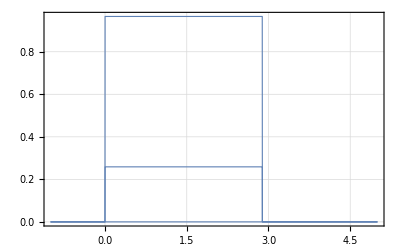

```mathematica
RadPlotOptions[];
Plot[radFld[final, "m", {5,y, 5}], {y, -1, 5}]
```

```mathematica
(* 2 segments of the Halbach array by hand *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 10
mx1 = Cos[φ+dφ/2]
my1 =Sin[φ+dφ/2]
mz1 = 0

(* create first segment, place same shape at z=0, z=R *)
segment1 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment1 = Append[segment1, {segment1[[1]][[1]], R}]

(* Iterate on the variables for the second segment *)
φ += dφ
mx2 = Cos[φ+dφ/2]
my2 =Sin[φ+dφ/2]
mz2 = 0

(* add new segments at z=0, z=R *)
segment2 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment2 = Append[segment2, {segment2[[1]][[1]], R}]
Print["segment is now: ", segment2]

(* first attempt to create segments, then define group for segments *)
s1 = radObjMltExtPgn[segment1, {mx1, my1, mz1}]
s2 = radObjMltExtPgn[segment2, {mx2, my2, mz2}]
group = radObjCnt[{s1, s2}]


(* color the object *)
radObjDrwAtr[group, {0, 0.5, 0.8}]

(* plot + show the object *)
RadPlot3DOptions[];
s = radObjDrw[group];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

π/6

1/(√2)

1/(√2)

0

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0}}

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

segment is now: {{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

6

8

9

9

-Graphics3D-

```mathematica
(* Plot the magnetic field's x-component *)
```

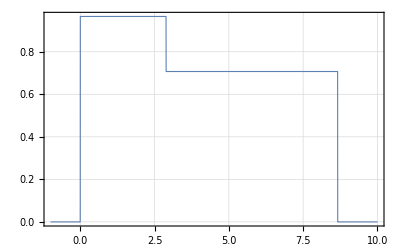

```mathematica
RadPlotOptions[];
Plot[radFld[group, "mx", {5,y, 5}], {y, -1, 10}]
```

```mathematica
(* Draw all 12 segments of the array, outward pointing magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[φ+dφ/2];
my =Sin[φ+dφ/2];
mz = 0;

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

25.4

10

-Graphics3D-

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

35

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the magnetic field to demonstrate spatial rotation *)
```

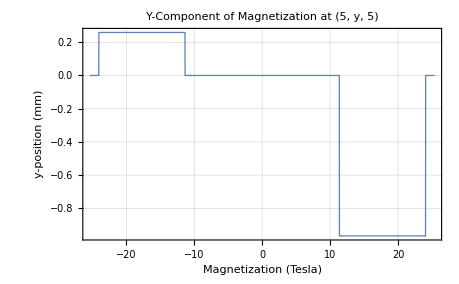

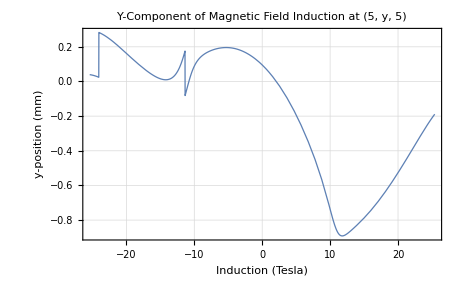

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "my", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetization at (5, y, 5)", AxesLabel->{"Magnetization (Tesla)", "y-position (mm)"}]
Plot[radFld[halbach, "By", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetic Field Induction at (5, y, 5)", AxesLabel->{"Induction (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

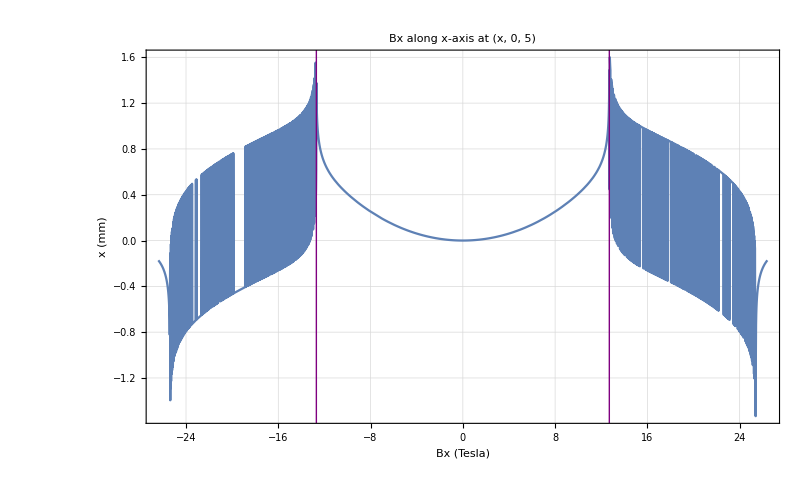

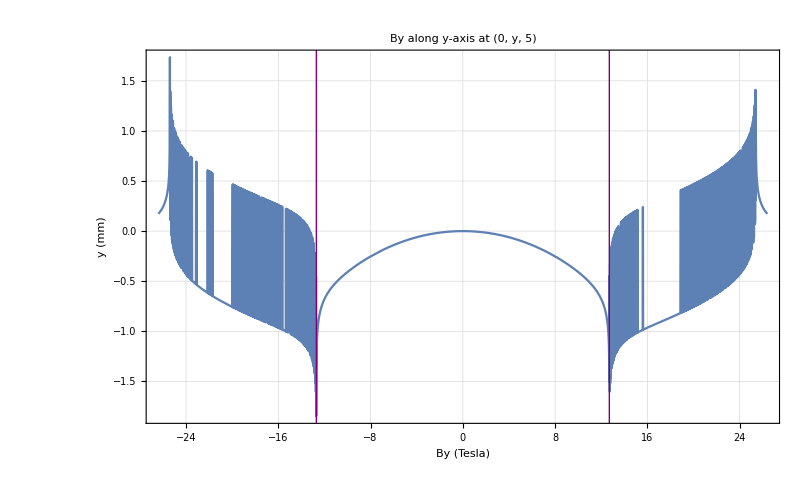

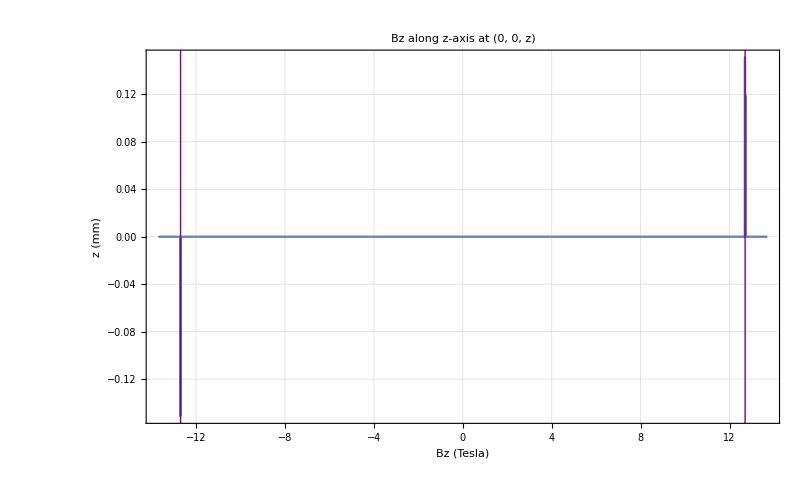

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "Bx", {x, 0, 5}], {x, -R -1, R + 1}, PlotLabel->"Bx along x-axis at (x, 0, 5)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "By", {0, y, 5}], {y, -R -1, R + 1}, PlotLabel->"By along y-axis at (0, y, 5)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "Bz", {0, 0, z}], {z, -R/2  - 1, R/2 + 1}, PlotLabel->"Bz along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

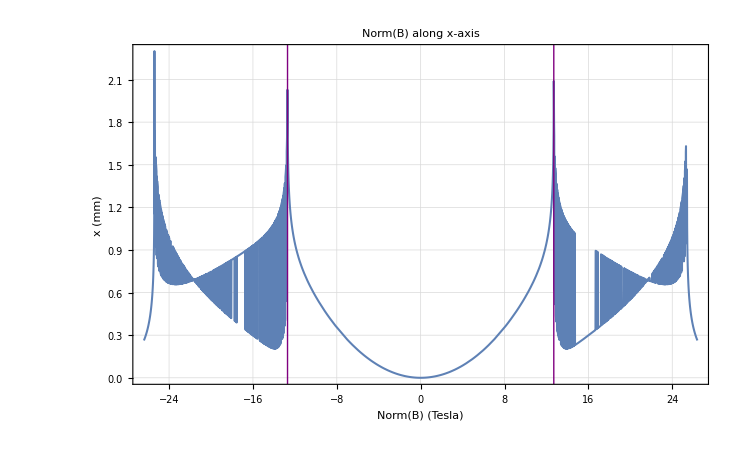

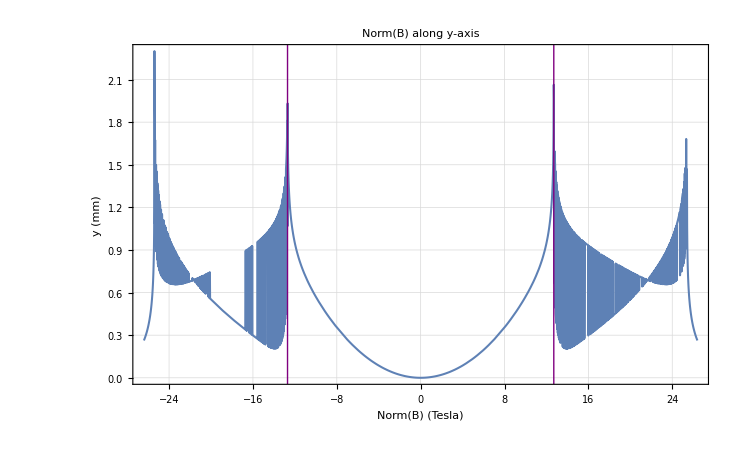

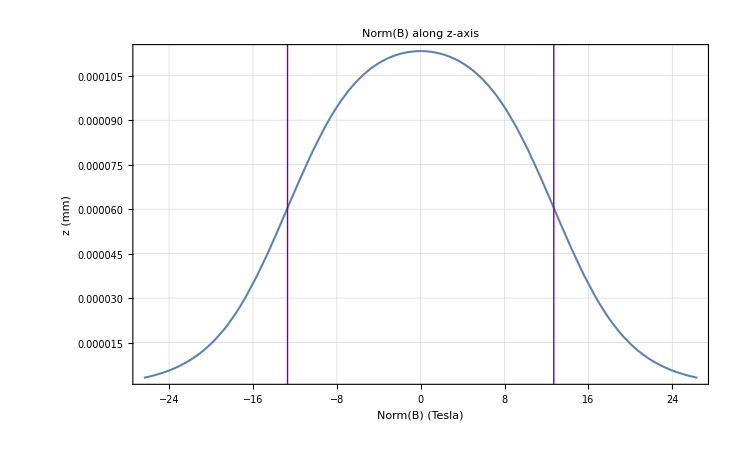

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "hx", {x, y, z}];
by = radFld[halbach, "hy", {x, y, z}];
bz = radFld[halbach, "hz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 5], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 5], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-R/2,-10},{-R/2,10}}],Line[{{R/2,-10},{R/2,10}}]}]
```

```mathematica
(* Visualize magnetization*)
```

```mathematica
(* initialize variables *)
xStart = -R;
yStart = -R;
zPos = 0
m=50;
mxMatrix = {};
myMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
mxMatrix=Append[mxMatrix, {}];
For[j=1, j≤ m, j++,
mxMatrix[[i]]=Append[mxMatrix[[i]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "mx", {xStart + (2*R)/(m-1)*(i-1), yStart + (2*R)/(m-1)*(j-1), zPos}]];
];
];

For[i=1, i≤ m, i++, 
myMatrix=Append[myMatrix, {}];
For[j=1, j≤ m, j++,
myMatrix[[i]]=Append[myMatrix[[i]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "my", {xStart + (2*R)/(m-1)*(i-1), yStart + (2*R)/(m-1)*(j-1), zPos}]];
];
];

Print["mxMatrix: ", MatrixForm[mxMatrix]]
Print["myMatrix: ", MatrixForm[myMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/m_matrix"];
Export["mxMatrix.fits",mxMatrix];
Export["myMatrix.fits",myMatrix];
```

0

mxMatrix: (1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17)

myMatrix: (1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17)

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a data file *)
```

```mathematica
(* initialize variables *)
xStart = -R/2;
yStart = -R/2;
zStart = -R/2;
m=50;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};
bMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ m, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "hx", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ m, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ m, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "hy", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ m, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "hz", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ m, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ m, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
norm[xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)]]
];
];
];

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bMatrix=Append[bMatrix, {}];
For[j=1, j≤ m, j++,
bMatrix[[i]]=Append[bMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bMatrix[[i]][[j]]=Append[bMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "h", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]
Print["bMatrix: ", MatrixForm[bMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/bmatrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
Export["bMatrix.fits",bMatrix];
```

bxMatrix: ((0.248943
0.273592
0.297542
0.320203
0.341144
0.36012
0.377047
0.391969
0.405008
0.416331
0.426121
0.434558
0.441812
0.448034
0.453357
0.457896
0.461748
0.464995
0.467704
0.469933
0.471726
0.47312
0.474143
0.474813
0.475145
0.475145
0.474813
0.474143
0.47312
0.471726
0.469933
0.467704
0.464995
0.461748
0.457896
0.453357
0.448034
0.441812
0.434558
0.426121
0.416331
0.405008
0.391969
0.377047
0.36012
0.341144
0.320203
0.297542
0.273592
0.248943) | (0.249253
0.274089
0.298203
0.320986
0.342006
0.361021
0.377957
0.392867
0.405883
0.417179
0.42694
0.43535
0.44258
0.44878
0.454085
0.458608
0.462447
0.465683
0.468384
0.470606
0.472394
0.473783
0.474802
0.475471
0.475802
0.475802
0.475471
0.474802
0.473783
0.472394
0.470606
0.468384
0.465683
0.462447
0.458608
0.454085
0.44878
0.44258
0.43535
0.42694
0.417179
0.405883
0.392867
0.377957
0.361021
0.342006
0.320986
0.298203
0.274089
0.249253) | (0.250299
0.275753
0.3004
0.32358
0.344846
0.363975
0.380931
0.395801
0.408744
0.419952
0.429626
0.437953
0.445109
0.451245
0.456495
0.460971
0.464772
0.467976
0.470651
0.472852
0.474624
0.476001
0.477011
0.477674
0.478002
0.478002
0.477674
0.477011
0.476001
0.474624
0.472852
0.470651
0.467976
0.464772
0.460971
0.456495
0.451245
0.445109
0.437953
0.429626
0.419952
0.408744
0.395801
0.380931
0.363975
0.344846
0.32358
0.3004
0.275753
0.250299) | (0.25227
0.278891
0.30453
0.328422
0.350108
0.369417
0.386385
0.401166
0.413971
0.425025
0.434545
0.442732
0.449763
0.455792
0.460951
0.465352
0.469089
0.472241
0.474874
0.477042
0.478787
0.480144
0.48114
0.481793
0.482117
0.482117
0.481793
0.48114
0.480144
0.478787
0.477042
0.474874
0.472241
0.469089
0.465352
0.460951
0.455792
0.449763
0.442732
0.434545
0.425025
0.413971
0.401166
0.386385
0.369417
0.350108
0.328422
0.30453
0.278891
0.25227) | (0.255364
0.283894
0.311109
0.33607
0.358333
0.377845
0.394776
0.40939
0.421971
0.432789
0.442086
0.450071
0.456927
0.462806
0.46784
0.472137
0.475788
0.478871
0.481447
0.483569
0.485279
0.486609
0.487585
0.488226
0.488544
0.488544
0.488226
0.487585
0.486609
0.485279
0.483569
0.481447
0.478871
0.475788
0.472137
0.46784
0.462806
0.456927
0.450071
0.442086
0.432789
0.421971
0.40939
0.394776
0.377845
0.358333
0.33607
0.311109
0.283894
0.255364) | (0.259782
0.291278
0.320824
0.347226
0.370151
0.3898
0.406573
0.420894
0.433138
0.443626
0.452621
0.460343
0.466973
0.472664
0.47754
0.481708
0.485253
0.488249
0.490756
0.492822
0.494488
0.495785
0.496738
0.497363
0.497673
0.497673
0.497363
0.496738
0.495785
0.494488
0.492822
0.490756
0.488249
0.485253
0.481708
0.47754
0.472664
0.466973
0.460343
0.452621
0.443626
0.433138
0.420894
0.406573
0.3898
0.370151
0.347226
0.320824
0.291278
0.259782) | (0.265693
0.301776
0.334626
0.362752
0.38624
0.405801
0.422192
0.436031
0.447795
0.457843
0.466456
0.473852
0.480211
0.485677
0.490368
0.494383
0.497805
0.500701
0.503127
0.505129
0.506745
0.508004
0.508929
0.509537
0.509838
0.509838
0.509537
0.508929
0.508004
0.506745
0.505129
0.503127
0.500701
0.497805
0.494383
0.490368
0.485677
0.480211
0.473852
0.466456
0.457843
0.447795
0.436031
0.422192
0.405801
0.38624
0.362752
0.334626
0.301776
0.265693) | (0.273185
0.316594
0.353902
0.383657
0.40721
0.426205
0.441854
0.454964
0.466077
0.47557
0.483719
0.490734
0.49678
0.501989
0.506472
0.510318
0.513603
0.516387
0.518724
0.520656
0.522216
0.523434
0.524329
0.524917
0.525209
0.525209
0.524917
0.524329
0.523434
0.522216
0.520656
0.518724
0.516387
0.513603
0.510318
0.506472
0.501989
0.49678
0.490734
0.483719
0.47557
0.466077
0.454964
0.441854
0.426205
0.40721
0.383657
0.353902
0.316594
0.273185) | (0.282157
0.338201
0.380708
0.410865
0.433288
0.450919
0.465338
0.477425
0.487709
0.496536
0.50415
0.510736
0.516436
0.521367
0.525624
0.529289
0.532426
0.535093
0.537335
0.539191
0.540693
0.541865
0.542728
0.543296
0.543577
0.543577
0.543296
0.542728
0.541865
0.540693
0.539191
0.537335
0.535093
0.532426
0.529289
0.525624
0.521367
0.516436
0.510736
0.50415
0.496536
0.487709
0.477425
0.465338
0.450919
0.433288
0.410865
0.380708
0.338201
0.282157) | (0.292104
0.373105
0.417628
0.444402
0.463622
0.47884
0.491492
0.502269
0.511566
0.519636
0.526662
0.532785
0.538119
0.542758
0.546782
0.550258
0.553244
0.555788
0.557933
0.559711
0.561152
0.562279
0.563109
0.563655
0.563926
0.563926
0.563655
0.563109
0.562279
0.561152
0.559711
0.557933
0.555788
0.553244
0.550258
0.546782
0.542758
0.538119
0.532785
0.526662
0.519636
0.511566
0.502269
0.491492
0.47884
0.463622
0.444402
0.417628
0.373105
0.292104) | (0.301708
0.438222
0.464703
0.481454
0.495102
0.506942
0.51739
0.52665
0.534856
0.542118
0.548531
0.55418
0.559143
0.563487
0.567276
0.570564
0.573398
0.575821
0.577867
0.579568
0.580949
0.58203
0.582826
0.583351
0.583611
0.583611
0.583351
0.582826
0.58203
0.580949
0.579568
0.577867
0.575821
0.573398
0.570564
0.567276
0.563487
0.559143
0.55418
0.548531
0.542118
0.534856
0.52665
0.51739
0.506942
0.495102
0.481454
0.464703
0.438222
0.301708) | (0.00216712
-0.0898224
-0.101238
-0.09809
-0.0911038
-0.0830544
-0.0749733
-0.0672938
-0.0601958
-0.0537409
-0.0479327
-0.0427468
-0.0381452
-0.0340852
-0.0305232
-0.0274176
-0.0247299
-0.0224255
-0.0204738
-0.0188483
-0.0175269
-0.0164912
-0.0157269
-0.0152232
-0.0149731
-0.0149731
-0.0152232
-0.0157269
-0.0164912
-0.0175269
-0.0188483
-0.0204738
-0.0224255
-0.0247299
-0.0274176
-0.0305232
-0.0340852
-0.0381452
-0.0427468
-0.0479327
-0.0537409
-0.0601958
-0.0672938
-0.0749733
-0.0830544
-0.0911038
-0.09809
-0.101238
-0.0898224
0.00216712) | (0.00233134
-0.0496838
-0.0736294
-0.0801162
-0.0788294
-0.0742285
-0.0683452
-0.0621393
-0.0560733
-0.0503676
-0.0451194
-0.0403617
-0.0360939
-0.0322976
-0.0289464
-0.0260105
-0.02346
-0.0212666
-0.0194044
-0.0178505
-0.0165853
-0.0155926
-0.0148593
-0.0143758
-0.0141356
-0.0141356
-0.0143758
-0.0148593
-0.0155926
-0.0165853
-0.0178505
-0.0194044
-0.0212666
-0.02346
-0.0260105
-0.0289464
-0.0322976
-0.0360939
-0.0403617
-0.0451194
-0.0503676
-0.0560733
-0.0621393
-0.0683452
-0.0742285
-0.0788294
-0.0801162
-0.0736294
-0.0496838
0.00233134) | (-0.00573009
-0.0456032
-0.0711667
-0.0824868
-0.0850486
-0.0830762
-0.0789677
-0.073988
-0.0687956
-0.0637309
-0.0589657
-0.0545804
-0.0506048
-0.0470413
-0.0438775
-0.0410938
-0.0386672
-0.0365749
-0.0347947
-0.0333068
-0.0320939
-0.0311411
-0.0304368
-0.0299721
-0.0297413
-0.0297413
-0.0299721
-0.0304368
-0.0311411
-0.0320939
-0.0333068
-0.0347947
-0.0365749
-0.0386672
-0.0410938
-0.0438775
-0.0470413
-0.0506048
-0.0545804
-0.0589657
-0.0637309
-0.0687956
-0.073988
-0.0789677
-0.0830762
-0.0850486
-0.0824868
-0.0711667
-0.0456032
-0.00573009) | (-0.0195136
-0.0590591
-0.0864142
-0.100358
-0.105212
-0.104958
-0.10209
-0.0980074
-0.0934747
-0.0889064
-0.0845232
-0.0804378
-0.0767019
-0.0733325
-0.0703274
-0.0676743
-0.0653556
-0.0633522
-0.0616451
-0.0602165
-0.0590507
-0.0581343
-0.0574565
-0.0570092
-0.0567869
-0.0567869
-0.0570092
-0.0574565
-0.0581343
-0.0590507
-0.0602165
-0.0616451
-0.0633522
-0.0653556
-0.0676743
-0.0703274
-0.0733325
-0.0767019
-0.0804378
-0.0845232
-0.0889064
-0.0934747
-0.0980074
-0.10209
-0.104958
-0.105212
-0.100358
-0.0864142
-0.0590591
-0.0195136) | (-0.0345373
-0.0786132
-0.108756
-0.124355
-0.13039
-0.131043
-0.128874
-0.12533
-0.121217
-0.116981
-0.112864
-0.108997
-0.105441
-0.102222
-0.0993434
-0.096797
-0.0945684
-0.0926406
-0.0909964
-0.0896196
-0.0884955
-0.0876115
-0.0869575
-0.0865258
-0.0863113
-0.0863113
-0.0865258
-0.0869575
-0.0876115
-0.0884955
-0.0896196
-0.0909964
-0.0926406
-0.0945684
-0.096797
-0.0993434
-0.102222
-0.105441
-0.108997
-0.112864
-0.116981
-0.121217
-0.12533
-0.128874
-0.131043
-0.13039
-0.124355
-0.108756
-0.0786132
-0.0345373) | (-0.0476315
-0.0982833
-0.131361
-0.147797
-0.154117
-0.154971
-0.152996
-0.149642
-0.145706
-0.141632
-0.137663
-0.133927
-0.13049
-0.127376
-0.124591
-0.122127
-0.11997
-0.118104
-0.116512
-0.11518
-0.114091
-0.113236
-0.112603
-0.112185
-0.111977
-0.111977
-0.112185
-0.112603
-0.113236
-0.114091
-0.11518
-0.116512
-0.118104
-0.11997
-0.122127
-0.124591
-0.127376
-0.13049
-0.133927
-0.137663
-0.141632
-0.145706
-0.149642
-0.152996
-0.154971
-0.154117
-0.147797
-0.131361
-0.0982833
-0.0476315) | (-0.0573608
-0.115787
-0.151278
-0.16758
-0.173346
-0.173765
-0.171525
-0.168034
-0.164047
-0.159974
-0.156037
-0.152351
-0.148973
-0.145921
-0.143198
-0.140792
-0.138688
-0.136871
-0.135322
-0.134026
-0.132968
-0.132137
-0.131522
-0.131116
-0.130915
-0.130915
-0.131116
-0.131522
-0.132137
-0.132968
-0.134026
-0.135322
-0.136871
-0.138688
-0.140792
-0.143198
-0.145921
-0.148973
-0.152351
-0.156037
-0.159974
-0.164047
-0.168034
-0.171525
-0.173765
-0.173346
-0.16758
-0.151278
-0.115787
-0.0573608) | (-0.0631828
-0.130567
-0.167422
-0.182414
-0.186782
-0.186174
-0.183255
-0.179336
-0.175093
-0.170876
-0.166869
-0.163161
-0.159789
-0.15676
-0.154069
-0.151701
-0.149635
-0.147854
-0.146339
-0.145073
-0.144041
-0.14323
-0.142631
-0.142235
-0.142039
-0.142039
-0.142235
-0.142631
-0.14323
-0.144041
-0.145073
-0.146339
-0.147854
-0.149635
-0.151701
-0.154069
-0.15676
-0.159789
-0.163161
-0.166869
-0.170876
-0.175093
-0.179336
-0.183255
-0.186174
-0.186782
-0.182414
-0.167422
-0.130567
-0.0631828) | (-0.0647801
-0.142633
-0.179157
-0.191432
-0.193529
-0.19134
-0.187375
-0.182781
-0.178112
-0.173635
-0.169475
-0.165685
-0.162276
-0.159239
-0.156558
-0.154209
-0.152168
-0.150414
-0.148925
-0.147683
-0.146672
-0.145879
-0.145293
-0.144907
-0.144715
-0.144715
-0.144907
-0.145293
-0.145879
-0.146672
-0.147683
-0.148925
-0.150414
-0.152168
-0.154209
-0.156558
-0.159239
-0.162276
-0.165685
-0.169475
-0.173635
-0.178112
-0.182781
-0.187375
-0.19134
-0.193529
-0.191432
-0.179157
-0.142633
-0.0647801) | (-0.061659
-0.151936
-0.185445
-0.193326
-0.192259
-0.187983
-0.182669
-0.177211
-0.171993
-0.167172
-0.162802
-0.158888
-0.155413
-0.152346
-0.149658
-0.147316
-0.145291
-0.143556
-0.142088
-0.140866
-0.139872
-0.139094
-0.13852
-0.138142
-0.137954
-0.137954
-0.138142
-0.13852
-0.139094
-0.139872
-0.140866
-0.142088
-0.143556
-0.145291
-0.147316
-0.149658
-0.152346
-0.155413
-0.158888
-0.162802
-0.167172
-0.171993
-0.177211
-0.182669
-0.187983
-0.192259
-0.193326
-0.185445
-0.151936
-0.061659) | (-0.0527609
-0.157704
-0.18394
-0.185472
-0.180375
-0.173603
-0.166735
-0.160303
-0.154471
-0.149265
-0.144657
-0.140601
-0.137043
-0.133936
-0.131231
-0.12889
-0.126874
-0.125154
-0.123703
-0.122498
-0.121521
-0.120756
-0.120192
-0.119821
-0.119637
-0.119637
-0.119821
-0.120192
-0.120756
-0.121521
-0.122498
-0.123703
-0.125154
-0.126874
-0.12889
-0.131231
-0.133936
-0.137043
-0.140601
-0.144657
-0.149265
-0.154471
-0.160303
-0.166735
-0.173603
-0.180375
-0.185472
-0.18394
-0.157704
-0.0527609) | (-0.0356509
-0.156675
-0.169058
-0.162127
-0.152319
-0.142843
-0.134368
-0.126956
-0.120518
-0.114934
-0.110093
-0.105896
-0.102258
-0.0991086
-0.0963874
-0.0940444
-0.0920373
-0.0903307
-0.088895
-0.0877058
-0.0867432
-0.0859912
-0.0854377
-0.0850736
-0.084893
-0.084893
-0.0850736
-0.0854377
-0.0859912
-0.0867432
-0.0877058
-0.088895
-0.0903307
-0.0920373
-0.0940444
-0.0963874
-0.0991086
-0.102258
-0.105896
-0.110093
-0.114934
-0.120518
-0.126956
-0.134368
-0.142843
-0.152319
-0.162127
-0.169058
-0.156675
-0.0356509) | (-0.00365125
-0.136178
-0.125429
-0.108425
-0.093798
-0.0817746
-0.0718545
-0.0635844
-0.0566231
-0.0507182
-0.0456809
-0.0413669
-0.0376637
-0.0344821
-0.0317502
-0.0294098
-0.0274132
-0.0257212
-0.0243018
-0.0231288
-0.0221811
-0.0214418
-0.0208982
-0.0205409
-0.0203637
-0.0203637
-0.0205409
-0.0208982
-0.0214418
-0.0221811
-0.0231288
-0.0243018
-0.0257212
-0.0274132
-0.0294098
-0.0317502
-0.0344821
-0.0376637
-0.0413669
-0.0456809
-0.0507182
-0.0566231
-0.0635844
-0.0718545
-0.0817746
-0.093798
-0.108425
-0.125429
-0.136178
-0.00365124) | (0.0748778
-0.0258444
0.0151273
0.041155
0.059546
0.0734511
0.0844133
0.0932944
0.100624
0.106752
0.111922
0.116311
0.120052
0.123247
0.125978
0.128307
0.130288
0.131961
0.133362
0.134517
0.135449
0.136175
0.136708
0.137058
0.137232
0.137232
0.137058
0.136708
0.136175
0.135449
0.134517
0.133362
0.131961
0.130288
0.128307
0.125978
0.123247
0.120052
0.116311
0.111922
0.106752
0.100624
0.0932944
0.0844133
0.0734511
0.059546
0.041155
0.0151273
-0.0258444
0.0748779) | (0.31169
0.432457
0.483072
0.512198
0.532039
0.546735
0.558161
0.567322
0.57482
0.581046
0.586268
0.590679
0.594421
0.597606
0.600318
0.602625
0.604581
0.606231
0.607609
0.608743
0.609657
0.610369
0.610891
0.611233
0.611403
0.611403
0.611233
0.610891
0.610369
0.609657
0.608743
0.607609
0.606231
0.604581
0.602625
0.600318
0.597606
0.594421
0.590679
0.586268
0.581046
0.57482
0.567322
0.558161
0.546735
0.532039
0.512198
0.483072
0.432457
0.31169) | (0.223761
0.275159
0.312735
0.338805
0.357721
0.372092
0.383389
0.392489
0.399948
0.40614
0.411328
0.415702
0.419407
0.422554
0.425228
0.4275
0.429422
0.431041
0.432391
0.433502
0.434396
0.43509
0.4356
0.435935
0.4361
0.4361
0.435935
0.4356
0.43509
0.434396
0.433502
0.432391
0.431041
0.429422
0.4275
0.425228
0.422554
0.419407
0.415702
0.411328
0.40614
0.399948
0.392489
0.383389
0.372092
0.357721
0.338805
0.312735
0.275159
0.223761) | (0.182176
0.213293
0.240043
0.261366
0.278127
0.291434
0.302157
0.31092
0.318162
0.324203
0.329277
0.33356
0.337189
0.340271
0.342889
0.34511
0.346989
0.34857
0.349887
0.35097
0.35184
0.352517
0.353013
0.353338
0.3535
0.3535
0.353338
0.353013
0.352517
0.35184
0.35097
0.349887
0.34857
0.346989
0.34511
0.342889
0.340271
0.337189
0.33356
0.329277
0.324203
0.318162
0.31092
0.302157
0.291434
0.278127
0.261366
0.240043
0.213293
0.182176) | (0.155189
0.17709
0.197139
0.214412
0.228857
0.240825
0.250743
0.258997
0.2659
0.271702
0.276599
0.280746
0.284266
0.287258
0.289801
0.291959
0.293785
0.29532
0.296599
0.29765
0.298495
0.299151
0.299632
0.299947
0.300104
0.300104
0.299947
0.299632
0.299151
0.298495
0.29765
0.296599
0.29532
0.293785
0.291959
0.289801
0.287258
0.284266
0.280746
0.276599
0.271702
0.2659
0.258997
0.250743
0.240825
0.228857
0.214412
0.197139
0.17709
0.155189) | (0.13604
0.152924
0.16884
0.18315
0.195623
0.206304
0.215375
0.223055
0.229556
0.235066
0.239744
0.243721
0.247106
0.249989
0.252442
0.254526
0.25629
0.257773
0.259009
0.260024
0.260841
0.261475
0.261939
0.262244
0.262395
0.262395
0.262244
0.261939
0.261475
0.260841
0.260024
0.259009
0.257773
0.25629
0.254526
0.252442
0.249989
0.247106
0.243721
0.239744
0.235066
0.229556
0.223055
0.215375
0.206304
0.195623
0.18315
0.16884
0.152924
0.13604) | (0.12227
0.13628
0.149672
0.161987
0.17298
0.182597
0.190903
0.198028
0.204118
0.209317
0.213753
0.21754
0.220774
0.223533
0.225885
0.227886
0.22958
0.231006
0.232195
0.233172
0.233957
0.234567
0.235015
0.235308
0.235453
0.235453
0.235308
0.235015
0.234567
0.233957
0.233172
0.232195
0.231006
0.22958
0.227886
0.225885
0.223533
0.220774
0.21754
0.213753
0.209317
0.204118
0.198028
0.190903
0.182597
0.17298
0.161987
0.149672
0.13628
0.12227) | (0.112908
0.125451
0.137491
0.14864
0.158673
0.167519
0.175215
0.181856
0.187562
0.192454
0.196645
0.200234
0.203306
0.205933
0.208176
0.210087
0.211707
0.213072
0.214211
0.215147
0.2159
0.216485
0.216914
0.217195
0.217335
0.217335
0.217195
0.216914
0.216485
0.2159
0.215147
0.214211
0.213072
0.211707
0.210087
0.208176
0.205933
0.203306
0.200234
0.196645
0.192454
0.187562
0.181856
0.175215
0.167519
0.158673
0.14864
0.137491
0.125451
0.112908) | (0.107774
0.120076
0.131816
0.142585
0.152182
0.160577
0.167842
0.174096
0.179466
0.184073
0.188025
0.191415
0.194323
0.196814
0.198945
0.200763
0.202306
0.203607
0.204694
0.205587
0.206307
0.206866
0.207276
0.207545
0.207678
0.207678
0.207545
0.207276
0.206866
0.206307
0.205587
0.204694
0.203607
0.202306
0.200763
0.198945
0.196814
0.194323
0.191415
0.188025
0.184073
0.179466
0.174096
0.167842
0.160577
0.152182
0.142585
0.131816
0.120076
0.107774) | (0.107317
0.120817
0.133448
0.14468
0.154374
0.16263
0.169641
0.175603
0.180686
0.185033
0.188759
0.191956
0.194701
0.197057
0.199075
0.200799
0.202264
0.203501
0.204535
0.205386
0.206072
0.206605
0.206996
0.207252
0.207379
0.207379
0.207252
0.206996
0.206605
0.206072
0.205386
0.204535
0.203501
0.202264
0.200799
0.199075
0.197057
0.194701
0.191956
0.188759
0.185033
0.180686
0.175603
0.169641
0.16263
0.154374
0.14468
0.133448
0.120817
0.107317) | (0.112625
0.12945
0.144578
0.157244
0.167547
0.175922
0.182807
0.188543
0.193377
0.197485
0.200996
0.204008
0.206596
0.208819
0.210726
0.212357
0.213746
0.21492
0.215902
0.216711
0.217363
0.21787
0.218242
0.218486
0.218607
0.218607
0.218486
0.218242
0.21787
0.217363
0.216711
0.215902
0.21492
0.213746
0.212357
0.210726
0.208819
0.206596
0.204008
0.200996
0.197485
0.193377
0.188543
0.182807
0.175922
0.167547
0.157244
0.144578
0.12945
0.112625) | (0.125296
0.149022
0.168896
0.183984
0.195238
0.203833
0.210621
0.216143
0.220734
0.224611
0.227917
0.23075
0.233187
0.235283
0.237085
0.238628
0.239943
0.241056
0.241988
0.242757
0.243376
0.243858
0.244212
0.244445
0.24456
0.24456
0.244445
0.244212
0.243858
0.243376
0.242757
0.241988
0.241056
0.239943
0.238628
0.237085
0.235283
0.233187
0.23075
0.227917
0.224611
0.220734
0.216143
0.210621
0.203833
0.195238
0.183984
0.168896
0.149022
0.125296) | (0.146521
0.183338
0.21053
0.228393
0.240399
0.249008
0.255572
0.260816
0.26514
0.268779
0.271881
0.274544
0.276838
0.278815
0.280517
0.281978
0.283225
0.284282
0.285167
0.285897
0.286487
0.286945
0.287282
0.287503
0.287613
0.287613
0.287503
0.287282
0.286945
0.286487
0.285897
0.285167
0.284282
0.283225
0.281978
0.280517
0.278815
0.276838
0.274544
0.271881
0.268779
0.26514
0.260816
0.255572
0.249008
0.240399
0.228393
0.21053
0.183338
0.146521) | (0.174906
0.236036
0.270675
0.289377
0.300903
0.308908
0.314958
0.319793
0.323796
0.327181
0.33008
0.332579
0.334741
0.336609
0.338222
0.339609
0.340794
0.3418
0.342643
0.343339
0.343901
0.344338
0.34466
0.344871
0.344975
0.344975
0.344871
0.34466
0.344338
0.343901
0.343339
0.342643
0.3418
0.340794
0.339609
0.338222
0.336609
0.334741
0.332579
0.33008
0.327181
0.323796
0.319793
0.314958
0.308908
0.300903
0.289377
0.270675
0.236036
0.174906) | (0.20563
0.315647
0.344752
0.35855
0.36742
0.373952
0.379125
0.383401
0.387025
0.390142
0.392843
0.395191
0.397233
0.399007
0.400543
0.401866
0.402999
0.403961
0.404768
0.405434
0.405972
0.40639
0.406698
0.4069
0.407
0.407
0.4069
0.406698
0.40639
0.405972
0.405434
0.404768
0.403961
0.402999
0.401866
0.400543
0.399007
0.397233
0.395191
0.392843
0.390142
0.387025
0.383401
0.379125
0.373952
0.36742
0.35855
0.344752
0.315647
0.20563) | (-0.0722627
-0.185817
-0.190414
-0.187016
-0.182472
-0.178037
-0.173989
-0.170366
-0.167146
-0.164294
-0.161775
-0.159559
-0.157615
-0.155918
-0.154444
-0.153172
-0.152081
-0.151154
-0.150376
-0.149734
-0.149216
-0.148813
-0.148517
-0.148323
-0.148227
-0.148227
-0.148323
-0.148517
-0.148813
-0.149216
-0.149734
-0.150376
-0.151154
-0.152081
-0.153172
-0.154444
-0.155918
-0.157615
-0.159559
-0.161775
-0.164294
-0.167146
-0.170366
-0.173989
-0.178037
-0.182472
-0.187016
-0.190414
-0.185817
-0.0722627) | (-0.0481043
-0.103965
-0.124522
-0.129267
-0.128675
-0.126269
-0.123321
-0.120322
-0.117471
-0.114848
-0.112477
-0.110361
-0.108489
-0.106846
-0.105415
-0.104177
-0.103116
-0.102214
-0.101458
-0.100834
-0.100331
-0.09994
-0.0996531
-0.0994649
-0.0993717
-0.0993717
-0.0994649
-0.0996531
-0.09994
-0.100331
-0.100834
-0.101458
-0.102214
-0.103116
-0.104177
-0.105415
-0.106846
-0.108489
-0.110361
-0.112477
-0.114848
-0.117471
-0.120322
-0.123321
-0.126269
-0.128675
-0.129267
-0.124522
-0.103965
-0.0481043) | (-0.0275664
-0.0576172
-0.0751965
-0.082245
-0.0837369
-0.0826689
-0.0805144
-0.0779767
-0.0753932
-0.0729252
-0.0706466
-0.0685869
-0.066752
-0.0651353
-0.0637244
-0.0625039
-0.0614576
-0.06057
-0.0598264
-0.0592137
-0.0587205
-0.0583374
-0.0580567
-0.0578728
-0.0577817
-0.0577817
-0.0578728
-0.0580567
-0.0583374
-0.0587205
-0.0592137
-0.0598264
-0.06057
-0.0614576
-0.0625039
-0.0637244
-0.0651353
-0.066752
-0.0685869
-0.0706466
-0.0729252
-0.0753932
-0.0779767
-0.0805144
-0.0826689
-0.0837369
-0.082245
-0.0751965
-0.0576172
-0.0275664) | (-0.00952957
-0.0265255
-0.0383493
-0.0442575
-0.0460074
-0.0453842
-0.043566
-0.0412331
-0.0387585
-0.0363403
-0.0340788
-0.0320201
-0.0301798
-0.0285568
-0.0271409
-0.0259178
-0.0248714
-0.0239855
-0.0232451
-0.0226365
-0.0221476
-0.0217685
-0.0214912
-0.0213097
-0.0212199
-0.0212199
-0.0213097
-0.0214912
-0.0217685
-0.0221476
-0.0226365
-0.0232451
-0.0239855
-0.0248714
-0.0259178
-0.0271409
-0.0285568
-0.0301798
-0.0320201
-0.0340788
-0.0363403
-0.0387585
-0.0412331
-0.043566
-0.0453842
-0.0460074
-0.0442575
-0.0383493
-0.0265255
-0.00952957) | (0.00701669
-0.00220604
-0.0090206
-0.0125988
-0.0134591
-0.0125208
-0.0105725
-0.00815534
-0.00560341
-0.00310941
-0.000776886
0.00134467
0.00323769
0.0049029
0.00635105
0.00759778
0.00866064
0.00955721
0.010304
0.0109161
0.0114063
0.0117855
0.0120623
0.0122433
0.0123327
0.0123327
0.0122433
0.0120623
0.0117855
0.0114063
0.0109161
0.010304
0.00955721
0.00866064
0.00759778
0.00635105
0.0049029
0.00323769
0.00134467
-0.000776886
-0.00310941
-0.00560341
-0.00815534
-0.0105725
-0.0125208
-0.0134591
-0.0125988
-0.0090206
-0.00220604
0.00701669) | (0.0228271
0.0188807
0.0161224
0.0151079
0.0157183
0.0175007
0.0199705
0.0227443
0.0255614
0.0282623
0.0307591
0.0330111
0.0350066
0.0367511
0.0382596
0.0395513
0.0406469
0.0415668
0.0423297
0.0429525
0.0434495
0.0438329
0.0441121
0.0442944
0.0443843
0.0443843
0.0442944
0.0441121
0.0438329
0.0434495
0.0429525
0.0423297
0.0415668
0.0406469
0.0395513
0.0382596
0.0367511
0.0350066
0.0330111
0.0307591
0.0282623
0.0255614
0.0227443
0.0199705
0.0175007
0.0157183
0.0151079
0.0161224
0.0188807
0.0228271) | (0.0384274
0.0384755
0.0390973
0.0405949
0.0429416
0.0459031
0.0491901
0.0525507
0.0558036
0.0588357
0.0615873
0.0640359
0.0661828
0.0680432
0.0696393
0.0709967
0.0721408
0.0730959
0.073884
0.0745244
0.0750336
0.075425
0.0757093
0.0758945
0.0759858
0.0759858
0.0758945
0.0757093
0.075425
0.0750336
0.0745244
0.073884
0.0730959
0.0721408
0.0709967
0.0696393
0.0680432
0.0661828
0.0640359
0.0615873
0.0588357
0.0558036
0.0525507
0.0491901
0.0459031
0.0429416
0.0405949
0.0390973
0.0384755
0.0384274) | (0.0541677
0.0575327
0.0611202
0.0650374
0.0692427
0.0735916
0.077908
0.0820372
0.0858695
0.0893421
0.0924301
0.095136
0.0974793
0.0994889
0.101198
0.10264
0.103847
0.104848
0.105669
0.106334
0.10686
0.107262
0.107554
0.107744
0.107837
0.107837
0.107744
0.107554
0.107262
0.10686
0.106334
0.105669
0.104848
0.103847
0.10264
0.101198
0.0994889
0.0974793
0.095136
0.0924301
0.0893421
0.0858695
0.0820372
0.077908
0.0735916
0.0692427
0.0650374
0.0611202
0.0575327
0.0541677) | (0.0702681
0.0766033
0.0829317
0.089208
0.0953406
0.101212
0.106707
0.111742
0.116268
0.120271
0.123763
0.126778
0.129356
0.131544
0.133387
0.134929
0.136211
0.137267
0.138129
0.138823
0.139369
0.139787
0.140088
0.140283
0.14038
0.14038
0.140283
0.140088
0.139787
0.139369
0.138823
0.138129
0.137267
0.136211
0.134929
0.133387
0.131544
0.129356
0.126778
0.123763
0.120271
0.116268
0.111742
0.106707
0.101212
0.0953406
0.089208
0.0829317
0.0766033
0.0702681) | (0.0868541
0.096009
0.104984
0.113605
0.12172
0.129208
0.135989
0.14203
0.147334
0.151934
0.155884
0.159248
0.16209
0.164478
0.166472
0.168127
0.169493
0.170612
0.17152
0.172246
0.172817
0.17325
0.173563
0.173765
0.173864
0.173864
0.173765
0.173563
0.17325
0.172817
0.172246
0.17152
0.170612
0.169493
0.168127
0.166472
0.164478
0.16209
0.159248
0.155884
0.151934
0.147334
0.14203
0.135989
0.129208
0.12172
0.113605
0.104984
0.096009
0.0868541) | (0.103985
0.115934
0.127552
0.138548
0.148702
0.157879
0.166021
0.173136
0.179276
0.184522
0.188965
0.192704
0.195831
0.198434
0.200589
0.202366
0.203822
0.205008
0.205965
0.206727
0.207323
0.207774
0.208099
0.208308
0.208411
0.208411
0.208308
0.208099
0.207774
0.207323
0.206727
0.205965
0.205008
0.203822
0.202366
0.200589
0.198434
0.195831
0.192704
0.188965
0.184522
0.179276
0.173136
0.166021
0.157879
0.148702
0.138548
0.127552
0.115934
0.103985)
(0.266054
0.293053
0.319228
0.343893
0.366567
0.387
0.405129
0.421036
0.434882
0.446868
0.457207
0.466103
0.473741
0.480287
0.485884
0.490654
0.494701
0.498111
0.500957
0.503297
0.50518
0.506644
0.507717
0.508421
0.508769
0.508769
0.508421
0.507717
0.506644
0.50518
0.503297
0.500957
0.498111
0.494701
0.490654
0.485884
0.480287
0.473741
0.466103
0.457207
0.446868
0.434882
0.421036
0.405129
0.387
0.366567
0.343893
0.319228
0.293053
0.266054) | (0.265713
0.292514
0.318517
0.343052
0.365644
0.386036
0.404158
0.420076
0.433945
0.445959
0.456327
0.46525
0.472913
0.47948
0.485095
0.489881
0.493941
0.497362
0.500216
0.502564
0.504452
0.50592
0.506996
0.507702
0.508051
0.508051
0.507702
0.506996
0.50592
0.504452
0.502564
0.500216
0.497362
0.493941
0.489881
0.485095
0.47948
0.472913
0.46525
0.456327
0.445959
0.433945
0.420076
0.404158
0.386036
0.365644
0.343052
0.318517
0.292514
0.265713) | (0.266128
0.293153
0.319349
0.344029
0.366712
0.387147
0.405278
0.421184
0.435029
0.447015
0.457354
0.466249
0.473887
0.480433
0.48603
0.4908
0.494847
0.498258
0.501104
0.503445
0.505328
0.506791
0.507864
0.508568
0.508917
0.508917
0.508568
0.507864
0.506791
0.505328
0.503445
0.501104
0.498258
0.494847
0.4908
0.48603
0.480433
0.473887
0.466249
0.457354
0.447015
0.435029
0.421184
0.405278
0.387147
0.366712
0.344029
0.319349
0.293153
0.266128) | (0.267545
0.295314
0.322149
0.347296
0.370265
0.390834
0.40899
0.424854
0.438622
0.450519
0.460768
0.46958
0.477144
0.483626
0.489169
0.493894
0.497903
0.501283
0.504104
0.506425
0.508293
0.509744
0.510809
0.511507
0.511853
0.511853
0.511507
0.510809
0.509744
0.508293
0.506425
0.504104
0.501283
0.497903
0.493894
0.489169
0.483626
0.477144
0.46958
0.460768
0.450519
0.438622
0.424854
0.40899
0.390834
0.370265
0.347296
0.322149
0.295314
0.267545) | (0.270248
0.299443
0.327478
0.353474
0.376937
0.397716
0.415891
0.431666
0.445293
0.457032
0.467127
0.475799
0.48324
0.489617
0.495072
0.499723
0.503672
0.507002
0.509783
0.512072
0.513914
0.515347
0.516398
0.517087
0.517429
0.517429
0.517087
0.516398
0.515347
0.513914
0.512072
0.509783
0.507002
0.503672
0.499723
0.495072
0.489617
0.48324
0.475799
0.467127
0.457032
0.445293
0.431666
0.415891
0.397716
0.376937
0.353474
0.327478
0.299443
0.270248) | (0.27456
0.306118
0.33608
0.363359
0.387502
0.408522
0.426669
0.442276
0.455678
0.467181
0.477054
0.485528
0.492798
0.49903
0.504364
0.508915
0.512782
0.516046
0.518773
0.521019
0.522828
0.524235
0.525267
0.525945
0.526281
0.526281
0.525945
0.525267
0.524235
0.522828
0.521019
0.518773
0.516046
0.512782
0.508915
0.504364
0.49903
0.492798
0.485528
0.477054
0.467181
0.455678
0.442276
0.426669
0.408522
0.387502
0.363359
0.33608
0.306118
0.27456) | (0.280822
0.316114
0.348954
0.37796
0.402879
0.42407
0.442066
0.45738
0.470447
0.481624
0.491203
0.499421
0.506475
0.512526
0.51771
0.522138
0.525905
0.529087
0.531748
0.533942
0.53571
0.537086
0.538096
0.538759
0.539088
0.539088
0.538759
0.538096
0.537086
0.53571
0.533942
0.531748
0.529087
0.525905
0.522138
0.51771
0.512526
0.506475
0.499421
0.491203
0.481624
0.470447
0.45738
0.442066
0.42407
0.402879
0.37796
0.348954
0.316114
0.280822) | (0.289372
0.330565
0.367502
0.398537
0.424092
0.4452
0.462811
0.477648
0.490245
0.500998
0.510209
0.518117
0.524913
0.530752
0.535761
0.540047
0.543698
0.546786
0.549372
0.551506
0.553227
0.554567
0.555552
0.556199
0.556519
0.556519
0.556199
0.555552
0.554567
0.553227
0.551506
0.549372
0.546786
0.543698
0.540047
0.535761
0.530752
0.524913
0.518117
0.510209
0.500998
0.490245
0.477648
0.462811
0.4452
0.424092
0.398537
0.367502
0.330565
0.289372) | (0.300472
0.351366
0.39374
0.42653
0.452088
0.472585
0.489448
0.503572
0.515545
0.525771
0.534547
0.542097
0.548601
0.554202
0.559018
0.563147
0.56667
0.569655
0.572159
0.574226
0.575896
0.577198
0.578154
0.578783
0.579095
0.579095
0.578783
0.578154
0.577198
0.575896
0.574226
0.572159
0.569655
0.56667
0.563147
0.559018
0.554202
0.548601
0.542097
0.534547
0.525771
0.515545
0.503572
0.489448
0.472585
0.452088
0.42653
0.39374
0.351366
0.300472) | (0.314098
0.382425
0.430396
0.463038
0.487168
0.506219
0.521867
0.535016
0.546213
0.555822
0.564105
0.571261
0.577448
0.582793
0.587403
0.591366
0.594754
0.597631
0.600047
0.602045
0.60366
0.604921
0.605848
0.606457
0.60676
0.60676
0.606457
0.605848
0.604921
0.60366
0.602045
0.600047
0.597631
0.594754
0.591366
0.587403
0.582793
0.577448
0.571261
0.564105
0.555822
0.546213
0.535016
0.521867
0.506219
0.487168
0.463038
0.430396
0.382425
0.314098) | (0.329277
0.43372
0.479396
0.506867
0.527356
0.543973
0.557939
0.56988
0.58018
0.589108
0.596863
0.603604
0.609462
0.614545
0.618943
0.622735
0.625986
0.628752
0.631078
0.633006
0.634565
0.635784
0.63668
0.63727
0.637562
0.637562
0.63727
0.63668
0.635784
0.634565
0.633006
0.631078
0.628752
0.625986
0.622735
0.618943
0.614545
0.609462
0.603604
0.596863
0.589108
0.58018
0.56988
0.557939
0.543973
0.527356
0.506867
0.479396
0.43372
0.329277) | (0.0361275
-0.0933459
-0.0785166
-0.0626934
-0.0478334
-0.0343895
-0.0224106
-0.0118104
-0.00246377
0.00575858
0.012978
0.0193042
0.0248353
0.0296578
0.0338476
0.0374711
0.0405857
0.043241
0.0454792
0.0473357
0.04884
0.050016
0.0508821
0.051452
0.0517348
0.0517348
0.051452
0.0508821
0.050016
0.04884
0.0473357
0.0454792
0.043241
0.0405857
0.0374711
0.0338476
0.0296578
0.0248353
0.0193042
0.012978
0.00575858
-0.00246377
-0.0118104
-0.0224106
-0.0343895
-0.0478334
-0.0626934
-0.0785166
-0.0933459
0.0361275) | (0.0384637
-0.0294238
-0.0445917
-0.0410443
-0.0320988
-0.0219224
-0.0119457
-0.00267034
0.00574844
0.0132929
0.0200011
0.0259327
0.0311537
0.0357291
0.0397202
0.0431829
0.046167
0.0487163
0.0508687
0.0526565
0.0541068
0.0552414
0.0560777
0.0566282
0.0569014
0.0569014
0.0566282
0.0560777
0.0552414
0.0541068
0.0526565
0.0508687
0.0487163
0.046167
0.0431829
0.0397202
0.0357291
0.0311537
0.0259327
0.0200011
0.0132929
0.00574844
-0.00267034
-0.0119457
-0.0219224
-0.0320988
-0.0410443
-0.0445917
-0.0294238
0.0384637) | (0.0232037
-0.0291257
-0.0532314
-0.0573498
-0.0529352
-0.0454707
-0.0372162
-0.0290997
-0.0214996
-0.0145565
-0.00830405
-0.00272623
0.00221486
0.00656583
0.0103751
0.0136895
0.0165522
0.0190023
0.0210739
0.0227966
0.0241954
0.0252904
0.026098
0.0266298
0.0268937
0.0268937
0.0266298
0.026098
0.0252904
0.0241954
0.0227966
0.0210739
0.0190023
0.0165522
0.0136895
0.0103751
0.00656583
0.00221486
-0.00272623
-0.00830405
-0.0145565
-0.0214996
-0.0290997
-0.0372162
-0.0454707
-0.0529352
-0.0573498
-0.0532314
-0.0291257
0.0232037) | (-0.00235466
-0.0608743
-0.0901807
-0.0982473
-0.0965566
-0.0909242
-0.0839225
-0.0766897
-0.0697342
-0.0632764
-0.057399
-0.0521176
-0.0474149
-0.0432582
-0.0396087
-0.0364264
-0.033673
-0.0313134
-0.0293161
-0.0276539
-0.0263033
-0.0252454
-0.024465
-0.0239509
-0.0236957
-0.0236957
-0.0239509
-0.024465
-0.0252454
-0.0263033
-0.0276539
-0.0293161
-0.0313134
-0.033673
-0.0364264
-0.0396087
-0.0432582
-0.0474149
-0.0521176
-0.057399
-0.0632764
-0.0697342
-0.0766897
-0.0839225
-0.0909242
-0.0965566
-0.0982473
-0.0901807
-0.0608743
-0.00235466) | (-0.0273121
-0.0989424
-0.132324
-0.141967
-0.141431
-0.13672
-0.130436
-0.123758
-0.117236
-0.111122
-0.105522
-0.100469
-0.0959564
-0.0919588
-0.0884434
-0.0853744
-0.0827168
-0.0804376
-0.0785073
-0.0769001
-0.0755938
-0.0745703
-0.0738152
-0.0733177
-0.0730707
-0.0730707
-0.0733177
-0.0738152
-0.0745703
-0.0755938
-0.0769001
-0.0785073
-0.0804376
-0.0827168
-0.0853744
-0.0884434
-0.0919588
-0.0959564
-0.100469
-0.105522
-0.111122
-0.117236
-0.123758
-0.130436
-0.13672
-0.141431
-0.141967
-0.132324
-0.0989424
-0.0273121) | (-0.0474761
-0.135264
-0.170546
-0.179795
-0.179115
-0.174505
-0.168418
-0.16196
-0.155649
-0.149729
-0.144304
-0.139407
-0.135032
-0.131157
-0.127749
-0.124774
-0.122197
-0.119988
-0.118117
-0.116559
-0.115293
-0.114301
-0.113569
-0.113087
-0.112848
-0.112848
-0.113087
-0.113569
-0.114301
-0.115293
-0.116559
-0.118117
-0.119988
-0.122197
-0.124774
-0.127749
-0.131157
-0.135032
-0.139407
-0.144304
-0.149729
-0.155649
-0.16196
-0.168418
-0.174505
-0.179115
-0.179795
-0.170546
-0.135264
-0.0474761) | (-0.0624219
-0.169562
-0.203479
-0.210468
-0.208544
-0.203328
-0.196972
-0.19042
-0.184109
-0.178238
-0.172887
-0.168075
-0.163789
-0.16
-0.156674
-0.153773
-0.151265
-0.149115
-0.147296
-0.145782
-0.144553
-0.14359
-0.142879
-0.142411
-0.142179
-0.142179
-0.142411
-0.142879
-0.14359
-0.144553
-0.145782
-0.147296
-0.149115
-0.151265
-0.153773
-0.156674
-0.16
-0.163789
-0.168075
-0.172887
-0.178238
-0.184109
-0.19042
-0.196972
-0.203328
-0.208544
-0.210468
-0.203479
-0.169562
-0.0624219) | (-0.0726191
-0.203478
-0.231523
-0.234471
-0.230357
-0.223935
-0.216909
-0.209992
-0.203495
-0.197546
-0.192182
-0.187393
-0.183151
-0.179417
-0.176149
-0.173307
-0.170854
-0.168756
-0.166982
-0.165508
-0.164311
-0.163374
-0.162683
-0.162228
-0.162002
-0.162002
-0.162228
-0.162683
-0.163374
-0.164311
-0.165508
-0.166982
-0.168756
-0.170854
-0.173307
-0.176149
-0.179417
-0.183151
-0.187393
-0.192182
-0.197546
-0.203495
-0.209992
-0.216909
-0.223935
-0.230357
-0.234471
-0.231523
-0.203478
-0.0726191) | (-0.0785387
-0.238547
-0.254968
-0.252235
-0.245125
-0.237003
-0.228983
-0.221485
-0.214656
-0.208529
-0.203081
-0.198267
-0.194035
-0.190331
-0.187105
-0.184309
-0.181902
-0.179847
-0.178114
-0.176674
-0.175508
-0.174595
-0.173923
-0.17348
-0.173261
-0.173261
-0.17348
-0.173923
-0.174595
-0.175508
-0.176674
-0.178114
-0.179847
-0.181902
-0.184309
-0.187105
-0.190331
-0.194035
-0.198267
-0.203081
-0.208529
-0.214656
-0.221485
-0.228983
-0.237003
-0.245125
-0.252235
-0.254968
-0.238547
-0.0785387) | (-0.0804711
-0.274797
-0.273535
-0.263732
-0.252976
-0.242778
-0.233533
-0.225306
-0.218049
-0.211679
-0.206104
-0.201234
-0.196991
-0.193302
-0.190105
-0.187346
-0.184979
-0.182964
-0.181267
-0.179861
-0.178722
-0.177833
-0.177178
-0.176747
-0.176533
-0.176533
-0.176747
-0.177178
-0.177833
-0.178722
-0.179861
-0.181267
-0.182964
-0.184979
-0.187346
-0.190105
-0.193302
-0.196991
-0.201234
-0.206104
-0.211679
-0.218049
-0.225306
-0.233533
-0.242778
-0.252976
-0.263732
-0.273535
-0.274797
-0.0804711) | (0.404403
0.656526
0.679604
0.697469
0.712311
0.724798
0.735376
0.744391
0.752109
0.758743
0.76446
0.769395
0.773658
0.777338
0.780509
0.783234
0.785563
0.787541
0.789203
0.790577
0.791688
0.792555
0.793193
0.793613
0.793821
0.793821
0.793613
0.793193
0.792555
0.791688
0.790577
0.789203
0.787541
0.785563
0.783234
0.780509
0.777338
0.773658
0.769395
0.76446
0.758743
0.752109
0.744391
0.735376
0.724798
0.712311
0.697469
0.679604
0.656526
0.404403) | (0.409842
0.628612
0.673712
0.700001
0.719001
0.73374
0.745594
0.755345
0.763488
0.770359
0.776201
0.78119
0.785463
0.789129
0.792271
0.79496
0.797251
0.799191
0.800816
0.802158
0.803242
0.804086
0.804707
0.805115
0.805318
0.805318
0.805115
0.804707
0.804086
0.803242
0.802158
0.800816
0.799191
0.797251
0.79496
0.792271
0.789129
0.785463
0.78119
0.776201
0.770359
0.763488
0.755345
0.745594
0.73374
0.719001
0.700001
0.673712
0.628612
0.409842) | (0.416375
0.609381
0.672691
0.706516
0.729075
0.745658
0.75852
0.768834
0.77729
0.784326
0.790243
0.795254
0.799518
0.803154
0.806258
0.808904
0.811152
0.81305
0.814637
0.815945
0.817
0.817821
0.818425
0.818821
0.819017
0.819017
0.818821
0.818425
0.817821
0.817
0.815945
0.814637
0.81305
0.811152
0.808904
0.806258
0.803154
0.799518
0.795254
0.790243
0.784326
0.77729
0.768834
0.75852
0.745658
0.729075
0.706516
0.672691
0.609381
0.416375) | (0.40617
0.573718
0.645378
0.683304
0.707809
0.725389
0.738782
0.749377
0.757971
0.765061
0.770982
0.775967
0.780188
0.783774
0.786823
0.789415
0.791611
0.793462
0.795007
0.796279
0.797303
0.7981
0.798684
0.799068
0.799258
0.799258
0.799068
0.798684
0.7981
0.797303
0.796279
0.795007
0.793462
0.791611
0.789415
0.786823
0.783774
0.780188
0.775967
0.770982
0.765061
0.757971
0.749377
0.738782
0.725389
0.707809
0.683304
0.645378
0.573718
0.40617) | (0.329055
0.434497
0.495333
0.531362
0.555433
0.572882
0.586206
0.596737
0.605259
0.61227
0.618108
0.62301
0.627148
0.630655
0.633631
0.636156
0.638291
0.640087
0.641585
0.642816
0.643807
0.644577
0.645142
0.645512
0.645696
0.645696
0.645512
0.645142
0.644577
0.643807
0.642816
0.641585
0.640087
0.638291
0.636156
0.633631
0.630655
0.627148
0.62301
0.618108
0.61227
0.605259
0.596737
0.586206
0.572882
0.555433
0.531362
0.495333
0.434497
0.329055) | (0.247673
0.303203
0.345541
0.375443
0.397089
0.41339
0.426081
0.436214
0.444457
0.451256
0.456921
0.461678
0.465693
0.469092
0.471974
0.474415
0.476479
0.478213
0.479657
0.480844
0.481798
0.482539
0.483082
0.483439
0.483615
0.483615
0.483439
0.483082
0.482539
0.481798
0.480844
0.479657
0.478213
0.476479
0.474415
0.471974
0.469092
0.465693
0.461678
0.456921
0.451256
0.444457
0.436214
0.426081
0.41339
0.397089
0.375443
0.345541
0.303203
0.247673) | (0.197152
0.231033
0.260366
0.28385
0.302284
0.316849
0.328517
0.337995
0.345789
0.35226
0.357675
0.362231
0.366082
0.369345
0.372111
0.374455
0.376435
0.378099
0.379484
0.380622
0.381536
0.382246
0.382766
0.383107
0.383276
0.383276
0.383107
0.382766
0.382246
0.381536
0.380622
0.379484
0.378099
0.376435
0.374455
0.372111
0.369345
0.366082
0.362231
0.357675
0.35226
0.345789
0.337995
0.328517
0.316849
0.302284
0.28385
0.260366
0.231033
0.197152) | (0.163391
0.186734
0.208119
0.226536
0.241905
0.254592
0.265063
0.273742
0.280974
0.287034
0.292135
0.296447
0.3001
0.303201
0.305834
0.308067
0.309953
0.311539
0.312859
0.313943
0.314814
0.315491
0.315986
0.316312
0.316472
0.316472
0.316312
0.315986
0.315491
0.314814
0.313943
0.312859
0.311539
0.309953
0.308067
0.305834
0.303201
0.3001
0.296447
0.292135
0.287034
0.280974
0.273742
0.265063
0.254592
0.241905
0.226536
0.208119
0.186734
0.163391) | (0.138971
0.156403
0.172825
0.18757
0.200394
0.211347
0.220624
0.22846
0.235079
0.24068
0.245428
0.249462
0.252893
0.255813
0.258298
0.260407
0.262191
0.263692
0.264942
0.265969
0.266795
0.267435
0.267905
0.268213
0.268366
0.268366
0.268213
0.267905
0.267435
0.266795
0.265969
0.264942
0.263692
0.262191
0.260407
0.258298
0.255813
0.252893
0.249462
0.245428
0.24068
0.235079
0.22846
0.220624
0.211347
0.200394
0.18757
0.172825
0.156403
0.138971) | (0.120661
0.13453
0.147783
0.159961
0.170821
0.180313
0.188508
0.195534
0.201539
0.206666
0.211044
0.214782
0.217975
0.220701
0.223026
0.225003
0.226679
0.22809
0.229266
0.230233
0.23101
0.231614
0.232057
0.232347
0.232491
0.232491
0.232347
0.232057
0.231614
0.23101
0.230233
0.229266
0.22809
0.226679
0.225003
0.223026
0.220701
0.217975
0.214782
0.211044
0.206666
0.201539
0.195534
0.188508
0.180313
0.170821
0.159961
0.147783
0.13453
0.120661) | (0.107024
0.118802
0.130113
0.140596
0.150043
0.158389
0.165667
0.171965
0.177391
0.182055
0.18606
0.189498
0.192445
0.194971
0.19713
0.198971
0.200534
0.201852
0.202951
0.203856
0.204584
0.205149
0.205564
0.205836
0.205971
0.205971
0.205836
0.205564
0.205149
0.204584
0.203856
0.202951
0.201852
0.200534
0.198971
0.19713
0.194971
0.192445
0.189498
0.18606
0.182055
0.177391
0.171965
0.165667
0.158389
0.150043
0.140596
0.130113
0.118802
0.107024) | (0.0976126
0.108513
0.118919
0.12848
0.137029
0.144547
0.151094
0.156765
0.161666
0.165895
0.169541
0.172682
0.175385
0.177709
0.179702
0.181405
0.182853
0.184076
0.185098
0.185939
0.186617
0.187144
0.18753
0.187784
0.187909
0.187909
0.187784
0.18753
0.187144
0.186617
0.185939
0.185098
0.184076
0.182853
0.181405
0.179702
0.177709
0.175385
0.172682
0.169541
0.165895
0.161666
0.156765
0.151094
0.144547
0.137029
0.12848
0.118919
0.108513
0.0976126) | (0.0928252
0.104272
0.114935
0.124382
0.132541
0.139531
0.145522
0.15067
0.155105
0.158932
0.162239
0.165096
0.167562
0.169689
0.171517
0.173084
0.174418
0.175547
0.176492
0.177271
0.177899
0.178387
0.178746
0.178981
0.179097
0.179097
0.178981
0.178746
0.178387
0.177899
0.177271
0.176492
0.175547
0.174418
0.173084
0.171517
0.169689
0.167562
0.165096
0.162239
0.158932
0.155105
0.15067
0.145522
0.139531
0.132541
0.124382
0.114935
0.104272
0.0928252) | (0.0941854
0.10854
0.121156
0.131447
0.139704
0.146419
0.151991
0.156696
0.160716
0.164177
0.167168
0.169757
0.171999
0.173937
0.175607
0.177042
0.178267
0.179305
0.180175
0.180893
0.181472
0.181922
0.182253
0.182471
0.182578
0.182578
0.182471
0.182253
0.181922
0.181472
0.180893
0.180175
0.179305
0.178267
0.177042
0.175607
0.173937
0.171999
0.169757
0.167168
0.164177
0.160716
0.156696
0.151991
0.146419
0.139704
0.131447
0.121156
0.10854
0.0941854) | (0.104989
0.127151
0.144475
0.156661
0.165354
0.171909
0.177121
0.181424
0.185065
0.188188
0.190888
0.193229
0.195262
0.197024
0.198546
0.199857
0.200979
0.20193
0.202729
0.203388
0.203921
0.204335
0.20464
0.20484
0.204939
0.204939
0.20484
0.20464
0.204335
0.203921
0.203388
0.202729
0.20193
0.200979
0.199857
0.198546
0.197024
0.195262
0.193229
0.190888
0.188188
0.185065
0.181424
0.177121
0.171909
0.165354
0.156661
0.144475
0.127151
0.104989) | (0.130095
0.170837
0.196333
0.210705
0.219634
0.225886
0.230678
0.234571
0.237846
0.240655
0.243087
0.245203
0.247046
0.248647
0.250036
0.251233
0.252259
0.253131
0.253863
0.254469
0.254958
0.255339
0.255619
0.255803
0.255894
0.255894
0.255803
0.255619
0.255339
0.254958
0.254469
0.253863
0.253131
0.252259
0.251233
0.250036
0.248647
0.247046
0.245203
0.243087
0.240655
0.237846
0.234571
0.230678
0.225886
0.219634
0.210705
0.196333
0.170837
0.130095) | (0.169751
0.250636
0.281728
0.295535
0.303501
0.308979
0.31318
0.316615
0.319527
0.322041
0.324232
0.326148
0.327823
0.329284
0.330554
0.331651
0.332592
0.333393
0.334066
0.334623
0.335072
0.335423
0.33568
0.335849
0.335933
0.335933
0.335849
0.33568
0.335423
0.335072
0.334623
0.334066
0.333393
0.332592
0.331651
0.330554
0.329284
0.327823
0.326148
0.324232
0.322041
0.319527
0.316615
0.31318
0.308979
0.303501
0.295535
0.281728
0.250636
0.169751) | (0.211835
0.369299
0.380387
0.387543
0.392781
0.396907
0.400329
0.40326
0.405816
0.408063
0.410046
0.411792
0.413328
0.414671
0.415841
0.416854
0.417723
0.418463
0.419085
0.419598
0.420013
0.420336
0.420574
0.420729
0.420807
0.420807
0.420729
0.420574
0.420336
0.420013
0.419598
0.419085
0.418463
0.417723
0.416854
0.415841
0.414671
0.413328
0.411792
0.410046
0.408063
0.405816
0.40326
0.400329
0.396907
0.392781
0.387543
0.380387
0.369299
0.211835) | (-0.0607231
-0.132186
-0.147764
-0.149133
-0.147295
-0.144752
-0.142166
-0.139726
-0.137487
-0.135462
-0.133646
-0.13203
-0.130602
-0.129349
-0.128256
-0.12731
-0.126498
-0.125808
-0.125229
-0.12475
-0.124365
-0.124065
-0.123845
-0.1237
-0.123629
-0.123629
-0.1237
-0.123845
-0.124065
-0.124365
-0.12475
-0.125229
-0.125808
-0.126498
-0.12731
-0.128256
-0.129349
-0.130602
-0.13203
-0.133646
-0.135462
-0.137487
-0.139726
-0.142166
-0.144752
-0.147295
-0.149133
-0.147764
-0.132186
-0.0607231) | (-0.0358256
-0.0707673
-0.0877616
-0.0930493
-0.0935335
-0.0922316
-0.0903187
-0.0882626
-0.0862573
-0.084385
-0.0826784
-0.0811469
-0.0797882
-0.0785941
-0.0775534
-0.0766541
-0.0758837
-0.0752304
-0.0746834
-0.0742329
-0.0738705
-0.0735891
-0.0733829
-0.0732479
-0.0731811
-0.0731811
-0.0732479
-0.0733829
-0.0735891
-0.0738705
-0.0742329
-0.0746834
-0.0752304
-0.0758837
-0.0766541
-0.0775534
-0.0785941
-0.0797882
-0.0811469
-0.0826784
-0.084385
-0.0862573
-0.0882626
-0.0903187
-0.0922316
-0.0935335
-0.0930493
-0.0877616
-0.0707673
-0.0358255) | (-0.0165667
-0.0349197
-0.0466017
-0.0516807
-0.0528391
-0.0520898
-0.0505157
-0.04865
-0.04675
-0.0449381
-0.0432702
-0.0417679
-0.0404349
-0.0392656
-0.0382497
-0.0373751
-0.036629
-0.035999
-0.0354735
-0.0350425
-0.0346968
-0.0344292
-0.0342337
-0.0341059
-0.0340427
-0.0340427
-0.0341059
-0.0342337
-0.0344292
-0.0346968
-0.0350425
-0.0354735
-0.035999
-0.036629
-0.0373751
-0.0382497
-0.0392656
-0.0404349
-0.0417679
-0.0432702
-0.0449381
-0.04675
-0.04865
-0.0505157
-0.0520898
-0.0528391
-0.0516807
-0.0466017
-0.0349197
-0.0165667) | (-0.00044983
-0.00992178
-0.0165776
-0.0197767
-0.0203968
-0.0195113
-0.0178849
-0.0159718
-0.0140202
-0.0121586
-0.0104484
-0.00891381
-0.00755907
-0.00637763
-0.00535763
-0.004485
-0.00374518
-0.00312422
-0.00260929
-0.00218901
-0.0018536
-0.00159494
-0.00140656
-0.00128363
-0.00122296
-0.00122296
-0.00128363
-0.00140656
-0.00159494
-0.0018536
-0.00218901
-0.00260929
-0.00312422
-0.00374518
-0.004485
-0.00535763
-0.00637763
-0.00755907
-0.00891381
-0.0104484
-0.0121586
-0.0140202
-0.0159718
-0.0178849
-0.0195113
-0.0203968
-0.0197767
-0.0165776
-0.00992178
-0.00044983) | (0.0141102
0.010163
0.0074885
0.00656802
0.00714121
0.00868106
0.0107145
0.0129139
0.0150815
0.01711
0.0189484
0.0205797
0.0220052
0.0232367
0.0242904
0.0251841
0.0259357
0.0265618
0.0270773
0.0274954
0.0278272
0.0280818
0.0282665
0.0283867
0.028446
0.028446
0.0283867
0.0282665
0.0280818
0.0278272
0.0274954
0.0270773
0.0265618
0.0259357
0.0251841
0.0242904
0.0232367
0.0220052
0.0205797
0.0189484
0.01711
0.0150815
0.0129139
0.0107145
0.00868106
0.00714121
0.00656802
0.0074885
0.010163
0.0141102) | (0.0280914
0.0280663
0.0286027
0.0299528
0.0320276
0.0345635
0.0372851
0.039982
0.0425205
0.0448296
0.0468808
0.0486722
0.050217
0.0515357
0.0526518
0.0535891
0.05437
0.0550149
0.0555418
0.055966
0.0563005
0.0565558
0.0567403
0.0568599
0.0569188
0.0569188
0.0568599
0.0567403
0.0565558
0.0563005
0.055966
0.0555418
0.0550149
0.05437
0.0535891
0.0526518
0.0515357
0.050217
0.0486722
0.0468808
0.0448296
0.0425205
0.039982
0.0372851
0.0345635
0.0320276
0.0299528
0.0286027
0.0280663
0.0280914) | (0.0421009
0.045207
0.0484986
0.0520426
0.055766
0.0595164
0.0631354
0.0665025
0.0695467
0.0722389
0.0745806
0.0765912
0.0783002
0.0797408
0.0809462
0.0819479
0.0827745
0.0834509
0.0839991
0.0844371
0.0847803
0.0850408
0.0852281
0.0853492
0.0854086
0.0854086
0.0853492
0.0852281
0.0850408
0.0847803
0.0844371
0.0839991
0.0834509
0.0827745
0.0819479
0.0809462
0.0797408
0.0783002
0.0765912
0.0745806
0.0722389
0.0695467
0.0665025
0.0631354
0.0595164
0.055766
0.0520426
0.0484986
0.045207
0.0421009) | (0.0565101
0.062375
0.0681934
0.0738872
0.0793474
0.0844584
0.0891276
0.0933001
0.09696
0.100122
0.102821
0.105102
0.107015
0.108608
0.109926
0.11101
0.111897
0.112616
0.113194
0.113653
0.11401
0.11428
0.114473
0.114597
0.114658
0.114658
0.114597
0.114473
0.11428
0.11401
0.113653
0.113194
0.112616
0.111897
0.11101
0.109926
0.108608
0.107015
0.105102
0.102821
0.100122
0.09696
0.0933001
0.0891276
0.0844584
0.0793474
0.0738872
0.0681934
0.062375
0.0565101) | (0.071532
0.0800178
0.0882863
0.0961373
0.103408
0.109987
0.115818
0.120898
0.125259
0.128958
0.132068
0.134661
0.136809
0.138579
0.14003
0.141212
0.142171
0.142942
0.143558
0.144043
0.144419
0.144701
0.144902
0.145031
0.145094
0.145094
0.145031
0.144902
0.144701
0.144419
0.144043
0.143558
0.142942
0.142171
0.141212
0.14003
0.138579
0.136809
0.134661
0.132068
0.128958
0.125259
0.120898
0.115818
0.109987
0.103408
0.0961373
0.0882863
0.0800178
0.071532) | (0.0872699
0.0983795
0.109122
0.119183
0.12834
0.136472
0.143549
0.149609
0.154731
0.159018
0.162576
0.165511
0.167919
0.169884
0.171481
0.172772
0.173812
0.174642
0.175301
0.175817
0.176214
0.176511
0.176722
0.176857
0.176923
0.176923
0.176857
0.176722
0.176511
0.176214
0.175817
0.175301
0.174642
0.173812
0.172772
0.171481
0.169884
0.167919
0.165511
0.162576
0.159018
0.154731
0.149609
0.143549
0.136472
0.12834
0.119183
0.109122
0.0983795
0.0872699) | (0.103753
0.117581
0.130891
0.143251
0.154376
0.164132
0.172514
0.179602
0.185524
0.190427
0.194457
0.197752
0.200432
0.202604
0.204355
0.205763
0.206888
0.207783
0.208488
0.209038
0.209459
0.209773
0.209995
0.210137
0.210206
0.210206
0.210137
0.209995
0.209773
0.209459
0.209038
0.208488
0.207783
0.206888
0.205763
0.204355
0.202604
0.200432
0.197752
0.194457
0.190427
0.185524
0.179602
0.172514
0.164132
0.154376
0.143251
0.130891
0.117581
0.103753)
(0.282626
0.312446
0.341231
0.368146
0.392655
0.414527
0.433761
0.450512
0.465006
0.477498
0.488239
0.497461
0.505367
0.512137
0.517922
0.522851
0.527033
0.530557
0.533497
0.535916
0.537862
0.539374
0.540483
0.541211
0.541571
0.541571
0.541211
0.540483
0.539374
0.537862
0.535916
0.533497
0.530557
0.527033
0.522851
0.517922
0.512137
0.505367
0.497461
0.488239
0.477498
0.465006
0.450512
0.433761
0.414527
0.392655
0.368146
0.341231
0.312446
0.282626) | (0.281434
0.310585
0.338793
0.365283
0.38953
0.411279
0.430493
0.447285
0.461854
0.474435
0.485265
0.49457
0.50255
0.509384
0.515224
0.5202
0.524419
0.527974
0.53094
0.533379
0.535341
0.536866
0.537984
0.538717
0.53908
0.53908
0.538717
0.537984
0.536866
0.535341
0.533379
0.53094
0.527974
0.524419
0.5202
0.515224
0.509384
0.50255
0.49457
0.485265
0.474435
0.461854
0.447285
0.430493
0.411279
0.38953
0.365283
0.338793
0.310585
0.281434) | (0.280973
0.309886
0.337888
0.364224
0.388376
0.410079
0.429282
0.446086
0.460679
0.473289
0.484149
0.493481
0.501486
0.508341
0.514199
0.51919
0.523422
0.526987
0.529962
0.532408
0.534375
0.535903
0.537024
0.537759
0.538123
0.538123
0.537759
0.537024
0.535903
0.534375
0.532408
0.529962
0.526987
0.523422
0.51919
0.514199
0.508341
0.501486
0.493481
0.484149
0.473289
0.460679
0.446086
0.429282
0.410079
0.388376
0.364224
0.337888
0.309886
0.280973) | (0.281548
0.310734
0.338973
0.365483
0.389744
0.411499
0.430715
0.447508
0.462078
0.474658
0.485489
0.494793
0.502774
0.509609
0.515449
0.520425
0.524645
0.5282
0.531167
0.533606
0.535568
0.537093
0.538211
0.538944
0.539307
0.539307
0.538944
0.538211
0.537093
0.535568
0.533606
0.531167
0.5282
0.524645
0.520425
0.515449
0.509609
0.502774
0.494793
0.485489
0.474658
0.462078
0.447508
0.430715
0.411499
0.389744
0.365483
0.338973
0.310734
0.281548) | (0.283537
0.313649
0.342676
0.369759
0.394368
0.416288
0.435543
0.4523
0.466795
0.479287
0.490029
0.499252
0.507161
0.513934
0.519722
0.524654
0.528838
0.532364
0.535307
0.537727
0.539674
0.541188
0.542298
0.543026
0.543387
0.543387
0.543026
0.542298
0.541188
0.539674
0.537727
0.535307
0.532364
0.528838
0.524654
0.519722
0.513934
0.507161
0.499252
0.490029
0.479287
0.466795
0.4523
0.435543
0.416288
0.394368
0.369759
0.342676
0.313649
0.283537) | (0.287397
0.319308
0.349838
0.377975
0.403194
0.425383
0.444686
0.461366
0.475727
0.488067
0.49866
0.507747
0.515538
0.522209
0.527913
0.532775
0.536902
0.540381
0.543286
0.545676
0.547599
0.549095
0.550192
0.550912
0.551268
0.551268
0.550912
0.550192
0.549095
0.547599
0.545676
0.543286
0.540381
0.536902
0.532775
0.527913
0.522209
0.515538
0.507747
0.49866
0.488067
0.475727
0.461366
0.444686
0.425383
0.403194
0.377975
0.349838
0.319308
0.287397) | (0.293664
0.328613
0.361594
0.391341
0.417415
0.43993
0.459245
0.47578
0.489931
0.502047
0.512429
0.521328
0.528956
0.535491
0.541081
0.545849
0.549898
0.553315
0.556169
0.558519
0.560411
0.561883
0.562963
0.563671
0.564022
0.564022
0.563671
0.562963
0.561883
0.560411
0.558519
0.556169
0.553315
0.549898
0.545849
0.541081
0.535491
0.528956
0.521328
0.512429
0.502047
0.489931
0.47578
0.459245
0.43993
0.417415
0.391341
0.361594
0.328613
0.293664) | (0.30298
0.342844
0.379543
0.411476
0.438543
0.461331
0.480549
0.496825
0.510668
0.522482
0.532588
0.541248
0.548674
0.55504
0.56049
0.565144
0.5691
0.57244
0.575233
0.577534
0.579388
0.580831
0.58189
0.582585
0.58293
0.58293
0.582585
0.58189
0.580831
0.579388
0.577534
0.575233
0.57244
0.5691
0.565144
0.56049
0.55504
0.548674
0.541248
0.532588
0.522482
0.510668
0.496825
0.480549
0.461331
0.438543
0.411476
0.379543
0.342844
0.30298) | (0.316142
0.364019
0.406085
0.440591
0.46851
0.491319
0.510221
0.526074
0.539491
0.550916
0.560686
0.569062
0.576251
0.582422
0.587711
0.592233
0.596082
0.599336
0.602059
0.604305
0.606115
0.607525
0.60856
0.60924
0.609577
0.609577
0.60924
0.60856
0.607525
0.606115
0.604305
0.602059
0.599336
0.596082
0.592233
0.587711
0.582422
0.576251
0.569062
0.560686
0.550916
0.539491
0.526074
0.510221
0.491319
0.46851
0.440591
0.406085
0.364019
0.316142) | (0.334148
0.39579
0.444951
0.481628
0.509693
0.531999
0.550248
0.565472
0.578334
0.589289
0.598668
0.606721
0.613646
0.619601
0.624715
0.629094
0.632826
0.635986
0.638633
0.640818
0.642581
0.643955
0.644964
0.645627
0.645956
0.645956
0.645627
0.644964
0.643955
0.642581
0.640818
0.638633
0.635986
0.632826
0.629094
0.624715
0.619601
0.613646
0.606721
0.598668
0.589289
0.578334
0.565472
0.550248
0.531999
0.509693
0.481628
0.444951
0.39579
0.334148) | (0.358013
0.445835
0.501324
0.537658
0.564357
0.585377
0.60257
0.61695
0.629139
0.639556
0.648504
0.656209
0.662853
0.66858
0.673509
0.677737
0.681348
0.684408
0.686976
0.689097
0.69081
0.692146
0.693128
0.693773
0.694093
0.694093
0.693773
0.693128
0.692146
0.69081
0.689097
0.686976
0.684408
0.681348
0.677737
0.673509
0.66858
0.662853
0.656209
0.648504
0.639556
0.629139
0.61695
0.60257
0.585377
0.564357
0.537658
0.501324
0.445835
0.358013) | (0.386556
0.529491
0.576234
0.606589
0.629906
0.648833
0.664618
0.67799
0.689427
0.699268
0.707763
0.715111
0.721469
0.726965
0.731706
0.735782
0.739269
0.742229
0.744715
0.746771
0.748433
0.74973
0.750684
0.751311
0.751621
0.751621
0.751311
0.750684
0.74973
0.748433
0.746771
0.744715
0.742229
0.739269
0.735782
0.731706
0.726965
0.721469
0.715111
0.707763
0.699268
0.689427
0.67799
0.664618
0.648833
0.629906
0.606589
0.576234
0.529491
0.386556) | (0.0961115
0.00879966
0.0197534
0.0394568
0.0581335
0.0745417
0.0887588
0.101065
0.111734
0.120998
0.129049
0.136046
0.142124
0.147395
0.151953
0.15588
0.159245
0.162106
0.164511
0.166502
0.168113
0.169371
0.170296
0.170905
0.171206
0.171206
0.170905
0.170296
0.169371
0.168113
0.166502
0.164511
0.162106
0.159245
0.15588
0.151953
0.147395
0.142124
0.136046
0.129049
0.120998
0.111734
0.101065
0.0887588
0.0745417
0.0581335
0.0394568
0.0197534
0.00879966
0.0961115) | (0.0625264
-0.0160761
-0.0259973
-0.0150098
-0.000494701
0.0135861
0.0263449
0.0376612
0.0476185
0.0563493
0.063989
0.0706622
0.0764799
0.0815393
0.085925
0.0897103
0.0929583
0.095723
0.0980501
0.0999782
0.101539
0.102758
0.103655
0.104245
0.104538
0.104538
0.104245
0.103655
0.102758
0.101539
0.0999782
0.0980501
0.095723
0.0929583
0.0897103
0.085925
0.0815393
0.0764799
0.0706622
0.063989
0.0563493
0.0476185
0.0376612
0.0263449
0.0135861
-0.000494701
-0.0150098
-0.0259973
-0.0160761
0.0625264) | (0.0126886
-0.0960003
-0.112213
-0.105166
-0.0931997
-0.0807779
-0.0691436
-0.0586253
-0.0492577
-0.0409776
-0.0336919
-0.0273024
-0.0217157
-0.0168463
-0.012618
-0.00896362
-0.00582456
-0.0031503
-0.000897662
0.00096973
0.00248203
0.00366365
0.00453361
0.00510593
0.00538981
0.00538981
0.00510593
0.00453361
0.00366365
0.00248203
0.000969731
-0.000897662
-0.0031503
-0.00582456
-0.00896362
-0.012618
-0.0168463
-0.0217157
-0.0273024
-0.0336919
-0.0409776
-0.0492577
-0.0586253
-0.0691436
-0.0807779
-0.0931997
-0.105166
-0.112213
-0.0960003
0.0126886) | (-0.0254043
-0.169467
-0.182639
-0.175599
-0.164458
-0.152861
-0.141904
-0.131922
-0.122979
-0.115041
-0.108035
-0.101877
-0.0964851
-0.0917798
-0.0876904
-0.0841538
-0.0811143
-0.0785238
-0.076341
-0.0745311
-0.073065
-0.0719193
-0.0710756
-0.0705206
-0.0702453
-0.0702453
-0.0705206
-0.0710756
-0.0719193
-0.073065
-0.0745311
-0.076341
-0.0785238
-0.0811143
-0.0841538
-0.0876904
-0.0917798
-0.0964851
-0.101877
-0.108035
-0.115041
-0.122979
-0.131922
-0.141904
-0.152861
-0.164458
-0.175599
-0.182639
-0.169467
-0.0254043) | (-0.0526263
-0.235474
-0.237544
-0.227763
-0.216047
-0.204497
-0.193759
-0.184028
-0.175328
-0.167611
-0.160803
-0.154821
-0.149584
-0.145015
-0.141045
-0.137612
-0.134662
-0.132148
-0.13003
-0.128274
-0.126852
-0.12574
-0.124922
-0.124384
-0.124117
-0.124117
-0.124384
-0.124922
-0.12574
-0.126852
-0.128274
-0.13003
-0.132148
-0.134662
-0.137612
-0.141045
-0.145015
-0.149584
-0.154821
-0.160803
-0.167611
-0.175328
-0.184028
-0.193759
-0.204497
-0.216047
-0.227763
-0.237544
-0.235474
-0.0526263) | (-0.0722099
-0.296442
-0.281799
-0.267519
-0.254209
-0.242066
-0.231138
-0.221393
-0.21276
-0.205147
-0.198456
-0.192595
-0.187474
-0.183014
-0.179144
-0.175801
-0.172931
-0.170488
-0.16843
-0.166724
-0.165344
-0.164265
-0.163471
-0.162949
-0.162689
-0.162689
-0.162949
-0.163471
-0.164265
-0.165344
-0.166724
-0.16843
-0.170488
-0.172931
-0.175801
-0.179144
-0.183014
-0.187474
-0.192595
-0.198456
-0.205147
-0.21276
-0.221393
-0.231138
-0.242066
-0.254209
-0.267519
-0.281799
-0.296442
-0.0722097) | (0.396671
0.615109
0.647757
0.667471
0.68306
0.696279
0.707729
0.717711
0.726429
0.734041
0.740684
0.746473
0.751511
0.755885
0.759671
0.762935
0.765732
0.768112
0.770113
0.771771
0.773112
0.774159
0.77493
0.775436
0.775688
0.775688
0.775436
0.77493
0.774159
0.773112
0.771771
0.770113
0.768112
0.765732
0.762935
0.759671
0.755885
0.751511
0.746473
0.740684
0.734041
0.726429
0.717711
0.707729
0.696279
0.68306
0.667471
0.647757
0.615109
0.396671) | (0.386715
0.570107
0.617901
0.643306
0.661585
0.676213
0.688423
0.698809
0.707723
0.715411
0.722057
0.72781
0.732789
0.737093
0.740807
0.744
0.746731
0.74905
0.750998
0.75261
0.753912
0.754929
0.755676
0.756168
0.756412
0.756412
0.756168
0.755676
0.754929
0.753912
0.75261
0.750998
0.74905
0.746731
0.744
0.740807
0.737093
0.732789
0.72781
0.722057
0.715411
0.707723
0.698809
0.688423
0.676213
0.661585
0.643306
0.617901
0.570107
0.386715) | (0.379838
0.53537
0.593718
0.624564
0.645701
0.661914
0.675018
0.685899
0.695072
0.702876
0.709555
0.71529
0.720222
0.724466
0.728114
0.73124
0.733907
0.736168
0.738063
0.739629
0.740894
0.74188
0.742605
0.743081
0.743317
0.743317
0.743081
0.742605
0.74188
0.740894
0.739629
0.738063
0.736168
0.733907
0.73124
0.728114
0.724466
0.720222
0.71529
0.709555
0.702876
0.695072
0.685899
0.675018
0.661914
0.645701
0.624564
0.593718
0.53537
0.379838) | (0.374895
0.509427
0.574149
0.609803
0.633708
0.651503
0.665506
0.676886
0.686319
0.694242
0.700952
0.706669
0.711554
0.715737
0.719317
0.722376
0.724979
0.727179
0.729022
0.730542
0.731768
0.732723
0.733425
0.733886
0.734115
0.734115
0.733886
0.733425
0.732723
0.731768
0.730542
0.729022
0.727179
0.724979
0.722376
0.719317
0.715737
0.711554
0.706669
0.700952
0.694242
0.686319
0.676886
0.665506
0.651503
0.633708
0.609803
0.574149
0.509427
0.374895) | (0.369891
0.488781
0.556655
0.596074
0.622313
0.641448
0.656201
0.667983
0.677613
0.68561
0.692323
0.698
0.702825
0.706936
0.710442
0.713428
0.715962
0.7181
0.719887
0.721359
0.722545
0.723469
0.724147
0.724592
0.724812
0.724812
0.724592
0.724147
0.723469
0.722545
0.721359
0.719887
0.7181
0.715962
0.713428
0.710442
0.706936
0.702825
0.698
0.692323
0.68561
0.677613
0.667983
0.656201
0.641448
0.622313
0.596074
0.556655
0.488781
0.369891) | (0.360239
0.466203
0.534074
0.575485
0.603117
0.623054
0.638231
0.650213
0.659911
0.667898
0.674557
0.680158
0.684895
0.688916
0.692333
0.695236
0.697694
0.699764
0.701492
0.702913
0.704057
0.704947
0.7056
0.706028
0.70624
0.70624
0.706028
0.7056
0.704947
0.704057
0.702913
0.701492
0.699764
0.697694
0.695236
0.692333
0.688916
0.684895
0.680158
0.674557
0.667898
0.659911
0.650213
0.638231
0.623054
0.603117
0.575485
0.534074
0.466203
0.360239) | (0.336443
0.4269
0.489838
0.530308
0.557804
0.577712
0.592838
0.604733
0.614318
0.62218
0.628708
0.63418
0.638793
0.642698
0.646009
0.648815
0.651188
0.653183
0.654845
0.656212
0.657311
0.658165
0.658791
0.659202
0.659405
0.659405
0.659202
0.658791
0.658165
0.657311
0.656212
0.654845
0.653183
0.651188
0.648815
0.646009
0.642698
0.638793
0.63418
0.628708
0.62218
0.614318
0.604733
0.592838
0.577712
0.557804
0.530308
0.489838
0.4269
0.336443) | (0.291878
0.359978
0.411805
0.447853
0.473431
0.492357
0.50689
0.518374
0.527644
0.535248
0.541558
0.54684
0.551287
0.555046
0.558229
0.560924
0.563199
0.56511
0.566702
0.568009
0.569059
0.569875
0.570473
0.570865
0.571059
0.571059
0.570865
0.570473
0.569875
0.569059
0.568009
0.566702
0.56511
0.563199
0.560924
0.558229
0.555046
0.551287
0.54684
0.541558
0.535248
0.527644
0.518374
0.50689
0.492357
0.473431
0.447853
0.411805
0.359978
0.291878) | (0.240459
0.286848
0.325575
0.355188
0.37755
0.394716
0.408182
0.418957
0.427719
0.434937
0.44094
0.445972
0.45021
0.453793
0.456826
0.459392
0.461558
0.463376
0.464889
0.466132
0.467129
0.467904
0.468472
0.468844
0.469029
0.469029
0.468844
0.468472
0.467904
0.467129
0.466132
0.464889
0.463376
0.461558
0.459392
0.456826
0.453793
0.45021
0.445972
0.44094
0.434937
0.427719
0.418957
0.408182
0.394716
0.37755
0.355188
0.325575
0.286848
0.240459) | (0.196902
0.228589
0.256807
0.280146
0.298889
0.313889
0.32598
0.335827
0.343928
0.350652
0.356273
0.360999
0.364988
0.368365
0.371226
0.373648
0.375693
0.377409
0.378838
0.38001
0.380952
0.381683
0.382219
0.38257
0.382744
0.382744
0.38257
0.382219
0.381683
0.380952
0.38001
0.378838
0.377409
0.375693
0.373648
0.371226
0.368365
0.364988
0.360999
0.356273
0.350652
0.343928
0.335827
0.32598
0.313889
0.298889
0.280146
0.256807
0.228589
0.196902) | (0.162856
0.185452
0.20635
0.224582
0.239962
0.25275
0.263349
0.272151
0.279493
0.285646
0.290825
0.295202
0.298909
0.302056
0.304726
0.306989
0.308902
0.310508
0.311846
0.312944
0.313826
0.314511
0.315013
0.315342
0.315505
0.315505
0.315342
0.315013
0.314511
0.313826
0.312944
0.311846
0.310508
0.308902
0.306989
0.304726
0.302056
0.298909
0.295202
0.290825
0.285646
0.279493
0.272151
0.263349
0.25275
0.239962
0.224582
0.20635
0.185452
0.162856) | (0.136058
0.152864
0.168751
0.183092
0.195627
0.206379
0.215512
0.223243
0.229783
0.235323
0.240025
0.244022
0.247423
0.25032
0.252785
0.254878
0.25665
0.25814
0.259381
0.260401
0.261221
0.261857
0.262324
0.262629
0.262781
0.262781
0.262629
0.262324
0.261857
0.261221
0.260401
0.259381
0.25814
0.25665
0.254878
0.252785
0.25032
0.247423
0.244022
0.240025
0.235323
0.229783
0.223243
0.215512
0.206379
0.195627
0.183092
0.168751
0.152864
0.136058) | (0.114532
0.12748
0.139876
0.151305
0.161538
0.170519
0.178303
0.185001
0.190743
0.19566
0.199868
0.203469
0.20655
0.209185
0.211435
0.21335
0.214975
0.216343
0.217484
0.218423
0.219178
0.219764
0.220194
0.220476
0.220616
0.220616
0.220476
0.220194
0.219764
0.219178
0.218423
0.217484
0.216343
0.214975
0.21335
0.211435
0.209185
0.20655
0.203469
0.199868
0.19566
0.190743
0.185001
0.178303
0.170519
0.161538
0.151305
0.139876
0.12748
0.114532) | (0.0970462
0.107374
0.117322
0.126593
0.135008
0.142503
0.149091
0.154834
0.159815
0.164121
0.167838
0.17104
0.173797
0.176164
0.178194
0.179928
0.181402
0.182646
0.183685
0.18454
0.185229
0.185765
0.186158
0.186415
0.186543
0.186543
0.186415
0.186158
0.185765
0.185229
0.18454
0.183685
0.182646
0.181402
0.179928
0.178194
0.176164
0.173797
0.17104
0.167838
0.164121
0.159815
0.154834
0.149091
0.142503
0.135008
0.126593
0.117322
0.107374
0.0970462) | (0.0830055
0.0916618
0.0999786
0.107711
0.114732
0.12101
0.126565
0.131449
0.135723
0.13945
0.142691
0.145504
0.14794
0.150043
0.151853
0.153405
0.154728
0.155847
0.156784
0.157556
0.158178
0.158663
0.159018
0.159251
0.159367
0.159367
0.159251
0.159018
0.158663
0.158178
0.157556
0.156784
0.155847
0.154728
0.153405
0.151853
0.150043
0.14794
0.145504
0.142691
0.13945
0.135723
0.131449
0.126565
0.12101
0.114732
0.107711
0.0999786
0.0916618
0.0830055) | (0.0724835
0.0804942
0.0880166
0.0947986
0.100809
0.106114
0.110792
0.114915
0.118545
0.121733
0.124526
0.126967
0.129094
0.13094
0.132537
0.133911
0.135086
0.136082
0.136918
0.137608
0.138165
0.138599
0.138917
0.139127
0.13923
0.13923
0.139127
0.138917
0.138599
0.138165
0.137608
0.136918
0.136082
0.135086
0.133911
0.132537
0.13094
0.129094
0.126967
0.124526
0.121733
0.118545
0.114915
0.110792
0.106114
0.100809
0.0947986
0.0880166
0.0804942
0.0724835) | (0.0667119
0.0758859
0.0838511
0.090357
0.0957121
0.100248
0.10418
0.107634
0.110684
0.113381
0.115761
0.117856
0.119692
0.121296
0.122689
0.123893
0.124926
0.125804
0.126542
0.127153
0.127646
0.12803
0.128313
0.128499
0.128591
0.128591
0.128499
0.128313
0.12803
0.127646
0.127153
0.126542
0.125804
0.124926
0.123893
0.122689
0.121296
0.119692
0.117856
0.115761
0.113381
0.110684
0.107634
0.10418
0.100248
0.0957121
0.090357
0.0838511
0.0758859
0.0667119) | (0.0699867
0.0853208
0.0961376
0.10315
0.10811
0.112007
0.115286
0.118147
0.120682
0.122938
0.124945
0.126724
0.128295
0.129675
0.13088
0.131925
0.132825
0.133592
0.134237
0.134772
0.135205
0.135543
0.135791
0.135954
0.136035
0.136035
0.135954
0.135791
0.135543
0.135205
0.134772
0.134237
0.133592
0.132825
0.131925
0.13088
0.129675
0.128295
0.126724
0.124945
0.122938
0.120682
0.118147
0.115286
0.112007
0.10811
0.10315
0.0961376
0.0853208
0.0699867) | (0.0958521
0.135436
0.152993
0.160746
0.165241
0.168494
0.171166
0.173496
0.175576
0.177446
0.179126
0.180628
0.181963
0.183143
0.184178
0.185079
0.185857
0.186522
0.187082
0.187547
0.187923
0.188217
0.188433
0.188575
0.188645
0.188645
0.188575
0.188433
0.188217
0.187923
0.187547
0.187082
0.186522
0.185857
0.185079
0.184178
0.183143
0.181963
0.180628
0.179126
0.177446
0.175576
0.173496
0.171166
0.168494
0.165241
0.160746
0.152993
0.135436
0.0958521) | (0.162897
0.276891
0.294868
0.301017
0.304399
0.306866
0.308944
0.310801
0.312493
0.314039
0.315444
0.316712
0.317847
0.318856
0.319743
0.320518
0.321189
0.321762
0.322246
0.322647
0.322971
0.323225
0.323411
0.323534
0.323594
0.323594
0.323534
0.323411
0.323225
0.322971
0.322647
0.322246
0.321762
0.321189
0.320518
0.319743
0.318856
0.317847
0.316712
0.315444
0.314039
0.312493
0.310801
0.308944
0.306866
0.304399
0.301017
0.294868
0.276891
0.162897) | (-0.0773634
-0.168393
-0.174065
-0.173096
-0.171541
-0.169968
-0.168441
-0.166977
-0.165591
-0.164298
-0.163106
-0.162022
-0.161047
-0.160178
-0.159412
-0.158743
-0.158164
-0.15767
-0.157253
-0.156907
-0.156628
-0.156411
-0.156251
-0.156146
-0.156094
-0.156094
-0.156146
-0.156251
-0.156411
-0.156628
-0.156907
-0.157253
-0.15767
-0.158164
-0.158743
-0.159412
-0.160178
-0.161047
-0.162022
-0.163106
-0.164298
-0.165591
-0.166977
-0.168441
-0.169968
-0.171541
-0.173096
-0.174065
-0.168393
-0.0773634) | (-0.0401556
-0.0775596
-0.0906388
-0.0935058
-0.0935187
-0.0926778
-0.0915589
-0.0903642
-0.0891816
-0.0880551
-0.0870081
-0.0860523
-0.085192
-0.084427
-0.0837541
-0.0831681
-0.0826633
-0.0822334
-0.0818722
-0.081574
-0.0813338
-0.081147
-0.0810101
-0.0809204
-0.080876
-0.080876
-0.0809204
-0.0810101
-0.081147
-0.0813338
-0.081574
-0.0818722
-0.0822334
-0.0826633
-0.0831681
-0.0837541
-0.084427
-0.085192
-0.0860523
-0.0870081
-0.0880551
-0.0891816
-0.0903642
-0.0915589
-0.0926778
-0.0935187
-0.0935058
-0.0906388
-0.0775596
-0.0401556) | (-0.0180878
-0.034547
-0.0435446
-0.0467329
-0.0472537
-0.0467051
-0.045745
-0.0446491
-0.043542
-0.0424838
-0.0415038
-0.040615
-0.0398214
-0.0391216
-0.0385113
-0.0379844
-0.0375341
-0.0371536
-0.0368363
-0.036576
-0.0363676
-0.0362064
-0.0360887
-0.0360118
-0.0359738
-0.0359738
-0.0360118
-0.0360887
-0.0362064
-0.0363676
-0.036576
-0.0368363
-0.0371536
-0.0375341
-0.0379844
-0.0385113
-0.0391216
-0.0398214
-0.040615
-0.0415038
-0.0424838
-0.043542
-0.0446491
-0.045745
-0.0467051
-0.0472537
-0.0467329
-0.0435446
-0.034547
-0.0180878) | (-0.00258323
-0.00957281
-0.0140013
-0.0157273
-0.0157803
-0.0150174
-0.0139184
-0.0127233
-0.0115492
-0.010452
-0.00945621
-0.00856989
-0.00779222
-0.00711765
-0.00653826
-0.00604521
-0.00562954
-0.00528267
-0.00499675
-0.00476478
-0.00458069
-0.00443946
-0.00433705
-0.00427044
-0.00423764
-0.00423764
-0.00427044
-0.00433705
-0.00443946
-0.00458069
-0.00476478
-0.00499675
-0.00528267
-0.00562954
-0.00604521
-0.00653826
-0.00711765
-0.00779222
-0.00856989
-0.00945621
-0.010452
-0.0115492
-0.0127233
-0.0139184
-0.0150174
-0.0157803
-0.0157273
-0.0140013
-0.00957281
-0.00258323) | (0.0100886
0.0082514
0.00731889
0.00749684
0.00847214
0.00985606
0.0113727
0.0128638
0.0142492
0.0154944
0.0165897
0.0175388
0.0183517
0.0190414
0.0196218
0.0201063
0.0205074
0.0208365
0.0211036
0.0213171
0.0214843
0.0216112
0.0217024
0.0217613
0.0217902
0.0217902
0.0217613
0.0217024
0.0216112
0.0214843
0.0213171
0.0211036
0.0208365
0.0205074
0.0201063
0.0196218
0.0190414
0.0183517
0.0175388
0.0165897
0.0154944
0.0142492
0.0128638
0.0113727
0.00985606
0.00847214
0.00749684
0.00731889
0.0082514
0.0100886) | (0.0217224
0.0232271
0.0249881
0.027062
0.029325
0.0316043
0.0337643
0.0357262
0.0374572
0.038954
0.0402293
0.041304
0.0422015
0.0429455
0.0435578
0.0440583
0.0444644
0.0447913
0.0450517
0.0452564
0.0454142
0.0455324
0.0456163
0.04567
0.0456962
0.0456962
0.04567
0.0456163
0.0455324
0.0454142
0.0452564
0.0450517
0.0447913
0.0444644
0.0440583
0.0435578
0.0429455
0.0422015
0.041304
0.0402293
0.038954
0.0374572
0.0357262
0.0337643
0.0316043
0.029325
0.027062
0.0249881
0.0232271
0.0217224) | (0.0332885
0.0373531
0.0413759
0.0452774
0.0489524
0.0523061
0.0552806
0.0578581
0.0600516
0.0618924
0.0634207
0.0646786
0.0657065
0.0665409
0.067214
0.0677535
0.068183
0.0685223
0.0687877
0.0689927
0.0691482
0.0692629
0.0693434
0.0693944
0.0694192
0.0694192
0.0693944
0.0693434
0.0692629
0.0691482
0.0689927
0.0687877
0.0685223
0.068183
0.0677535
0.067214
0.0665409
0.0657065
0.0646786
0.0634207
0.0618924
0.0600516
0.0578581
0.0552806
0.0523061
0.0489524
0.0452774
0.0413759
0.0373531
0.0332885) | (0.0453475
0.0516735
0.057787
0.0634996
0.0686724
0.0732276
0.0771463
0.0804547
0.0832067
0.0854697
0.0873137
0.0888049
0.0900031
0.0909599
0.0917194
0.0923186
0.0927881
0.093153
0.093434
0.0936477
0.0938075
0.0939237
0.0940043
0.0940549
0.0940793
0.0940793
0.0940549
0.0940043
0.0939237
0.0938075
0.0936477
0.093434
0.093153
0.0927881
0.0923186
0.0917194
0.0909599
0.0900031
0.0888049
0.0873137
0.0854697
0.0832067
0.0804547
0.0771463
0.0732276
0.0686724
0.0634997
0.057787
0.0516735
0.0453475) | (0.0582199
0.066761
0.0749604
0.0825332
0.0892915
0.0951512
0.100115
0.104243
0.107629
0.110376
0.112586
0.114352
0.115753
0.116859
0.117726
0.118403
0.118926
0.119328
0.119634
0.119864
0.120034
0.120156
0.12024
0.120292
0.120317
0.120317
0.120292
0.12024
0.120156
0.120034
0.119864
0.119634
0.119328
0.118926
0.118403
0.117726
0.116859
0.115753
0.114352
0.112586
0.110376
0.107629
0.104243
0.100115
0.0951512
0.0892915
0.0825332
0.0749604
0.066761
0.0582199) | (0.0720655
0.0829172
0.0933017
0.102837
0.11128
0.118535
0.124622
0.129638
0.133713
0.136989
0.139602
0.141671
0.143301
0.144576
0.145568
0.146336
0.146925
0.147374
0.147712
0.147964
0.148149
0.14828
0.14837
0.148426
0.148453
0.148453
0.148426
0.14837
0.14828
0.148149
0.147964
0.147712
0.147374
0.146925
0.146336
0.145568
0.144576
0.143301
0.141671
0.139602
0.136989
0.133713
0.129638
0.124622
0.118535
0.11128
0.102837
0.0933017
0.0829172
0.0720655) | (0.0869308
0.100275
0.113009
0.124644
0.13488
0.143612
0.150883
0.156831
0.16163
0.165464
0.168502
0.170895
0.172768
0.174226
0.175355
0.176223
0.176886
0.177388
0.177765
0.178044
0.178247
0.178392
0.17849
0.17855
0.178579
0.178579
0.17855
0.17849
0.178392
0.178247
0.178044
0.177765
0.177388
0.176886
0.176223
0.175355
0.174226
0.172768
0.170895
0.168502
0.165464
0.16163
0.156831
0.150883
0.143612
0.13488
0.124644
0.113009
0.100275
0.0869308) | (0.102786
0.118863
0.134157
0.148051
0.160189
0.170466
0.178963
0.185867
0.191405
0.195807
0.19928
0.202003
0.204127
0.205775
0.207046
0.20802
0.208762
0.209322
0.209741
0.21005
0.210275
0.210434
0.210542
0.210608
0.21064
0.21064
0.210608
0.210542
0.210434
0.210275
0.21005
0.209741
0.209322
0.208762
0.20802
0.207046
0.205775
0.204127
0.202003
0.19928
0.195807
0.191405
0.185867
0.178963
0.170466
0.160189
0.148051
0.134157
0.118863
0.102786)
(0.29872
0.332025
0.36394
0.393409
0.419847
0.443096
0.463284
0.480685
0.495628
0.508437
0.51941
0.528808
0.536856
0.543741
0.549623
0.554635
0.558888
0.562472
0.565464
0.567925
0.569906
0.571446
0.572575
0.573316
0.573683
0.573683
0.573316
0.572575
0.571446
0.569906
0.567925
0.565464
0.562472
0.558888
0.554635
0.549623
0.543741
0.536856
0.528808
0.51941
0.508437
0.495628
0.480685
0.463284
0.443096
0.419847
0.393409
0.36394
0.332025
0.29872) | (0.296445
0.328474
0.359308
0.388007
0.413994
0.437052
0.457225
0.474716
0.489799
0.502765
0.513892
0.523431
0.531602
0.538594
0.544566
0.549654
0.553968
0.557603
0.560636
0.56313
0.565137
0.566696
0.56784
0.56859
0.568961
0.568961
0.56859
0.56784
0.566696
0.565137
0.56313
0.560636
0.557603
0.553968
0.549654
0.544566
0.538594
0.531602
0.523431
0.513892
0.502765
0.489799
0.474716
0.457225
0.437052
0.413994
0.388007
0.359308
0.328474
0.296445) | (0.294804
0.326016
0.356153
0.384342
0.410018
0.43293
0.453074
0.470605
0.485765
0.49882
0.510036
0.519659
0.527903
0.534958
0.540984
0.546115
0.550467
0.554132
0.557189
0.559703
0.561725
0.563296
0.564447
0.565203
0.565577
0.565577
0.565203
0.564447
0.563296
0.561725
0.559703
0.557189
0.554132
0.550467
0.546115
0.540984
0.534958
0.527903
0.519659
0.510036
0.49882
0.485765
0.470605
0.453074
0.43293
0.410018
0.384342
0.356153
0.326016
0.294804) | (0.294158
0.325075
0.354958
0.38296
0.40852
0.431374
0.451503
0.469045
0.484227
0.497311
0.508557
0.518206
0.526475
0.53355
0.539594
0.54474
0.549103
0.552778
0.555843
0.558363
0.56039
0.561965
0.56312
0.563877
0.564252
0.564252
0.563877
0.56312
0.561965
0.56039
0.558363
0.555843
0.552778
0.549103
0.54474
0.539594
0.53355
0.526475
0.518206
0.508557
0.497311
0.484227
0.469045
0.451503
0.431374
0.40852
0.38296
0.354958
0.325075
0.294158) | (0.29498
0.326244
0.356424
0.384644
0.41034
0.433263
0.453413
0.470947
0.486108
0.499165
0.510382
0.520005
0.528251
0.535306
0.541332
0.546465
0.550816
0.554482
0.557539
0.560053
0.562075
0.563647
0.564798
0.565554
0.565928
0.565928
0.565554
0.564798
0.563647
0.562075
0.560053
0.557539
0.554482
0.550816
0.546465
0.541332
0.535306
0.528251
0.520005
0.510382
0.499165
0.486108
0.470947
0.453413
0.433263
0.41034
0.384644
0.356424
0.326244
0.29498) | (0.297853
0.330306
0.361494
0.390443
0.416584
0.439726
0.459943
0.477456
0.492552
0.505527
0.516661
0.526207
0.534384
0.541381
0.547358
0.552449
0.556767
0.560405
0.56344
0.565936
0.567945
0.569505
0.57065
0.5714
0.571772
0.571772
0.5714
0.57065
0.569505
0.567945
0.565936
0.56344
0.560405
0.556767
0.552449
0.547358
0.541381
0.534384
0.526207
0.516661
0.505527
0.492552
0.477456
0.459943
0.439726
0.416584
0.390443
0.361494
0.330306
0.297853) | (0.30349
0.338294
0.371435
0.401742
0.428675
0.452187
0.472506
0.489975
0.504957
0.517794
0.528791
0.53821
0.546277
0.55318
0.559078
0.564104
0.568368
0.571962
0.574962
0.57743
0.579416
0.58096
0.582092
0.582835
0.583203
0.583203
0.582835
0.582092
0.58096
0.579416
0.57743
0.574962
0.571962
0.568368
0.564104
0.559078
0.55318
0.546277
0.53821
0.528791
0.517794
0.504957
0.489975
0.472506
0.452187
0.428675
0.401742
0.371435
0.338294
0.30349) | (0.312789
0.351653
0.388035
0.42045
0.448514
0.4725
0.492916
0.51029
0.525097
0.537736
0.548541
0.557788
0.565706
0.572483
0.578275
0.583214
0.587407
0.590943
0.593896
0.596327
0.598283
0.599805
0.600921
0.601654
0.602017
0.602017
0.601654
0.600921
0.599805
0.598283
0.596327
0.593896
0.590943
0.587407
0.583214
0.578275
0.572483
0.565706
0.557788
0.548541
0.537736
0.525097
0.51029
0.492916
0.4725
0.448514
0.42045
0.388035
0.351653
0.312789) | (0.32701
0.372661
0.414079
0.449408
0.478833
0.503284
0.523715
0.540904
0.555455
0.567831
0.578392
0.587425
0.595159
0.601782
0.607448
0.612281
0.616388
0.619854
0.622751
0.625137
0.627058
0.628553
0.62965
0.63037
0.630726
0.630726
0.63037
0.62965
0.628553
0.627058
0.625137
0.622751
0.619854
0.616388
0.612281
0.607448
0.601782
0.595159
0.587425
0.578392
0.567831
0.555455
0.540904
0.523715
0.503284
0.478833
0.449408
0.414079
0.372661
0.32701) | (0.348199
0.405524
0.454467
0.493334
0.524047
0.548755
0.569016
0.585885
0.600085
0.612129
0.622397
0.631179
0.638702
0.64515
0.65067
0.655385
0.659394
0.662781
0.665613
0.667948
0.669829
0.671293
0.672368
0.673074
0.673423
0.673423
0.673074
0.672368
0.671293
0.669829
0.667948
0.665613
0.662781
0.659394
0.655385
0.65067
0.64515
0.638702
0.631179
0.622397
0.612129
0.600085
0.585885
0.569016
0.548755
0.524047
0.493334
0.454467
0.405524
0.348199) | (0.380398
0.459689
0.519066
0.561204
0.592564
0.617067
0.636877
0.65326
0.667008
0.678658
0.688592
0.697094
0.704385
0.710642
0.716005
0.720591
0.724495
0.727795
0.730558
0.732837
0.734674
0.736105
0.737156
0.737846
0.738188
0.738188
0.737846
0.737156
0.736105
0.734674
0.732837
0.730558
0.727795
0.724495
0.720591
0.716005
0.710642
0.704385
0.697094
0.688592
0.678658
0.667008
0.65326
0.636877
0.617067
0.592564
0.561204
0.519066
0.459689
0.380398) | (0.434002
0.562276
0.63165
0.674596
0.705277
0.728934
0.747979
0.763714
0.776927
0.788136
0.797707
0.805913
0.812962
0.819019
0.824218
0.828669
0.832463
0.835674
0.838364
0.840584
0.842375
0.84377
0.844796
0.845469
0.845803
0.845803
0.845469
0.844796
0.84377
0.842375
0.840584
0.838364
0.835674
0.832463
0.828669
0.824218
0.819019
0.812962
0.805913
0.797707
0.788136
0.776927
0.763714
0.747979
0.728934
0.705277
0.674596
0.63165
0.562276
0.434002) | (0.542586
0.798817
0.861177
0.900437
0.928983
0.951237
0.969282
0.984265
0.996895
1.00764
1.01684
1.02475
1.03155
1.03741
1.04245
1.04676
1.05044
1.05356
1.05618
1.05834
1.06008
1.06144
1.06244
1.06309
1.06342
1.06342
1.06309
1.06244
1.06144
1.06008
1.05834
1.05618
1.05356
1.05044
1.04676
1.04245
1.03741
1.03155
1.02475
1.01684
1.00764
0.996895
0.984265
0.969282
0.951237
0.928983
0.900437
0.861177
0.798817
0.542586) | (0.101745
-0.0514138
-0.00571244
0.0281374
0.0540451
0.0747255
0.0917149
0.105938
0.117993
0.128293
0.137138
0.144755
0.151323
0.156985
0.161859
0.166041
0.169613
0.172641
0.175181
0.177281
0.178976
0.180298
0.18127
0.181908
0.182225
0.182225
0.181908
0.18127
0.180298
0.178976
0.177281
0.175181
0.172641
0.169613
0.166041
0.161859
0.156985
0.151323
0.144755
0.137138
0.128293
0.117993
0.105938
0.0917149
0.0747255
0.0540451
0.0281374
-0.00571244
-0.0514138
0.101746) | (0.49582
0.747295
0.793217
0.824265
0.848237
0.867622
0.883703
0.897258
0.908802
0.9187
0.927221
0.934573
0.940922
0.946402
0.951123
0.955178
0.958643
0.961582
0.964049
0.966089
0.967736
0.969021
0.969965
0.970586
0.970894
0.970894
0.970586
0.969965
0.969021
0.967736
0.966089
0.964049
0.961582
0.958643
0.955178
0.951123
0.946402
0.940922
0.934573
0.927221
0.9187
0.908802
0.897258
0.883703
0.867622
0.848237
0.824265
0.793217
0.747295
0.49582) | (0.448707
0.651188
0.704426
0.735596
0.758784
0.777402
0.792855
0.805908
0.817048
0.826614
0.83486
0.841981
0.848135
0.853449
0.858029
0.861964
0.865327
0.868181
0.870576
0.872556
0.874157
0.875405
0.876322
0.876925
0.877224
0.877224
0.876925
0.876322
0.875405
0.874157
0.872556
0.870576
0.868181
0.865327
0.861964
0.858029
0.853449
0.848135
0.841981
0.83486
0.826614
0.817048
0.805908
0.792855
0.777402
0.758784
0.735596
0.704426
0.651188
0.448707) | (0.41777
0.584177
0.644001
0.676876
0.700253
0.718654
0.733802
0.746552
0.757415
0.766734
0.774762
0.781691
0.787676
0.792842
0.797294
0.801117
0.804384
0.807156
0.809482
0.811405
0.812958
0.81417
0.815061
0.815646
0.815936
0.815936
0.815646
0.815061
0.81417
0.812958
0.811405
0.809482
0.807156
0.804384
0.801117
0.797294
0.792842
0.787676
0.781691
0.774762
0.766734
0.757415
0.746552
0.733802
0.718654
0.700253
0.676876
0.644001
0.584177
0.41777) | (0.395594
0.535086
0.598675
0.633763
0.65796
0.676594
0.691732
0.704372
0.715084
0.724241
0.732107
0.738882
0.744724
0.749761
0.754096
0.757815
0.760991
0.763684
0.765943
0.76781
0.769317
0.770493
0.771357
0.771924
0.772206
0.772206
0.771924
0.771357
0.770493
0.769317
0.76781
0.765943
0.763684
0.760991
0.757815
0.754096
0.749761
0.744724
0.738882
0.732107
0.724241
0.715084
0.704372
0.691732
0.676594
0.65796
0.633763
0.598675
0.535086
0.395594) | (0.378935
0.498308
0.563149
0.600363
0.62571
0.644888
0.660246
0.672935
0.683604
0.69267
0.700423
0.707077
0.712798
0.717719
0.721946
0.725568
0.728657
0.731273
0.733466
0.735277
0.736739
0.737878
0.738715
0.739266
0.739538
0.739538
0.739266
0.738715
0.737878
0.736739
0.735277
0.733466
0.731273
0.728657
0.725568
0.721946
0.717719
0.712798
0.707077
0.700423
0.69267
0.683604
0.672935
0.660246
0.644888
0.62571
0.600363
0.563149
0.498308
0.378935) | (0.365923
0.470149
0.534576
0.573557
0.600158
0.620051
0.635776
0.648619
0.659319
0.668344
0.676016
0.682569
0.688183
0.692997
0.697123
0.70065
0.703653
0.706194
0.708321
0.710076
0.711492
0.712595
0.713405
0.713937
0.714201
0.714201
0.713937
0.713405
0.712595
0.711492
0.710076
0.708321
0.706194
0.703653
0.70065
0.697123
0.692997
0.688183
0.682569
0.676016
0.668344
0.659319
0.648619
0.635776
0.620051
0.600158
0.573557
0.534576
0.470149
0.365923) | (0.35514
0.447809
0.510859
0.551133
0.578911
0.599553
0.615692
0.628731
0.639489
0.648491
0.656093
0.662554
0.668064
0.672772
0.676796
0.680228
0.683145
0.685609
0.687669
0.689367
0.690736
0.691802
0.692584
0.693098
0.693352
0.693352
0.693098
0.692584
0.691802
0.690736
0.689367
0.687669
0.685609
0.683145
0.680228
0.676796
0.672772
0.668064
0.662554
0.656093
0.648491
0.639489
0.628731
0.615692
0.599553
0.578911
0.551133
0.510859
0.447809
0.35514) | (0.345078
0.428692
0.489781
0.530778
0.55947
0.58074
0.597231
0.610427
0.62122
0.630181
0.637701
0.644057
0.649455
0.654051
0.657967
0.6613
0.664127
0.66651
0.668501
0.67014
0.67146
0.672487
0.673241
0.673735
0.67398
0.67398
0.673735
0.673241
0.672487
0.67146
0.67014
0.668501
0.66651
0.664127
0.6613
0.657967
0.654051
0.649455
0.644057
0.637701
0.630181
0.62122
0.610427
0.597231
0.58074
0.55947
0.530778
0.489781
0.428692
0.345078) | (0.333635
0.409635
0.468148
0.509092
0.5382
0.559795
0.57645
0.589682
0.600428
0.609293
0.616692
0.622917
0.628182
0.632651
0.636448
0.639673
0.642402
0.6447
0.646617
0.648193
0.649462
0.650448
0.651171
0.651646
0.651881
0.651881
0.651646
0.651171
0.650448
0.649462
0.648193
0.646617
0.6447
0.642402
0.639673
0.636448
0.632651
0.628182
0.622917
0.616692
0.609293
0.600428
0.589682
0.57645
0.559795
0.5382
0.509092
0.468148
0.409635
0.333635) | (0.317649
0.386116
0.440906
0.480621
0.509347
0.530764
0.547265
0.56033
0.570896
0.579577
0.586794
0.592844
0.597946
0.602265
0.605927
0.60903
0.611653
0.613857
0.615695
0.617204
0.618418
0.619361
0.620052
0.620505
0.62073
0.62073
0.620505
0.620052
0.619361
0.618418
0.617204
0.615695
0.613857
0.611653
0.60903
0.605927
0.602265
0.597946
0.592844
0.586794
0.579577
0.570896
0.56033
0.547265
0.530764
0.509347
0.480621
0.440906
0.386116
0.317649) | (0.293461
0.352834
0.401914
0.43876
0.466027
0.486601
0.502536
0.515173
0.525389
0.533771
0.540727
0.546549
0.551449
0.55559
0.559095
0.562062
0.564566
0.566669
0.56842
0.569857
0.571012
0.571909
0.572566
0.572997
0.573211
0.573211
0.572997
0.572566
0.571909
0.571012
0.569857
0.56842
0.566669
0.564566
0.562062
0.559095
0.55559
0.551449
0.546549
0.540727
0.533771
0.525389
0.515173
0.502536
0.486601
0.466027
0.43876
0.401914
0.352834
0.293461) | (0.260244
0.308441
0.34969
0.382
0.406704
0.425743
0.440677
0.452607
0.462289
0.470249
0.476859
0.482392
0.487047
0.490979
0.494304
0.497117
0.49949
0.501481
0.503138
0.504498
0.505589
0.506437
0.507058
0.507465
0.507667
0.507667
0.507465
0.507058
0.506437
0.505589
0.504498
0.503138
0.501481
0.49949
0.497117
0.494304
0.490979
0.487047
0.482392
0.476859
0.470249
0.462289
0.452607
0.440677
0.425743
0.406704
0.382
0.34969
0.308441
0.260244) | (0.222711
0.259552
0.292254
0.319126
0.340521
0.357491
0.37106
0.382035
0.391014
0.398434
0.404615
0.409799
0.414166
0.417857
0.42098
0.423621
0.425849
0.427719
0.429274
0.43055
0.431574
0.432369
0.432952
0.433334
0.433523
0.433523
0.433334
0.432952
0.432369
0.431574
0.43055
0.429274
0.427719
0.425849
0.423621
0.42098
0.417857
0.414166
0.409799
0.404615
0.398434
0.391014
0.382035
0.37106
0.357491
0.340521
0.319126
0.292254
0.259552
0.222711) | (0.186801
0.21423
0.239345
0.260907
0.278789
0.293428
0.305405
0.315248
0.323391
0.330173
0.335854
0.340636
0.344676
0.348096
0.350994
0.353447
0.355518
0.357256
0.358702
0.359889
0.360842
0.361582
0.362123
0.362479
0.362654
0.362654
0.362479
0.362123
0.361582
0.360842
0.359889
0.358702
0.357256
0.355518
0.353447
0.350994
0.348096
0.344676
0.340636
0.335854
0.330173
0.323391
0.315248
0.305405
0.293428
0.278789
0.260907
0.239345
0.21423
0.186801) | (0.155198
0.1756
0.194705
0.211682
0.226263
0.238563
0.248864
0.257482
0.264706
0.270781
0.275907
0.280246
0.283926
0.287051
0.289705
0.291956
0.293858
0.295456
0.296787
0.297879
0.298757
0.299438
0.299937
0.300265
0.300427
0.300427
0.300265
0.299937
0.299438
0.298757
0.297879
0.296787
0.295456
0.293858
0.291956
0.289705
0.287051
0.283926
0.280246
0.275907
0.270781
0.264706
0.257482
0.248864
0.238563
0.226263
0.211682
0.194705
0.1756
0.155198) | (0.128007
0.143263
0.15777
0.170989
0.182665
0.192774
0.20143
0.208803
0.215071
0.220402
0.22494
0.228806
0.232103
0.234915
0.237311
0.239347
0.241072
0.242523
0.243733
0.244727
0.245526
0.246147
0.246602
0.2469
0.247048
0.247048
0.2469
0.246602
0.246147
0.245526
0.244727
0.243733
0.242523
0.241072
0.239347
0.237311
0.234915
0.232103
0.228806
0.22494
0.220402
0.215071
0.208803
0.20143
0.192774
0.182665
0.170989
0.15777
0.143263
0.128007) | (0.104467
0.115859
0.126808
0.136973
0.146154
0.154282
0.161387
0.167546
0.172862
0.177438
0.181372
0.184752
0.187653
0.19014
0.192268
0.194084
0.195625
0.196925
0.19801
0.198902
0.199621
0.200179
0.200589
0.200857
0.20099
0.20099
0.200857
0.200589
0.200179
0.199621
0.198902
0.19801
0.196925
0.195625
0.194084
0.192268
0.19014
0.187653
0.184752
0.181372
0.177438
0.172862
0.167546
0.161387
0.154282
0.146154
0.136973
0.126808
0.115859
0.104467) | (0.0837277
0.0920778
0.100175
0.10781
0.114843
0.121202
0.126874
0.131883
0.136276
0.14011
0.143445
0.146337
0.14884
0.150999
0.152855
0.154446
0.155801
0.156947
0.157906
0.158696
0.159332
0.159827
0.160191
0.160429
0.160547
0.160547
0.160429
0.160191
0.159827
0.159332
0.158696
0.157906
0.156947
0.155801
0.154446
0.152855
0.150999
0.14884
0.146337
0.143445
0.14011
0.136276
0.131883
0.126874
0.121202
0.114843
0.10781
0.100175
0.0920778
0.0837277) | (0.0650459
0.0708507
0.0765372
0.0819991
0.0871483
0.0919214
0.096282
0.100218
0.103738
0.106861
0.109614
0.11203
0.11414
0.115975
0.117563
0.118931
0.1201
0.121093
0.121925
0.122612
0.123167
0.123599
0.123916
0.124125
0.124228
0.124228
0.124125
0.123916
0.123599
0.123167
0.122612
0.121925
0.121093
0.1201
0.118931
0.117563
0.115975
0.11414
0.11203
0.109614
0.106861
0.103738
0.100218
0.096282
0.0919214
0.0871483
0.0819991
0.0765372
0.0708507
0.0650459) | (0.0477987
0.0513019
0.0548105
0.0583107
0.0617588
0.0650944
0.0682589
0.0712084
0.0739163
0.0763718
0.078576
0.0805381
0.0822719
0.0837939
0.0851215
0.0862715
0.0872601
0.0881021
0.0888105
0.0893969
0.0898709
0.0902406
0.0905124
0.090691
0.0907795
0.0907795
0.090691
0.0905124
0.0902406
0.0898709
0.0893969
0.0888105
0.0881021
0.0872601
0.0862715
0.0851215
0.0837939
0.0822719
0.0805381
0.078576
0.0763718
0.0739163
0.0712084
0.0682589
0.0650944
0.0617588
0.0583107
0.0548105
0.0513019
0.0477987) | (0.0314854
0.032724
0.0341072
0.0357345
0.0375995
0.0396214
0.0417024
0.0437588
0.0457295
0.0475751
0.0492731
0.0508138
0.0521958
0.0534234
0.0545041
0.0554472
0.0562626
0.0569602
0.0575491
0.0580379
0.0584339
0.0587431
0.0589707
0.0591204
0.0591946
0.0591946
0.0591204
0.0589707
0.0587431
0.0584339
0.0580379
0.0575491
0.0569602
0.0562626
0.0554472
0.0545041
0.0534234
0.0521958
0.0508138
0.0492731
0.0475751
0.0457295
0.0437588
0.0417024
0.0396214
0.0375995
0.0357345
0.0341072
0.032724
0.0314854) | (0.0160609
0.0151344
0.0143272
0.0140814
0.0144546
0.0152899
0.0164132
0.0176858
0.0190088
0.0203151
0.0215619
0.0227235
0.0237861
0.024744
0.0255969
0.0263476
0.027001
0.0275628
0.0280389
0.0284351
0.0287568
0.0290084
0.0291937
0.0293156
0.0293761
0.0293761
0.0293156
0.0291937
0.0290084
0.0287568
0.0284351
0.0280389
0.0275628
0.027001
0.0263476
0.0255969
0.024744
0.0237861
0.0227235
0.0215619
0.0203151
0.0190088
0.0176858
0.0164132
0.0152899
0.0144546
0.0140814
0.0143272
0.0151344
0.0160609) | (0.0071288
0.00935594
0.00639812
0.00427806
0.00331263
0.0031438
0.0034743
0.00409992
0.00488426
0.00573702
0.00659921
0.00743329
0.00821633
0.0089354
0.00958426
0.010161
0.0106666
0.0111036
0.0114754
0.0117856
0.0120378
0.0122354
0.012381
0.0124769
0.0125245
0.0125245
0.0124769
0.012381
0.0122354
0.0120378
0.0117856
0.0114754
0.0111036
0.0106666
0.010161
0.00958426
0.0089354
0.00821633
0.00743329
0.00659921
0.00573702
0.00488426
0.00409992
0.0034743
0.0031438
0.00331263
0.00427806
0.00639812
0.00935594
0.0071288) | (-0.123388
-0.240254
-0.246725
-0.250389
-0.252302
-0.253169
-0.253401
-0.253248
-0.25287
-0.25237
-0.251814
-0.251247
-0.250697
-0.250181
-0.249708
-0.249284
-0.248909
-0.248584
-0.248306
-0.248074
-0.247885
-0.247737
-0.247628
-0.247556
-0.247521
-0.247521
-0.247556
-0.247628
-0.247737
-0.247885
-0.248074
-0.248306
-0.248584
-0.248909
-0.249284
-0.249708
-0.250181
-0.250697
-0.251247
-0.251814
-0.25237
-0.25287
-0.253248
-0.253401
-0.253169
-0.252302
-0.250389
-0.246725
-0.240254
-0.123388) | (-0.0285682
-0.0461626
-0.0530971
-0.0568021
-0.0588899
-0.0599976
-0.0604917
-0.0606015
-0.0604755
-0.0602118
-0.0598751
-0.0595084
-0.0591394
-0.0587856
-0.0584574
-0.0581604
-0.0578973
-0.0576685
-0.0574734
-0.0573105
-0.0571782
-0.0570747
-0.0569986
-0.0569486
-0.0569238
-0.0569238
-0.0569486
-0.0569986
-0.0570747
-0.0571782
-0.0573105
-0.0574734
-0.0576685
-0.0578973
-0.0581604
-0.0584574
-0.0587856
-0.0591394
-0.0595084
-0.0598751
-0.0602118
-0.0604755
-0.0606015
-0.0604917
-0.0599976
-0.0588899
-0.0568021
-0.0530971
-0.0461626
-0.0285682) | (-0.00616422
-0.00698554
-0.00886945
-0.0107645
-0.0121293
-0.0129589
-0.0133806
-0.0135215
-0.0134804
-0.0133291
-0.0131172
-0.0128783
-0.0126345
-0.0123996
-0.012182
-0.0119862
-0.0118138
-0.0116653
-0.0115399
-0.0114362
-0.0113529
-0.0112883
-0.0112411
-0.0112103
-0.0111951
-0.0111951
-0.0112103
-0.0112411
-0.0112883
-0.0113529
-0.0114362
-0.0115399
-0.0116653
-0.0118138
-0.0119862
-0.012182
-0.0123996
-0.0126345
-0.0128783
-0.0131172
-0.0133291
-0.0134804
-0.0135215
-0.0133806
-0.0129589
-0.0121293
-0.0107645
-0.00886945
-0.00698554
-0.00616422) | (0.00550032
0.00927506
0.0111158
0.0115256
0.0114434
0.0113156
0.0112726
0.0113247
0.0114472
0.0116117
0.0117949
0.0119801
0.0121562
0.012317
0.0124592
0.0125818
0.0126851
0.0127706
0.0128398
0.0128948
0.0129373
0.0129691
0.0129916
0.0130059
0.0130129
0.0130129
0.0130059
0.0129916
0.0129691
0.0129373
0.0128948
0.0128398
0.0127706
0.0126851
0.0125818
0.0124592
0.012317
0.0121562
0.0119801
0.0117949
0.0116117
0.0114472
0.0113247
0.0112726
0.0113156
0.0114434
0.0115256
0.0111158
0.00927506
0.00550032) | (0.0139554
0.0194753
0.0234742
0.0258451
0.02719
0.0280122
0.0285807
0.0290171
0.0293728
0.0296692
0.0299163
0.0301201
0.0302855
0.030417
0.0305192
0.0305965
0.0306531
0.030693
0.0307199
0.030737
0.0307469
0.0307521
0.0307544
0.0307552
0.0307553
0.0307553
0.0307552
0.0307544
0.0307521
0.0307469
0.030737
0.0307199
0.030693
0.0306531
0.0305965
0.0305192
0.030417
0.0302855
0.0301201
0.0299163
0.0296692
0.0293728
0.0290171
0.0285807
0.0280122
0.02719
0.0258451
0.0234742
0.0194753
0.0139554) | (0.0215421
0.0280642
0.0334651
0.0373962
0.0401113
0.0419901
0.0433225
0.0442916
0.0450083
0.0455417
0.0459374
0.0462276
0.046436
0.0465812
0.0466775
0.0467367
0.0467684
0.0467801
0.0467784
0.0467684
0.0467542
0.0467391
0.0467257
0.0467158
0.0467105
0.0467105
0.0467158
0.0467257
0.0467391
0.0467542
0.0467684
0.0467784
0.0467801
0.0467684
0.0467367
0.0466775
0.0465812
0.046436
0.0462276
0.0459374
0.0455417
0.0450083
0.0442916
0.0433225
0.0419901
0.0401113
0.0373962
0.0334651
0.0280642
0.0215421) | (0.0293381
0.0367615
0.0433212
0.0485935
0.0526025
0.0555776
0.0577683
0.059378
0.0605572
0.0614156
0.0620334
0.06247
0.0627704
0.0629686
0.0630909
0.0631578
0.0631851
0.0631853
0.0631683
0.0631416
0.0631114
0.0630822
0.0630575
0.0630397
0.0630304
0.0630304
0.0630397
0.0630575
0.0630822
0.0631114
0.0631416
0.0631683
0.0631853
0.0631851
0.0631578
0.0630909
0.0629686
0.0627704
0.06247
0.0620334
0.0614156
0.0605572
0.059378
0.0577683
0.0555776
0.0526025
0.0485935
0.0433212
0.0367615
0.0293381) | (0.0379525
0.0464285
0.0541792
0.0607537
0.0660377
0.0701386
0.0732519
0.0755799
0.077299
0.0785524
0.0794526
0.0800865
0.0805208
0.0808068
0.0809835
0.0810812
0.0811232
0.0811272
0.0811071
0.0810737
0.0810352
0.0809977
0.0809659
0.0809429
0.080931
0.080931
0.0809429
0.0809659
0.0809977
0.0810352
0.0810737
0.0811071
0.0811272
0.0811232
0.0810812
0.0809835
0.0808068
0.0805208
0.0800865
0.0794526
0.0785524
0.077299
0.0755799
0.0732519
0.0701386
0.0660377
0.0607537
0.0541792
0.0464285
0.0379525) | (0.0477521
0.0575539
0.0666785
0.0746464
0.081255
0.0865277
0.0906164
0.09372
0.0960357
0.0977368
0.0989661
0.0998376
0.10044
0.100843
0.101098
0.101247
0.10132
0.101341
0.10133
0.101298
0.101259
0.101218
0.101183
0.101158
0.101144
0.101144
0.101158
0.101183
0.101218
0.101259
0.101298
0.10133
0.101341
0.10132
0.101247
0.101098
0.100843
0.10044
0.0998376
0.0989661
0.0977368
0.0960357
0.09372
0.0906164
0.0865277
0.081255
0.0746464
0.0666785
0.0575539
0.0477521) | (0.0589353
0.0704035
0.0811696
0.0907045
0.098741
0.105251
0.110364
0.114286
0.117238
0.119422
0.121014
0.122152
0.122949
0.123491
0.123844
0.12406
0.124179
0.124229
0.124235
0.124214
0.124179
0.124141
0.124106
0.12408
0.124066
0.124066
0.12408
0.124106
0.124141
0.124179
0.124214
0.124235
0.124229
0.124179
0.12406
0.123844
0.123491
0.122949
0.122152
0.121014
0.119422
0.117238
0.114286
0.110364
0.105251
0.098741
0.0907045
0.0811696
0.0704035
0.0589353) | (0.0715639
0.0850784
0.0978
0.109121
0.118719
0.126542
0.132724
0.137494
0.141104
0.143793
0.145766
0.14719
0.148198
0.148895
0.14936
0.149656
0.14983
0.149919
0.149951
0.149946
0.149922
0.149889
0.149858
0.149834
0.149821
0.149821
0.149834
0.149858
0.149889
0.149922
0.149946
0.149951
0.149919
0.14983
0.149656
0.14936
0.148895
0.148198
0.14719
0.145766
0.143793
0.141104
0.137494
0.132724
0.126542
0.118719
0.109121
0.0978
0.0850784
0.0715639) | (0.0855911
0.101557
0.116572
0.129918
0.14122
0.15043
0.157713
0.163344
0.167619
0.170818
0.173178
0.174895
0.176123
0.176983
0.177569
0.177954
0.178191
0.178326
0.178389
0.178406
0.178396
0.178373
0.178348
0.178327
0.178315
0.178315
0.178327
0.178348
0.178373
0.178396
0.178406
0.178389
0.178326
0.178191
0.177954
0.177569
0.176983
0.176123
0.174895
0.173178
0.170818
0.167619
0.163344
0.157713
0.15043
0.14122
0.129918
0.116572
0.101557
0.0855911) | (0.100896
0.11974
0.137403
0.153012
0.166153
0.176806
0.185204
0.191689
0.196618
0.200316
0.203057
0.205063
0.206511
0.207537
0.208247
0.208724
0.20903
0.209214
0.209312
0.209355
0.209363
0.209352
0.209334
0.209318
0.209309
0.209309
0.209318
0.209334
0.209352
0.209363
0.209355
0.209312
0.209214
0.20903
0.208724
0.208247
0.207537
0.206511
0.205063
0.203057
0.200316
0.196618
0.191689
0.185204
0.176806
0.166153
0.153012
0.137403
0.11974
0.100896)
(0.31446
0.352231
0.388
0.420384
0.4488
0.473279
0.494179
0.511969
0.527109
0.540012
0.551024
0.560436
0.568487
0.575374
0.581258
0.586273
0.59053
0.59412
0.597119
0.599587
0.601573
0.603118
0.604252
0.604995
0.605364
0.605364
0.604995
0.604252
0.603118
0.601573
0.599587
0.597119
0.59412
0.59053
0.586273
0.581258
0.575374
0.568487
0.560436
0.551024
0.540012
0.527109
0.511969
0.494179
0.473279
0.4488
0.420384
0.388
0.352231
0.31446) | (0.31085
0.346519
0.380562
0.411784
0.439577
0.463837
0.484773
0.502731
0.518098
0.531237
0.542473
0.552086
0.560311
0.567345
0.573352
0.57847
0.582811
0.58647
0.589524
0.592036
0.594057
0.595628
0.596781
0.597537
0.597911
0.597911
0.597537
0.596781
0.595628
0.594057
0.592036
0.589524
0.58647
0.582811
0.57847
0.573352
0.567345
0.560311
0.552086
0.542473
0.531237
0.518098
0.502731
0.484773
0.463837
0.439577
0.411784
0.380562
0.346519
0.31085) | (0.307668
0.341757
0.374473
0.40476
0.43201
0.456037
0.476942
0.494985
0.510491
0.523786
0.535175
0.544926
0.553272
0.56041
0.566504
0.571694
0.576094
0.579801
0.582894
0.585438
0.587483
0.589073
0.590239
0.591004
0.591382
0.591382
0.591004
0.590239
0.589073
0.587483
0.585438
0.582894
0.579801
0.576094
0.571694
0.566504
0.56041
0.553272
0.544926
0.535175
0.523786
0.510491
0.494985
0.476942
0.456037
0.43201
0.40476
0.374473
0.341757
0.307668) | (0.305329
0.338388
0.370229
0.399881
0.426745
0.450585
0.47144
0.489515
0.505092
0.518473
0.529948
0.53978
0.548196
0.555394
0.561539
0.566772
0.571207
0.574943
0.578059
0.58062
0.582681
0.584282
0.585455
0.586225
0.586606
0.586606
0.586225
0.585455
0.584282
0.582681
0.58062
0.578059
0.574943
0.571207
0.566772
0.561539
0.555394
0.548196
0.53978
0.529948
0.518473
0.505092
0.489515
0.47144
0.450585
0.426745
0.399881
0.370229
0.338388
0.305329) | (0.3044
0.337082
0.368598
0.398013
0.424729
0.448494
0.469324
0.487404
0.503001
0.516408
0.527911
0.537769
0.546208
0.553426
0.559588
0.564833
0.56928
0.573025
0.576149
0.578716
0.580781
0.582386
0.583562
0.584333
0.584715
0.584715
0.584333
0.583562
0.582386
0.580781
0.578716
0.576149
0.573025
0.56928
0.564833
0.559588
0.553426
0.546208
0.537769
0.527911
0.516408
0.503001
0.487404
0.469324
0.448494
0.424729
0.398013
0.368598
0.337082
0.3044) | (0.305585
0.338718
0.37062
0.400316
0.427209
0.451066
0.471931
0.490011
0.505591
0.518975
0.530452
0.540285
0.548703
0.555902
0.562048
0.56728
0.571716
0.575453
0.578569
0.581131
0.583191
0.584792
0.585966
0.586736
0.587117
0.587117
0.586736
0.585966
0.584792
0.583191
0.581131
0.578569
0.575453
0.571716
0.56728
0.562048
0.555902
0.548703
0.540285
0.530452
0.518975
0.505591
0.490011
0.471931
0.451066
0.427209
0.400316
0.37062
0.338718
0.305585) | (0.309717
0.344408
0.377627
0.40827
0.435743
0.459899
0.480876
0.498962
0.514494
0.527808
0.539211
0.548974
0.557329
0.564473
0.570574
0.575769
0.580173
0.583884
0.58698
0.589525
0.591573
0.593164
0.59433
0.595096
0.595475
0.595475
0.595096
0.59433
0.593164
0.591573
0.589525
0.58698
0.583884
0.580173
0.575769
0.570574
0.564473
0.557329
0.548974
0.539211
0.527808
0.514494
0.498962
0.480876
0.459899
0.435743
0.40827
0.377627
0.344408
0.309717) | (0.317802
0.355611
0.391399
0.423814
0.452327
0.476992
0.498152
0.516242
0.531693
0.544892
0.556174
0.565824
0.574079
0.581139
0.587167
0.592302
0.596657
0.600327
0.60339
0.605909
0.607936
0.609512
0.610667
0.611425
0.6118
0.6118
0.611425
0.610667
0.609512
0.607936
0.605909
0.60339
0.600327
0.596657
0.592302
0.587167
0.581139
0.574079
0.565824
0.556174
0.544892
0.531693
0.516242
0.498152
0.476992
0.452327
0.423814
0.391399
0.355611
0.317802) | (0.331194
0.37448
0.414579
0.449758
0.479763
0.505099
0.526469
0.544537
0.559861
0.572897
0.584015
0.593514
0.601636
0.608582
0.614515
0.61957
0.62386
0.627477
0.630497
0.632981
0.634981
0.636536
0.637676
0.638425
0.638795
0.638795
0.638425
0.637676
0.636536
0.634981
0.632981
0.630497
0.627477
0.62386
0.61957
0.614515
0.608582
0.601636
0.593514
0.584015
0.572897
0.559861
0.544537
0.526469
0.505099
0.479763
0.449758
0.414579
0.37448
0.331194) | (0.35203
0.404769
0.451697
0.49073
0.522558
0.548603
0.570132
0.588109
0.603245
0.616067
0.626979
0.636291
0.644252
0.651061
0.656879
0.66184
0.666052
0.669605
0.672572
0.675015
0.676983
0.678512
0.679635
0.680371
0.680736
0.680736
0.680371
0.679635
0.678512
0.676983
0.675015
0.672572
0.669605
0.666052
0.66184
0.656879
0.651061
0.644252
0.636291
0.626979
0.616067
0.603245
0.588109
0.570132
0.548603
0.522558
0.49073
0.451697
0.404769
0.35203) | (0.384384
0.454311
0.511733
0.55552
0.589173
0.615759
0.637297
0.655076
0.669948
0.682503
0.693169
0.702266
0.710043
0.716697
0.722386
0.72724
0.731363
0.734843
0.737752
0.740148
0.742078
0.743579
0.744681
0.745404
0.745762
0.745762
0.745404
0.744681
0.743579
0.742078
0.740148
0.737752
0.734843
0.731363
0.72724
0.722386
0.716697
0.710043
0.702266
0.693169
0.682503
0.669948
0.655076
0.637297
0.615759
0.589173
0.55552
0.511733
0.454311
0.384384) | (0.437389
0.542459
0.614827
0.663261
0.698167
0.724898
0.746211
0.763657
0.778187
0.790427
0.800816
0.809676
0.817253
0.82374
0.82929
0.834027
0.838055
0.841457
0.844301
0.846645
0.848534
0.850004
0.851083
0.851792
0.852143
0.852143
0.851792
0.851083
0.850004
0.848534
0.846645
0.844301
0.841457
0.838055
0.834027
0.82929
0.82374
0.817253
0.809676
0.800816
0.790427
0.778187
0.763657
0.746211
0.724898
0.698167
0.663261
0.614827
0.542459
0.437389) | (0.52122
0.697382
0.784078
0.834901
0.869936
0.896288
0.917127
0.934117
0.948241
0.960132
0.970225
0.978836
0.986205
0.992517
0.997921
1.00254
1.00647
1.00978
1.01256
1.01485
1.0167
1.01813
1.01919
1.01988
1.02022
1.02022
1.01988
1.01919
1.01813
1.0167
1.01485
1.01256
1.00978
1.00647
1.00254
0.997921
0.992517
0.986205
0.978836
0.970225
0.960132
0.948241
0.934117
0.917127
0.896288
0.869936
0.834901
0.784078
0.697382
0.52122) | (0.518369
0.69848
0.785217
0.835039
0.869118
0.894678
0.914869
0.931329
0.945017
0.956546
0.966338
0.974698
0.981857
0.987993
0.993251
0.997744
1.00157
1.0048
1.00751
1.00974
1.01154
1.01294
1.01397
1.01465
1.01498
1.01498
1.01465
1.01397
1.01294
1.01154
1.00974
1.00751
1.0048
1.00157
0.997744
0.993251
0.987993
0.981857
0.974698
0.966338
0.956546
0.945017
0.931329
0.914869
0.894678
0.869118
0.835039
0.785217
0.69848
0.518369) | (0.464737
0.607305
0.686765
0.734178
0.766905
0.791544
0.811052
0.82698
0.84024
0.851419
0.860921
0.869038
0.875993
0.881958
0.88707
0.891441
0.895163
0.898311
0.900946
0.90312
0.904873
0.906238
0.907241
0.9079
0.908226
0.908226
0.9079
0.907241
0.906238
0.904873
0.90312
0.900946
0.898311
0.895163
0.891441
0.88707
0.881958
0.875993
0.869038
0.860921
0.851419
0.84024
0.82698
0.811052
0.791544
0.766905
0.734178
0.686765
0.607305
0.464737) | (0.42554
0.543092
0.616219
0.661593
0.693184
0.717035
0.735949
0.751408
0.764286
0.775148
0.784384
0.792275
0.799037
0.804836
0.809807
0.814058
0.817678
0.82074
0.823303
0.825418
0.827123
0.828451
0.829427
0.830068
0.830385
0.830385
0.830068
0.829427
0.828451
0.827123
0.825418
0.823303
0.82074
0.817678
0.814058
0.809807
0.804836
0.799037
0.792275
0.784384
0.775148
0.764286
0.751408
0.735949
0.717035
0.693184
0.661593
0.616219
0.543092
0.42554) | (0.396985
0.497328
0.565313
0.609235
0.640083
0.663395
0.681872
0.696965
0.70953
0.720122
0.729122
0.736807
0.74339
0.749033
0.753869
0.758002
0.761521
0.764497
0.766988
0.769042
0.770699
0.77199
0.772937
0.77356
0.773868
0.773868
0.77356
0.772937
0.77199
0.770699
0.769042
0.766988
0.764497
0.761521
0.758002
0.753869
0.749033
0.74339
0.736807
0.729122
0.720122
0.70953
0.696965
0.681872
0.663395
0.640083
0.609235
0.565313
0.497328
0.396985) | (0.375124
0.462871
0.526459
0.569275
0.5997
0.622712
0.640918
0.655755
0.668081
0.678451
0.687248
0.694749
0.701166
0.706661
0.711365
0.715384
0.718803
0.721693
0.72411
0.726104
0.727711
0.728963
0.729882
0.730485
0.730784
0.730784
0.730485
0.729882
0.728963
0.727711
0.726104
0.72411
0.721693
0.718803
0.715384
0.711365
0.706661
0.701166
0.694749
0.687248
0.678451
0.668081
0.655755
0.640918
0.622712
0.5997
0.569275
0.526459
0.462871
0.375124) | (0.357622
0.435768
0.495487
0.537342
0.567529
0.590414
0.608479
0.623152
0.6353
0.645488
0.654108
0.661441
0.667701
0.673054
0.67763
0.681535
0.684853
0.687656
0.69
0.691931
0.693488
0.694699
0.695589
0.696173
0.696462
0.696462
0.696173
0.695589
0.694699
0.693488
0.691931
0.69
0.687656
0.684853
0.681535
0.67763
0.673054
0.667701
0.661441
0.654108
0.645488
0.6353
0.623152
0.608479
0.590414
0.567529
0.537342
0.495487
0.435768
0.357622) | (0.342898
0.413496
0.469762
0.510677
0.540685
0.563522
0.581519
0.59608
0.608086
0.618116
0.626572
0.633744
0.639852
0.645063
0.64951
0.653299
0.656515
0.659228
0.661495
0.663362
0.664866
0.666036
0.666895
0.667459
0.667738
0.667738
0.667459
0.666895
0.666036
0.664866
0.663362
0.661495
0.659228
0.656515
0.653299
0.64951
0.645063
0.639852
0.633744
0.626572
0.618116
0.608086
0.59608
0.581519
0.563522
0.540685
0.510677
0.469762
0.413496
0.342898) | (0.329631
0.394098
0.447211
0.48711
0.516875
0.539645
0.55757
0.572021
0.583885
0.593753
0.602041
0.609048
0.614998
0.620061
0.624374
0.628042
0.631151
0.633772
0.635959
0.637759
0.639207
0.640334
0.641161
0.641703
0.641972
0.641972
0.641703
0.641161
0.640334
0.639207
0.637759
0.635959
0.633772
0.631151
0.628042
0.624374
0.620061
0.614998
0.609048
0.602041
0.593753
0.583885
0.572021
0.55757
0.539645
0.516875
0.48711
0.447211
0.394098
0.329631) | (0.316453
0.375681
0.425761
0.464439
0.493767
0.516335
0.534099
0.54838
0.560058
0.569734
0.57783
0.584652
0.590428
0.595332
0.5995
0.603039
0.606034
0.608555
0.610658
0.612386
0.613777
0.614858
0.615651
0.616171
0.616428
0.616428
0.616171
0.615651
0.614858
0.613777
0.612386
0.610658
0.608555
0.606034
0.603039
0.5995
0.595332
0.590428
0.584652
0.57783
0.569734
0.560058
0.54838
0.534099
0.516335
0.493767
0.464439
0.425761
0.375681
0.316453) | (0.301749
0.356082
0.402966
0.440026
0.468556
0.49066
0.508082
0.522068
0.533474
0.542895
0.550754
0.557358
0.562935
0.56766
0.571668
0.575066
0.577938
0.580353
0.582364
0.584017
0.585346
0.586378
0.587135
0.587631
0.587876
0.587876
0.587631
0.587135
0.586378
0.585346
0.584017
0.582364
0.580353
0.577938
0.575066
0.571668
0.56766
0.562935
0.557358
0.550754
0.542895
0.533474
0.522068
0.508082
0.49066
0.468556
0.440026
0.402966
0.356082
0.301749) | (0.283684
0.332853
0.375981
0.410774
0.437969
0.45922
0.476034
0.489542
0.50055
0.509629
0.517188
0.523527
0.528872
0.533392
0.537221
0.540463
0.5432
0.545498
0.547412
0.548983
0.550245
0.551225
0.551943
0.552414
0.552648
0.552648
0.552414
0.551943
0.551225
0.550245
0.548983
0.547412
0.545498
0.5432
0.540463
0.537221
0.533392
0.528872
0.523527
0.517188
0.509629
0.50055
0.489542
0.476034
0.45922
0.437969
0.410774
0.375981
0.332853
0.283684) | (0.260786
0.303987
0.342456
0.374131
0.399326
0.419254
0.435135
0.447945
0.458404
0.467033
0.474217
0.480238
0.485309
0.489595
0.493222
0.49629
0.498878
0.501051
0.502858
0.504341
0.505532
0.506457
0.507134
0.507578
0.507798
0.507798
0.507578
0.507134
0.506457
0.505532
0.504341
0.502858
0.501051
0.498878
0.49629
0.493222
0.489595
0.485309
0.480238
0.474217
0.467033
0.458404
0.447945
0.435135
0.419254
0.399326
0.374131
0.342456
0.303987
0.260786) | (0.23309
0.269486
0.302419
0.330169
0.352725
0.370864
0.385489
0.397374
0.407125
0.415193
0.421921
0.427565
0.43232
0.436339
0.43974
0.442616
0.445041
0.447077
0.448769
0.450158
0.451272
0.452138
0.452771
0.453187
0.453392
0.453392
0.453187
0.452771
0.452138
0.451272
0.450158
0.448769
0.447077
0.445041
0.442616
0.43974
0.436339
0.43232
0.427565
0.421921
0.415193
0.407125
0.397374
0.385489
0.370864
0.352725
0.330169
0.302419
0.269486
0.23309) | (0.202594
0.231996
0.259054
0.282439
0.30193
0.317931
0.331032
0.341797
0.350696
0.358099
0.364294
0.369503
0.3739
0.37762
0.380771
0.383436
0.385684
0.387571
0.389141
0.390428
0.391462
0.392264
0.392851
0.393236
0.393427
0.393427
0.393236
0.392851
0.392264
0.391462
0.390428
0.389141
0.387571
0.385684
0.383436
0.380771
0.37762
0.3739
0.369503
0.364294
0.358099
0.350696
0.341797
0.331032
0.317931
0.30193
0.282439
0.259054
0.231996
0.202594) | (0.171975
0.194995
0.216515
0.235578
0.251882
0.26557
0.27698
0.286483
0.294417
0.301068
0.306665
0.31139
0.31539
0.318782
0.32166
0.324097
0.326155
0.327883
0.329322
0.330502
0.331449
0.332185
0.332724
0.333077
0.333252
0.333252
0.333077
0.332724
0.332185
0.331449
0.330502
0.329322
0.327883
0.326155
0.324097
0.32166
0.318782
0.31539
0.31139
0.306665
0.301068
0.294417
0.286483
0.27698
0.26557
0.251882
0.235578
0.216515
0.194995
0.171975) | (0.14302
0.160654
0.177355
0.19247
0.205709
0.217074
0.226726
0.234889
0.241788
0.247625
0.252572
0.256773
0.260346
0.263386
0.265971
0.268165
0.270022
0.271582
0.272882
0.27395
0.274808
0.275474
0.275962
0.276282
0.27644
0.27644
0.276282
0.275962
0.275474
0.274808
0.27395
0.272882
0.271582
0.270022
0.268165
0.265971
0.263386
0.260346
0.256773
0.252572
0.247625
0.241788
0.234889
0.226726
0.217074
0.205709
0.19247
0.177355
0.160654
0.14302) | (0.116307
0.129505
0.142138
0.153778
0.164195
0.173329
0.181238
0.188039
0.193866
0.198853
0.203119
0.206769
0.209891
0.212561
0.21484
0.21678
0.218426
0.219812
0.220968
0.221918
0.222683
0.223277
0.223712
0.223998
0.224139
0.224139
0.223998
0.223712
0.223277
0.222683
0.221918
0.220968
0.219812
0.218426
0.21678
0.21484
0.212561
0.209891
0.206769
0.203119
0.198853
0.193866
0.188039
0.181238
0.173329
0.164195
0.153778
0.142138
0.129505
0.116307) | (0.0916275
0.101097
0.110249
0.118829
0.126672
0.133705
0.139928
0.145384
0.150137
0.154262
0.157832
0.160917
0.163577
0.165865
0.167829
0.169508
0.170937
0.172143
0.173152
0.173983
0.174651
0.175172
0.175553
0.175803
0.175927
0.175927
0.175803
0.175553
0.175172
0.174651
0.173983
0.173152
0.172143
0.170937
0.169508
0.167829
0.165865
0.163577
0.160917
0.157832
0.154262
0.150137
0.145384
0.139928
0.133705
0.126672
0.118829
0.110249
0.101097
0.0916275) | (0.0683742
0.0745124
0.0805316
0.0863192
0.0917766
0.0968306
0.101439
0.105588
0.109287
0.112559
0.115437
0.117955
0.12015
0.122055
0.123701
0.125117
0.126326
0.127351
0.128211
0.12892
0.129492
0.129938
0.130265
0.130479
0.130586
0.130586
0.130479
0.130265
0.129938
0.129492
0.12892
0.128211
0.127351
0.126326
0.125117
0.123701
0.122055
0.12015
0.117955
0.115437
0.112559
0.109287
0.105588
0.101439
0.0968306
0.0917766
0.0863192
0.0805316
0.0745124
0.0683742) | (0.0456704
0.0485006
0.0514347
0.0545058
0.0576656
0.0608232
0.0638859
0.0667819
0.0694648
0.0719112
0.0741145
0.0760795
0.0778178
0.0793444
0.0806763
0.0818302
0.0828222
0.0836669
0.0843777
0.084966
0.0854415
0.0858125
0.0860852
0.0862644
0.0863532
0.0863532
0.0862644
0.0860852
0.0858125
0.0854415
0.084966
0.0843777
0.0836669
0.0828222
0.0818302
0.0806763
0.0793444
0.0778178
0.0760795
0.0741145
0.0719112
0.0694648
0.0667819
0.0638859
0.0608232
0.0576656
0.0545058
0.0514347
0.0485006
0.0456704) | (0.0222199
0.0211854
0.0206486
0.0208268
0.0216601
0.022965
0.0245493
0.0262582
0.0279811
0.0296457
0.0312082
0.0326446
0.0339448
0.0351069
0.0361346
0.0370343
0.0378141
0.0384825
0.0390476
0.0395171
0.0398977
0.0401953
0.0404143
0.0405584
0.0406299
0.0406299
0.0405584
0.0404143
0.0401953
0.0398977
0.0395171
0.0390476
0.0384825
0.0378141
0.0370343
0.0361346
0.0351069
0.0339448
0.0326446
0.0312082
0.0296457
0.0279811
0.0262582
0.0245493
0.022965
0.0216601
0.0208268
0.0206486
0.0211854
0.0222199) | (-0.00433334
-0.0110722
-0.0162588
-0.019484
-0.0211055
-0.0216195
-0.0214286
-0.0208172
-0.0199759
-0.0190298
-0.0180588
-0.0171131
-0.0162224
-0.0154032
-0.0146635
-0.0140056
-0.0134286
-0.0129296
-0.0125048
-0.0121501
-0.0118614
-0.0116351
-0.0114681
-0.0113581
-0.0113036
-0.0113036
-0.0113581
-0.0114681
-0.0116351
-0.0118614
-0.0121501
-0.0125048
-0.0129296
-0.0134286
-0.0140056
-0.0146635
-0.0154032
-0.0162224
-0.0171131
-0.0180588
-0.0190298
-0.0199759
-0.0208172
-0.0214286
-0.0216195
-0.0211055
-0.019484
-0.0162588
-0.0110722
-0.00433334) | (-0.0397668
-0.0581589
-0.0708639
-0.0783276
-0.0825011
-0.0847242
-0.0857806
-0.0861331
-0.0860641
-0.0857504
-0.0853048
-0.0847992
-0.0842794
-0.0837739
-0.0832997
-0.0828666
-0.0824794
-0.0821398
-0.0818478
-0.081602
-0.0814009
-0.0812427
-0.0811256
-0.0810484
-0.08101
-0.08101
-0.0810484
-0.0811256
-0.0812427
-0.0814009
-0.081602
-0.0818478
-0.0821398
-0.0824794
-0.0828666
-0.0832997
-0.0837739
-0.0842794
-0.0847992
-0.0853048
-0.0857504
-0.0860641
-0.0861331
-0.0857806
-0.0847242
-0.0825011
-0.0783276
-0.0708639
-0.0581589
-0.0397668) | (-0.104613
-0.160066
-0.185692
-0.197752
-0.204148
-0.207741
-0.209778
-0.210895
-0.21145
-0.211657
-0.211654
-0.211525
-0.211328
-0.2111
-0.210864
-0.210634
-0.21042
-0.210227
-0.210058
-0.209914
-0.209795
-0.209701
-0.209631
-0.209584
-0.209561
-0.209561
-0.209584
-0.209631
-0.209701
-0.209795
-0.209914
-0.210058
-0.210227
-0.21042
-0.210634
-0.210864
-0.2111
-0.211328
-0.211525
-0.211654
-0.211657
-0.21145
-0.210895
-0.209778
-0.207741
-0.204148
-0.197752
-0.185692
-0.160066
-0.104613) | (-0.240883
-0.416676
-0.449754
-0.463508
-0.470797
-0.475056
-0.477654
-0.479261
-0.48025
-0.480843
-0.481182
-0.481357
-0.481427
-0.481434
-0.481402
-0.481351
-0.481292
-0.481231
-0.481173
-0.481121
-0.481078
-0.481042
-0.481016
-0.480998
-0.480989
-0.480989
-0.480998
-0.481016
-0.481042
-0.481078
-0.481121
-0.481173
-0.481231
-0.481292
-0.481351
-0.481402
-0.481434
-0.481427
-0.481357
-0.481182
-0.480843
-0.48025
-0.479261
-0.477654
-0.475056
-0.470797
-0.463508
-0.449754
-0.416676
-0.240883) | (0.0492865
0.137295
0.127952
0.118804
0.112751
0.108794
0.106167
0.104397
0.103192
0.102366
0.101796
0.101401
0.101125
0.10093
0.100792
0.100693
0.10062
0.100566
0.100526
0.100494
0.100471
0.100453
0.10044
0.100431
0.100427
0.100427
0.100431
0.10044
0.100453
0.100471
0.100494
0.100526
0.100566
0.10062
0.100693
0.100792
0.10093
0.101125
0.101401
0.101796
0.102366
0.103192
0.104397
0.106167
0.108794
0.112751
0.118804
0.127952
0.137295
0.0492865) | (0.0356608
0.0823544
0.0912739
0.0893465
0.0860972
0.0833088
0.0811675
0.0795658
0.0783697
0.0774694
0.0767835
0.0762532
0.0758368
0.0755047
0.075236
0.075016
0.0748341
0.0746832
0.0745581
0.0744552
0.0743722
0.0743072
0.0742593
0.0742277
0.074212
0.074212
0.0742277
0.0742593
0.0743072
0.0743722
0.0744552
0.0745581
0.0746832
0.0748341
0.075016
0.075236
0.0755047
0.0758368
0.0762532
0.0767835
0.0774694
0.0783697
0.0795658
0.0811675
0.0833088
0.0860972
0.0893465
0.0912739
0.0823544
0.0356608) | (0.0317496
0.0605415
0.0737539
0.0770866
0.0768852
0.075723
0.0744426
0.0732865
0.0723021
0.0714779
0.0707883
0.0702082
0.0697165
0.0692968
0.0689365
0.0686263
0.0683593
0.0681304
0.0679359
0.0677728
0.0676394
0.067534
0.0674558
0.067404
0.0673782
0.0673782
0.067404
0.0674558
0.067534
0.0676394
0.0677728
0.0679359
0.0681304
0.0683593
0.0686263
0.0689365
0.0692968
0.0697165
0.0702082
0.0707883
0.0714779
0.0723021
0.0732865
0.0744426
0.075723
0.0768852
0.0770866
0.0737539
0.0605415
0.0317496) | (0.0311964
0.0516181
0.0647032
0.0708588
0.0731494
0.073668
0.0734408
0.0729236
0.0723135
0.0716949
0.0711031
0.0705522
0.0700471
0.0695882
0.0691745
0.0688045
0.0684764
0.0681885
0.0679394
0.067728
0.0675532
0.0674143
0.0673106
0.0672417
0.0672073
0.0672073
0.0672417
0.0673106
0.0674143
0.0675532
0.067728
0.0679394
0.0681885
0.0684764
0.0688045
0.0691745
0.0695882
0.0700471
0.0705522
0.0711031
0.0716949
0.0723135
0.0729236
0.0734408
0.073668
0.0731494
0.0708588
0.0647032
0.0516181
0.0311964) | (0.0327171
0.0489059
0.0611667
0.0687408
0.0728679
0.0749123
0.0757876
0.0760195
0.0758991
0.0755882
0.0751795
0.0747273
0.0742645
0.0738113
0.0733802
0.0729792
0.072613
0.0722846
0.0719958
0.0717476
0.0715406
0.0713749
0.0712506
0.0711678
0.0711264
0.0711264
0.0711678
0.0712506
0.0713749
0.0715406
0.0717476
0.0719958
0.0722846
0.072613
0.0729792
0.0733802
0.0738113
0.0742645
0.0747273
0.0751795
0.0755882
0.0758991
0.0760195
0.0757876
0.0749123
0.0728679
0.0687408
0.0611667
0.0489059
0.0327171) | (0.0360957
0.050201
0.0619334
0.0703762
0.0758958
0.0792796
0.0812336
0.0822641
0.0827063
0.0827774
0.0826185
0.0823222
0.0819495
0.0815413
0.0811252
0.0807195
0.0803367
0.0799853
0.0796708
0.0793971
0.0791665
0.0789807
0.0788406
0.078747
0.0787001
0.0787001
0.078747
0.0788406
0.0789807
0.0791665
0.0793971
0.0796708
0.0799853
0.0803367
0.0807195
0.0811252
0.0815413
0.0819495
0.0823222
0.0826185
0.0827774
0.0827063
0.0822641
0.0812336
0.0792796
0.0758958
0.0703762
0.0619334
0.050201
0.0360957) | (0.0414013
0.0547723
0.0665165
0.0757645
0.0824797
0.0870756
0.0900685
0.0919123
0.0929575
0.0934594
0.0935987
0.0935022
0.0932581
0.0929279
0.0925544
0.0921673
0.0917873
0.0914287
0.0911015
0.0908127
0.0905668
0.0903672
0.090216
0.0901145
0.0900635
0.0900635
0.0901145
0.090216
0.0903672
0.0905668
0.0908127
0.0911015
0.0914287
0.0917873
0.0921673
0.0925544
0.0929279
0.0932581
0.0935022
0.0935987
0.0934594
0.0929575
0.0919123
0.0900685
0.0870756
0.0824797
0.0757645
0.0665165
0.0547723
0.0414013) | (0.0487472
0.0623846
0.0747347
0.0849743
0.0928761
0.0986368
0.102641
0.105297
0.106964
0.107924
0.108392
0.108527
0.10844
0.108213
0.107905
0.107556
0.107195
0.106844
0.106515
0.106221
0.105967
0.10576
0.105601
0.105495
0.105441
0.105441
0.105495
0.105601
0.10576
0.105967
0.106221
0.106515
0.106844
0.107195
0.107556
0.107905
0.108213
0.10844
0.108527
0.108392
0.107924
0.106964
0.105297
0.102641
0.0986368
0.0928761
0.0849743
0.0747347
0.0623846
0.0487472) | (0.0581832
0.0729231
0.0864764
0.0980136
0.107209
0.11415
0.119155
0.122617
0.124906
0.126334
0.127148
0.127531
0.127621
0.127516
0.127291
0.126995
0.126667
0.126334
0.126014
0.125723
0.125468
0.125258
0.125096
0.124987
0.124932
0.124932
0.124987
0.125096
0.125258
0.125468
0.125723
0.126014
0.126334
0.126667
0.126995
0.127291
0.127516
0.127621
0.127531
0.127148
0.126334
0.124906
0.122617
0.119155
0.11415
0.107209
0.0980136
0.0864764
0.0729231
0.0581832) | (0.0696472
0.086239
0.101576
0.114762
0.125411
0.13358
0.139586
0.143838
0.146737
0.148629
0.149789
0.150428
0.150704
0.150733
0.150601
0.15037
0.150086
0.149781
0.149478
0.149196
0.148946
0.148737
0.148576
0.148467
0.148411
0.148411
0.148467
0.148576
0.148737
0.148946
0.149196
0.149478
0.149781
0.150086
0.15037
0.150601
0.150733
0.150704
0.150428
0.149789
0.148629
0.146737
0.143838
0.139586
0.13358
0.125411
0.114762
0.101576
0.086239
0.0696472) | (0.0829638
0.102108
0.119786
0.134968
0.147239
0.156686
0.163684
0.168699
0.172182
0.174518
0.176014
0.176904
0.177367
0.177534
0.177502
0.177344
0.17711
0.176839
0.17656
0.176293
0.176052
0.175849
0.175691
0.175583
0.175529
0.175529
0.175583
0.175691
0.175849
0.176052
0.176293
0.17656
0.176839
0.17711
0.177344
0.177502
0.177534
0.177367
0.176904
0.176014
0.174518
0.172182
0.168699
0.163684
0.156686
0.147239
0.134968
0.119786
0.102108
0.0829638) | (0.0978806
0.120263
0.140814
0.158314
0.172343
0.183093
0.191052
0.196784
0.200807
0.203554
0.205361
0.20649
0.207133
0.207436
0.207506
0.207423
0.207243
0.207012
0.206761
0.206513
0.206286
0.206091
0.205939
0.205834
0.205781
0.205781
0.205834
0.205939
0.206091
0.206286
0.206513
0.206761
0.207012
0.207243
0.207423
0.207506
0.207436
0.207133
0.20649
0.205361
0.203554
0.200807
0.196784
0.191052
0.183093
0.172343
0.158314
0.140814
0.120263
0.0978806)
(0.330067
0.373831
0.414475
0.450154
0.480465
0.505868
0.527112
0.544937
0.559969
0.572707
0.583548
0.592801
0.600713
0.607484
0.613273
0.618212
0.622407
0.625949
0.628909
0.631347
0.63331
0.634838
0.635959
0.636695
0.63706
0.63706
0.636695
0.635959
0.634838
0.63331
0.631347
0.628909
0.625949
0.622407
0.618212
0.613273
0.607484
0.600713
0.592801
0.583548
0.572707
0.559969
0.544937
0.527112
0.505868
0.480465
0.450154
0.414475
0.373831
0.330067) | (0.324862
0.365334
0.40341
0.437522
0.467119
0.492371
0.513772
0.531893
0.547263
0.560331
0.571471
0.580985
0.589119
0.596076
0.602019
0.607084
0.611383
0.615009
0.618037
0.620529
0.622535
0.624095
0.625239
0.62599
0.626362
0.626362
0.62599
0.625239
0.624095
0.622535
0.620529
0.618037
0.615009
0.611383
0.607084
0.602019
0.596076
0.589119
0.580985
0.571471
0.560331
0.547263
0.531893
0.513772
0.492371
0.467119
0.437522
0.40341
0.365334
0.324862) | (0.319725
0.357551
0.393479
0.426167
0.455009
0.479983
0.501396
0.519677
0.535267
0.548567
0.559925
0.569633
0.577935
0.585033
0.591093
0.596256
0.600635
0.604326
0.607406
0.609939
0.611978
0.613563
0.614725
0.615487
0.615865
0.615865
0.615487
0.614725
0.613563
0.611978
0.609939
0.607406
0.604326
0.600635
0.596256
0.591093
0.585033
0.577935
0.569633
0.559925
0.548567
0.535267
0.519677
0.501396
0.479983
0.455009
0.426167
0.393479
0.357551
0.319725) | (0.315123
0.350921
0.385157
0.416663
0.444817
0.469481
0.490823
0.509168
0.524884
0.538331
0.549833
0.559673
0.56809
0.575285
0.581428
0.586659
0.591094
0.59483
0.597947
0.60051
0.602571
0.604173
0.605348
0.606118
0.6065
0.6065
0.606118
0.605348
0.604173
0.602571
0.60051
0.597947
0.59483
0.591094
0.586659
0.581428
0.575285
0.56809
0.559673
0.549833
0.538331
0.524884
0.509168
0.490823
0.469481
0.444817
0.416663
0.385157
0.350921
0.315123) | (0.311736
0.346196
0.379298
0.409986
0.43764
0.462052
0.483308
0.501663
0.517437
0.530961
0.542543
0.552458
0.56094
0.568193
0.574383
0.579653
0.584121
0.587884
0.591022
0.593603
0.595678
0.59729
0.598472
0.599247
0.599631
0.599631
0.599247
0.598472
0.59729
0.595678
0.593603
0.591022
0.587884
0.584121
0.579653
0.574383
0.568193
0.56094
0.552458
0.542543
0.530961
0.517437
0.501663
0.483308
0.462052
0.43764
0.409986
0.379298
0.346196
0.311736) | (0.310405
0.344372
0.377054
0.407435
0.434895
0.459205
0.480421
0.498772
0.514561
0.528108
0.539715
0.549653
0.558156
0.565427
0.571633
0.576916
0.581394
0.585165
0.588311
0.590897
0.592976
0.594592
0.595776
0.596553
0.596937
0.596937
0.596553
0.595776
0.594592
0.592976
0.590897
0.588311
0.585165
0.581394
0.576916
0.571633
0.565427
0.558156
0.549653
0.539715
0.528108
0.514561
0.498772
0.480421
0.459205
0.434895
0.407435
0.377054
0.344372
0.310405) | (0.31205
0.346601
0.379779
0.410521
0.438209
0.462641
0.483909
0.502271
0.51805
0.531578
0.543162
0.553078
0.561563
0.568816
0.575007
0.580278
0.584747
0.58851
0.591649
0.594229
0.596304
0.597917
0.599099
0.599874
0.600258
0.600258
0.599874
0.599099
0.597917
0.596304
0.594229
0.591649
0.58851
0.584747
0.580278
0.575007
0.568816
0.561563
0.553078
0.543162
0.531578
0.51805
0.502271
0.483909
0.462641
0.438209
0.410521
0.379779
0.346601
0.31205) | (0.317634
0.354178
0.389029
0.420965
0.449387
0.474206
0.49564
0.51404
0.529792
0.543265
0.554787
0.564641
0.57307
0.580274
0.586425
0.591661
0.596101
0.59984
0.60296
0.605525
0.607588
0.609192
0.610367
0.611138
0.61152
0.61152
0.611138
0.610367
0.609192
0.607588
0.605525
0.60296
0.59984
0.596101
0.591661
0.586425
0.580274
0.57307
0.564641
0.554787
0.543265
0.529792
0.51404
0.49564
0.474206
0.449387
0.420965
0.389029
0.354178
0.317634) | (0.328217
0.368682
0.406734
0.440852
0.470551
0.496015
0.517711
0.536167
0.551873
0.565257
0.576679
0.586436
0.594776
0.601904
0.60799
0.613171
0.617566
0.621269
0.624358
0.626899
0.628943
0.630532
0.631697
0.632461
0.632839
0.632839
0.632461
0.631697
0.630532
0.628943
0.626899
0.624358
0.621269
0.617566
0.613171
0.60799
0.601904
0.594776
0.586436
0.576679
0.565257
0.551873
0.536167
0.517711
0.496015
0.470551
0.440852
0.406734
0.368682
0.328217) | (0.345073
0.392271
0.435536
0.472935
0.504401
0.530689
0.552691
0.571188
0.586816
0.600074
0.611359
0.620986
0.62921
0.636238
0.642237
0.647348
0.651683
0.655337
0.658386
0.660895
0.662914
0.664484
0.665634
0.66639
0.666764
0.666764
0.66639
0.665634
0.664484
0.662914
0.660895
0.658386
0.655337
0.651683
0.647348
0.642237
0.636238
0.62921
0.620986
0.611359
0.600074
0.586816
0.571188
0.552691
0.530689
0.504401
0.472935
0.435536
0.392271
0.345073) | (0.369651
0.427878
0.478923
0.520618
0.554126
0.581256
0.603514
0.621996
0.637494
0.650584
0.661697
0.671166
0.67925
0.686156
0.692054
0.697079
0.701342
0.704937
0.707939
0.710409
0.712397
0.713943
0.715077
0.715821
0.71619
0.71619
0.715821
0.715077
0.713943
0.712397
0.710409
0.707939
0.704937
0.701342
0.697079
0.692054
0.686156
0.67925
0.671166
0.661697
0.650584
0.637494
0.621996
0.603514
0.581256
0.554126
0.520618
0.478923
0.427878
0.369651) | (0.401978
0.477133
0.538401
0.584758
0.620133
0.647898
0.67026
0.688629
0.703931
0.716807
0.727717
0.737002
0.744926
0.751696
0.757478
0.762406
0.766589
0.770117
0.773064
0.775489
0.777443
0.778962
0.780076
0.780807
0.781169
0.781169
0.780807
0.780076
0.778962
0.777443
0.775489
0.773064
0.770117
0.766589
0.762406
0.757478
0.751696
0.744926
0.737002
0.727717
0.716807
0.703931
0.688629
0.67026
0.647898
0.620133
0.584758
0.538401
0.477133
0.401978) | (0.432267
0.526188
0.59684
0.646645
0.683118
0.711099
0.733344
0.751476
0.766514
0.779136
0.789814
0.798897
0.806647
0.813269
0.818925
0.823747
0.827842
0.831297
0.834183
0.83656
0.838474
0.839963
0.841056
0.841773
0.842128
0.842128
0.841773
0.841056
0.839963
0.838474
0.83656
0.834183
0.831297
0.827842
0.823747
0.818925
0.813269
0.806647
0.798897
0.789814
0.779136
0.766514
0.751476
0.733344
0.711099
0.683118
0.646645
0.59684
0.526188
0.432267) | (0.436534
0.535124
0.608148
0.658653
0.695112
0.722823
0.744722
0.762508
0.777225
0.789561
0.79999
0.808859
0.816425
0.822891
0.828415
0.833125
0.837126
0.840503
0.843325
0.845649
0.847521
0.848977
0.850046
0.850748
0.851095
0.851095
0.850748
0.850046
0.848977
0.847521
0.845649
0.843325
0.840503
0.837126
0.833125
0.828415
0.822891
0.816425
0.808859
0.79999
0.789561
0.777225
0.762508
0.744722
0.722823
0.695112
0.658653
0.608148
0.535124
0.436534) | (0.416822
0.506546
0.575486
0.624337
0.659897
0.686974
0.708371
0.725738
0.740102
0.752136
0.762308
0.770956
0.778335
0.78464
0.790028
0.794623
0.798526
0.801821
0.804575
0.806843
0.80867
0.810092
0.811135
0.81182
0.812159
0.812159
0.81182
0.811135
0.810092
0.80867
0.806843
0.804575
0.801821
0.798526
0.794623
0.790028
0.78464
0.778335
0.770956
0.762308
0.752136
0.740102
0.725738
0.708371
0.686974
0.659897
0.624337
0.575486
0.506546
0.416822) | (0.3922
0.471348
0.534577
0.580898
0.61518
0.641469
0.662303
0.67923
0.693235
0.704968
0.714883
0.723313
0.730503
0.736647
0.741896
0.746372
0.750175
0.753384
0.756067
0.758276
0.760056
0.761441
0.762458
0.763125
0.763456
0.763456
0.763125
0.762458
0.761441
0.760056
0.758276
0.756067
0.753384
0.750175
0.746372
0.741896
0.736647
0.730503
0.723313
0.714883
0.704968
0.693235
0.67923
0.662303
0.641469
0.61518
0.580898
0.534577
0.471348
0.3922) | (0.36977
0.440081
0.498058
0.541854
0.574841
0.600348
0.620634
0.637141
0.650802
0.662245
0.671913
0.680127
0.687131
0.693113
0.698222
0.702578
0.706277
0.709398
0.712006
0.714155
0.715885
0.717231
0.718219
0.718868
0.719189
0.719189
0.718868
0.718219
0.717231
0.715885
0.714155
0.712006
0.709398
0.706277
0.702578
0.698222
0.693113
0.687131
0.680127
0.671913
0.662245
0.650802
0.637141
0.620634
0.600348
0.574841
0.541854
0.498058
0.440081
0.36977) | (0.350417
0.413672
0.467179
0.508706
0.540512
0.565312
0.585105
0.601228
0.61457
0.62574
0.635169
0.643173
0.649992
0.655812
0.660779
0.665011
0.668603
0.671632
0.674164
0.676248
0.677926
0.679232
0.680189
0.680818
0.68113
0.68113
0.680818
0.680189
0.679232
0.677926
0.676248
0.674164
0.671632
0.668603
0.665011
0.660779
0.655812
0.649992
0.643173
0.635169
0.62574
0.61457
0.601228
0.585105
0.565312
0.540512
0.508706
0.467179
0.413672
0.350417) | (0.33358
0.391137
0.440853
0.480362
0.511107
0.535272
0.554622
0.570395
0.583439
0.594347
0.603542
0.611338
0.617971
0.623626
0.628447
0.632551
0.636032
0.638966
0.641416
0.643433
0.645056
0.646319
0.647245
0.647853
0.648154
0.648154
0.647853
0.647245
0.646319
0.645056
0.643433
0.641416
0.638966
0.636032
0.632551
0.628447
0.623626
0.617971
0.611338
0.603542
0.594347
0.583439
0.570395
0.554622
0.535272
0.511107
0.480362
0.440853
0.391137
0.33358) | (0.318414
0.371253
0.417682
0.455349
0.485096
0.508661
0.527588
0.54302
0.555771
0.566416
0.575374
0.582956
0.589396
0.594879
0.599547
0.603517
0.606882
0.609716
0.61208
0.614025
0.615591
0.616808
0.6177
0.618286
0.618576
0.618576
0.618286
0.6177
0.616808
0.615591
0.614025
0.61208
0.609716
0.606882
0.603517
0.599547
0.594879
0.589396
0.582956
0.575374
0.566416
0.555771
0.54302
0.527588
0.508661
0.485096
0.455349
0.417682
0.371253
0.318414) | (0.303994
0.352775
0.396242
0.432139
0.460872
0.483805
0.502279
0.517346
0.529781
0.540144
0.548848
0.5562
0.562435
0.567734
0.57224
0.576067
0.579306
0.582033
0.584307
0.586176
0.587679
0.588847
0.589704
0.590266
0.590544
0.590544
0.590266
0.589704
0.588847
0.587679
0.586176
0.584307
0.582033
0.579306
0.576067
0.57224
0.567734
0.562435
0.5562
0.548848
0.540144
0.529781
0.517346
0.502279
0.483805
0.460872
0.432139
0.396242
0.352775
0.303994) | (0.289309
0.334394
0.37503
0.409101
0.436704
0.458893
0.476825
0.491458
0.503524
0.513564
0.52198
0.529077
0.535084
0.540181
0.54451
0.548182
0.551288
0.553899
0.556075
0.557862
0.559299
0.560416
0.561234
0.561771
0.562036
0.562036
0.561771
0.561234
0.560416
0.559299
0.557862
0.556075
0.553899
0.551288
0.548182
0.54451
0.540181
0.535084
0.529077
0.52198
0.513564
0.503524
0.491458
0.476825
0.458893
0.436704
0.409101
0.37503
0.334394
0.289309) | (0.273266
0.314717
0.352432
0.384467
0.41071
0.43196
0.449196
0.46328
0.474891
0.484543
0.492624
0.499427
0.505178
0.510051
0.514184
0.517686
0.520645
0.523132
0.525202
0.526901
0.528267
0.529328
0.530105
0.530615
0.530867
0.530867
0.530615
0.530105
0.529328
0.528267
0.526901
0.525202
0.523132
0.520645
0.517686
0.514184
0.510051
0.505178
0.499427
0.492624
0.484543
0.474891
0.46328
0.449196
0.43196
0.41071
0.384467
0.352432
0.314717
0.273266) | (0.254823
0.29241
0.32689
0.356525
0.381071
0.401106
0.417439
0.43082
0.441863
0.451043
0.458726
0.465188
0.470646
0.475267
0.479183
0.482498
0.485297
0.487648
0.489603
0.491208
0.492498
0.493498
0.494232
0.494712
0.49495
0.49495
0.494712
0.494232
0.493498
0.492498
0.491208
0.489603
0.487648
0.485297
0.482498
0.479183
0.475267
0.470646
0.465188
0.458726
0.451043
0.441863
0.43082
0.417439
0.401106
0.381071
0.356525
0.32689
0.29241
0.254823) | (0.233316
0.266611
0.297394
0.324172
0.34662
0.365122
0.38031
0.392811
0.403156
0.411769
0.418981
0.42505
0.430175
0.434512
0.438186
0.441295
0.443919
0.446122
0.447954
0.449457
0.450664
0.451601
0.452287
0.452736
0.452959
0.452959
0.452736
0.452287
0.451601
0.450664
0.449457
0.447954
0.446122
0.443919
0.441295
0.438186
0.434512
0.430175
0.42505
0.418981
0.411769
0.403156
0.392811
0.38031
0.365122
0.34662
0.324172
0.297394
0.266611
0.233316) | (0.208859
0.237455
0.264113
0.28761
0.307584
0.324247
0.338054
0.349496
0.35901
0.366957
0.373625
0.379244
0.383993
0.388014
0.391421
0.394304
0.396738
0.39878
0.400479
0.401873
0.402992
0.40386
0.404496
0.404913
0.405119
0.405119
0.404913
0.404496
0.40386
0.402992
0.401873
0.400479
0.39878
0.396738
0.394304
0.391421
0.388014
0.383993
0.379244
0.373625
0.366957
0.35901
0.349496
0.338054
0.324247
0.307584
0.28761
0.264113
0.237455
0.208859) | (0.182406
0.206155
0.228488
0.248456
0.265697
0.280287
0.292519
0.302748
0.311311
0.318499
0.324554
0.329669
0.334
0.337673
0.340788
0.343427
0.345655
0.347526
0.349082
0.350359
0.351384
0.35218
0.352763
0.353145
0.353334
0.353334
0.353145
0.352763
0.35218
0.351384
0.350359
0.349082
0.347526
0.345655
0.343427
0.340788
0.337673
0.334
0.329669
0.324554
0.318499
0.311311
0.302748
0.292519
0.280287
0.265697
0.248456
0.228488
0.206155
0.182406) | (0.155266
0.174354
0.19246
0.208881
0.223294
0.235682
0.24621
0.25511
0.262627
0.268981
0.274361
0.278924
0.282801
0.286097
0.288898
0.291274
0.293282
0.29497
0.296375
0.297529
0.298456
0.299175
0.299702
0.300047
0.300218
0.300218
0.300047
0.299702
0.299175
0.298456
0.297529
0.296375
0.29497
0.293282
0.291274
0.288898
0.286097
0.282801
0.278924
0.274361
0.268981
0.262627
0.25511
0.24621
0.235682
0.223294
0.208881
0.19246
0.174354
0.155266) | (0.12848
0.143306
0.157481
0.170514
0.18214
0.192298
0.201059
0.208562
0.214966
0.220428
0.225086
0.229061
0.232453
0.235348
0.237815
0.239913
0.24169
0.243186
0.244432
0.245457
0.24628
0.24692
0.247388
0.247696
0.247848
0.247848
0.247696
0.247388
0.24692
0.24628
0.245457
0.244432
0.243186
0.24169
0.239913
0.237815
0.235348
0.232453
0.229061
0.225086
0.220428
0.214966
0.208562
0.201059
0.192298
0.18214
0.170514
0.157481
0.143306
0.12848) | (0.10252
0.11351
0.124098
0.133964
0.142915
0.150875
0.157859
0.163934
0.16919
0.173724
0.177629
0.180988
0.183873
0.186349
0.188469
0.190278
0.191814
0.19311
0.194192
0.195082
0.195799
0.196356
0.196765
0.197033
0.197165
0.197165
0.197033
0.196765
0.196356
0.195799
0.195082
0.194192
0.19311
0.191814
0.190278
0.188469
0.186349
0.183873
0.180988
0.177629
0.173724
0.16919
0.163934
0.157859
0.150875
0.142915
0.133964
0.124098
0.11351
0.10252) | (0.0773257
0.0847846
0.0920402
0.0989211
0.105304
0.111119
0.116343
0.120986
0.125082
0.128673
0.131809
0.134537
0.136904
0.13895
0.140713
0.142225
0.143515
0.144607
0.14552
0.146274
0.146881
0.147354
0.147701
0.147929
0.148042
0.148042
0.147929
0.147701
0.147354
0.146881
0.146274
0.14552
0.144607
0.143515
0.142225
0.140713
0.13895
0.136904
0.134537
0.131809
0.128673
0.125082
0.120986
0.116343
0.111119
0.105304
0.0989211
0.0920402
0.0847846
0.0773257) | (0.0524141
0.0564108
0.0604002
0.0643539
0.0682166
0.0719216
0.0754086
0.0786346
0.0815765
0.0842278
0.0865949
0.0886918
0.0905371
0.0921514
0.0935552
0.0947684
0.0958094
0.0966945
0.0974385
0.0980536
0.0985506
0.0989381
0.0992228
0.0994099
0.0995026
0.0995026
0.0994099
0.0992228
0.0989381
0.0985506
0.0980536
0.0974385
0.0966945
0.0958094
0.0947684
0.0935552
0.0921514
0.0905371
0.0886918
0.0865949
0.0842278
0.0815765
0.0786346
0.0754086
0.0719216
0.0682166
0.0643539
0.0604002
0.0564108
0.0524141) | (0.0268988
0.0271275
0.0276153
0.0285042
0.0297917
0.0313826
0.0331525
0.0349877
0.0368012
0.0385333
0.0401476
0.0416248
0.0429573
0.0441455
0.0451944
0.0461114
0.0469055
0.0475856
0.0481603
0.0486376
0.0490245
0.0493269
0.0495495
0.0496959
0.0497685
0.0497685
0.0496959
0.0495495
0.0493269
0.0490245
0.0486376
0.0481603
0.0475856
0.0469055
0.0461114
0.0451944
0.0441455
0.0429573
0.0416248
0.0401476
0.0385333
0.0368012
0.0349877
0.0331525
0.0313826
0.0297917
0.0285042
0.0276153
0.0271275
0.0268988) | (-0.000680825
-0.00519336
-0.00893907
-0.0115353
-0.0130029
-0.0135675
-0.0134924
-0.0130038
-0.0122724
-0.011419
-0.0105244
-0.00964134
-0.008802
-0.00802511
-0.00732026
-0.00669119
-0.00613796
-0.00565852
-0.00524966
-0.00490775
-0.00462917
-0.00441062
-0.00424928
-0.00414296
-0.00409018
-0.00409018
-0.00414296
-0.00424928
-0.00441062
-0.00462917
-0.00490775
-0.00524966
-0.00565852
-0.00613796
-0.00669119
-0.00732026
-0.00802511
-0.008802
-0.00964134
-0.0105244
-0.011419
-0.0122724
-0.0130038
-0.0134924
-0.0135675
-0.0130029
-0.0115353
-0.00893907
-0.00519336
-0.000680825) | (-0.032868
-0.0444977
-0.0540962
-0.0609719
-0.0654729
-0.0682288
-0.0697927
-0.0705711
-0.0708455
-0.0708058
-0.0705792
-0.0702498
-0.0698727
-0.0694836
-0.0691049
-0.0687503
-0.0684277
-0.0681411
-0.0678922
-0.0676813
-0.0675078
-0.0673707
-0.067269
-0.0672017
-0.0671683
-0.0671683
-0.0672017
-0.067269
-0.0673707
-0.0675078
-0.0676813
-0.0678922
-0.0681411
-0.0684277
-0.0687503
-0.0691049
-0.0694836
-0.0698727
-0.0702498
-0.0705792
-0.0708058
-0.0708455
-0.0705711
-0.0697927
-0.0682288
-0.0654729
-0.0609719
-0.0540962
-0.0444977
-0.032868) | (-0.0743137
-0.0987782
-0.117381
-0.129628
-0.137364
-0.142226
-0.145279
-0.147182
-0.148342
-0.149022
-0.14939
-0.149559
-0.149602
-0.149568
-0.149491
-0.149392
-0.149286
-0.149181
-0.149084
-0.148998
-0.148925
-0.148866
-0.148821
-0.148791
-0.148777
-0.148777
-0.148791
-0.148821
-0.148866
-0.148925
-0.148998
-0.149084
-0.149181
-0.149286
-0.149392
-0.149491
-0.149568
-0.149602
-0.149559
-0.14939
-0.149022
-0.148342
-0.147182
-0.145279
-0.142226
-0.137364
-0.129628
-0.117381
-0.0987782
-0.0743137) | (-0.131754
-0.182164
-0.214213
-0.232295
-0.242905
-0.249471
-0.253695
-0.256485
-0.258358
-0.259629
-0.260498
-0.261094
-0.261503
-0.261785
-0.261979
-0.262113
-0.262205
-0.262268
-0.262313
-0.262343
-0.262364
-0.262379
-0.262388
-0.262394
-0.262397
-0.262397
-0.262394
-0.262388
-0.262379
-0.262364
-0.262343
-0.262313
-0.262268
-0.262205
-0.262113
-0.261979
-0.261785
-0.261503
-0.261094
-0.260498
-0.259629
-0.258358
-0.256485
-0.253695
-0.249471
-0.242905
-0.232295
-0.214213
-0.182164
-0.131754) | (-0.200982
-0.297543
-0.341596
-0.362753
-0.374649
-0.382028
-0.386892
-0.390229
-0.392587
-0.394291
-0.395546
-0.396485
-0.397199
-0.397749
-0.398178
-0.398517
-0.398787
-0.399002
-0.399175
-0.399313
-0.399421
-0.399503
-0.399563
-0.399602
-0.399621
-0.399621
-0.399602
-0.399563
-0.399503
-0.399421
-0.399313
-0.399175
-0.399002
-0.398787
-0.398517
-0.398178
-0.397749
-0.397199
-0.396485
-0.395546
-0.394291
-0.392587
-0.390229
-0.386892
-0.382028
-0.374649
-0.362753
-0.341596
-0.297543
-0.200982) | (-0.253857
-0.415881
-0.449532
-0.466584
-0.477033
-0.483957
-0.488777
-0.492253
-0.49483
-0.496785
-0.498298
-0.499487
-0.500436
-0.501203
-0.501828
-0.502342
-0.502765
-0.503115
-0.503403
-0.503636
-0.503823
-0.503968
-0.504074
-0.504143
-0.504177
-0.504177
-0.504143
-0.504074
-0.503968
-0.503823
-0.503636
-0.503403
-0.503115
-0.502765
-0.502342
-0.501828
-0.501203
-0.500436
-0.499487
-0.498298
-0.496785
-0.49483
-0.492253
-0.488777
-0.483957
-0.477033
-0.466584
-0.449532
-0.415881
-0.253857) | (0.0707124
0.184702
0.185756
0.178767
0.17217
0.166891
0.162785
0.159583
0.157057
0.155036
0.153398
0.152055
0.150942
0.150014
0.149234
0.148578
0.148025
0.147561
0.147174
0.146856
0.146599
0.146399
0.146252
0.146156
0.146108
0.146108
0.146156
0.146252
0.146399
0.146599
0.146856
0.147174
0.147561
0.148025
0.148578
0.149234
0.150014
0.150942
0.152055
0.153398
0.155036
0.157057
0.159583
0.162785
0.166891
0.17217
0.178767
0.185756
0.184702
0.0707124) | (0.0551562
0.118935
0.138202
0.140664
0.138652
0.135687
0.132778
0.130187
0.12795
0.126035
0.124397
0.122994
0.121789
0.120753
0.119861
0.119095
0.118439
0.11788
0.117409
0.117019
0.116702
0.116453
0.11627
0.116149
0.116089
0.116089
0.116149
0.11627
0.116453
0.116702
0.117019
0.117409
0.11788
0.118439
0.119095
0.119861
0.120753
0.121789
0.122994
0.124397
0.126035
0.12795
0.130187
0.132778
0.135687
0.138652
0.140664
0.138202
0.118935
0.0551562) | (0.0464915
0.0864275
0.107763
0.115686
0.117543
0.116961
0.115471
0.11371
0.111942
0.110274
0.108746
0.107367
0.106135
0.105042
0.104079
0.103235
0.1025
0.101868
0.101329
0.100879
0.100511
0.100221
0.100007
0.0998659
0.0997956
0.0997956
0.0998659
0.100007
0.100221
0.100511
0.100879
0.101329
0.101868
0.1025
0.103235
0.104079
0.105042
0.106135
0.107367
0.108746
0.110274
0.111942
0.11371
0.115471
0.116961
0.117543
0.115686
0.107763
0.0864275
0.0464915) | (0.0420688
0.0702387
0.0895479
0.0998258
0.1044
0.105903
0.105841
0.105009
0.103824
0.102507
0.101174
0.0998911
0.0986898
0.0975868
0.0965884
0.095696
0.0949077
0.09422
0.0936292
0.0931312
0.0927223
0.0923993
0.0921594
0.0920006
0.0919216
0.0919216
0.0920006
0.0921594
0.0923993
0.0927223
0.0931312
0.0936292
0.09422
0.0949077
0.095696
0.0965884
0.0975868
0.0986898
0.0998911
0.101174
0.102507
0.103824
0.105009
0.105841
0.105903
0.1044
0.0998258
0.0895479
0.0702387
0.0420688) | (0.0409277
0.0629665
0.0801909
0.0913739
0.0977555
0.10096
0.102219
0.102328
0.101781
0.100878
0.0998045
0.0986715
0.0975475
0.0964734
0.0954729
0.0945592
0.093739
0.0930145
0.092386
0.0918523
0.0914116
0.0910619
0.0908014
0.0906286
0.0905425
0.0905425
0.0906286
0.0908014
0.0910619
0.0914116
0.0918523
0.092386
0.0930145
0.093739
0.0945592
0.0954729
0.0964734
0.0975475
0.0986715
0.0998045
0.100878
0.101781
0.102328
0.102219
0.10096
0.0977555
0.0913739
0.0801909
0.0629665
0.0409277) | (0.0427941
0.0617965
0.0778045
0.0895144
0.09721
0.101813
0.104256
0.105268
0.105369
0.104914
0.104137
0.103193
0.102181
0.101167
0.100192
0.0992802
0.0984476
0.0977027
0.0970501
0.0964917
0.0960278
0.0956582
0.095382
0.0951983
0.0951067
0.0951067
0.0951983
0.095382
0.0956582
0.0960278
0.0964917
0.0970501
0.0977027
0.0984476
0.0992802
0.100192
0.101167
0.102181
0.103193
0.104137
0.104914
0.105369
0.105268
0.104256
0.101813
0.09721
0.0895144
0.0778045
0.0617965
0.0427941) | (0.0476279
0.0656151
0.0814242
0.0938254
0.102682
0.10851
0.112021
0.113878
0.114611
0.114608
0.114145
0.113411
0.112536
0.111606
0.110676
0.109786
0.108957
0.108206
0.107541
0.106968
0.106489
0.106106
0.105818
0.105627
0.105531
0.105531
0.105627
0.105818
0.106106
0.106489
0.106968
0.107541
0.108206
0.108957
0.109786
0.110676
0.111606
0.112536
0.113411
0.114145
0.114608
0.114611
0.113878
0.112021
0.10851
0.102682
0.0938254
0.0814242
0.0656151
0.0476279) | (0.0553788
0.0738757
0.0904759
0.103972
0.114049
0.121032
0.125527
0.128167
0.129494
0.129928
0.129779
0.129265
0.128539
0.127707
0.126839
0.125984
0.125173
0.124428
0.123761
0.123182
0.122695
0.122304
0.122009
0.121813
0.121714
0.121714
0.121813
0.122009
0.122304
0.122695
0.123182
0.123761
0.124428
0.125173
0.125984
0.126839
0.127707
0.128539
0.129265
0.129779
0.129928
0.129494
0.128167
0.125527
0.121032
0.114049
0.103972
0.0904759
0.0738757
0.0553788) | (0.06586
0.0861337
0.104444
0.119511
0.130961
0.139088
0.144501
0.147856
0.149727
0.150567
0.150716
0.150417
0.149844
0.149118
0.148321
0.147512
0.146729
0.145999
0.145339
0.144762
0.144273
0.143878
0.143581
0.143382
0.143282
0.143282
0.143382
0.143581
0.143878
0.144273
0.144762
0.145339
0.145999
0.146729
0.147512
0.148321
0.149118
0.149844
0.150417
0.150716
0.150567
0.149727
0.147856
0.144501
0.139088
0.130961
0.119511
0.104444
0.0861337
0.06586) | (0.0787274
0.101901
0.122757
0.139851
0.152829
0.162093
0.168353
0.172343
0.174693
0.175895
0.176314
0.176216
0.17579
0.175171
0.17445
0.173693
0.172945
0.172238
0.171592
0.171021
0.170536
0.170143
0.169845
0.169645
0.169545
0.169545
0.169645
0.169845
0.170143
0.170536
0.171021
0.171592
0.172238
0.172945
0.173693
0.17445
0.175171
0.17579
0.176216
0.176314
0.175895
0.174693
0.172343
0.168353
0.162093
0.152829
0.139851
0.122757
0.101901
0.0787274) | (0.0935407
0.120678
0.144842
0.164339
0.178941
0.18929
0.196298
0.200826
0.203576
0.205081
0.205732
0.205813
0.205523
0.205005
0.204359
0.203658
0.20295
0.20227
0.201642
0.201084
0.200607
0.200218
0.199923
0.199724
0.199625
0.199625
0.199724
0.199923
0.200218
0.200607
0.201084
0.201642
0.20227
0.20295
0.203658
0.204359
0.205005
0.205523
0.205813
0.205732
0.205081
0.203576
0.200826
0.196298
0.18929
0.178941
0.164339
0.144842
0.120678
0.0935407)
(0.34589
0.398179
0.445122
0.484349
0.516171
0.541924
0.562967
0.580373
0.594935
0.607228
0.617674
0.626591
0.634224
0.640763
0.646363
0.651146
0.655216
0.658656
0.661533
0.663905
0.665817
0.667306
0.668399
0.669116
0.669472
0.669472
0.669116
0.668399
0.667306
0.665817
0.663905
0.661533
0.658656
0.655216
0.651146
0.646363
0.640763
0.634224
0.626591
0.617674
0.607228
0.594935
0.580373
0.562967
0.541924
0.516171
0.484349
0.445122
0.398179
0.34589) | (0.338852
0.386004
0.429294
0.466654
0.497879
0.52372
0.545151
0.563039
0.57808
0.590808
0.601632
0.610868
0.618766
0.625525
0.631305
0.636236
0.640426
0.643963
0.646919
0.649353
0.651314
0.652839
0.653959
0.654693
0.655057
0.655057
0.654693
0.653959
0.652839
0.651314
0.649353
0.646919
0.643963
0.640426
0.636236
0.631305
0.625525
0.618766
0.610868
0.601632
0.590808
0.57808
0.563039
0.545151
0.52372
0.497879
0.466654
0.429294
0.386004
0.338852) | (0.331296
0.374222
0.414277
0.44971
0.480062
0.50569
0.527251
0.54542
0.560785
0.57383
0.58494
0.594425
0.602534
0.609468
0.615393
0.620444
0.624731
0.628347
0.631366
0.633851
0.635851
0.637407
0.638548
0.639296
0.639667
0.639667
0.639296
0.638548
0.637407
0.635851
0.633851
0.631366
0.628347
0.624731
0.620444
0.615393
0.609468
0.602534
0.594425
0.58494
0.57383
0.560785
0.54542
0.527251
0.50569
0.480062
0.44971
0.414277
0.374222
0.331296) | (0.323738
0.363198
0.400468
0.434076
0.463453
0.48869
0.510201
0.528494
0.544056
0.557313
0.568626
0.578293
0.586558
0.593625
0.59966
0.604801
0.609162
0.612839
0.615907
0.618431
0.620461
0.62204
0.623198
0.623957
0.624333
0.624333
0.623957
0.623198
0.62204
0.620461
0.618431
0.615907
0.612839
0.609162
0.604801
0.59966
0.593625
0.586558
0.578293
0.568626
0.557313
0.544056
0.528494
0.510201
0.48869
0.463453
0.434076
0.400468
0.363198
0.323738) | (0.317038
0.353821
0.388873
0.420941
0.449416
0.474221
0.495594
0.51391
0.529572
0.542957
0.5544
0.564186
0.572557
0.579715
0.585825
0.59103
0.595443
0.599161
0.602264
0.604815
0.606867
0.608462
0.609631
0.610398
0.610778
0.610778
0.610398
0.609631
0.608462
0.606867
0.604815
0.602264
0.599161
0.595443
0.59103
0.585825
0.579715
0.572557
0.564186
0.5544
0.542957
0.529572
0.51391
0.495594
0.474221
0.449416
0.420941
0.388873
0.353821
0.317038) | (0.312264
0.347299
0.380877
0.411888
0.439713
0.464179
0.485417
0.503713
0.519413
0.532861
0.544374
0.554227
0.562658
0.569866
0.576021
0.581262
0.585705
0.589448
0.59257
0.595138
0.597202
0.598807
0.599983
0.600754
0.601136
0.601136
0.600754
0.599983
0.598807
0.597202
0.595138
0.59257
0.589448
0.585705
0.581262
0.576021
0.569866
0.562658
0.554227
0.544374
0.532861
0.519413
0.503713
0.485417
0.464179
0.439713
0.411888
0.380877
0.347299
0.312264) | (0.310467
0.344874
0.377919
0.408542
0.436123
0.460458
0.481637
0.499918
0.515626
0.529092
0.540625
0.550499
0.558949
0.566174
0.572343
0.577595
0.582048
0.585799
0.588928
0.5915
0.593569
0.595176
0.596355
0.597127
0.59751
0.59751
0.597127
0.596355
0.595176
0.593569
0.5915
0.588928
0.585799
0.582048
0.577595
0.572343
0.566174
0.558949
0.550499
0.540625
0.529092
0.515626
0.499918
0.481637
0.460458
0.436123
0.408542
0.377919
0.344874
0.310467) | (0.312514
0.347622
0.38126
0.412313
0.440163
0.464645
0.485892
0.504194
0.519899
0.53335
0.544865
0.554721
0.563153
0.570363
0.576519
0.58176
0.586204
0.589948
0.59307
0.595638
0.597702
0.599307
0.600483
0.601255
0.601637
0.601637
0.601255
0.600483
0.599307
0.597702
0.595638
0.59307
0.589948
0.586204
0.58176
0.576519
0.570363
0.563153
0.554721
0.544865
0.53335
0.519899
0.504194
0.485892
0.464645
0.440163
0.412313
0.38126
0.347622
0.312514) | (0.319031
0.356408
0.39194
0.424335
0.45301
0.477934
0.49938
0.517745
0.533442
0.546853
0.558316
0.568119
0.576502
0.583669
0.589788
0.594998
0.599416
0.603137
0.606242
0.608796
0.610849
0.612445
0.613615
0.614383
0.614763
0.614763
0.614383
0.613615
0.612445
0.610849
0.608796
0.606242
0.603137
0.599416
0.594998
0.589788
0.583669
0.576502
0.568119
0.558316
0.546853
0.533442
0.517745
0.49938
0.477934
0.45301
0.424335
0.39194
0.356408
0.319031) | (0.330323
0.371827
0.410708
0.445372
0.475375
0.50098
0.522721
0.54117
0.556845
0.570189
0.581569
0.591288
0.599595
0.606694
0.612754
0.617915
0.622291
0.625979
0.629056
0.631587
0.633623
0.635205
0.636365
0.637126
0.637503
0.637503
0.637126
0.636365
0.635205
0.633623
0.631587
0.629056
0.625979
0.622291
0.617915
0.612754
0.606694
0.599595
0.591288
0.581569
0.570189
0.556845
0.54117
0.522721
0.50098
0.475375
0.445372
0.410708
0.371827
0.330323) | (0.345991
0.393691
0.437368
0.475059
0.50671
0.533104
0.555155
0.573669
0.589293
0.602536
0.613802
0.623409
0.631614
0.638624
0.644607
0.649703
0.654025
0.657667
0.660707
0.663208
0.66522
0.666784
0.667931
0.668683
0.669055
0.669055
0.668683
0.667931
0.666784
0.66522
0.663208
0.660707
0.657667
0.654025
0.649703
0.644607
0.638624
0.631614
0.623409
0.613802
0.602536
0.589293
0.573669
0.555155
0.533104
0.50671
0.475059
0.437368
0.393691
0.345991) | (0.363694
0.419168
0.46849
0.509431
0.542694
0.569781
0.592057
0.610569
0.626089
0.639193
0.650312
0.659781
0.667862
0.674764
0.680654
0.685672
0.689928
0.693516
0.69651
0.698974
0.700957
0.702499
0.703629
0.704371
0.704738
0.704738
0.704371
0.703629
0.702499
0.700957
0.698974
0.69651
0.693516
0.689928
0.685672
0.680654
0.674764
0.667862
0.659781
0.650312
0.639193
0.626089
0.610569
0.592057
0.569781
0.542694
0.509431
0.46849
0.419168
0.363694) | (0.377415
0.439792
0.493835
0.537264
0.571631
0.599108
0.621431
0.639834
0.655185
0.668105
0.679046
0.688354
0.696292
0.70307
0.708855
0.713782
0.717963
0.721487
0.72443
0.726851
0.7288
0.730316
0.731427
0.732156
0.732517
0.732517
0.732156
0.731427
0.730316
0.7288
0.726851
0.72443
0.721487
0.717963
0.713782
0.708855
0.70307
0.696292
0.688354
0.679046
0.668105
0.655185
0.639834
0.621431
0.599108
0.571631
0.537264
0.493835
0.439792
0.377415) | (0.379956
0.444743
0.500432
0.544669
0.579291
0.606728
0.628874
0.647049
0.662163
0.674856
0.685593
0.694718
0.702498
0.709139
0.714807
0.719635
0.723732
0.727186
0.73007
0.732444
0.734355
0.73584
0.73693
0.737645
0.737999
0.737999
0.737645
0.73693
0.73584
0.734355
0.732444
0.73007
0.727186
0.723732
0.719635
0.714807
0.709139
0.702498
0.694718
0.685593
0.674856
0.662163
0.647049
0.628874
0.606728
0.579291
0.544669
0.500432
0.444743
0.379956) | (0.370932
0.433312
0.487417
0.530758
0.564803
0.591795
0.613561
0.631401
0.646218
0.658651
0.66916
0.678088
0.685696
0.69219
0.697732
0.702452
0.706458
0.709835
0.712656
0.714977
0.716845
0.718298
0.719364
0.720064
0.72041
0.72041
0.720064
0.719364
0.718298
0.716845
0.714977
0.712656
0.709835
0.706458
0.702452
0.697732
0.69219
0.685696
0.678088
0.66916
0.658651
0.646218
0.631401
0.613561
0.591795
0.564803
0.530758
0.487417
0.433312
0.370932) | (0.355885
0.41371
0.464597
0.506048
0.538984
0.565256
0.5865
0.60393
0.618411
0.630558
0.640823
0.649541
0.656968
0.663306
0.668714
0.67332
0.677227
0.680522
0.683273
0.685537
0.68736
0.688777
0.689817
0.690499
0.690837
0.690837
0.690499
0.689817
0.688777
0.68736
0.685537
0.683273
0.680522
0.677227
0.67332
0.668714
0.663306
0.656968
0.649541
0.640823
0.630558
0.618411
0.60393
0.5865
0.565256
0.538984
0.506048
0.464597
0.41371
0.355885) | (0.339327
0.392385
0.439726
0.478967
0.510572
0.535994
0.556645
0.573625
0.587744
0.599591
0.6096
0.618098
0.625336
0.63151
0.636777
0.64126
0.645064
0.64827
0.650946
0.653149
0.654922
0.6563
0.657312
0.657975
0.658304
0.658304
0.657975
0.657312
0.6563
0.654922
0.653149
0.650946
0.64827
0.645064
0.64126
0.636777
0.63151
0.625336
0.618098
0.6096
0.599591
0.587744
0.573625
0.556645
0.535994
0.510572
0.478967
0.439726
0.392385
0.339327) | (0.323175
0.371917
0.415925
0.452983
0.483224
0.50776
0.527791
0.544303
0.558048
0.569584
0.579328
0.587598
0.594637
0.600639
0.605755
0.61011
0.613802
0.616913
0.61951
0.621646
0.623366
0.624702
0.625683
0.626326
0.626645
0.626645
0.626326
0.625683
0.624702
0.623366
0.621646
0.61951
0.616913
0.613802
0.61011
0.605755
0.600639
0.594637
0.587598
0.579328
0.569584
0.558048
0.544303
0.527791
0.50776
0.483224
0.452983
0.415925
0.371917
0.323175) | (0.307863
0.352833
0.39384
0.428849
0.457762
0.481414
0.500816
0.516849
0.530208
0.541421
0.550888
0.558917
0.565747
0.571566
0.576524
0.58074
0.584313
0.587323
0.589834
0.591899
0.593561
0.594852
0.595799
0.596421
0.596728
0.596728
0.596421
0.595799
0.594852
0.593561
0.591899
0.589834
0.587323
0.584313
0.58074
0.576524
0.571566
0.565747
0.558917
0.550888
0.541421
0.530208
0.516849
0.500816
0.481414
0.457762
0.428849
0.39384
0.352833
0.307863) | (0.293176
0.334826
0.373123
0.406208
0.433826
0.456589
0.475344
0.490878
0.50383
0.514699
0.523872
0.531644
0.53825
0.543873
0.54866
0.552728
0.556173
0.559073
0.561492
0.56348
0.565079
0.566322
0.567233
0.567831
0.568127
0.568127
0.567831
0.567233
0.566322
0.565079
0.56348
0.561492
0.559073
0.556173
0.552728
0.54866
0.543873
0.53825
0.531644
0.523872
0.514699
0.50383
0.490878
0.475344
0.456589
0.433826
0.406208
0.373123
0.334826
0.293176) | (0.278612
0.317252
0.353028
0.384251
0.410561
0.432395
0.45046
0.465452
0.47796
0.488454
0.497304
0.504796
0.511158
0.516567
0.521168
0.525075
0.528381
0.531163
0.533481
0.535387
0.536918
0.538108
0.538981
0.539553
0.539836
0.539836
0.539553
0.538981
0.538108
0.536918
0.535387
0.533481
0.531163
0.528381
0.525075
0.521168
0.516567
0.511158
0.504796
0.497304
0.488454
0.47796
0.465452
0.45046
0.432395
0.410561
0.384251
0.353028
0.317252
0.278612) | (0.263531
0.299307
0.332625
0.361958
0.386884
0.4077
0.42499
0.439369
0.451374
0.461445
0.469932
0.477112
0.483203
0.488378
0.492774
0.496505
0.499661
0.502313
0.504523
0.506338
0.507797
0.50893
0.50976
0.510305
0.510574
0.510574
0.510305
0.50976
0.50893
0.507797
0.506338
0.504523
0.502313
0.499661
0.496505
0.492774
0.488378
0.483203
0.477112
0.469932
0.461445
0.451374
0.439369
0.42499
0.4077
0.386884
0.361958
0.332625
0.299307
0.263531) | (0.24725
0.280143
0.31093
0.338244
0.361633
0.381285
0.397677
0.411341
0.422762
0.432346
0.440421
0.447248
0.453035
0.457949
0.46212
0.465658
0.468648
0.47116
0.473252
0.474969
0.476349
0.477421
0.478206
0.47872
0.478975
0.478975
0.47872
0.478206
0.477421
0.476349
0.474969
0.473252
0.47116
0.468648
0.465658
0.46212
0.457949
0.453035
0.447248
0.440421
0.432346
0.422762
0.411341
0.397677
0.381285
0.361633
0.338244
0.31093
0.280143
0.24725) | (0.229171
0.259017
0.287078
0.312154
0.333789
0.352085
0.367419
0.380241
0.390978
0.399997
0.407599
0.414026
0.419472
0.424094
0.428017
0.431342
0.434151
0.436511
0.438475
0.440086
0.441381
0.442386
0.443122
0.443605
0.443844
0.443844
0.443605
0.443122
0.442386
0.441381
0.440086
0.438475
0.436511
0.434151
0.431342
0.428017
0.424094
0.419472
0.414026
0.407599
0.399997
0.390978
0.380241
0.367419
0.352085
0.333789
0.312154
0.287078
0.259017
0.229171) | (0.208959
0.235508
0.260581
0.28315
0.30278
0.319503
0.333599
0.345438
0.355381
0.36375
0.370811
0.376786
0.381851
0.38615
0.389799
0.392891
0.395502
0.397696
0.399521
0.401019
0.402222
0.403155
0.403839
0.404288
0.40451
0.40451
0.404288
0.403839
0.403155
0.402222
0.401019
0.399521
0.397696
0.395502
0.392891
0.389799
0.38615
0.381851
0.376786
0.370811
0.36375
0.355381
0.345438
0.333599
0.319503
0.30278
0.28315
0.260581
0.235508
0.208959) | (0.186694
0.20971
0.231549
0.251362
0.268751
0.283691
0.296377
0.307092
0.31613
0.323761
0.330215
0.335684
0.340326
0.344268
0.347616
0.350455
0.352853
0.354867
0.356543
0.357919
0.359024
0.359881
0.360509
0.360921
0.361125
0.361125
0.360921
0.360509
0.359881
0.359024
0.357919
0.356543
0.354867
0.352853
0.350455
0.347616
0.344268
0.340326
0.335684
0.330215
0.323761
0.31613
0.307092
0.296377
0.283691
0.268751
0.251362
0.231549
0.20971
0.186694) | (0.162853
0.182215
0.200677
0.217568
0.232542
0.245533
0.256661
0.266128
0.27416
0.280972
0.286754
0.291667
0.295845
0.2994
0.302422
0.304987
0.307156
0.308978
0.310495
0.311741
0.312741
0.313518
0.314087
0.31446
0.314644
0.314644
0.31446
0.314087
0.313518
0.312741
0.311741
0.310495
0.308978
0.307156
0.304987
0.302422
0.2994
0.295845
0.291667
0.286754
0.280972
0.27416
0.266128
0.256661
0.245533
0.232542
0.217568
0.200677
0.182215
0.162853) | (0.138105
0.153837
0.168913
0.182829
0.195297
0.206234
0.215697
0.223819
0.230761
0.236686
0.24174
0.246051
0.24973
0.252869
0.255542
0.257815
0.259739
0.261358
0.262707
0.263815
0.264706
0.265397
0.265904
0.266237
0.266401
0.266401
0.266237
0.265904
0.265397
0.264706
0.263815
0.262707
0.261358
0.259739
0.257815
0.255542
0.252869
0.24973
0.246051
0.24174
0.236686
0.230761
0.223819
0.215697
0.206234
0.195297
0.182829
0.168913
0.153837
0.138105) | (0.113024
0.125254
0.137034
0.148007
0.157952
0.166784
0.174517
0.181227
0.187018
0.192001
0.196282
0.199956
0.203106
0.205803
0.208109
0.210075
0.211742
0.213148
0.21432
0.215285
0.21606
0.216663
0.217105
0.217395
0.217539
0.217539
0.217395
0.217105
0.216663
0.21606
0.215285
0.21432
0.213148
0.211742
0.210075
0.208109
0.205803
0.203106
0.199956
0.196282
0.192001
0.187018
0.181227
0.174517
0.166784
0.157952
0.148007
0.137034
0.125254
0.113024) | (0.0879017
0.0967696
0.105363
0.113455
0.120894
0.127605
0.133574
0.138832
0.143431
0.147436
0.150911
0.15392
0.156519
0.158758
0.160681
0.162327
0.163729
0.164913
0.165903
0.166719
0.167376
0.167887
0.168262
0.168508
0.16863
0.16863
0.168508
0.168262
0.167887
0.167376
0.166719
0.165903
0.164913
0.163729
0.162327
0.160681
0.158758
0.156519
0.15392
0.150911
0.147436
0.143431
0.138832
0.133574
0.127605
0.120894
0.113455
0.105363
0.0967696
0.0879017) | (0.0626822
0.0682456
0.0736959
0.0789314
0.0838686
0.0884479
0.0926347
0.0964177
0.0998028
0.102809
0.105461
0.10779
0.109824
0.111593
0.113125
0.114445
0.115574
0.116532
0.117335
0.117999
0.118535
0.118952
0.119258
0.11946
0.119559
0.119559
0.11946
0.119258
0.118952
0.118535
0.117999
0.117335
0.116532
0.115574
0.114445
0.113125
0.111593
0.109824
0.10779
0.105461
0.102809
0.0998028
0.0964177
0.0926347
0.0884479
0.0838686
0.0789314
0.0736959
0.0682456
0.0626822) | (0.0369726
0.039103
0.0413011
0.0435998
0.0459834
0.048401
0.0507886
0.0530875
0.0552528
0.0572557
0.0590815
0.0607261
0.0621929
0.0634899
0.0646275
0.0656175
0.0664715
0.067201
0.0678162
0.0683263
0.0687393
0.0690618
0.0692991
0.0694551
0.0695324
0.0695324
0.0694551
0.0692991
0.0690618
0.0687393
0.0683263
0.0678162
0.067201
0.0664715
0.0656175
0.0646275
0.0634899
0.0621929
0.0607261
0.0590815
0.0572557
0.0552528
0.0530875
0.0507886
0.048401
0.0459834
0.0435998
0.0413011
0.039103
0.0369726) | (0.010029
0.0082795
0.00685793
0.00596915
0.00565697
0.00584782
0.00641644
0.00723378
0.00819051
0.00920364
0.0102148
0.0111856
0.0120924
0.0129223
0.0136694
0.0143327
0.0149138
0.015416
0.0158434
0.0162004
0.016491
0.0167188
0.0168869
0.0169976
0.0170526
0.0170526
0.0169976
0.0168869
0.0167188
0.016491
0.0162004
0.0158434
0.015416
0.0149138
0.0143327
0.0136694
0.0129223
0.0120924
0.0111856
0.0102148
0.00920364
0.00819051
0.00723378
0.00641644
0.00584782
0.00565697
0.00596915
0.00685793
0.0082795
0.010029) | (-0.0193121
-0.0259316
-0.0317518
-0.0363179
-0.0395737
-0.0417028
-0.0429653
-0.043606
-0.0438233
-0.0437656
-0.0435393
-0.0432182
-0.0428523
-0.0424749
-0.0421071
-0.0417623
-0.041448
-0.0411685
-0.0409254
-0.0407191
-0.0405492
-0.0404148
-0.040315
-0.040249
-0.0402161
-0.0402161
-0.040249
-0.040315
-0.0404148
-0.0405492
-0.0407191
-0.0409254
-0.0411685
-0.041448
-0.0417623
-0.0421071
-0.0424749
-0.0428523
-0.0432182
-0.0435393
-0.0437656
-0.0438233
-0.043606
-0.0429653
-0.0417028
-0.0395737
-0.0363179
-0.0317518
-0.0259316
-0.0193121) | (-0.0527251
-0.0661594
-0.0777904
-0.0868041
-0.0933193
-0.0978429
-0.100906
-0.10294
-0.104262
-0.105099
-0.105607
-0.105895
-0.106039
-0.10609
-0.106083
-0.106043
-0.105985
-0.10592
-0.105855
-0.105795
-0.105742
-0.105699
-0.105666
-0.105644
-0.105632
-0.105632
-0.105644
-0.105666
-0.105699
-0.105742
-0.105795
-0.105855
-0.10592
-0.105985
-0.106043
-0.106083
-0.10609
-0.106039
-0.105895
-0.105607
-0.105099
-0.104262
-0.10294
-0.100906
-0.0978429
-0.0933193
-0.0868041
-0.0777904
-0.0661594
-0.0527251) | (-0.0921965
-0.116002
-0.135672
-0.150055
-0.160046
-0.166907
-0.171636
-0.174925
-0.177234
-0.178869
-0.180037
-0.180878
-0.181488
-0.181934
-0.182263
-0.182508
-0.182691
-0.18283
-0.182935
-0.183014
-0.183074
-0.183118
-0.183149
-0.183169
-0.183178
-0.183178
-0.183169
-0.183149
-0.183118
-0.183074
-0.183014
-0.182935
-0.18283
-0.182691
-0.182508
-0.182263
-0.181934
-0.181488
-0.180878
-0.180037
-0.178869
-0.177234
-0.174925
-0.171636
-0.166907
-0.160046
-0.150055
-0.135672
-0.116002
-0.0921965) | (-0.138423
-0.178293
-0.20858
-0.228752
-0.241946
-0.250772
-0.256851
-0.261154
-0.264269
-0.266569
-0.268297
-0.269616
-0.270637
-0.271437
-0.27207
-0.272575
-0.272982
-0.273309
-0.273573
-0.273784
-0.273949
-0.274076
-0.274168
-0.274228
-0.274257
-0.274257
-0.274228
-0.274168
-0.274076
-0.273949
-0.273784
-0.273573
-0.273309
-0.272982
-0.272575
-0.27207
-0.271437
-0.270637
-0.269616
-0.268297
-0.266569
-0.264269
-0.261154
-0.256851
-0.250772
-0.241946
-0.228752
-0.20858
-0.178293
-0.138423) | (-0.187042
-0.250328
-0.291776
-0.316204
-0.331305
-0.341245
-0.34813
-0.353087
-0.356765
-0.359561
-0.361728
-0.363437
-0.364802
-0.365906
-0.366805
-0.367543
-0.368151
-0.36865
-0.36906
-0.369392
-0.369656
-0.36986
-0.370009
-0.370106
-0.370154
-0.370154
-0.370106
-0.370009
-0.36986
-0.369656
-0.369392
-0.36906
-0.36865
-0.368151
-0.367543
-0.366805
-0.365906
-0.364802
-0.363437
-0.361728
-0.359561
-0.356765
-0.353087
-0.34813
-0.341245
-0.331305
-0.316204
-0.291776
-0.250328
-0.187042) | (-0.229118
-0.326532
-0.372691
-0.39655
-0.411098
-0.420865
-0.427824
-0.43299
-0.436942
-0.440037
-0.442506
-0.444505
-0.446142
-0.447495
-0.44862
-0.449558
-0.450342
-0.450995
-0.451536
-0.451978
-0.452332
-0.452607
-0.452808
-0.452939
-0.453005
-0.453005
-0.452939
-0.452808
-0.452607
-0.452332
-0.451978
-0.451536
-0.450995
-0.450342
-0.449558
-0.44862
-0.447495
-0.446142
-0.444505
-0.442506
-0.440037
-0.436942
-0.43299
-0.427824
-0.420865
-0.411098
-0.39655
-0.372691
-0.326532
-0.229118) | (-0.26001
-0.414827
-0.444764
-0.461069
-0.472238
-0.480451
-0.48672
-0.491632
-0.495559
-0.49875
-0.501379
-0.503565
-0.505398
-0.506943
-0.508249
-0.509355
-0.510289
-0.511075
-0.511731
-0.512271
-0.512705
-0.513044
-0.513292
-0.513456
-0.513536
-0.513536
-0.513456
-0.513292
-0.513044
-0.512705
-0.512271
-0.511731
-0.511075
-0.510289
-0.509355
-0.508249
-0.506943
-0.505398
-0.503565
-0.501379
-0.49875
-0.495559
-0.491632
-0.48672
-0.480451
-0.472238
-0.461069
-0.444764
-0.414827
-0.26001) | (0.0722727
0.194085
0.200412
0.195896
0.189911
0.184246
0.179277
0.175016
0.171383
0.168282
0.16563
0.163355
0.161401
0.159721
0.158277
0.157038
0.15598
0.155081
0.154327
0.153702
0.153196
0.152802
0.152511
0.15232
0.152225
0.152225
0.15232
0.152511
0.152802
0.153196
0.153702
0.154327
0.155081
0.15598
0.157038
0.158277
0.159721
0.161401
0.163355
0.16563
0.168282
0.171383
0.175016
0.179277
0.184246
0.189911
0.195896
0.200412
0.194085
0.0722727) | (0.0577876
0.127937
0.152064
0.157404
0.15665
0.153878
0.150542
0.1472
0.144064
0.141209
0.138649
0.136375
0.134368
0.132605
0.131065
0.129726
0.12857
0.12758
0.126743
0.126046
0.12548
0.125036
0.124709
0.124493
0.124386
0.124386
0.124493
0.124709
0.125036
0.12548
0.126046
0.126743
0.12758
0.12857
0.129726
0.131065
0.132605
0.134368
0.136375
0.138649
0.141209
0.144064
0.1472
0.150542
0.153878
0.15665
0.157404
0.152064
0.127937
0.0577876) | (0.0482368
0.0931634
0.118576
0.12923
0.132545
0.132453
0.130809
0.12851
0.125997
0.123495
0.121118
0.118917
0.116915
0.115117
0.113518
0.11211
0.110881
0.10982
0.108916
0.10816
0.107544
0.107059
0.1067
0.106464
0.106346
0.106346
0.106464
0.1067
0.107059
0.107544
0.10816
0.108916
0.10982
0.110881
0.11211
0.113518
0.115117
0.116915
0.118917
0.121118
0.123495
0.125997
0.12851
0.130809
0.132453
0.132545
0.12923
0.118576
0.0931634
0.0482368) | (0.0427824
0.0750727
0.0978735
0.11065
0.11669
0.118799
0.118719
0.117467
0.115629
0.113545
0.111409
0.109336
0.107385
0.105591
0.103967
0.102516
0.101236
0.100122
0.0991678
0.098365
0.0977074
0.0971889
0.0968046
0.0965505
0.0964242
0.0964242
0.0965505
0.0968046
0.0971889
0.0977074
0.098365
0.0991678
0.100122
0.101236
0.102516
0.103967
0.105591
0.107385
0.109336
0.111409
0.113545
0.115629
0.117467
0.118719
0.118799
0.11669
0.11065
0.0978735
0.0750727
0.0427824) | (0.0412104
0.0670765
0.0875817
0.101161
0.108991
0.112826
0.114105
0.11383
0.112659
0.111012
0.109151
0.107239
0.105373
0.103613
0.101989
0.100519
0.0992091
0.0980594
0.0970676
0.0962294
0.0955401
0.094995
0.09459
0.0943219
0.0941884
0.0941884
0.0943219
0.09459
0.094995
0.0955401
0.0962294
0.0970676
0.0980594
0.0992091
0.100519
0.101989
0.103613
0.105373
0.107239
0.109151
0.111012
0.112659
0.11383
0.114105
0.112826
0.108991
0.101161
0.0875817
0.0670765
0.0412104) | (0.0435608
0.0666839
0.0861905
0.100412
0.109588
0.114806
0.117238
0.117832
0.117282
0.11606
0.11448
0.112745
0.110984
0.109279
0.107677
0.106207
0.104883
0.103712
0.102695
0.101832
0.101119
0.100554
0.100134
0.0998546
0.0997156
0.0997156
0.0998546
0.100134
0.100554
0.101119
0.101832
0.102695
0.103712
0.104883
0.106207
0.107677
0.109279
0.110984
0.112745
0.11448
0.11606
0.117282
0.117832
0.117238
0.114806
0.109588
0.100412
0.0861905
0.0666839
0.0435608) | (0.0498101
0.0727869
0.0927349
0.107981
0.118408
0.124806
0.128212
0.129554
0.129551
0.128717
0.127404
0.125847
0.1242
0.122562
0.120996
0.119539
0.118215
0.117035
0.116005
0.115126
0.114398
0.113818
0.113386
0.1131
0.112957
0.112957
0.1131
0.113386
0.113818
0.114398
0.115126
0.116005
0.117035
0.118215
0.119539
0.120996
0.122562
0.1242
0.125847
0.127404
0.128717
0.129551
0.129554
0.128212
0.124806
0.118408
0.107981
0.0927349
0.0727869
0.0498101) | (0.0596642
0.0845598
0.106305
0.123132
0.134876
0.142328
0.146549
0.148508
0.148962
0.148461
0.147385
0.145993
0.144458
0.142893
0.141371
0.139939
0.138625
0.137446
0.136411
0.135524
0.134787
0.134199
0.13376
0.133468
0.133322
0.133322
0.133468
0.13376
0.134199
0.134787
0.135524
0.136411
0.137446
0.138625
0.139939
0.141371
0.142893
0.144458
0.145993
0.147385
0.148461
0.148962
0.148508
0.146549
0.142328
0.134876
0.123132
0.106305
0.0845598
0.0596642) | (0.0725389
0.101132
0.125873
0.144794
0.157923
0.166303
0.171176
0.17361
0.174417
0.174179
0.173298
0.172049
0.170617
0.169123
0.167649
0.166247
0.164951
0.16378
0.162748
0.16186
0.16112
0.160529
0.160086
0.159791
0.159644
0.159644
0.159791
0.160086
0.160529
0.16112
0.16186
0.162748
0.16378
0.164951
0.166247
0.167649
0.169123
0.170617
0.172049
0.173298
0.174179
0.174417
0.17361
0.171176
0.166303
0.157923
0.144794
0.125873
0.101132
0.0725389) | (0.0877061
0.121678
0.150447
0.171806
0.18627
0.195394
0.200722
0.203469
0.204512
0.204458
0.203722
0.202587
0.20124
0.199812
0.198385
0.197017
0.195744
0.194588
0.193565
0.192682
0.191943
0.191352
0.190909
0.190614
0.190466
0.190466
0.190614
0.190909
0.191352
0.191943
0.192682
0.193565
0.194588
0.195744
0.197017
0.198385
0.199812
0.20124
0.202587
0.203722
0.204458
0.204512
0.203469
0.200722
0.195394
0.18627
0.171806
0.150447
0.121678
0.0877061)
(0.362456
0.427834
0.482896
0.525339
0.557658
0.582793
0.602884
0.619325
0.633022
0.644577
0.65441
0.662821
0.670038
0.676238
0.681558
0.686113
0.689996
0.693282
0.696036
0.698308
0.700141
0.701569
0.702618
0.703307
0.703648
0.703648
0.703307
0.702618
0.701569
0.700141
0.698308
0.696036
0.693282
0.689996
0.686113
0.681558
0.676238
0.670038
0.662821
0.65441
0.644577
0.633022
0.619325
0.602884
0.582793
0.557658
0.525339
0.482896
0.427834
0.362456) | (0.353427
0.410506
0.46066
0.501393
0.533671
0.5594
0.580243
0.597413
0.611752
0.623852
0.634136
0.642919
0.650441
0.656887
0.66241
0.667129
0.671144
0.674537
0.677377
0.679717
0.681604
0.683072
0.68415
0.684858
0.685209
0.685209
0.684858
0.68415
0.683072
0.681604
0.679717
0.677377
0.674537
0.671144
0.667129
0.66241
0.656887
0.650441
0.642919
0.634136
0.623852
0.611752
0.597413
0.580243
0.5594
0.533671
0.501393
0.46066
0.410506
0.353427) | (0.34294
0.393258
0.438773
0.477233
0.508781
0.53455
0.555752
0.573378
0.58817
0.600679
0.611318
0.6204
0.62817
0.634821
0.640512
0.645368
0.649495
0.652979
0.655891
0.658289
0.660221
0.661724
0.662826
0.66355
0.663908
0.663908
0.66355
0.662826
0.661724
0.660221
0.658289
0.655891
0.652979
0.649495
0.645368
0.640512
0.634821
0.62817
0.6204
0.611318
0.600679
0.58817
0.573378
0.555752
0.53455
0.508781
0.477233
0.438773
0.393258
0.34294) | (0.33154
0.376173
0.417412
0.453368
0.483759
0.50917
0.530421
0.548273
0.56335
0.576145
0.587045
0.596355
0.604319
0.611132
0.616956
0.621923
0.626139
0.629697
0.632667
0.635113
0.637081
0.638612
0.639735
0.640472
0.640837
0.640837
0.640472
0.639735
0.638612
0.637081
0.635113
0.632667
0.629697
0.626139
0.621923
0.616956
0.611132
0.604319
0.596355
0.587045
0.576145
0.56335
0.548273
0.530421
0.50917
0.483759
0.453368
0.417412
0.376173
0.33154) | (0.320419
0.36038
0.397907
0.431458
0.460549
0.485394
0.506495
0.524408
0.539639
0.552616
0.563696
0.573168
0.581273
0.588207
0.594132
0.599181
0.603467
0.607079
0.610096
0.612577
0.614574
0.616126
0.617264
0.618011
0.618381
0.618381
0.618011
0.617264
0.616126
0.614574
0.612577
0.610096
0.607079
0.603467
0.599181
0.594132
0.588207
0.581273
0.573168
0.563696
0.552616
0.539639
0.524408
0.506495
0.485394
0.460549
0.431458
0.397907
0.36038
0.320419) | (0.311121
0.347583
0.382236
0.413812
0.441744
0.46601
0.486889
0.504773
0.520069
0.533148
0.544339
0.553917
0.562116
0.569132
0.575125
0.580232
0.584565
0.588217
0.591264
0.593771
0.595788
0.597355
0.598504
0.599258
0.599631
0.599631
0.599258
0.598504
0.597355
0.595788
0.593771
0.591264
0.588217
0.584565
0.580232
0.575125
0.569132
0.562116
0.553917
0.544339
0.533148
0.520069
0.504773
0.486889
0.46601
0.441744
0.413812
0.382236
0.347583
0.311121) | (0.305006
0.339317
0.372169
0.402463
0.429607
0.453455
0.474149
0.491983
0.507295
0.520423
0.531671
0.541307
0.549559
0.55662
0.562653
0.567794
0.572154
0.575828
0.578894
0.581416
0.583444
0.58502
0.586176
0.586934
0.587309
0.587309
0.586934
0.586176
0.58502
0.583444
0.581416
0.578894
0.575828
0.572154
0.567794
0.562653
0.55662
0.549559
0.541307
0.531671
0.520423
0.507295
0.491983
0.474149
0.453455
0.429607
0.402463
0.372169
0.339317
0.305006) | (0.302889
0.336481
0.368724
0.398578
0.425446
0.449142
0.469766
0.487576
0.50289
0.516031
0.527296
0.53695
0.545218
0.552294
0.55834
0.563491
0.56786
0.571541
0.574613
0.577139
0.579171
0.580751
0.581908
0.582668
0.583044
0.583044
0.582668
0.581908
0.580751
0.579171
0.577139
0.574613
0.571541
0.56786
0.563491
0.55834
0.552294
0.545218
0.53695
0.527296
0.516031
0.50289
0.487576
0.469766
0.449142
0.425446
0.398578
0.368724
0.336481
0.302889) | (0.304983
0.339281
0.372121
0.402406
0.429546
0.453391
0.474086
0.491921
0.507236
0.520366
0.531616
0.541254
0.549507
0.55657
0.562604
0.567745
0.572106
0.57578
0.578846
0.581368
0.583396
0.584973
0.586128
0.586887
0.587262
0.587262
0.586887
0.586128
0.584973
0.583396
0.581368
0.578846
0.57578
0.572106
0.567745
0.562604
0.55657
0.549507
0.541254
0.531616
0.520366
0.507236
0.491921
0.474086
0.453391
0.429546
0.402406
0.372121
0.339281
0.304983) | (0.310922
0.347274
0.38183
0.413335
0.441226
0.46548
0.486365
0.504265
0.519578
0.532676
0.543883
0.553475
0.561685
0.568709
0.574709
0.579822
0.584158
0.587813
0.590863
0.593371
0.595389
0.596957
0.598107
0.598861
0.599235
0.599235
0.598861
0.598107
0.596957
0.595389
0.593371
0.590863
0.587813
0.584158
0.579822
0.574709
0.568709
0.561685
0.553475
0.543883
0.532676
0.519578
0.504265
0.486365
0.46548
0.441226
0.413335
0.38183
0.347274
0.310922) | (0.319607
0.359125
0.396272
0.429556
0.458508
0.483315
0.504442
0.522412
0.537708
0.550748
0.561882
0.5714
0.579542
0.586505
0.592452
0.597519
0.601817
0.60544
0.608464
0.610951
0.612951
0.614507
0.615647
0.616395
0.616765
0.616765
0.616395
0.615647
0.614507
0.612951
0.610951
0.608464
0.60544
0.601817
0.597519
0.592452
0.586505
0.579542
0.5714
0.561882
0.550748
0.537708
0.522412
0.504442
0.483315
0.458508
0.429556
0.396272
0.359125
0.319607) | (0.328846
0.372023
0.412086
0.447289
0.477327
0.502664
0.523995
0.541995
0.557234
0.570181
0.581212
0.59063
0.598679
0.60556
0.611437
0.616443
0.620691
0.624271
0.627259
0.629717
0.631695
0.633232
0.63436
0.635099
0.635466
0.635466
0.635099
0.63436
0.633232
0.631695
0.629717
0.627259
0.624271
0.620691
0.616443
0.611437
0.60556
0.598679
0.59063
0.581212
0.570181
0.557234
0.541995
0.523995
0.502664
0.477327
0.447289
0.412086
0.372023
0.328846) | (0.335345
0.381534
0.423938
0.460615
0.491429
0.517096
0.538504
0.556448
0.571573
0.584385
0.59528
0.60457
0.612505
0.619286
0.625076
0.630009
0.634193
0.637721
0.640665
0.643088
0.645037
0.646552
0.647664
0.648393
0.648754
0.648754
0.648393
0.647664
0.646552
0.645037
0.643088
0.640665
0.637721
0.634193
0.630009
0.625076
0.619286
0.612505
0.60457
0.59528
0.584385
0.571573
0.556448
0.538504
0.517096
0.491429
0.460615
0.423938
0.381534
0.335345) | (0.336129
0.383517
0.426835
0.464047
0.495077
0.520751
0.542048
0.559827
0.574769
0.587399
0.598124
0.607261
0.615062
0.621725
0.627414
0.63226
0.636371
0.639837
0.64273
0.64511
0.647026
0.648515
0.649607
0.650323
0.650678
0.650678
0.650323
0.649607
0.648515
0.647026
0.64511
0.64273
0.639837
0.636371
0.63226
0.627414
0.621725
0.615062
0.607261
0.598124
0.587399
0.574769
0.559827
0.542048
0.520751
0.495077
0.464047
0.426835
0.383517
0.336129) | (0.33063
0.377173
0.419812
0.456522
0.487159
0.512494
0.533486
0.550986
0.565674
0.578077
0.588601
0.597562
0.605208
0.611738
0.617312
0.62206
0.626088
0.629483
0.632318
0.63465
0.636527
0.637986
0.639056
0.639758
0.640105
0.640105
0.639758
0.639056
0.637986
0.636527
0.63465
0.632318
0.629483
0.626088
0.62206
0.617312
0.611738
0.605208
0.597562
0.588601
0.578077
0.565674
0.550986
0.533486
0.512494
0.487159
0.456522
0.419812
0.377173
0.33063) | (0.320613
0.36497
0.405838
0.441291
0.471065
0.495784
0.516307
0.53343
0.547803
0.559939
0.570233
0.578995
0.58647
0.592852
0.598299
0.602937
0.606872
0.610189
0.612957
0.615235
0.617068
0.618493
0.619538
0.620224
0.620563
0.620563
0.620224
0.619538
0.618493
0.617068
0.615235
0.612957
0.610189
0.606872
0.602937
0.598299
0.592852
0.58647
0.578995
0.570233
0.559939
0.547803
0.53343
0.516307
0.495784
0.471065
0.441291
0.405838
0.36497
0.320613) | (0.308258
0.349901
0.388515
0.422326
0.450964
0.474888
0.494828
0.5115
0.52551
0.537344
0.547382
0.555926
0.563213
0.569432
0.574739
0.579257
0.583089
0.586319
0.589014
0.591232
0.593016
0.594403
0.59542
0.596087
0.596418
0.596418
0.596087
0.59542
0.594403
0.593016
0.591232
0.589014
0.586319
0.583089
0.579257
0.574739
0.569432
0.563213
0.555926
0.547382
0.537344
0.52551
0.5115
0.494828
0.474888
0.450964
0.422326
0.388515
0.349901
0.308258) | (0.295005
0.33388
0.370147
0.402192
0.429575
0.452607
0.471892
0.488061
0.50167
0.513171
0.52293
0.531235
0.538315
0.544358
0.549511
0.553898
0.557617
0.56075
0.563365
0.565516
0.567246
0.568591
0.569577
0.570224
0.570544
0.570544
0.570224
0.569577
0.568591
0.567246
0.565516
0.563365
0.56075
0.557617
0.553898
0.549511
0.544358
0.538315
0.531235
0.52293
0.513171
0.50167
0.488061
0.471892
0.452607
0.429575
0.402192
0.370147
0.33388
0.295005) | (0.281485
0.317728
0.351719
0.382001
0.408091
0.43018
0.448762
0.464387
0.477558
0.488698
0.498152
0.506195
0.513052
0.5189
0.523886
0.528128
0.531723
0.534752
0.537278
0.539355
0.541026
0.542324
0.543277
0.543901
0.54421
0.54421
0.543901
0.543277
0.542324
0.541026
0.539355
0.537278
0.534752
0.531723
0.528128
0.523886
0.5189
0.513052
0.506195
0.498152
0.488698
0.477558
0.464387
0.448762
0.43018
0.408091
0.382001
0.351719
0.317728
0.281485) | (0.267799
0.301574
0.333394
0.361945
0.386725
0.407835
0.425669
0.440707
0.453402
0.464147
0.473266
0.481024
0.487634
0.493269
0.498071
0.502155
0.505614
0.508527
0.510956
0.512953
0.514558
0.515806
0.51672
0.51732
0.517617
0.517617
0.51732
0.51672
0.515806
0.514558
0.512953
0.510956
0.508527
0.505614
0.502155
0.498071
0.493269
0.487634
0.481024
0.473266
0.464147
0.453402
0.440707
0.425669
0.407835
0.386725
0.361945
0.333394
0.301574
0.267799) | (0.253747
0.28517
0.314889
0.34172
0.36516
0.385237
0.402268
0.416664
0.428836
0.439144
0.447893
0.455334
0.461672
0.467072
0.471672
0.475581
0.478892
0.481677
0.484
0.485908
0.487442
0.488634
0.489508
0.490081
0.490364
0.490364
0.490081
0.489508
0.488634
0.487442
0.485908
0.484
0.481677
0.478892
0.475581
0.471672
0.467072
0.461672
0.455334
0.447893
0.439144
0.428836
0.416664
0.402268
0.385237
0.36516
0.34172
0.314889
0.28517
0.253747) | (0.238974
0.268083
0.295706
0.320778
0.342809
0.361774
0.377922
0.391607
0.403193
0.413013
0.421348
0.428437
0.434471
0.439612
0.443987
0.447705
0.450851
0.453498
0.455703
0.457515
0.458971
0.460102
0.460931
0.461475
0.461744
0.461744
0.461475
0.460931
0.460102
0.458971
0.457515
0.455703
0.453498
0.450851
0.447705
0.443987
0.439612
0.434471
0.428437
0.421348
0.413013
0.403193
0.391607
0.377922
0.361774
0.342809
0.320778
0.295706
0.268083
0.238974) | (0.223081
0.249828
0.275283
0.2985
0.319008
0.336748
0.35191
0.364792
0.375717
0.384985
0.392856
0.399548
0.405246
0.410097
0.414225
0.417731
0.420698
0.423192
0.42527
0.426976
0.428348
0.429413
0.430193
0.430705
0.430958
0.430958
0.430705
0.430193
0.429413
0.428348
0.426976
0.42527
0.423192
0.420698
0.417731
0.414225
0.410097
0.405246
0.399548
0.392856
0.384985
0.375717
0.364792
0.35191
0.336748
0.319008
0.2985
0.275283
0.249828
0.223081) | (0.20573
0.22999
0.253141
0.274353
0.293188
0.309561
0.32361
0.335584
0.34576
0.354404
0.361751
0.368002
0.373323
0.377854
0.38171
0.384983
0.387752
0.39008
0.392019
0.393612
0.394891
0.395884
0.396612
0.397089
0.397325
0.397325
0.397089
0.396612
0.395884
0.394891
0.393612
0.392019
0.39008
0.387752
0.384983
0.38171
0.377854
0.373323
0.368002
0.361751
0.354404
0.34576
0.335584
0.32361
0.309561
0.293188
0.274353
0.253141
0.22999
0.20573) | (0.186737
0.208345
0.22902
0.248051
0.265042
0.279891
0.292691
0.303642
0.312974
0.320918
0.327679
0.333436
0.338341
0.34252
0.346076
0.349095
0.35165
0.353797
0.355586
0.357055
0.358234
0.359151
0.359822
0.360262
0.360479
0.360479
0.360262
0.359822
0.359151
0.358234
0.357055
0.355586
0.353797
0.35165
0.349095
0.346076
0.34252
0.338341
0.333436
0.327679
0.320918
0.312974
0.303642
0.292691
0.279891
0.265042
0.248051
0.22902
0.208345
0.186737) | (0.166142
0.184938
0.202974
0.219656
0.23464
0.247812
0.25923
0.269042
0.277436
0.284602
0.290715
0.295929
0.300377
0.304169
0.307399
0.310143
0.312465
0.314418
0.316045
0.317381
0.318455
0.319288
0.319899
0.320299
0.320497
0.320497
0.320299
0.319899
0.319288
0.318455
0.317381
0.316045
0.314418
0.312465
0.310143
0.307399
0.304169
0.300377
0.295929
0.290715
0.284602
0.277436
0.269042
0.25923
0.247812
0.23464
0.219656
0.202974
0.184938
0.166142) | (0.144191
0.160064
0.175341
0.189546
0.202388
0.213756
0.223673
0.232245
0.239613
0.245928
0.251333
0.255955
0.259907
0.263282
0.26616
0.268608
0.270681
0.272426
0.27388
0.275075
0.276035
0.276781
0.277327
0.277686
0.277863
0.277863
0.277686
0.277327
0.276781
0.276035
0.275075
0.27388
0.272426
0.270681
0.268608
0.26616
0.263282
0.259907
0.255955
0.251333
0.245928
0.239613
0.232245
0.223673
0.213756
0.202388
0.189546
0.175341
0.160064
0.144191) | (0.121227
0.134132
0.14659
0.158241
0.168852
0.178318
0.18664
0.193885
0.200152
0.205553
0.210197
0.214184
0.217604
0.220533
0.223036
0.225169
0.226978
0.228503
0.229775
0.23082
0.231661
0.232315
0.232793
0.233108
0.233263
0.233263
0.233108
0.232793
0.232315
0.231661
0.23082
0.229775
0.228503
0.226978
0.225169
0.223036
0.220533
0.217604
0.214184
0.210197
0.205553
0.200152
0.193885
0.18664
0.178318
0.168852
0.158241
0.14659
0.134132
0.121227) | (0.0975561
0.107488
0.117111
0.12617
0.134492
0.14199
0.148647
0.154498
0.159603
0.164038
0.167878
0.171194
0.174052
0.17651
0.178619
0.180421
0.181953
0.183247
0.184328
0.185218
0.185934
0.186491
0.186899
0.187167
0.1873
0.1873
0.187167
0.186899
0.186491
0.185934
0.185218
0.184328
0.183247
0.181953
0.180421
0.178619
0.17651
0.174052
0.171194
0.167878
0.164038
0.159603
0.154498
0.148647
0.14199
0.134492
0.12617
0.117111
0.107488
0.0975561) | (0.0733273
0.0802774
0.0870471
0.093483
0.0994728
0.10495
0.109889
0.114295
0.118195
0.121624
0.124626
0.127243
0.129518
0.131487
0.133186
0.134645
0.13589
0.136944
0.137827
0.138556
0.139143
0.139601
0.139936
0.140157
0.140266
0.140266
0.140157
0.139936
0.139601
0.139143
0.138556
0.137827
0.136944
0.13589
0.134645
0.133186
0.131487
0.129518
0.127243
0.124626
0.121624
0.118195
0.114295
0.109889
0.10495
0.0994728
0.093483
0.0870471
0.0802774
0.0733273) | (0.0484744
0.0523657
0.0562078
0.0599516
0.0635478
0.0669515
0.0701271
0.073051
0.0757123
0.0781106
0.0802537
0.082155
0.0838311
0.0852996
0.0865788
0.0876858
0.0886368
0.0894464
0.0901274
0.090691
0.0911465
0.0915019
0.0917631
0.0919348
0.0920199
0.0920199
0.0919348
0.0917631
0.0915019
0.0911465
0.090691
0.0901274
0.0894464
0.0886368
0.0876858
0.0865788
0.0852996
0.0838311
0.082155
0.0802537
0.0781106
0.0757123
0.073051
0.0701271
0.0669515
0.0635478
0.0599516
0.0562078
0.0523657
0.0484744) | (0.0226983
0.0233114
0.0240322
0.0249313
0.0260249
0.0272827
0.028649
0.0300623
0.0314678
0.0328233
0.0340995
0.0352785
0.0363512
0.0373146
0.0381704
0.0389226
0.0395767
0.040139
0.0406155
0.0410122
0.0413344
0.0415866
0.0417724
0.0418948
0.0419555
0.0419555
0.0418948
0.0417724
0.0415866
0.0413344
0.0410122
0.0406155
0.040139
0.0395767
0.0389226
0.0381704
0.0373146
0.0363512
0.0352785
0.0340995
0.0328233
0.0314678
0.0300623
0.028649
0.0272827
0.0260249
0.0249313
0.0240322
0.0233114
0.0226983) | (-0.00453177
-0.00765257
-0.0104409
-0.0126696
-0.0142583
-0.0152458
-0.0157356
-0.0158498
-0.0157016
-0.015384
-0.0149679
-0.0145047
-0.0140299
-0.0135674
-0.0131319
-0.0127325
-0.012374
-0.0120583
-0.0117858
-0.0115558
-0.011367
-0.011218
-0.0111076
-0.0110347
-0.0109984
-0.0109984
-0.0110347
-0.0111076
-0.011218
-0.011367
-0.0115558
-0.0117858
-0.0120583
-0.012374
-0.0127325
-0.0131319
-0.0135674
-0.0140299
-0.0145047
-0.0149679
-0.015384
-0.0157016
-0.0158498
-0.0157356
-0.0152458
-0.0142583
-0.0126696
-0.0104409
-0.00765257
-0.00453177) | (-0.0339549
-0.041631
-0.048599
-0.0544082
-0.058934
-0.0622831
-0.0646644
-0.066301
-0.0673882
-0.0680824
-0.0685019
-0.0687335
-0.0688397
-0.0688647
-0.0688395
-0.0687852
-0.0687165
-0.0686431
-0.0685715
-0.0685058
-0.0684488
-0.0684019
-0.0683662
-0.0683422
-0.0683301
-0.0683301
-0.0683422
-0.0683662
-0.0684019
-0.0684488
-0.0685058
-0.0685715
-0.0686431
-0.0687165
-0.0687852
-0.0688395
-0.0688647
-0.0688397
-0.0687335
-0.0685019
-0.0680824
-0.0673882
-0.066301
-0.0646644
-0.0622831
-0.058934
-0.0544082
-0.048599
-0.041631
-0.0339549) | (-0.0664057
-0.0799937
-0.0921817
-0.102194
-0.109947
-0.115748
-0.120012
-0.123124
-0.125389
-0.127041
-0.128251
-0.12914
-0.129797
-0.130287
-0.130655
-0.130932
-0.131143
-0.131304
-0.131427
-0.131522
-0.131593
-0.131646
-0.131683
-0.131707
-0.131719
-0.131719
-0.131707
-0.131683
-0.131646
-0.131593
-0.131522
-0.131427
-0.131304
-0.131143
-0.130932
-0.130655
-0.130287
-0.129797
-0.12914
-0.128251
-0.127041
-0.125389
-0.123124
-0.120012
-0.115748
-0.109947
-0.102194
-0.0921817
-0.0799937
-0.0664057) | (-0.102429
-0.12398
-0.142799
-0.15769
-0.168867
-0.177092
-0.183132
-0.187599
-0.190935
-0.193457
-0.195385
-0.196877
-0.198044
-0.198966
-0.199701
-0.200291
-0.200767
-0.201151
-0.201461
-0.201709
-0.201904
-0.202053
-0.202161
-0.202231
-0.202266
-0.202266
-0.202231
-0.202161
-0.202053
-0.201904
-0.201709
-0.201461
-0.201151
-0.200767
-0.200291
-0.199701
-0.198966
-0.198044
-0.196877
-0.195385
-0.193457
-0.190935
-0.187599
-0.183132
-0.177092
-0.168867
-0.15769
-0.142799
-0.12398
-0.102429) | (-0.141427
-0.173694
-0.200645
-0.220779
-0.235226
-0.245588
-0.253133
-0.258734
-0.262971
-0.266233
-0.268784
-0.270806
-0.272427
-0.27374
-0.274811
-0.275689
-0.276412
-0.277005
-0.277491
-0.277884
-0.278196
-0.278436
-0.278611
-0.278726
-0.278782
-0.278782
-0.278726
-0.278611
-0.278436
-0.278196
-0.277884
-0.277491
-0.277005
-0.276412
-0.275689
-0.274811
-0.27374
-0.272427
-0.270806
-0.268784
-0.266233
-0.262971
-0.258734
-0.253133
-0.245588
-0.235226
-0.220779
-0.200645
-0.173694
-0.141427) | (-0.180805
-0.227188
-0.263134
-0.287888
-0.304757
-0.316577
-0.325143
-0.331542
-0.336444
-0.34028
-0.343332
-0.345796
-0.347805
-0.34946
-0.350829
-0.351967
-0.352914
-0.353699
-0.354347
-0.354875
-0.355297
-0.355624
-0.355862
-0.356018
-0.356095
-0.356095
-0.356018
-0.355862
-0.355624
-0.355297
-0.354875
-0.354347
-0.353699
-0.352914
-0.351967
-0.350829
-0.34946
-0.347805
-0.345796
-0.343332
-0.34028
-0.336444
-0.331542
-0.325143
-0.316577
-0.304757
-0.287888
-0.263134
-0.227188
-0.180805) | (-0.216791
-0.282392
-0.326299
-0.353248
-0.370774
-0.382954
-0.391861
-0.398624
-0.403905
-0.408118
-0.411533
-0.414338
-0.416663
-0.418603
-0.42023
-0.421596
-0.422742
-0.423701
-0.424496
-0.425148
-0.42567
-0.426076
-0.426373
-0.426568
-0.426664
-0.426664
-0.426568
-0.426373
-0.426076
-0.42567
-0.425148
-0.424496
-0.423701
-0.422742
-0.421596
-0.42023
-0.418603
-0.416663
-0.414338
-0.411533
-0.408118
-0.403905
-0.398624
-0.391861
-0.382954
-0.370774
-0.353248
-0.326299
-0.282392
-0.216791) | (-0.246866
-0.342949
-0.388642
-0.413002
-0.428685
-0.439885
-0.448362
-0.455016
-0.460368
-0.46475
-0.468383
-0.471425
-0.473987
-0.476156
-0.477995
-0.479555
-0.480875
-0.481986
-0.482913
-0.483676
-0.48429
-0.484768
-0.485119
-0.485349
-0.485463
-0.485463
-0.485349
-0.485119
-0.484768
-0.48429
-0.483676
-0.482913
-0.481986
-0.480875
-0.479555
-0.477995
-0.476156
-0.473987
-0.471425
-0.468383
-0.46475
-0.460368
-0.455016
-0.448362
-0.439885
-0.428685
-0.413002
-0.388642
-0.342949
-0.246866) | (-0.270737
-0.422717
-0.450733
-0.466295
-0.477658
-0.486648
-0.493994
-0.500103
-0.50524
-0.509594
-0.513306
-0.516483
-0.519208
-0.521548
-0.523556
-0.525275
-0.526742
-0.527984
-0.529026
-0.529887
-0.530582
-0.531125
-0.531523
-0.531786
-0.531916
-0.531916
-0.531786
-0.531523
-0.531125
-0.530582
-0.529887
-0.529026
-0.527984
-0.526742
-0.525275
-0.523556
-0.521548
-0.519208
-0.516483
-0.513306
-0.509594
-0.50524
-0.500103
-0.493994
-0.486648
-0.477658
-0.466295
-0.450733
-0.422717
-0.270737) | (0.0643188
0.189081
0.197649
0.194361
0.188681
0.182657
0.176924
0.171686
0.166992
0.162829
0.15916
0.155939
0.153121
0.150664
0.148529
0.146684
0.145097
0.143745
0.142605
0.141659
0.140893
0.140294
0.139852
0.139562
0.139418
0.139418
0.139562
0.139852
0.140294
0.140893
0.141659
0.142605
0.143745
0.145097
0.146684
0.148529
0.150664
0.153121
0.155939
0.15916
0.162829
0.166992
0.171686
0.176924
0.182657
0.188681
0.194361
0.197649
0.189081
0.0643188) | (0.0504062
0.123194
0.14943
0.156067
0.155798
0.152867
0.148938
0.14475
0.140647
0.136794
0.133261
0.130069
0.127218
0.124691
0.122468
0.120527
0.118846
0.117404
0.116182
0.115165
0.114338
0.11369
0.113211
0.112896
0.11274
0.11274
0.112896
0.113211
0.11369
0.114338
0.115165
0.116182
0.117404
0.118846
0.120527
0.122468
0.124691
0.127218
0.130069
0.133261
0.136794
0.140647
0.14475
0.148938
0.152867
0.155798
0.156067
0.14943
0.123194
0.0504062) | (0.0407908
0.0881729
0.115581
0.127502
0.131329
0.131127
0.128942
0.125838
0.12239
0.118913
0.115577
0.112469
0.10963
0.107072
0.104794
0.102785
0.101032
0.0995192
0.0982316
0.0971553
0.0962777
0.0955884
0.0950789
0.0947428
0.0945758
0.0945758
0.0947428
0.0950789
0.0955884
0.0962777
0.0971553
0.0982316
0.0995192
0.101032
0.102785
0.104794
0.107072
0.10963
0.112469
0.115577
0.118913
0.12239
0.125838
0.128942
0.131127
0.131329
0.127502
0.115581
0.0881729
0.0407908) | (0.0356857
0.0707042
0.0956912
0.10982
0.116379
0.118347
0.117683
0.115588
0.112785
0.109702
0.106593
0.103601
0.100806
0.0982472
0.0959401
0.0938871
0.0920823
0.0905161
0.0891769
0.0880534
0.0871349
0.0864118
0.0858765
0.085523
0.0853472
0.0853472
0.085523
0.0858765
0.0864118
0.0871349
0.0880534
0.0891769
0.0905161
0.0920823
0.0938871
0.0959401
0.0982472
0.100806
0.103601
0.106593
0.109702
0.112785
0.115588
0.117683
0.118347
0.116379
0.10982
0.0956912
0.0707042
0.0356857) | (0.0355381
0.0650947
0.0884657
0.103715
0.112115
0.11573
0.116307
0.115079
0.112854
0.110144
0.107262
0.104399
0.101667
0.0991271
0.0968115
0.0947331
0.0928938
0.0912891
0.0899114
0.0887518
0.0878012
0.0870514
0.0864954
0.0861279
0.0859451
0.0859451
0.0861279
0.0864954
0.0870514
0.0878012
0.0887518
0.0899114
0.0912891
0.0928938
0.0947331
0.0968115
0.0991271
0.101667
0.104399
0.107262
0.110144
0.112854
0.115079
0.116307
0.11573
0.112115
0.103715
0.0884657
0.0650947
0.0355381) | (0.0405766
0.0691801
0.0927859
0.109229
0.119057
0.12392
0.125453
0.124914
0.123166
0.120774
0.118097
0.115359
0.112695
0.110186
0.107876
0.105787
0.103927
0.102297
0.100892
0.0997065
0.098732
0.097962
0.0973903
0.097012
0.0968237
0.0968237
0.097012
0.0973903
0.097962
0.098732
0.0997065
0.100892
0.102297
0.103927
0.105787
0.107876
0.110186
0.112695
0.115359
0.118097
0.120774
0.123166
0.124914
0.125453
0.12392
0.119057
0.109229
0.0927859
0.0691801
0.0405766) | (0.0504163
0.0815106
0.107264
0.125388
0.136476
0.142269
0.144483
0.144435
0.143037
0.140888
0.138376
0.135745
0.133147
0.130673
0.128377
0.126288
0.124419
0.122774
0.121352
0.120148
0.119157
0.118373
0.11779
0.117404
0.117212
0.117212
0.117404
0.11779
0.118373
0.119157
0.120148
0.121352
0.122774
0.124419
0.126288
0.128377
0.130673
0.133147
0.135745
0.138376
0.140888
0.143037
0.144435
0.144483
0.142269
0.136476
0.125388
0.107264
0.0815106
0.0504163) | (0.0640605
0.100556
0.130095
0.150313
0.162486
0.168889
0.171496
0.171728
0.170538
0.168545
0.166146
0.163595
0.161051
0.15861
0.156332
0.15425
0.15238
0.150729
0.149299
0.148085
0.147084
0.146291
0.145701
0.14531
0.145115
0.145115
0.14531
0.145701
0.146291
0.147084
0.148085
0.149299
0.150729
0.15238
0.15425
0.156332
0.15861
0.161051
0.163595
0.166146
0.168545
0.170538
0.171728
0.171496
0.168889
0.162486
0.150313
0.130095
0.100556
0.0640605) | (0.0802883
0.124999
0.159577
0.181933
0.19482
0.201432
0.204115
0.204403
0.203271
0.201337
0.198994
0.19649
0.193983
0.19157
0.189311
0.18724
0.185376
0.183727
0.182295
0.181078
0.180073
0.179275
0.178682
0.178288
0.178091
0.178091
0.178288
0.178682
0.179275
0.180073
0.181078
0.182295
0.183727
0.185376
0.18724
0.189311
0.19157
0.193983
0.19649
0.198994
0.201337
0.203271
0.204403
0.204115
0.201432
0.19482
0.181933
0.159577
0.124999
0.0802883)
(0.380519
0.468242
0.532745
0.576282
0.606995
0.630072
0.648293
0.66318
0.675619
0.686163
0.695181
0.702933
0.709615
0.715376
0.720337
0.724597
0.728236
0.731323
0.733912
0.736052
0.737781
0.739128
0.740118
0.740769
0.741092
0.741092
0.740769
0.740118
0.739128
0.737781
0.736052
0.733912
0.731323
0.728236
0.724597
0.720337
0.715376
0.709615
0.702933
0.695181
0.686163
0.675619
0.66318
0.648293
0.630072
0.606995
0.576282
0.532745
0.468242
0.380519) | (0.369565
0.442756
0.501733
0.545059
0.577047
0.601544
0.621001
0.636898
0.650146
0.661337
0.670871
0.679038
0.686052
0.692081
0.697258
0.701693
0.705473
0.708673
0.711354
0.713566
0.715351
0.716741
0.717763
0.718433
0.718766
0.718766
0.718433
0.717763
0.716741
0.715351
0.713566
0.711354
0.708673
0.705473
0.701693
0.697258
0.692081
0.686052
0.679038
0.670871
0.661337
0.650146
0.636898
0.621001
0.601544
0.577047
0.545059
0.501733
0.442756
0.369565) | (0.355629
0.417522
0.470333
0.511707
0.543635
0.568706
0.588876
0.605453
0.619297
0.63099
0.640941
0.649449
0.656742
0.662999
0.668361
0.672946
0.676849
0.680147
0.682908
0.685183
0.687018
0.688445
0.689494
0.690182
0.690522
0.690522
0.690182
0.689494
0.688445
0.687018
0.685183
0.682908
0.680147
0.676849
0.672946
0.668361
0.662999
0.656742
0.649449
0.640941
0.63099
0.619297
0.605453
0.588876
0.568706
0.543635
0.511707
0.470333
0.417522
0.355629) | (0.339139
0.391572
0.438115
0.476492
0.507374
0.53232
0.552743
0.569698
0.583934
0.595989
0.606257
0.615034
0.622552
0.628995
0.634511
0.639221
0.643226
0.646608
0.649435
0.651764
0.65364
0.6551
0.656171
0.656874
0.657222
0.657222
0.656874
0.656171
0.6551
0.65364
0.651764
0.649435
0.646608
0.643226
0.639221
0.634511
0.628995
0.622552
0.615034
0.606257
0.595989
0.583934
0.569698
0.552743
0.53232
0.507374
0.476492
0.438115
0.391572
0.339139) | (0.321947
0.366452
0.407158
0.442179
0.471476
0.495838
0.516177
0.533271
0.547732
0.560028
0.570522
0.5795
0.587191
0.593779
0.599416
0.604227
0.608314
0.611763
0.614644
0.617016
0.618927
0.620412
0.621502
0.622217
0.622571
0.622571
0.622217
0.621502
0.620412
0.618927
0.617016
0.614644
0.611763
0.608314
0.604227
0.599416
0.593779
0.587191
0.5795
0.570522
0.560028
0.547732
0.533271
0.516177
0.495838
0.471476
0.442179
0.407158
0.366452
0.321947) | (0.306702
0.345075
0.380986
0.412955
0.440602
0.464207
0.484284
0.501368
0.515931
0.528372
0.539017
0.548136
0.555952
0.562647
0.568375
0.573261
0.57741
0.58091
0.583833
0.586239
0.588175
0.589681
0.590785
0.591509
0.591868
0.591868
0.591509
0.590785
0.589681
0.588175
0.586239
0.583833
0.58091
0.57741
0.573261
0.568375
0.562647
0.555952
0.548136
0.539017
0.528372
0.515931
0.501368
0.484284
0.464207
0.440602
0.412955
0.380986
0.345075
0.306702) | (0.295455
0.329697
0.362248
0.391934
0.418247
0.441173
0.460964
0.477975
0.492571
0.505089
0.515826
0.525036
0.532934
0.539702
0.545491
0.550429
0.554622
0.558157
0.56111
0.563539
0.565493
0.567013
0.568127
0.568858
0.56922
0.56922
0.568858
0.568127
0.567013
0.565493
0.563539
0.56111
0.558157
0.554622
0.550429
0.545491
0.539702
0.532934
0.525036
0.515826
0.505089
0.492571
0.477975
0.460964
0.441173
0.418247
0.391934
0.362248
0.329697
0.295455) | (0.288972
0.320967
0.351643
0.380002
0.405499
0.427986
0.447575
0.46452
0.479119
0.491672
0.502457
0.511716
0.519661
0.52647
0.532294
0.537262
0.54148
0.545036
0.548006
0.550449
0.552414
0.553942
0.555063
0.555797
0.556161
0.556161
0.555797
0.555063
0.553942
0.552414
0.550449
0.548006
0.545036
0.54148
0.537262
0.532294
0.52647
0.519661
0.511716
0.502457
0.491672
0.479119
0.46452
0.447575
0.427986
0.405499
0.380002
0.351643
0.320967
0.288972) | (0.286984
0.318308
0.348416
0.376366
0.401605
0.423947
0.443469
0.460389
0.474987
0.48755
0.498349
0.507624
0.515583
0.522405
0.528241
0.533218
0.537444
0.541008
0.543982
0.54643
0.548399
0.54993
0.551052
0.551788
0.552153
0.552153
0.551788
0.551052
0.54993
0.548399
0.54643
0.543982
0.541008
0.537444
0.533218
0.528241
0.522405
0.515583
0.507624
0.498349
0.48755
0.474987
0.460389
0.443469
0.423947
0.401605
0.376366
0.348416
0.318308
0.286984) | (0.288595
0.320466
0.351039
0.379326
0.404779
0.427242
0.44682
0.46376
0.478358
0.490912
0.501698
0.510958
0.518903
0.525713
0.531538
0.536507
0.540725
0.544282
0.547251
0.549694
0.55166
0.553188
0.554308
0.555043
0.555407
0.555407
0.555043
0.554308
0.553188
0.55166
0.549694
0.547251
0.544282
0.540725
0.536507
0.531538
0.525713
0.518903
0.510958
0.501698
0.490912
0.478358
0.46376
0.44682
0.427242
0.404779
0.379326
0.351039
0.320466
0.288595) | (0.29245
0.325681
0.357401
0.386516
0.412488
0.435234
0.454943
0.471922
0.486512
0.499034
0.509779
0.518997
0.526903
0.533677
0.539472
0.544414
0.548609
0.552147
0.555101
0.557531
0.559487
0.561007
0.562121
0.562853
0.563215
0.563215
0.562853
0.562121
0.561007
0.559487
0.557531
0.555101
0.552147
0.548609
0.544414
0.539472
0.533677
0.526903
0.518997
0.509779
0.499034
0.486512
0.471922
0.454943
0.435234
0.412488
0.386516
0.357401
0.325681
0.29245) | (0.296754
0.331647
0.364754
0.394851
0.421421
0.444478
0.464312
0.48131
0.495862
0.508322
0.518997
0.528146
0.535988
0.542705
0.548449
0.553348
0.557507
0.561015
0.563943
0.566353
0.568292
0.569799
0.570904
0.571629
0.571988
0.571988
0.571629
0.570904
0.569799
0.568292
0.566353
0.563943
0.561015
0.557507
0.553348
0.548449
0.542705
0.535988
0.528146
0.518997
0.508322
0.495862
0.48131
0.464312
0.444478
0.421421
0.394851
0.364754
0.331647
0.296754) | (0.29949
0.335741
0.369966
0.400827
0.427835
0.451088
0.470965
0.48792
0.502386
0.514745
0.525316
0.534367
0.542121
0.548759
0.554436
0.559277
0.563386
0.566852
0.569745
0.572126
0.574043
0.575532
0.576625
0.577341
0.577696
0.577696
0.577341
0.576625
0.575532
0.574043
0.572126
0.569745
0.566852
0.563386
0.559277
0.554436
0.548759
0.542121
0.534367
0.525316
0.514745
0.502386
0.48792
0.470965
0.451088
0.427835
0.400827
0.369966
0.335741
0.29949) | (0.299047
0.335843
0.370497
0.401619
0.428724
0.451954
0.471733
0.488552
0.502869
0.515078
0.52551
0.534435
0.542076
0.548616
0.554208
0.558976
0.563023
0.566436
0.569286
0.571631
0.573519
0.574986
0.576062
0.576768
0.577118
0.577118
0.576768
0.576062
0.574986
0.573519
0.571631
0.569286
0.566436
0.563023
0.558976
0.554208
0.548616
0.542076
0.534435
0.52551
0.515078
0.502869
0.488552
0.471733
0.451954
0.428724
0.401619
0.370497
0.335843
0.299047) | (0.294883
0.331249
0.365511
0.396289
0.423088
0.446037
0.465556
0.482133
0.496229
0.50824
0.518495
0.527265
0.53477
0.541193
0.546683
0.551363
0.555336
0.558686
0.561484
0.563786
0.565638
0.567079
0.568135
0.568828
0.569171
0.569171
0.568828
0.568135
0.567079
0.565638
0.563786
0.561484
0.558686
0.555336
0.551363
0.546683
0.541193
0.53477
0.527265
0.518495
0.50824
0.496229
0.482133
0.465556
0.446037
0.423088
0.396289
0.365511
0.331249
0.294883) | (0.287528
0.322682
0.355881
0.385805
0.411942
0.434376
0.453481
0.469717
0.483525
0.495289
0.505331
0.513916
0.521262
0.527548
0.532919
0.537498
0.541384
0.544661
0.547398
0.549649
0.551461
0.55287
0.553903
0.55458
0.554916
0.554916
0.55458
0.553903
0.55287
0.551461
0.549649
0.547398
0.544661
0.541384
0.537498
0.532919
0.527548
0.521262
0.513916
0.505331
0.495289
0.483525
0.469717
0.453481
0.434376
0.411942
0.385805
0.355881
0.322682
0.287528) | (0.277958
0.311446
0.343171
0.371908
0.397135
0.418876
0.437443
0.453251
0.466709
0.47818
0.487974
0.496347
0.50351
0.509639
0.514875
0.519338
0.523126
0.526319
0.528985
0.531178
0.532943
0.534316
0.535322
0.535982
0.536309
0.536309
0.535982
0.535322
0.534316
0.532943
0.531178
0.528985
0.526319
0.523126
0.519338
0.514875
0.509639
0.50351
0.496347
0.487974
0.47818
0.466709
0.453251
0.437443
0.418876
0.397135
0.371908
0.343171
0.311446
0.277958) | (0.267024
0.298654
0.328717
0.356091
0.380257
0.401184
0.419122
0.434432
0.447485
0.458621
0.468132
0.476264
0.483222
0.489173
0.494256
0.498589
0.502264
0.505363
0.50795
0.510077
0.511789
0.51312
0.514096
0.514736
0.515053
0.515053
0.514736
0.514096
0.51312
0.511789
0.510077
0.50795
0.505363
0.502264
0.498589
0.494256
0.489173
0.483222
0.476264
0.468132
0.458621
0.447485
0.434432
0.419122
0.401184
0.380257
0.356091
0.328717
0.298654
0.267024) | (0.255233
0.284961
0.313302
0.339236
0.362257
0.38229
0.399528
0.414279
0.426877
0.437636
0.44683
0.454692
0.461418
0.46717
0.472083
0.476268
0.479819
0.482811
0.485308
0.487362
0.489014
0.490299
0.49124
0.491858
0.492164
0.492164
0.491858
0.49124
0.490299
0.489014
0.487362
0.485308
0.482811
0.479819
0.476268
0.472083
0.46717
0.461418
0.454692
0.44683
0.437636
0.426877
0.414279
0.399528
0.38229
0.362257
0.339236
0.313302
0.284961
0.255233) | (0.242772
0.270609
0.297217
0.321676
0.343496
0.362573
0.379047
0.393183
0.405276
0.415615
0.424454
0.432014
0.438481
0.444011
0.448733
0.452754
0.456165
0.459038
0.461436
0.463407
0.464993
0.466226
0.467129
0.467722
0.468015
0.468015
0.467722
0.467129
0.466226
0.464993
0.463407
0.461436
0.459038
0.456165
0.452754
0.448733
0.444011
0.438481
0.432014
0.424454
0.415615
0.405276
0.393183
0.379047
0.362573
0.343496
0.321676
0.297217
0.270609
0.242772) | (0.229601
0.255555
0.280423
0.303371
0.323936
0.341991
0.357637
0.371095
0.382629
0.392499
0.400942
0.408165
0.414343
0.419625
0.424134
0.427973
0.431228
0.433969
0.436256
0.438136
0.439648
0.440823
0.441684
0.442249
0.442529
0.442529
0.442249
0.441684
0.440823
0.439648
0.438136
0.436256
0.433969
0.431228
0.427973
0.424134
0.419625
0.414343
0.408165
0.400942
0.392499
0.382629
0.371095
0.357637
0.341991
0.323936
0.303371
0.280423
0.255555
0.229601) | (0.215551
0.2396
0.262688
0.284069
0.303308
0.320263
0.335004
0.347714
0.358625
0.367972
0.375972
0.382818
0.388674
0.393679
0.397952
0.401588
0.404671
0.407267
0.409431
0.411211
0.412641
0.413753
0.414567
0.415102
0.415366
0.415366
0.415102
0.414567
0.413753
0.412641
0.411211
0.409431
0.407267
0.404671
0.401588
0.397952
0.393679
0.388674
0.382818
0.375972
0.367972
0.358625
0.347714
0.335004
0.320263
0.303308
0.284069
0.262688
0.2396
0.215551) | (0.200405
0.222483
0.243717
0.263444
0.28126
0.29702
0.310763
0.322643
0.33286
0.341623
0.349128
0.355553
0.36105
0.365749
0.369759
0.373171
0.376064
0.378499
0.380529
0.382198
0.38354
0.384582
0.385345
0.385846
0.386094
0.386094
0.385846
0.385345
0.384582
0.38354
0.382198
0.380529
0.378499
0.376064
0.373171
0.369759
0.365749
0.36105
0.355553
0.349128
0.341623
0.33286
0.322643
0.310763
0.29702
0.28126
0.263444
0.243717
0.222483
0.200405) | (0.183975
0.203977
0.223248
0.241205
0.257482
0.271932
0.284575
0.295533
0.304976
0.313087
0.320041
0.325999
0.331097
0.335457
0.339178
0.342345
0.345028
0.347288
0.349171
0.350719
0.351964
0.35293
0.353639
0.354103
0.354333
0.354333
0.354103
0.353639
0.35293
0.351964
0.350719
0.349171
0.347288
0.345028
0.342345
0.339178
0.335457
0.331097
0.325999
0.320041
0.313087
0.304976
0.295533
0.284575
0.271932
0.257482
0.241205
0.223248
0.203977
0.183975) | (0.166158
0.183958
0.201138
0.217194
0.231802
0.244821
0.256253
0.266191
0.274777
0.282166
0.288511
0.293952
0.298612
0.302599
0.306003
0.308902
0.311358
0.313426
0.315151
0.316568
0.317707
0.318592
0.319241
0.319666
0.319877
0.319877
0.319666
0.319241
0.318592
0.317707
0.316568
0.315151
0.313426
0.311358
0.308902
0.306003
0.302599
0.298612
0.293952
0.288511
0.282166
0.274777
0.266191
0.256253
0.244821
0.231802
0.217194
0.201138
0.183958
0.166158) | (0.14697
0.162444
0.177404
0.19143
0.204243
0.215711
0.225822
0.234645
0.24229
0.248887
0.254563
0.259439
0.263621
0.267203
0.270263
0.27287
0.275081
0.276943
0.278497
0.279773
0.2808
0.281597
0.282182
0.282565
0.282755
0.282755
0.282565
0.282182
0.281597
0.2808
0.279773
0.278497
0.276943
0.275081
0.27287
0.270263
0.267203
0.263621
0.259439
0.254563
0.248887
0.24229
0.234645
0.225822
0.215711
0.204243
0.19143
0.177404
0.162444
0.14697) | (0.126537
0.139577
0.152209
0.164094
0.174998
0.184806
0.193496
0.201112
0.20774
0.213478
0.21843
0.222694
0.226359
0.229504
0.232194
0.234489
0.236437
0.238079
0.239449
0.240576
0.241482
0.242187
0.242703
0.243042
0.243209
0.243209
0.243042
0.242703
0.242187
0.241482
0.240576
0.239449
0.238079
0.236437
0.234489
0.232194
0.229504
0.226359
0.222694
0.21843
0.213478
0.20774
0.201112
0.193496
0.184806
0.174998
0.164094
0.152209
0.139577
0.126537) | (0.105032
0.11556
0.125779
0.135431
0.144334
0.15239
0.15957
0.165901
0.171439
0.176258
0.180436
0.184046
0.18716
0.189838
0.192135
0.194098
0.195767
0.197176
0.198353
0.199321
0.200101
0.200707
0.201152
0.201443
0.201588
0.201588
0.201443
0.201152
0.200707
0.200101
0.199321
0.198353
0.197176
0.195767
0.194098
0.192135
0.189838
0.18716
0.184046
0.180436
0.176258
0.171439
0.165901
0.15957
0.15239
0.144334
0.135431
0.125779
0.11556
0.105032) | (0.0826118
0.0905573
0.0982919
0.105636
0.112458
0.118682
0.124278
0.129255
0.133645
0.137494
0.140853
0.143774
0.146306
0.148493
0.150376
0.151991
0.153367
0.154531
0.155506
0.156309
0.156956
0.157459
0.157829
0.158071
0.158192
0.158192
0.158071
0.157829
0.157459
0.156956
0.156309
0.155506
0.154531
0.153367
0.151991
0.150376
0.148493
0.146306
0.143774
0.140853
0.137494
0.133645
0.129255
0.124278
0.118682
0.112458
0.105636
0.0982919
0.0905573
0.0826118) | (0.0593401
0.0646201
0.0697865
0.07474
0.0794024
0.0837207
0.0876664
0.0912313
0.0944233
0.0972602
0.0997662
0.101968
0.103895
0.105572
0.107026
0.108278
0.109351
0.1

byMatrix: ((-0.248943
-0.273592
-0.297542
-0.320203
-0.341144
-0.36012
-0.377047
-0.391969
-0.405008
-0.416331
-0.426121
-0.434558
-0.441812
-0.448034
-0.453357
-0.457896
-0.461748
-0.464995
-0.467704
-0.469933
-0.471726
-0.47312
-0.474143
-0.474813
-0.475145
-0.475145
-0.474813
-0.474143
-0.47312
-0.471726
-0.469933
-0.467704
-0.464995
-0.461748
-0.457896
-0.453357
-0.448034
-0.441812
-0.434558
-0.426121
-0.416331
-0.405008
-0.391969
-0.377047
-0.36012
-0.341144
-0.320203
-0.297542
-0.273592
-0.248943) | (-0.266054
-0.293053
-0.319228
-0.343893
-0.366567
-0.387
-0.405129
-0.421036
-0.434882
-0.446868
-0.457207
-0.466103
-0.473741
-0.480287
-0.485884
-0.490654
-0.494701
-0.498111
-0.500957
-0.503297
-0.50518
-0.506644
-0.507717
-0.508421
-0.508769
-0.508769
-0.508421
-0.507717
-0.506644
-0.50518
-0.503297
-0.500957
-0.498111
-0.494701
-0.490654
-0.485884
-0.480287
-0.473741
-0.466103
-0.457207
-0.446868
-0.434882
-0.421036
-0.405129
-0.387
-0.366567
-0.343893
-0.319228
-0.293053
-0.266054) | (-0.282626
-0.312446
-0.341231
-0.368146
-0.392655
-0.414527
-0.433761
-0.450512
-0.465006
-0.477498
-0.488239
-0.497461
-0.505367
-0.512137
-0.517922
-0.522851
-0.527033
-0.530557
-0.533497
-0.535916
-0.537862
-0.539374
-0.540483
-0.541211
-0.541571
-0.541571
-0.541211
-0.540483
-0.539374
-0.537862
-0.535916
-0.533497
-0.530557
-0.527033
-0.522851
-0.517922
-0.512137
-0.505367
-0.497461
-0.488239
-0.477498
-0.465006
-0.450512
-0.433761
-0.414527
-0.392655
-0.368146
-0.341231
-0.312446
-0.282626) | (-0.29872
-0.332025
-0.36394
-0.393409
-0.419847
-0.443096
-0.463284
-0.480685
-0.495628
-0.508437
-0.51941
-0.528808
-0.536856
-0.543741
-0.549623
-0.554635
-0.558888
-0.562472
-0.565464
-0.567925
-0.569906
-0.571446
-0.572575
-0.573316
-0.573683
-0.573683
-0.573316
-0.572575
-0.571446
-0.569906
-0.567925
-0.565464
-0.562472
-0.558888
-0.554635
-0.549623
-0.543741
-0.536856
-0.528808
-0.51941
-0.508437
-0.495628
-0.480685
-0.463284
-0.443096
-0.419847
-0.393409
-0.36394
-0.332025
-0.29872) | (-0.31446
-0.352231
-0.388
-0.420384
-0.4488
-0.473279
-0.494179
-0.511969
-0.527109
-0.540012
-0.551024
-0.560436
-0.568487
-0.575374
-0.581258
-0.586273
-0.59053
-0.59412
-0.597119
-0.599587
-0.601573
-0.603118
-0.604252
-0.604995
-0.605364
-0.605364
-0.604995
-0.604252
-0.603118
-0.601573
-0.599587
-0.597119
-0.59412
-0.59053
-0.586273
-0.581258
-0.575374
-0.568487
-0.560436
-0.551024
-0.540012
-0.527109
-0.511969
-0.494179
-0.473279
-0.4488
-0.420384
-0.388
-0.352231
-0.31446) | (-0.330067
-0.373831
-0.414475
-0.450154
-0.480465
-0.505868
-0.527112
-0.544937
-0.559969
-0.572707
-0.583548
-0.592801
-0.600713
-0.607484
-0.613273
-0.618212
-0.622407
-0.625949
-0.628909
-0.631347
-0.63331
-0.634838
-0.635959
-0.636695
-0.63706
-0.63706
-0.636695
-0.635959
-0.634838
-0.63331
-0.631347
-0.628909
-0.625949
-0.622407
-0.618212
-0.613273
-0.607484
-0.600713
-0.592801
-0.583548
-0.572707
-0.559969
-0.544937
-0.527112
-0.505868
-0.480465
-0.450154
-0.414475
-0.373831
-0.330067) | (-0.34589
-0.398179
-0.445122
-0.484349
-0.516171
-0.541924
-0.562967
-0.580373
-0.594935
-0.607228
-0.617674
-0.626591
-0.634224
-0.640763
-0.646363
-0.651146
-0.655216
-0.658656
-0.661533
-0.663905
-0.665817
-0.667306
-0.668399
-0.669116
-0.669472
-0.669472
-0.669116
-0.668399
-0.667306
-0.665817
-0.663905
-0.661533
-0.658656
-0.655216
-0.651146
-0.646363
-0.640763
-0.634224
-0.626591
-0.617674
-0.607228
-0.594935
-0.580373
-0.562967
-0.541924
-0.516171
-0.484349
-0.445122
-0.398179
-0.34589) | (-0.362456
-0.427834
-0.482896
-0.525339
-0.557658
-0.582793
-0.602884
-0.619325
-0.633022
-0.644577
-0.65441
-0.662821
-0.670038
-0.676238
-0.681558
-0.686113
-0.689996
-0.693282
-0.696036
-0.698308
-0.700141
-0.701569
-0.702618
-0.703307
-0.703648
-0.703648
-0.703307
-0.702618
-0.701569
-0.700141
-0.698308
-0.696036
-0.693282
-0.689996
-0.686113
-0.681558
-0.676238
-0.670038
-0.662821
-0.65441
-0.644577
-0.633022
-0.619325
-0.602884
-0.582793
-0.557658
-0.525339
-0.482896
-0.427834
-0.362456) | (-0.380519
-0.468242
-0.532745
-0.576282
-0.606995
-0.630072
-0.648293
-0.66318
-0.675619
-0.686163
-0.695181
-0.702933
-0.709615
-0.715376
-0.720337
-0.724597
-0.728236
-0.731323
-0.733912
-0.736052
-0.737781
-0.739128
-0.740118
-0.740769
-0.741092
-0.741092
-0.740769
-0.740118
-0.739128
-0.737781
-0.736052
-0.733912
-0.731323
-0.728236
-0.724597
-0.720337
-0.715376
-0.709615
-0.702933
-0.695181
-0.686163
-0.675619
-0.66318
-0.648293
-0.630072
-0.606995
-0.576282
-0.532745
-0.468242
-0.380519) | (-0.401089
-0.533122
-0.602062
-0.640479
-0.666183
-0.685465
-0.70089
-0.713691
-0.72454
-0.733849
-0.74189
-0.748859
-0.754905
-0.760146
-0.764679
-0.768585
-0.771931
-0.774775
-0.777165
-0.779143
-0.780743
-0.781991
-0.782909
-0.783512
-0.783811
-0.783811
-0.783512
-0.782909
-0.781991
-0.780743
-0.779143
-0.777165
-0.774775
-0.771931
-0.768585
-0.764679
-0.760146
-0.754905
-0.748859
-0.74189
-0.733849
-0.72454
-0.713691
-0.70089
-0.685465
-0.666183
-0.640479
-0.602062
-0.533122
-0.401089) | (-0.425285
-0.656361
-0.696428
-0.719155
-0.736277
-0.750349
-0.762329
-0.772698
-0.781749
-0.789679
-0.796635
-0.802733
-0.808069
-0.812726
-0.816774
-0.820276
-0.823286
-0.82585
-0.82801
-0.8298
-0.831248
-0.83238
-0.833212
-0.83376
-0.834031
-0.834031
-0.83376
-0.833212
-0.83238
-0.831248
-0.8298
-0.82801
-0.82585
-0.823286
-0.820276
-0.816774
-0.812726
-0.808069
-0.802733
-0.796635
-0.789679
-0.781749
-0.772698
-0.762329
-0.750349
-0.736277
-0.719155
-0.696428
-0.656361
-0.425285) | (0.076709
0.234637
0.254941
0.252368
0.244805
0.236217
0.227784
0.219902
0.212696
0.206191
0.200367
0.195188
0.190609
0.186583
0.183062
0.180004
0.177366
0.175114
0.173213
0.171635
0.170357
0.169357
0.168622
0.168138
0.167898
0.167898
0.168138
0.168622
0.169357
0.170357
0.171635
0.173213
0.175114
0.177366
0.180004
0.183062
0.186583
0.190609
0.195188
0.200367
0.206191
0.212696
0.219902
0.227784
0.236217
0.244805
0.252368
0.254941
0.234637
0.076709) | (0.0459379
0.12175
0.154238
0.162632
0.161848
0.157654
0.152277
0.146646
0.141173
0.136047
0.131348
0.1271
0.123302
0.119934
0.116973
0.114389
0.112153
0.110239
0.108621
0.107276
0.106186
0.105333
0.104704
0.10429
0.104085
0.104085
0.10429
0.104704
0.105333
0.106186
0.107276
0.108621
0.110239
0.112153
0.114389
0.116973
0.119934
0.123302
0.1271
0.131348
0.136047
0.141173
0.146646
0.152277
0.157654
0.161848
0.162632
0.154238
0.12175
0.0459379) | (0.0175014
0.0535065
0.0754485
0.0846001
0.0865622
0.0850145
0.0818608
0.0780598
0.0741034
0.0702474
0.0666228
0.0632923
0.0602802
0.0575888
0.0552084
0.0531229
0.0513136
0.049761
0.0484465
0.0473528
0.046465
0.0457703
0.0452583
0.0449213
0.044754
0.044754
0.0449213
0.0452583
0.0457703
0.046465
0.0473528
0.0484465
0.049761
0.0513136
0.0531229
0.0552084
0.0575888
0.0602802
0.0632923
0.0666228
0.0702474
0.0741034
0.0780598
0.0818608
0.0850145
0.0865622
0.0846001
0.0754485
0.0535065
0.0175014) | (-0.00377857
0.0103726
0.0208296
0.0265489
0.0285203
0.0281102
0.0263605
0.0239403
0.0212531
0.0185349
0.0159198
0.01348
0.0112505
0.0092444
0.00746137
0.00589395
0.00453085
0.00335925
0.00236618
0.0015394
0.000867894
0.000342253
-0.0000451908
-0.000300243
-0.000426794
-0.000426794
-0.000300243
-0.0000451908
0.000342253
0.000867894
0.0015394
0.00236618
0.00335925
0.00453085
0.00589395
0.00746137
0.0092444
0.0112505
0.01348
0.0159198
0.0185349
0.0212531
0.0239403
0.0263605
0.0281102
0.0285203
0.0265489
0.0208296
0.0103726
-0.00377857) | (-0.0165071
-0.015306
-0.01328
-0.011389
-0.0104791
-0.0106227
-0.011545
-0.0129385
-0.0145643
-0.0162603
-0.0179249
-0.0194986
-0.0209493
-0.0222624
-0.0234339
-0.0244664
-0.0253657
-0.0261393
-0.0267953
-0.0273415
-0.0277851
-0.0281323
-0.0283882
-0.0285566
-0.0286401
-0.0286401
-0.0285566
-0.0283882
-0.0281323
-0.0277851
-0.0273415
-0.0267953
-0.0261393
-0.0253657
-0.0244664
-0.0234339
-0.0222624
-0.0209493
-0.0194986
-0.0179249
-0.0162603
-0.0145643
-0.0129385
-0.011545
-0.0106227
-0.0104791
-0.011389
-0.01328
-0.015306
-0.0165071) | (-0.0218734
-0.0290032
-0.0326694
-0.033757
-0.0339706
-0.0341483
-0.0345239
-0.0350913
-0.0357812
-0.0365255
-0.0372733
-0.0379913
-0.0386599
-0.0392687
-0.0398139
-0.0402951
-0.0407142
-0.0410746
-0.0413798
-0.0416335
-0.0418392
-0.042
-0.0421183
-0.042196
-0.0422346
-0.0422346
-0.042196
-0.0421183
-0.042
-0.0418392
-0.0416335
-0.0413798
-0.0410746
-0.0407142
-0.0402951
-0.0398139
-0.0392687
-0.0386599
-0.0379913
-0.0372733
-0.0365255
-0.0357812
-0.0350913
-0.0345239
-0.0341483
-0.0339706
-0.033757
-0.0326694
-0.0290032
-0.0218734) | (-0.0214772
-0.0346394
-0.0421118
-0.0451613
-0.0461301
-0.0462751
-0.046134
-0.0459165
-0.0456976
-0.0455002
-0.0453279
-0.0451788
-0.0450492
-0.0449361
-0.0448368
-0.0447496
-0.044673
-0.0446063
-0.0445486
-0.0444996
-0.044459
-0.0444267
-0.0444025
-0.0443864
-0.0443784
-0.0443784
-0.0443864
-0.0444025
-0.0444267
-0.044459
-0.0444996
-0.0445486
-0.0446063
-0.044673
-0.0447496
-0.0448368
-0.0449361
-0.0450492
-0.0451788
-0.0453279
-0.0455002
-0.0456976
-0.0459165
-0.046134
-0.0462751
-0.0461301
-0.0451613
-0.0421118
-0.0346394
-0.0214772) | (-0.0164039
-0.0346069
-0.0446013
-0.0486935
-0.0498923
-0.0497196
-0.0489004
-0.047797
-0.0465985
-0.0454048
-0.0442686
-0.0432158
-0.0422576
-0.0413967
-0.0406314
-0.0399577
-0.0393702
-0.0388637
-0.0384327
-0.0380726
-0.0377791
-0.0375485
-0.0373782
-0.0372658
-0.0372099
-0.0372099
-0.0372658
-0.0373782
-0.0375485
-0.0377791
-0.0380726
-0.0384327
-0.0388637
-0.0393702
-0.0399577
-0.0406314
-0.0413967
-0.0422576
-0.0432158
-0.0442686
-0.0454048
-0.0465985
-0.047797
-0.0489004
-0.0497196
-0.0498923
-0.0486935
-0.0446013
-0.0346069
-0.0164039) | (-0.00710169
-0.0301684
-0.0416878
-0.0459722
-0.0467823
-0.0458462
-0.0440305
-0.0418153
-0.0394767
-0.0371728
-0.0349906
-0.0329746
-0.0311439
-0.0295028
-0.0280471
-0.0267683
-0.0256558
-0.0246987
-0.0238862
-0.0232086
-0.0226574
-0.0222251
-0.021906
-0.0216958
-0.0215914
-0.0215914
-0.0216958
-0.021906
-0.0222251
-0.0226574
-0.0232086
-0.0238862
-0.0246987
-0.0256558
-0.0267683
-0.0280471
-0.0295028
-0.0311439
-0.0329746
-0.0349906
-0.0371728
-0.0394767
-0.0418153
-0.0440305
-0.0458462
-0.0467823
-0.0459722
-0.0416878
-0.0301684
-0.00710169) | (0.00660956
-0.0217629
-0.0338107
-0.0373655
-0.0370086
-0.0346847
-0.0314027
-0.0277383
-0.0240242
-0.0204478
-0.0171084
-0.0140531
-0.0112978
-0.00884048
-0.00666956
-0.00476859
-0.00311934
-0.00170355
-0.000504035
0.000494726
0.00130625
0.00194186
0.00241064
0.00271939
0.00287263
0.00287263
0.00271939
0.00241064
0.00194186
0.00130625
0.000494726
-0.000504035
-0.00170355
-0.00311934
-0.00476859
-0.00666956
-0.00884048
-0.0112978
-0.0140531
-0.0171084
-0.0204478
-0.0240242
-0.0277383
-0.0314027
-0.0346847
-0.0370086
-0.0373655
-0.0338107
-0.0217629
0.00660956) | (0.0257016
-0.00900735
-0.0202374
-0.0217915
-0.0191542
-0.0145723
-0.00919827
-0.00365537
0.00172177
0.00676102
0.0113825
0.0155589
0.019292
0.0225996
0.0255073
0.0280436
0.0302373
0.0321159
0.0337043
0.0350248
0.0360963
0.0369346
0.0375525
0.0379592
0.038161
0.038161
0.0379592
0.0375525
0.0369346
0.0360963
0.0350248
0.0337043
0.0321159
0.0302373
0.0280436
0.0255073
0.0225996
0.019292
0.0155589
0.0113825
0.00676102
0.00172177
-0.00365537
-0.00919827
-0.0145723
-0.0191542
-0.0217915
-0.0202374
-0.00900735
0.0257016) | (0.0526348
0.00995308
0.00199307
0.00468329
0.0113313
0.0193432
0.0275618
0.0354583
0.0427977
0.0494879
0.0555096
0.0608801
0.0656352
0.0698189
0.073477
0.0766548
0.0793945
0.0817345
0.0837091
0.0853478
0.0866758
0.0877138
0.0884781
0.088981
0.0892305
0.0892305
0.088981
0.0884781
0.0877138
0.0866758
0.0853478
0.0837091
0.0817345
0.0793945
0.0766548
0.073477
0.0698189
0.0656352
0.0608801
0.0555096
0.0494879
0.0427977
0.0354583
0.0275618
0.0193432
0.0113313
0.00468329
0.00199307
0.00995308
0.0526348) | (0.0941688
0.0418559
0.0435135
0.0549243
0.0681057
0.0809078
0.0927204
0.103398
0.112949
0.121437
0.128945
0.135558
0.14136
0.14643
0.15084
0.154656
0.157935
0.160728
0.16308
0.165029
0.166606
0.167838
0.168744
0.16934
0.169635
0.169635
0.16934
0.168744
0.167838
0.166606
0.165029
0.16308
0.160728
0.157935
0.154656
0.15084
0.14643
0.14136
0.135558
0.128945
0.121437
0.112949
0.103398
0.0927204
0.0809078
0.0681057
0.0549243
0.0435135
0.0418559
0.0941688) | (0.182053
0.134378
0.166534
0.193675
0.215903
0.234528
0.250414
0.264114
0.276004
0.286357
0.295381
0.303247
0.310093
0.316039
0.321186
0.325622
0.329423
0.332653
0.335368
0.337613
0.339428
0.340844
0.341886
0.34257
0.342909
0.342909
0.34257
0.341886
0.340844
0.339428
0.337613
0.335368
0.332653
0.329423
0.325622
0.321186
0.316039
0.310093
0.303247
0.295381
0.286357
0.276004
0.264114
0.250414
0.234528
0.215903
0.193675
0.166534
0.134378
0.182053) | (0.557572
0.785931
0.864151
0.908506
0.939846
0.96421
0.984092
1.00076
1.01494
1.02711
1.03761
1.04669
1.05454
1.06133
1.06718
1.0722
1.0765
1.08014
1.08319
1.08572
1.08775
1.08934
1.09051
1.09128
1.09166
1.09166
1.09128
1.09051
1.08934
1.08775
1.08572
1.08319
1.08014
1.0765
1.0722
1.06718
1.06133
1.05454
1.04669
1.03761
1.02711
1.01494
1.00076
0.984092
0.96421
0.939846
0.908506
0.864151
0.785931
0.557572) | (0.479007
0.593243
0.670819
0.722201
0.759311
0.788019
0.811218
0.830472
0.846715
0.860557
0.872422
0.882625
0.89141
0.898973
0.905472
0.91104
0.915788
0.919805
0.923171
0.925947
0.928186
0.92993
0.93121
0.932051
0.932468
0.932468
0.932051
0.93121
0.92993
0.928186
0.925947
0.923171
0.919805
0.915788
0.91104
0.905472
0.898973
0.89141
0.882625
0.872422
0.860557
0.846715
0.830472
0.811218
0.788019
0.759311
0.722201
0.670819
0.593243
0.479007) | (0.446979
0.523731
0.588006
0.638
0.676993
0.708172
0.733703
0.754983
0.772938
0.788209
0.801264
0.812459
0.822071
0.830323
0.837399
0.843448
0.848595
0.852945
0.856584
0.859582
0.861998
0.863879
0.865259
0.866164
0.866613
0.866613
0.866164
0.865259
0.863879
0.861998
0.859582
0.856584
0.852945
0.848595
0.843448
0.837399
0.830323
0.822071
0.812459
0.801264
0.788209
0.772938
0.754983
0.733703
0.708172
0.676993
0.638
0.588006
0.523731
0.446979) | (0.429846
0.48984
0.544272
0.590716
0.62943
0.66164
0.688597
0.711319
0.730589
0.747007
0.761041
0.773062
0.783367
0.7922
0.799761
0.806215
0.811699
0.816328
0.820196
0.82338
0.825945
0.827939
0.829402
0.830362
0.830837
0.830837
0.830362
0.829402
0.827939
0.825945
0.82338
0.820196
0.816328
0.811699
0.806215
0.799761
0.7922
0.783367
0.773062
0.761041
0.747007
0.730589
0.711319
0.688597
0.66164
0.62943
0.590716
0.544272
0.48984
0.429846) | (0.420933
0.472511
0.520995
0.564458
0.602315
0.634824
0.662587
0.686269
0.706483
0.723759
0.738542
0.751202
0.762048
0.771335
0.779276
0.786047
0.791795
0.796642
0.800688
0.804018
0.806698
0.808781
0.810309
0.811311
0.811807
0.811807
0.811311
0.810309
0.808781
0.806698
0.804018
0.800688
0.796642
0.791795
0.786047
0.779276
0.771335
0.762048
0.751202
0.738542
0.723759
0.706483
0.686269
0.662587
0.634824
0.602315
0.564458
0.520995
0.472511
0.420933) | (0.417804
0.465394
0.510847
0.552598
0.589856
0.622478
0.650717
0.675013
0.695853
0.71371
0.729006
0.742108
0.753328
0.762929
0.771133
0.778124
0.784054
0.789051
0.793222
0.796652
0.799411
0.801556
0.803128
0.804159
0.80467
0.80467
0.804159
0.803128
0.801556
0.799411
0.796652
0.793222
0.789051
0.784054
0.778124
0.771133
0.762929
0.753328
0.742108
0.729006
0.71371
0.695853
0.675013
0.650717
0.622478
0.589856
0.552598
0.510847
0.465394
0.417804) | (0.419401
0.465989
0.510707
0.552112
0.589368
0.622215
0.650791
0.675455
0.696649
0.714824
0.730396
0.743732
0.75515
0.764917
0.773259
0.780364
0.786389
0.791465
0.7957
0.799182
0.801983
0.804159
0.805755
0.806801
0.807319
0.807319
0.806801
0.805755
0.804159
0.801983
0.799182
0.7957
0.791465
0.786389
0.780364
0.773259
0.764917
0.75515
0.743732
0.730396
0.714824
0.696649
0.675455
0.650791
0.622215
0.589368
0.552112
0.510707
0.465989
0.419401) | (0.42523
0.473358
0.519401
0.561803
0.599736
0.633011
0.661847
0.686663
0.707948
0.726177
0.741781
0.755138
0.766569
0.776345
0.784693
0.791802
0.797831
0.802911
0.807148
0.810632
0.813435
0.815612
0.817209
0.818256
0.818775
0.818775
0.818256
0.817209
0.815612
0.813435
0.810632
0.807148
0.802911
0.797831
0.791802
0.784693
0.776345
0.766569
0.755138
0.741781
0.726177
0.707948
0.686663
0.661847
0.633011
0.599736
0.561803
0.519401
0.473358
0.42523) | (0.434974
0.487321
0.53679
0.581475
0.620663
0.654471
0.683411
0.708114
0.729192
0.747187
0.762564
0.775716
0.786968
0.796591
0.80481
0.811812
0.817751
0.822756
0.826933
0.830369
0.833133
0.835281
0.836857
0.83789
0.838402
0.838402
0.83789
0.836857
0.835281
0.833133
0.830369
0.826933
0.822756
0.817751
0.811812
0.80481
0.796591
0.786968
0.775716
0.762564
0.747187
0.729192
0.708114
0.683411
0.654471
0.620663
0.581475
0.53679
0.487321
0.434974) | (0.448091
0.507985
0.563179
0.61122
0.651882
0.686013
0.714688
0.738877
0.759371
0.776803
0.791672
0.804382
0.815258
0.824563
0.832517
0.839298
0.845054
0.849909
0.853964
0.8573
0.859986
0.862075
0.863607
0.864612
0.86511
0.86511
0.864612
0.863607
0.862075
0.859986
0.8573
0.853964
0.849909
0.845054
0.839298
0.832517
0.824563
0.815258
0.804382
0.791672
0.776803
0.759371
0.738877
0.714688
0.686013
0.651882
0.61122
0.563179
0.507985
0.448091) | (0.463144
0.535208
0.598506
0.65023
0.691782
0.725453
0.753145
0.776227
0.795665
0.812154
0.826211
0.838234
0.848533
0.857359
0.864913
0.871364
0.876848
0.881479
0.885351
0.88854
0.89111
0.893109
0.894577
0.89554
0.896017
0.896017
0.89554
0.894577
0.893109
0.89111
0.88854
0.885351
0.881479
0.876848
0.871364
0.864913
0.857359
0.848533
0.838234
0.826211
0.812154
0.795665
0.776227
0.753145
0.725453
0.691782
0.65023
0.598506
0.535208
0.463144) | (0.476965
0.568486
0.641368
0.695079
0.735477
0.767103
0.792695
0.813888
0.831708
0.846841
0.859772
0.870863
0.880393
0.888583
0.895612
0.90163
0.906757
0.911095
0.914728
0.917725
0.920143
0.922026
0.923408
0.924317
0.924767
0.924767
0.924317
0.923408
0.922026
0.920143
0.917725
0.914728
0.911095
0.906757
0.90163
0.895612
0.888583
0.880393
0.870863
0.859772
0.846841
0.831708
0.813888
0.792695
0.767103
0.735477
0.695079
0.641368
0.568486
0.476965) | (0.48507
0.611022
0.690041
0.739727
0.775009
0.802258
0.824351
0.842773
0.858389
0.871756
0.883262
0.893194
0.901777
0.90919
0.915581
0.921073
0.925767
0.92975
0.933094
0.935858
0.938092
0.939834
0.941114
0.941956
0.942373
0.942373
0.941956
0.941114
0.939834
0.938092
0.935858
0.933094
0.92975
0.925767
0.921073
0.915581
0.90919
0.901777
0.893194
0.883262
0.871756
0.858389
0.842773
0.824351
0.802258
0.775009
0.739727
0.690041
0.611022
0.48507) | (0.484956
0.685376
0.745851
0.779844
0.80496
0.825381
0.842644
0.857502
0.870404
0.881654
0.89148
0.900063
0.90755
0.914069
0.919726
0.924613
0.928811
0.932386
0.935398
0.937894
0.939916
0.941495
0.942658
0.943423
0.943802
0.943802
0.943423
0.942658
0.941495
0.939916
0.937894
0.935398
0.932386
0.928811
0.924613
0.919726
0.914069
0.90755
0.900063
0.89148
0.881654
0.870404
0.857502
0.842644
0.825381
0.80496
0.779844
0.745851
0.685376
0.484956) | (-0.0519635
-0.248216
-0.254717
-0.246016
-0.234273
-0.222146
-0.210517
-0.199719
-0.189863
-0.180965
-0.172994
-0.165898
-0.159614
-0.154078
-0.149229
-0.145006
-0.141355
-0.138229
-0.135584
-0.133384
-0.131597
-0.130198
-0.129166
-0.128486
-0.128149
-0.128149
-0.128486
-0.129166
-0.130198
-0.131597
-0.133384
-0.135584
-0.138229
-0.141355
-0.145006
-0.149229
-0.154078
-0.159614
-0.165898
-0.172994
-0.180965
-0.189863
-0.199719
-0.210517
-0.222146
-0.234273
-0.246016
-0.254717
-0.248216
-0.0519635) | (-0.0615054
-0.164958
-0.205941
-0.21757
-0.21807
-0.213981
-0.207982
-0.20131
-0.194586
-0.188124
-0.182085
-0.176543
-0.171524
-0.167025
-0.163028
-0.15951
-0.156442
-0.153795
-0.151543
-0.14966
-0.148125
-0.146919
-0.146027
-0.145439
-0.145147
-0.145147
-0.145439
-0.146027
-0.146919
-0.148125
-0.14966
-0.151543
-0.153795
-0.156442
-0.15951
-0.163028
-0.167025
-0.171524
-0.176543
-0.182085
-0.188124
-0.194586
-0.20131
-0.207982
-0.213981
-0.21807
-0.21757
-0.205941
-0.164958
-0.0615054) | (-0.0713863
-0.135142
-0.175993
-0.19652
-0.205202
-0.207505
-0.206402
-0.203517
-0.199762
-0.195665
-0.191532
-0.187543
-0.183798
-0.180351
-0.177228
-0.174434
-0.171966
-0.169816
-0.167971
-0.166418
-0.165146
-0.164142
-0.163397
-0.162905
-0.16266
-0.16266
-0.162905
-0.163397
-0.164142
-0.165146
-0.166418
-0.167971
-0.169816
-0.171966
-0.174434
-0.177228
-0.180351
-0.183798
-0.187543
-0.191532
-0.195665
-0.199762
-0.203517
-0.206402
-0.207505
-0.205202
-0.19652
-0.175993
-0.135142
-0.0713863) | (-0.0802883
-0.124999
-0.159577
-0.181933
-0.19482
-0.201432
-0.204115
-0.204403
-0.203271
-0.201337
-0.198994
-0.19649
-0.193983
-0.19157
-0.189311
-0.18724
-0.185376
-0.183727
-0.182295
-0.181078
-0.180073
-0.179275
-0.178682
-0.178288
-0.178091
-0.178091
-0.178288
-0.178682
-0.179275
-0.180073
-0.181078
-0.182295
-0.183727
-0.185376
-0.18724
-0.189311
-0.19157
-0.193983
-0.19649
-0.198994
-0.201337
-0.203271
-0.204403
-0.204115
-0.201432
-0.19482
-0.181933
-0.159577
-0.124999
-0.0802883) | (-0.0877061
-0.121678
-0.150447
-0.171806
-0.18627
-0.195394
-0.200722
-0.203469
-0.204512
-0.204458
-0.203722
-0.202587
-0.20124
-0.199812
-0.198385
-0.197017
-0.195744
-0.194588
-0.193565
-0.192682
-0.191943
-0.191352
-0.190909
-0.190614
-0.190466
-0.190466
-0.190614
-0.190909
-0.191352
-0.191943
-0.192682
-0.193565
-0.194588
-0.195744
-0.197017
-0.198385
-0.199812
-0.20124
-0.202587
-0.203722
-0.204458
-0.204512
-0.203469
-0.200722
-0.195394
-0.18627
-0.171806
-0.150447
-0.121678
-0.0877061) | (-0.0935407
-0.120678
-0.144842
-0.164339
-0.178941
-0.18929
-0.196298
-0.200826
-0.203576
-0.205081
-0.205732
-0.205813
-0.205523
-0.205005
-0.204359
-0.203658
-0.20295
-0.20227
-0.201642
-0.201084
-0.200607
-0.200218
-0.199923
-0.199724
-0.199625
-0.199625
-0.199724
-0.199923
-0.200218
-0.200607
-0.201084
-0.201642
-0.20227
-0.20295
-0.203658
-0.204359
-0.205005
-0.205523
-0.205813
-0.205732
-0.205081
-0.203576
-0.200826
-0.196298
-0.18929
-0.178941
-0.164339
-0.144842
-0.120678
-0.0935407) | (-0.0978806
-0.120263
-0.140814
-0.158314
-0.172343
-0.183093
-0.191052
-0.196784
-0.200807
-0.203554
-0.205361
-0.20649
-0.207133
-0.207436
-0.207506
-0.207423
-0.207243
-0.207012
-0.206761
-0.206513
-0.206286
-0.206091
-0.205939
-0.205834
-0.205781
-0.205781
-0.205834
-0.205939
-0.206091
-0.206286
-0.206513
-0.206761
-0.207012
-0.207243
-0.207423
-0.207506
-0.207436
-0.207133
-0.20649
-0.205361
-0.203554
-0.200807
-0.196784
-0.191052
-0.183093
-0.172343
-0.158314
-0.140814
-0.120263
-0.0978806) | (-0.100896
-0.11974
-0.137403
-0.153012
-0.166153
-0.176806
-0.185204
-0.191689
-0.196618
-0.200316
-0.203057
-0.205063
-0.206511
-0.207537
-0.208247
-0.208724
-0.20903
-0.209214
-0.209312
-0.209355
-0.209363
-0.209352
-0.209334
-0.209318
-0.209309
-0.209309
-0.209318
-0.209334
-0.209352
-0.209363
-0.209355
-0.209312
-0.209214
-0.20903
-0.208724
-0.208247
-0.207537
-0.206511
-0.205063
-0.203057
-0.200316
-0.196618
-0.191689
-0.185204
-0.176806
-0.166153
-0.153012
-0.137403
-0.11974
-0.100896) | (-0.102786
-0.118863
-0.134157
-0.148051
-0.160189
-0.170466
-0.178963
-0.185867
-0.191405
-0.195807
-0.19928
-0.202003
-0.204127
-0.205775
-0.207046
-0.20802
-0.208762
-0.209322
-0.209741
-0.21005
-0.210275
-0.210434
-0.210542
-0.210608
-0.21064
-0.21064
-0.210608
-0.210542
-0.210434
-0.210275
-0.21005
-0.209741
-0.209322
-0.208762
-0.20802
-0.207046
-0.205775
-0.204127
-0.202003
-0.19928
-0.195807
-0.191405
-0.185867
-0.178963
-0.170466
-0.160189
-0.148051
-0.134157
-0.118863
-0.102786) | (-0.103753
-0.117581
-0.130891
-0.143251
-0.154376
-0.164132
-0.172514
-0.179602
-0.185524
-0.190427
-0.194457
-0.197752
-0.200432
-0.202604
-0.204355
-0.205763
-0.206888
-0.207783
-0.208488
-0.209038
-0.209459
-0.209773
-0.209995
-0.210137
-0.210206
-0.210206
-0.210137
-0.209995
-0.209773
-0.209459
-0.209038
-0.208488
-0.207783
-0.206888
-0.205763
-0.204355
-0.202604
-0.200432
-0.197752
-0.194457
-0.190427
-0.185524
-0.179602
-0.172514
-0.164132
-0.154376
-0.143251
-0.130891
-0.117581
-0.103753) | (-0.103985
-0.115934
-0.127552
-0.138548
-0.148702
-0.157879
-0.166021
-0.173136
-0.179276
-0.184522
-0.188965
-0.192704
-0.195831
-0.198434
-0.200589
-0.202366
-0.203822
-0.205008
-0.205965
-0.206727
-0.207323
-0.207774
-0.208099
-0.208308
-0.208411
-0.208411
-0.208308
-0.208099
-0.207774
-0.207323
-0.206727
-0.205965
-0.205008
-0.203822
-0.202366
-0.200589
-0.198434
-0.195831
-0.192704
-0.188965
-0.184522
-0.179276
-0.173136
-0.166021
-0.157879
-0.148702
-0.138548
-0.127552
-0.115934
-0.103985)
(-0.249253
-0.274089
-0.298203
-0.320986
-0.342006
-0.361021
-0.377957
-0.392867
-0.405883
-0.417179
-0.42694
-0.43535
-0.44258
-0.44878
-0.454085
-0.458608
-0.462447
-0.465683
-0.468384
-0.470606
-0.472394
-0.473783
-0.474802
-0.475471
-0.475802
-0.475802
-0.475471
-0.474802
-0.473783
-0.472394
-0.470606
-0.468384
-0.465683
-0.462447
-0.458608
-0.454085
-0.44878
-0.44258
-0.43535
-0.42694
-0.417179
-0.405883
-0.392867
-0.377957
-0.361021
-0.342006
-0.320986
-0.298203
-0.274089
-0.249253) | (-0.265713
-0.292514
-0.318517
-0.343052
-0.365644
-0.386036
-0.404158
-0.420076
-0.433945
-0.445959
-0.456327
-0.46525
-0.472913
-0.47948
-0.485095
-0.489881
-0.493941
-0.497362
-0.500216
-0.502564
-0.504452
-0.50592
-0.506996
-0.507702
-0.508051
-0.508051
-0.507702
-0.506996
-0.50592
-0.504452
-0.502564
-0.500216
-0.497362
-0.493941
-0.489881
-0.485095
-0.47948
-0.472913
-0.46525
-0.456327
-0.445959
-0.433945
-0.420076
-0.404158
-0.386036
-0.365644
-0.343052
-0.318517
-0.292514
-0.265713) | (-0.281434
-0.310585
-0.338793
-0.365283
-0.38953
-0.411279
-0.430493
-0.447285
-0.461854
-0.474435
-0.485265
-0.49457
-0.50255
-0.509384
-0.515224
-0.5202
-0.524419
-0.527974
-0.53094
-0.533379
-0.535341
-0.536866
-0.537984
-0.538717
-0.53908
-0.53908
-0.538717
-0.537984
-0.536866
-0.535341
-0.533379
-0.53094
-0.527974
-0.524419
-0.5202
-0.515224
-0.509384
-0.50255
-0.49457
-0.485265
-0.474435
-0.461854
-0.447285
-0.430493
-0.411279
-0.38953
-0.365283
-0.338793
-0.310585
-0.281434) | (-0.296445
-0.328474
-0.359308
-0.388007
-0.413994
-0.437052
-0.457225
-0.474716
-0.489799
-0.502765
-0.513892
-0.523431
-0.531602
-0.538594
-0.544566
-0.549654
-0.553968
-0.557603
-0.560636
-0.56313
-0.565137
-0.566696
-0.56784
-0.56859
-0.568961
-0.568961
-0.56859
-0.56784
-0.566696
-0.565137
-0.56313
-0.560636
-0.557603
-0.553968
-0.549654
-0.544566
-0.538594
-0.531602
-0.523431
-0.513892
-0.502765
-0.489799
-0.474716
-0.457225
-0.437052
-0.413994
-0.388007
-0.359308
-0.328474
-0.296445) | (-0.31085
-0.346519
-0.380562
-0.411784
-0.439577
-0.463837
-0.484773
-0.502731
-0.518098
-0.531237
-0.542473
-0.552086
-0.560311
-0.567345
-0.573352
-0.57847
-0.582811
-0.58647
-0.589524
-0.592036
-0.594057
-0.595628
-0.596781
-0.597537
-0.597911
-0.597911
-0.597537
-0.596781
-0.595628
-0.594057
-0.592036
-0.589524
-0.58647
-0.582811
-0.57847
-0.573352
-0.567345
-0.560311
-0.552086
-0.542473
-0.531237
-0.518098
-0.502731
-0.484773
-0.463837
-0.439577
-0.411784
-0.380562
-0.346519
-0.31085) | (-0.324862
-0.365334
-0.40341
-0.437522
-0.467119
-0.492371
-0.513772
-0.531893
-0.547263
-0.560331
-0.571471
-0.580985
-0.589119
-0.596076
-0.602019
-0.607084
-0.611383
-0.615009
-0.618037
-0.620529
-0.622535
-0.624095
-0.625239
-0.62599
-0.626362
-0.626362
-0.62599
-0.625239
-0.624095
-0.622535
-0.620529
-0.618037
-0.615009
-0.611383
-0.607084
-0.602019
-0.596076
-0.589119
-0.580985
-0.571471
-0.560331
-0.547263
-0.531893
-0.513772
-0.492371
-0.467119
-0.437522
-0.40341
-0.365334
-0.324862) | (-0.338852
-0.386004
-0.429294
-0.466654
-0.497879
-0.52372
-0.545151
-0.563039
-0.57808
-0.590808
-0.601632
-0.610868
-0.618766
-0.625525
-0.631305
-0.636236
-0.640426
-0.643963
-0.646919
-0.649353
-0.651314
-0.652839
-0.653959
-0.654693
-0.655057
-0.655057
-0.654693
-0.653959
-0.652839
-0.651314
-0.649353
-0.646919
-0.643963
-0.640426
-0.636236
-0.631305
-0.625525
-0.618766
-0.610868
-0.601632
-0.590808
-0.57808
-0.563039
-0.545151
-0.52372
-0.497879
-0.466654
-0.429294
-0.386004
-0.338852) | (-0.353427
-0.410506
-0.46066
-0.501393
-0.533671
-0.5594
-0.580243
-0.597413
-0.611752
-0.623852
-0.634136
-0.642919
-0.650441
-0.656887
-0.66241
-0.667129
-0.671144
-0.674537
-0.677377
-0.679717
-0.681604
-0.683072
-0.68415
-0.684858
-0.685209
-0.685209
-0.684858
-0.68415
-0.683072
-0.681604
-0.679717
-0.677377
-0.674537
-0.671144
-0.667129
-0.66241
-0.656887
-0.650441
-0.642919
-0.634136
-0.623852
-0.611752
-0.597413
-0.580243
-0.5594
-0.533671
-0.501393
-0.46066
-0.410506
-0.353427) | (-0.369565
-0.442756
-0.501733
-0.545059
-0.577047
-0.601544
-0.621001
-0.636898
-0.650146
-0.661337
-0.670871
-0.679038
-0.686052
-0.692081
-0.697258
-0.701693
-0.705473
-0.708673
-0.711354
-0.713566
-0.715351
-0.716741
-0.717763
-0.718433
-0.718766
-0.718766
-0.718433
-0.717763
-0.716741
-0.715351
-0.713566
-0.711354
-0.708673
-0.705473
-0.701693
-0.697258
-0.692081
-0.686052
-0.679038
-0.670871
-0.661337
-0.650146
-0.636898
-0.621001
-0.601544
-0.577047
-0.545059
-0.501733
-0.442756
-0.369565) | (-0.388851
-0.491601
-0.559702
-0.602311
-0.631478
-0.653219
-0.670392
-0.684466
-0.696266
-0.706299
-0.714901
-0.722311
-0.728706
-0.734225
-0.738981
-0.743066
-0.746557
-0.749518
-0.752002
-0.754054
-0.755712
-0.757004
-0.757953
-0.758577
-0.758886
-0.758886
-0.758577
-0.757953
-0.757004
-0.755712
-0.754054
-0.752002
-0.749518
-0.746557
-0.743066
-0.738981
-0.734225
-0.728706
-0.722311
-0.714901
-0.706299
-0.696266
-0.684466
-0.670392
-0.653219
-0.631478
-0.602311
-0.559702
-0.491601
-0.388851) | (-0.413781
-0.580021
-0.644736
-0.678604
-0.701453
-0.71886
-0.732965
-0.74478
-0.754861
-0.763553
-0.771086
-0.777631
-0.783318
-0.788252
-0.792523
-0.796203
-0.799356
-0.802037
-0.80429
-0.806154
-0.80766
-0.808836
-0.8097
-0.810268
-0.81055
-0.81055
-0.810268
-0.8097
-0.808836
-0.80766
-0.806154
-0.80429
-0.802037
-0.799356
-0.796203
-0.792523
-0.788252
-0.783318
-0.777631
-0.771086
-0.763553
-0.754861
-0.74478
-0.732965
-0.71886
-0.701453
-0.678604
-0.644736
-0.580021
-0.413781) | (0.0828829
0.314883
0.299104
0.283222
0.269239
0.257063
0.246416
0.237067
0.228835
0.221583
0.215199
0.20959
0.204675
0.200382
0.196649
0.193419
0.190643
0.188279
0.186287
0.184638
0.183303
0.182261
0.181494
0.18099
0.18074
0.18074
0.18099
0.181494
0.182261
0.183303
0.184638
0.186287
0.188279
0.190643
0.193419
0.196649
0.200382
0.204675
0.20959
0.215199
0.221583
0.228835
0.237067
0.246416
0.257063
0.269239
0.283222
0.299104
0.314883
0.0828829) | (0.0407566
0.14481
0.168494
0.168337
0.162378
0.155064
0.147706
0.140748
0.134345
0.128541
0.123332
0.118693
0.114588
0.110976
0.107819
0.105076
0.102712
0.100693
0.0989895
0.0975766
0.0964321
0.0955379
0.0948797
0.0944467
0.094232
0.094232
0.0944467
0.0948797
0.0955379
0.0964321
0.0975766
0.0989895
0.100693
0.102712
0.105076
0.107819
0.110976
0.114588
0.118693
0.123332
0.128541
0.134345
0.140748
0.147706
0.155064
0.162378
0.168337
0.168494
0.14481
0.0407566) | (0.0010541
0.0403648
0.0590867
0.0637915
0.0624106
0.0586037
0.0539231
0.0490615
0.0443439
0.0399242
0.0358707
0.0322063
0.0289295
0.0260252
0.0234718
0.0212448
0.0193193
0.0176713
0.0162789
0.0151223
0.0141846
0.0134514
0.0129115
0.0125562
0.01238
0.01238
0.0125562
0.0129115
0.0134514
0.0141846
0.0151223
0.0162789
0.0176713
0.0193193
0.0212448
0.0234718
0.0260252
0.0289295
0.0322063
0.0358707
0.0399242
0.0443439
0.0490615
0.0539231
0.0586037
0.0624106
0.0637915
0.0590867
0.0403648
0.0010541) | (-0.0241016
-0.016124
-0.00931802
-0.00603345
-0.00588344
-0.00764119
-0.0103769
-0.0135238
-0.0167564
-0.0198931
-0.0228366
-0.0255389
-0.0279817
-0.0301633
-0.0320917
-0.0337803
-0.0352445
-0.0365002
-0.0375628
-0.0384464
-0.0391634
-0.0397242
-0.0401374
-0.0404093
-0.0405442
-0.0405442
-0.0404093
-0.0401374
-0.0397242
-0.0391634
-0.0384464
-0.0375628
-0.0365002
-0.0352445
-0.0337803
-0.0320917
-0.0301633
-0.0279817
-0.0255389
-0.0228366
-0.0198931
-0.0167564
-0.0135238
-0.0103769
-0.00764119
-0.00588344
-0.00603345
-0.00931802
-0.016124
-0.0241016) | (-0.0349575
-0.043362
-0.0447535
-0.0439171
-0.0436319
-0.0443004
-0.0456717
-0.0474406
-0.0493775
-0.0513325
-0.0532144
-0.0549722
-0.0565799
-0.0580275
-0.0593147
-0.0604463
-0.0614304
-0.062276
-0.0629926
-0.063589
-0.0640732
-0.0644521
-0.0647313
-0.064915
-0.0650062
-0.0650062
-0.064915
-0.0647313
-0.0644521
-0.0640732
-0.063589
-0.0629926
-0.062276
-0.0614304
-0.0604463
-0.0593147
-0.0580275
-0.0565799
-0.0549722
-0.0532144
-0.0513325
-0.0493775
-0.0474406
-0.0456717
-0.0443004
-0.0436319
-0.0439171
-0.0447535
-0.043362
-0.0349575) | (-0.0363721
-0.0550687
-0.0609738
-0.0617481
-0.0615563
-0.0615361
-0.061866
-0.0624719
-0.0632425
-0.0640863
-0.0649399
-0.065763
-0.066532
-0.0672345
-0.0678653
-0.0684236
-0.0689113
-0.0693317
-0.0696885
-0.0699857
-0.0702272
-0.0704161
-0.0705554
-0.070647
-0.0706925
-0.0706925
-0.070647
-0.0705554
-0.0704161
-0.0702272
-0.0699857
-0.0696885
-0.0693317
-0.0689113
-0.0684236
-0.0678653
-0.0672345
-0.066532
-0.065763
-0.0649399
-0.0640863
-0.0632425
-0.0624719
-0.061866
-0.0615361
-0.0615563
-0.0617481
-0.0609738
-0.0550687
-0.0363721) | (-0.0316401
-0.0585235
-0.0662676
-0.0675366
-0.0671525
-0.0664588
-0.0658308
-0.0653472
-0.064998
-0.0647531
-0.0645835
-0.0644663
-0.0643847
-0.0643273
-0.064286
-0.0642556
-0.0642325
-0.0642145
-0.0642001
-0.0641885
-0.0641791
-0.0641718
-0.0641663
-0.0641626
-0.0641608
-0.0641608
-0.0641626
-0.0641663
-0.0641718
-0.0641791
-0.0641885
-0.0642001
-0.0642145
-0.0642325
-0.0642556
-0.064286
-0.0643273
-0.0643847
-0.0644663
-0.0645835
-0.0647531
-0.064998
-0.0653472
-0.0658308
-0.0664588
-0.0671525
-0.0675366
-0.0662676
-0.0585235
-0.0316401) | (-0.022285
-0.057127
-0.0644861
-0.0652242
-0.0641761
-0.0625939
-0.0609052
-0.0592748
-0.0577664
-0.0564009
-0.0551801
-0.0540974
-0.053143
-0.0523059
-0.0515752
-0.050941
-0.0503942
-0.0499268
-0.0495321
-0.049204
-0.0489377
-0.0487293
-0.0485757
-0.0484745
-0.0484243
-0.0484243
-0.0484745
-0.0485757
-0.0487293
-0.0489377
-0.049204
-0.0495321
-0.0499268
-0.0503942
-0.050941
-0.0515752
-0.0523059
-0.053143
-0.0540974
-0.0551801
-0.0564009
-0.0577664
-0.0592748
-0.0609052
-0.0625939
-0.0641761
-0.0652242
-0.0644861
-0.057127
-0.022285) | (-0.00870324
-0.0522047
-0.0569875
-0.056259
-0.0539799
-0.0511369
-0.0481379
-0.0451908
-0.0424056
-0.0398365
-0.0375051
-0.0354137
-0.0335542
-0.031913
-0.0304745
-0.0292223
-0.0281408
-0.0272156
-0.0264338
-0.0257841
-0.025257
-0.0248447
-0.0245408
-0.0243407
-0.0242415
-0.0242415
-0.0243407
-0.0245408
-0.0248447
-0.025257
-0.0257841
-0.0264338
-0.0272156
-0.0281408
-0.0292223
-0.0304745
-0.031913
-0.0335542
-0.0354137
-0.0375051
-0.0398365
-0.0424056
-0.0451908
-0.0481379
-0.0511369
-0.0539799
-0.056259
-0.0569875
-0.0522047
-0.00870324) | (0.00955254
-0.0434664
-0.0434828
-0.0403385
-0.0361319
-0.031505
-0.0268178
-0.02229
-0.0180471
-0.0141517
-0.0106265
-0.00746999
-0.00466713
-0.002196
-0.0000318663
0.00185036
0.00347468
0.00486316
0.00603557
0.00700912
0.00779848
0.0084157
0.00887036
0.00916955
0.00931798
0.00931798
0.00916955
0.00887036
0.0084157
0.00779848
0.00700912
0.00603557
0.00486316
0.00347468
0.00185036
-0.0000318663
-0.002196
-0.00466713
-0.00746999
-0.0106265
-0.0141517
-0.0180471
-0.02229
-0.0268178
-0.031505
-0.0361319
-0.0403385
-0.0434828
-0.0434664
0.00955254) | (0.163329
0.230246
0.236907
0.24363
0.250699
0.257809
0.264676
0.271118
0.277039
0.282405
0.287217
0.291499
0.295283
0.298607
0.301511
0.304031
0.306202
0.308055
0.309618
0.310914
0.311964
0.312785
0.313389
0.313787
0.313984
0.313984
0.313787
0.313389
0.312785
0.311964
0.310914
0.309618
0.308055
0.306202
0.304031
0.301511
0.298607
0.295283
0.291499
0.287217
0.282405
0.277039
0.271118
0.264676
0.257809
0.250699
0.24363
0.236907
0.230246
0.163329) | (0.197041
0.256772
0.271893
0.283952
0.295186
0.305654
0.315264
0.323975
0.331798
0.338774
0.344959
0.350416
0.355211
0.359404
0.363053
0.366212
0.368927
0.37124
0.373189
0.374803
0.37611
0.37713
0.377881
0.378374
0.378619
0.378619
0.378374
0.377881
0.37713
0.37611
0.374803
0.373189
0.37124
0.368927
0.366212
0.363053
0.359404
0.355211
0.350416
0.344959
0.338774
0.331798
0.323975
0.315264
0.305654
0.295186
0.283952
0.271893
0.256772
0.197041) | (0.247515
0.307084
0.334099
0.354289
0.371313
0.386049
0.398918
0.410198
0.420098
0.428785
0.436399
0.443062
0.448879
0.453942
0.458332
0.46212
0.465369
0.468132
0.470456
0.472379
0.473934
0.475147
0.476039
0.476625
0.476916
0.476916
0.476625
0.476039
0.475147
0.473934
0.472379
0.470456
0.468132
0.465369
0.46212
0.458332
0.453942
0.448879
0.443062
0.436399
0.428785
0.420098
0.410198
0.398918
0.386049
0.371313
0.354289
0.334099
0.307084
0.247515) | (0.328856
0.407185
0.453048
0.484388
0.508446
0.528007
0.544407
0.558395
0.570441
0.580872
0.589925
0.597788
0.604614
0.610529
0.61564
0.620038
0.623801
0.626995
0.629677
0.631894
0.633685
0.635081
0.636107
0.636782
0.637116
0.637116
0.636782
0.636107
0.635081
0.633685
0.631894
0.629677
0.626995
0.623801
0.620038
0.61564
0.610529
0.604614
0.597788
0.589925
0.580872
0.570441
0.558395
0.544407
0.528007
0.508446
0.484388
0.453048
0.407185
0.328856) | (0.405933
0.503693
0.566236
0.607724
0.63831
0.662424
0.682199
0.698795
0.712919
0.725035
0.735476
0.744494
0.752286
0.759013
0.764808
0.769782
0.774028
0.777627
0.780644
0.783135
0.785146
0.786712
0.787862
0.788618
0.788992
0.788992
0.788618
0.787862
0.786712
0.785146
0.783135
0.780644
0.777627
0.774028
0.769782
0.764808
0.759013
0.752286
0.744494
0.735476
0.725035
0.712919
0.698795
0.682199
0.662424
0.63831
0.607724
0.566236
0.503693
0.405933) | (0.416106
0.495564
0.557445
0.602953
0.637621
0.665166
0.687735
0.706609
0.722599
0.736254
0.747974
0.758058
0.766742
0.774218
0.780641
0.786143
0.790832
0.794799
0.798121
0.800861
0.80307
0.80479
0.806053
0.806882
0.807293
0.807293
0.806882
0.806053
0.80479
0.80307
0.800861
0.798121
0.794799
0.790832
0.786143
0.780641
0.774218
0.766742
0.758058
0.747974
0.736254
0.722599
0.706609
0.687735
0.665166
0.637621
0.602953
0.557445
0.495564
0.416106) | (0.409547
0.472178
0.526881
0.571567
0.607716
0.637309
0.661899
0.682582
0.700134
0.715117
0.727955
0.738979
0.748453
0.756591
0.763571
0.769539
0.774618
0.77891
0.7825
0.785457
0.787841
0.789695
0.791056
0.791949
0.792392
0.792392
0.791949
0.791056
0.789695
0.787841
0.785457
0.7825
0.77891
0.774618
0.769539
0.763571
0.756591
0.748453
0.738979
0.727955
0.715117
0.700134
0.682582
0.661899
0.637309
0.607716
0.571567
0.526881
0.472178
0.409547) | (0.404088
0.456817
0.50545
0.547925
0.584101
0.614703
0.640618
0.66264
0.68142
0.697482
0.711246
0.723057
0.733195
0.741892
0.74934
0.7557
0.761106
0.76567
0.769483
0.772623
0.775152
0.777118
0.778561
0.779507
0.779976
0.779976
0.779507
0.778561
0.777118
0.775152
0.772623
0.769483
0.76567
0.761106
0.7557
0.74934
0.741892
0.733195
0.723057
0.711246
0.697482
0.68142
0.66264
0.640618
0.614703
0.584101
0.547925
0.50545
0.456817
0.404088) | (0.402163
0.449552
0.494419
0.535094
0.570942
0.602042
0.628814
0.651788
0.671483
0.688369
0.702852
0.715277
0.725934
0.735068
0.742883
0.74955
0.755212
0.759988
0.763976
0.767258
0.769899
0.771952
0.773458
0.774446
0.774935
0.774935
0.774446
0.773458
0.771952
0.769899
0.767258
0.763976
0.759988
0.755212
0.74955
0.742883
0.735068
0.725934
0.715277
0.702852
0.688369
0.671483
0.651788
0.628814
0.602042
0.570942
0.535094
0.494419
0.449552
0.402163) | (0.40409
0.449239
0.492481
0.532388
0.568189
0.599691
0.627078
0.650722
0.67106
0.688524
0.70351
0.716363
0.727382
0.73682
0.74489
0.751769
0.757608
0.76253
0.766638
0.770017
0.772736
0.774849
0.776399
0.777415
0.777918
0.777918
0.777415
0.776399
0.774849
0.772736
0.770017
0.766638
0.76253
0.757608
0.751769
0.74489
0.73682
0.727382
0.716363
0.70351
0.688524
0.67106
0.650722
0.627078
0.599691
0.568189
0.532388
0.492481
0.449239
0.40409) | (0.41001
0.455434
0.499032
0.539399
0.57573
0.607778
0.635681
0.659785
0.680521
0.698321
0.713587
0.726674
0.737887
0.747485
0.755688
0.762678
0.768608
0.773606
0.777776
0.781206
0.783965
0.786109
0.787681
0.788712
0.789223
0.789223
0.788712
0.787681
0.786109
0.783965
0.781206
0.777776
0.773606
0.768608
0.762678
0.755688
0.747485
0.737887
0.726674
0.713587
0.698321
0.680521
0.659785
0.635681
0.607778
0.57573
0.539399
0.499032
0.455434
0.41001) | (0.420216
0.468449
0.514451
0.55661
0.594144
0.626941
0.655288
0.67965
0.700532
0.718415
0.733728
0.746841
0.758069
0.767676
0.775884
0.782878
0.788811
0.79381
0.797983
0.801414
0.804174
0.80632
0.807893
0.808924
0.809435
0.809435
0.808924
0.807893
0.80632
0.804174
0.801414
0.797983
0.79381
0.788811
0.782878
0.775884
0.767676
0.758069
0.746841
0.733728
0.718415
0.700532
0.67965
0.655288
0.626941
0.594144
0.55661
0.514451
0.468449
0.420216) | (0.435178
0.489368
0.540168
0.585512
0.624828
0.658451
0.687067
0.711406
0.732132
0.749811
0.764915
0.777834
0.78889
0.798349
0.80643
0.813318
0.819162
0.824089
0.828202
0.831585
0.834307
0.836423
0.837975
0.838993
0.839497
0.839497
0.838993
0.837975
0.836423
0.834307
0.831585
0.828202
0.824089
0.819162
0.813318
0.80643
0.798349
0.78889
0.777834
0.764915
0.749811
0.732132
0.711406
0.687067
0.658451
0.624828
0.585512
0.540168
0.489368
0.435178) | (0.455364
0.520109
0.578688
0.628442
0.669699
0.70385
0.732297
0.756175
0.776353
0.793492
0.808106
0.820596
0.831285
0.840434
0.848256
0.854927
0.860593
0.865372
0.869364
0.87265
0.875296
0.877353
0.878862
0.879852
0.880343
0.880343
0.879852
0.878862
0.877353
0.875296
0.87265
0.869364
0.865372
0.860593
0.854927
0.848256
0.840434
0.831285
0.820596
0.808106
0.793492
0.776353
0.756175
0.732297
0.70385
0.669699
0.628442
0.578688
0.520109
0.455364) | (0.480352
0.563079
0.632746
0.687084
0.729385
0.763066
0.79051
0.813276
0.832404
0.848614
0.86243
0.874247
0.884372
0.893051
0.900483
0.906832
0.91223
0.91679
0.920603
0.923745
0.926276
0.928246
0.929691
0.93064
0.93111
0.93111
0.93064
0.929691
0.928246
0.926276
0.923745
0.920603
0.91679
0.91223
0.906832
0.900483
0.893051
0.884372
0.874247
0.86243
0.848614
0.832404
0.813276
0.79051
0.763066
0.729385
0.687084
0.632746
0.563079
0.480352) | (0.505947
0.619287
0.700948
0.756662
0.79714
0.828404
0.853575
0.874383
0.891874
0.906731
0.919433
0.930333
0.939704
0.947761
0.95468
0.960604
0.965653
0.969926
0.973506
0.976459
0.978841
0.980697
0.98206
0.982955
0.983398
0.983398
0.982955
0.98206
0.980697
0.978841
0.976459
0.973506
0.969926
0.965653
0.960604
0.95468
0.947761
0.939704
0.930333
0.919433
0.906731
0.891874
0.874383
0.853575
0.828404
0.79714
0.756662
0.700948
0.619287
0.505947) | (0.52125
0.6906
0.771289
0.818495
0.852054
0.878226
0.899613
0.917544
0.9328
0.945893
0.957184
0.966944
0.975386
0.982683
0.988978
0.994388
0.999014
1.00294
1.00624
1.00896
1.01116
1.01288
1.01414
1.01497
1.01539
1.01539
1.01497
1.01414
1.01288
1.01116
1.00896
1.00624
1.00294
0.999014
0.994388
0.988978
0.982683
0.975386
0.966944
0.957184
0.945893
0.9328
0.917544
0.899613
0.878226
0.852054
0.818495
0.771289
0.6906
0.52125) | (0.518964
0.801472
0.832106
0.857017
0.878476
0.897145
0.913455
0.92774
0.940267
0.951256
0.96089
0.969325
0.976695
0.983118
0.988696
0.993516
0.997658
1.00119
1.00416
1.00662
1.00861
1.01017
1.01132
1.01207
1.01245
1.01245
1.01207
1.01132
1.01017
1.00861
1.00662
1.00416
1.00119
0.997658
0.993516
0.988696
0.983118
0.976695
0.969325
0.96089
0.951256
0.940267
0.92774
0.913455
0.897145
0.878476
0.857017
0.832106
0.801472
0.518964) | (-0.024348
-0.15294
-0.181435
-0.181577
-0.173698
-0.163445
-0.152807
-0.142572
-0.13306
-0.124386
-0.11657
-0.109588
-0.103392
-0.0979273
-0.0931364
-0.0889633
-0.0853559
-0.0822666
-0.0796533
-0.0774797
-0.0757146
-0.0743326
-0.0733136
-0.0726425
-0.0723094
-0.0723094
-0.0726425
-0.0733136
-0.0743326
-0.0757146
-0.0774797
-0.0796533
-0.0822666
-0.0853559
-0.0889633
-0.0931364
-0.0979273
-0.103392
-0.109588
-0.11657
-0.124386
-0.13306
-0.142572
-0.152807
-0.163445
-0.173698
-0.181577
-0.181435
-0.15294
-0.024348) | (-0.0394669
-0.113097
-0.152435
-0.167186
-0.169983
-0.167242
-0.162005
-0.155768
-0.149298
-0.142992
-0.137053
-0.131581
-0.126614
-0.122156
-0.118195
-0.114708
-0.111668
-0.109046
-0.106816
-0.104952
-0.103433
-0.10224
-0.101358
-0.100777
-0.100488
-0.100488
-0.100777
-0.101358
-0.10224
-0.103433
-0.104952
-0.106816
-0.109046
-0.111668
-0.114708
-0.118195
-0.122156
-0.126614
-0.131581
-0.137053
-0.142992
-0.149298
-0.155768
-0.162005
-0.167242
-0.169983
-0.167186
-0.152435
-0.113097
-0.0394669) | (-0.0530286
-0.102379
-0.137539
-0.157328
-0.166498
-0.169334
-0.168592
-0.165917
-0.162275
-0.158236
-0.154132
-0.150157
-0.146422
-0.142984
-0.13987
-0.137086
-0.13463
-0.132492
-0.130659
-0.129118
-0.127855
-0.12686
-0.126122
-0.125635
-0.125392
-0.125392
-0.125635
-0.126122
-0.12686
-0.127855
-0.129118
-0.130659
-0.132492
-0.13463
-0.137086
-0.13987
-0.142984
-0.146422
-0.150157
-0.154132
-0.158236
-0.162275
-0.165917
-0.168592
-0.169334
-0.166498
-0.157328
-0.137539
-0.102379
-0.0530286) | (-0.0640605
-0.100556
-0.130095
-0.150313
-0.162486
-0.168889
-0.171496
-0.171728
-0.170538
-0.168545
-0.166146
-0.163595
-0.161051
-0.15861
-0.156332
-0.15425
-0.15238
-0.150729
-0.149299
-0.148085
-0.147084
-0.146291
-0.145701
-0.14531
-0.145115
-0.145115
-0.14531
-0.145701
-0.146291
-0.147084
-0.148085
-0.149299
-0.150729
-0.15238
-0.15425
-0.156332
-0.15861
-0.161051
-0.163595
-0.166146
-0.168545
-0.170538
-0.171728
-0.171496
-0.168889
-0.162486
-0.150313
-0.130095
-0.100556
-0.0640605) | (-0.0725389
-0.101132
-0.125873
-0.144794
-0.157923
-0.166303
-0.171176
-0.17361
-0.174417
-0.174179
-0.173298
-0.172049
-0.170617
-0.169123
-0.167649
-0.166247
-0.164951
-0.16378
-0.162748
-0.16186
-0.16112
-0.160529
-0.160086
-0.159791
-0.159644
-0.159644
-0.159791
-0.160086
-0.160529
-0.16112
-0.16186
-0.162748
-0.16378
-0.164951
-0.166247
-0.167649
-0.169123
-0.170617
-0.172049
-0.173298
-0.174179
-0.174417
-0.17361
-0.171176
-0.166303
-0.157923
-0.144794
-0.125873
-0.101132
-0.0725389) | (-0.0787274
-0.101901
-0.122757
-0.139851
-0.152829
-0.162093
-0.168353
-0.172343
-0.174693
-0.175895
-0.176314
-0.176216
-0.17579
-0.175171
-0.17445
-0.173693
-0.172945
-0.172238
-0.171592
-0.171021
-0.170536
-0.170143
-0.169845
-0.169645
-0.169545
-0.169545
-0.169645
-0.169845
-0.170143
-0.170536
-0.171021
-0.171592
-0.172238
-0.172945
-0.173693
-0.17445
-0.175171
-0.17579
-0.176216
-0.176314
-0.175895
-0.174693
-0.172343
-0.168353
-0.162093
-0.152829
-0.139851
-0.122757
-0.101901
-0.0787274) | (-0.0829638
-0.102108
-0.119786
-0.134968
-0.147239
-0.156686
-0.163684
-0.168699
-0.172182
-0.174518
-0.176014
-0.176904
-0.177367
-0.177534
-0.177502
-0.177344
-0.17711
-0.176839
-0.17656
-0.176293
-0.176052
-0.175849
-0.175691
-0.175583
-0.175529
-0.175529
-0.175583
-0.175691
-0.175849
-0.176052
-0.176293
-0.17656
-0.176839
-0.17711
-0.177344
-0.177502
-0.177534
-0.177367
-0.176904
-0.176014
-0.174518
-0.172182
-0.168699
-0.163684
-0.156686
-0.147239
-0.134968
-0.119786
-0.102108
-0.0829638) | (-0.0855911
-0.101557
-0.116572
-0.129918
-0.14122
-0.15043
-0.157713
-0.163344
-0.167619
-0.170818
-0.173178
-0.174895
-0.176123
-0.176983
-0.177569
-0.177954
-0.178191
-0.178326
-0.178389
-0.178406
-0.178396
-0.178373
-0.178348
-0.178327
-0.178315
-0.178315
-0.178327
-0.178348
-0.178373
-0.178396
-0.178406
-0.178389
-0.178326
-0.178191
-0.177954
-0.177569
-0.176983
-0.176123
-0.174895
-0.173178
-0.170818
-0.167619
-0.163344
-0.157713
-0.15043
-0.14122
-0.129918
-0.116572
-0.101557
-0.0855911) | (-0.0869308
-0.100275
-0.113009
-0.124644
-0.13488
-0.143612
-0.150883
-0.156831
-0.16163
-0.165464
-0.168502
-0.170895
-0.172768
-0.174226
-0.175355
-0.176223
-0.176886
-0.177388
-0.177765
-0.178044
-0.178247
-0.178392
-0.17849
-0.17855
-0.178579
-0.178579
-0.17855
-0.17849
-0.178392
-0.178247
-0.178044
-0.177765
-0.177388
-0.176886
-0.176223
-0.175355
-0.174226
-0.172768
-0.170895
-0.168502
-0.165464
-0.16163
-0.156831
-0.150883
-0.143612
-0.13488
-0.124644
-0.113009
-0.100275
-0.0869308) | (-0.0872699
-0.0983795
-0.109122
-0.119183
-0.12834
-0.136472
-0.143549
-0.149609
-0.154731
-0.159018
-0.162576
-0.165511
-0.167919
-0.169884
-0.171481
-0.172772
-0.173812
-0.174642
-0.175301
-0.175817
-0.176214
-0.176511
-0.176722
-0.176857
-0.176923
-0.176923
-0.176857
-0.176722
-0.176511
-0.176214
-0.175817
-0.175301
-0.174642
-0.173812
-0.172772
-0.171481
-0.169884
-0.167919
-0.165511
-0.162576
-0.159018
-0.154731
-0.149609
-0.143549
-0.136472
-0.12834
-0.119183
-0.109122
-0.0983795
-0.0872699) | (-0.0868541
-0.096009
-0.104984
-0.113605
-0.12172
-0.129208
-0.135989
-0.14203
-0.147334
-0.151934
-0.155884
-0.159248
-0.16209
-0.164478
-0.166472
-0.168127
-0.169493
-0.170612
-0.17152
-0.172246
-0.172817
-0.17325
-0.173563
-0.173765
-0.173864
-0.173864
-0.173765
-0.173563
-0.17325
-0.172817
-0.172246
-0.17152
-0.170612
-0.169493
-0.168127
-0.166472
-0.164478
-0.16209
-0.159248
-0.155884
-0.151934
-0.147334
-0.14203
-0.135989
-0.129208
-0.12172
-0.113605
-0.104984
-0.096009
-0.0868541)
(-0.250299
-0.275753
-0.3004
-0.32358
-0.344846
-0.363975
-0.380931
-0.395801
-0.408744
-0.419952
-0.429626
-0.437953
-0.445109
-0.451245
-0.456495
-0.460971
-0.464772
-0.467976
-0.470651
-0.472852
-0.474624
-0.476001
-0.477011
-0.477674
-0.478002
-0.478002
-0.477674
-0.477011
-0.476001
-0.474624
-0.472852
-0.470651
-0.467976
-0.464772
-0.460971
-0.456495
-0.451245
-0.445109
-0.437953
-0.429626
-0.419952
-0.408744
-0.395801
-0.380931
-0.363975
-0.344846
-0.32358
-0.3004
-0.275753
-0.250299) | (-0.266128
-0.293153
-0.319349
-0.344029
-0.366712
-0.387147
-0.405278
-0.421184
-0.435029
-0.447015
-0.457354
-0.466249
-0.473887
-0.480433
-0.48603
-0.4908
-0.494847
-0.498258
-0.501104
-0.503445
-0.505328
-0.506791
-0.507864
-0.508568
-0.508917
-0.508917
-0.508568
-0.507864
-0.506791
-0.505328
-0.503445
-0.501104
-0.498258
-0.494847
-0.4908
-0.48603
-0.480433
-0.473887
-0.466249
-0.457354
-0.447015
-0.435029
-0.421184
-0.405278
-0.387147
-0.366712
-0.344029
-0.319349
-0.293153
-0.266128) | (-0.280973
-0.309886
-0.337888
-0.364224
-0.388376
-0.410079
-0.429282
-0.446086
-0.460679
-0.473289
-0.484149
-0.493481
-0.501486
-0.508341
-0.514199
-0.51919
-0.523422
-0.526987
-0.529962
-0.532408
-0.534375
-0.535903
-0.537024
-0.537759
-0.538123
-0.538123
-0.537759
-0.537024
-0.535903
-0.534375
-0.532408
-0.529962
-0.526987
-0.523422
-0.51919
-0.514199
-0.508341
-0.501486
-0.493481
-0.484149
-0.473289
-0.460679
-0.446086
-0.429282
-0.410079
-0.388376
-0.364224
-0.337888
-0.309886
-0.280973) | (-0.294804
-0.326016
-0.356153
-0.384342
-0.410018
-0.43293
-0.453074
-0.470605
-0.485765
-0.49882
-0.510036
-0.519659
-0.527903
-0.534958
-0.540984
-0.546115
-0.550467
-0.554132
-0.557189
-0.559703
-0.561725
-0.563296
-0.564447
-0.565203
-0.565577
-0.565577
-0.565203
-0.564447
-0.563296
-0.561725
-0.559703
-0.557189
-0.554132
-0.550467
-0.546115
-0.540984
-0.534958
-0.527903
-0.519659
-0.510036
-0.49882
-0.485765
-0.470605
-0.453074
-0.43293
-0.410018
-0.384342
-0.356153
-0.326016
-0.294804) | (-0.307668
-0.341757
-0.374473
-0.40476
-0.43201
-0.456037
-0.476942
-0.494985
-0.510491
-0.523786
-0.535175
-0.544926
-0.553272
-0.56041
-0.566504
-0.571694
-0.576094
-0.579801
-0.582894
-0.585438
-0.587483
-0.589073
-0.590239
-0.591004
-0.591382
-0.591382
-0.591004
-0.590239
-0.589073
-0.587483
-0.585438
-0.582894
-0.579801
-0.576094
-0.571694
-0.566504
-0.56041
-0.553272
-0.544926
-0.535175
-0.523786
-0.510491
-0.494985
-0.476942
-0.456037
-0.43201
-0.40476
-0.374473
-0.341757
-0.307668) | (-0.319725
-0.357551
-0.393479
-0.426167
-0.455009
-0.479983
-0.501396
-0.519677
-0.535267
-0.548567
-0.559925
-0.569633
-0.577935
-0.585033
-0.591093
-0.596256
-0.600635
-0.604326
-0.607406
-0.609939
-0.611978
-0.613563
-0.614725
-0.615487
-0.615865
-0.615865
-0.615487
-0.614725
-0.613563
-0.611978
-0.609939
-0.607406
-0.604326
-0.600635
-0.596256
-0.591093
-0.585033
-0.577935
-0.569633
-0.559925
-0.548567
-0.535267
-0.519677
-0.501396
-0.479983
-0.455009
-0.426167
-0.393479
-0.357551
-0.319725) | (-0.331296
-0.374222
-0.414277
-0.44971
-0.480062
-0.50569
-0.527251
-0.54542
-0.560785
-0.57383
-0.58494
-0.594425
-0.602534
-0.609468
-0.615393
-0.620444
-0.624731
-0.628347
-0.631366
-0.633851
-0.635851
-0.637407
-0.638548
-0.639296
-0.639667
-0.639667
-0.639296
-0.638548
-0.637407
-0.635851
-0.633851
-0.631366
-0.628347
-0.624731
-0.620444
-0.615393
-0.609468
-0.602534
-0.594425
-0.58494
-0.57383
-0.560785
-0.54542
-0.527251
-0.50569
-0.480062
-0.44971
-0.414277
-0.374222
-0.331296) | (-0.34294
-0.393258
-0.438773
-0.477233
-0.508781
-0.53455
-0.555752
-0.573378
-0.58817
-0.600679
-0.611318
-0.6204
-0.62817
-0.634821
-0.640512
-0.645368
-0.649495
-0.652979
-0.655891
-0.658289
-0.660221
-0.661724
-0.662826
-0.66355
-0.663908
-0.663908
-0.66355
-0.662826
-0.661724
-0.660221
-0.658289
-0.655891
-0.652979
-0.649495
-0.645368
-0.640512
-0.634821
-0.62817
-0.6204
-0.611318
-0.600679
-0.58817
-0.573378
-0.555752
-0.53455
-0.508781
-0.477233
-0.438773
-0.393258
-0.34294) | (-0.355629
-0.417522
-0.470333
-0.511707
-0.543635
-0.568706
-0.588876
-0.605453
-0.619297
-0.63099
-0.640941
-0.649449
-0.656742
-0.662999
-0.668361
-0.672946
-0.676849
-0.680147
-0.682908
-0.685183
-0.687018
-0.688445
-0.689494
-0.690182
-0.690522
-0.690522
-0.690182
-0.689494
-0.688445
-0.687018
-0.685183
-0.682908
-0.680147
-0.676849
-0.672946
-0.668361
-0.662999
-0.656742
-0.649449
-0.640941
-0.63099
-0.619297
-0.605453
-0.588876
-0.568706
-0.543635
-0.511707
-0.470333
-0.417522
-0.355629) | (-0.371156
-0.453185
-0.515176
-0.558018
-0.588624
-0.611765
-0.630094
-0.645089
-0.65762
-0.668235
-0.677302
-0.685084
-0.691779
-0.697541
-0.702493
-0.706737
-0.710356
-0.71342
-0.715988
-0.718107
-0.719817
-0.721148
-0.722126
-0.722769
-0.723087
-0.723087
-0.722769
-0.722126
-0.721148
-0.719817
-0.718107
-0.715988
-0.71342
-0.710356
-0.706737
-0.702493
-0.697541
-0.691779
-0.685084
-0.677302
-0.668235
-0.65762
-0.645089
-0.630094
-0.611765
-0.588624
-0.558018
-0.515176
-0.453185
-0.371156) | (-0.393252
-0.515881
-0.585046
-0.624656
-0.651135
-0.670862
-0.686538
-0.699475
-0.710388
-0.719713
-0.727739
-0.734671
-0.740666
-0.745848
-0.750318
-0.75416
-0.757444
-0.76023
-0.762568
-0.7645
-0.76606
-0.767276
-0.76817
-0.768757
-0.769048
-0.769048
-0.768757
-0.76817
-0.767276
-0.76606
-0.7645
-0.762568
-0.76023
-0.757444
-0.75416
-0.750318
-0.745848
-0.740666
-0.734671
-0.727739
-0.719713
-0.710388
-0.699475
-0.686538
-0.670862
-0.651135
-0.624656
-0.585046
-0.515881
-0.393252) | (-0.430492
-0.647875
-0.700349
-0.727981
-0.747283
-0.762372
-0.774823
-0.785388
-0.794487
-0.802383
-0.809258
-0.815251
-0.820469
-0.825005
-0.828934
-0.832323
-0.835227
-0.837697
-0.839772
-0.84149
-0.842878
-0.843961
-0.844757
-0.84528
-0.84554
-0.84554
-0.84528
-0.844757
-0.843961
-0.842878
-0.84149
-0.839772
-0.837697
-0.835227
-0.832323
-0.828934
-0.825005
-0.820469
-0.815251
-0.809258
-0.802383
-0.794487
-0.785388
-0.774823
-0.762372
-0.747283
-0.727981
-0.700349
-0.647875
-0.430492) | (0.0338746
0.18139
0.180631
0.169624
0.158491
0.148331
0.139224
0.131101
0.123875
0.117464
0.111794
0.106795
0.102405
0.0985651
0.0952222
0.0923285
0.0898409
0.0877213
0.0859364
0.0844578
0.0832614
0.0823274
0.0816403
0.0811885
0.0809646
0.0809646
0.0811885
0.0816403
0.0823274
0.0832614
0.0844578
0.0859364
0.0877213
0.0898409
0.0923285
0.0952222
0.0985651
0.102405
0.106795
0.111794
0.117464
0.123875
0.131101
0.139224
0.148331
0.158491
0.169624
0.180631
0.18139
0.0338746) | (-0.0332118
-0.00117998
0.00859897
0.00720602
0.0022169
-0.00379308
-0.0099015
-0.015742
-0.021163
-0.0261076
-0.0305648
-0.0345467
-0.038078
-0.0411886
-0.0439109
-0.0462769
-0.048317
-0.0500593
-0.051529
-0.0527482
-0.0537357
-0.0545072
-0.055075
-0.0554484
-0.0556336
-0.0556336
-0.0554484
-0.055075
-0.0545072
-0.0537357
-0.0527482
-0.051529
-0.0500593
-0.048317
-0.0462769
-0.0439109
-0.0411886
-0.038078
-0.0345467
-0.0305648
-0.0261076
-0.021163
-0.015742
-0.0099015
-0.00379308
0.0022169
0.00720602
0.00859897
-0.00117998
-0.0332118) | (-0.059122
-0.0717041
-0.0690699
-0.0681157
-0.0697626
-0.0728395
-0.0765309
-0.0803804
-0.0841427
-0.0876892
-0.0909572
-0.0939217
-0.0965791
-0.0989384
-0.101015
-0.102828
-0.104396
-0.105738
-0.106872
-0.107814
-0.108578
-0.109175
-0.109615
-0.109904
-0.110048
-0.110048
-0.109904
-0.109615
-0.109175
-0.108578
-0.107814
-0.106872
-0.105738
-0.104396
-0.102828
-0.101015
-0.0989384
-0.0965791
-0.0939217
-0.0909572
-0.0876892
-0.0841427
-0.0803804
-0.0765309
-0.0728395
-0.0697626
-0.0681157
-0.0690699
-0.0717041
-0.059122) | (-0.0624442
-0.0953606
-0.0961054
-0.0948031
-0.094764
-0.0958813
-0.0976991
-0.0998579
-0.102124
-0.104355
-0.10647
-0.108427
-0.110204
-0.111798
-0.11321
-0.114449
-0.115525
-0.116448
-0.11723
-0.11788
-0.118408
-0.118821
-0.119126
-0.119326
-0.119425
-0.119425
-0.119326
-0.119126
-0.118821
-0.118408
-0.11788
-0.11723
-0.116448
-0.115525
-0.114449
-0.11321
-0.111798
-0.110204
-0.108427
-0.10647
-0.104355
-0.102124
-0.0998579
-0.0976991
-0.0958813
-0.094764
-0.0948031
-0.0961054
-0.0953606
-0.0624442) | (-0.0567219
-0.103892
-0.103688
-0.101774
-0.100591
-0.100265
-0.100566
-0.101255
-0.102152
-0.103136
-0.10413
-0.105086
-0.105979
-0.106795
-0.107528
-0.108177
-0.108744
-0.109233
-0.109649
-0.109996
-0.110278
-0.110499
-0.110662
-0.110769
-0.110822
-0.110822
-0.110769
-0.110662
-0.110499
-0.110278
-0.109996
-0.109649
-0.109233
-0.108744
-0.108177
-0.107528
-0.106795
-0.105979
-0.105086
-0.10413
-0.103136
-0.102152
-0.101255
-0.100566
-0.100265
-0.100591
-0.101774
-0.103688
-0.103892
-0.0567219) | (-0.0462506
-0.105979
-0.102106
-0.0989349
-0.0965958
-0.0949786
-0.0939124
-0.0932381
-0.0928306
-0.0926001
-0.092484
-0.0924402
-0.0924405
-0.0924665
-0.0925058
-0.0925507
-0.0925962
-0.0926393
-0.0926783
-0.092712
-0.0927402
-0.0927627
-0.0927794
-0.0927904
-0.092796
-0.092796
-0.0927904
-0.0927794
-0.0927627
-0.0927402
-0.092712
-0.0926783
-0.0926393
-0.0925962
-0.0925507
-0.0925058
-0.0924665
-0.0924405
-0.0924402
-0.092484
-0.0926001
-0.0928306
-0.0932381
-0.0939124
-0.0949786
-0.0965958
-0.0989349
-0.102106
-0.105979
-0.0462505) | (0.0971485
0.155631
0.164233
0.169219
0.172953
0.175943
0.178399
0.180443
0.182162
0.183617
0.184855
0.185914
0.186821
0.187599
0.188267
0.188838
0.189325
0.189738
0.190084
0.19037
0.190601
0.190781
0.190914
0.191001
0.191044
0.191044
0.191001
0.190914
0.190781
0.190601
0.19037
0.190084
0.189738
0.189325
0.188838
0.188267
0.187599
0.186821
0.185914
0.184855
0.183617
0.182162
0.180443
0.178399
0.175943
0.172953
0.169219
0.164233
0.155631
0.0971485) | (0.114583
0.163935
0.177046
0.184301
0.189783
0.194385
0.198387
0.201907
0.205009
0.207739
0.210138
0.212239
0.214075
0.215674
0.217061
0.218259
0.219287
0.220162
0.220898
0.221508
0.222002
0.222387
0.222671
0.222857
0.222949
0.222949
0.222857
0.222671
0.222387
0.222002
0.221508
0.220898
0.220162
0.219287
0.218259
0.217061
0.215674
0.214075
0.212239
0.210138
0.207739
0.205009
0.201907
0.198387
0.194385
0.189783
0.184301
0.177046
0.163935
0.114583) | (0.136059
0.178848
0.195844
0.205829
0.213533
0.220116
0.225931
0.23111
0.23572
0.23981
0.243424
0.246605
0.249395
0.251832
0.25395
0.255781
0.257355
0.258695
0.259823
0.260758
0.261514
0.262105
0.262539
0.262825
0.262967
0.262967
0.262825
0.262539
0.262105
0.261514
0.260758
0.259823
0.258695
0.257355
0.255781
0.25395
0.251832
0.249395
0.246605
0.243424
0.23981
0.23572
0.23111
0.225931
0.220116
0.213533
0.205829
0.195844
0.178848
0.136059) | (0.162809
0.201821
0.222498
0.235866
0.246432
0.255488
0.263464
0.270537
0.276809
0.282357
0.287251
0.291551
0.295319
0.298606
0.301461
0.303929
0.306048
0.307852
0.30937
0.310628
0.311645
0.312439
0.313023
0.313407
0.313597
0.313597
0.313407
0.313023
0.312439
0.311645
0.310628
0.30937
0.307852
0.306048
0.303929
0.301461
0.298606
0.295319
0.291551
0.287251
0.282357
0.276809
0.270537
0.263464
0.255488
0.246432
0.235866
0.222498
0.201821
0.162809) | (0.196809
0.235272
0.260389
0.278165
0.292425
0.304535
0.315052
0.324262
0.332348
0.339448
0.345676
0.351127
0.355886
0.36003
0.363622
0.366723
0.369381
0.371643
0.373544
0.375117
0.376389
0.377382
0.378112
0.378592
0.378829
0.378829
0.378592
0.378112
0.377382
0.376389
0.375117
0.373544
0.371643
0.369381
0.366723
0.363622
0.36003
0.355886
0.351127
0.345676
0.339448
0.332348
0.324262
0.315052
0.304535
0.292425
0.278165
0.260389
0.235272
0.196809) | (0.240325
0.282519
0.314031
0.337603
0.356442
0.37214
0.385516
0.39705
0.40706
0.415773
0.423364
0.429977
0.435729
0.440721
0.44504
0.44876
0.451945
0.45465
0.456923
0.458802
0.46032
0.461504
0.462374
0.462946
0.463229
0.463229
0.462946
0.462374
0.461504
0.46032
0.458802
0.456923
0.45465
0.451945
0.44876
0.44504
0.440721
0.435729
0.429977
0.423364
0.415773
0.40706
0.39705
0.385516
0.37214
0.356442
0.337603
0.314031
0.282519
0.240325) | (0.291705
0.342052
0.381954
0.412266
0.43615
0.455669
0.472024
0.485943
0.497902
0.508231
0.517178
0.524935
0.531658
0.537476
0.542496
0.546812
0.550501
0.553631
0.556256
0.558425
0.560177
0.561541
0.562544
0.563203
0.563529
0.563529
0.563203
0.562544
0.561541
0.560177
0.558425
0.556256
0.553631
0.550501
0.546812
0.542496
0.537476
0.531658
0.524935
0.517178
0.508231
0.497902
0.485943
0.472024
0.455669
0.43615
0.412266
0.381954
0.342052
0.291705) | (0.336235
0.392753
0.439209
0.475183
0.503541
0.526574
0.545729
0.561918
0.575742
0.587621
0.597866
0.606717
0.614363
0.620963
0.626645
0.631521
0.635683
0.639209
0.642163
0.644602
0.64657
0.648102
0.649228
0.649967
0.650333
0.650333
0.649967
0.649228
0.648102
0.64657
0.644602
0.642163
0.639209
0.635683
0.631521
0.626645
0.620963
0.614363
0.606717
0.597866
0.587621
0.575742
0.561918
0.545729
0.526574
0.503541
0.475183
0.439209
0.392753
0.336235) | (0.360003
0.414687
0.462162
0.500812
0.532124
0.557866
0.579367
0.597547
0.613051
0.626346
0.637784
0.647641
0.656137
0.663455
0.669745
0.675133
0.679726
0.683611
0.686864
0.689547
0.69171
0.693394
0.69463
0.695441
0.695843
0.695843
0.695441
0.69463
0.693394
0.69171
0.689547
0.686864
0.683611
0.679726
0.675133
0.669745
0.663455
0.656137
0.647641
0.637784
0.626346
0.613051
0.597547
0.579367
0.557866
0.532124
0.500812
0.462162
0.414687
0.360003) | (0.369631
0.419179
0.464301
0.503109
0.535809
0.563327
0.586603
0.606407
0.623338
0.637862
0.650349
0.661095
0.670345
0.678298
0.685125
0.690964
0.695935
0.700136
0.703651
0.706547
0.708881
0.710696
0.712029
0.712903
0.713336
0.713336
0.712903
0.712029
0.710696
0.708881
0.706547
0.703651
0.700136
0.695935
0.690964
0.685125
0.678298
0.670345
0.661095
0.650349
0.637862
0.623338
0.606407
0.586603
0.563327
0.535809
0.503109
0.464301
0.419179
0.369631) | (0.374618
0.419857
0.462315
0.500343
0.533513
0.562106
0.586654
0.607717
0.625802
0.641342
0.654706
0.666201
0.676084
0.684574
0.691852
0.698071
0.703359
0.707825
0.711558
0.714632
0.717107
0.719033
0.720445
0.721372
0.721831
0.721831
0.721372
0.720445
0.719033
0.717107
0.714632
0.711558
0.707825
0.703359
0.698071
0.691852
0.684574
0.676084
0.666201
0.654706
0.641342
0.625802
0.607717
0.586654
0.562106
0.533513
0.500343
0.462315
0.419857
0.374618) | (0.37955
0.422303
0.463092
0.500526
0.533947
0.563276
0.588757
0.610779
0.629758
0.646096
0.660151
0.672235
0.682619
0.69153
0.699161
0.705677
0.711214
0.715886
0.719788
0.723001
0.725587
0.727597
0.729072
0.730039
0.730518
0.730518
0.730039
0.729072
0.727597
0.725587
0.723001
0.719788
0.715886
0.711214
0.705677
0.699161
0.69153
0.682619
0.672235
0.660151
0.646096
0.629758
0.610779
0.588757
0.563276
0.533947
0.500526
0.463092
0.422303
0.37955) | (0.386422
0.4286
0.469122
0.506713
0.54064
0.570669
0.596911
0.619666
0.63931
0.656227
0.670777
0.68328
0.694015
0.703221
0.711099
0.717821
0.723529
0.728343
0.732363
0.73567
0.738332
0.740401
0.741918
0.742913
0.743406
0.743406
0.742913
0.741918
0.740401
0.738332
0.73567
0.732363
0.728343
0.723529
0.717821
0.711099
0.703221
0.694015
0.68328
0.670777
0.656227
0.63931
0.619666
0.596911
0.570669
0.54064
0.506713
0.469122
0.4286
0.386422) | (0.396381
0.440003
0.481882
0.520679
0.555634
0.586513
0.613444
0.636754
0.656843
0.674118
0.688957
0.701695
0.712623
0.721986
0.729995
0.736824
0.742622
0.74751
0.75159
0.754947
0.757647
0.759747
0.761286
0.762296
0.762796
0.762796
0.762296
0.761286
0.759747
0.757647
0.754947
0.75159
0.74751
0.742622
0.736824
0.729995
0.721986
0.712623
0.701695
0.688957
0.674118
0.656843
0.636754
0.613444
0.586513
0.555634
0.520679
0.481882
0.440003
0.396381) | (0.410473
0.458004
0.503219
0.544497
0.581116
0.613033
0.640585
0.664255
0.68455
0.701942
0.716848
0.729624
0.740573
0.749949
0.757965
0.764799
0.7706
0.77549
0.779572
0.782931
0.785633
0.787733
0.789273
0.790284
0.790784
0.790784
0.790284
0.789273
0.787733
0.785633
0.782931
0.779572
0.77549
0.7706
0.764799
0.757965
0.749949
0.740573
0.729624
0.716848
0.701942
0.68455
0.664255
0.640585
0.613033
0.581116
0.544497
0.503219
0.458004
0.410473) | (0.430073
0.485099
0.536299
0.581525
0.620372
0.653376
0.68135
0.705094
0.725295
0.742524
0.757248
0.769848
0.780638
0.789874
0.797771
0.804503
0.810219
0.815039
0.819063
0.822375
0.82504
0.827112
0.828632
0.829629
0.830122
0.830122
0.829629
0.828632
0.827112
0.82504
0.822375
0.819063
0.815039
0.810219
0.804503
0.797771
0.789874
0.780638
0.769848
0.757248
0.742524
0.725295
0.705094
0.68135
0.653376
0.620372
0.581525
0.536299
0.485099
0.430073) | (0.457318
0.526029
0.586994
0.637563
0.678754
0.712477
0.740394
0.763752
0.783459
0.800189
0.814453
0.826648
0.837089
0.846029
0.853676
0.860201
0.865743
0.870421
0.874328
0.877546
0.880136
0.882151
0.883629
0.884599
0.885079
0.885079
0.884599
0.883629
0.882151
0.880136
0.877546
0.874328
0.870421
0.865743
0.860201
0.853676
0.846029
0.837089
0.826648
0.814453
0.800189
0.783459
0.763752
0.740394
0.712477
0.678754
0.637563
0.586994
0.526029
0.457318) | (0.495441
0.590335
0.665928
0.721949
0.764341
0.797632
0.824582
0.84687
0.86557
0.88141
0.89491
0.90646
0.916359
0.924848
0.932119
0.938332
0.943616
0.948081
0.951815
0.954892
0.957371
0.959301
0.960717
0.961646
0.962107
0.962107
0.961646
0.960717
0.959301
0.957371
0.954892
0.951815
0.948081
0.943616
0.938332
0.932119
0.924848
0.916359
0.90646
0.89491
0.88141
0.86557
0.84687
0.824582
0.797632
0.764341
0.721949
0.665928
0.590335
0.495441) | (0.545315
0.693487
0.783962
0.840588
0.880626
0.911291
0.935913
0.956253
0.97335
0.987876
1.0003
1.01096
1.02014
1.02802
1.0348
1.0406
1.04555
1.04974
1.05324
1.05614
1.05847
1.06029
1.06163
1.0625
1.06294
1.06294
1.0625
1.06163
1.06029
1.05847
1.05614
1.05324
1.04974
1.04555
1.0406
1.0348
1.02802
1.02014
1.01096
1.0003
0.987876
0.97335
0.956253
0.935913
0.911291
0.880626
0.840588
0.783962
0.693487
0.545315) | (0.578943
0.824827
0.897222
0.940575
0.972353
0.997529
1.01827
1.03573
1.05063
1.06344
1.07449
1.08406
1.09233
1.09948
1.10566
1.11096
1.1155
1.11935
1.12258
1.12525
1.12741
1.1291
1.13034
1.13115
1.13155
1.13155
1.13115
1.13034
1.1291
1.12741
1.12525
1.12258
1.11935
1.1155
1.11096
1.10566
1.09948
1.09233
1.08406
1.07449
1.06344
1.05063
1.03573
1.01827
0.997529
0.972353
0.940575
0.897222
0.824827
0.578943) | (0.0329192
-0.125369
-0.124912
-0.107589
-0.0888565
-0.0714301
-0.0557999
-0.0419442
-0.0297192
-0.0189607
-0.00951231
-0.00123202
0.00600682
0.0123164
0.0177956
0.0225311
0.0265983
0.0300627
0.0329801
0.0353979
0.0373552
0.0388841
0.0400094
0.0407496
0.0411167
0.0411167
0.0407496
0.0400094
0.0388841
0.0373552
0.0353979
0.0329801
0.0300627
0.0265983
0.0225311
0.0177956
0.0123164
0.00600682
-0.00123202
-0.00951231
-0.0189607
-0.0297192
-0.0419442
-0.0557999
-0.0714301
-0.0888565
-0.107589
-0.124912
-0.125369
0.0329192) | (0.00442985
-0.0813537
-0.113662
-0.118079
-0.112318
-0.103102
-0.0930157
-0.0831062
-0.0738084
-0.0652906
-0.0575985
-0.0507197
-0.0446141
-0.0392296
-0.0345103
-0.0304012
-0.0268507
-0.0238116
-0.021242
-0.0191055
-0.0173713
-0.0160139
-0.0150132
-0.0143543
-0.0140273
-0.0140273
-0.0143543
-0.0150132
-0.0160139
-0.0173713
-0.0191055
-0.021242
-0.0238116
-0.0268507
-0.0304012
-0.0345103
-0.0392296
-0.0446141
-0.0507197
-0.0575985
-0.0652906
-0.0738084
-0.0831062
-0.0930157
-0.103102
-0.112318
-0.118079
-0.113662
-0.0813537
0.00442985) | (-0.019377
-0.0747831
-0.109194
-0.124082
-0.127578
-0.125315
-0.120348
-0.114264
-0.107885
-0.101641
-0.0957542
-0.0903283
-0.0854055
-0.0809917
-0.0770736
-0.0736276
-0.070626
-0.0680399
-0.0658417
-0.0640062
-0.0625111
-0.0613378
-0.060471
-0.0598995
-0.0596156
-0.0596156
-0.0598995
-0.060471
-0.0613378
-0.0625111
-0.0640062
-0.0658417
-0.0680399
-0.070626
-0.0736276
-0.0770736
-0.0809917
-0.0854055
-0.0903283
-0.0957542
-0.101641
-0.107885
-0.114264
-0.120348
-0.125315
-0.127578
-0.124082
-0.109194
-0.0747831
-0.019377) | (-0.0373201
-0.077522
-0.10782
-0.125952
-0.134673
-0.137376
-0.136561
-0.133824
-0.130127
-0.126044
-0.121911
-0.11792
-0.114181
-0.110749
-0.107647
-0.10488
-0.102444
-0.100327
-0.0985143
-0.0969921
-0.0957467
-0.0947658
-0.0940392
-0.0935593
-0.0933206
-0.0933206
-0.0935593
-0.0940392
-0.0947658
-0.0957467
-0.0969921
-0.0985143
-0.100327
-0.102444
-0.10488
-0.107647
-0.110749
-0.114181
-0.11792
-0.121911
-0.126044
-0.130127
-0.133824
-0.136561
-0.137376
-0.134673
-0.125952
-0.10782
-0.077522
-0.0373201) | (-0.0504163
-0.0815106
-0.107264
-0.125388
-0.136476
-0.142269
-0.144483
-0.144435
-0.143037
-0.140888
-0.138376
-0.135745
-0.133147
-0.130673
-0.128377
-0.126288
-0.124419
-0.122774
-0.121352
-0.120148
-0.119157
-0.118373
-0.11779
-0.117404
-0.117212
-0.117212
-0.117404
-0.11779
-0.118373
-0.119157
-0.120148
-0.121352
-0.122774
-0.124419
-0.126288
-0.128377
-0.130673
-0.133147
-0.135745
-0.138376
-0.140888
-0.143037
-0.144435
-0.144483
-0.142269
-0.136476
-0.125388
-0.107264
-0.0815106
-0.0504163) | (-0.0596642
-0.0845598
-0.106305
-0.123132
-0.134876
-0.142328
-0.146549
-0.148508
-0.148962
-0.148461
-0.147385
-0.145993
-0.144458
-0.142893
-0.141371
-0.139939
-0.138625
-0.137446
-0.136411
-0.135524
-0.134787
-0.134199
-0.13376
-0.133468
-0.133322
-0.133322
-0.133468
-0.13376
-0.134199
-0.134787
-0.135524
-0.136411
-0.137446
-0.138625
-0.139939
-0.141371
-0.142893
-0.144458
-0.145993
-0.147385
-0.148461
-0.148962
-0.148508
-0.146549
-0.142328
-0.134876
-0.123132
-0.106305
-0.0845598
-0.0596642) | (-0.06586
-0.0861337
-0.104444
-0.119511
-0.130961
-0.139088
-0.144501
-0.147856
-0.149727
-0.150567
-0.150716
-0.150417
-0.149844
-0.149118
-0.148321
-0.147512
-0.146729
-0.145999
-0.145339
-0.144762
-0.144273
-0.143878
-0.143581
-0.143382
-0.143282
-0.143282
-0.143382
-0.143581
-0.143878
-0.144273
-0.144762
-0.145339
-0.145999
-0.146729
-0.147512
-0.148321
-0.149118
-0.149844
-0.150417
-0.150716
-0.150567
-0.149727
-0.147856
-0.144501
-0.139088
-0.130961
-0.119511
-0.104444
-0.0861337
-0.06586) | (-0.0696472
-0.086239
-0.101576
-0.114762
-0.125411
-0.13358
-0.139586
-0.143838
-0.146737
-0.148629
-0.149789
-0.150428
-0.150704
-0.150733
-0.150601
-0.15037
-0.150086
-0.149781
-0.149478
-0.149196
-0.148946
-0.148737
-0.148576
-0.148467
-0.148411
-0.148411
-0.148467
-0.148576
-0.148737
-0.148946
-0.149196
-0.149478
-0.149781
-0.150086
-0.15037
-0.150601
-0.150733
-0.150704
-0.150428
-0.149789
-0.148629
-0.146737
-0.143838
-0.139586
-0.13358
-0.125411
-0.114762
-0.101576
-0.086239
-0.0696472) | (-0.0715639
-0.0850784
-0.0978
-0.109121
-0.118719
-0.126542
-0.132724
-0.137494
-0.141104
-0.143793
-0.145766
-0.14719
-0.148198
-0.148895
-0.14936
-0.149656
-0.14983
-0.149919
-0.149951
-0.149946
-0.149922
-0.149889
-0.149858
-0.149834
-0.149821
-0.149821
-0.149834
-0.149858
-0.149889
-0.149922
-0.149946
-0.149951
-0.149919
-0.14983
-0.149656
-0.14936
-0.148895
-0.148198
-0.14719
-0.145766
-0.143793
-0.141104
-0.137494
-0.132724
-0.126542
-0.118719
-0.109121
-0.0978
-0.0850784
-0.0715639) | (-0.0720655
-0.0829172
-0.0933017
-0.102837
-0.11128
-0.118535
-0.124622
-0.129638
-0.133713
-0.136989
-0.139602
-0.141671
-0.143301
-0.144576
-0.145568
-0.146336
-0.146925
-0.147374
-0.147712
-0.147964
-0.148149
-0.14828
-0.14837
-0.148426
-0.148453
-0.148453
-0.148426
-0.14837
-0.14828
-0.148149
-0.147964
-0.147712
-0.147374
-0.146925
-0.146336
-0.145568
-0.144576
-0.143301
-0.141671
-0.139602
-0.136989
-0.133713
-0.129638
-0.124622
-0.118535
-0.11128
-0.102837
-0.0933017
-0.0829172
-0.0720655) | (-0.071532
-0.0800178
-0.0882863
-0.0961373
-0.103408
-0.109987
-0.115818
-0.120898
-0.125259
-0.128958
-0.132068
-0.134661
-0.136809
-0.138579
-0.14003
-0.141212
-0.142171
-0.142942
-0.143558
-0.144043
-0.144419
-0.144701
-0.144902
-0.145031
-0.145094
-0.145094
-0.145031
-0.144902
-0.144701
-0.144419
-0.144043
-0.143558
-0.142942
-0.142171
-0.141212
-0.14003
-0.138579
-0.136809
-0.134661
-0.132068
-0.128958
-0.125259
-0.120898
-0.115818
-0.109987
-0.103408
-0.0961373
-0.0882863
-0.0800178
-0.071532) | (-0.0702681
-0.0766033
-0.0829317
-0.089208
-0.0953406
-0.101212
-0.106707
-0.111742
-0.116268
-0.120271
-0.123763
-0.126778
-0.129356
-0.131544
-0.133387
-0.134929
-0.136211
-0.137267
-0.138129
-0.138823
-0.139369
-0.139787
-0.140088
-0.140283
-0.14038
-0.14038
-0.140283
-0.140088
-0.139787
-0.139369
-0.138823
-0.138129
-0.137267
-0.136211
-0.134929
-0.133387
-0.131544
-0.129356
-0.126778
-0.123763
-0.120271
-0.116268
-0.111742
-0.106707
-0.101212
-0.0953406
-0.089208
-0.0829317
-0.0766033
-0.0702681)
(-0.25227
-0.278891
-0.30453
-0.328422
-0.350108
-0.369417
-0.386385
-0.401166
-0.413971
-0.425025
-0.434545
-0.442732
-0.449763
-0.455792
-0.460951
-0.465352
-0.469089
-0.472241
-0.474874
-0.477042
-0.478787
-0.480144
-0.48114
-0.481793
-0.482117
-0.482117
-0.481793
-0.48114
-0.480144
-0.478787
-0.477042
-0.474874
-0.472241
-0.469089
-0.465352
-0.460951
-0.455792
-0.449763
-0.442732
-0.434545
-0.425025
-0.413971
-0.401166
-0.386385
-0.369417
-0.350108
-0.328422
-0.30453
-0.278891
-0.25227) | (-0.267545
-0.295314
-0.322149
-0.347296
-0.370265
-0.390834
-0.40899
-0.424854
-0.438622
-0.450519
-0.460768
-0.46958
-0.477144
-0.483626
-0.489169
-0.493894
-0.497903
-0.501283
-0.504104
-0.506425
-0.508293
-0.509744
-0.510809
-0.511507
-0.511853
-0.511853
-0.511507
-0.510809
-0.509744
-0.508293
-0.506425
-0.504104
-0.501283
-0.497903
-0.493894
-0.489169
-0.483626
-0.477144
-0.46958
-0.460768
-0.450519
-0.438622
-0.424854
-0.40899
-0.390834
-0.370265
-0.347296
-0.322149
-0.295314
-0.267545) | (-0.281548
-0.310734
-0.338973
-0.365483
-0.389744
-0.411499
-0.430715
-0.447508
-0.462078
-0.474658
-0.485489
-0.494793
-0.502774
-0.509609
-0.515449
-0.520425
-0.524645
-0.5282
-0.531167
-0.533606
-0.535568
-0.537093
-0.538211
-0.538944
-0.539307
-0.539307
-0.538944
-0.538211
-0.537093
-0.535568
-0.533606
-0.531167
-0.5282
-0.524645
-0.520425
-0.515449
-0.509609
-0.502774
-0.494793
-0.485489
-0.474658
-0.462078
-0.447508
-0.430715
-0.411499
-0.389744
-0.365483
-0.338973
-0.310734
-0.281548) | (-0.294158
-0.325075
-0.354958
-0.38296
-0.40852
-0.431374
-0.451503
-0.469045
-0.484227
-0.497311
-0.508557
-0.518206
-0.526475
-0.53355
-0.539594
-0.54474
-0.549103
-0.552778
-0.555843
-0.558363
-0.56039
-0.561965
-0.56312
-0.563877
-0.564252
-0.564252
-0.563877
-0.56312
-0.561965
-0.56039
-0.558363
-0.555843
-0.552778
-0.549103
-0.54474
-0.539594
-0.53355
-0.526475
-0.518206
-0.508557
-0.497311
-0.484227
-0.469045
-0.451503
-0.431374
-0.40852
-0.38296
-0.354958
-0.325075
-0.294158) | (-0.305329
-0.338388
-0.370229
-0.399881
-0.426745
-0.450585
-0.47144
-0.489515
-0.505092
-0.518473
-0.529948
-0.53978
-0.548196
-0.555394
-0.561539
-0.566772
-0.571207
-0.574943
-0.578059
-0.58062
-0.582681
-0.584282
-0.585455
-0.586225
-0.586606
-0.586606
-0.586225
-0.585455
-0.584282
-0.582681
-0.58062
-0.578059
-0.574943
-0.571207
-0.566772
-0.561539
-0.555394
-0.548196
-0.53978
-0.529948
-0.518473
-0.505092
-0.489515
-0.47144
-0.450585
-0.426745
-0.399881
-0.370229
-0.338388
-0.305329) | (-0.315123
-0.350921
-0.385157
-0.416663
-0.444817
-0.469481
-0.490823
-0.509168
-0.524884
-0.538331
-0.549833
-0.559673
-0.56809
-0.575285
-0.581428
-0.586659
-0.591094
-0.59483
-0.597947
-0.60051
-0.602571
-0.604173
-0.605348
-0.606118
-0.6065
-0.6065
-0.606118
-0.605348
-0.604173
-0.602571
-0.60051
-0.597947
-0.59483
-0.591094
-0.586659
-0.581428
-0.575285
-0.56809
-0.559673
-0.549833
-0.538331
-0.524884
-0.509168
-0.490823
-0.469481
-0.444817
-0.416663
-0.385157
-0.350921
-0.315123) | (-0.323738
-0.363198
-0.400468
-0.434076
-0.463453
-0.48869
-0.510201
-0.528494
-0.544056
-0.557313
-0.568626
-0.578293
-0.586558
-0.593625
-0.59966
-0.604801
-0.609162
-0.612839
-0.615907
-0.618431
-0.620461
-0.62204
-0.623198
-0.623957
-0.624333
-0.624333
-0.623957
-0.623198
-0.62204
-0.620461
-0.618431
-0.615907
-0.612839
-0.609162
-0.604801
-0.59966
-0.593625
-0.586558
-0.578293
-0.568626
-0.557313
-0.544056
-0.528494
-0.510201
-0.48869
-0.463453
-0.434076
-0.400468
-0.363198
-0.323738) | (-0.33154
-0.376173
-0.417412
-0.453368
-0.483759
-0.50917
-0.530421
-0.548273
-0.56335
-0.576145
-0.587045
-0.596355
-0.604319
-0.611132
-0.616956
-0.621923
-0.626139
-0.629697
-0.632667
-0.635113
-0.637081
-0.638612
-0.639735
-0.640472
-0.640837
-0.640837
-0.640472
-0.639735
-0.638612
-0.637081
-0.635113
-0.632667
-0.629697
-0.626139
-0.621923
-0.616956
-0.611132
-0.604319
-0.596355
-0.587045
-0.576145
-0.56335
-0.548273
-0.530421
-0.50917
-0.483759
-0.453368
-0.417412
-0.376173
-0.33154) | (-0.339139
-0.391572
-0.438115
-0.476492
-0.507374
-0.53232
-0.552743
-0.569698
-0.583934
-0.595989
-0.606257
-0.615034
-0.622552
-0.628995
-0.634511
-0.639221
-0.643226
-0.646608
-0.649435
-0.651764
-0.65364
-0.6551
-0.656171
-0.656874
-0.657222
-0.657222
-0.656874
-0.656171
-0.6551
-0.65364
-0.651764
-0.649435
-0.646608
-0.643226
-0.639221
-0.634511
-0.628995
-0.622552
-0.615034
-0.606257
-0.595989
-0.583934
-0.569698
-0.552743
-0.53232
-0.507374
-0.476492
-0.438115
-0.391572
-0.339139) | (-0.347612
-0.412871
-0.466396
-0.50659
-0.536837
-0.560354
-0.579248
-0.594809
-0.607848
-0.618898
-0.628329
-0.636414
-0.643357
-0.649322
-0.654441
-0.658821
-0.662551
-0.665706
-0.668347
-0.670524
-0.672279
-0.673645
-0.674648
-0.675307
-0.675633
-0.675633
-0.675307
-0.674648
-0.673645
-0.672279
-0.670524
-0.668347
-0.665706
-0.662551
-0.658821
-0.654441
-0.649322
-0.643357
-0.636414
-0.628329
-0.618898
-0.607848
-0.594809
-0.579248
-0.560354
-0.536837
-0.50659
-0.466396
-0.412871
-0.347612) | (-0.3593
-0.448471
-0.509816
-0.54936
-0.576942
-0.597771
-0.614374
-0.628065
-0.639587
-0.649403
-0.657827
-0.665082
-0.671339
-0.676735
-0.68138
-0.685364
-0.688764
-0.691645
-0.694059
-0.696052
-0.69766
-0.698913
-0.699833
-0.700437
-0.700737
-0.700737
-0.700437
-0.699833
-0.698913
-0.69766
-0.696052
-0.694059
-0.691645
-0.688764
-0.685364
-0.68138
-0.676735
-0.671339
-0.665082
-0.657827
-0.649403
-0.639587
-0.628065
-0.614374
-0.597771
-0.576942
-0.54936
-0.509816
-0.448471
-0.3593) | (-0.381732
-0.524906
-0.587015
-0.620002
-0.642196
-0.659074
-0.672745
-0.684197
-0.693966
-0.702382
-0.709668
-0.715989
-0.721474
-0.726225
-0.73033
-0.733862
-0.736884
-0.73945
-0.741603
-0.743383
-0.744821
-0.745941
-0.746764
-0.747305
-0.747574
-0.747574
-0.747305
-0.746764
-0.745941
-0.744821
-0.743383
-0.741603
-0.73945
-0.736884
-0.733862
-0.73033
-0.726225
-0.721474
-0.715989
-0.709668
-0.702382
-0.693966
-0.684197
-0.672745
-0.659074
-0.642196
-0.620002
-0.587015
-0.524906
-0.381732) | (-0.476584
-0.78818
-0.820074
-0.839618
-0.854477
-0.866704
-0.877127
-0.886165
-0.894062
-0.900984
-0.907055
-0.912372
-0.91702
-0.921069
-0.924583
-0.927617
-0.930221
-0.932435
-0.934298
-0.935839
-0.937085
-0.938057
-0.938771
-0.939241
-0.939474
-0.939474
-0.939241
-0.938771
-0.938057
-0.937085
-0.935839
-0.934298
-0.932435
-0.930221
-0.927617
-0.924583
-0.921069
-0.91702
-0.912372
-0.907055
-0.900984
-0.894062
-0.886165
-0.877127
-0.866704
-0.854477
-0.839618
-0.820074
-0.78818
-0.476584) | (-0.12196
-0.152195
-0.1531
-0.16007
-0.168047
-0.175845
-0.183125
-0.189788
-0.195816
-0.201225
-0.206048
-0.210323
-0.214092
-0.217398
-0.220282
-0.222782
-0.224933
-0.226768
-0.228313
-0.229593
-0.23063
-0.231439
-0.232034
-0.232425
-0.23262
-0.23262
-0.232425
-0.232034
-0.231439
-0.23063
-0.229593
-0.228313
-0.226768
-0.224933
-0.222782
-0.220282
-0.217398
-0.214092
-0.210323
-0.206048
-0.201225
-0.195816
-0.189788
-0.183125
-0.175845
-0.168047
-0.16007
-0.1531
-0.152195
-0.12196) | (0.0163422
0.0834193
0.0903313
0.0900328
0.0868986
0.0826729
0.0781334
0.0736485
0.0693975
0.0654655
0.0618867
0.0586678
0.0557993
0.0532636
0.0510389
0.0491018
0.0474293
0.0459997
0.0447929
0.0437914
0.0429799
0.0423459
0.0418791
0.0415721
0.0414199
0.0414199
0.0415721
0.0418791
0.0423459
0.0429799
0.0437914
0.0447929
0.0459997
0.0474293
0.0491018
0.0510389
0.0532636
0.0557993
0.0586678
0.0618867
0.0654655
0.0693975
0.0736485
0.0781334
0.0826729
0.0868986
0.0900328
0.0903313
0.0834193
0.0163422) | (0.0317242
0.0839157
0.094524
0.0975604
0.0975179
0.0959673
0.093698
0.0911409
0.0885364
0.0860185
0.0836595
0.0814949
0.0795386
0.0777915
0.0762469
0.0748945
0.0737218
0.0727161
0.0718652
0.0711578
0.0705838
0.0701349
0.0698042
0.0695867
0.0694787
0.0694787
0.0695867
0.0698042
0.0701349
0.0705838
0.0711578
0.0718652
0.0727161
0.0737218
0.0748945
0.0762469
0.0777915
0.0795386
0.0814949
0.0836595
0.0860185
0.0885364
0.0911409
0.093698
0.0959673
0.0975179
0.0975604
0.094524
0.0839157
0.0317242) | (0.047993
0.0904277
0.103693
0.10895
0.111075
0.11159
0.111221
0.110376
0.109298
0.108132
0.106966
0.105849
0.104811
0.103864
0.103015
0.102264
0.101608
0.101041
0.10056
0.100159
0.0998322
0.0995765
0.0993879
0.0992637
0.0992021
0.0992021
0.0992637
0.0993879
0.0995765
0.0998322
0.100159
0.10056
0.101041
0.101608
0.102264
0.103015
0.103864
0.104811
0.105849
0.106966
0.108132
0.109298
0.110376
0.111221
0.11159
0.111075
0.10895
0.103693
0.0904277
0.047993) | (0.0651944
0.100901
0.116027
0.123169
0.127101
0.129382
0.130702
0.131435
0.131805
0.13195
0.131958
0.131887
0.131771
0.131636
0.131495
0.131358
0.13123
0.131114
0.131013
0.130927
0.130855
0.130799
0.130757
0.130729
0.130715
0.130715
0.130729
0.130757
0.130799
0.130855
0.130927
0.131013
0.131114
0.13123
0.131358
0.131495
0.131636
0.131771
0.131887
0.131958
0.13195
0.131805
0.131435
0.130702
0.129382
0.127101
0.123169
0.116027
0.100901
0.0651944) | (0.0838297
0.114978
0.131441
0.140394
0.146074
0.150049
0.152997
0.155267
0.157062
0.158508
0.15969
0.160668
0.161484
0.162169
0.162746
0.163232
0.163642
0.163986
0.164271
0.164506
0.164695
0.164841
0.164949
0.165019
0.165054
0.165054
0.165019
0.164949
0.164841
0.164695
0.164506
0.164271
0.163986
0.163642
0.163232
0.162746
0.162169
0.161484
0.160668
0.15969
0.158508
0.157062
0.155267
0.152997
0.150049
0.146074
0.140394
0.131441
0.114978
0.0838297) | (0.104523
0.1328
0.150432
0.161273
0.168821
0.17458
0.179218
0.183067
0.186315
0.189084
0.191459
0.193501
0.195259
0.196774
0.198076
0.199193
0.200146
0.200953
0.20163
0.202189
0.20264
0.202992
0.20325
0.20342
0.203504
0.203504
0.20342
0.20325
0.202992
0.20264
0.202189
0.20163
0.200953
0.200146
0.199193
0.198076
0.196774
0.195259
0.193501
0.191459
0.189084
0.186315
0.183067
0.179218
0.17458
0.168821
0.161273
0.150432
0.1328
0.104523) | (0.128017
0.154881
0.173873
0.186847
0.196524
0.204282
0.210764
0.216298
0.221072
0.225211
0.228808
0.231934
0.234649
0.237002
0.239035
0.240785
0.242283
0.243554
0.244622
0.245505
0.246218
0.246775
0.247184
0.247452
0.247586
0.247586
0.247452
0.247184
0.246775
0.246218
0.245505
0.244622
0.243554
0.242283
0.240785
0.239035
0.237002
0.234649
0.231934
0.228808
0.225211
0.221072
0.216298
0.210764
0.204282
0.196524
0.186847
0.173873
0.154881
0.128017) | (0.155164
0.182065
0.202976
0.21853
0.230734
0.240796
0.249339
0.256702
0.263096
0.268665
0.273521
0.277751
0.281432
0.284627
0.287392
0.289773
0.291812
0.293544
0.295
0.296203
0.297176
0.297934
0.298491
0.298858
0.299039
0.299039
0.298858
0.298491
0.297934
0.297176
0.296203
0.295
0.293544
0.291812
0.289773
0.287392
0.284627
0.281432
0.277751
0.273521
0.268665
0.263096
0.256702
0.249339
0.240796
0.230734
0.21853
0.202976
0.182065
0.155164) | (0.186726
0.215282
0.239033
0.257817
0.273037
0.285749
0.296582
0.305923
0.314027
0.321079
0.327221
0.332568
0.337218
0.341253
0.344742
0.347746
0.350318
0.352502
0.354336
0.355853
0.357078
0.358033
0.358735
0.359197
0.359425
0.359425
0.359197
0.358735
0.358033
0.357078
0.355853
0.354336
0.352502
0.350318
0.347746
0.344742
0.341253
0.337218
0.332568
0.327221
0.321079
0.314027
0.305923
0.296582
0.285749
0.273037
0.257817
0.239033
0.215282
0.186726) | (0.222597
0.254532
0.282217
0.304919
0.323599
0.33924
0.352537
0.363956
0.373826
0.382387
0.389824
0.396285
0.401894
0.406753
0.41095
0.414561
0.41765
0.420271
0.42247
0.424288
0.425756
0.4269
0.427741
0.428293
0.428567
0.428567
0.428293
0.427741
0.4269
0.425756
0.424288
0.42247
0.420271
0.41765
0.414561
0.41095
0.406753
0.401894
0.396285
0.389824
0.382387
0.373826
0.363956
0.352537
0.33924
0.323599
0.304919
0.282217
0.254532
0.222597) | (0.260095
0.29644
0.328634
0.35552
0.37779
0.396427
0.412215
0.425721
0.437349
0.447402
0.45611
0.463657
0.470196
0.475851
0.480729
0.48492
0.488501
0.491538
0.494084
0.496187
0.497884
0.499207
0.500178
0.500817
0.501133
0.501133
0.500817
0.500178
0.499207
0.497884
0.496187
0.494084
0.491538
0.488501
0.48492
0.480729
0.475851
0.470196
0.463657
0.45611
0.447402
0.437349
0.425721
0.412215
0.396427
0.37779
0.35552
0.328634
0.29644
0.260095) | (0.293281
0.333044
0.368847
0.39926
0.424701
0.446074
0.46419
0.479667
0.492968
0.504442
0.51436
0.522939
0.530358
0.536764
0.542281
0.547016
0.551056
0.554479
0.557348
0.559715
0.561624
0.563112
0.564204
0.564921
0.565276
0.565276
0.564921
0.564204
0.563112
0.561624
0.559715
0.557348
0.554479
0.551056
0.547016
0.542281
0.536764
0.530358
0.522939
0.51436
0.504442
0.492968
0.479667
0.46419
0.446074
0.424701
0.39926
0.368847
0.333044
0.293281) | (0.317443
0.358114
0.395483
0.428028
0.455774
0.479354
0.499464
0.516692
0.531507
0.544281
0.555311
0.564839
0.573066
0.580159
0.586261
0.59149
0.595949
0.599722
0.602882
0.605488
0.607588
0.609224
0.610425
0.611213
0.611603
0.611603
0.611213
0.610425
0.609224
0.607588
0.605488
0.602882
0.599722
0.595949
0.59149
0.586261
0.580159
0.573066
0.564839
0.555311
0.544281
0.531507
0.516692
0.499464
0.479354
0.455774
0.428028
0.395483
0.358114
0.317443) | (0.333408
0.373217
0.410542
0.443951
0.473115
0.498311
0.520017
0.538718
0.554842
0.568756
0.580768
0.591137
0.600079
0.607781
0.614399
0.620064
0.62489
0.62897
0.632384
0.635198
0.637466
0.63923
0.640525
0.641375
0.641796
0.641796
0.641375
0.640525
0.63923
0.637466
0.635198
0.632384
0.62897
0.62489
0.620064
0.614399
0.607781
0.600079
0.591137
0.580768
0.568756
0.554842
0.538718
0.520017
0.498311
0.473115
0.443951
0.410542
0.373217
0.333408) | (0.344836
0.383503
0.420313
0.454002
0.484036
0.5104
0.533353
0.553252
0.570466
0.585341
0.598184
0.609264
0.618813
0.627029
0.634081
0.640112
0.645245
0.649582
0.653209
0.656196
0.658603
0.660475
0.661848
0.662749
0.663196
0.663196
0.662749
0.661848
0.660475
0.658603
0.656196
0.653209
0.649582
0.645245
0.640112
0.634081
0.627029
0.618813
0.609264
0.598184
0.585341
0.570466
0.553252
0.533353
0.5104
0.484036
0.454002
0.420313
0.383503
0.344836) | (0.35489
0.393082
0.42977
0.463819
0.494597
0.521915
0.545879
0.566748
0.584842
0.600489
0.613998
0.625646
0.635676
0.644298
0.651691
0.65801
0.663384
0.667921
0.671713
0.674835
0.677349
0.679304
0.680738
0.681679
0.682145
0.682145
0.681679
0.680738
0.679304
0.677349
0.674835
0.671713
0.667921
0.663384
0.65801
0.651691
0.644298
0.635676
0.625646
0.613998
0.600489
0.584842
0.566748
0.545879
0.521915
0.494597
0.463819
0.42977
0.393082
0.35489) | (0.365671
0.404558
0.442033
0.47698
0.50872
0.536993
0.561845
0.583505
0.602283
0.618513
0.632511
0.64457
0.654943
0.663851
0.671485
0.678004
0.683544
0.68822
0.692126
0.695341
0.697929
0.699941
0.701417
0.702385
0.702865
0.702865
0.702385
0.701417
0.699941
0.697929
0.695341
0.692126
0.68822
0.683544
0.678004
0.671485
0.663851
0.654943
0.64457
0.632511
0.618513
0.602283
0.583505
0.561845
0.536993
0.50872
0.47698
0.442033
0.404558
0.365671) | (0.378685
0.419866
0.459432
0.496144
0.529294
0.558658
0.584344
0.60664
0.625908
0.642519
0.656818
0.669116
0.679682
0.688748
0.69651
0.703136
0.708764
0.713513
0.717478
0.720742
0.723368
0.72541
0.726907
0.72789
0.728376
0.728376
0.72789
0.726907
0.72541
0.723368
0.720742
0.717478
0.713513
0.708764
0.703136
0.69651
0.688748
0.679682
0.669116
0.656818
0.642519
0.625908
0.60664
0.584344
0.558658
0.529294
0.496144
0.459432
0.419866
0.378685) | (0.395356
0.441098
0.484566
0.524198
0.559326
0.589943
0.61639
0.639138
0.658672
0.675437
0.689826
0.702177
0.712775
0.72186
0.729634
0.736268
0.741901
0.746653
0.750621
0.753887
0.756515
0.758559
0.760057
0.76104
0.761527
0.761527
0.76104
0.760057
0.758559
0.756515
0.753887
0.750621
0.746653
0.741901
0.736268
0.729634
0.72186
0.712775
0.702177
0.689826
0.675437
0.658672
0.639138
0.61639
0.589943
0.559326
0.524198
0.484566
0.441098
0.395356) | (0.417548
0.471506
0.521528
0.565498
0.603119
0.635005
0.662005
0.68492
0.704426
0.721076
0.735319
0.747519
0.757975
0.766933
0.774597
0.781136
0.78669
0.791376
0.795289
0.79851
0.801103
0.80312
0.804598
0.805569
0.806049
0.806049
0.805569
0.804598
0.80312
0.801103
0.79851
0.795289
0.791376
0.78669
0.781136
0.774597
0.766933
0.757975
0.747519
0.735319
0.721076
0.704426
0.68492
0.662005
0.635005
0.603119
0.565498
0.521528
0.471506
0.417548) | (0.448509
0.517659
0.578343
0.628075
0.668259
0.701014
0.728073
0.750694
0.769779
0.785987
0.799814
0.811641
0.821774
0.830455
0.837885
0.844227
0.849616
0.854166
0.857967
0.861098
0.863619
0.86558
0.867019
0.867963
0.86843
0.86843
0.867963
0.867019
0.86558
0.863619
0.861098
0.857967
0.854166
0.849616
0.844227
0.837885
0.830455
0.821774
0.811641
0.799814
0.785987
0.769779
0.750694
0.728073
0.701014
0.668259
0.628075
0.578343
0.517659
0.448509) | (0.495651
0.596798
0.674088
0.729673
0.771189
0.80362
0.829817
0.851464
0.869623
0.885006
0.89812
0.909343
0.918967
0.927221
0.934294
0.940339
0.945482
0.949827
0.953462
0.956458
0.958872
0.960751
0.96213
0.963035
0.963483
0.963483
0.963035
0.96213
0.960751
0.958872
0.956458
0.953462
0.949827
0.945482
0.940339
0.934294
0.927221
0.918967
0.909343
0.89812
0.885006
0.869623
0.851464
0.829817
0.80362
0.771189
0.729673
0.674088
0.596798
0.495651) | (0.584576
0.775542
0.869885
0.925736
0.964828
0.994704
1.01868
1.03849
1.05513
1.06928
1.08138
1.09177
1.1007
1.10838
1.11498
1.12064
1.12546
1.12953
1.13295
1.13577
1.13804
1.13982
1.14112
1.14197
1.14239
1.14239
1.14197
1.14112
1.13982
1.13804
1.13577
1.13295
1.12953
1.12546
1.12064
1.11498
1.10838
1.1007
1.09177
1.08138
1.06928
1.05513
1.03849
1.01868
0.994704
0.964828
0.925736
0.869885
0.775542
0.584576) | (0.188941
0.065682
0.125733
0.166459
0.197119
0.22161
0.241847
0.258907
0.273464
0.285977
0.296776
0.306116
0.314196
0.321181
0.327205
0.332383
0.336809
0.340564
0.343717
0.346322
0.348427
0.350068
0.351275
0.352067
0.35246
0.35246
0.352067
0.351275
0.350068
0.348427
0.346322
0.343717
0.340564
0.336809
0.332383
0.327205
0.321181
0.314196
0.306116
0.296776
0.285977
0.273464
0.258907
0.241847
0.22161
0.197119
0.166459
0.125733
0.065682
0.188942) | (0.080404
-0.0161752
-0.0232633
-0.00826024
0.00964494
0.0266425
0.0419751
0.0555876
0.0675989
0.0781642
0.0874365
0.0955563
0.102649
0.108828
0.114189
0.11882
0.122795
0.126179
0.129028
0.131388
0.133297
0.134789
0.135886
0.136608
0.136966
0.136966
0.136608
0.135886
0.134789
0.133297
0.131388
0.129028
0.126179
0.122795
0.11882
0.114189
0.108828
0.102649
0.0955563
0.0874365
0.0781642
0.0675989
0.0555876
0.0419751
0.0266425
0.00964494
-0.00826024
-0.0232633
-0.0161752
0.080404) | (0.0268527
-0.0384404
-0.0670586
-0.0712386
-0.0654831
-0.0562818
-0.0462256
-0.0363683
-0.027141
-0.0187066
-0.0111056
-0.00432096
0.00169106
0.00698515
0.011619
0.0156489
0.0191274
0.0221021
0.0246153
0.0267035
0.0283975
0.0297229
0.0306996
0.0313426
0.0316616
0.0316616
0.0313426
0.0306996
0.0297229
0.0283975
0.0267035
0.0246153
0.0221021
0.0191274
0.0156489
0.011619
0.00698515
0.00169106
-0.00432096
-0.0111056
-0.0187066
-0.027141
-0.0363683
-0.0462256
-0.0562818
-0.0654831
-0.0712386
-0.0670586
-0.0384404
0.0268527) | (-0.00529065
-0.0525587
-0.0829494
-0.0962614
-0.099024
-0.0963478
-0.0911311
-0.0848982
-0.0784405
-0.072167
-0.0662827
-0.0608822
-0.0559991
-0.0516335
-0.0477673
-0.0443741
-0.0414235
-0.0388852
-0.0367304
-0.0349331
-0.0334704
-0.0323233
-0.0314763
-0.0309181
-0.0306409
-0.0306409
-0.0309181
-0.0314763
-0.0323233
-0.0334704
-0.0349331
-0.0367304
-0.0388852
-0.0414235
-0.0443741
-0.0477673
-0.0516335
-0.0559991
-0.0608822
-0.0662827
-0.072167
-0.0784405
-0.0848982
-0.0911311
-0.0963478
-0.099024
-0.0962614
-0.0829494
-0.0525587
-0.00529065) | (-0.0264196
-0.0625909
-0.08999
-0.10633
-0.113934
-0.115904
-0.114596
-0.111524
-0.107606
-0.103381
-0.0991637
-0.0951308
-0.0913778
-0.087951
-0.0848673
-0.0821271
-0.0797209
-0.0776345
-0.0758522
-0.0743579
-0.0731369
-0.0721762
-0.0714653
-0.0709959
-0.0707625
-0.0707625
-0.0709959
-0.0714653
-0.0721762
-0.0731369
-0.0743579
-0.0758522
-0.0776345
-0.0797209
-0.0821271
-0.0848673
-0.087951
-0.0913778
-0.0951308
-0.0991637
-0.103381
-0.107606
-0.111524
-0.114596
-0.115904
-0.113934
-0.10633
-0.08999
-0.0625909
-0.0264196) | (-0.0405766
-0.0691801
-0.0927859
-0.109229
-0.119057
-0.12392
-0.125453
-0.124914
-0.123166
-0.120774
-0.118097
-0.115359
-0.112695
-0.110186
-0.107876
-0.105787
-0.103927
-0.102297
-0.100892
-0.0997065
-0.098732
-0.097962
-0.0973903
-0.097012
-0.0968237
-0.0968237
-0.097012
-0.0973903
-0.097962
-0.098732
-0.0997065
-0.100892
-0.102297
-0.103927
-0.105787
-0.107876
-0.110186
-0.112695
-0.115359
-0.118097
-0.120774
-0.123166
-0.124914
-0.125453
-0.12392
-0.119057
-0.109229
-0.0927859
-0.0691801
-0.0405766) | (-0.0498101
-0.0727869
-0.0927349
-0.107981
-0.118408
-0.124806
-0.128212
-0.129554
-0.129551
-0.128717
-0.127404
-0.125847
-0.1242
-0.122562
-0.120996
-0.119539
-0.118215
-0.117035
-0.116005
-0.115126
-0.114398
-0.113818
-0.113386
-0.1131
-0.112957
-0.112957
-0.1131
-0.113386
-0.113818
-0.114398
-0.115126
-0.116005
-0.117035
-0.118215
-0.119539
-0.120996
-0.122562
-0.1242
-0.125847
-0.127404
-0.128717
-0.129551
-0.129554
-0.128212
-0.124806
-0.118408
-0.107981
-0.0927349
-0.0727869
-0.0498101) | (-0.0553788
-0.0738757
-0.0904759
-0.103972
-0.114049
-0.121032
-0.125527
-0.128167
-0.129494
-0.129928
-0.129779
-0.129265
-0.128539
-0.127707
-0.126839
-0.125984
-0.125173
-0.124428
-0.123761
-0.123182
-0.122695
-0.122304
-0.122009
-0.121813
-0.121714
-0.121714
-0.121813
-0.122009
-0.122304
-0.122695
-0.123182
-0.123761
-0.124428
-0.125173
-0.125984
-0.126839
-0.127707
-0.128539
-0.129265
-0.129779
-0.129928
-0.129494
-0.128167
-0.125527
-0.121032
-0.114049
-0.103972
-0.0904759
-0.0738757
-0.0553788) | (-0.0581832
-0.0729231
-0.0864764
-0.0980136
-0.107209
-0.11415
-0.119155
-0.122617
-0.124906
-0.126334
-0.127148
-0.127531
-0.127621
-0.127516
-0.127291
-0.126995
-0.126667
-0.126334
-0.126014
-0.125723
-0.125468
-0.125258
-0.125096
-0.124987
-0.124932
-0.124932
-0.124987
-0.125096
-0.125258
-0.125468
-0.125723
-0.126014
-0.126334
-0.126667
-0.126995
-0.127291
-0.127516
-0.127621
-0.127531
-0.127148
-0.126334
-0.124906
-0.122617
-0.119155
-0.11415
-0.107209
-0.0980136
-0.0864764
-0.0729231
-0.0581832) | (-0.0589353
-0.0704035
-0.0811696
-0.0907045
-0.098741
-0.105251
-0.110364
-0.114286
-0.117238
-0.119422
-0.121014
-0.122152
-0.122949
-0.123491
-0.123844
-0.12406
-0.124179
-0.124229
-0.124235
-0.124214
-0.124179
-0.124141
-0.124106
-0.12408
-0.124066
-0.124066
-0.12408
-0.124106
-0.124141
-0.124179
-0.124214
-0.124235
-0.124229
-0.124179
-0.12406
-0.123844
-0.123491
-0.122949
-0.122152
-0.121014
-0.119422
-0.117238
-0.114286
-0.110364
-0.105251
-0.098741
-0.0907045
-0.0811696
-0.0704035
-0.0589353) | (-0.0582199
-0.066761
-0.0749604
-0.0825332
-0.0892915
-0.0951512
-0.100115
-0.104243
-0.107629
-0.110376
-0.112586
-0.114352
-0.115753
-0.116859
-0.117726
-0.118403
-0.118926
-0.119328
-0.119634
-0.119864
-0.120034
-0.120156
-0.12024
-0.120292
-0.120317
-0.120317
-0.120292
-0.12024
-0.120156
-0.120034
-0.119864
-0.119634
-0.119328
-0.118926
-0.118403
-0.117726
-0.116859
-0.115753
-0.114352
-0.112586
-0.110376
-0.107629
-0.104243
-0.100115
-0.0951512
-0.0892915
-0.0825332
-0.0749604
-0.066761
-0.0582199) | (-0.0565101
-0.062375
-0.0681934
-0.0738872
-0.0793474
-0.0844584
-0.0891276
-0.0933001
-0.09696
-0.100122
-0.102821
-0.105102
-0.107015
-0.108608
-0.109926
-0.11101
-0.111897
-0.112616
-0.113194
-0.113653
-0.11401
-0.11428
-0.114473
-0.114597
-0.114658
-0.114658
-0.114597
-0.114473
-0.11428
-0.11401
-0.113653
-0.113194
-0.112616
-0.111897
-0.11101
-0.109926
-0.108608
-0.107015
-0.105102
-0.102821
-0.100122
-0.09696
-0.0933001
-0.0891276
-0.0844584
-0.0793474
-0.0738872
-0.0681934
-0.062375
-0.0565101) | (-0.0541677
-0.0575327
-0.0611202
-0.0650374
-0.0692427
-0.0735916
-0.077908
-0.0820372
-0.0858695
-0.0893421
-0.0924301
-0.095136
-0.0974793
-0.0994889
-0.101198
-0.10264
-0.103847
-0.104848
-0.105669
-0.106334
-0.10686
-0.107262
-0.107554
-0.107744
-0.107837
-0.107837
-0.107744
-0.107554
-0.107262
-0.10686
-0.106334
-0.105669
-0.104848
-0.103847
-0.10264
-0.101198
-0.0994889
-0.0974793
-0.095136
-0.0924301
-0.0893421
-0.0858695
-0.0820372
-0.077908
-0.0735916
-0.0692427
-0.0650374
-0.0611202
-0.0575327
-0.0541677)
(-0.255364
-0.283894
-0.311109
-0.33607
-0.358333
-0.377845
-0.394776
-0.40939
-0.421971
-0.432789
-0.442086
-0.450071
-0.456927
-0.462806
-0.46784
-0.472137
-0.475788
-0.478871
-0.481447
-0.483569
-0.485279
-0.486609
-0.487585
-0.488226
-0.488544
-0.488544
-0.488226
-0.487585
-0.486609
-0.485279
-0.483569
-0.481447
-0.478871
-0.475788
-0.472137
-0.46784
-0.462806
-0.456927
-0.450071
-0.442086
-0.432789
-0.421971
-0.40939
-0.394776
-0.377845
-0.358333
-0.33607
-0.311109
-0.283894
-0.255364) | (-0.270248
-0.299443
-0.327478
-0.353474
-0.376937
-0.397716
-0.415891
-0.431666
-0.445293
-0.457032
-0.467127
-0.475799
-0.48324
-0.489617
-0.495072
-0.499723
-0.503672
-0.507002
-0.509783
-0.512072
-0.513914
-0.515347
-0.516398
-0.517087
-0.517429
-0.517429
-0.517087
-0.516398
-0.515347
-0.513914
-0.512072
-0.509783
-0.507002
-0.503672
-0.499723
-0.495072
-0.489617
-0.48324
-0.475799
-0.467127
-0.457032
-0.445293
-0.431666
-0.415891
-0.397716
-0.376937
-0.353474
-0.327478
-0.299443
-0.270248) | (-0.283537
-0.313649
-0.342676
-0.369759
-0.394368
-0.416288
-0.435543
-0.4523
-0.466795
-0.479287
-0.490029
-0.499252
-0.507161
-0.513934
-0.519722
-0.524654
-0.528838
-0.532364
-0.535307
-0.537727
-0.539674
-0.541188
-0.542298
-0.543026
-0.543387
-0.543387
-0.543026
-0.542298
-0.541188
-0.539674
-0.537727
-0.535307
-0.532364
-0.528838
-0.524654
-0.519722
-0.513934
-0.507161
-0.499252
-0.490029
-0.479287
-0.466795
-0.4523
-0.435543
-0.416288
-0.394368
-0.369759
-0.342676
-0.313649
-0.283537) | (-0.29498
-0.326244
-0.356424
-0.384644
-0.41034
-0.433263
-0.453413
-0.470947
-0.486108
-0.499165
-0.510382
-0.520005
-0.528251
-0.535306
-0.541332
-0.546465
-0.550816
-0.554482
-0.557539
-0.560053
-0.562075
-0.563647
-0.564798
-0.565554
-0.565928
-0.565928
-0.565554
-0.564798
-0.563647
-0.562075
-0.560053
-0.557539
-0.554482
-0.550816
-0.546465
-0.541332
-0.535306
-0.528251
-0.520005
-0.510382
-0.499165
-0.486108
-0.470947
-0.453413
-0.433263
-0.41034
-0.384644
-0.356424
-0.326244
-0.29498) | (-0.3044
-0.337082
-0.368598
-0.398013
-0.424729
-0.448494
-0.469324
-0.487404
-0.503001
-0.516408
-0.527911
-0.537769
-0.546208
-0.553426
-0.559588
-0.564833
-0.56928
-0.573025
-0.576149
-0.578716
-0.580781
-0.582386
-0.583562
-0.584333
-0.584715
-0.584715
-0.584333
-0.583562
-0.582386
-0.580781
-0.578716
-0.576149
-0.573025
-0.56928
-0.564833
-0.559588
-0.553426
-0.546208
-0.537769
-0.527911
-0.516408
-0.503001
-0.487404
-0.469324
-0.448494
-0.424729
-0.398013
-0.368598
-0.337082
-0.3044) | (-0.311736
-0.346196
-0.379298
-0.409986
-0.43764
-0.462052
-0.483308
-0.501663
-0.517437
-0.530961
-0.542543
-0.552458
-0.56094
-0.568193
-0.574383
-0.579653
-0.584121
-0.587884
-0.591022
-0.593603
-0.595678
-0.59729
-0.598472
-0.599247
-0.599631
-0.599631
-0.599247
-0.598472
-0.59729
-0.595678
-0.593603
-0.591022
-0.587884
-0.584121
-0.579653
-0.574383
-0.568193
-0.56094
-0.552458
-0.542543
-0.530961
-0.517437
-0.501663
-0.483308
-0.462052
-0.43764
-0.409986
-0.379298
-0.346196
-0.311736) | (-0.317038
-0.353821
-0.388873
-0.420941
-0.449416
-0.474221
-0.495594
-0.51391
-0.529572
-0.542957
-0.5544
-0.564186
-0.572557
-0.579715
-0.585825
-0.59103
-0.595443
-0.599161
-0.602264
-0.604815
-0.606867
-0.608462
-0.609631
-0.610398
-0.610778
-0.610778
-0.610398
-0.609631
-0.608462
-0.606867
-0.604815
-0.602264
-0.599161
-0.595443
-0.59103
-0.585825
-0.579715
-0.572557
-0.564186
-0.5544
-0.542957
-0.529572
-0.51391
-0.495594
-0.474221
-0.449416
-0.420941
-0.388873
-0.353821
-0.317038) | (-0.320419
-0.36038
-0.397907
-0.431458
-0.460549
-0.485394
-0.506495
-0.524408
-0.539639
-0.552616
-0.563696
-0.573168
-0.581273
-0.588207
-0.594132
-0.599181
-0.603467
-0.607079
-0.610096
-0.612577
-0.614574
-0.616126
-0.617264
-0.618011
-0.618381
-0.618381
-0.618011
-0.617264
-0.616126
-0.614574
-0.612577
-0.610096
-0.607079
-0.603467
-0.599181
-0.594132
-0.588207
-0.581273
-0.573168
-0.563696
-0.552616
-0.539639
-0.524408
-0.506495
-0.485394
-0.460549
-0.431458
-0.397907
-0.36038
-0.320419) | (-0.321947
-0.366452
-0.407158
-0.442179
-0.471476
-0.495838
-0.516177
-0.533271
-0.547732
-0.560028
-0.570522
-0.5795
-0.587191
-0.593779
-0.599416
-0.604227
-0.608314
-0.611763
-0.614644
-0.617016
-0.618927
-0.620412
-0.621502
-0.622217
-0.622571
-0.622571
-0.622217
-0.621502
-0.620412
-0.618927
-0.617016
-0.614644
-0.611763
-0.608314
-0.604227
-0.599416
-0.593779
-0.587191
-0.5795
-0.570522
-0.560028
-0.547732
-0.533271
-0.516177
-0.495838
-0.471476
-0.442179
-0.407158
-0.366452
-0.321947) | (-0.321408
-0.372669
-0.417308
-0.453362
-0.482049
-0.505167
-0.524142
-0.539964
-0.553312
-0.564663
-0.574365
-0.582683
-0.589824
-0.595955
-0.601211
-0.605704
-0.609527
-0.612758
-0.61546
-0.617686
-0.61948
-0.620876
-0.6219
-0.622572
-0.622905
-0.622905
-0.622572
-0.6219
-0.620876
-0.61948
-0.617686
-0.61546
-0.612758
-0.609527
-0.605704
-0.601211
-0.595955
-0.589824
-0.582683
-0.574365
-0.564663
-0.553312
-0.539964
-0.524142
-0.505167
-0.482049
-0.453362
-0.417308
-0.372669
-0.321408) | (-0.317515
-0.379067
-0.427681
-0.463204
-0.489822
-0.510679
-0.527621
-0.541722
-0.553642
-0.563814
-0.572543
-0.580056
-0.58653
-0.592105
-0.596897
-0.601004
-0.604505
-0.607468
-0.609949
-0.611995
-0.613646
-0.614931
-0.615874
-0.616494
-0.6168
-0.6168
-0.616494
-0.615874
-0.614931
-0.613646
-0.611995
-0.609949
-0.607468
-0.604505
-0.601004
-0.596897
-0.592105
-0.58653
-0.580056
-0.572543
-0.563814
-0.553642
-0.541722
-0.527621
-0.510679
-0.489822
-0.463204
-0.427681
-0.379067
-0.317515) | (-0.303912
-0.379356
-0.428052
-0.459314
-0.481765
-0.49925
-0.513539
-0.525541
-0.53578
-0.544591
-0.552206
-0.558799
-0.564509
-0.569447
-0.573706
-0.577366
-0.580493
-0.583145
-0.585368
-0.587205
-0.588687
-0.589842
-0.59069
-0.591247
-0.591523
-0.591523
-0.591247
-0.59069
-0.589842
-0.588687
-0.587205
-0.585368
-0.583145
-0.580493
-0.577366
-0.573706
-0.569447
-0.564509
-0.558799
-0.552206
-0.544591
-0.53578
-0.525541
-0.513539
-0.49925
-0.481765
-0.459314
-0.428052
-0.379356
-0.303912) | (-0.240556
-0.304993
-0.338735
-0.360411
-0.37676
-0.390065
-0.401302
-0.410975
-0.419379
-0.42671
-0.433115
-0.438706
-0.44358
-0.447816
-0.451486
-0.454649
-0.457359
-0.459662
-0.461596
-0.463196
-0.464488
-0.465495
-0.466236
-0.466723
-0.466964
-0.466964
-0.466723
-0.466236
-0.465495
-0.464488
-0.463196
-0.461596
-0.459662
-0.457359
-0.454649
-0.451486
-0.447816
-0.44358
-0.438706
-0.433115
-0.42671
-0.419379
-0.410975
-0.401302
-0.390065
-0.37676
-0.360411
-0.338735
-0.304993
-0.240556) | (-0.104317
-0.0988373
-0.106919
-0.117153
-0.126973
-0.135967
-0.144094
-0.151392
-0.157915
-0.163719
-0.168862
-0.173401
-0.177389
-0.180877
-0.183913
-0.18654
-0.188797
-0.19072
-0.192338
-0.193677
-0.194761
-0.195606
-0.196228
-0.196637
-0.19684
-0.19684
-0.196637
-0.196228
-0.195606
-0.194761
-0.193677
-0.192338
-0.19072
-0.188797
-0.18654
-0.183913
-0.180877
-0.177389
-0.173401
-0.168862
-0.163719
-0.157915
-0.151392
-0.144094
-0.135967
-0.126973
-0.117153
-0.106919
-0.0988373
-0.104317) | (-0.0395065
-0.018252
-0.013094
-0.0151396
-0.0196021
-0.0247932
-0.0300505
-0.035087
-0.0397744
-0.0440598
-0.0479295
-0.0513911
-0.0544632
-0.0571708
-0.059541
-0.061601
-0.0633771
-0.0648937
-0.0661728
-0.0672336
-0.0680926
-0.0687635
-0.0692572
-0.0695819
-0.0697429
-0.0697429
-0.0695819
-0.0692572
-0.0687635
-0.0680926
-0.0672336
-0.0661728
-0.0648937
-0.0633771
-0.061601
-0.059541
-0.0571708
-0.0544632
-0.0513911
-0.0479295
-0.0440598
-0.0397744
-0.035087
-0.0300505
-0.0247932
-0.0196021
-0.0151396
-0.013094
-0.018252
-0.0395065) | (-0.00411064
0.0179457
0.027992
0.0306837
0.0300548
0.0279317
0.0251697
0.0221998
0.019249
0.0164383
0.0138295
0.0114506
0.00930982
0.00740368
0.00572227
0.00425232
0.00297926
0.0018885
0.000966199
0.000199767
-0.000421815
-0.000907844
-0.0012658
-0.00150131
-0.00161813
-0.00161813
-0.00150131
-0.0012658
-0.000907844
-0.000421815
0.000199767
0.000966199
0.00188851
0.00297926
0.00425232
0.00572227
0.00740368
0.00930982
0.0114506
0.0138295
0.0164383
0.019249
0.0221998
0.0251697
0.0279317
0.0300548
0.0306837
0.027992
0.0179457
-0.00411064) | (0.0224029
0.0432826
0.055376
0.0609353
0.0630543
0.0633811
0.0627634
0.0616623
0.0603402
0.0589493
0.0575785
0.0562782
0.0550757
0.0539839
0.053007
0.0521438
0.0513903
0.0507407
0.0501889
0.0497288
0.0493547
0.0490616
0.0488454
0.0487031
0.0486325
0.0486325
0.0487031
0.0488454
0.0490616
0.0493547
0.0497288
0.0501889
0.0507407
0.0513903
0.0521438
0.053007
0.0539839
0.0550757
0.0562782
0.0575785
0.0589493
0.0603402
0.0616623
0.0627634
0.0633811
0.0630543
0.0609353
0.055376
0.0432826
0.0224029) | (0.0458123
0.0655535
0.0787618
0.0863457
0.0906173
0.0930027
0.0942834
0.0949029
0.0951237
0.0951068
0.0949528
0.0947251
0.094464
0.0941948
0.0939331
0.0936883
0.0934658
0.0932684
0.0930971
0.0929519
0.0928325
0.0927382
0.0926683
0.092622
0.092599
0.092599
0.092622
0.0926683
0.0927382
0.0928325
0.0929519
0.0930971
0.0932684
0.0934658
0.0936883
0.0939331
0.0941948
0.094464
0.0947251
0.0949528
0.0951068
0.0951237
0.0949029
0.0942834
0.0930027
0.0906173
0.0863457
0.0787618
0.0655535
0.0458123) | (0.0684742
0.0875183
0.101606
0.110891
0.117058
0.121317
0.124372
0.126633
0.128349
0.129681
0.130732
0.131574
0.132257
0.132816
0.133276
0.133657
0.133973
0.134235
0.13445
0.134626
0.134765
0.134874
0.134953
0.135004
0.13503
0.13503
0.135004
0.134953
0.134874
0.134765
0.134626
0.13445
0.134235
0.133973
0.133657
0.133276
0.132816
0.132257
0.131574
0.130732
0.129681
0.128349
0.126633
0.124372
0.121317
0.117058
0.110891
0.101606
0.0875183
0.0684742) | (0.0916857
0.110588
0.125651
0.1366
0.144627
0.150733
0.155543
0.159433
0.162639
0.165316
0.167573
0.169487
0.171117
0.172507
0.173693
0.174704
0.175561
0.176285
0.17689
0.177388
0.177789
0.178101
0.17833
0.17848
0.178554
0.178554
0.17848
0.17833
0.178101
0.177789
0.177388
0.17689
0.176285
0.175561
0.174704
0.173693
0.172507
0.171117
0.169487
0.167573
0.165316
0.162639
0.159433
0.155543
0.150733
0.144627
0.1366
0.125651
0.110588
0.0916857) | (0.116324
0.135718
0.15206
0.164834
0.174837
0.182878
0.189504
0.195065
0.199787
0.203827
0.207299
0.210291
0.21287
0.215092
0.217004
0.218643
0.220042
0.221226
0.222219
0.223038
0.223699
0.224214
0.224593
0.224841
0.224964
0.224964
0.224841
0.224593
0.224214
0.223699
0.223038
0.222219
0.221226
0.220042
0.218643
0.217004
0.215092
0.21287
0.210291
0.207299
0.203827
0.199787
0.195065
0.189504
0.182878
0.174837
0.164834
0.15206
0.135718
0.116324) | (0.142998
0.163602
0.181692
0.196597
0.208801
0.218938
0.227493
0.234796
0.241078
0.246506
0.251205
0.255278
0.258806
0.261858
0.26449
0.266752
0.268685
0.270325
0.2717
0.272836
0.273754
0.274469
0.274994
0.275339
0.27551
0.27551
0.275339
0.274994
0.274469
0.273754
0.272836
0.2717
0.270325
0.268685
0.266752
0.26449
0.261858
0.258806
0.255278
0.251205
0.246506
0.241078
0.234796
0.227493
0.218938
0.208801
0.196597
0.181692
0.163602
0.142998) | (0.171915
0.194513
0.214921
0.232344
0.247016
0.259434
0.270036
0.279156
0.287039
0.293874
0.299807
0.304959
0.309428
0.313298
0.316639
0.319512
0.321968
0.324052
0.325801
0.327245
0.328412
0.329321
0.329989
0.330428
0.330645
0.330645
0.330428
0.329989
0.329321
0.328412
0.327245
0.325801
0.324052
0.321968
0.319512
0.316639
0.313298
0.309428
0.304959
0.299807
0.293874
0.287039
0.279156
0.270036
0.259434
0.247016
0.232344
0.214921
0.194513
0.171915) | (0.202499
0.227784
0.251021
0.271292
0.288641
0.303468
0.316194
0.327169
0.33667
0.344912
0.35207
0.358285
0.363676
0.368344
0.372373
0.375837
0.378798
0.38131
0.383417
0.385158
0.386563
0.387658
0.388462
0.38899
0.389252
0.389252
0.38899
0.388462
0.387658
0.386563
0.385158
0.383417
0.38131
0.378798
0.375837
0.372373
0.368344
0.363676
0.358285
0.35207
0.344912
0.33667
0.327169
0.316194
0.303468
0.288641
0.271292
0.251021
0.227784
0.202499) | (0.232964
0.261193
0.287412
0.310589
0.330628
0.347856
0.362688
0.375495
0.386584
0.396201
0.404549
0.411792
0.418071
0.423504
0.428191
0.432218
0.435658
0.438575
0.441021
0.443041
0.444671
0.445941
0.446873
0.447486
0.447789
0.447789
0.447486
0.446873
0.445941
0.444671
0.443041
0.441021
0.438575
0.435658
0.432218
0.428191
0.423504
0.418071
0.411792
0.404549
0.396201
0.386584
0.375495
0.362688
0.347856
0.330628
0.310589
0.287412
0.261193
0.232964) | (0.260632
0.291331
0.320089
0.345809
0.368267
0.387707
0.404507
0.419043
0.431636
0.442558
0.452032
0.460247
0.467362
0.473513
0.478815
0.483367
0.487254
0.490547
0.493306
0.495584
0.497422
0.498853
0.499904
0.500594
0.500936
0.500936
0.500594
0.499904
0.498853
0.497422
0.495584
0.493306
0.490547
0.487254
0.483367
0.478815
0.473513
0.467362
0.460247
0.452032
0.442558
0.431636
0.419043
0.404507
0.387707
0.368267
0.345809
0.320089
0.291331
0.260632) | (0.283507
0.315696
0.346133
0.373726
0.398125
0.419441
0.437976
0.454068
0.468034
0.480152
0.490662
0.49977
0.507653
0.51446
0.520323
0.525353
0.529644
0.533276
0.536319
0.53883
0.540854
0.54243
0.543587
0.544347
0.544723
0.544723
0.544347
0.543587
0.54243
0.540854
0.53883
0.536319
0.533276
0.529644
0.525353
0.520323
0.51446
0.507653
0.49977
0.490662
0.480152
0.468034
0.454068
0.437976
0.419441
0.398125
0.373726
0.346133
0.315696
0.283507) | (0.301553
0.334407
0.365766
0.394599
0.420449
0.443279
0.46328
0.480723
0.495897
0.509077
0.520508
0.530409
0.538972
0.546361
0.552719
0.558168
0.562813
0.566744
0.570034
0.572747
0.574934
0.576635
0.577885
0.578705
0.579111
0.579111
0.578705
0.577885
0.576635
0.574934
0.572747
0.570034
0.566744
0.562813
0.558168
0.552719
0.546361
0.538972
0.530409
0.520508
0.509077
0.495897
0.480723
0.46328
0.443279
0.420449
0.394599
0.365766
0.334407
0.301553) | (0.316245
0.349501
0.381482
0.411233
0.438223
0.462294
0.483523
0.502115
0.518323
0.532412
0.544632
0.555211
0.564352
0.572233
0.579008
0.584811
0.589753
0.593932
0.597429
0.60031
0.602632
0.604439
0.605764
0.606635
0.607065
0.607065
0.606635
0.605764
0.604439
0.602632
0.60031
0.597429
0.593932
0.589753
0.584811
0.579008
0.572233
0.564352
0.555211
0.544632
0.532412
0.518323
0.502115
0.483523
0.462294
0.438223
0.411233
0.381482
0.349501
0.316245) | (0.329416
0.36338
0.396186
0.426914
0.45499
0.480173
0.502469
0.522036
0.539108
0.553947
0.566809
0.577935
0.587539
0.595811
0.602917
0.608997
0.614173
0.618546
0.622204
0.625216
0.627643
0.629531
0.630915
0.631824
0.632274
0.632274
0.631824
0.630915
0.629531
0.627643
0.625216
0.622204
0.618546
0.614173
0.608997
0.602917
0.595811
0.587539
0.577935
0.566809
0.553947
0.539108
0.522036
0.502469
0.480173
0.45499
0.426914
0.396186
0.36338
0.329416) | (0.342682
0.378128
0.412383
0.444491
0.473836
0.500148
0.523423
0.543822
0.561593
0.577015
0.590362
0.60189
0.61183
0.620383
0.627722
0.633997
0.639335
0.643844
0.647612
0.650716
0.653215
0.655158
0.656584
0.657519
0.657982
0.657982
0.657519
0.656584
0.655158
0.653215
0.650716
0.647612
0.643844
0.639335
0.633997
0.627722
0.620383
0.61183
0.60189
0.590362
0.577015
0.561593
0.543822
0.523423
0.500148
0.473836
0.444491
0.412383
0.378128
0.342682) | (0.357411
0.39558
0.43231
0.466489
0.497469
0.525025
0.549231
0.570327
0.588623
0.604446
0.618104
0.629878
0.640014
0.648725
0.656193
0.662574
0.667999
0.67258
0.676407
0.679558
0.682095
0.684068
0.685515
0.686464
0.686935
0.686935
0.686464
0.685515
0.684068
0.682095
0.679558
0.676407
0.67258
0.667999
0.662574
0.656193
0.648725
0.640014
0.629878
0.618104
0.604446
0.588623
0.570327
0.549231
0.525025
0.497469
0.466489
0.43231
0.39558
0.357411) | (0.374924
0.417719
0.458442
0.495659
0.528741
0.557663
0.582723
0.604341
0.622955
0.638969
0.652744
0.664589
0.674769
0.683507
0.690993
0.697386
0.70282
0.707406
0.711238
0.714392
0.716932
0.718906
0.720355
0.721305
0.721776
0.721776
0.721305
0.720355
0.718906
0.716932
0.714392
0.711238
0.707406
0.70282
0.697386
0.690993
0.683507
0.674769
0.664589
0.652744
0.638969
0.622955
0.604341
0.582723
0.557663
0.528741
0.495659
0.458442
0.417719
0.374924) | (0.396802
0.447344
0.494322
0.535775
0.571376
0.601648
0.627353
0.64922
0.667874
0.683826
0.697493
0.709217
0.719277
0.727905
0.735293
0.741601
0.746962
0.751486
0.755267
0.75838
0.760886
0.762836
0.764265
0.765204
0.765668
0.765668
0.765204
0.764265
0.762836
0.760886
0.75838
0.755267
0.751486
0.746962
0.741601
0.735293
0.727905
0.719277
0.709217
0.697493
0.683826
0.667874
0.64922
0.627353
0.601648
0.571376
0.535775
0.494322
0.447344
0.396802) | (0.425381
0.489428
0.546076
0.592934
0.631066
0.662292
0.688167
0.709846
0.728166
0.743745
0.75705
0.768442
0.77821
0.786585
0.793757
0.799881
0.805088
0.809484
0.813159
0.816186
0.818624
0.82052
0.821912
0.822825
0.823277
0.823277
0.822825
0.821912
0.82052
0.818624
0.816186
0.813159
0.809484
0.805088
0.799881
0.793757
0.786585
0.77821
0.768442
0.75705
0.743745
0.728166
0.709846
0.688167
0.662292
0.631066
0.592934
0.546076
0.489428
0.425381) | (0.464606
0.554578
0.625422
0.67765
0.717174
0.748249
0.773433
0.794281
0.811788
0.826631
0.839292
0.850132
0.859431
0.867409
0.874248
0.880093
0.885067
0.889271
0.892787
0.895685
0.89802
0.899838
0.901172
0.902048
0.902482
0.902482
0.902048
0.901172
0.899838
0.89802
0.895685
0.892787
0.889271
0.885067
0.880093
0.874248
0.867409
0.859431
0.850132
0.839292
0.826631
0.811788
0.794281
0.773433
0.748249
0.717174
0.67765
0.625422
0.554578
0.464606) | (0.518274
0.663628
0.748295
0.801208
0.838826
0.867727
0.890964
0.910168
0.92631
0.940024
0.951752
0.961819
0.970476
0.977921
0.984315
0.989791
0.994458
0.998407
1.00172
1.00444
1.00665
1.00836
1.00962
1.01045
1.01086
1.01086
1.01045
1.00962
1.00836
1.00665
1.00444
1.00172
0.998407
0.994458
0.989791
0.984315
0.977921
0.970476
0.961819
0.951752
0.940024
0.92631
0.910168
0.890964
0.867727
0.838826
0.801208
0.748295
0.663628
0.518274) | (0.521166
0.729026
0.794494
0.835681
0.866154
0.890318
0.910198
0.92691
0.941139
0.953349
0.963873
0.972964
0.980822
0.987609
0.993459
0.998484
1.00278
1.00642
1.00948
1.012
1.01404
1.01563
1.0168
1.01756
1.01794
1.01794
1.01756
1.0168
1.01563
1.01404
1.012
1.00948
1.00642
1.00278
0.998484
0.993459
0.987609
0.980822
0.972964
0.963873
0.953349
0.941139
0.92691
0.910198
0.890318
0.866154
0.835681
0.794494
0.729026
0.521166) | (0.0838265
-0.0280184
-0.0196963
-0.00044951
0.0187915
0.0362193
0.0516366
0.0651842
0.0770626
0.0874653
0.0965655
0.104515
0.111445
0.117471
0.122694
0.1272
0.131064
0.134351
0.137115
0.139404
0.141256
0.142701
0.143765
0.144464
0.14481
0.14481
0.144464
0.143765
0.142701
0.141256
0.139404
0.137115
0.134351
0.131064
0.1272
0.122694
0.117471
0.111445
0.104515
0.0965655
0.0874653
0.0770626
0.0651842
0.0516366
0.0362193
0.0187915
-0.00044951
-0.0196963
-0.0280184
0.0838266) | (0.0308711
-0.0428066
-0.0653197
-0.0651102
-0.0572238
-0.0470081
-0.0364723
-0.0264073
-0.017119
-0.00870527
-0.00117044
0.00552391
0.0114345
0.0166244
0.0211564
0.0250901
0.0284801
0.0313753
0.0338186
0.0358468
0.0374909
0.0387765
0.0397234
0.0403466
0.0406557
0.0406557
0.0403466
0.0397234
0.0387765
0.0374909
0.0358468
0.0338186
0.0313753
0.0284801
0.0250901
0.0211564
0.0166244
0.0114345
0.00552391
-0.00117044
-0.00870527
-0.017119
-0.0264073
-0.0364723
-0.0470081
-0.0572238
-0.0651102
-0.0653197
-0.0428066
0.0308711) | (-0.00142798
-0.0528759
-0.0816064
-0.0919884
-0.0926447
-0.0886826
-0.0827121
-0.0760481
-0.0693565
-0.0629711
-0.0570513
-0.0516627
-0.0468202
-0.0425112
-0.0387096
-0.0353831
-0.0324978
-0.0300208
-0.0279215
-0.0261729
-0.0247515
-0.0236377
-0.022816
-0.0222746
-0.0220058
-0.0220058
-0.0222746
-0.022816
-0.0236377
-0.0247515
-0.0261729
-0.0279215
-0.0300208
-0.0324978
-0.0353831
-0.0387096
-0.0425112
-0.0468202
-0.0516627
-0.0570513
-0.0629711
-0.0693565
-0.0760481
-0.0827121
-0.0886826
-0.0926447
-0.0919884
-0.0816064
-0.0528759
-0.00142798) | (-0.0222072
-0.060501
-0.0874996
-0.102068
-0.10792
-0.108573
-0.106365
-0.102705
-0.0984129
-0.093962
-0.0896175
-0.0855238
-0.0817537
-0.0783379
-0.0752826
-0.0725804
-0.0702165
-0.0681732
-0.066432
-0.0649751
-0.0637866
-0.0628527
-0.0621622
-0.0617066
-0.0614802
-0.0614802
-0.0617066
-0.0621622
-0.0628527
-0.0637866
-0.0649751
-0.066432
-0.0681732
-0.0702165
-0.0725804
-0.0752826
-0.0783379
-0.0817537
-0.0855238
-0.0896175
-0.093962
-0.0984129
-0.102705
-0.106365
-0.108573
-0.10792
-0.102068
-0.0874996
-0.060501
-0.0222072) | (-0.0355381
-0.0650947
-0.0884657
-0.103715
-0.112115
-0.11573
-0.116307
-0.115079
-0.112854
-0.110144
-0.107262
-0.104399
-0.101667
-0.0991271
-0.0968115
-0.0947331
-0.0928938
-0.0912891
-0.0899114
-0.0887518
-0.0878012
-0.0870514
-0.0864954
-0.0861279
-0.0859451
-0.0859451
-0.0861279
-0.0864954
-0.0870514
-0.0878012
-0.0887518
-0.0899114
-0.0912891
-0.0928938
-0.0947331
-0.0968115
-0.0991271
-0.101667
-0.104399
-0.107262
-0.110144
-0.112854
-0.115079
-0.116307
-0.11573
-0.112115
-0.103715
-0.0884657
-0.0650947
-0.0355381) | (-0.0435608
-0.0666839
-0.0861905
-0.100412
-0.109588
-0.114806
-0.117238
-0.117832
-0.117282
-0.11606
-0.11448
-0.112745
-0.110984
-0.109279
-0.107677
-0.106207
-0.104883
-0.103712
-0.102695
-0.101832
-0.101119
-0.100554
-0.100134
-0.0998546
-0.0997156
-0.0997156
-0.0998546
-0.100134
-0.100554
-0.101119
-0.101832
-0.102695
-0.103712
-0.104883
-0.106207
-0.107677
-0.109279
-0.110984
-0.112745
-0.11448
-0.11606
-0.117282
-0.117832
-0.117238
-0.114806
-0.109588
-0.100412
-0.0861905
-0.0666839
-0.0435608) | (-0.0476279
-0.0656151
-0.0814242
-0.0938254
-0.102682
-0.10851
-0.112021
-0.113878
-0.114611
-0.114608
-0.114145
-0.113411
-0.112536
-0.111606
-0.110676
-0.109786
-0.108957
-0.108206
-0.107541
-0.106968
-0.106489
-0.106106
-0.105818
-0.105627
-0.105531
-0.105531
-0.105627
-0.105818
-0.106106
-0.106489
-0.106968
-0.107541
-0.108206
-0.108957
-0.109786
-0.110676
-0.111606
-0.112536
-0.113411
-0.114145
-0.114608
-0.114611
-0.113878
-0.112021
-0.10851
-0.102682
-0.0938254
-0.0814242
-0.0656151
-0.0476279) | (-0.0487472
-0.0623846
-0.0747347
-0.0849743
-0.0928761
-0.0986368
-0.102641
-0.105297
-0.106964
-0.107924
-0.108392
-0.108527
-0.10844
-0.108213
-0.107905
-0.107556
-0.107195
-0.106844
-0.106515
-0.106221
-0.105967
-0.10576
-0.105601
-0.105495
-0.105441
-0.105441
-0.105495
-0.105601
-0.10576
-0.105967
-0.106221
-0.106515
-0.106844
-0.107195
-0.107556
-0.107905
-0.108213
-0.10844
-0.108527
-0.108392
-0.107924
-0.106964
-0.105297
-0.102641
-0.0986368
-0.0928761
-0.0849743
-0.0747347
-0.0623846
-0.0487472) | (-0.0477521
-0.0575539
-0.0666785
-0.0746464
-0.081255
-0.0865277
-0.0906164
-0.09372
-0.0960357
-0.0977368
-0.0989661
-0.0998376
-0.10044
-0.100843
-0.101098
-0.101247
-0.10132
-0.101341
-0.10133
-0.101298
-0.101259
-0.101218
-0.101183
-0.101158
-0.101144
-0.101144
-0.101158
-0.101183
-0.101218
-0.101259
-0.101298
-0.10133
-0.101341
-0.10132
-0.101247
-0.101098
-0.100843
-0.10044
-0.0998376
-0.0989661
-0.0977368
-0.0960357
-0.09372
-0.0906164
-0.0865277
-0.081255
-0.0746464
-0.0666785
-0.0575539
-0.0477521) | (-0.0453475
-0.0516735
-0.057787
-0.0634997
-0.0686724
-0.0732276
-0.0771463
-0.0804547
-0.0832067
-0.0854697
-0.0873137
-0.0888049
-0.0900031
-0.0909599
-0.0917194
-0.0923186
-0.0927881
-0.093153
-0.093434
-0.0936477
-0.0938075
-0.0939237
-0.0940043
-0.0940549
-0.0940793
-0.0940793
-0.0940549
-0.0940043
-0.0939237
-0.0938075
-0.0936477
-0.093434
-0.093153
-0.0927881
-0.0923186
-0.0917194
-0.0909599
-0.0900031
-0.0888049
-0.0873137
-0.0854697
-0.0832067
-0.0804547
-0.0771463
-0.0732276
-0.0686724
-0.0634996
-0.057787
-0.0516735
-0.0453475) | (-0.0421009
-0.045207
-0.0484986
-0.0520426
-0.055766
-0.0595164
-0.0631354
-0.0665025
-0.0695467
-0.0722389
-0.0745806
-0.0765912
-0.0783002
-0.0797408
-0.0809462
-0.0819479
-0.0827745
-0.0834509
-0.0839991
-0.0844371
-0.0847803
-0.0850408
-0.0852281
-0.0853492
-0.0854086
-0.0854086
-0.0853492
-0.0852281
-0.0850408
-0.0847803
-0.0844371
-0.0839991
-0.0834509
-0.0827745
-0.0819479
-0.0809462
-0.0797408
-0.0783002
-0.0765912
-0.0745806
-0.0722389
-0.0695467
-0.0665025
-0.0631354
-0.0595164
-0.055766
-0.0520426
-0.0484986
-0.045207
-0.0421009) | (-0.0384274
-0.0384755
-0.0390973
-0.0405949
-0.0429416
-0.0459031
-0.0491901
-0.0525507
-0.0558036
-0.0588357
-0.0615873
-0.0640359
-0.0661828
-0.0680432
-0.0696393
-0.0709967
-0.0721408
-0.0730959
-0.073884
-0.0745244
-0.0750336
-0.075425
-0.0757093
-0.0758945
-0.0759858
-0.0759858
-0.0758945
-0.0757093
-0.075425
-0.0750336
-0.0745244
-0.073884
-0.0730959
-0.0721408
-0.0709967
-0.0696393
-0.0680432
-0.0661828
-0.0640359
-0.0615873
-0.0588357
-0.0558036
-0.0525507
-0.0491901
-0.0459031
-0.0429416
-0.0405949
-0.0390973
-0.0384755
-0.0384274)
(-0.259782
-0.291278
-0.320824
-0.347226
-0.370151
-0.3898
-0.406573
-0.420894
-0.433138
-0.443626
-0.452621
-0.460343
-0.466973
-0.472664
-0.47754
-0.481708
-0.485253
-0.488249
-0.490756
-0.492822
-0.494488
-0.495785
-0.496738
-0.497363
-0.497673
-0.497673
-0.497363
-0.496738
-0.495785
-0.494488
-0.492822
-0.490756
-0.488249
-0.485253
-0.481708
-0.47754
-0.472664
-0.466973
-0.460343
-0.452621
-0.443626
-0.433138
-0.420894
-0.406573
-0.3898
-0.370151
-0.347226
-0.320824
-0.291278
-0.259782) | (-0.27456
-0.306118
-0.33608
-0.363359
-0.387502
-0.408522
-0.426669
-0.442276
-0.455678
-0.467181
-0.477054
-0.485528
-0.492798
-0.49903
-0.504364
-0.508915
-0.512782
-0.516046
-0.518773
-0.521019
-0.522828
-0.524235
-0.525267
-0.525945
-0.526281
-0.526281
-0.525945
-0.525267
-0.524235
-0.522828
-0.521019
-0.518773
-0.516046
-0.512782
-0.508915
-0.504364
-0.49903
-0.492798
-0.485528
-0.477054
-0.467181
-0.455678
-0.442276
-0.426669
-0.408522
-0.387502
-0.363359
-0.33608
-0.306118
-0.27456) | (-0.287397
-0.319308
-0.349838
-0.377975
-0.403194
-0.425383
-0.444686
-0.461366
-0.475727
-0.488067
-0.49866
-0.507747
-0.515538
-0.522209
-0.527913
-0.532775
-0.536902
-0.540381
-0.543286
-0.545676
-0.547599
-0.549095
-0.550192
-0.550912
-0.551268
-0.551268
-0.550912
-0.550192
-0.549095
-0.547599
-0.545676
-0.543286
-0.540381
-0.536902
-0.532775
-0.527913
-0.522209
-0.515538
-0.507747
-0.49866
-0.488067
-0.475727
-0.461366
-0.444686
-0.425383
-0.403194
-0.377975
-0.349838
-0.319308
-0.287397) | (-0.297853
-0.330306
-0.361494
-0.390443
-0.416584
-0.439726
-0.459943
-0.477456
-0.492552
-0.505527
-0.516661
-0.526207
-0.534384
-0.541381
-0.547358
-0.552449
-0.556767
-0.560405
-0.56344
-0.565936
-0.567945
-0.569505
-0.57065
-0.5714
-0.571772
-0.571772
-0.5714
-0.57065
-0.569505
-0.567945
-0.565936
-0.56344
-0.560405
-0.556767
-0.552449
-0.547358
-0.541381
-0.534384
-0.526207
-0.516661
-0.505527
-0.492552
-0.477456
-0.459943
-0.439726
-0.416584
-0.390443
-0.361494
-0.330306
-0.297853) | (-0.305585
-0.338718
-0.37062
-0.400316
-0.427209
-0.451066
-0.471931
-0.490011
-0.505591
-0.518975
-0.530452
-0.540285
-0.548703
-0.555902
-0.562048
-0.56728
-0.571716
-0.575453
-0.578569
-0.581131
-0.583191
-0.584792
-0.585966
-0.586736
-0.587117
-0.587117
-0.586736
-0.585966
-0.584792
-0.583191
-0.581131
-0.578569
-0.575453
-0.571716
-0.56728
-0.562048
-0.555902
-0.548703
-0.540285
-0.530452
-0.518975
-0.505591
-0.490011
-0.471931
-0.451066
-0.427209
-0.400316
-0.37062
-0.338718
-0.305585) | (-0.310405
-0.344372
-0.377054
-0.407435
-0.434895
-0.459205
-0.480421
-0.498772
-0.514561
-0.528108
-0.539715
-0.549653
-0.558156
-0.565427
-0.571633
-0.576916
-0.581394
-0.585165
-0.588311
-0.590897
-0.592976
-0.594592
-0.595776
-0.596553
-0.596937
-0.596937
-0.596553
-0.595776
-0.594592
-0.592976
-0.590897
-0.588311
-0.585165
-0.581394
-0.576916
-0.571633
-0.565427
-0.558156
-0.549653
-0.539715
-0.528108
-0.514561
-0.498772
-0.480421
-0.459205
-0.434895
-0.407435
-0.377054
-0.344372
-0.310405) | (-0.312264
-0.347299
-0.380877
-0.411888
-0.439713
-0.464179
-0.485417
-0.503713
-0.519413
-0.532861
-0.544374
-0.554227
-0.562658
-0.569866
-0.576021
-0.581262
-0.585705
-0.589448
-0.59257
-0.595138
-0.597202
-0.598807
-0.599983
-0.600754
-0.601136
-0.601136
-0.600754
-0.599983
-0.598807
-0.597202
-0.595138
-0.59257
-0.589448
-0.585705
-0.581262
-0.576021
-0.569866
-0.562658
-0.554227
-0.544374
-0.532861
-0.519413
-0.503713
-0.485417
-0.464179
-0.439713
-0.411888
-0.380877
-0.347299
-0.312264) | (-0.311121
-0.347583
-0.382236
-0.413812
-0.441744
-0.46601
-0.486889
-0.504773
-0.520069
-0.533148
-0.544339
-0.553917
-0.562116
-0.569132
-0.575125
-0.580232
-0.584565
-0.588217
-0.591264
-0.593771
-0.595788
-0.597355
-0.598504
-0.599258
-0.599631
-0.599631
-0.599258
-0.598504
-0.597355
-0.595788
-0.593771
-0.591264
-0.588217
-0.584565
-0.580232
-0.575125
-0.569132
-0.562116
-0.553917
-0.544339
-0.533148
-0.520069
-0.504773
-0.486889
-0.46601
-0.441744
-0.413812
-0.382236
-0.347583
-0.311121) | (-0.306702
-0.345075
-0.380986
-0.412955
-0.440602
-0.464207
-0.484284
-0.501368
-0.515931
-0.528372
-0.539017
-0.548136
-0.555952
-0.562647
-0.568375
-0.573261
-0.57741
-0.58091
-0.583833
-0.586239
-0.588175
-0.589681
-0.590785
-0.591509
-0.591868
-0.591868
-0.591509
-0.590785
-0.589681
-0.588175
-0.586239
-0.583833
-0.58091
-0.57741
-0.573261
-0.568375
-0.562647
-0.555952
-0.548136
-0.539017
-0.528372
-0.515931
-0.501368
-0.484284
-0.464207
-0.440602
-0.412955
-0.380986
-0.345075
-0.306702) | (-0.298046
-0.338808
-0.375946
-0.407812
-0.434516
-0.456837
-0.475596
-0.491468
-0.504974
-0.516516
-0.526407
-0.534897
-0.542189
-0.548449
-0.553813
-0.558396
-0.562294
-0.565586
-0.568338
-0.570605
-0.57243
-0.57385
-0.574892
-0.575576
-0.575915
-0.575915
-0.575576
-0.574892
-0.57385
-0.57243
-0.570605
-0.568338
-0.565586
-0.562294
-0.558396
-0.553813
-0.548449
-0.542189
-0.534897
-0.526407
-0.516516
-0.504974
-0.491468
-0.475596
-0.456837
-0.434516
-0.407812
-0.375946
-0.338808
-0.298046) | (-0.282504
-0.325511
-0.362999
-0.39354
-0.418222
-0.438461
-0.455334
-0.469587
-0.481734
-0.492146
-0.501099
-0.508811
-0.515456
-0.521177
-0.526092
-0.5303
-0.533885
-0.536918
-0.539456
-0.541548
-0.543235
-0.544547
-0.545511
-0.546143
-0.546457
-0.546457
-0.546143
-0.545511
-0.544547
-0.543235
-0.541548
-0.539456
-0.536918
-0.533885
-0.5303
-0.526092
-0.521177
-0.515456
-0.508811
-0.501099
-0.492146
-0.481734
-0.469587
-0.455334
-0.438461
-0.418222
-0.39354
-0.362999
-0.325511
-0.282504) | (-0.253538
-0.29573
-0.330395
-0.357211
-0.378384
-0.395657
-0.410104
-0.422384
-0.432923
-0.442017
-0.449884
-0.456697
-0.462593
-0.467688
-0.47208
-0.47585
-0.479069
-0.481796
-0.484082
-0.485968
-0.48749
-0.488676
-0.489546
-0.490118
-0.490401
-0.490401
-0.490118
-0.489546
-0.488676
-0.48749
-0.485968
-0.484082
-0.481796
-0.479069
-0.47585
-0.47208
-0.467688
-0.462593
-0.456697
-0.449884
-0.442017
-0.432923
-0.422384
-0.410104
-0.395657
-0.378384
-0.357211
-0.330395
-0.29573
-0.253538) | (-0.200687
-0.231743
-0.257119
-0.277088
-0.293309
-0.306907
-0.31854
-0.328606
-0.337368
-0.345014
-0.351689
-0.357511
-0.362579
-0.36698
-0.370788
-0.374067
-0.376874
-0.379256
-0.381257
-0.38291
-0.384245
-0.385285
-0.38605
-0.386552
-0.386801
-0.386801
-0.386552
-0.38605
-0.385285
-0.384245
-0.38291
-0.381257
-0.379256
-0.376874
-0.374067
-0.370788
-0.36698
-0.362579
-0.357511
-0.351689
-0.345014
-0.337368
-0.328606
-0.31854
-0.306907
-0.293309
-0.277088
-0.257119
-0.231743
-0.200687) | (-0.131486
-0.142682
-0.154568
-0.166157
-0.176851
-0.186524
-0.195208
-0.20297
-0.209881
-0.216012
-0.221431
-0.226203
-0.230388
-0.234043
-0.23722
-0.239966
-0.242322
-0.244328
-0.246015
-0.24741
-0.248539
-0.249419
-0.250066
-0.250492
-0.250702
-0.250702
-0.250492
-0.250066
-0.249419
-0.248539
-0.24741
-0.246015
-0.244328
-0.242322
-0.239966
-0.23722
-0.234043
-0.230388
-0.226203
-0.221431
-0.216012
-0.209881
-0.20297
-0.195208
-0.186524
-0.176851
-0.166157
-0.154568
-0.142682
-0.131486) | (-0.0740753
-0.0721468
-0.0738332
-0.07834
-0.0840573
-0.0900635
-0.0959213
-0.10143
-0.106502
-0.111107
-0.115246
-0.118936
-0.122202
-0.125075
-0.127586
-0.129765
-0.131643
-0.133244
-0.134594
-0.135713
-0.136619
-0.137326
-0.137846
-0.138188
-0.138358
-0.138358
-0.138188
-0.137846
-0.137326
-0.136619
-0.135713
-0.134594
-0.133244
-0.131643
-0.129765
-0.127586
-0.125075
-0.122202
-0.118936
-0.115246
-0.111107
-0.106502
-0.10143
-0.0959213
-0.0900635
-0.0840573
-0.07834
-0.0738332
-0.0721468
-0.0740753) | (-0.0326625
-0.0250448
-0.0211093
-0.0207629
-0.0225685
-0.0254393
-0.028747
-0.0321462
-0.0354492
-0.0385562
-0.0414176
-0.0440135
-0.0463415
-0.048409
-0.0502295
-0.0518189
-0.053194
-0.0543713
-0.0553661
-0.0561924
-0.0568624
-0.0573861
-0.0577717
-0.0580254
-0.0581512
-0.0581512
-0.0580254
-0.0577717
-0.0573861
-0.0568624
-0.0561924
-0.0553661
-0.0543713
-0.053194
-0.0518189
-0.0502295
-0.048409
-0.0463415
-0.0440135
-0.0414176
-0.0385562
-0.0354492
-0.0321462
-0.028747
-0.0254393
-0.0225685
-0.0207629
-0.0211093
-0.0250448
-0.0326625) | (-0.000510357
0.00959443
0.0165907
0.0201538
0.0213149
0.0210448
0.0199847
0.0185247
0.0168979
0.0152427
0.0136402
0.0121361
0.0107545
0.00950555
0.00839135
0.0074089
0.00655245
0.00581492
0.00518888
0.0046671
0.00424299
0.00391081
0.00366587
0.00350459
0.00342455
0.00342455
0.00350459
0.00366587
0.00391081
0.00424299
0.0046671
0.00518888
0.00581492
0.00655245
0.0074089
0.00839135
0.00950555
0.0107545
0.0121361
0.0136402
0.0152427
0.0168979
0.0185247
0.0199847
0.0210448
0.0213149
0.0201538
0.0165907
0.00959443
-0.000510357) | (0.0270328
0.0384827
0.0474004
0.0532685
0.0567726
0.0587051
0.0596468
0.059978
0.0599411
0.0596904
0.0593237
0.0589037
0.0584696
0.058046
0.0576476
0.0572828
0.0569559
0.0566685
0.0564207
0.0562119
0.0560406
0.0559056
0.0558057
0.0557396
0.0557068
0.0557068
0.0557396
0.0558057
0.0559056
0.0560406
0.0562119
0.0564207
0.0566685
0.0569559
0.0572828
0.0576476
0.058046
0.0584696
0.0589037
0.0593238
0.0596904
0.0599411
0.059978
0.0596468
0.0587051
0.0567726
0.0532685
0.0474004
0.0384827
0.0270328) | (0.0525108
0.064981
0.0753857
0.0831294
0.0886391
0.0925365
0.0953218
0.097343
0.0988339
0.0999511
0.100801
0.101456
0.101967
0.102371
0.102693
0.102951
0.10316
0.103328
0.103464
0.103573
0.103659
0.103724
0.103772
0.103803
0.103818
0.103818
0.103803
0.103772
0.103724
0.103659
0.103573
0.103464
0.103328
0.10316
0.102951
0.102693
0.102371
0.101967
0.101456
0.100801
0.0999511
0.0988339
0.097343
0.0953218
0.0925365
0.0886391
0.0831294
0.0753857
0.064981
0.0525108) | (0.077385
0.0909079
0.102721
0.112203
0.119588
0.125348
0.129904
0.133565
0.136551
0.139015
0.141068
0.14279
0.144243
0.145473
0.146515
0.147397
0.148142
0.148768
0.14929
0.149718
0.150062
0.150329
0.150525
0.150654
0.150717
0.150717
0.150654
0.150525
0.150329
0.150062
0.149718
0.14929
0.148768
0.148142
0.147397
0.146515
0.145473
0.144243
0.14279
0.141068
0.139015
0.136551
0.133565
0.129904
0.125348
0.119588
0.112203
0.102721
0.0909079
0.077385) | (0.102542
0.117336
0.13068
0.141944
0.151214
0.158836
0.165157
0.17045
0.174922
0.178724
0.181973
0.184757
0.187145
0.189195
0.190953
0.192455
0.193734
0.194815
0.195719
0.196464
0.197065
0.197533
0.197876
0.198101
0.198213
0.198213
0.198101
0.197876
0.197533
0.197065
0.196464
0.195719
0.194815
0.193734
0.192455
0.190953
0.189195
0.187145
0.184757
0.181973
0.178724
0.174922
0.17045
0.165157
0.158836
0.151214
0.141944
0.13068
0.117336
0.102542) | (0.128466
0.144856
0.15997
0.17317
0.184421
0.193964
0.202084
0.209027
0.214991
0.22013
0.224568
0.228404
0.231719
0.234579
0.237043
0.239156
0.24096
0.242488
0.243769
0.244826
0.245679
0.246343
0.246831
0.247151
0.24731
0.24731
0.247151
0.246831
0.246343
0.245679
0.244826
0.243769
0.242488
0.24096
0.239156
0.237043
0.234579
0.231719
0.228404
0.224568
0.22013
0.214991
0.209027
0.202084
0.193964
0.184421
0.17317
0.15997
0.144856
0.128466) | (0.155219
0.173559
0.190725
0.206051
0.219408
0.230949
0.24091
0.249523
0.256984
0.263455
0.269071
0.273945
0.278169
0.281824
0.284977
0.287686
0.290001
0.291964
0.29361
0.29497
0.296067
0.296922
0.29755
0.297963
0.298167
0.298167
0.297963
0.29755
0.296922
0.296067
0.29497
0.29361
0.291964
0.290001
0.287686
0.284977
0.281824
0.278169
0.273945
0.269071
0.263455
0.256984
0.249523
0.24091
0.230949
0.219408
0.206051
0.190725
0.173559
0.155219) | (0.182328
0.202893
0.222323
0.239917
0.255461
0.269041
0.280862
0.291143
0.300088
0.307871
0.314642
0.320528
0.325636
0.330059
0.333878
0.337162
0.339968
0.342348
0.344345
0.345993
0.347324
0.348361
0.349123
0.349623
0.349871
0.349871
0.349623
0.349123
0.348361
0.347324
0.345993
0.344345
0.342348
0.339968
0.337162
0.333878
0.330059
0.325636
0.320528
0.314642
0.307871
0.300088
0.291143
0.280862
0.269041
0.255461
0.239917
0.222323
0.202893
0.182328) | (0.208753
0.231597
0.253315
0.273165
0.290867
0.30645
0.320088
0.331996
0.342383
0.351436
0.35932
0.366177
0.372131
0.377288
0.38174
0.385567
0.388838
0.391612
0.393938
0.395859
0.39741
0.398618
0.399505
0.400088
0.400376
0.400376
0.400088
0.399505
0.398618
0.39741
0.395859
0.393938
0.391612
0.388838
0.385567
0.38174
0.377288
0.372131
0.366177
0.35932
0.351436
0.342383
0.331996
0.320088
0.30645
0.290867
0.273165
0.253315
0.231597
0.208753) | (0.233185
0.258066
0.281841
0.303744
0.323433
0.340881
0.356227
0.369671
0.381421
0.391675
0.400609
0.408381
0.415128
0.420971
0.426013
0.430346
0.434048
0.437186
0.439817
0.441989
0.443742
0.445107
0.44611
0.446768
0.447094
0.447094
0.446768
0.44611
0.445107
0.443742
0.441989
0.439817
0.437186
0.434048
0.430346
0.426013
0.420971
0.415128
0.408381
0.400609
0.391675
0.381421
0.369671
0.356227
0.340881
0.323433
0.303744
0.281841
0.258066
0.233185) | (0.254672
0.28116
0.306596
0.330215
0.351623
0.370728
0.387618
0.402465
0.415468
0.426827
0.436728
0.44534
0.452814
0.459282
0.464862
0.469654
0.473746
0.477213
0.480119
0.482516
0.484451
0.485957
0.487063
0.487789
0.488149
0.488149
0.487789
0.487063
0.485957
0.484451
0.482516
0.480119
0.477213
0.473746
0.469654
0.464862
0.459282
0.452814
0.44534
0.436728
0.426827
0.415468
0.402465
0.387618
0.370728
0.351623
0.330215
0.306596
0.28116
0.254672) | (0.2731
0.300816
0.327557
0.352576
0.375435
0.395976
0.414228
0.430326
0.444452
0.456801
0.467567
0.476928
0.485047
0.49207
0.498123
0.503319
0.507753
0.511507
0.514652
0.517247
0.519339
0.520967
0.522163
0.522948
0.523337
0.523337
0.522948
0.522163
0.520967
0.519339
0.517247
0.514652
0.511507
0.507753
0.503319
0.498123
0.49207
0.485047
0.476928
0.467567
0.456801
0.444452
0.430326
0.414228
0.395976
0.375435
0.352576
0.327557
0.300816
0.2731) | (0.289132
0.31795
0.345855
0.372115
0.396259
0.418071
0.437526
0.454725
0.469833
0.483045
0.494559
0.504564
0.513235
0.520728
0.527183
0.532718
0.537438
0.541433
0.544778
0.547536
0.549759
0.55149
0.55276
0.553593
0.554006
0.554006
0.553593
0.55276
0.55149
0.549759
0.547536
0.544778
0.541433
0.537438
0.532718
0.527183
0.520728
0.513235
0.504564
0.494559
0.483045
0.469833
0.454725
0.437526
0.418071
0.396259
0.372115
0.345855
0.31795
0.289132) | (0.303811
0.333934
0.363153
0.390723
0.416141
0.43915
0.459696
0.477863
0.493814
0.507752
0.519885
0.530416
0.539533
0.547404
0.554177
0.55998
0.564926
0.56911
0.57261
0.575496
0.577821
0.57963
0.580958
0.581829
0.582261
0.582261
0.581829
0.580958
0.57963
0.577821
0.575496
0.57261
0.56911
0.564926
0.55998
0.554177
0.547404
0.539533
0.530416
0.519885
0.507752
0.493814
0.477863
0.459696
0.43915
0.416141
0.390723
0.363153
0.333934
0.303811) | (0.318231
0.350207
0.381193
0.410378
0.437218
0.461446
0.483016
0.502034
0.518689
0.533205
0.545817
0.556744
0.566189
0.574333
0.581333
0.587327
0.592432
0.596746
0.600356
0.603329
0.605725
0.607589
0.608956
0.609854
0.610298
0.610298
0.609854
0.608956
0.607589
0.605725
0.603329
0.600356
0.596746
0.592432
0.587327
0.581333
0.574333
0.566189
0.556744
0.545817
0.533205
0.518689
0.502034
0.483016
0.461446
0.437218
0.410378
0.381193
0.350207
0.318231) | (0.333403
0.368159
0.401685
0.433013
0.461556
0.487087
0.509635
0.529383
0.546586
0.561519
0.574451
0.585629
0.595274
0.603578
0.610708
0.616807
0.621999
0.626385
0.630053
0.633074
0.635507
0.6374
0.638788
0.639699
0.640151
0.640151
0.639699
0.638788
0.6374
0.635507
0.633074
0.630053
0.626385
0.621999
0.616807
0.610708
0.603578
0.595274
0.585629
0.574451
0.561519
0.546586
0.529383
0.509635
0.487087
0.461556
0.433013
0.401685
0.368159
0.333403) | (0.350252
0.389223
0.426437
0.460641
0.491239
0.518151
0.541595
0.561912
0.579473
0.594631
0.607704
0.618972
0.628674
0.637016
0.644171
0.650288
0.655491
0.659886
0.66356
0.666586
0.669023
0.670918
0.672308
0.673221
0.673673
0.673673
0.673221
0.672308
0.670918
0.669023
0.666586
0.66356
0.659886
0.655491
0.650288
0.644171
0.637016
0.628674
0.618972
0.607704
0.594631
0.579473
0.561912
0.541595
0.518151
0.491239
0.460641
0.426437
0.389223
0.350252) | (0.369623
0.415031
0.457568
0.495524
0.528468
0.556718
0.580857
0.60149
0.619154
0.634302
0.64731
0.658489
0.668096
0.676346
0.683417
0.689459
0.694597
0.698937
0.702564
0.705551
0.707957
0.709829
0.711202
0.712103
0.712549
0.712549
0.712103
0.711202
0.709829
0.707957
0.705551
0.702564
0.698937
0.694597
0.689459
0.683417
0.676346
0.668096
0.658489
0.64731
0.634302
0.619154
0.60149
0.580857
0.556718
0.528468
0.495524
0.457568
0.415031
0.369623) | (0.392076
0.44748
0.497531
0.540005
0.575249
0.604475
0.628883
0.649435
0.66686
0.681712
0.694418
0.705312
0.714662
0.722686
0.729561
0.735435
0.740431
0.744651
0.748179
0.751086
0.753427
0.755249
0.756585
0.757463
0.757897
0.757897
0.757463
0.756585
0.755249
0.753427
0.751086
0.748179
0.744651
0.740431
0.735435
0.729561
0.722686
0.714662
0.705312
0.694418
0.681712
0.66686
0.649435
0.628883
0.604475
0.575249
0.540005
0.497531
0.44748
0.392076) | (0.416726
0.487758
0.547581
0.594402
0.631029
0.660308
0.684238
0.704135
0.720885
0.735106
0.747248
0.757651
0.766577
0.774239
0.780808
0.786423
0.791202
0.795241
0.798619
0.801404
0.803648
0.805395
0.806677
0.807518
0.807935
0.807935
0.807518
0.806677
0.805395
0.803648
0.801404
0.798619
0.795241
0.791202
0.786423
0.780808
0.774239
0.766577
0.757651
0.747248
0.735106
0.720885
0.704135
0.684238
0.660308
0.631029
0.594402
0.547581
0.487758
0.416726) | (0.436472
0.530163
0.599085
0.647276
0.682848
0.710541
0.732913
0.751432
0.767005
0.780233
0.791541
0.801244
0.809584
0.816754
0.82291
0.828181
0.832671
0.836471
0.839653
0.842277
0.844394
0.846042
0.847252
0.848047
0.848441
0.848441
0.848047
0.847252
0.846042
0.844394
0.842277
0.839653
0.836471
0.832671
0.828181
0.82291
0.816754
0.809584
0.801244
0.791541
0.780233
0.767005
0.751432
0.732913
0.710541
0.682848
0.647276
0.599085
0.530163
0.436472) | (0.432245
0.553179
0.620355
0.662502
0.693111
0.717096
0.73668
0.753057
0.766947
0.778831
0.78905
0.797861
0.805466
0.812026
0.817674
0.822522
0.826661
0.830169
0.833111
0.835541
0.837502
0.839031
0.840154
0.840892
0.841258
0.841258
0.840892
0.840154
0.839031
0.837502
0.835541
0.833111
0.830169
0.826661
0.822522
0.817674
0.812026
0.805466
0.797861
0.78905
0.778831
0.766947
0.753057
0.73668
0.717096
0.693111
0.662502
0.620355
0.553179
0.432245) | (0.402
0.566927
0.60758
0.634864
0.656785
0.675207
0.690963
0.704561
0.716351
0.726601
0.735521
0.743281
0.750025
0.755876
0.760936
0.765295
0.769027
0.772199
0.774864
0.77707
0.778852
0.780243
0.781266
0.781938
0.782271
0.782271
0.781938
0.781266
0.780243
0.778852
0.77707
0.774864
0.772199
0.769027
0.765295
0.760936
0.755876
0.750025
0.743281
0.735521
0.726601
0.716351
0.704561
0.690963
0.675207
0.656785
0.634864
0.60758
0.566927
0.402) | (0.0161673
-0.104812
-0.108531
-0.0994545
-0.0876521
-0.0756156
-0.0642106
-0.0537461
-0.0443055
-0.0358748
-0.0283976
-0.0218008
-0.0160068
-0.0109401
-0.00652986
-0.00271178
0.000571653
0.00337099
0.00573001
0.00768601
0.00927018
0.0105079
0.0114192
0.0120186
0.0123159
0.0123159
0.0120186
0.0114192
0.0105079
0.00927018
0.00768601
0.00573001
0.00337099
0.000571653
-0.00271178
-0.00652986
-0.0109401
-0.0160068
-0.0218008
-0.0283976
-0.0358748
-0.0443055
-0.0537461
-0.0642106
-0.0756156
-0.0876521
-0.0994545
-0.108531
-0.104812
0.0161673) | (-0.00835929
-0.0816618
-0.107368
-0.112211
-0.109255
-0.103205
-0.0960536
-0.0887319
-0.0816896
-0.0751372
-0.0691615
-0.0637838
-0.0589914
-0.0547539
-0.0510338
-0.0477913
-0.0449877
-0.0425869
-0.0405564
-0.0388679
-0.0374971
-0.0364242
-0.0356331
-0.0351123
-0.0348538
-0.0348538
-0.0351123
-0.0356331
-0.0364242
-0.0374971
-0.0388679
-0.0405564
-0.0425869
-0.0449877
-0.0477913
-0.0510338
-0.0547539
-0.0589914
-0.0637838
-0.0691615
-0.0751372
-0.0816896
-0.0887319
-0.0960536
-0.103205
-0.109255
-0.112211
-0.107368
-0.0816618
-0.00835929) | (-0.0251602
-0.0740219
-0.102302
-0.114267
-0.117444
-0.116155
-0.112668
-0.1082
-0.103415
-0.098678
-0.0941812
-0.0900219
-0.0862412
-0.0828489
-0.0798369
-0.0771882
-0.0748817
-0.0728953
-0.0712074
-0.0697985
-0.0686512
-0.067751
-0.0670862
-0.0666479
-0.0664302
-0.0664302
-0.0666479
-0.0670862
-0.067751
-0.0686512
-0.0697985
-0.0712074
-0.0728953
-0.0748817
-0.0771882
-0.0798369
-0.0828489
-0.0862412
-0.0900219
-0.0941812
-0.098678
-0.103415
-0.1082
-0.112668
-0.116155
-0.117444
-0.114267
-0.102302
-0.0740219
-0.0251602) | (-0.0356857
-0.0707042
-0.0956912
-0.10982
-0.116379
-0.118347
-0.117683
-0.115588
-0.112785
-0.109702
-0.106593
-0.103601
-0.100806
-0.0982472
-0.0959401
-0.0938871
-0.0920823
-0.0905161
-0.0891769
-0.0880534
-0.0871349
-0.0864118
-0.0858765
-0.085523
-0.0853472
-0.0853472
-0.085523
-0.0858765
-0.0864118
-0.0871349
-0.0880534
-0.0891769
-0.0905161
-0.0920823
-0.0938871
-0.0959401
-0.0982472
-0.100806
-0.103601
-0.106593
-0.109702
-0.112785
-0.115588
-0.117683
-0.118347
-0.116379
-0.10982
-0.0956912
-0.0707042
-0.0356857) | (-0.0412104
-0.0670765
-0.0875817
-0.101161
-0.108991
-0.112826
-0.114105
-0.11383
-0.112659
-0.111012
-0.109151
-0.107239
-0.105373
-0.103613
-0.101989
-0.100519
-0.0992091
-0.0980594
-0.0970676
-0.0962294
-0.0955401
-0.094995
-0.09459
-0.0943219
-0.0941884
-0.0941884
-0.0943219
-0.09459
-0.094995
-0.0955401
-0.0962294
-0.0970676
-0.0980594
-0.0992091
-0.100519
-0.101989
-0.103613
-0.105373
-0.107239
-0.109151
-0.111012
-0.112659
-0.11383
-0.114105
-0.112826
-0.108991
-0.101161
-0.0875817
-0.0670765
-0.0412104) | (-0.0427941
-0.0617965
-0.0778045
-0.0895144
-0.09721
-0.101813
-0.104256
-0.105268
-0.105369
-0.104914
-0.104137
-0.103193
-0.102181
-0.101167
-0.100192
-0.0992802
-0.0984476
-0.0977027
-0.0970501
-0.0964917
-0.0960278
-0.0956582
-0.095382
-0.0951983
-0.0951067
-0.0951067
-0.0951983
-0.095382
-0.0956582
-0.0960278
-0.0964917
-0.0970501
-0.0977027
-0.0984476
-0.0992802
-0.100192
-0.101167
-0.102181
-0.103193
-0.104137
-0.104914
-0.105369
-0.105268
-0.104256
-0.101813
-0.09721
-0.0895144
-0.0778045
-0.0617965
-0.0427941) | (-0.0414013
-0.0547723
-0.0665165
-0.0757645
-0.0824797
-0.0870756
-0.0900685
-0.0919123
-0.0929575
-0.0934594
-0.0935987
-0.0935022
-0.0932581
-0.0929279
-0.0925544
-0.0921673
-0.0917873
-0.0914287
-0.0911015
-0.0908127
-0.0905668
-0.0903672
-0.090216
-0.0901145
-0.0900635
-0.0900635
-0.0901145
-0.090216
-0.0903672
-0.0905668
-0.0908127
-0.0911015
-0.0914287
-0.0917873
-0.0921673
-0.0925544
-0.0929279
-0.0932581
-0.0935022
-0.0935987
-0.0934594
-0.0929575
-0.0919123
-0.0900685
-0.0870756
-0.0824797
-0.0757645
-0.0665165
-0.0547723
-0.0414013) | (-0.0379525
-0.0464285
-0.0541792
-0.0607537
-0.0660377
-0.0701386
-0.0732519
-0.0755799
-0.077299
-0.0785524
-0.0794526
-0.0800865
-0.0805208
-0.0808068
-0.0809835
-0.0810812
-0.0811232
-0.0811272
-0.0811071
-0.0810737
-0.0810352
-0.0809977
-0.0809659
-0.0809429
-0.080931
-0.080931
-0.0809429
-0.0809659
-0.0809977
-0.0810352
-0.0810737
-0.0811071
-0.0811272
-0.0811232
-0.0810812
-0.0809835
-0.0808068
-0.0805208
-0.0800865
-0.0794526
-0.0785524
-0.077299
-0.0755799
-0.0732519
-0.0701386
-0.0660377
-0.0607537
-0.0541792
-0.0464285
-0.0379525) | (-0.0332885
-0.0373531
-0.0413759
-0.0452774
-0.0489524
-0.0523061
-0.0552806
-0.0578581
-0.0600516
-0.0618924
-0.0634207
-0.0646786
-0.0657065
-0.0665409
-0.067214
-0.0677535
-0.068183
-0.0685223
-0.0687877
-0.0689927
-0.0691482
-0.0692629
-0.0693434
-0.0693944
-0.0694192
-0.0694192
-0.0693944
-0.0693434
-0.0692629
-0.0691482
-0.0689927
-0.0687877
-0.0685223
-0.068183
-0.0677535
-0.067214
-0.0665409
-0.0657065
-0.0646786
-0.0634207
-0.0618924
-0.0600516
-0.0578581
-0.0552806
-0.0523061
-0.0489524
-0.0452774
-0.0413759
-0.0373531
-0.0332885) | (-0.0280914
-0.0280663
-0.0286027
-0.0299528
-0.0320276
-0.0345635
-0.0372851
-0.039982
-0.0425205
-0.0448296
-0.0468808
-0.0486722
-0.050217
-0.0515357
-0.0526518
-0.0535891
-0.05437
-0.0550149
-0.0555418
-0.055966
-0.0563005
-0.0565558
-0.0567403
-0.0568599
-0.0569188
-0.0569188
-0.0568599
-0.0567403
-0.0565558
-0.0563005
-0.055966
-0.0555418
-0.0550149
-0.05437
-0.0535891
-0.0526518
-0.0515357
-0.050217
-0.0486722
-0.0468808
-0.0448296
-0.0425205
-0.039982
-0.0372851
-0.0345635
-0.0320276
-0.0299528
-0.0286027
-0.0280663
-0.0280914) | (-0.0228271
-0.0188807
-0.0161224
-0.0151079
-0.0157183
-0.0175007
-0.0199705
-0.0227443
-0.0255614
-0.0282623
-0.0307591
-0.0330111
-0.0350066
-0.0367511
-0.0382596
-0.0395513
-0.0406469
-0.0415668
-0.0423297
-0.0429525
-0.0434495
-0.0438329
-0.0441121
-0.0442944
-0.0443843
-0.0443843
-0.0442944
-0.0441121
-0.0438329
-0.0434495
-0.0429525
-0.0423297
-0.0415668
-0.0406469
-0.0395513
-0.0382596
-0.0367511
-0.0350066
-0.0330111
-0.0307591
-0.0282623
-0.0255614
-0.0227443
-0.0199705
-0.0175007
-0.0157183
-0.0151079
-0.0161224
-0.0188807
-0.0228271)
(-0.265693
-0.301776
-0.334626
-0.362752
-0.38624
-0.405801
-0.422192
-0.436031
-0.447795
-0.457843
-0.466456
-0.473852
-0.480211
-0.485677
-0.490368
-0.494383
-0.497805
-0.500701
-0.503127
-0.505129
-0.506745
-0.508004
-0.508929
-0.509537
-0.509838
-0.509838
-0.509537
-0.508929
-0.508004
-0.506745
-0.505129
-0.503127
-0.500701
-0.497805
-0.494383
-0.490368
-0.485677
-0.480211
-0.473852
-0.466456
-0.457843
-0.447795
-0.436031
-0.422192
-0.405801
-0.38624
-0.362752
-0.334626
-0.301776
-0.265693) | (-0.280822
-0.316114
-0.348954
-0.37796
-0.402879
-0.42407
-0.442066
-0.45738
-0.470447
-0.481624
-0.491203
-0.499421
-0.506475
-0.512526
-0.51771
-0.522138
-0.525905
-0.529087
-0.531748
-0.533942
-0.53571
-0.537086
-0.538096
-0.538759
-0.539088
-0.539088
-0.538759
-0.538096
-0.537086
-0.53571
-0.533942
-0.531748
-0.529087
-0.525905
-0.522138
-0.51771
-0.512526
-0.506475
-0.499421
-0.491203
-0.481624
-0.470447
-0.45738
-0.442066
-0.42407
-0.402879
-0.37796
-0.348954
-0.316114
-0.280822) | (-0.293664
-0.328613
-0.361594
-0.391341
-0.417415
-0.43993
-0.459245
-0.47578
-0.489931
-0.502047
-0.512429
-0.521328
-0.528956
-0.535491
-0.541081
-0.545849
-0.549898
-0.553315
-0.556169
-0.558519
-0.560411
-0.561883
-0.562963
-0.563671
-0.564022
-0.564022
-0.563671
-0.562963
-0.561883
-0.560411
-0.558519
-0.556169
-0.553315
-0.549898
-0.545849
-0.541081
-0.535491
-0.528956
-0.521328
-0.512429
-0.502047
-0.489931
-0.47578
-0.459245
-0.43993
-0.417415
-0.391341
-0.361594
-0.328613
-0.293664) | (-0.30349
-0.338294
-0.371435
-0.401742
-0.428675
-0.452187
-0.472506
-0.489975
-0.504957
-0.517794
-0.528791
-0.53821
-0.546277
-0.55318
-0.559078
-0.564104
-0.568368
-0.571962
-0.574962
-0.57743
-0.579416
-0.58096
-0.582092
-0.582835
-0.583203
-0.583203
-0.582835
-0.582092
-0.58096
-0.579416
-0.57743
-0.574962
-0.571962
-0.568368
-0.564104
-0.559078
-0.55318
-0.546277
-0.53821
-0.528791
-0.517794
-0.504957
-0.489975
-0.472506
-0.452187
-0.428675
-0.401742
-0.371435
-0.338294
-0.30349) | (-0.309717
-0.344408
-0.377627
-0.40827
-0.435743
-0.459899
-0.480876
-0.498962
-0.514494
-0.527808
-0.539211
-0.548974
-0.557329
-0.564473
-0.570574
-0.575769
-0.580173
-0.583884
-0.58698
-0.589525
-0.591573
-0.593164
-0.59433
-0.595096
-0.595475
-0.595475
-0.595096
-0.59433
-0.593164
-0.591573
-0.589525
-0.58698
-0.583884
-0.580173
-0.575769
-0.570574
-0.564473
-0.557329
-0.548974
-0.539211
-0.527808
-0.514494
-0.498962
-0.480876
-0.459899
-0.435743
-0.40827
-0.377627
-0.344408
-0.309717) | (-0.31205
-0.346601
-0.379779
-0.410521
-0.438209
-0.462641
-0.483909
-0.502271
-0.51805
-0.531578
-0.543162
-0.553078
-0.561563
-0.568816
-0.575007
-0.580278
-0.584747
-0.58851
-0.591649
-0.594229
-0.596304
-0.597917
-0.599099
-0.599874
-0.600258
-0.600258
-0.599874
-0.599099
-0.597917
-0.596304
-0.594229
-0.591649
-0.58851
-0.584747
-0.580278
-0.575007
-0.568816
-0.561563
-0.553078
-0.543162
-0.531578
-0.51805
-0.502271
-0.483909
-0.462641
-0.438209
-0.410521
-0.379779
-0.346601
-0.31205) | (-0.310467
-0.344874
-0.377919
-0.408542
-0.436123
-0.460458
-0.481637
-0.499918
-0.515626
-0.529092
-0.540625
-0.550499
-0.558949
-0.566174
-0.572343
-0.577595
-0.582048
-0.585799
-0.588928
-0.5915
-0.593569
-0.595176
-0.596355
-0.597127
-0.59751
-0.59751
-0.597127
-0.596355
-0.595176
-0.593569
-0.5915
-0.588928
-0.585799
-0.582048
-0.577595
-0.572343
-0.566174
-0.558949
-0.550499
-0.540625
-0.529092
-0.515626
-0.499918
-0.481637
-0.460458
-0.436123
-0.408542
-0.377919
-0.344874
-0.310467) | (-0.305006
-0.339317
-0.372169
-0.402463
-0.429607
-0.453455
-0.474149
-0.491983
-0.507295
-0.520423
-0.531671
-0.541307
-0.549559
-0.55662
-0.562653
-0.567794
-0.572154
-0.575828
-0.578894
-0.581416
-0.583444
-0.58502
-0.586176
-0.586934
-0.587309
-0.587309
-0.586934
-0.586176
-0.58502
-0.583444
-0.581416
-0.578894
-0.575828
-0.572154
-0.567794
-0.562653
-0.55662
-0.549559
-0.541307
-0.531671
-0.520423
-0.507295
-0.491983
-0.474149
-0.453455
-0.429607
-0.402463
-0.372169
-0.339317
-0.305006) | (-0.295455
-0.329697
-0.362248
-0.391934
-0.418247
-0.441173
-0.460964
-0.477975
-0.492571
-0.505089
-0.515826
-0.525036
-0.532934
-0.539702
-0.545491
-0.550429
-0.554622
-0.558157
-0.56111
-0.563539
-0.565493
-0.567013
-0.568127
-0.568858
-0.56922
-0.56922
-0.568858
-0.568127
-0.567013
-0.565493
-0.563539
-0.56111
-0.558157
-0.554622
-0.550429
-0.545491
-0.539702
-0.532934
-0.525036
-0.515826
-0.505089
-0.492571
-0.477975
-0.460964
-0.441173
-0.418247
-0.391934
-0.362248
-0.329697
-0.295455) | (-0.280975
-0.314945
-0.346842
-0.375423
-0.400356
-0.421842
-0.440281
-0.456094
-0.469663
-0.481317
-0.491333
-0.499944
-0.507345
-0.513699
-0.519145
-0.523796
-0.527751
-0.53109
-0.533881
-0.536178
-0.538028
-0.539467
-0.540523
-0.541215
-0.541558
-0.541558
-0.541215
-0.540523
-0.539467
-0.538028
-0.536178
-0.533881
-0.53109
-0.527751
-0.523796
-0.519145
-0.513699
-0.507345
-0.499944
-0.491333
-0.481317
-0.469663
-0.456094
-0.440281
-0.421842
-0.400356
-0.375423
-0.346842
-0.314945
-0.280975) | (-0.259714
-0.292527
-0.322819
-0.349369
-0.372137
-0.391571
-0.408189
-0.422443
-0.434704
-0.445268
-0.454379
-0.462239
-0.469016
-0.474851
-0.479863
-0.484153
-0.487807
-0.490896
-0.49348
-0.49561
-0.497327
-0.498662
-0.499642
-0.500286
-0.500604
-0.500604
-0.500286
-0.499642
-0.498662
-0.497327
-0.49561
-0.49348
-0.490896
-0.487807
-0.484153
-0.479863
-0.474851
-0.469016
-0.462239
-0.454379
-0.445268
-0.434704
-0.422443
-0.408189
-0.391571
-0.372137
-0.349369
-0.322819
-0.292527
-0.259714) | (-0.228836
-0.258221
-0.284945
-0.308003
-0.327619
-0.34435
-0.358708
-0.371093
-0.38181
-0.3911
-0.399156
-0.40614
-0.412187
-0.417412
-0.421914
-0.425777
-0.429074
-0.431866
-0.434205
-0.436135
-0.437691
-0.438903
-0.439793
-0.440377
-0.440666
-0.440666
-0.440377
-0.439793
-0.438903
-0.437691
-0.436135
-0.434205
-0.431866
-0.429074
-0.425777
-0.421914
-0.417412
-0.412187
-0.40614
-0.399156
-0.3911
-0.38181
-0.371093
-0.358708
-0.34435
-0.327619
-0.308003
-0.284945
-0.258221
-0.228836) | (-0.186779
-0.209106
-0.229574
-0.247506
-0.263046
-0.276544
-0.288314
-0.298606
-0.307615
-0.315498
-0.322389
-0.328402
-0.333636
-0.338178
-0.342106
-0.345487
-0.34838
-0.350834
-0.352893
-0.354594
-0.355968
-0.357038
-0.357824
-0.35834
-0.358596
-0.358596
-0.35834
-0.357824
-0.357038
-0.355968
-0.354594
-0.352893
-0.350834
-0.34838
-0.345487
-0.342106
-0.338178
-0.333636
-0.328402
-0.322389
-0.315498
-0.307615
-0.298606
-0.288314
-0.276544
-0.263046
-0.247506
-0.229574
-0.209106
-0.186779) | (-0.138182
-0.151142
-0.163781
-0.175735
-0.186767
-0.196797
-0.205836
-0.213932
-0.221147
-0.227548
-0.233203
-0.238179
-0.24254
-0.246346
-0.24965
-0.252505
-0.254954
-0.257036
-0.258787
-0.260235
-0.261405
-0.262318
-0.262989
-0.26343
-0.263648
-0.263648
-0.26343
-0.262989
-0.262318
-0.261405
-0.260235
-0.258787
-0.257036
-0.254954
-0.252505
-0.24965
-0.246346
-0.24254
-0.238179
-0.233203
-0.227548
-0.221147
-0.213932
-0.205836
-0.196797
-0.186767
-0.175735
-0.163781
-0.151142
-0.138182) | (-0.0919808
-0.0968291
-0.102481
-0.108912
-0.115668
-0.12235
-0.128712
-0.134628
-0.140039
-0.144934
-0.14932
-0.153222
-0.156671
-0.1597
-0.162345
-0.164639
-0.166613
-0.168297
-0.169715
-0.17089
-0.171841
-0.172583
-0.173129
-0.173488
-0.173666
-0.173666
-0.173488
-0.173129
-0.172583
-0.171841
-0.17089
-0.169715
-0.168297
-0.166613
-0.164639
-0.162345
-0.1597
-0.156671
-0.153222
-0.14932
-0.144934
-0.140039
-0.134628
-0.128712
-0.12235
-0.115668
-0.108912
-0.102481
-0.0968291
-0.0919808) | (-0.0525377
-0.0519439
-0.0525557
-0.0546271
-0.0577531
-0.0614391
-0.0653167
-0.0691524
-0.072809
-0.0762119
-0.0793253
-0.0821377
-0.0846523
-0.086881
-0.0888404
-0.0905489
-0.0920258
-0.0932893
-0.0943565
-0.0952426
-0.0959607
-0.096522
-0.0969352
-0.097207
-0.0973418
-0.0973418
-0.097207
-0.0969352
-0.096522
-0.0959607
-0.0952426
-0.0943565
-0.0932893
-0.0920258
-0.0905489
-0.0888404
-0.086881
-0.0846523
-0.0821377
-0.0793253
-0.0762119
-0.072809
-0.0691524
-0.0653167
-0.0614391
-0.0577531
-0.0546271
-0.0525557
-0.0519439
-0.0525377) | (-0.0191551
-0.0151124
-0.0122945
-0.0111073
-0.0112883
-0.012389
-0.0140237
-0.0159196
-0.0178982
-0.0198484
-0.0217035
-0.0234262
-0.0249978
-0.026412
-0.0276697
-0.0287762
-0.0297392
-0.0305675
-0.03127
-0.0318552
-0.0323306
-0.0327028
-0.0329772
-0.0331579
-0.0332476
-0.0332476
-0.0331579
-0.0329772
-0.0327028
-0.0323306
-0.0318552
-0.03127
-0.0305675
-0.0297392
-0.0287762
-0.0276697
-0.026412
-0.0249978
-0.0234262
-0.0217035
-0.0198484
-0.0178982
-0.0159196
-0.0140237
-0.012389
-0.0112883
-0.0111073
-0.0122945
-0.0151124
-0.0191551) | (0.0101539
0.0165429
0.0218151
0.0255039
0.0277387
0.0288753
0.0292626
0.0291701
0.0287876
0.0282439
0.0276235
0.0269816
0.0263528
0.0257586
0.025211
0.0247165
0.0242775
0.0238943
0.0235656
0.0232894
0.0230635
0.0228858
0.0227543
0.0226675
0.0226244
0.0226244
0.0226675
0.0227543
0.0228858
0.0230635
0.0232894
0.0235656
0.0238943
0.0242775
0.0247165
0.025211
0.0257586
0.0263528
0.0269816
0.0276235
0.0282439
0.0287876
0.0291701
0.0292626
0.0288753
0.0277387
0.0255039
0.0218151
0.0165429
0.0101539) | (0.0370646
0.0452757
0.0524986
0.0582531
0.0625656
0.0656975
0.0679418
0.0695437
0.070688
0.0715077
0.0720969
0.0725224
0.072831
0.0730559
0.0732206
0.073342
0.0734318
0.0734986
0.0735485
0.0735856
0.0736131
0.073633
0.0736468
0.0736556
0.0736598
0.0736598
0.0736556
0.0736468
0.073633
0.0736131
0.0735856
0.0735485
0.0734986
0.0734318
0.073342
0.0732206
0.0730559
0.072831
0.0725224
0.0720969
0.0715077
0.070688
0.0695437
0.0679418
0.0656975
0.0625656
0.0582531
0.0524986
0.0452757
0.0370646) | (0.0627411
0.0725811
0.0815464
0.0891606
0.0953726
0.10036
0.104359
0.107582
0.110203
0.112352
0.114128
0.115606
0.116842
0.117881
0.118755
0.119491
0.120109
0.120626
0.121055
0.121406
0.121688
0.121906
0.122066
0.122171
0.122222
0.122222
0.122171
0.122066
0.121906
0.121688
0.121406
0.121055
0.120626
0.120109
0.119491
0.118755
0.117881
0.116842
0.115606
0.114128
0.112352
0.110203
0.107582
0.104359
0.10036
0.0953726
0.0891606
0.0815464
0.0725811
0.0627411) | (0.0879278
0.0993929
0.11007
0.119489
0.127536
0.13432
0.140023
0.144827
0.148891
0.152343
0.155286
0.1578
0.159952
0.161794
0.163369
0.164713
0.165854
0.166818
0.167623
0.168285
0.168819
0.169234
0.169538
0.169738
0.169837
0.169837
0.169738
0.169538
0.169234
0.168819
0.168285
0.167623
0.166818
0.165854
0.164713
0.163369
0.161794
0.159952
0.1578
0.155286
0.152343
0.148891
0.144827
0.140023
0.13432
0.127536
0.119489
0.11007
0.0993929
0.0879278) | (0.113019
0.126207
0.138665
0.14992
0.15981
0.168381
0.175769
0.182134
0.18762
0.192354
0.196443
0.199975
0.203026
0.205656
0.207919
0.209859
0.211513
0.212914
0.214087
0.215055
0.215835
0.216443
0.216889
0.217182
0.217327
0.217327
0.217182
0.216889
0.216443
0.215835
0.215055
0.214087
0.212914
0.211513
0.209859
0.207919
0.205656
0.203026
0.199975
0.196443
0.192354
0.18762
0.182134
0.175769
0.168381
0.15981
0.14992
0.138665
0.126207
0.113019) | (0.138069
0.153111
0.167451
0.180606
0.192368
0.202733
0.211801
0.219709
0.226596
0.232589
0.2378
0.242326
0.246252
0.249649
0.252581
0.255099
0.257251
0.259075
0.260605
0.261868
0.262887
0.263681
0.264264
0.264647
0.264837
0.264837
0.264647
0.264264
0.263681
0.262887
0.261868
0.260605
0.259075
0.257251
0.255099
0.252581
0.249649
0.246252
0.242326
0.2378
0.232589
0.226596
0.219709
0.211801
0.202733
0.192368
0.180606
0.167451
0.153111
0.138069) | (0.162789
0.179774
0.196064
0.211156
0.224801
0.236952
0.247679
0.257104
0.26536
0.272578
0.278877
0.284365
0.289135
0.293271
0.296844
0.299917
0.302545
0.304774
0.306644
0.308189
0.309436
0.310407
0.311121
0.31159
0.311822
0.311822
0.31159
0.311121
0.310407
0.309436
0.308189
0.306644
0.304774
0.302545
0.299917
0.296844
0.293271
0.289135
0.284365
0.278877
0.272578
0.26536
0.257104
0.247679
0.236952
0.224801
0.211156
0.196064
0.179774
0.162789) | (0.186606
0.205521
0.223737
0.240729
0.256211
0.270098
0.282432
0.293321
0.302896
0.31129
0.318632
0.325037
0.330611
0.335447
0.339628
0.343225
0.346301
0.348912
0.351102
0.352911
0.354371
0.355509
0.356345
0.356894
0.357166
0.357166
0.356894
0.356345
0.355509
0.354371
0.352911
0.351102
0.348912
0.346301
0.343225
0.339628
0.335447
0.330611
0.325037
0.318632
0.31129
0.302896
0.293321
0.282432
0.270098
0.256211
0.240729
0.223737
0.205521
0.186606) | (0.20885
0.229561
0.249571
0.268339
0.285543
0.301064
0.314916
0.327189
0.33801
0.347514
0.355836
0.363102
0.369427
0.374917
0.379662
0.383745
0.387236
0.390198
0.392683
0.394735
0.396392
0.397682
0.39863
0.399253
0.399561
0.399561
0.399253
0.39863
0.397682
0.396392
0.394735
0.392683
0.390198
0.387236
0.383745
0.379662
0.374917
0.369427
0.363102
0.355836
0.347514
0.33801
0.327189
0.314916
0.301064
0.285543
0.268339
0.249571
0.229561
0.20885) | (0.229043
0.251345
0.272954
0.293318
0.312089
0.329108
0.344359
0.357913
0.369886
0.380415
0.38964
0.397696
0.40471
0.410794
0.416052
0.420575
0.424442
0.427721
0.430471
0.432741
0.434574
0.436001
0.437049
0.437737
0.438079
0.438079
0.437737
0.437049
0.436001
0.434574
0.432741
0.430471
0.427721
0.424442
0.420575
0.416052
0.410794
0.40471
0.397696
0.38964
0.380415
0.369886
0.357913
0.344359
0.329108
0.312089
0.293318
0.272954
0.251345
0.229043) | (0.247109
0.270829
0.293869
0.315671
0.335859
0.35424
0.370764
0.385482
0.398501
0.409956
0.419993
0.428757
0.436382
0.442994
0.448705
0.453614
0.457809
0.461365
0.464346
0.466807
0.468792
0.470338
0.471473
0.472218
0.472588
0.472588
0.472218
0.471473
0.470338
0.468792
0.466807
0.464346
0.461365
0.457809
0.453614
0.448705
0.442994
0.436382
0.428757
0.419993
0.409956
0.398501
0.385482
0.370764
0.35424
0.335859
0.315671
0.293869
0.270829
0.247109) | (0.263382
0.288483
0.312904
0.336075
0.357594
0.377235
0.394923
0.410691
0.424642
0.436914
0.44766
0.457035
0.465186
0.472247
0.478342
0.483578
0.488049
0.491836
0.49501
0.497629
0.499741
0.501385
0.502592
0.503385
0.503778
0.503778
0.503385
0.502592
0.501385
0.499741
0.497629
0.49501
0.491836
0.488049
0.483578
0.478342
0.472247
0.465186
0.457035
0.44766
0.436914
0.424642
0.410691
0.394923
0.377235
0.357594
0.336075
0.312904
0.288483
0.263382) | (0.278459
0.305103
0.331032
0.355642
0.378501
0.399358
0.418128
0.434842
0.449609
0.462579
0.473921
0.483801
0.49238
0.499804
0.506206
0.5117
0.516389
0.520358
0.523683
0.526425
0.528636
0.530357
0.53162
0.532449
0.53286
0.53286
0.532449
0.53162
0.530357
0.528636
0.526425
0.523683
0.520358
0.516389
0.5117
0.506206
0.499804
0.49238
0.483801
0.473921
0.462579
0.449609
0.434842
0.418128
0.399358
0.378501
0.355642
0.331032
0.305103
0.278459) | (0.293024
0.321604
0.349371
0.375648
0.39996
0.42205
0.441847
0.459407
0.474869
0.48841
0.50022
0.510488
0.519387
0.527078
0.533702
0.539381
0.544224
0.548322
0.551752
0.55458
0.556859
0.558633
0.559935
0.56079
0.561213
0.561213
0.56079
0.559935
0.558633
0.556859
0.55458
0.551752
0.548322
0.544224
0.539381
0.533702
0.527078
0.519387
0.510488
0.50022
0.48841
0.474869
0.459407
0.441847
0.42205
0.39996
0.375648
0.349371
0.321604
0.293024) | (0.307718
0.338893
0.36905
0.397372
0.423338
0.446715
0.46749
0.485789
0.501808
0.515774
0.527911
0.538433
0.547535
0.555387
0.562141
0.567926
0.572856
0.577024
0.580513
0.583387
0.585704
0.587506
0.588829
0.589697
0.590127
0.590127
0.589697
0.588829
0.587506
0.585704
0.583387
0.580513
0.577024
0.572856
0.567926
0.562141
0.555387
0.547535
0.538433
0.527911
0.515774
0.501808
0.485789
0.46749
0.446715
0.423338
0.397372
0.36905
0.338893
0.307718) | (0.323042
0.357795
0.391134
0.422012
0.449871
0.474573
0.496243
0.515132
0.531537
0.545754
0.558055
0.568685
0.577858
0.585758
0.592545
0.598353
0.603298
0.607479
0.610975
0.613856
0.616177
0.617983
0.619308
0.620177
0.620608
0.620608
0.620177
0.619308
0.617983
0.616177
0.613856
0.610975
0.607479
0.603298
0.598353
0.592545
0.585758
0.577858
0.568685
0.558055
0.545754
0.531537
0.515132
0.496243
0.474573
0.449871
0.422012
0.391134
0.357795
0.323042) | (0.339211
0.378936
0.416502
0.450504
0.480434
0.506397
0.528777
0.548031
0.564594
0.57885
0.591127
0.601701
0.610804
0.618632
0.625349
0.631094
0.635982
0.640113
0.643568
0.646414
0.648707
0.650491
0.651799
0.652658
0.653084
0.653084
0.652658
0.651799
0.650491
0.648707
0.646414
0.643568
0.640113
0.635982
0.631094
0.625349
0.618632
0.610804
0.601701
0.591127
0.57885
0.564594
0.548031
0.528777
0.506397
0.480434
0.450504
0.416502
0.378936
0.339211) | (0.355792
0.402379
0.445387
0.482944
0.514866
0.541785
0.564515
0.583789
0.600208
0.614246
0.626283
0.636621
0.645505
0.653134
0.659677
0.66527
0.670029
0.674051
0.677413
0.680184
0.682416
0.684153
0.685428
0.686264
0.686679
0.686679
0.686264
0.685428
0.684153
0.682416
0.680184
0.677413
0.674051
0.670029
0.66527
0.659677
0.653134
0.645505
0.636621
0.626283
0.614246
0.600208
0.583789
0.564515
0.541785
0.514866
0.482944
0.445387
0.402379
0.355792) | (0.370867
0.426623
0.476067
0.517004
0.550263
0.577432
0.599903
0.61871
0.634601
0.648123
0.659682
0.669593
0.678102
0.685407
0.691671
0.697027
0.701586
0.705438
0.708661
0.711317
0.713458
0.715124
0.716347
0.717149
0.717547
0.717547
0.717149
0.716347
0.715124
0.713458
0.711317
0.708661
0.705438
0.701586
0.697027
0.691671
0.685407
0.678102
0.669593
0.659682
0.648123
0.634601
0.61871
0.599903
0.577432
0.550263
0.517004
0.476067
0.426623
0.370867) | (0.379924
0.44713
0.502781
0.545524
0.578535
0.604742
0.626088
0.643816
0.658739
0.671416
0.68225
0.691542
0.699524
0.706383
0.712269
0.717306
0.721597
0.725226
0.728263
0.730769
0.732788
0.734361
0.735516
0.736274
0.736649
0.736649
0.736274
0.735516
0.734361
0.732788
0.730769
0.728263
0.725226
0.721597
0.717306
0.712269
0.706383
0.699524
0.691542
0.68225
0.671416
0.658739
0.643816
0.626088
0.604742
0.578535
0.545524
0.502781
0.44713
0.379924) | (0.37742
0.458952
0.517989
0.558878
0.589082
0.612718
0.631927
0.647913
0.661417
0.67293
0.682803
0.691295
0.698611
0.704911
0.710328
0.714972
0.718933
0.722288
0.7251
0.727421
0.729294
0.730753
0.731825
0.732528
0.732877
0.732877
0.732528
0.731825
0.730753
0.729294
0.727421
0.7251
0.722288
0.718933
0.714972
0.710328
0.704911
0.698611
0.691295
0.682803
0.67293
0.661417
0.647913
0.631927
0.612718
0.589082
0.558878
0.517989
0.458952
0.37742) | (0.363741
0.469231
0.524268
0.557774
0.582231
0.601693
0.617827
0.631485
0.643179
0.653255
0.661965
0.669506
0.676034
0.68168
0.686551
0.690739
0.694319
0.697357
0.699907
0.702015
0.703717
0.705045
0.706021
0.706662
0.70698
0.70698
0.706662
0.706021
0.705045
0.703717
0.702015
0.699907
0.697357
0.694319
0.690739
0.686551
0.68168
0.676034
0.669506
0.661965
0.653255
0.643179
0.631485
0.617827
0.601693
0.582231
0.557774
0.524268
0.469231
0.363741) | (0.346084
0.501841
0.534074
0.554397
0.570876
0.585081
0.597525
0.608466
0.618086
0.626534
0.633938
0.640415
0.646068
0.650986
0.65525
0.65893
0.662087
0.664773
0.667033
0.668904
0.670418
0.671599
0.672469
0.673041
0.673324
0.673324
0.673041
0.672469
0.671599
0.670418
0.668904
0.667033
0.664773
0.662087
0.65893
0.65525
0.650986
0.646068
0.640415
0.633938
0.626534
0.618086
0.608466
0.597525
0.585081
0.570876
0.554397
0.534074
0.501841
0.346084) | (-0.023088
-0.147468
-0.155128
-0.150189
-0.142217
-0.133496
-0.12489
-0.116782
-0.109334
-0.102598
-0.0965721
-0.0912215
-0.0865001
-0.0823567
-0.0787402
-0.0756025
-0.0728994
-0.0705914
-0.068644
-0.0670277
-0.0657175
-0.0646931
-0.0639386
-0.0634421
-0.0631957
-0.0631957
-0.0634421
-0.0639386
-0.0646931
-0.0657175
-0.0670277
-0.068644
-0.0705914
-0.0728994
-0.0756025
-0.0787402
-0.0823567
-0.0865001
-0.0912215
-0.0965721
-0.102598
-0.109334
-0.116782
-0.12489
-0.133496
-0.142217
-0.150189
-0.155128
-0.147468
-0.023088) | (-0.0343287
-0.107913
-0.134595
-0.141157
-0.140314
-0.136448
-0.131371
-0.125944
-0.120598
-0.11555
-0.110902
-0.106689
-0.102917
-0.0995687
-0.0966208
-0.0940453
-0.091814
-0.0899002
-0.0882794
-0.0869299
-0.0858333
-0.0849743
-0.0843406
-0.0839231
-0.0837159
-0.0837159
-0.0839231
-0.0843406
-0.0849743
-0.0858333
-0.0869299
-0.0882794
-0.0899002
-0.091814
-0.0940453
-0.0966208
-0.0995687
-0.102917
-0.106689
-0.110902
-0.11555
-0.120598
-0.125944
-0.131371
-0.136448
-0.140314
-0.141157
-0.134595
-0.107913
-0.0343287) | (-0.0407908
-0.0881729
-0.115581
-0.127502
-0.131329
-0.131127
-0.128942
-0.125838
-0.12239
-0.118913
-0.115577
-0.112469
-0.10963
-0.107072
-0.104794
-0.102785
-0.101032
-0.0995192
-0.0982316
-0.0971553
-0.0962777
-0.0955884
-0.0950789
-0.0947428
-0.0945758
-0.0945758
-0.0947428
-0.0950789
-0.0955884
-0.0962777
-0.0971553
-0.0982316
-0.0995192
-0.101032
-0.102785
-0.104794
-0.107072
-0.10963
-0.112469
-0.115577
-0.118913
-0.12239
-0.125838
-0.128942
-0.131127
-0.131329
-0.127502
-0.115581
-0.0881729
-0.0407908) | (-0.0427824
-0.0750727
-0.0978735
-0.11065
-0.11669
-0.118799
-0.118719
-0.117467
-0.115629
-0.113545
-0.111409
-0.109336
-0.107385
-0.105591
-0.103967
-0.102516
-0.101236
-0.100122
-0.0991678
-0.098365
-0.0977074
-0.0971889
-0.0968046
-0.0965505
-0.0964242
-0.0964242
-0.0965505
-0.0968046
-0.0971889
-0.0977074
-0.098365
-0.0991678
-0.100122
-0.101236
-0.102516
-0.103967
-0.105591
-0.107385
-0.109336
-0.111409
-0.113545
-0.115629
-0.117467
-0.118719
-0.118799
-0.11669
-0.11065
-0.0978735
-0.0750727
-0.0427824) | (-0.0409277
-0.0629665
-0.0801909
-0.0913739
-0.0977555
-0.10096
-0.102219
-0.102328
-0.101781
-0.100878
-0.0998045
-0.0986715
-0.0975475
-0.0964734
-0.0954729
-0.0945592
-0.093739
-0.0930145
-0.092386
-0.0918523
-0.0914116
-0.0910619
-0.0908014
-0.0906286
-0.0905425
-0.0905425
-0.0906286
-0.0908014
-0.0910619
-0.0914116
-0.0918523
-0.092386
-0.0930145
-0.093739
-0.0945592
-0.0954729
-0.0964734
-0.0975475
-0.0986715
-0.0998045
-0.100878
-0.101781
-0.102328
-0.102219
-0.10096
-0.0977555
-0.0913739
-0.0801909
-0.0629665
-0.0409277) | (-0.0360957
-0.050201
-0.0619334
-0.0703762
-0.0758958
-0.0792796
-0.0812336
-0.0822641
-0.0827063
-0.0827774
-0.0826185
-0.0823222
-0.0819495
-0.0815413
-0.0811252
-0.0807195
-0.0803367
-0.0799853
-0.0796708
-0.0793971
-0.0791665
-0.0789807
-0.0788406
-0.078747
-0.0787001
-0.0787001
-0.078747
-0.0788406
-0.0789807
-0.0791665
-0.0793971
-0.0796708
-0.0799853
-0.0803367
-0.0807195
-0.0811252
-0.0815413
-0.0819495
-0.0823222
-0.0826185
-0.0827774
-0.0827063
-0.0822641
-0.0812336
-0.0792796
-0.0758958
-0.0703762
-0.0619334
-0.050201
-0.0360957) | (-0.0293381
-0.0367615
-0.0433212
-0.0485935
-0.0526025
-0.0555776
-0.0577683
-0.059378
-0.0605572
-0.0614156
-0.0620334
-0.06247
-0.0627704
-0.0629686
-0.0630909
-0.0631578
-0.0631851
-0.0631853
-0.0631683
-0.0631416
-0.0631114
-0.0630822
-0.0630575
-0.0630397
-0.0630304
-0.0630304
-0.0630397
-0.0630575
-0.0630822
-0.0631114
-0.0631416
-0.0631683
-0.0631853
-0.0631851
-0.0631578
-0.0630909
-0.0629686
-0.0627704
-0.06247
-0.0620334
-0.0614156
-0.0605572
-0.059378
-0.0577683
-0.0555776
-0.0526025
-0.0485935
-0.0433212
-0.0367615
-0.0293381) | (-0.0217224
-0.0232271
-0.0249881
-0.027062
-0.029325
-0.0316043
-0.0337643
-0.0357262
-0.0374572
-0.038954
-0.0402293
-0.041304
-0.0422015
-0.0429455
-0.0435578
-0.0440583
-0.0444644
-0.0447913
-0.0450517
-0.0452564
-0.0454142
-0.0455324
-0.0456163
-0.04567
-0.0456962
-0.0456962
-0.04567
-0.0456163
-0.0455324
-0.0454142
-0.0452564
-0.0450517
-0.0447913
-0.0444644
-0.0440583
-0.0435578
-0.0429455
-0.0422015
-0.041304
-0.0402293
-0.038954
-0.0374572
-0.0357262
-0.0337643
-0.0316043
-0.029325
-0.027062
-0.0249881
-0.0232271
-0.0217224) | (-0.0141102
-0.010163
-0.0074885
-0.00656802
-0.00714121
-0.00868106
-0.0107145
-0.0129139
-0.0150815
-0.01711
-0.0189484
-0.0205797
-0.0220052
-0.0232367
-0.0242904
-0.0251841
-0.0259357
-0.0265618
-0.0270773
-0.0274954
-0.0278272
-0.0280818
-0.0282665
-0.0283867
-0.028446
-0.028446
-0.0283867
-0.0282665
-0.0280818
-0.0278272
-0.0274954
-0.0270773
-0.0265618
-0.0259357
-0.0251841
-0.0242904
-0.0232367
-0.0220052
-0.0205797
-0.0189484
-0.01711
-0.0150815
-0.0129139
-0.0107145
-0.00868106
-0.00714121
-0.00656802
-0.0074885
-0.010163
-0.0141102) | (-0.00701669
0.00220604
0.0090206
0.0125988
0.0134591
0.0125208
0.0105725
0.00815534
0.00560341
0.00310941
0.000776886
-0.00134467
-0.00323769
-0.0049029
-0.00635105
-0.00759778
-0.00866064
-0.00955721
-0.010304
-0.0109161
-0.0114063
-0.0117855
-0.0120623
-0.0122433
-0.0123327
-0.0123327
-0.0122433
-0.0120623
-0.0117855
-0.0114063
-0.0109161
-0.010304
-0.00955721
-0.00866064
-0.00759778
-0.00635105
-0.0049029
-0.00323769
-0.00134467
0.000776886
0.00310941
0.00560341
0.00815534
0.0105725
0.0125208
0.0134591
0.0125988
0.0090206
0.00220604
-0.00701669)
(-0.273185
-0.316594
-0.353902
-0.383657
-0.40721
-0.426205
-0.441854
-0.454964
-0.466077
-0.47557
-0.483719
-0.490734
-0.49678
-0.501989
-0.506472
-0.510318
-0.513603
-0.516387
-0.518724
-0.520656
-0.522216
-0.523434
-0.524329
-0.524917
-0.525209
-0.525209
-0.524917
-0.524329
-0.523434
-0.522216
-0.520656
-0.518724
-0.516387
-0.513603
-0.510318
-0.506472
-0.501989
-0.49678
-0.490734
-0.483719
-0.47557
-0.466077
-0.454964
-0.441854
-0.426205
-0.40721
-0.383657
-0.353902
-0.316594
-0.273185) | (-0.289372
-0.330565
-0.367502
-0.398537
-0.424092
-0.4452
-0.462811
-0.477648
-0.490245
-0.500998
-0.510209
-0.518117
-0.524913
-0.530752
-0.535761
-0.540047
-0.543698
-0.546786
-0.549372
-0.551506
-0.553227
-0.554567
-0.555552
-0.556199
-0.556519
-0.556519
-0.556199
-0.555552
-0.554567
-0.553227
-0.551506
-0.549372
-0.546786
-0.543698
-0.540047
-0.535761
-0.530752
-0.524913
-0.518117
-0.510209
-0.500998
-0.490245
-0.477648
-0.462811
-0.4452
-0.424092
-0.398537
-0.367502
-0.330565
-0.289372) | (-0.30298
-0.342844
-0.379543
-0.411476
-0.438543
-0.461331
-0.480549
-0.496825
-0.510668
-0.522482
-0.532588
-0.541248
-0.548674
-0.55504
-0.56049
-0.565144
-0.5691
-0.57244
-0.575233
-0.577534
-0.579388
-0.580831
-0.58189
-0.582585
-0.58293
-0.58293
-0.582585
-0.58189
-0.580831
-0.579388
-0.577534
-0.575233
-0.57244
-0.5691
-0.565144
-0.56049
-0.55504
-0.548674
-0.541248
-0.532588
-0.522482
-0.510668
-0.496825
-0.480549
-0.461331
-0.438543
-0.411476
-0.379543
-0.342844
-0.30298) | (-0.312789
-0.351653
-0.388035
-0.42045
-0.448514
-0.4725
-0.492916
-0.51029
-0.525097
-0.537736
-0.548541
-0.557788
-0.565706
-0.572483
-0.578275
-0.583214
-0.587407
-0.590943
-0.593896
-0.596327
-0.598283
-0.599805
-0.600921
-0.601654
-0.602017
-0.602017
-0.601654
-0.600921
-0.599805
-0.598283
-0.596327
-0.593896
-0.590943
-0.587407
-0.583214
-0.578275
-0.572483
-0.565706
-0.557788
-0.548541
-0.537736
-0.525097
-0.51029
-0.492916
-0.4725
-0.448514
-0.42045
-0.388035
-0.351653
-0.312789) | (-0.317802
-0.355611
-0.391399
-0.423814
-0.452327
-0.476992
-0.498152
-0.516242
-0.531693
-0.544892
-0.556174
-0.565824
-0.574079
-0.581139
-0.587167
-0.592302
-0.596657
-0.600327
-0.60339
-0.605909
-0.607936
-0.609512
-0.610667
-0.611425
-0.6118
-0.6118
-0.611425
-0.610667
-0.609512
-0.607936
-0.605909
-0.60339
-0.600327
-0.596657
-0.592302
-0.587167
-0.581139
-0.574079
-0.565824
-0.556174
-0.544892
-0.531693
-0.516242
-0.498152
-0.476992
-0.452327
-0.423814
-0.391399
-0.355611
-0.317802) | (-0.317634
-0.354178
-0.389029
-0.420965
-0.449387
-0.474206
-0.49564
-0.51404
-0.529792
-0.543265
-0.554787
-0.564641
-0.57307
-0.580274
-0.586425
-0.591661
-0.596101
-0.59984
-0.60296
-0.605525
-0.607588
-0.609192
-0.610367
-0.611138
-0.61152
-0.61152
-0.611138
-0.610367
-0.609192
-0.607588
-0.605525
-0.60296
-0.59984
-0.596101
-0.591661
-0.586425
-0.580274
-0.57307
-0.564641
-0.554787
-0.543265
-0.529792
-0.51404
-0.49564
-0.474206
-0.449387
-0.420965
-0.389029
-0.354178
-0.317634) | (-0.312514
-0.347622
-0.38126
-0.412313
-0.440163
-0.464645
-0.485892
-0.504194
-0.519899
-0.53335
-0.544865
-0.554721
-0.563153
-0.570363
-0.576519
-0.58176
-0.586204
-0.589948
-0.59307
-0.595638
-0.597702
-0.599307
-0.600483
-0.601255
-0.601637
-0.601637
-0.601255
-0.600483
-0.599307
-0.597702
-0.595638
-0.59307
-0.589948
-0.586204
-0.58176
-0.576519
-0.570363
-0.563153
-0.554721
-0.544865
-0.53335
-0.519899
-0.504194
-0.485892
-0.464645
-0.440163
-0.412313
-0.38126
-0.347622
-0.312514) | (-0.302889
-0.336481
-0.368724
-0.398578
-0.425446
-0.449142
-0.469766
-0.487576
-0.50289
-0.516031
-0.527296
-0.53695
-0.545218
-0.552294
-0.55834
-0.563491
-0.56786
-0.571541
-0.574613
-0.577139
-0.579171
-0.580751
-0.581908
-0.582668
-0.583044
-0.583044
-0.582668
-0.581908
-0.580751
-0.579171
-0.577139
-0.574613
-0.571541
-0.56786
-0.563491
-0.55834
-0.552294
-0.545218
-0.53695
-0.527296
-0.516031
-0.50289
-0.487576
-0.469766
-0.449142
-0.425446
-0.398578
-0.368724
-0.336481
-0.302889) | (-0.288972
-0.320967
-0.351643
-0.380002
-0.405499
-0.427986
-0.447575
-0.46452
-0.479119
-0.491672
-0.502457
-0.511716
-0.519661
-0.52647
-0.532294
-0.537262
-0.54148
-0.545036
-0.548006
-0.550449
-0.552414
-0.553942
-0.555063
-0.555797
-0.556161
-0.556161
-0.555797
-0.555063
-0.553942
-0.552414
-0.550449
-0.548006
-0.545036
-0.54148
-0.537262
-0.532294
-0.52647
-0.519661
-0.511716
-0.502457
-0.491672
-0.479119
-0.46452
-0.447575
-0.427986
-0.405499
-0.380002
-0.351643
-0.320967
-0.288972) | (-0.270475
-0.300614
-0.3294
-0.355868
-0.379559
-0.400404
-0.418563
-0.434293
-0.447879
-0.459594
-0.469688
-0.478377
-0.48585
-0.492269
-0.49777
-0.502469
-0.506464
-0.509836
-0.512654
-0.514973
-0.516841
-0.518293
-0.519358
-0.520057
-0.520403
-0.520403
-0.520057
-0.519358
-0.518293
-0.516841
-0.514973
-0.512654
-0.509836
-0.506464
-0.502469
-0.49777
-0.492269
-0.48585
-0.478377
-0.469688
-0.459594
-0.447879
-0.434293
-0.418563
-0.400404
-0.379559
-0.355868
-0.3294
-0.300614
-0.270475) | (-0.24661
-0.274238
-0.300489
-0.324462
-0.34581
-0.36456
-0.380908
-0.395109
-0.40742
-0.418079
-0.427298
-0.435264
-0.442137
-0.448057
-0.453143
-0.457495
-0.461202
-0.464335
-0.466955
-0.469115
-0.470854
-0.472208
-0.473201
-0.473853
-0.474176
-0.474176
-0.473853
-0.473201
-0.472208
-0.470854
-0.469115
-0.466955
-0.464335
-0.461202
-0.457495
-0.453143
-0.448057
-0.442137
-0.435264
-0.427298
-0.418079
-0.40742
-0.395109
-0.380908
-0.36456
-0.34581
-0.324462
-0.300489
-0.274238
-0.24661) | (-0.216545
-0.240491
-0.263177
-0.283837
-0.302235
-0.31844
-0.332639
-0.345047
-0.355869
-0.365295
-0.373492
-0.380607
-0.386772
-0.392101
-0.396692
-0.400631
-0.403992
-0.406837
-0.409221
-0.411187
-0.412772
-0.414006
-0.414912
-0.415506
-0.415801
-0.415801
-0.415506
-0.414912
-0.414006
-0.412772
-0.411187
-0.409221
-0.406837
-0.403992
-0.400631
-0.396692
-0.392101
-0.386772
-0.380607
-0.373492
-0.365295
-0.355869
-0.345047
-0.332639
-0.31844
-0.302235
-0.283837
-0.263177
-0.240491
-0.216545) | (-0.180574
-0.199438
-0.217413
-0.233951
-0.248863
-0.262166
-0.273966
-0.284392
-0.293574
-0.301638
-0.308701
-0.314869
-0.320241
-0.324904
-0.328935
-0.332403
-0.33537
-0.337886
-0.339997
-0.34174
-0.343147
-0.344244
-0.345049
-0.345578
-0.34584
-0.34584
-0.345578
-0.345049
-0.344244
-0.343147
-0.34174
-0.339997
-0.337886
-0.33537
-0.332403
-0.328935
-0.324904
-0.320241
-0.314869
-0.308701
-0.301638
-0.293574
-0.284392
-0.273966
-0.262166
-0.248863
-0.233951
-0.217413
-0.199438
-0.180574) | (-0.141213
-0.154197
-0.166834
-0.178833
-0.189999
-0.200235
-0.209518
-0.217866
-0.225324
-0.231949
-0.237805
-0.242959
-0.247475
-0.251414
-0.254834
-0.257787
-0.260319
-0.262471
-0.26428
-0.265776
-0.266985
-0.267927
-0.26862
-0.269075
-0.2693
-0.2693
-0.269075
-0.26862
-0.267927
-0.266985
-0.265776
-0.26428
-0.262471
-0.260319
-0.257787
-0.254834
-0.251414
-0.247475
-0.242959
-0.237805
-0.231949
-0.225324
-0.217866
-0.209518
-0.200235
-0.189999
-0.178833
-0.166834
-0.154197
-0.141213) | (-0.102237
-0.109685
-0.117255
-0.124897
-0.132428
-0.139658
-0.146448
-0.152718
-0.158432
-0.163587
-0.1682
-0.172299
-0.175917
-0.179093
-0.181864
-0.184265
-0.186331
-0.188092
-0.189575
-0.190803
-0.191796
-0.192572
-0.193142
-0.193517
-0.193703
-0.193703
-0.193517
-0.193142
-0.192572
-0.191796
-0.190803
-0.189575
-0.188092
-0.186331
-0.184265
-0.181864
-0.179093
-0.175917
-0.172299
-0.1682
-0.163587
-0.158432
-0.152718
-0.146448
-0.139658
-0.132428
-0.124897
-0.117255
-0.109685
-0.102237) | (-0.066237
-0.0692032
-0.0725629
-0.0764441
-0.0807212
-0.0851752
-0.0896064
-0.0938696
-0.0978733
-0.101567
-0.104927
-0.107952
-0.11065
-0.113036
-0.115131
-0.116957
-0.118533
-0.119881
-0.121019
-0.121963
-0.122729
-0.123327
-0.123767
-0.124056
-0.1242
-0.1242
-0.124056
-0.123767
-0.123327
-0.122729
-0.121963
-0.121019
-0.119881
-0.118533
-0.116957
-0.115131
-0.113036
-0.11065
-0.107952
-0.104927
-0.101567
-0.0978733
-0.0938696
-0.0896064
-0.0851752
-0.0807212
-0.0764441
-0.0725629
-0.0692032
-0.066237) | (-0.0338123
-0.0333696
-0.0334301
-0.0342282
-0.035712
-0.0376882
-0.0399468
-0.0423161
-0.0446729
-0.0469361
-0.049056
-0.0510057
-0.0527732
-0.0543567
-0.0557606
-0.056993
-0.0580639
-0.0589839
-0.0597634
-0.0604124
-0.0609393
-0.0613518
-0.0616558
-0.0618559
-0.0619552
-0.0619552
-0.0618559
-0.0616558
-0.0613518
-0.0609393
-0.0604124
-0.0597634
-0.0589839
-0.0580639
-0.056993
-0.0557606
-0.0543567
-0.0527732
-0.0510057
-0.049056
-0.0469361
-0.0446729
-0.0423161
-0.0399468
-0.0376882
-0.035712
-0.0342282
-0.0334301
-0.0333696
-0.0338123) | (-0.00441683
-0.00134828
0.00119521
0.002926
0.00382939
0.00405018
0.0037772
0.00318149
0.00239676
0.00151975
0.000617046
-0.000267381
-0.00110581
-0.00188187
-0.0025869
-0.00321738
-0.00377308
-0.00425577
-0.00466827
-0.0050139
-0.00529599
-0.00551762
-0.00568141
-0.00578943
-0.00584308
-0.00584308
-0.00578943
-0.00568141
-0.00551762
-0.00529599
-0.0050139
-0.00466827
-0.00425577
-0.00377308
-0.00321738
-0.0025869
-0.00188187
-0.00110581
-0.000267381
0.000617046
0.00151975
0.00239676
0.00318149
0.0037772
0.00405018
0.00382939
0.002926
0.00119521
-0.00134828
-0.00441683) | (0.0227846
0.0279961
0.0326974
0.0365779
0.0395704
0.0417678
0.0433245
0.0443955
0.0451116
0.0455747
0.0458608
0.0460251
0.0461075
0.0461359
0.0461302
0.0461042
0.0460674
0.0460262
0.0459849
0.0459465
0.0459127
0.0458848
0.0458634
0.045849
0.0458417
0.0458417
0.045849
0.0458634
0.0458848
0.0459127
0.0459465
0.0459849
0.0460262
0.0460674
0.0461042
0.0461302
0.0461359
0.0461075
0.0460251
0.0458608
0.0455747
0.0451116
0.0443955
0.0433245
0.0417678
0.0395704
0.0365779
0.0326974
0.0279961
0.0227846) | (0.0485316
0.0556274
0.0622372
0.0680415
0.0729325
0.0769554
0.0802274
0.0828811
0.0850378
0.0867986
0.0882439
0.089437
0.0904266
0.0912508
0.091939
0.0925142
0.0929945
0.093394
0.0937239
0.0939929
0.0942078
0.094374
0.0944954
0.0945749
0.0946141
0.0946141
0.0945749
0.0944954
0.094374
0.0942078
0.0939929
0.0937239
0.093394
0.0929945
0.0925142
0.091939
0.0912508
0.0904266
0.089437
0.0882439
0.0867986
0.0850378
0.0828811
0.0802274
0.0769554
0.0729325
0.0680415
0.0622372
0.0556274
0.0485316) | (0.0733557
0.0822247
0.0906288
0.0982429
0.104926
0.110683
0.115594
0.119769
0.123318
0.126339
0.128914
0.131113
0.132992
0.134598
0.135969
0.137137
0.138128
0.138963
0.139659
0.140232
0.140694
0.141052
0.141315
0.141487
0.141572
0.141572
0.141487
0.141315
0.141052
0.140694
0.140232
0.139659
0.138963
0.138128
0.137137
0.135969
0.134598
0.132992
0.131113
0.128914
0.126339
0.123318
0.119769
0.115594
0.110683
0.104926
0.0982429
0.0906288
0.0822247
0.0733557) | (0.0975567
0.108174
0.118339
0.127719
0.136144
0.143581
0.150081
0.155733
0.160634
0.16488
0.168555
0.171734
0.174481
0.176849
0.178887
0.180634
0.182123
0.183383
0.184438
0.185309
0.18601
0.186556
0.186957
0.187221
0.187351
0.187351
0.187221
0.186957
0.186556
0.18601
0.185309
0.184438
0.183383
0.182123
0.180634
0.178887
0.176849
0.174481
0.171734
0.168555
0.16488
0.160634
0.155733
0.150081
0.143581
0.136144
0.127719
0.118339
0.108174
0.0975567) | (0.121201
0.133578
0.145504
0.156635
0.166774
0.175857
0.183908
0.190996
0.197212
0.202647
0.207388
0.211516
0.215102
0.218209
0.220891
0.223197
0.225168
0.226839
0.22824
0.229397
0.230331
0.231058
0.231593
0.231944
0.232117
0.232117
0.231944
0.231593
0.231058
0.230331
0.229397
0.22824
0.226839
0.225168
0.223197
0.220891
0.218209
0.215102
0.211516
0.207388
0.202647
0.197212
0.190996
0.183908
0.175857
0.166774
0.156635
0.145504
0.133578
0.121201) | (0.14414
0.158277
0.171957
0.18482
0.196643
0.207333
0.216891
0.225372
0.232858
0.239439
0.245206
0.250246
0.254637
0.25845
0.261749
0.264588
0.267019
0.269081
0.270812
0.272242
0.273397
0.274296
0.274957
0.275392
0.275607
0.275607
0.275392
0.274957
0.274296
0.273397
0.272242
0.270812
0.269081
0.267019
0.264588
0.261749
0.25845
0.254637
0.250246
0.245206
0.239439
0.232858
0.225372
0.216891
0.207333
0.196643
0.18482
0.171957
0.158277
0.14414) | (0.16607
0.181928
0.197317
0.211861
0.225312
0.237553
0.248561
0.258377
0.267078
0.274753
0.281497
0.287402
0.292555
0.297035
0.300915
0.304258
0.307119
0.309549
0.311589
0.313275
0.314636
0.315697
0.316476
0.316988
0.317242
0.317242
0.316988
0.316476
0.315697
0.314636
0.313275
0.311589
0.309549
0.307119
0.304258
0.300915
0.297035
0.292555
0.287402
0.281497
0.274753
0.267078
0.258377
0.248561
0.237553
0.225312
0.211861
0.197317
0.181928
0.16607) | (0.186646
0.204137
0.221149
0.237288
0.252284
0.265993
0.278374
0.289454
0.2993
0.308005
0.315665
0.322379
0.328243
0.333344
0.337763
0.34157
0.34483
0.347598
0.349922
0.351842
0.353393
0.354601
0.355489
0.356073
0.356362
0.356362
0.356073
0.355489
0.354601
0.353393
0.351842
0.349922
0.347598
0.34483
0.34157
0.337763
0.333344
0.328243
0.322379
0.315665
0.308005
0.2993
0.289454
0.278374
0.265993
0.252284
0.237288
0.221149
0.204137
0.186646) | (0.205624
0.22464
0.243168
0.260799
0.27724
0.292323
0.305987
0.318244
0.329156
0.338813
0.347318
0.354775
0.361289
0.366955
0.371862
0.376089
0.379709
0.382781
0.38536
0.387491
0.389211
0.390552
0.391537
0.392183
0.392504
0.392504
0.392183
0.391537
0.390552
0.389211
0.387491
0.38536
0.382781
0.379709
0.376089
0.371862
0.366955
0.361289
0.354775
0.347318
0.338813
0.329156
0.318244
0.305987
0.292323
0.27724
0.260799
0.243168
0.22464
0.205624) | (0.222964
0.243427
0.26339
0.282427
0.300225
0.316592
0.331446
0.344789
0.356677
0.3672
0.376467
0.384591
0.391684
0.39785
0.403189
0.407786
0.41172
0.415058
0.417859
0.420172
0.42204
0.423495
0.424564
0.425266
0.425613
0.425613
0.425266
0.424564
0.423495
0.42204
0.420172
0.417859
0.415058
0.41172
0.407786
0.403189
0.39785
0.391684
0.384591
0.376467
0.3672
0.356677
0.344789
0.331446
0.316592
0.300225
0.282427
0.26339
0.243427
0.222964) | (0.238849
0.260762
0.282152
0.30257
0.321677
0.33926
0.355224
0.369562
0.382329
0.393624
0.403562
0.412266
0.419857
0.426453
0.432157
0.437067
0.441265
0.444826
0.447812
0.450278
0.452268
0.453818
0.454956
0.455704
0.456074
0.456074
0.455704
0.454956
0.453818
0.452268
0.450278
0.447812
0.444826
0.441265
0.437067
0.432157
0.426453
0.419857
0.412266
0.403562
0.393624
0.382329
0.369562
0.355224
0.33926
0.321677
0.30257
0.282152
0.260762
0.238849) | (0.25362
0.27711
0.300028
0.321887
0.342316
0.361086
0.378096
0.393341
0.406891
0.418854
0.42936
0.438547
0.44655
0.453493
0.459492
0.464649
0.469057
0.472793
0.475925
0.47851
0.480595
0.482219
0.483411
0.484194
0.484582
0.484582
0.484194
0.483411
0.482219
0.480595
0.47851
0.475925
0.472793
0.469057
0.464649
0.459492
0.453493
0.44655
0.438547
0.42936
0.418854
0.406891
0.393341
0.378096
0.361086
0.342316
0.321887
0.300028
0.27711
0.25362) | (0.267675
0.293017
0.317698
0.341158
0.362989
0.382952
0.400957
0.417025
0.43125
0.443768
0.45473
0.464294
0.472607
0.479809
0.486024
0.491361
0.495919
0.499779
0.503013
0.505681
0.507833
0.509508
0.510738
0.511545
0.511945
0.511945
0.511545
0.510738
0.509508
0.507833
0.505681
0.503013
0.499779
0.495919
0.491361
0.486024
0.479809
0.472607
0.464294
0.45473
0.443768
0.43125
0.417025
0.400957
0.382952
0.362989
0.341158
0.317698
0.293017
0.267675) | (0.281368
0.309008
0.335825
0.361143
0.384508
0.40569
0.42464
0.441432
0.45621
0.469152
0.480443
0.490263
0.49878
0.506143
0.512488
0.517932
0.522575
0.526506
0.529797
0.532511
0.534699
0.536402
0.537653
0.538473
0.53888
0.53888
0.538473
0.537653
0.536402
0.534699
0.532511
0.529797
0.526506
0.522575
0.517932
0.512488
0.506143
0.49878
0.490263
0.480443
0.469152
0.45621
0.441432
0.42464
0.40569
0.384508
0.361143
0.335825
0.309008
0.281368) | (0.294901
0.325469
0.354933
0.382441
0.407488
0.429896
0.449707
0.46709
0.482269
0.495481
0.506954
0.516897
0.525498
0.532919
0.539303
0.544775
0.549438
0.553382
0.556684
0.559406
0.561599
0.563306
0.564559
0.565382
0.565789
0.565789
0.565382
0.564559
0.563306
0.561599
0.559406
0.556684
0.553382
0.549438
0.544775
0.539303
0.532919
0.525498
0.516897
0.506954
0.495481
0.482269
0.46709
0.449707
0.429896
0.407488
0.382441
0.354933
0.325469
0.294901) | (0.308171
0.342489
0.375226
0.405266
0.432091
0.455652
0.476163
0.493942
0.509322
0.522617
0.534103
0.544021
0.552575
0.559943
0.566272
0.57169
0.576305
0.580207
0.583471
0.586161
0.588329
0.590016
0.591254
0.592067
0.592469
0.592469
0.592067
0.591254
0.590016
0.588329
0.586161
0.583471
0.580207
0.576305
0.57169
0.566272
0.559943
0.552575
0.544021
0.534103
0.522617
0.509322
0.493942
0.476163
0.455652
0.432091
0.405266
0.375226
0.342489
0.308171) | (0.320548
0.359598
0.396261
0.429064
0.457586
0.48206
0.50298
0.520866
0.536188
0.549339
0.560646
0.570374
0.578746
0.585944
0.592121
0.597404
0.601902
0.605704
0.608884
0.611504
0.613616
0.615259
0.616464
0.617256
0.617648
0.617648
0.617256
0.616464
0.615259
0.613616
0.611504
0.608884
0.605704
0.601902
0.597404
0.592121
0.585944
0.578746
0.570374
0.560646
0.549339
0.536188
0.520866
0.50298
0.48206
0.457586
0.429064
0.396261
0.359598
0.320548) | (0.330592
0.375431
0.416512
0.451974
0.481766
0.506648
0.527505
0.545102
0.56004
0.572786
0.5837
0.593067
0.601114
0.608025
0.613952
0.61902
0.623334
0.62698
0.63003
0.632543
0.634569
0.636145
0.637302
0.638061
0.638437
0.638437
0.638061
0.637302
0.636145
0.634569
0.632543
0.63003
0.62698
0.623334
0.61902
0.613952
0.608025
0.601114
0.593067
0.5837
0.572786
0.56004
0.545102
0.527505
0.506648
0.481766
0.451974
0.416512
0.375431
0.330592) | (0.336122
0.38785
0.433422
0.470806
0.500925
0.525377
0.545515
0.562325
0.576505
0.588558
0.598858
0.607688
0.615269
0.62178
0.627364
0.63214
0.636206
0.639644
0.642521
0.644892
0.646804
0.648292
0.649385
0.650102
0.650457
0.650457
0.650102
0.649385
0.648292
0.646804
0.644892
0.642521
0.639644
0.636206
0.63214
0.627364
0.62178
0.615269
0.607688
0.598858
0.588558
0.576505
0.562325
0.545515
0.525377
0.500925
0.470806
0.433422
0.38785
0.336122) | (0.335374
0.39576
0.445327
0.483016
0.511937
0.534828
0.553458
0.568931
0.581961
0.593037
0.602507
0.610633
0.617618
0.623622
0.628777
0.633191
0.636951
0.640134
0.642798
0.644996
0.646769
0.64815
0.649164
0.64983
0.650159
0.650159
0.64983
0.649164
0.64815
0.646769
0.644996
0.642798
0.640134
0.636951
0.633191
0.628777
0.623622
0.617618
0.610633
0.602507
0.593037
0.581961
0.568931
0.553458
0.534828
0.511937
0.483016
0.445327
0.39576
0.335374) | (0.328914
0.402645
0.454803
0.490075
0.515814
0.535889
0.552216
0.565831
0.577356
0.587199
0.595651
0.602929
0.609203
0.61461
0.619262
0.623251
0.626656
0.629541
0.63196
0.633957
0.635569
0.636825
0.637748
0.638354
0.638655
0.638655
0.638354
0.637748
0.636825
0.635569
0.633957
0.63196
0.629541
0.626656
0.623251
0.619262
0.61461
0.609203
0.602929
0.595651
0.587199
0.577356
0.565831
0.552216
0.535889
0.515814
0.490075
0.454803
0.402645
0.328914) | (0.319719
0.419156
0.468612
0.497294
0.517728
0.533872
0.547257
0.558615
0.568365
0.576783
0.584072
0.59039
0.595865
0.600602
0.604692
0.608209
0.611217
0.613771
0.615915
0.617688
0.619121
0.620238
0.62106
0.6216
0.621868
0.621868
0.6216
0.62106
0.620238
0.619121
0.617688
0.615915
0.613771
0.611217
0.608209
0.604692
0.600602
0.595865
0.59039
0.584072
0.576783
0.568365
0.558615
0.547257
0.533872
0.517728
0.497294
0.468612
0.419156
0.319719) | (0.31108
0.463463
0.492326
0.509397
0.522881
0.534413
0.544509
0.5534
0.56123
0.568115
0.574157
0.579444
0.584061
0.588079
0.591564
0.594573
0.597154
0.599351
0.6012
0.602732
0.603971
0.604939
0.605651
0.606119
0.606351
0.606351
0.606119
0.605651
0.604939
0.603971
0.602732
0.6012
0.599351
0.597154
0.594573
0.591564
0.588079
0.584061
0.579444
0.574157
0.568115
0.56123
0.5534
0.544509
0.534413
0.522881
0.509397
0.492326
0.463463
0.31108) | (-0.0483637
-0.173804
-0.182758
-0.179399
-0.173195
-0.166296
-0.159468
-0.153035
-0.147129
-0.141793
-0.137023
-0.132792
-0.129059
-0.125786
-0.122929
-0.12045
-0.118315
-0.116491
-0.114953
-0.113675
-0.112639
-0.111829
-0.111232
-0.110839
-0.110644
-0.110644
-0.110839
-0.111232
-0.111829
-0.112639
-0.113675
-0.114953
-0.116491
-0.118315
-0.12045
-0.122929
-0.125786
-0.129059
-0.132792
-0.137023
-0.141793
-0.147129
-0.153035
-0.159468
-0.166296
-0.173195
-0.179399
-0.182758
-0.173804
-0.0483637) | (-0.0504062
-0.123194
-0.14943
-0.156067
-0.155798
-0.152867
-0.148938
-0.14475
-0.140647
-0.136794
-0.133261
-0.130069
-0.127218
-0.124691
-0.122468
-0.120527
-0.118846
-0.117404
-0.116182
-0.115165
-0.114338
-0.11369
-0.113211
-0.112896
-0.11274
-0.11274
-0.112896
-0.113211
-0.11369
-0.114338
-0.115165
-0.116182
-0.117404
-0.118846
-0.120527
-0.122468
-0.124691
-0.127218
-0.130069
-0.133261
-0.136794
-0.140647
-0.14475
-0.148938
-0.152867
-0.155798
-0.156067
-0.14943
-0.123194
-0.0504062) | (-0.0482368
-0.0931634
-0.118576
-0.12923
-0.132545
-0.132453
-0.130809
-0.12851
-0.125997
-0.123495
-0.121118
-0.118917
-0.116915
-0.115117
-0.113518
-0.11211
-0.110881
-0.10982
-0.108916
-0.10816
-0.107544
-0.107059
-0.1067
-0.106464
-0.106346
-0.106346
-0.106464
-0.1067
-0.107059
-0.107544
-0.10816
-0.108916
-0.10982
-0.110881
-0.11211
-0.113518
-0.115117
-0.116915
-0.118917
-0.121118
-0.123495
-0.125997
-0.12851
-0.130809
-0.132453
-0.132545
-0.12923
-0.118576
-0.0931634
-0.0482368) | (-0.0420688
-0.0702387
-0.0895479
-0.0998258
-0.1044
-0.105903
-0.105841
-0.105009
-0.103824
-0.102507
-0.101174
-0.0998911
-0.0986898
-0.0975868
-0.0965884
-0.095696
-0.0949077
-0.09422
-0.0936292
-0.0931312
-0.0927223
-0.0923993
-0.0921594
-0.0920006
-0.0919216
-0.0919216
-0.0920006
-0.0921594
-0.0923993
-0.0927223
-0.0931312
-0.0936292
-0.09422
-0.0949077
-0.095696
-0.0965884
-0.0975868
-0.0986898
-0.0998911
-0.101174
-0.102507
-0.103824
-0.105009
-0.105841
-0.105903
-0.1044
-0.0998258
-0.0895479
-0.0702387
-0.0420688) | (-0.0327171
-0.0489059
-0.0611667
-0.0687408
-0.0728679
-0.0749123
-0.0757876
-0.0760195
-0.0758991
-0.0755882
-0.0751795
-0.0747273
-0.0742645
-0.0738113
-0.0733802
-0.0729792
-0.072613
-0.0722846
-0.0719958
-0.0717476
-0.0715406
-0.0713749
-0.0712506
-0.0711678
-0.0711264
-0.0711264
-0.0711678
-0.0712506
-0.0713749
-0.0715406
-0.0717476
-0.0719958
-0.0722846
-0.072613
-0.0729792
-0.0733802
-0.0738113
-0.0742645
-0.0747273
-0.0751795
-0.0755882
-0.0758991
-0.0760195
-0.0757876
-0.0749123
-0.0728679
-0.0687408
-0.0611667
-0.0489059
-0.0327171) | (-0.0215421
-0.0280642
-0.0334651
-0.0373962
-0.0401113
-0.0419901
-0.0433225
-0.0442916
-0.0450083
-0.0455417
-0.0459374
-0.0462276
-0.046436
-0.0465812
-0.0466775
-0.0467367
-0.0467684
-0.0467801
-0.0467784
-0.0467684
-0.0467542
-0.0467391
-0.0467257
-0.0467158
-0.0467105
-0.0467105
-0.0467158
-0.0467257
-0.0467391
-0.0467542
-0.0467684
-0.0467784
-0.0467801
-0.0467684
-0.0467367
-0.0466775
-0.0465812
-0.046436
-0.0462276
-0.0459374
-0.0455417
-0.0450083
-0.0442916
-0.0433225
-0.0419901
-0.0401113
-0.0373962
-0.0334651
-0.0280642
-0.0215421) | (-0.0100886
-0.0082514
-0.00731889
-0.00749684
-0.00847214
-0.00985606
-0.0113727
-0.0128638
-0.0142492
-0.0154944
-0.0165897
-0.0175388
-0.0183517
-0.0190414
-0.0196218
-0.0201063
-0.0205074
-0.0208365
-0.0211036
-0.0213171
-0.0214843
-0.0216112
-0.0217024
-0.0217613
-0.0217902
-0.0217902
-0.0217613
-0.0217024
-0.0216112
-0.0214843
-0.0213171
-0.0211036
-0.0208365
-0.0205074
-0.0201063
-0.0196218
-0.0190414
-0.0183517
-0.0175388
-0.0165897
-0.0154944
-0.0142492
-0.0128638
-0.0113727
-0.00985606
-0.00847214
-0.00749684
-0.00731889
-0.0082514
-0.0100886) | (0.000449829
0.00992178
0.0165776
0.0197767
0.0203968
0.0195113
0.0178849
0.0159718
0.0140202
0.0121586
0.0104484
0.00891381
0.00755907
0.00637763
0.00535763
0.004485
0.00374518
0.00312422
0.00260929
0.00218901
0.0018536
0.00159494
0.00140656
0.00128363
0.00122296
0.00122296
0.00128363
0.00140656
0.00159494
0.0018536
0.00218901
0.00260929
0.00312422
0.00374518
0.004485
0.00535763
0.00637763
0.00755907
0.00891381
0.0104484
0.0121586
0.0140202
0.0159718
0.0178849
0.0195113
0.0203968
0.0197767
0.0165776
0.00992178
0.00044983) | (0.00952957
0.0265255
0.0383493
0.0442575
0.0460074
0.0453842
0.043566
0.0412331
0.0387585
0.0363403
0.0340788
0.0320201
0.0301798
0.0285568
0.0271409
0.0259178
0.0248714
0.0239855
0.0232451
0.0226365
0.0221476
0.0217685
0.0214912
0.0213097
0.0212199
0.0212199
0.0213097
0.0214912
0.0217685
0.0221476
0.0226365
0.0232451
0.0239855
0.0248714
0.0259178
0.0271409
0.0285568
0.0301798
0.0320201
0.0340788
0.0363403
0.0387585
0.0412331
0.043566
0.0453842
0.0460074
0.0442575
0.0383493
0.0265255
0.00952957)
(-0.282157
-0.338201
-0.380708
-0.410865
-0.433288
-0.450919
-0.465338
-0.477425
-0.487709
-0.496536
-0.50415
-0.510736
-0.516436
-0.521367
-0.525624
-0.529289
-0.532426
-0.535093
-0.537335
-0.539191
-0.540693
-0.541865
-0.542728
-0.543296
-0.543577
-0.543577
-0.543296
-0.542728
-0.541865
-0.540693
-0.539191
-0.537335
-0.535093
-0.532426
-0.529289
-0.525624
-0.521367
-0.516436
-0.510736
-0.50415
-0.496536
-0.487709
-0.477425
-0.465338
-0.450919
-0.433288
-0.410865
-0.380708
-0.338201
-0.282157) | (-0.300472
-0.351366
-0.39374
-0.42653
-0.452088
-0.472585
-0.489448
-0.503572
-0.515545
-0.525771
-0.534547
-0.542097
-0.548601
-0.554202
-0.559018
-0.563147
-0.56667
-0.569655
-0.572159
-0.574226
-0.575896
-0.577198
-0.578154
-0.578783
-0.579095
-0.579095
-0.578783
-0.578154
-0.577198
-0.575896
-0.574226
-0.572159
-0.569655
-0.56667
-0.563147
-0.559018
-0.554202
-0.548601
-0.542097
-0.534547
-0.525771
-0.515545
-0.503572
-0.489448
-0.472585
-0.452088
-0.42653
-0.39374
-0.351366
-0.300472) | (-0.316142
-0.364019
-0.406085
-0.440591
-0.46851
-0.491319
-0.510221
-0.526074
-0.539491
-0.550916
-0.560686
-0.569062
-0.576251
-0.582422
-0.587711
-0.592233
-0.596082
-0.599336
-0.602059
-0.604305
-0.606115
-0.607525
-0.60856
-0.60924
-0.609577
-0.609577
-0.60924
-0.60856
-0.607525
-0.606115
-0.604305
-0.602059
-0.599336
-0.596082
-0.592233
-0.587711
-0.582422
-0.576251
-0.569062
-0.560686
-0.550916
-0.539491
-0.526074
-0.510221
-0.491319
-0.46851
-0.440591
-0.406085
-0.364019
-0.316142) | (-0.32701
-0.372661
-0.414079
-0.449408
-0.478833
-0.503284
-0.523715
-0.540904
-0.555455
-0.567831
-0.578392
-0.587425
-0.595159
-0.601782
-0.607448
-0.612281
-0.616388
-0.619854
-0.622751
-0.625137
-0.627058
-0.628553
-0.62965
-0.63037
-0.630726
-0.630726
-0.63037
-0.62965
-0.628553
-0.627058
-0.625137
-0.622751
-0.619854
-0.616388
-0.612281
-0.607448
-0.601782
-0.595159
-0.587425
-0.578392
-0.567831
-0.555455
-0.540904
-0.523715
-0.503284
-0.478833
-0.449408
-0.414079
-0.372661
-0.32701) | (-0.331194
-0.37448
-0.414579
-0.449758
-0.479763
-0.505099
-0.526469
-0.544537
-0.559861
-0.572897
-0.584015
-0.593514
-0.601636
-0.608582
-0.614515
-0.61957
-0.62386
-0.627477
-0.630497
-0.632981
-0.634981
-0.636536
-0.637676
-0.638425
-0.638795
-0.638795
-0.638425
-0.637676
-0.636536
-0.634981
-0.632981
-0.630497
-0.627477
-0.62386
-0.61957
-0.614515
-0.608582
-0.601636
-0.593514
-0.584015
-0.572897
-0.559861
-0.544537
-0.526469
-0.505099
-0.479763
-0.449758
-0.414579
-0.37448
-0.331194) | (-0.328217
-0.368682
-0.406734
-0.440852
-0.470551
-0.496015
-0.517711
-0.536167
-0.551873
-0.565257
-0.576679
-0.586436
-0.594776
-0.601904
-0.60799
-0.613171
-0.617566
-0.621269
-0.624358
-0.626899
-0.628943
-0.630532
-0.631697
-0.632461
-0.632839
-0.632839
-0.632461
-0.631697
-0.630532
-0.628943
-0.626899
-0.624358
-0.621269
-0.617566
-0.613171
-0.60799
-0.601904
-0.594776
-0.586436
-0.576679
-0.565257
-0.551873
-0.536167
-0.517711
-0.496015
-0.470551
-0.440852
-0.406734
-0.368682
-0.328217) | (-0.319031
-0.356408
-0.39194
-0.424335
-0.45301
-0.477934
-0.49938
-0.517745
-0.533442
-0.546853
-0.558316
-0.568119
-0.576502
-0.583669
-0.589788
-0.594998
-0.599416
-0.603137
-0.606242
-0.608796
-0.610849
-0.612445
-0.613615
-0.614383
-0.614763
-0.614763
-0.614383
-0.613615
-0.612445
-0.610849
-0.608796
-0.606242
-0.603137
-0.599416
-0.594998
-0.589788
-0.583669
-0.576502
-0.568119
-0.558316
-0.546853
-0.533442
-0.517745
-0.49938
-0.477934
-0.45301
-0.424335
-0.39194
-0.356408
-0.319031) | (-0.304983
-0.339281
-0.372121
-0.402406
-0.429546
-0.453391
-0.474086
-0.491921
-0.507236
-0.520366
-0.531616
-0.541254
-0.549507
-0.55657
-0.562604
-0.567745
-0.572106
-0.57578
-0.578846
-0.581368
-0.583396
-0.584973
-0.586128
-0.586887
-0.587262
-0.587262
-0.586887
-0.586128
-0.584973
-0.583396
-0.581368
-0.578846
-0.57578
-0.572106
-0.567745
-0.562604
-0.55657
-0.549507
-0.541254
-0.531616
-0.520366
-0.507236
-0.491921
-0.474086
-0.453391
-0.429546
-0.402406
-0.372121
-0.339281
-0.304983) | (-0.286984
-0.318308
-0.348416
-0.376366
-0.401605
-0.423947
-0.443469
-0.460389
-0.474987
-0.48755
-0.498349
-0.507624
-0.515583
-0.522405
-0.528241
-0.533218
-0.537444
-0.541008
-0.543982
-0.54643
-0.548399
-0.54993
-0.551052
-0.551788
-0.552153
-0.552153
-0.551788
-0.551052
-0.54993
-0.548399
-0.54643
-0.543982
-0.541008
-0.537444
-0.533218
-0.528241
-0.522405
-0.515583
-0.507624
-0.498349
-0.48755
-0.474987
-0.460389
-0.443469
-0.423947
-0.401605
-0.376366
-0.348416
-0.318308
-0.286984) | (-0.265322
-0.293671
-0.320957
-0.346356
-0.369383
-0.389866
-0.407857
-0.423532
-0.437121
-0.448867
-0.459002
-0.467735
-0.475249
-0.481705
-0.487239
-0.491965
-0.495983
-0.499374
-0.502208
-0.504541
-0.506418
-0.507878
-0.508949
-0.509652
-0.51
-0.51
-0.509652
-0.508949
-0.507878
-0.506418
-0.504541
-0.502208
-0.499374
-0.495983
-0.491965
-0.487239
-0.481705
-0.475249
-0.467735
-0.459002
-0.448867
-0.437121
-0.423532
-0.407857
-0.389866
-0.369383
-0.346356
-0.320957
-0.293671
-0.265322) | (-0.239886
-0.265028
-0.289231
-0.311783
-0.332279
-0.350582
-0.366738
-0.38089
-0.393226
-0.403944
-0.413233
-0.42127
-0.428209
-0.434188
-0.439325
-0.443722
-0.447466
-0.45063
-0.453276
-0.455457
-0.457213
-0.458579
-0.459582
-0.46024
-0.460566
-0.460566
-0.46024
-0.459582
-0.458579
-0.457213
-0.455457
-0.453276
-0.45063
-0.447466
-0.443722
-0.439325
-0.434188
-0.428209
-0.42127
-0.413233
-0.403944
-0.393226
-0.38089
-0.366738
-0.350582
-0.332279
-0.311783
-0.289231
-0.265028
-0.239886) | (-0.210613
-0.232091
-0.252785
-0.272112
-0.289747
-0.305585
-0.319657
-0.332069
-0.34296
-0.352482
-0.36078
-0.367994
-0.374249
-0.379657
-0.3

bzMatrix: ((1.32613×10^-11
2.37214×10^-11
2.22766×10^-12
4.77748×10^-11
4.53051×10^-12
1.96307×10^-11
1.35199×10^-11
3.42157×10^-11
3.24212×10^-11
2.10021×10^-11
1.73151×10^-11
2.11171×10^-11
1.06088×10^-11
1.7693×10^-11
1.64449×10^-11
1.15215×10^-11
1.15058×10^-11
1.34423×10^-11
1.15243×10^-11
1.06307×10^-11
6.57895×10^-12
7.03934×10^-12
7.00463×10^-12
5.36915×10^-12
4.73412×10^-12
3.8602×10^-12
3.1353×10^-12
3.33707×10^-12
2.53716×10^-12
2.58423×10^-12
9.48463×10^-13
-1.16023×10^-12
3.30104×10^-12
-3.28563×10^-12
2.60124×10^-12
-2.23751×10^-12
-2.72084×10^-12
6.15021×10^-12
-1.13766×10^-11
-2.62544×10^-12
4.41142×10^-12
-1.43852×10^-11
1.46605×10^-11
1.81701×10^-11
2.28799×10^-11
9.11899×10^-12
2.4953×10^-11
2.74682×10^-11
1.3386×10^-11
1.62413×10^-11) | (-0.0259236
-0.0255312
-0.024432
-0.0227805
-0.0207778
-0.0186193
-0.0164616
-0.0144109
-0.012528
-0.0108385
-0.00934537
-0.00803798
-0.00689885
-0.00590797
-0.00504526
-0.00429181
-0.00363052
-0.00304622
-0.00252556
-0.00205688
-0.00162992
-0.00123557
-0.000865663
-0.00051274
-0.000169813
0.000169813
0.00051274
0.000865663
0.00123557
0.00162992
0.00205688
0.00252556
0.00304622
0.00363052
0.00429181
0.00504526
0.00590797
0.00689885
0.00803798
0.00934537
0.0108385
0.012528
0.0144109
0.0164616
0.0186193
0.0207778
0.0227805
0.024432
0.0255312
0.0259236) | (-0.0544498
-0.053578
-0.0511437
-0.0475175
-0.0431678
-0.0385338
-0.0339515
-0.029638
-0.0257083
-0.0222044
-0.0191226
-0.0164337
-0.0140968
-0.0120677
-0.0103032
-0.00876334
-0.00741249
-0.00621923
-0.00515611
-0.0041992
-0.00332748
-0.00252239
-0.00176722
-0.00104673
-0.000346664
0.000346664
0.00104673
0.00176722
0.00252239
0.00332748
0.0041992
0.00515611
0.00621923
0.00741249
0.00876334
0.0103032
0.0120677
0.0140968
0.0164337
0.0191226
0.0222044
0.0257083
0.029638
0.0339515
0.0385338
0.0431678
0.0475175
0.0511437
0.053578
0.0544498) | (-0.0861582
-0.0846596
-0.0805017
-0.0743942
-0.0671938
-0.0596558
-0.0523198
-0.0455056
-0.0393633
-0.033931
-0.0291817
-0.0250559
-0.021481
-0.0183831
-0.0156927
-0.0133465
-0.0112892
-0.00947215
-0.00785332
-0.00639611
-0.00506854
-0.00384231
-0.00269205
-0.00159454
-0.000528093
0.000528093
0.00159454
0.00269205
0.00384231
0.00506854
0.00639611
0.00785332
0.00947215
0.0112892
0.0133465
0.0156927
0.0183831
0.021481
0.0250559
0.0291817
0.033931
0.0393633
0.0455056
0.0523198
0.0596558
0.0671938
0.0743942
0.0805017
0.0846596
0.0861582) | (-0.121894
-0.119514
-0.112985
-0.103604
-0.0928281
-0.0818267
-0.0713491
-0.0617841
-0.0532757
-0.0458239
-0.0393542
-0.0337607
-0.0289298
-0.0247521
-0.0211282
-0.0179701
-0.0152014
-0.0127561
-0.0105773
-0.00861558
-0.00682797
-0.00517646
-0.00362699
-0.00214839
-0.000711537
0.000711537
0.00214839
0.00362699
0.00517646
0.00682797
0.00861558
0.0105773
0.0127561
0.0152014
0.0179701
0.0211282
0.0247521
0.0289298
0.0337607
0.0393542
0.0458239
0.0532757
0.0617841
0.0713491
0.0818267
0.0928281
0.103604
0.112985
0.119514
0.121894) | (-0.162959
-0.159233
-0.149209
-0.135304
-0.119931
-0.104769
-0.0907275
-0.078178
-0.0671855
-0.0576621
-0.0494552
-0.0423948
-0.0363161
-0.0310691
-0.0265222
-0.0225614
-0.0190891
-0.0160217
-0.0132876
-0.010825
-0.00858021
-0.00650562
-0.00455867
-0.00270041
-0.000894387
0.000894387
0.00270041
0.00455867
0.00650562
0.00858022
0.010825
0.0132876
0.0160217
0.0190891
0.0225614
0.0265222
0.0310691
0.0363161
0.0423948
0.0494552
0.0576621
0.0671855
0.078178
0.0907275
0.104769
0.119931
0.135304
0.149209
0.159233
0.162959) | (-0.211488
-0.20549
-0.189916
-0.169489
-0.148136
-0.128022
-0.110021
-0.0943182
-0.0807919
-0.0692036
-0.05929
-0.0508004
-0.0435113
-0.0372287
-0.0317878
-0.0270485
-0.0228925
-0.0192196
-0.015944
-0.0129922
-0.0102999
-0.00781066
-0.00547375
-0.00324271
-0.00107404
0.00107404
0.00324271
0.00547375
0.00781066
0.0102999
0.0129922
0.015944
0.0192196
0.0228925
0.0270485
0.0317878
0.0372287
0.0435113
0.0508004
0.05929
0.0692036
0.0807919
0.0943182
0.110021
0.128022
0.148136
0.169489
0.189916
0.20549
0.211488) | (-0.27132
-0.260947
-0.23578
-0.2057
-0.176672
-0.150867
-0.128655
-0.109769
-0.093765
-0.0801964
-0.0686627
-0.0588227
-0.0503908
-0.0431293
-0.0368412
-0.0313621
-0.0265545
-0.0223025
-0.0185078
-0.0150855
-0.0119622
-0.00907289
-0.00635917
-0.00376756
-0.00124793
0.00124793
0.00376756
0.00635917
0.00907289
0.0119622
0.0150855
0.0185078
0.0223025
0.0265545
0.0313621
0.0368412
0.0431293
0.0503908
0.0588227
0.0686627
0.0801964
0.093765
0.109769
0.128655
0.150867
0.176672
0.2057
0.23578
0.260947
0.27132) | (-0.350388
-0.329822
-0.286584
-0.242402
-0.204139
-0.172293
-0.145941
-0.124056
-0.105771
-0.090397
-0.0773894
-0.0663182
-0.0568398
-0.0486774
-0.0416053
-0.0354379
-0.0300213
-0.0252259
-0.020942
-0.0170752
-0.0135436
-0.0102744
-0.00720238
-0.00426755
-0.00141361
0.00141361
0.00426755
0.00720238
0.0102744
0.0135436
0.0170752
0.020942
0.0252259
0.0300213
0.0354379
0.0416053
0.0486774
0.0568398
0.0663182
0.0773894
0.090397
0.105771
0.124056
0.145941
0.172293
0.204139
0.242402
0.286584
0.329822
0.350388) | (-0.469937
-0.416992
-0.338423
-0.276111
-0.228427
-0.191088
-0.16116
-0.136731
-0.116512
-0.0995939
-0.085312
-0.0731634
-0.062759
-0.0537909
-0.0460114
-0.0392183
-0.0332442
-0.0279487
-0.0232126
-0.0189335
-0.0150218
-0.0113983
-0.00799153
-0.00473563
-0.00156874
0.00156874
0.00473563
0.00799153
0.0113983
0.0150218
0.0189335
0.0232126
0.0279487
0.0332442
0.0392183
0.0460114
0.0537909
0.062759
0.0731634
0.085312
0.0995939
0.116512
0.136731
0.16116
0.191088
0.228427
0.276111
0.338423
0.416992
0.469937) | (-0.745611
-0.506818
-0.378427
-0.301366
-0.247181
-0.206136
-0.173725
-0.14745
-0.125765
-0.10763
-0.0923113
-0.0792629
-0.0680687
-0.0584021
-0.0500014
-0.042653
-0.0361801
-0.0304342
-0.0252888
-0.0206347
-0.0163764
-0.012429
-0.00871561
-0.00516526
-0.00171114
0.00171114
0.00516526
0.00871561
0.012429
0.0163764
0.0206347
0.0252888
0.0304342
0.0361801
0.042653
0.0500014
0.0584021
0.0680687
0.0792629
0.0923113
0.10763
0.125765
0.14745
0.173725
0.206136
0.247181
0.301366
0.378427
0.506818
0.745611) | (-0.647961
-0.507339
-0.390064
-0.313935
-0.259005
-0.216878
-0.183366
-0.156057
-0.133422
-0.114421
-0.098315
-0.0845524
-0.0727111
-0.0624589
-0.0535283
-0.0457002
-0.0387921
-0.0326503
-0.027143
-0.022156
-0.017589
-0.0133523
-0.00936453
-0.0055504
-0.00183883
0.00183883
0.00555041
0.00936453
0.0133523
0.017589
0.022156
0.027143
0.0326503
0.0387921
0.0457002
0.0535283
0.0624589
0.0727111
0.0845524
0.098315
0.114421
0.133422
0.156057
0.183366
0.216878
0.259005
0.313935
0.390064
0.507339
0.647961) | (-0.490192
-0.449322
-0.37823
-0.315316
-0.26452
-0.223603
-0.190222
-0.162612
-0.139499
-0.119957
-0.103298
-0.088999
-0.0766497
-0.0659239
-0.0565558
-0.0483256
-0.041049
-0.0345692
-0.0287511
-0.0234771
-0.0186429
-0.0141553
-0.00992915
-0.00588562
-0.00194997
0.00194998
0.00588562
0.00992915
0.0141553
0.0186429
0.0234771
0.0287511
0.0345692
0.041049
0.0483256
0.0565558
0.0659239
0.0766497
0.088999
0.103298
0.119957
0.139499
0.162612
0.190222
0.223603
0.26452
0.315316
0.37823
0.449322
0.490192) | (-0.428859
-0.408165
-0.361796
-0.311344
-0.265947
-0.227289
-0.194765
-0.16735
-0.144112
-0.124287
-0.107274
-0.0925952
-0.0798653
-0.068772
-0.0590564
-0.050502
-0.0429248
-0.0361672
-0.0300923
-0.0245799
-0.0195234
-0.0148265
-0.0104013
-0.00616599
-0.00204295
0.00204295
0.00616599
0.0104013
0.0148265
0.0195234
0.0245799
0.0300923
0.0361672
0.0429248
0.050502
0.0590564
0.068772
0.0798653
0.0925952
0.107274
0.124287
0.144112
0.16735
0.194765
0.227289
0.265947
0.311344
0.361796
0.408165
0.428859) | (-0.40294
-0.38746
-0.350442
-0.306997
-0.265647
-0.229105
-0.197598
-0.170594
-0.147431
-0.127498
-0.110281
-0.0953496
-0.0823503
-0.0709867
-0.0610096
-0.0522072
-0.0443978
-0.037424
-0.0311483
-0.025449
-0.0202176
-0.0153559
-0.0107738
-0.0063872
-0.00211631
0.00211631
0.0063872
0.0107738
0.0153559
0.0202176
0.025449
0.0311483
0.037424
0.0443978
0.0522072
0.0610096
0.0709867
0.0823503
0.0953496
0.110281
0.127498
0.147431
0.170594
0.197598
0.229105
0.265647
0.306997
0.350442
0.38746
0.40294) | (-0.395619
-0.38067
-0.345472
-0.304446
-0.265138
-0.229967
-0.199257
-0.17265
-0.149627
-0.129681
-0.112359
-0.0972759
-0.0841016
-0.0725557
-0.0623983
-0.0534225
-0.0454493
-0.0383222
-0.0319033
-0.0260706
-0.0207142
-0.0157346
-0.0110402
-0.00654545
-0.00216878
0.00216878
0.00654545
0.0110402
0.0157346
0.0207142
0.0260706
0.0319033
0.0383222
0.0454493
0.0534225
0.0623983
0.0725557
0.0841016
0.0972759
0.112359
0.129681
0.149627
0.17265
0.199257
0.229967
0.265138
0.304446
0.345472
0.38067
0.395619) | (-0.39946
-0.382848
-0.345543
-0.303975
-0.265025
-0.230383
-0.200088
-0.173733
-0.150827
-0.130901
-0.11354
-0.0983821
-0.0851141
-0.0734668
-0.0632068
-0.0541311
-0.0460628
-0.0388461
-0.0323437
-0.0264329
-0.0210034
-0.0159551
-0.0111953
-0.0066375
-0.0021993
0.0021993
0.0066375
0.0111953
0.0159551
0.0210034
0.0264329
0.0323437
0.0388461
0.0460628
0.0541311
0.0632068
0.0734668
0.0851141
0.0983821
0.11354
0.130901
0.150827
0.173733
0.200088
0.230383
0.265025
0.303975
0.345543
0.382848
0.39946) | (-0.410941
-0.391019
-0.349067
-0.305107
-0.265323
-0.2305
-0.200233
-0.173944
-0.151088
-0.131187
-0.113831
-0.0986624
-0.0853755
-0.0737043
-0.0634183
-0.0543165
-0.0462228
-0.0389822
-0.0324573
-0.0265258
-0.0210772
-0.016011
-0.0112344
-0.00666064
-0.00220696
0.00220696
0.00666064
0.0112344
0.016011
0.0210772
0.0265258
0.0324573
0.0389822
0.0462228
0.0543165
0.0634183
0.0737043
0.0853755
0.0986624
0.113831
0.131187
0.151088
0.173944
0.200233
0.2305
0.265323
0.305107
0.349067
0.391019
0.410941) | (-0.428592
-0.403479
-0.354749
-0.307168
-0.265746
-0.23021
-0.199648
-0.173256
-0.150387
-0.130516
-0.113207
-0.0980933
-0.084863
-0.0732473
-0.0630142
-0.0539622
-0.0459151
-0.038718
-0.032234
-0.0263409
-0.0209286
-0.0158971
-0.011154
-0.00661277
-0.00219106
0.00219106
0.00661277
0.011154
0.0158971
0.0209286
0.0263409
0.032234
0.038718
0.0459151
0.0539622
0.0630142
0.0732473
0.084863
0.0980933
0.113207
0.130516
0.150387
0.173256
0.199648
0.23021
0.265746
0.307168
0.354749
0.403479
0.428592) | (-0.452227
-0.419205
-0.361539
-0.309448
-0.265841
-0.22922
-0.198137
-0.171534
-0.148627
-0.128813
-0.111613
-0.0966324
-0.0835438
-0.0720699
-0.0619738
-0.0530517
-0.0451265
-0.0380432
-0.0316654
-0.0258716
-0.0205528
-0.0156099
-0.0109515
-0.00649238
-0.00215112
0.00215112
0.00649238
0.0109515
0.0156099
0.0205528
0.0258716
0.0316654
0.0380432
0.0451265
0.0530517
0.0619738
0.0720699
0.0835438
0.0966324
0.111613
0.128813
0.148627
0.171534
0.198137
0.22922
0.265841
0.309448
0.361539
0.419205
0.452227) | (-0.482789
-0.437423
-0.368466
-0.311175
-0.265002
-0.22707
-0.195366
-0.16854
-0.145641
-0.125964
-0.108968
-0.0942224
-0.0813771
-0.0701429
-0.0602761
-0.0515699
-0.0438459
-0.0369496
-0.0307455
-0.0251137
-0.0199466
-0.0151471
-0.0106256
-0.00629868
-0.00208686
0.00208686
0.00629868
0.0106256
0.0151471
0.0199466
0.0251137
0.0307455
0.0369496
0.0438459
0.0515699
0.0602761
0.0701429
0.0813771
0.0942224
0.108968
0.125964
0.145641
0.16854
0.195366
0.22707
0.265002
0.311175
0.368466
0.437423
0.482789) | (-0.522783
-0.457191
-0.374407
-0.311344
-0.26239
-0.22312
-0.190875
-0.163957
-0.141214
-0.121824
-0.105175
-0.0907982
-0.0783196
-0.0674375
-0.0579022
-0.0495043
-0.0420655
-0.0354324
-0.0294716
-0.0240655
-0.0191092
-0.0145084
-0.0101761
-0.00603165
-0.0019983
0.0019983
0.00603165
0.0101761
0.0145084
0.0191092
0.0240655
0.0294716
0.0354324
0.0420655
0.0495043
0.0579022
0.0674375
0.0783196
0.0907982
0.105175
0.121824
0.141214
0.163957
0.190875
0.22312
0.26239
0.311344
0.374407
0.457191
0.522783) | (-0.577952
-0.476783
-0.377605
-0.308387
-0.256796
-0.216526
-0.184101
-0.157416
-0.135107
-0.116238
-0.100136
-0.0862978
-0.0743327
-0.0639305
-0.0548387
-0.0468481
-0.0397824
-0.0334912
-0.0278446
-0.0227287
-0.0180426
-0.0136955
-0.00960438
-0.00569218
-0.00188573
0.00188573
0.00569218
0.00960438
0.0136955
0.0180426
0.0227287
0.0278446
0.0334912
0.0397824
0.0468481
0.0548387
0.0639305
0.0743327
0.0862978
0.100136
0.116238
0.135107
0.157416
0.184101
0.216526
0.256796
0.308387
0.377605
0.476783
0.577952) | (-0.663795
-0.492086
-0.374327
-0.299633
-0.24657
-0.206306
-0.174459
-0.148564
-0.127105
-0.109075
-0.0937713
-0.0806745
-0.0693905
-0.0596093
-0.0510815
-0.0436022
-0.0370005
-0.0311313
-0.0258703
-0.021109
-0.0167516
-0.0127125
-0.00891351
-0.00528212
-0.00174978
0.00174978
0.00528212
0.00891351
0.0127125
0.0167516
0.021109
0.0258703
0.0311313
0.0370005
0.0436022
0.0510815
0.0596093
0.0693905
0.0806745
0.0937713
0.109075
0.127105
0.148564
0.174459
0.206306
0.24657
0.299633
0.374327
0.492086
0.663795) | (-0.85325
-0.487144
-0.355978
-0.281234
-0.229945
-0.191588
-0.161487
-0.137145
-0.117063
-0.100255
-0.0860376
-0.0739088
-0.063488
-0.0544776
-0.0466392
-0.0397778
-0.0337318
-0.0283648
-0.0235599
-0.0192163
-0.0152448
-0.0115662
-0.00810832
-0.00480441
-0.00159144
0.00159144
0.00480441
0.00810832
0.0115662
0.0152448
0.0192163
0.0235599
0.0283648
0.0337318
0.0397778
0.0466392
0.0544776
0.063488
0.0739088
0.0860376
0.100255
0.117063
0.137145
0.161487
0.191588
0.229945
0.281234
0.355978
0.487144
0.85325) | (-0.52481
-0.407901
-0.312536
-0.250623
-0.20609
-0.172048
-0.145043
-0.123096
-0.104956
-0.0897742
-0.0769454
-0.0660185
-0.0566473
-0.0485594
-0.041536
-0.0353984
-0.0299984
-0.0252114
-0.020931
-0.0170655
-0.0135344
-0.0102661
-0.00719562
-0.00426312
-0.00141206
0.00141206
0.00426312
0.00719562
0.0102661
0.0135344
0.0170655
0.020931
0.0252114
0.0299984
0.0353984
0.041536
0.0485594
0.0566473
0.0660185
0.0769454
0.0897742
0.104956
0.123096
0.145043
0.172048
0.20609
0.250623
0.312536
0.407901
0.52481) | (-0.323616
-0.298349
-0.25241
-0.210478
-0.176104
-0.148214
-0.125413
-0.106588
-0.0908994
-0.0777185
-0.0665642
-0.057063
-0.0489206
-0.0419011
-0.0358135
-0.0305008
-0.0258326
-0.0216993
-0.0180074
-0.0146766
-0.0116365
-0.00882448
-0.00618418
-0.00366349
-0.00121338
0.00121338
0.00366349
0.00618418
0.00882448
0.0116365
0.0146766
0.0180074
0.0216993
0.0258326
0.0305008
0.0358135
0.0419012
0.0489206
0.057063
0.0665642
0.0777185
0.0908994
0.106588
0.125413
0.148214
0.176104
0.210478
0.25241
0.298349
0.323616) | (-0.225231
-0.215482
-0.192741
-0.166757
-0.142458
-0.121263
-0.103224
-0.087989
-0.0751315
-0.0642549
-0.0550193
-0.0471419
-0.0403898
-0.0345719
-0.0295306
-0.0251354
-0.0212774
-0.0178649
-0.0148198
-0.0120747
-0.00957109
-0.00725676
-0.00508477
-0.00301191
-0.000997528
0.000997528
0.00301191
0.00508477
0.00725676
0.00957109
0.0120747
0.0148198
0.0178649
0.0212774
0.0251354
0.0295306
0.0345719
0.0403898
0.0471419
0.0550193
0.0642549
0.0751315
0.087989
0.103224
0.121263
0.142458
0.166757
0.192741
0.215482
0.225231) | (-0.156108
-0.151367
-0.139199
-0.123523
-0.107415
-0.0924547
-0.0792143
-0.0677638
-0.0579637
-0.0496068
-0.0424799
-0.0363885
-0.0311634
-0.0266614
-0.0227623
-0.0193654
-0.0163861
-0.0137529
-0.011405
-0.00928997
-0.00736212
-0.00558097
-0.00391007
-0.0023159
-0.000766981
0.000766981
0.0023159
0.00391007
0.00558097
0.00736212
0.00928997
0.011405
0.0137529
0.0163861
0.0193654
0.0227623
0.0266614
0.0311634
0.0363885
0.0424799
0.0496068
0.0579637
0.0677638
0.0792143
0.0924547
0.107415
0.123523
0.139199
0.151367
0.156108) | (-0.100013
-0.0975635
-0.0910069
-0.0820162
-0.0722208
-0.0627073
-0.0540246
-0.0463647
-0.0397274
-0.0340258
-0.0291433
-0.0249614
-0.021371
-0.0182772
-0.0155983
-0.0132657
-0.0112211
-0.00941509
-0.00780576
-0.00635685
-0.00503681
-0.00381772
-0.00267446
-0.00158396
-0.000524559
0.000524559
0.00158396
0.00267446
0.00381772
0.00503681
0.00635685
0.00780576
0.00941509
0.0112211
0.0132657
0.0155983
0.0182772
0.021371
0.0249614
0.0291433
0.0340258
0.0397274
0.0463647
0.0540246
0.0627073
0.0722208
0.0820162
0.0910069
0.0975635
0.100013) | (-0.0502568
-0.0491633
-0.0461819
-0.0419666
-0.0372266
-0.0325002
-0.028102
-0.0241705
-0.020735
-0.0177687
-0.0152212
-0.0130359
-0.0111586
-0.00954066
-0.0081401
-0.00692099
-0.00585285
-0.00490984
-0.00406986
-0.00331392
-0.00262544
-0.00198981
-0.00139384
-0.000825468
-0.000273364
0.000273364
0.000825468
0.00139384
0.00198981
0.00262544
0.00331392
0.00406986
0.00490984
0.00585285
0.00692099
0.0081401
0.00954066
0.0111586
0.0130359
0.0152212
0.0177687
0.020735
0.0241705
0.028102
0.0325002
0.0372266
0.0419666
0.0461819
0.0491633
0.0502568) | (-0.00303898
-0.00297557
-0.00280164
-0.00255321
-0.00227075
-0.00198637
-0.0017198
-0.00148031
-0.00127036
-0.00108874
-0.000932593
-0.00079859
-0.000683464
-0.00058426
-0.000498403
-0.00042369
-0.00035825
-0.000300492
-0.000249059
-0.000202782
-0.000160643
-0.000121745
-0.000085278
-0.0000505027
-0.0000167244
0.0000167245
0.0000505027
0.000085278
0.000121745
0.000160643
0.000202782
0.000249059
0.000300492
0.00035825
0.00042369
0.000498403
0.00058426
0.000683464
0.00079859
0.000932593
0.00108874
0.00127036
0.00148031
0.0017198
0.00198637
0.00227075
0.00255321
0.00280164
0.00297557
0.00303898) | (0.0444528
0.0434998
0.040895
0.0371974
0.0330215
0.0288424
0.0249432
0.0214519
0.0183986
0.0157616
0.013497
0.0115552
0.00988784
0.00845167
0.00720911
0.00612809
0.00518139
0.00434593
0.00360201
0.00293271
0.00232329
0.00176072
0.00123333
0.000730394
0.000241877
-0.000241877
-0.000730394
-0.00123333
-0.00176072
-0.00232329
-0.00293271
-0.00360201
-0.00434593
-0.00518139
-0.00612809
-0.00720911
-0.00845167
-0.00988784
-0.0115552
-0.013497
-0.0157616
-0.0183986
-0.0214519
-0.0249432
-0.0288424
-0.0330215
-0.0371974
-0.040895
-0.0434998
-0.0444528) | (0.0948842
0.0926447
0.0866087
0.0782393
0.0690202
0.0599893
0.0516992
0.0443607
0.0379915
0.0325178
0.027832
0.0238216
0.020382
0.0174212
0.0148604
0.0126328
0.010682
0.00896036
0.00742717
0.00604755
0.00479117
0.00363122
0.00254366
0.00150644
0.000498879
-0.000498879
-0.00150644
-0.00254366
-0.00363122
-0.00479117
-0.00604755
-0.00742717
-0.00896036
-0.010682
-0.0126328
-0.0148604
-0.0174212
-0.020382
-0.0238216
-0.027832
-0.0325178
-0.0379915
-0.0443607
-0.0516992
-0.0599893
-0.0690202
-0.0782393
-0.0866087
-0.0926447
-0.0948842) | (0.151367
0.147126
0.136027
0.121333
0.105873
0.091282
0.0782425
0.0669074
0.0571847
0.0488905
0.041822
0.0357881
0.0306205
0.0261753
0.0223316
0.0189879
0.0160591
0.0134734
0.01117
0.00909665
0.00720781
0.00546341
0.00382743
0.00226686
0.000750725
-0.000750725
-0.00226686
-0.00382743
-0.00546341
-0.00720781
-0.00909665
-0.01117
-0.0134734
-0.0160591
-0.0189879
-0.0223316
-0.0261753
-0.0306205
-0.0357881
-0.041822
-0.0488905
-0.0571847
-0.0669074
-0.0782425
-0.091282
-0.105873
-0.121333
-0.136027
-0.147126
-0.151367) | (0.218149
0.210224
0.190624
0.166674
0.143209
0.122189
0.10405
0.088632
0.0755899
0.0645573
0.055201
0.0472358
0.040423
0.0345655
0.0295002
0.0250923
0.0212294
0.0178172
0.0147756
0.012036
0.0095389
0.0072316
0.00506681
0.00300116
0.000993952
-0.000993952
-0.00300116
-0.00506681
-0.0072316
-0.0095389
-0.012036
-0.0147756
-0.0178172
-0.0212294
-0.0250923
-0.0295002
-0.0345655
-0.040423
-0.0472358
-0.055201
-0.0645573
-0.0755899
-0.088632
-0.10405
-0.122189
-0.143209
-0.166674
-0.190624
-0.210224
-0.218149) | (0.30197
0.286004
0.250781
0.213146
0.179754
0.151662
0.128327
0.108938
0.0927542
0.0791683
0.0676942
0.0579453
0.0496127
0.0424478
0.0362486
0.0308498
0.0261142
0.0219272
0.0181915
0.0148239
0.0117519
0.00891143
0.0062449
0.0036994
0.00122527
-0.00122527
-0.0036994
-0.0062449
-0.00891143
-0.0117519
-0.0148239
-0.0181915
-0.0219272
-0.0261142
-0.0308498
-0.0362486
-0.0424478
-0.0496127
-0.0579453
-0.0676942
-0.0791683
-0.0927542
-0.108938
-0.128327
-0.151662
-0.179754
-0.213146
-0.250781
-0.286004
-0.30197) | (0.417209
0.378694
0.31331
0.257227
0.213057
0.178124
0.150049
0.127134
0.108192
0.0923681
0.0790325
0.0677077
0.0580238
0.0496889
0.0424685
0.0361718
0.030641
0.0257443
0.02137
0.0174221
0.0138169
0.0104805
0.00734615
0.00435243
0.00144167
-0.00144167
-0.00435243
-0.00734615
-0.0104805
-0.0138169
-0.0174221
-0.02137
-0.0257443
-0.030641
-0.0361718
-0.0424685
-0.0496889
-0.0580238
-0.0677077
-0.0790325
-0.0923681
-0.108192
-0.127134
-0.150049
-0.178124
-0.213057
-0.257227
-0.31331
-0.378694
-0.417209) | (0.621966
0.482031
0.36648
0.292526
0.239811
0.199762
0.168143
0.142543
0.121446
0.103832
0.0889754
0.0763382
0.0655109
0.0561722
0.0480652
0.0409809
0.0347463
0.0292166
0.0242688
0.0197967
0.0157075
0.011919
0.00835676
0.0049521
0.00164045
-0.00164045
-0.0049521
-0.00835676
-0.011919
-0.0157075
-0.0197967
-0.0242688
-0.0292166
-0.0347463
-0.0409809
-0.0480652
-0.0561722
-0.0655109
-0.0763382
-0.0889754
-0.103832
-0.121446
-0.142543
-0.168143
-0.199762
-0.239811
-0.292526
-0.36648
-0.482031
-0.621966) | (0.758519
0.519456
0.390359
0.312357
0.25716
0.215123
0.181778
0.154641
0.132165
0.11331
0.0973354
0.083692
0.0719589
0.0618045
0.0529623
0.045214
0.0383779
0.0323012
0.0268527
0.0219194
0.0174014
0.0132102
0.00926503
0.00549151
0.00181933
-0.00181933
-0.00549151
-0.00926503
-0.0132102
-0.0174014
-0.0219194
-0.0268527
-0.0323012
-0.0383779
-0.045214
-0.0529623
-0.0618045
-0.0719589
-0.083692
-0.0973354
-0.11331
-0.132165
-0.154641
-0.181778
-0.215123
-0.25716
-0.312357
-0.390359
-0.519456
-0.758519) | (0.51457
0.460875
0.380299
0.315175
0.26431
0.223715
0.190618
0.163187
0.140166
0.120659
0.103999
0.0896757
0.0772901
0.0665206
0.0571047
0.0488246
0.0414967
0.034965
0.0290946
0.023768
0.0188811
0.0143406
0.0100616
0.00596513
0.00197648
-0.00197648
-0.00596513
-0.0100616
-0.0143406
-0.0188811
-0.023768
-0.0290946
-0.034965
-0.0414967
-0.0488246
-0.0571047
-0.0665206
-0.0772901
-0.0896757
-0.103999
-0.120659
-0.140166
-0.163187
-0.190618
-0.223715
-0.26431
-0.315175
-0.380299
-0.460875
-0.51457) | (0.421249
0.3997
0.35379
0.305719
0.262867
0.226141
0.194893
0.168257
0.145461
0.125861
0.108935
0.0942543
0.0814691
0.0702865
0.0604611
0.0517843
0.0440775
0.0371862
0.0309757
0.025327
0.0201339
0.0153008
0.0107397
0.0063689
0.00211056
-0.00211056
-0.0063689
-0.0107397
-0.0153008
-0.0201339
-0.025327
-0.0309757
-0.0371862
-0.0440775
-0.0517843
-0.0604611
-0.0702865
-0.0814691
-0.0942543
-0.108935
-0.125861
-0.145461
-0.168257
-0.194893
-0.226141
-0.262867
-0.305719
-0.35379
-0.3997
-0.421249) | (0.364448
0.35297
0.324768
0.290148
0.255591
0.223725
0.195272
0.170205
0.148237
0.129016
0.112194
0.0974507
0.0845025
0.0730998
0.0630239
0.0540832
0.0461094
0.0389543
0.0324862
0.0265876
0.0211526
0.0160849
0.0112952
0.00670031
0.00222071
-0.00222071
-0.00670031
-0.0112952
-0.0160849
-0.0211526
-0.0265876
-0.0324862
-0.0389543
-0.0461094
-0.0540832
-0.0630239
-0.0730998
-0.0845025
-0.0974507
-0.112194
-0.129016
-0.148237
-0.170205
-0.195272
-0.223725
-0.255591
-0.290148
-0.324768
-0.35297
-0.364448) | (0.324073
0.316887
0.298036
0.272618
0.245044
0.217954
0.192624
0.169544
0.148807
0.130316
0.113895
0.0993375
0.0864348
0.0749868
0.064808
0.0557288
0.0475956
0.0402694
0.0336247
0.0275479
0.0219351
0.0166908
0.0117264
0.00695836
0.00230661
-0.00230661
-0.00695836
-0.0117264
-0.0166908
-0.0219351
-0.0275479
-0.0336247
-0.0402694
-0.0475956
-0.0557288
-0.064808
-0.0749868
-0.0864348
-0.0993375
-0.113895
-0.130316
-0.148807
-0.169544
-0.192624
-0.217954
-0.245044
-0.272618
-0.298036
-0.316887
-0.324073) | (0.292998
0.288008
0.274495
0.25521
0.23303
0.210116
0.187812
0.166844
0.147543
0.130007
0.114203
0.100026
0.0873409
0.0759983
0.0658478
0.0567445
0.0485515
0.0411419
0.0343982
0.0282122
0.0224839
0.0171203
0.0120344
0.00714352
0.00236839
-0.00236839
-0.00714352
-0.0120344
-0.0171203
-0.0224839
-0.0282122
-0.0343982
-0.0411419
-0.0485515
-0.0567445
-0.0658478
-0.0759983
-0.0873409
-0.100026
-0.114203
-0.130007
-0.147543
-0.166844
-0.187812
-0.210116
-0.23303
-0.25521
-0.274495
-0.288008
-0.292998) | (0.26794
0.264212
0.25396
0.238805
0.220653
0.201169
0.18157
0.162638
0.144828
0.12836
0.113307
0.099651
0.0873173
0.0762036
0.0661934
0.0571664
0.0490037
0.041591
0.0348205
0.0285906
0.0228063
0.0173784
0.0122223
0.00725763
0.00240664
-0.00240664
-0.00725763
-0.0122223
-0.0173784
-0.0228063
-0.0285906
-0.0348205
-0.041591
-0.0490037
-0.0571664
-0.0661934
-0.0762036
-0.0873173
-0.099651
-0.113307
-0.12836
-0.144828
-0.162638
-0.18157
-0.201169
-0.220653
-0.238805
-0.25396
-0.264212
-0.26794) | (0.247143
0.244195
0.23604
0.223711
0.208529
0.191768
0.174468
0.157384
0.14101
0.125637
0.111406
0.0983591
0.0864731
0.0756843
0.065906
0.0570408
0.0489869
0.0416432
0.0349116
0.0286981
0.0229134
0.0174728
0.0122955
0.00730372
0.00242236
-0.00242236
-0.00730372
-0.0122955
-0.0174728
-0.0229134
-0.0286981
-0.0349116
-0.0416432
-0.0489869
-0.0570408
-0.065906
-0.0756843
-0.0864731
-0.0983591
-0.111406
-0.125637
-0.14101
-0.157384
-0.174468
-0.191768
-0.208529
-0.223711
-0.23604
-0.244195
-0.247143) | (0.229566
0.227122
0.220356
0.209986
0.196977
0.182329
0.166922
0.151446
0.136392
0.122078
0.108686
0.0962963
0.0849217
0.0745282
0.0650539
0.0564207
0.0485425
0.0413305
0.0346962
0.0285535
0.0228194
0.0174141
0.0122609
0.00728586
0.00241688
-0.00241688
-0.00728586
-0.0122609
-0.0174141
-0.0228194
-0.0285535
-0.0346962
-0.0413305
-0.0485425
-0.0564207
-0.0650539
-0.0745282
-0.0849217
-0.0962963
-0.108686
-0.122078
-0.136392
-0.151446
-0.166922
-0.182329
-0.196977
-0.209986
-0.220356
-0.227122
-0.229566) | (0.214538
0.212426
0.206591
0.197579
0.186145
0.173106
0.159216
0.145098
0.131216
0.11789
0.105318
0.0936011
0.0827745
0.0728247
0.0637084
0.055363
0.0477157
0.0406887
0.0342027
0.028179
0.022541
0.0172144
0.012127
0.00720895
0.00239181
-0.00239181
-0.00720895
-0.012127
-0.0172144
-0.022541
-0.028179
-0.0342027
-0.0406887
-0.0477157
-0.055363
-0.0637084
-0.0728247
-0.0827745
-0.0936011
-0.105318
-0.11789
-0.131216
-0.145098
-0.159216
-0.173106
-0.186145
-0.197579
-0.206591
-0.212426
-0.214538) | (0.201604
0.199706
0.194486
0.186398
0.17608
0.164239
0.151537
0.138538
0.125671
0.113243
0.101449
0.0903988
0.080136
0.0706604
0.0619407
0.053926
0.046554
0.0397562
0.0334615
0.0275986
0.0220969
0.0168875
0.0119033
0.00707853
0.00234896
-0.00234896
-0.00707853
-0.0119033
-0.0168875
-0.0220969
-0.0275986
-0.0334615
-0.0397562
-0.046554
-0.053926
-0.0619407
-0.0706604
-0.080136
-0.0903988
-0.101449
-0.113243
-0.125671
-0.138538
-0.151537
-0.164239
-0.17608
-0.186398
-0.194486
-0.199706
-0.201604)
(0.0259236
0.0255312
0.024432
0.0227805
0.0207778
0.0186193
0.0164616
0.0144109
0.012528
0.0108385
0.00934537
0.00803798
0.00689885
0.00590797
0.00504526
0.00429181
0.00363052
0.00304622
0.00252556
0.00205688
0.00162992
0.00123557
0.000865663
0.00051274
0.000169813
-0.000169813
-0.00051274
-0.000865663
-0.00123557
-0.00162992
-0.00205688
-0.00252556
-0.00304622
-0.00363052
-0.00429181
-0.00504526
-0.00590797
-0.00689885
-0.00803798
-0.00934537
-0.0108385
-0.012528
-0.0144109
-0.0164616
-0.0186193
-0.0207778
-0.0227805
-0.024432
-0.0255312
-0.0259236) | (1.15094×10^-11
-1.27356×10^-11
7.27184×10^-12
2.63464×10^-11
2.05029×10^-11
4.1177×10^-11
3.27538×10^-11
3.33992×10^-11
2.77682×10^-11
1.09726×10^-11
1.90526×10^-11
2.84687×10^-11
1.29403×10^-11
1.82225×10^-11
1.75707×10^-11
2.22581×10^-11
1.64718×10^-11
1.5399×10^-11
1.22957×10^-11
8.89159×10^-12
1.10949×10^-11
8.99172×10^-12
8.82205×10^-12
5.69188×10^-12
5.81296×10^-12
4.65285×10^-12
4.57717×10^-12
2.64506×10^-12
3.4992×10^-12
2.85427×10^-12
1.89501×10^-12
4.2849×10^-12
3.43433×10^-12
1.4498×10^-12
3.50238×10^-12
1.82577×10^-12
-8.85406×10^-12
-7.46754×10^-12
-4.81722×10^-12
1.29418×10^-11
-1.49457×10^-11
-5.54616×10^-13
6.36873×10^-12
-1.22929×10^-11
-1.28419×10^-11
3.89209×10^-11
1.70236×10^-11
1.01914×10^-11
3.47797×10^-13
9.52629×10^-12) | (-0.0280912
-0.0276424
-0.0263876
-0.0245158
-0.0222675
-0.01987
-0.0174986
-0.0152669
-0.0132351
-0.0114251
-0.00983456
-0.00844809
-0.00724413
-0.00619946
-0.00529154
-0.00449961
-0.00380519
-0.00319201
-0.0026459
-0.00215452
-0.00170703
-0.00129386
-0.000906421
-0.000536846
-0.000177791
0.000177791
0.000536846
0.000906421
0.00129386
0.00170703
0.00215452
0.0026459
0.00319201
0.00380519
0.00449961
0.00529154
0.00619946
0.00724413
0.00844809
0.00983456
0.0114251
0.0132351
0.0152669
0.0174986
0.01987
0.0222675
0.0245158
0.0263876
0.0276424
0.0280912) | (-0.0588157
-0.0578156
-0.0550319
-0.0509208
-0.0460446
-0.0409122
-0.0358967
-0.0312251
-0.0270076
-0.0232749
-0.0200111
-0.0171761
-0.0147206
-0.0125937
-0.0107473
-0.00913798
-0.00772734
-0.00648201
-0.00537301
-0.00437516
-0.00346646
-0.00262745
-0.00184067
-0.00109017
-0.000361039
0.000361039
0.00109017
0.00184067
0.00262745
0.00346646
0.00437516
0.00537301
0.00648201
0.00772734
0.00913798
0.0107473
0.0125937
0.0147206
0.0171761
0.0200111
0.0232749
0.0270076
0.0312251
0.0358967
0.0409122
0.0460446
0.0509208
0.0550319
0.0578156
0.0588157) | (-0.0928345
-0.0911045
-0.0863278
-0.0793896
-0.0713228
-0.0629987
-0.0550051
-0.0476659
-0.0411134
-0.0353625
-0.0303641
-0.0260411
-0.0223074
-0.0190794
-0.0162803
-0.0138422
-0.0117058
-0.00981983
-0.00814029
-0.00662893
-0.00525241
-0.00398129
-0.0027892
-0.00165199
-0.000547105
0.000547105
0.00165199
0.0027892
0.00398129
0.00525241
0.00662893
0.00814029
0.00981983
0.0117058
0.0138422
0.0162803
0.0190794
0.0223074
0.0260411
0.0303641
0.0353625
0.0411134
0.0476659
0.0550051
0.0629987
0.0713228
0.0793896
0.0863278
0.0911045
0.0928345) | (-0.13114
-0.128361
-0.120796
-0.110096
-0.098025
-0.0859166
-0.0745606
-0.0643245
-0.0553099
-0.0474751
-0.040712
-0.0348894
-0.0298756
-0.0255487
-0.0218006
-0.0185373
-0.0156782
-0.0131541
-0.0109058
-0.00888206
-0.00703839
-0.00533549
-0.00373813
-0.00221411
-0.000733283
0.000733283
0.00221411
0.00373813
0.00533549
0.00703839
0.00888206
0.0109058
0.0131541
0.0156782
0.0185373
0.0218006
0.0255487
0.0298756
0.0348894
0.040712
0.0474751
0.0553099
0.0643245
0.0745606
0.0859166
0.098025
0.110096
0.120796
0.128361
0.13114) | (-0.175316
-0.170881
-0.159108
-0.143147
-0.12593
-0.109317
-0.0941993
-0.0808711
-0.0693151
-0.0593782
-0.0508611
-0.0435616
-0.0372935
-0.0318927
-0.0272177
-0.0231484
-0.0195826
-0.0164337
-0.0136276
-0.0111008
-0.00879788
-0.00667006
-0.00467356
-0.00276833
-0.000916856
0.000916856
0.00276833
0.00467356
0.00667006
0.00879788
0.0111008
0.0136276
0.0164337
0.0195826
0.0231484
0.0272177
0.0318927
0.0372935
0.0435616
0.0508611
0.0593782
0.0693151
0.0808711
0.0941993
0.109317
0.12593
0.143147
0.159108
0.170881
0.175316) | (-0.22808
-0.22071
-0.202035
-0.178412
-0.15454
-0.132647
-0.113435
-0.0969095
-0.0828149
-0.0708231
-0.0606132
-0.0518982
-0.0444315
-0.0380048
-0.0324438
-0.0276024
-0.0233584
-0.0196084
-0.0162647
-0.0132521
-0.0105049
-0.00796539
-0.00558178
-0.00330654
-0.00109515
0.00109515
0.00330654
0.00558178
0.00796539
0.0105049
0.0132521
0.0162647
0.0196084
0.0233584
0.0276024
0.0324438
0.0380048
0.0444315
0.0518982
0.0606132
0.0708231
0.0828149
0.0969095
0.113435
0.132647
0.15454
0.178412
0.202035
0.22071
0.22808) | (-0.294616
-0.281178
-0.250116
-0.215129
-0.182884
-0.155094
-0.131656
-0.111994
-0.0954801
-0.0815617
-0.0697767
-0.0597477
-0.0511673
-0.0437851
-0.037396
-0.0318306
-0.0269483
-0.0226308
-0.0187781
-0.0153042
-0.0121343
-0.00920258
-0.00644957
-0.00382092
-0.00126557
0.00126557
0.00382092
0.00644957
0.00920258
0.0121343
0.0153042
0.0187781
0.0226308
0.0269483
0.0318306
0.037396
0.0437851
0.0511673
0.0597477
0.0697767
0.0815617
0.0954801
0.111994
0.131656
0.155094
0.182884
0.215129
0.250116
0.281178
0.294616) | (-0.386692
-0.357413
-0.302276
-0.251171
-0.209335
-0.175592
-0.148179
-0.12567
-0.106997
-0.0913664
-0.0781792
-0.0669745
-0.0573916
-0.0491437
-0.0419995
-0.0357703
-0.0302997
-0.0254569
-0.0211313
-0.0172275
-0.0136628
-0.0103637
-0.00726439
-0.00430403
-0.00142565
0.00142565
0.00430403
0.00726439
0.0103637
0.0136628
0.0172275
0.0211313
0.0254569
0.0302997
0.0357703
0.0419995
0.0491437
0.0573916
0.0669745
0.0781792
0.0913664
0.106997
0.12567
0.148179
0.175592
0.209335
0.251171
0.302276
0.357413
0.386692) | (-0.54242
-0.451962
-0.351843
-0.282332
-0.231715
-0.192996
-0.162361
-0.137547
-0.117106
-0.100053
-0.0856807
-0.0734676
-0.0630131
-0.0540038
-0.0461893
-0.0393659
-0.0333653
-0.0280468
-0.0232908
-0.0189946
-0.0150683
-0.0114322
-0.00801453
-0.00474894
-0.00157309
0.00157309
0.00474894
0.00801453
0.0114322
0.0150683
0.0189946
0.0232908
0.0280468
0.0333653
0.0393659
0.0461893
0.0540038
0.0630131
0.0734676
0.0856807
0.100053
0.117106
0.137547
0.162361
0.192996
0.231715
0.282332
0.351843
0.451962
0.54242) | (-1.07298
-0.519054
-0.382932
-0.30344
-0.248083
-0.206458
-0.17377
-0.147373
-0.125642
-0.107497
-0.0921832
-0.0791446
-0.0679609
-0.0583039
-0.0499114
-0.0425703
-0.0361043
-0.0303653
-0.0252271
-0.0205808
-0.0163311
-0.0123929
-0.00868928
-0.00514925
-0.00170577
0.00170577
0.00514925
0.00868928
0.0123929
0.0163311
0.0205808
0.0252271
0.0303653
0.0361043
0.0425703
0.0499114
0.0583039
0.0679609
0.0791446
0.0921832
0.107497
0.125642
0.147373
0.17377
0.206458
0.248083
0.30344
0.382932
0.519054
1.07298) | (-0.565276
-0.486423
-0.386469
-0.312706
-0.257967
-0.215814
-0.182327
-0.155091
-0.132551
-0.113648
-0.0976343
-0.0839542
-0.0721857
-0.0619971
-0.0531225
-0.0453444
-0.0384817
-0.0323817
-0.0269137
-0.0219642
-0.0174334
-0.013232
-0.00927892
-0.00549916
-0.00182177
0.00182177
0.00549916
0.00927892
0.013232
0.0174334
0.0219642
0.0269137
0.0323817
0.0384817
0.0453444
0.0531225
0.0619971
0.0721857
0.0839542
0.0976343
0.113648
0.132551
0.155091
0.182327
0.215814
0.257967
0.312706
0.386469
0.486423
0.565276) | (-0.479524
-0.444543
-0.377001
-0.313997
-0.262752
-0.221657
-0.188307
-0.16083
-0.137886
-0.118517
-0.102022
-0.0878719
-0.0756565
-0.0650503
-0.0557896
-0.0476565
-0.0404684
-0.0340701
-0.028328
-0.0231255
-0.0183595
-0.0139374
-0.00977482
-0.00579353
-0.00191936
0.00191936
0.00579353
0.00977482
0.0139374
0.0183595
0.0231255
0.028328
0.0340701
0.0404684
0.0476565
0.0557896
0.0650503
0.0756565
0.0878719
0.102022
0.118517
0.137886
0.16083
0.188307
0.221657
0.262752
0.313997
0.377001
0.444543
0.479524) | (-0.455422
-0.426771
-0.369234
-0.312623
-0.264593
-0.224967
-0.192194
-0.164834
-0.141769
-0.122158
-0.105364
-0.0908928
-0.0783566
-0.0674407
-0.0578873
-0.0494811
-0.0420401
-0.0354084
-0.0294506
-0.0240482
-0.0190958
-0.0144985
-0.0101694
-0.00602779
-0.00199704
0.00199704
0.00602779
0.0101694
0.0144985
0.0190958
0.0240482
0.0294506
0.0354084
0.0420401
0.0494811
0.0578873
0.0674407
0.0783566
0.0908928
0.105364
0.122158
0.141769
0.164834
0.192194
0.224967
0.264593
0.312623
0.369234
0.426771
0.455422) | (-0.457877
-0.425596
-0.366532
-0.311456
-0.265135
-0.226642
-0.194478
-0.167373
-0.144345
-0.124643
-0.107688
-0.0930221
-0.080277
-0.0691518
-0.0593958
-0.0507976
-0.0431768
-0.0363778
-0.0302647
-0.0247179
-0.0196305
-0.0149061
-0.0104561
-0.00619805
-0.00205349
0.00205349
0.00619805
0.0104561
0.0149061
0.0196305
0.0247179
0.0302647
0.0363778
0.0431768
0.0507976
0.0593958
0.0691518
0.080277
0.0930221
0.107688
0.124643
0.144345
0.167373
0.194478
0.226642
0.265135
0.311456
0.366532
0.425596
0.457877) | (-0.47549
-0.433788
-0.367549
-0.311098
-0.265144
-0.227241
-0.195515
-0.168658
-0.145732
-0.126034
-0.109022
-0.0942645
-0.0814106
-0.07017
-0.0602984
-0.0515884
-0.0438614
-0.0369626
-0.0307564
-0.0251226
-0.0199538
-0.0151526
-0.0106295
-0.006301
-0.00208763
0.00208763
0.006301
0.0106295
0.0151526
0.0199538
0.0251226
0.0307564
0.0369626
0.0438614
0.0515884
0.0602984
0.07017
0.0814106
0.0942645
0.109022
0.126034
0.145732
0.168658
0.195515
0.227241
0.265144
0.311098
0.367549
0.433788
0.47549) | (-0.505289
-0.447089
-0.370364
-0.311165
-0.26475
-0.22698
-0.195479
-0.168805
-0.145996
-0.126362
-0.109375
-0.0946167
-0.0817467
-0.0704808
-0.0605794
-0.0518377
-0.0440791
-0.0371495
-0.0309139
-0.0252524
-0.0200575
-0.0152316
-0.0106851
-0.00633398
-0.00209856
0.00209856
0.00633398
0.0106851
0.0152316
0.0200575
0.0252524
0.0309139
0.0371495
0.0440791
0.0518377
0.0605794
0.0704808
0.0817467
0.0946167
0.109375
0.126362
0.145996
0.168805
0.195479
0.22698
0.26475
0.311165
0.370364
0.447089
0.505289) | (-0.549291
-0.46242
-0.373346
-0.311011
-0.263748
-0.225817
-0.194374
-0.167819
-0.145137
-0.125618
-0.108733
-0.0940624
-0.0812678
-0.0700673
-0.0602228
-0.0515312
-0.0438169
-0.0369272
-0.0307278
-0.0250995
-0.0199353
-0.0151384
-0.0106194
-0.00629497
-0.00208562
0.00208562
0.00629497
0.0106194
0.0151384
0.0199353
0.0250995
0.0307278
0.0369272
0.0438169
0.0515312
0.0602228
0.0700673
0.0812678
0.0940624
0.108733
0.125618
0.145137
0.167819
0.194374
0.225817
0.263748
0.311011
0.373346
0.46242
0.549291) | (-0.616812
-0.476445
-0.375133
-0.309945
-0.261752
-0.223526
-0.192059
-0.165607
-0.143087
-0.123753
-0.107057
-0.0925708
-0.0799495
-0.0689094
-0.0592123
-0.0506554
-0.0430642
-0.036287
-0.0301909
-0.0246581
-0.0195829
-0.0148696
-0.0104303
-0.00618263
-0.00204836
0.00204836
0.00618263
0.0104303
0.0148696
0.0195829
0.0246581
0.0301909
0.036287
0.0430642
0.0506554
0.0592123
0.0689094
0.0799495
0.0925708
0.107057
0.123753
0.143087
0.165607
0.192059
0.223526
0.261752
0.309945
0.375133
0.476445
0.616812) | (-0.746072
-0.484905
-0.374512
-0.307227
-0.258236
-0.219734
-0.188274
-0.161988
-0.139721
-0.120681
-0.104289
-0.0900999
-0.0777617
-0.0669859
-0.0575325
-0.0491992
-0.0418126
-0.0352228
-0.0292989
-0.023925
-0.0189979
-0.0144237
-0.0101167
-0.00599636
-0.00198659
0.00198659
0.00599636
0.0101167
0.0144237
0.0189979
0.023925
0.0292989
0.0352228
0.0418126
0.0491992
0.0575325
0.0669859
0.0777617
0.0900999
0.104289
0.120681
0.139721
0.161988
0.188274
0.219734
0.258236
0.307227
0.374512
0.484905
0.746072) | (-0.932616
-0.483453
-0.370267
-0.301952
-0.252497
-0.213923
-0.182654
-0.156716
-0.134876
-0.116291
-0.100354
-0.086602
-0.0746735
-0.0642766
-0.0551707
-0.0471548
-0.0400576
-0.0337322
-0.0280505
-0.0229
-0.0181804
-0.013801
-0.00967877
-0.0057364
-0.0019004
0.0019004
0.0057364
0.00967877
0.013801
0.0181804
0.0229
0.0280505
0.0337322
0.0400576
0.0471548
0.0551707
0.0642766
0.0746735
0.086602
0.100354
0.116292
0.134876
0.156716
0.182654
0.213923
0.252497
0.301952
0.370267
0.483453
0.932616) | (-0.661159
-0.469674
-0.36085
-0.292844
-0.243589
-0.205444
-0.174771
-0.149512
-0.128371
-0.110471
-0.0951823
-0.0820335
-0.070659
-0.0607671
-0.0521199
-0.0445197
-0.0377996
-0.0318171
-0.0264486
-0.021586
-0.0171332
-0.0130037
-0.00911846
-0.00540385
-0.00179015
0.00179015
0.00540385
0.00911846
0.0130037
0.0171332
0.021586
0.0264486
0.0318171
0.0377996
0.0445197
0.0521199
0.0607671
0.070659
0.0820335
0.0951823
0.110471
0.128371
0.149512
0.174771
0.205444
0.243589
0.292844
0.36085
0.469674
0.661159) | (-0.555597
-0.442608
-0.343649
-0.278049
-0.230355
-0.193593
-0.164198
-0.140116
-0.12005
-0.103126
-0.0887189
-0.0763644
-0.065704
-0.0564534
-0.0483819
-0.0412993
-0.0350457
-0.0294852
-0.0245007
-0.0199898
-0.0158623
-0.0120367
-0.00843917
-0.00500082
-0.00165656
0.00165656
0.00500082
0.00843917
0.0120367
0.0158623
0.0199898
0.0245007
0.0294852
0.0350457
0.0412993
0.0483819
0.0564534
0.065704
0.0763644
0.0887189
0.103126
0.12005
0.140116
0.164198
0.193593
0.230355
0.278049
0.343649
0.442608
0.555597) | (-0.468763
-0.397116
-0.314391
-0.255427
-0.211732
-0.177818
-0.150636
-0.128361
-0.109819
-0.0942065
-0.0809417
-0.0695896
-0.0598134
-0.0513459
-0.0439703
-0.0375084
-0.0318106
-0.0267505
-0.0222194
-0.0181226
-0.0143768
-0.0109073
-0.00764612
-0.00453044
-0.00150067
0.00150067
0.00453044
0.00764612
0.0109073
0.0143768
0.0181226
0.0222194
0.0267505
0.0318106
0.0375084
0.0439703
0.0513459
0.0598134
0.0695896
0.0809417
0.0942065
0.109819
0.128361
0.150636
0.177818
0.211732
0.255427
0.314391
0.397116
0.468763) | (-0.362086
-0.326347
-0.270648
-0.224206
-0.187452
-0.158016
-0.134042
-0.114235
-0.0976851
-0.0837298
-0.0718738
-0.0617357
-0.0530157
-0.0454733
-0.038913
-0.033173
-0.0281182
-0.0236344
-0.0196233
-0.0159999
-0.0126895
-0.00962523
-0.00674641
-0.00399695
-0.0013239
0.0013239
0.00399695
0.00674641
0.00962523
0.0126895
0.0159999
0.0196233
0.0236344
0.0281182
0.033173
0.038913
0.0454733
0.0530157
0.0617357
0.0718738
0.0837298
0.0976851
0.114235
0.134042
0.158016
0.187452
0.224206
0.270648
0.326347
0.362086) | (-0.264435
-0.24967
-0.218699
-0.186713
-0.158533
-0.134693
-0.114698
-0.0979129
-0.0837661
-0.0717855
-0.0615884
-0.0528654
-0.0453657
-0.0388845
-0.0332531
-0.0283315
-0.0240022
-0.0201657
-0.0167371
-0.0136425
-0.0108171
-0.00820339
-0.00574901
-0.00340572
-0.00112801
0.00112801
0.00340572
0.00574901
0.00820339
0.0108171
0.0136425
0.0167371
0.0201657
0.0240022
0.0283315
0.0332531
0.0388845
0.0453657
0.0528654
0.0615884
0.0717855
0.0837661
0.0979129
0.114698
0.134693
0.158533
0.186713
0.218699
0.24967
0.264435) | (-0.191277
-0.184304
-0.167314
-0.146813
-0.126788
-0.108779
-0.0931268
-0.079714
-0.0682768
-0.0585288
-0.0502052
-0.0430755
-0.0369444
-0.0316481
-0.0270497
-0.0230345
-0.0195057
-0.0163815
-0.0135917
-0.0110755
-0.00877982
-0.00665719
-0.00466482
-0.00276321
-0.000915167
0.000915167
0.00276321
0.00466482
0.00665719
0.00877982
0.0110755
0.0135917
0.0163815
0.0195057
0.0230345
0.0270497
0.0316481
0.0369444
0.0430755
0.0502052
0.0585288
0.0682768
0.079714
0.0931268
0.108779
0.126788
0.146813
0.167314
0.184304
0.191277) | (-0.132926
-0.129266
-0.119715
-0.107098
-0.093813
-0.0812266
-0.0699175
-0.060026
-0.0514881
-0.0441607
-0.0378807
-0.0324923
-0.0278561
-0.0238517
-0.0203767
-0.0173445
-0.0146817
-0.012326
-0.0102239
-0.00832919
-0.00660144
-0.0050047
-0.0035065
-0.00207692
-0.000687847
0.000687847
0.00207692
0.0035065
0.0050047
0.00660144
0.00832919
0.0102239
0.012326
0.0146817
0.0173445
0.0203767
0.0238517
0.0278561
0.0324923
0.0378807
0.0441607
0.0514881
0.060026
0.0699175
0.0812266
0.093813
0.107098
0.119715
0.129266
0.132926) | (-0.0825748
-0.0806622
-0.0755081
-0.0683576
-0.0604676
-0.0527158
-0.0455727
-0.0392221
-0.0336852
-0.0289054
-0.0247958
-0.0212643
-0.0182242
-0.0155986
-0.013321
-0.0113348
-0.00959163
-0.00805041
-0.00667591
-0.00543767
-0.00430904
-0.00326639
-0.00228836
-0.00135534
-0.000448854
0.000448854
0.00135534
0.00228836
0.00326639
0.00430904
0.00543767
0.00667591
0.00805041
0.00959163
0.0113348
0.013321
0.0155986
0.0182242
0.0212643
0.0247958
0.0289054
0.0336852
0.0392221
0.0455727
0.0527158
0.0604676
0.0683576
0.0755081
0.0806622
0.0825748) | (-0.0361407
-0.035375
-0.0332823
-0.0303109
-0.0269529
-0.0235876
-0.0204412
-0.0176169
-0.0151396
-0.0129937
-0.0111454
-0.00955584
-0.0081873
-0.0070056
-0.00598095
-0.00508779
-0.00430432
-0.00361195
-0.00299474
-0.00243894
-0.00193251
-0.00146477
-0.00102613
-0.000607722
-0.000201259
0.000201259
0.000607722
0.00102613
0.00146477
0.00193251
0.00243894
0.00299474
0.00361195
0.00430432
0.00508779
0.00598095
0.0070056
0.0081873
0.00955584
0.0111454
0.0129937
0.0151396
0.0176169
0.0204412
0.0235876
0.0269529
0.0303109
0.0332823
0.035375
0.0361407) | (0.00926772
0.00907458
0.00854527
0.00779022
0.00693275
0.00606998
0.00526113
0.00453386
0.00389548
0.00334237
0.00286603
0.00245653
0.00210412
0.00179998
0.00153637
0.0013067
0.00110531
0.0009274
0.00076885
0.000626108
0.00049607
0.000375987
0.000263383
0.000155986
0.0000516571
-0.0000516571
-0.000155986
-0.000263383
-0.000375987
-0.00049607
-0.000626108
-0.00076885
-0.0009274
-0.00110531
-0.0013067
-0.00153637
-0.00179998
-0.00210412
-0.00245653
-0.00286603
-0.00334237
-0.00389548
-0.00453386
-0.00526113
-0.00606998
-0.00693275
-0.00779022
-0.00854527
-0.00907458
-0.00926772) | (0.0562224
0.0549858
0.0516208
0.04688
0.0415679
0.0362858
0.0313795
0.0269978
0.0231699
0.0198642
0.0170238
0.0145857
0.0124899
0.0106825
0.00911687
0.00775328
0.00655795
0.00550217
0.00456141
0.00371451
0.00294302
0.00223061
0.00156257
0.000925417
0.000306467
-0.000306467
-0.000925417
-0.00156257
-0.00223061
-0.00294302
-0.00371451
-0.00456141
-0.00550217
-0.00655795
-0.00775328
-0.00911687
-0.0106825
-0.0124899
-0.0145857
-0.0170238
-0.0198642
-0.0231699
-0.0269978
-0.0313795
-0.0362858
-0.0415679
-0.04688
-0.0516208
-0.0549858
-0.0562224) | (0.107623
0.104926
0.0977332
0.0879295
0.0773126
0.0670522
0.0577218
0.0495111
0.0424085
0.0363139
0.0310987
0.0266338
0.0228017
0.0195001
0.0166418
0.0141531
0.0119717
0.0100449
0.00832801
0.00678222
0.00537389
0.00407325
0.00285348
0.00168999
0.000559674
-0.000559674
-0.00168999
-0.00285348
-0.00407325
-0.00537389
-0.00678222
-0.00832801
-0.0100449
-0.0119717
-0.0141531
-0.0166418
-0.0195001
-0.0228017
-0.0266338
-0.0310987
-0.0363139
-0.0424085
-0.0495111
-0.0577218
-0.0670522
-0.0773126
-0.0879295
-0.0977332
-0.104926
-0.107623) | (0.167486
0.162245
0.148855
0.131732
0.114265
0.098145
0.0839488
0.0717184
0.0612816
0.052402
0.0448432
0.038392
0.032865
0.0281075
0.0239905
0.020406
0.0172639
0.014488
0.0120136
0.00978513
0.00775423
0.00587808
0.00411817
0.00243914
0.000807793
-0.000807793
-0.00243914
-0.00411817
-0.00587808
-0.00775423
-0.00978513
-0.0120136
-0.014488
-0.0172639
-0.020406
-0.0239905
-0.0281075
-0.032865
-0.038392
-0.0448432
-0.052402
-0.0612816
-0.0717184
-0.0839488
-0.098145
-0.114265
-0.131732
-0.148855
-0.162245
-0.167486) | (0.242304
0.231673
0.206791
0.17836
0.151882
0.128914
0.109471
0.0931263
0.0793863
0.0678014
0.0579916
0.0496437
0.0425024
0.0363591
0.0310431
0.0264136
0.0223536
0.0187649
0.0155643
0.0126803
0.0100505
0.00762
0.0053392
0.0031626
0.00104743
-0.00104743
-0.0031626
-0.0053392
-0.00762
-0.0100505
-0.0126803
-0.0155643
-0.0187649
-0.0223536
-0.0264136
-0.0310431
-0.0363591
-0.0425024
-0.0496437
-0.0579916
-0.0678014
-0.0793863
-0.0931263
-0.109471
-0.128914
-0.151882
-0.17836
-0.206791
-0.231673
-0.242304) | (0.344023
0.319329
0.271395
0.225997
0.188485
0.158113
0.133401
0.113097
0.0962527
0.0821567
0.0702684
0.0601715
0.0515397
0.0441137
0.0376846
0.0320816
0.0271637
0.022813
0.0189293
0.0154269
0.0122309
0.00927519
0.00650005
0.00385064
0.00127538
-0.00127538
-0.00385064
-0.00650005
-0.00927519
-0.0122309
-0.0154269
-0.0189293
-0.022813
-0.0271637
-0.0320816
-0.0376846
-0.0441137
-0.0515397
-0.0601715
-0.0702684
-0.0821567
-0.0962527
-0.113097
-0.133401
-0.158113
-0.188485
-0.225997
-0.271395
-0.319329
-0.344023) | (0.502487
0.427543
0.335553
0.269469
0.221025
0.183946
0.154629
0.130907
0.111384
0.09511
0.0814061
0.069769
0.0598143
0.0512411
0.0438093
0.0373238
0.0316237
0.0265744
0.0220618
0.0179876
0.0142663
0.0108218
0.00758553
0.00449431
0.00148867
-0.00148867
-0.00449431
-0.00758553
-0.0108218
-0.0142663
-0.0179876
-0.0220618
-0.0265744
-0.0316237
-0.0373238
-0.0438093
-0.0512411
-0.0598143
-0.069769
-0.0814061
-0.09511
-0.111384
-0.130907
-0.154629
-0.183946
-0.221025
-0.269469
-0.335553
-0.427543
-0.502487) | (1.06954
0.515769
0.379996
0.30088
0.245856
0.204514
0.172066
0.145877
0.124327
0.106342
0.091169
0.0782561
0.0671846
0.0576279
0.0493253
0.0420651
0.0356719
0.0299988
0.0249207
0.0203296
0.0161309
0.0122405
0.00858217
0.00508568
0.0016847
-0.0016847
-0.00508568
-0.00858217
-0.0122405
-0.0161309
-0.0203296
-0.0249207
-0.0299988
-0.0356719
-0.0420651
-0.0493253
-0.0576279
-0.0671846
-0.0782561
-0.091169
-0.106342
-0.124327
-0.145877
-0.172066
-0.204514
-0.245856
-0.30088
-0.379996
-0.515769
-1.06954) | (0.583197
0.491443
0.388178
0.314892
0.260602
0.218555
0.184963
0.157527
0.134753
0.115615
0.0993788
0.0854943
0.0735402
0.0631843
0.0541589
0.0462443
0.0392577
0.0330444
0.0274718
0.0224251
0.0178029
0.0135148
0.00947855
0.00561799
0.00186122
-0.00186122
-0.00561799
-0.00947855
-0.0135148
-0.0178029
-0.0224251
-0.0274718
-0.0330444
-0.0392577
-0.0462443
-0.0541589
-0.0631843
-0.0735402
-0.0854943
-0.0993788
-0.115615
-0.134753
-0.157527
-0.184963
-0.218555
-0.260602
-0.314892
-0.388178
-0.491443
-0.583197) | (0.460655
0.429685
0.370192
0.313378
0.265515
0.225957
0.193141
0.165686
0.142516
0.122809
0.105934
0.0913981
0.0788087
0.0678489
0.0582575
0.049817
0.0423434
0.0356794
0.0296889
0.0242528
0.0192654
0.0146319
0.0102656
0.00608586
0.00201645
-0.00201645
-0.00608586
-0.0102656
-0.0146319
-0.0192654
-0.0242528
-0.0296889
-0.0356794
-0.0423434
-0.049817
-0.0582575
-0.0678489
-0.0788087
-0.0913981
-0.105934
-0.122809
-0.142516
-0.165686
-0.193141
-0.225957
-0.265515
-0.313378
-0.370192
-0.429685
-0.460655) | (0.394865
0.379681
0.34396
0.302468
0.262899
0.227649
0.196987
0.170512
0.147671
0.127929
0.110818
0.095941
0.0829601
0.0715912
0.0615924
0.0527565
0.0449051
0.0378829
0.0315538
0.0257974
0.0205061
0.0155823
0.0109366
0.00648533
0.00214908
-0.00214908
-0.00648533
-0.0109366
-0.0155823
-0.0205061
-0.0257974
-0.0315538
-0.0378829
-0.0449051
-0.0527565
-0.0615924
-0.0715912
-0.0829601
-0.095941
-0.110818
-0.127929
-0.147671
-0.170512
-0.196987
-0.227649
-0.262899
-0.302468
-0.34396
-0.379681
-0.394865) | (0.350404
0.341313
0.317946
0.287486
0.255541
0.225068
0.197256
0.172409
0.150435
0.131092
0.114093
0.0991525
0.0860052
0.0744115
0.0641576
0.055054
0.0469327
0.0396447
0.033057
0.0270506
0.0215179
0.0163605
0.0114876
0.00681394
0.00225829
-0.00225829
-0.00681394
-0.0114876
-0.0163605
-0.0215179
-0.0270506
-0.033057
-0.0396447
-0.0469327
-0.055054
-0.0641576
-0.0744115
-0.0860052
-0.0991525
-0.114093
-0.131092
-0.150435
-0.172409
-0.197256
-0.225068
-0.255541
-0.287486
-0.317946
-0.341313
-0.350404) | (0.317129
0.310987
0.294511
0.271504
0.245689
0.219645
0.194826
0.171912
0.151138
0.132502
0.115884
0.10111
0.0879913
0.0763378
0.0659692
0.0567177
0.0484297
0.0409653
0.0341975
0.0280106
0.0222987
0.0169644
0.0119169
0.0070707
0.00234373
-0.00234373
-0.0070707
-0.0119169
-0.0169644
-0.0222987
-0.0280106
-0.0341975
-0.0409653
-0.0484297
-0.0567177
-0.0659692
-0.0763378
-0.0879913
-0.10111
-0.115884
-0.132502
-0.151138
-0.171912
-0.194826
-0.219645
-0.245689
-0.271504
-0.294511
-0.310987
-0.317129) | (0.29084
0.286334
0.273988
0.255996
0.234835
0.212544
0.190516
0.169578
0.150152
0.132408
0.116357
0.101926
0.0889937
0.0774211
0.0670614
0.0577706
0.0494114
0.041855
0.0349818
0.0286813
0.022851
0.0173956
0.0122255
0.00725604
0.00240553
-0.00240553
-0.00725604
-0.0122255
-0.0173956
-0.022851
-0.0286813
-0.0349818
-0.041855
-0.0494114
-0.0577706
-0.0670614
-0.0774211
-0.0889937
-0.101926
-0.116357
-0.132408
-0.150152
-0.169578
-0.190516
-0.212544
-0.234835
-0.255996
-0.273988
-0.286334
-0.29084) | (0.269437
0.265918
0.256178
0.241597
0.22388
0.204607
0.185005
0.165914
0.147846
0.131072
0.1157
0.101732
0.0891074
0.0777291
0.067483
0.058248
0.0499033
0.0423321
0.0354233
0.0290726
0.0231818
0.0176588
0.0124165
0.00737169
0.00244426
-0.00244426
-0.00737169
-0.0124165
-0.0176588
-0.0231818
-0.0290726
-0.0354233
-0.0423321
-0.0499033
-0.058248
-0.067483
-0.0777291
-0.0891074
-0.101732
-0.1157
-0.131072
-0.147846
-0.165914
-0.185005
-0.204607
-0.22388
-0.241597
-0.256178
-0.265918
-0.269437) | (0.251728
0.248833
0.24079
0.228542
0.21333
0.1964
0.178808
0.161345
0.14455
0.128746
0.114101
0.10067
0.088437
0.0773404
0.067293
0.0581942
0.049939
0.042422
0.0355411
0.0291986
0.0233015
0.0177615
0.0124948
0.00742055
0.00246085
-0.00246085
-0.00742055
-0.0124948
-0.0177615
-0.0233015
-0.0291986
-0.0355411
-0.042422
-0.049939
-0.0581942
-0.067293
-0.0773404
-0.088437
-0.10067
-0.114101
-0.128746
-0.14455
-0.161345
-0.178808
-0.1964
-0.21333
-0.228542
-0.24079
-0.248833
-0.251728) | (0.236978
0.234481
0.227547
0.216883
0.203456
0.188287
0.172292
0.156202
0.140542
0.125654
0.111737
0.0988777
0.0870901
0.0763383
0.066556
0.0576596
0.0495575
0.0421551
0.0353587
0.0290774
0.0232237
0.0177137
0.0124671
0.0074065
0.00245659
-0.00245659
-0.0074065
-0.0124671
-0.0177137
-0.0232237
-0.0290774
-0.0353587
-0.0421551
-0.0495575
-0.0576596
-0.066556
-0.0763383
-0.0870901
-0.0988777
-0.111737
-0.125654
-0.140542
-0.156202
-0.172292
-0.188287
-0.203456
-0.216883
-0.227547
-0.234481
-0.236978) | (0.224696
0.222447
0.216214
0.206586
0.194381
0.180483
0.165709
0.150729
0.136041
0.121985
0.108765
0.0964832
0.0851705
0.0748064
0.065339
0.0566977
0.0488016
0.0415653
0.0349029
0.0287299
0.0229643
0.0175269
0.0123415
0.00733421
0.00243299
-0.00243299
-0.00733421
-0.0123415
-0.0175269
-0.0229643
-0.0287299
-0.0349029
-0.0415653
-0.0488016
-0.0566977
-0.065339
-0.0748064
-0.0851705
-0.0964832
-0.108765
-0.121985
-0.136041
-0.150729
-0.165709
-0.180483
-0.194381
-0.206586
-0.216214
-0.222447
-0.224696) | (0.214538
0.212426
0.206591
0.197579
0.186145
0.173106
0.159216
0.145098
0.131216
0.11789
0.105318
0.0936011
0.0827745
0.0728247
0.0637084
0.055363
0.0477157
0.0406887
0.0342027
0.028179
0.022541
0.0172144
0.012127
0.00720895
0.00239181
-0.00239181
-0.00720895
-0.012127
-0.0172144
-0.022541
-0.028179
-0.0342027
-0.0406887
-0.0477157
-0.055363
-0.0637084
-0.0728247
-0.0827745
-0.0936011
-0.105318
-0.11789
-0.131216
-0.145098
-0.159216
-0.173106
-0.186145
-0.197579
-0.206591
-0.212426
-0.214538)
(0.0544498
0.053578
0.0511437
0.0475175
0.0431678
0.0385338
0.0339515
0.029638
0.0257083
0.0222044
0.0191226
0.0164337
0.0140968
0.0120677
0.0103032
0.00876334
0.00741249
0.00621923
0.00515611
0.0041992
0.00332748
0.00252239
0.00176722
0.00104673
0.000346664
-0.000346664
-0.00104673
-0.00176722
-0.00252239
-0.00332748
-0.0041992
-0.00515611
-0.00621923
-0.00741249
-0.00876334
-0.0103032
-0.0120677
-0.0140968
-0.0164337
-0.0191226
-0.0222044
-0.0257083
-0.029638
-0.0339515
-0.0385338
-0.0431678
-0.0475175
-0.0511437
-0.053578
-0.0544498) | (0.0280912
0.0276424
0.0263876
0.0245158
0.0222675
0.01987
0.0174986
0.0152669
0.0132351
0.0114251
0.00983456
0.00844809
0.00724413
0.00619946
0.00529154
0.00449961
0.00380519
0.00319201
0.0026459
0.00215452
0.00170703
0.00129386
0.000906421
0.000536846
0.000177791
-0.000177791
-0.000536846
-0.000906421
-0.00129386
-0.00170703
-0.00215452
-0.0026459
-0.00319201
-0.00380519
-0.00449961
-0.00529154
-0.00619946
-0.00724413
-0.00844809
-0.00983456
-0.0114251
-0.0132351
-0.0152669
-0.0174986
-0.01987
-0.0222675
-0.0245158
-0.0263876
-0.0276424
-0.0280912) | (-1.07419×10^-11
-1.16955×10^-12
-4.2075×10^-12
3.80907×10^-11
4.99932×10^-11
3.95804×10^-11
2.90894×10^-11
1.9715×10^-11
3.61563×10^-11
4.2339×10^-11
2.85345×10^-11
2.42762×10^-11
2.26745×10^-11
3.06129×10^-11
1.75292×10^-11
2.00111×10^-11
2.16493×10^-11
1.6565×10^-11
1.5696×10^-11
1.55361×10^-11
1.28691×10^-11
9.24306×10^-12
9.84642×10^-12
8.28282×10^-12
6.46884×10^-12
5.85883×10^-12
4.26666×10^-12
4.9148×10^-12
5.49912×10^-12
2.14004×10^-12
1.62113×10^-12
-2.16738×10^-12
-1.06424×10^-12
5.509×10^-12
-3.42572×10^-12
2.65698×10^-12
3.27312×10^-12
2.09446×10^-12
-4.92506×10^-12
1.09823×10^-11
5.16644×10^-12
-1.10759×10^-11
-1.8675×10^-12
-4.6324×10^-12
6.30425×10^-12
1.60731×10^-11
-7.50534×10^-12
2.59255×10^-11
3.10247×10^-13
1.68926×10^-12) | (-0.0301962
-0.0296838
-0.0282556
-0.026143
-0.0236333
-0.0209893
-0.0184049
-0.0159988
-0.0138286
-0.01191
-0.0102343
-0.00878034
-0.0075222
-0.00643328
-0.00548858
-0.00466561
-0.00394457
-0.00330827
-0.00274183
-0.00223232
-0.00176846
-0.00134029
-0.000938876
-0.000556038
-0.000184142
0.000184142
0.000556038
0.000938876
0.00134029
0.00176846
0.00223232
0.00274183
0.00330827
0.00394457
0.00466561
0.00548858
0.00643328
0.0075222
0.00878034
0.0102343
0.01191
0.0138286
0.0159988
0.0184049
0.0209893
0.0236333
0.026143
0.0282556
0.0296838
0.0301962) | (-0.0630029
-0.0618581
-0.058685
-0.0540461
-0.0486147
-0.042976
-0.0375371
-0.0325296
-0.0280525
-0.0241209
-0.0207039
-0.0177496
-0.0151993
-0.0129956
-0.0110857
-0.00942292
-0.00796655
-0.00668152
-0.0055376
-0.00450865
-0.00357185
-0.00270709
-0.00189633
-0.00112309
-0.00037193
0.00037193
0.00112309
0.00189633
0.00270709
0.00357185
0.00450865
0.0055376
0.00668152
0.00796655
0.00942292
0.0110857
0.0129956
0.0151993
0.0177496
0.0207039
0.0241209
0.0280525
0.0325296
0.0375371
0.042976
0.0486147
0.0540461
0.058685
0.0618581
0.0630029) | (-0.0991592
-0.0971654
-0.0916953
-0.0838549
-0.074885
-0.0657782
-0.0571606
-0.0493463
-0.0424396
-0.0364251
-0.0312286
-0.0267536
-0.0229009
-0.0195771
-0.0166993
-0.014195
-0.0120019
-0.0100669
-0.0083441
-0.00679419
-0.00538286
-0.00407986
-0.00285807
-0.00169271
-0.000560578
0.000560578
0.00169271
0.00285807
0.00407986
0.00538286
0.00679419
0.0083441
0.0100669
0.0120019
0.014195
0.0166993
0.0195771
0.0229009
0.0267536
0.0312286
0.0364251
0.0424396
0.0493463
0.0571606
0.0657782
0.074885
0.0838549
0.0916953
0.0971654
0.0991592) | (-0.139816
-0.136572
-0.127831
-0.115697
-0.102296
-0.0891159
-0.07696
-0.0661477
-0.0567227
-0.0485935
-0.0416153
-0.0356311
-0.0304924
-0.0260658
-0.022236
-0.0189041
-0.0159863
-0.0134111
-0.0111178
-0.00905392
-0.007174
-0.00543791
-0.00380968
-0.0022564
-0.000747271
0.000747271
0.0022564
0.00380968
0.00543791
0.007174
0.00905392
0.0111178
0.0134111
0.0159863
0.0189041
0.022236
0.0260658
0.0304924
0.0356311
0.0416153
0.0485935
0.0567227
0.0661477
0.07696
0.0891159
0.102296
0.115697
0.127831
0.136572
0.139816) | (-0.186888
-0.181593
-0.167784
-0.149588
-0.130517
-0.112557
-0.0965185
-0.0825729
-0.0706023
-0.0603817
-0.0516647
-0.0442191
-0.0378398
-0.0323509
-0.027604
-0.0234741
-0.0198563
-0.016662
-0.0138159
-0.0112533
-0.00891814
-0.00676079
-0.00473688
-0.00280573
-0.000929224
0.000929224
0.00280573
0.00473688
0.00676079
0.00891814
0.0112533
0.0138159
0.016662
0.0198563
0.0234741
0.027604
0.0323509
0.0378398
0.0442191
0.0516647
0.0603817
0.0706023
0.0825729
0.0965185
0.112557
0.130517
0.149588
0.167784
0.181593
0.186888) | (-0.243847
-0.234704
-0.21229
-0.185201
-0.158892
-0.135459
-0.115306
-0.0982086
-0.0837592
-0.071541
-0.0611805
-0.0523599
-0.0448149
-0.038327
-0.0327158
-0.0278322
-0.0235515
-0.0197694
-0.0163973
-0.0133592
-0.0105891
-0.00802872
-0.00562586
-0.00333252
-0.00110373
0.00110373
0.00333252
0.00562586
0.00802872
0.0105891
0.0133592
0.0163973
0.0197694
0.0235515
0.0278322
0.0327158
0.038327
0.0448149
0.0523599
0.0611805
0.071541
0.0837592
0.0982086
0.115306
0.135459
0.158892
0.185201
0.21229
0.234704
0.243847) | (-0.317855
-0.300017
-0.261545
-0.221372
-0.186243
-0.156934
-0.132701
-0.112617
-0.0958772
-0.0818353
-0.0699803
-0.0599088
-0.0513003
-0.0438973
-0.0374912
-0.0319112
-0.0270158
-0.0226866
-0.0188233
-0.01534
-0.0121619
-0.00922288
-0.00646344
-0.00382898
-0.00126821
0.00126821
0.00382898
0.00646344
0.00922288
0.0121619
0.01534
0.0188233
0.0226866
0.0270158
0.0319112
0.0374912
0.0438973
0.0513003
0.0599088
0.0699803
0.0818353
0.0958772
0.112617
0.132701
0.156934
0.186243
0.221372
0.261545
0.300017
0.317855) | (-0.427482
-0.383388
-0.313092
-0.255347
-0.210798
-0.17593
-0.148061
-0.125387
-0.106676
-0.0910608
-0.0779084
-0.0667421
-0.0571948
-0.0489776
-0.0418591
-0.0356511
-0.0301982
-0.0253707
-0.0210584
-0.0171669
-0.0136136
-0.0103257
-0.0072373
-0.0042878
-0.00142024
0.00142024
0.0042878
0.0072373
0.0103257
0.0136136
0.0171669
0.0210584
0.0253707
0.0301982
0.0356511
0.0418591
0.0489776
0.0571948
0.0667421
0.0779084
0.0910608
0.106676
0.125387
0.148061
0.17593
0.210798
0.255347
0.313092
0.383388
0.427482) | (-0.65595
-0.479015
-0.35719
-0.282624
-0.230552
-0.191479
-0.160869
-0.136207
-0.115947
-0.0990657
-0.0848462
-0.0727626
-0.0624166
-0.0534978
-0.0457591
-0.0389998
-0.0330542
-0.0277838
-0.0230707
-0.0188134
-0.0149232
-0.0113212
-0.00793614
-0.00470225
-0.00155758
0.00155758
0.00470225
0.00793614
0.0113212
0.0149232
0.0188134
0.0230707
0.0277838
0.0330542
0.0389998
0.0457591
0.0534978
0.0624166
0.0727626
0.0848462
0.0990657
0.115947
0.136207
0.160869
0.191479
0.230552
0.282624
0.35719
0.479015
0.65595) | (-0.700434
-0.510229
-0.379177
-0.299453
-0.244269
-0.203076
-0.170872
-0.144924
-0.123581
-0.105762
-0.0907176
-0.0779026
-0.0669046
-0.057403
-0.049142
-0.0419136
-0.0355455
-0.0298928
-0.024832
-0.0202562
-0.0160717
-0.0121948
-0.00854971
-0.00506624
-0.00167823
0.00167823
0.00506624
0.00854971
0.0121948
0.0160717
0.0202562
0.024832
0.0298928
0.0355455
0.0419136
0.049142
0.057403
0.0669046
0.0779026
0.0907176
0.105762
0.123581
0.144924
0.170872
0.203076
0.244269
0.299453
0.379177
0.510229
0.700434) | (-0.559331
-0.483512
-0.381347
-0.306711
-0.252335
-0.210902
-0.178149
-0.151563
-0.12957
-0.111124
-0.0954876
-0.0821221
-0.0706175
-0.0606524
-0.0519693
-0.044357
-0.0376399
-0.0316693
-0.0263179
-0.0214748
-0.0170426
-0.0129338
-0.00906896
-0.00537436
-0.00178036
0.00178036
0.00537436
0.00906896
0.0129338
0.0170426
0.0214748
0.0263179
0.0316693
0.0376399
0.044357
0.0519693
0.0606524
0.0706175
0.0821221
0.0954876
0.111124
0.12957
0.151563
0.178149
0.210902
0.252335
0.306711
0.381347
0.483512
0.559331) | (-0.557411
-0.474503
-0.378576
-0.308645
-0.256333
-0.21565
-0.183031
-0.156284
-0.133989
-0.115177
-0.0991533
-0.0854034
-0.0735296
-0.0632172
-0.0542113
-0.0463015
-0.0393111
-0.0330897
-0.0275077
-0.0224517
-0.0178216
-0.0135271
-0.00948598
-0.00562189
-0.00186242
0.00186242
0.00562189
0.00948598
0.0135271
0.0178216
0.0224517
0.0275077
0.0330897
0.0393111
0.0463015
0.0542113
0.0632172
0.0735296
0.0854034
0.0991533
0.115177
0.133989
0.156284
0.183031
0.21565
0.256333
0.308645
0.378576
0.474503
0.557411) | (-0.602458
-0.47854
-0.376641
-0.308466
-0.257834
-0.218112
-0.185932
-0.159306
-0.136948
-0.117971
-0.101731
-0.0877427
-0.0756262
-0.0650769
-0.0558455
-0.0477243
-0.0405374
-0.0341342
-0.028384
-0.0231721
-0.0183964
-0.0139651
-0.00979403
-0.00580477
-0.00192306
0.00192306
0.00580477
0.00979403
0.0139651
0.0183964
0.0231721
0.028384
0.0341342
0.0405374
0.0477243
0.0558455
0.0650769
0.0756262
0.0877427
0.101731
0.117971
0.136948
0.159306
0.185932
0.218112
0.257834
0.308466
0.376641
0.47854
0.602458) | (-0.700665
-0.484376
-0.375037
-0.30728
-0.257754
-0.218873
-0.187199
-0.160825
-0.138553
-0.119558
-0.103241
-0.0891412
-0.0768976
-0.0662162
-0.0568541
-0.0486072
-0.0413013
-0.0347867
-0.0289326
-0.0236236
-0.0187572
-0.0142402
-0.00998753
-0.00591968
-0.00196117
0.00196117
0.00591968
0.00998753
0.0142402
0.0187572
0.0236236
0.0289326
0.0347867
0.0413013
0.0486072
0.0568541
0.0662162
0.0768976
0.0891412
0.103241
0.119558
0.138553
0.160825
0.187199
0.218873
0.257754
0.30728
0.375037
0.484376
0.700665) | (-1.23013
-0.484685
-0.372368
-0.305114
-0.256419
-0.218228
-0.187036
-0.160969
-0.138876
-0.119975
-0.103694
-0.0895971
-0.0773344
-0.0666218
-0.0572221
-0.0489349
-0.0415885
-0.0350341
-0.0291418
-0.0237966
-0.0188957
-0.014346
-0.0100621
-0.00596398
-0.00197586
0.00197586
0.00596398
0.0100621
0.014346
0.0188957
0.0237966
0.0291418
0.0350341
0.0415885
0.0489349
0.0572221
0.0666218
0.0773344
0.0895971
0.103694
0.119975
0.138876
0.160969
0.187036
0.218228
0.256419
0.305114
0.372368
0.484685
1.23013) | (-0.702228
-0.475876
-0.367619
-0.301661
-0.253804
-0.216233
-0.185502
-0.159777
-0.137937
-0.119225
-0.103088
-0.0891004
-0.076924
-0.06628
-0.0569361
-0.048695
-0.0413874
-0.0348663
-0.029003
-0.0236836
-0.0188062
-0.0142781
-0.0100144
-0.00593572
-0.00196649
0.00196649
0.00593572
0.0100144
0.0142781
0.0188062
0.0236836
0.029003
0.0348663
0.0413874
0.048695
0.0569361
0.06628
0.076924
0.0891004
0.103088
0.119225
0.137937
0.159777
0.185502
0.216233
0.253804
0.301661
0.367619
0.475876
0.702228) | (-0.585088
-0.458563
-0.360198
-0.296527
-0.249692
-0.212768
-0.182527
-0.157201
-0.135701
-0.11728
-0.101397
-0.0876316
-0.0756495
-0.0651766
-0.0559839
-0.047877
-0.0406892
-0.0342758
-0.0285101
-0.0232799
-0.0184847
-0.0140334
-0.00984252
-0.00583372
-0.00193268
0.00193268
0.00583372
0.00984252
0.0140334
0.0184847
0.0232799
0.0285101
0.0342758
0.0406892
0.047877
0.0559839
0.0651766
0.0756495
0.0876316
0.101397
0.11728
0.135701
0.157201
0.182527
0.212768
0.249692
0.296527
0.360198
0.458563
0.585088) | (-0.515144
-0.435557
-0.349755
-0.289255
-0.243724
-0.207578
-0.177933
-0.153122
-0.132085
-0.114085
-0.0985836
-0.0851629
-0.0734912
-0.0632973
-0.054355
-0.0464733
-0.0394885
-0.0332587
-0.0276601
-0.0225831
-0.0179296
-0.013611
-0.00954569
-0.00565757
-0.00187429
0.00187429
0.00565757
0.00954569
0.013611
0.0179296
0.0225831
0.0276601
0.0332587
0.0394885
0.0464733
0.054355
0.0632973
0.0734912
0.0851629
0.0985836
0.114085
0.132085
0.153122
0.177933
0.207578
0.243724
0.289255
0.349755
0.435557
0.515144) | (-0.462903
-0.409115
-0.335903
-0.279255
-0.235402
-0.200295
-0.171465
-0.147367
-0.126975
-0.109564
-0.0945986
-0.0816633
-0.0704297
-0.0606302
-0.0520428
-0.0444804
-0.0377836
-0.0318147
-0.0264535
-0.0215941
-0.017142
-0.0130116
-0.00912458
-0.00540769
-0.00179146
0.00179146
0.00540769
0.00912458
0.0130116
0.017142
0.0215941
0.0264535
0.0318147
0.0377836
0.0444804
0.0520428
0.0606302
0.0704297
0.0816633
0.0945986
0.109564
0.126975
0.147367
0.171465
0.200295
0.235402
0.279255
0.335903
0.409115
0.462903) | (-0.418124
-0.37973
-0.317907
-0.265703
-0.224085
-0.190471
-0.162823
-0.139741
-0.120248
-0.103641
-0.0893958
-0.0771062
-0.0664509
-0.0571693
-0.0490459
-0.0419001
-0.0355781
-0.0299479
-0.0248946
-0.0203171
-0.0161254
-0.0122383
-0.00858139
-0.00508543
-0.00168464
0.00168464
0.00508543
0.00858139
0.0122383
0.0161254
0.0203171
0.0248946
0.0299479
0.0355781
0.0419001
0.0490459
0.0571693
0.0664509
0.0771062
0.0893958
0.103641
0.120248
0.139741
0.162823
0.190471
0.224085
0.265703
0.317907
0.37973
0.418124) | (-0.374319
-0.345927
-0.294414
-0.247537
-0.209062
-0.177653
-0.151729
-0.130074
-0.111802
-0.0962569
-0.0829439
-0.0714775
-0.0615516
-0.052918
-0.0453717
-0.0387414
-0.0328818
-0.0276681
-0.0229924
-0.0187599
-0.0148865
-0.0112962
-0.00791991
-0.00469307
-0.00155461
0.00155461
0.00469307
0.00791991
0.0112962
0.0148865
0.0187599
0.0229924
0.0276681
0.0328818
0.0387414
0.0453717
0.052918
0.0615516
0.0714775
0.0829439
0.0962569
0.111802
0.130074
0.151729
0.177653
0.209062
0.247537
0.294414
0.345927
0.374319) | (-0.325425
-0.304748
-0.263771
-0.223796
-0.189795
-0.16154
-0.13801
-0.118271
-0.101587
-0.0873901
-0.075239
-0.0647843
-0.0557452
-0.047893
-0.0410382
-0.0350225
-0.0297117
-0.0249909
-0.0207609
-0.0169346
-0.0134351
-0.0101932
-0.00714567
-0.00423394
-0.00140246
0.00140246
0.00423394
0.00714567
0.0101932
0.0134351
0.0169346
0.0207609
0.0249909
0.0297117
0.0350225
0.0410382
0.047893
0.0557452
0.0647843
0.075239
0.0873901
0.101587
0.118271
0.13801
0.16154
0.189795
0.223796
0.263771
0.304748
0.325425) | (-0.268824
-0.255275
-0.225844
-0.194482
-0.166308
-0.142158
-0.121692
-0.104357
-0.0896319
-0.0770725
-0.0663149
-0.0570608
-0.0490656
-0.0421269
-0.0360761
-0.0307716
-0.0260934
-0.0219389
-0.0182194
-0.0148575
-0.0117846
-0.00893943
-0.00626598
-0.0037124
-0.00122966
0.00122966
0.0037124
0.00626598
0.00893943
0.0117846
0.0148575
0.0182194
0.0219389
0.0260934
0.0307716
0.0360761
0.0421269
0.0490656
0.0570608
0.0663149
0.0770725
0.0896319
0.104357
0.121692
0.142158
0.166308
0.194482
0.225844
0.255275
0.268824) | (-0.210699
-0.202717
-0.183643
-0.161106
-0.139374
-0.119927
-0.103024
-0.0884964
-0.0760533
-0.0653942
-0.0562459
-0.0483714
-0.0415695
-0.03567
-0.0305299
-0.026028
-0.0220614
-0.0185418
-0.0153934
-0.0125496
-0.0099519
-0.00754793
-0.00528997
-0.0031339
-0.001038
0.001038
0.0031339
0.00528997
0.00754793
0.0099519
0.0125496
0.0153934
0.0185418
0.0220614
0.026028
0.0305299
0.03567
0.0415695
0.0483714
0.0562459
0.0653942
0.0760533
0.0884964
0.103024
0.119927
0.139374
0.161106
0.183643
0.202717
0.210699) | (-0.157376
-0.152775
-0.141
-0.125835
-0.110182
-0.0955233
-0.0824152
-0.0709538
-0.061038
-0.0524964
-0.0451446
-0.0388092
-0.0333357
-0.0285902
-0.0244583
-0.0208423
-0.0176588
-0.0148365
-0.0123135
-0.0100363
-0.00795724
-0.00603416
-0.00422857
-0.00250491
-0.000829638
0.000829638
0.00250491
0.00422857
0.00603416
0.00795724
0.0100363
0.0123135
0.0148365
0.0176588
0.0208423
0.0244583
0.0285902
0.0333357
0.0388092
0.0451446
0.0524964
0.061038
0.0709538
0.0824152
0.0955233
0.110182
0.125835
0.141
0.152775
0.157376) | (-0.109449
-0.106809
-0.0997779
-0.0901885
-0.0797636
-0.0696193
-0.060312
-0.052041
-0.0448153
-0.0385564
-0.0331538
-0.0284922
-0.0244636
-0.0209718
-0.0179332
-0.0152757
-0.0129379
-0.0108667
-0.00901645
-0.00734734
-0.00582432
-0.00441612
-0.00309438
-0.00183293
-0.000607054
0.000607054
0.00183293
0.00309438
0.00441612
0.00582432
0.00734734
0.00901645
0.0108667
0.0129379
0.0152757
0.0179332
0.0209718
0.0244636
0.0284922
0.0331538
0.0385564
0.0448153
0.052041
0.060312
0.0696193
0.0797636
0.0901885
0.0997779
0.106809
0.109449) | (-0.0651875
-0.0637954
-0.0600101
-0.0546733
-0.0486782
-0.0426892
-0.0370914
-0.0320565
-0.0276254
-0.0237712
-0.0204372
-0.0175582
-0.0150698
-0.0129137
-0.0110384
-0.00939943
-0.0079585
-0.0066827
-0.00554363
-0.00451659
-0.00357983
-0.002714
-0.00190155
-0.00112631
-0.000373016
0.000373016
0.00112631
0.00190155
0.002714
0.00357983
0.00451659
0.00554363
0.0066827
0.0079585
0.00939943
0.0110384
0.0129137
0.0150698
0.0175582
0.0204372
0.0237712
0.0276254
0.0320565
0.0370914
0.0426892
0.0486782
0.0546733
0.0600101
0.0637954
0.0651875) | (-0.0225656
-0.0221096
-0.0208588
-0.0190694
-0.0170286
-0.0149641
-0.0130171
-0.0112558
-0.00970049
-0.00834546
-0.00717264
-0.00615985
-0.00528482
-0.00452706
-0.00386839
-0.00329307
-0.00278757
-0.00234022
-0.00194101
-0.00158119
-0.00125311
-0.000949952
-0.000665541
-0.000394191
-0.000130548
0.000130548
0.000394191
0.000665541
0.000949952
0.00125311
0.00158119
0.00194101
0.00234022
0.00278757
0.00329307
0.00386839
0.00452706
0.00528482
0.00615985
0.00717264
0.00834546
0.00970049
0.0112558
0.0130171
0.0149641
0.0170286
0.0190694
0.0208588
0.0221096
0.0225656) | (0.0204499
0.0200325
0.0188883
0.0172532
0.0153914
0.0135114
0.0117418
0.0101438
0.00873528
0.00750993
0.00645079
0.00553723
0.00474874
0.00406649
0.0034739
0.00295661
0.00250231
0.00210045
0.00174195
0.00141892
0.00112444
0.000852369
0.000597155
0.000353679
0.00011713
-0.00011713
-0.000353679
-0.000597155
-0.000852369
-0.00112444
-0.00141892
-0.00174195
-0.00210045
-0.00250231
-0.00295661
-0.0034739
-0.00406649
-0.00474874
-0.00553723
-0.00645079
-0.00750993
-0.00873528
-0.0101438
-0.0117418
-0.0135114
-0.0153914
-0.0172532
-0.0188883
-0.0200325
-0.0204499) | (0.0661422
0.0646803
0.0607142
0.05515
0.0489379
0.0427732
0.0370484
0.0319301
0.0274499
0.0235715
0.0202305
0.0173554
0.014878
0.0127369
0.0108787
0.00925749
0.00783431
0.00657577
0.00545321
0.00444185
0.00351996
0.00266825
0.00186933
0.00110715
0.000366663
-0.000366663
-0.00110715
-0.00186933
-0.00266825
-0.00351996
-0.00444185
-0.00545321
-0.00657577
-0.00783431
-0.00925749
-0.0108787
-0.0127369
-0.014878
-0.0173554
-0.0202305
-0.0235715
-0.0274499
-0.0319301
-0.0370484
-0.0427732
-0.0489379
-0.05515
-0.0607142
-0.0646803
-0.0661422) | (0.11759
0.11453
0.106446
0.0955763
0.0839457
0.0727982
0.0627074
0.0538438
0.0461766
0.0395908
0.033946
0.0291044
0.0249411
0.0213476
0.0182313
0.015514
0.0131291
0.0110203
0.00913937
0.00744471
0.00589984
0.00447247
0.00313343
0.00185589
0.000614633
-0.000614633
-0.00185589
-0.00313343
-0.00447247
-0.00589984
-0.00744471
-0.00913937
-0.0110203
-0.0131291
-0.015514
-0.0182313
-0.0213476
-0.0249411
-0.0291044
-0.033946
-0.0395908
-0.0461766
-0.0538438
-0.0627074
-0.0727982
-0.0839457
-0.0955763
-0.106446
-0.11453
-0.11759) | (0.179826
0.173671
0.158335
0.139348
0.120468
0.103322
0.0883572
0.0755218
0.0645863
0.0552826
0.0473557
0.0405814
0.0347687
0.0297577
0.025415
0.0216291
0.0183065
0.0153682
0.0127469
0.0103846
0.00823057
0.00623987
0.00437198
0.00258959
0.00085764
-0.00085764
-0.00258959
-0.00437198
-0.00623987
-0.00823057
-0.0103846
-0.0127469
-0.0153682
-0.0183065
-0.0216291
-0.025415
-0.0297577
-0.0347687
-0.0405814
-0.0473557
-0.0552826
-0.0645863
-0.0755218
-0.0883572
-0.103322
-0.120468
-0.139348
-0.158335
-0.173671
-0.179826) | (0.262876
0.248955
0.218635
0.186453
0.157832
0.133612
0.113368
0.0964537
0.0822719
0.0703218
0.0601981
0.0515747
0.0441883
0.037826
0.0323135
0.0275073
0.023288
0.0195552
0.0162236
0.0132197
0.0104795
0.00794599
0.00556797
0.00329824
0.00109237
-0.00109238
-0.00329824
-0.00556797
-0.00794599
-0.0104795
-0.0132197
-0.0162236
-0.0195552
-0.023288
-0.0275073
-0.0323135
-0.037826
-0.0441883
-0.0515747
-0.0601981
-0.0703218
-0.0822719
-0.0964537
-0.113368
-0.133612
-0.157832
-0.186453
-0.218635
-0.248955
-0.262876) | (0.391398
0.35062
0.286679
0.234452
0.194055
0.162293
0.136798
0.115983
0.0987586
0.0843542
0.0722016
0.0618712
0.0530301
0.0454153
0.0388151
0.0330572
0.0279987
0.0235202
0.0195199
0.0159105
0.0126156
0.00956764
0.00670532
0.00397236
0.00131571
-0.00131571
-0.00397236
-0.00670532
-0.00956764
-0.0126156
-0.0159105
-0.0195199
-0.0235202
-0.0279987
-0.0330572
-0.0388151
-0.0454153
-0.0530301
-0.0618712
-0.0722016
-0.0843542
-0.0987586
-0.115983
-0.136798
-0.162293
-0.194055
-0.234452
-0.286679
-0.35062
-0.391398) | (0.654392
0.471563
0.350117
0.276703
0.225675
0.187444
0.157503
0.133375
0.11355
0.0970256
0.0831031
0.0712693
0.0611355
0.0523987
0.0448173
0.0381951
0.0323703
0.0272072
0.0225904
0.0184205
0.0146107
0.0110836
0.00776924
0.00460323
0.00152476
-0.00152476
-0.00460323
-0.00776924
-0.0110836
-0.0146107
-0.0184205
-0.0225904
-0.0272072
-0.0323703
-0.0381951
-0.0448173
-0.0523987
-0.0611355
-0.0712693
-0.0831031
-0.0970256
-0.11355
-0.133375
-0.157503
-0.187444
-0.225675
-0.276703
-0.350117
-0.471563
-0.654392) | (0.691836
0.511574
0.383949
0.304588
0.24895
0.207165
0.174401
0.147964
0.126201
0.108024
0.0926734
0.0795942
0.0683674
0.0586665
0.0502308
0.0428481
0.0363429
0.0305672
0.0253952
0.0207179
0.0164396
0.0124749
0.00874661
0.00518313
0.00171698
-0.00171698
-0.00518313
-0.00874661
-0.0124749
-0.0164396
-0.0207179
-0.0253952
-0.0305672
-0.0363429
-0.0428481
-0.0502308
-0.0586665
-0.0683674
-0.0795942
-0.0926734
-0.108024
-0.126201
-0.147964
-0.174401
-0.207165
-0.24895
-0.304588
-0.383949
-0.511574
-0.691836) | (0.510234
0.461792
0.382144
0.314806
0.262045
0.220377
0.186821
0.159304
0.136405
0.117126
0.100742
0.0867128
0.0746194
0.0641322
0.0549845
0.0469573
0.0398675
0.0335599
0.0279013
0.0227758
0.0180812
0.0137258
0.00962633
0.00570549
0.00189019
-0.00189019
-0.00570549
-0.00962633
-0.0137258
-0.0180812
-0.0227758
-0.0279013
-0.0335599
-0.0398675
-0.0469573
-0.0549845
-0.0641322
-0.0746194
-0.0867128
-0.100742
-0.117126
-0.136405
-0.159304
-0.186821
-0.220377
-0.262045
-0.314806
-0.382144
-0.461792
-0.510234) | (0.43147
0.409905
0.362407
0.311463
0.265916
0.22722
0.194687
0.167274
0.14404
0.124222
0.107217
0.0925455
0.0798232
0.0687371
0.0590283
0.0504797
0.0429077
0.0361543
0.0300829
0.0245733
0.0195189
0.0148236
0.0103995
0.00616505
0.00204265
-0.00204265
-0.00616505
-0.0103995
-0.0148236
-0.0195189
-0.0245733
-0.0300829
-0.0361543
-0.0429077
-0.0504797
-0.0590283
-0.0687371
-0.0798232
-0.0925455
-0.107217
-0.124222
-0.14404
-0.167274
-0.194687
-0.22722
-0.265916
-0.311463
-0.362407
-0.409905
-0.43147) | (0.381117
0.368862
0.338399
0.300697
0.263121
0.228775
0.198465
0.172071
0.149182
0.129332
0.112088
0.0970702
0.0839518
0.072453
0.0623344
0.0533898
0.0454403
0.0383303
0.0319226
0.0260957
0.0207408
0.0157591
0.0110597
0.00655795
0.00217308
-0.00217308
-0.00655795
-0.0110597
-0.0157591
-0.0207408
-0.0260957
-0.0319226
-0.0383303
-0.0454403
-0.0533898
-0.0623344
-0.072453
-0.0839518
-0.0970702
-0.112088
-0.129332
-0.149182
-0.172071
-0.198465
-0.228775
-0.263121
-0.300697
-0.338399
-0.368862
-0.381117) | (0.344332
0.33634
0.315292
0.286914
0.256287
0.226482
0.198932
0.174118
0.152061
0.13258
0.115422
0.100319
0.0870176
0.0752811
0.0648981
0.0556792
0.0474559
0.0400779
0.0334111
0.0273348
0.0217399
0.0165268
0.0116029
0.00688176
0.00228067
-0.00228067
-0.00688176
-0.0116029
-0.0165268
-0.0217399
-0.0273348
-0.0334111
-0.0400779
-0.0474559
-0.0556792
-0.0648981
-0.0752811
-0.0870176
-0.100319
-0.115422
-0.13258
-0.152061
-0.174118
-0.198932
-0.226482
-0.256287
-0.286914
-0.315292
-0.33634
-0.344332) | (0.31573
0.310025
0.294547
0.272537
0.247402
0.22169
0.196944
0.173946
0.153007
0.13417
0.117344
0.10237
0.0890678
0.0772493
0.0667349
0.057356
0.0489575
0.0413975
0.0345471
0.0282886
0.0225142
0.0171247
0.0120275
0.0071355
0.00236507
-0.00236507
-0.0071355
-0.0120275
-0.0171247
-0.0225142
-0.0282886
-0.0345471
-0.0413975
-0.0489575
-0.057356
-0.0667349
-0.0772493
-0.0890678
-0.10237
-0.117344
-0.13417
-0.153007
-0.173946
-0.196944
-0.22169
-0.247402
-0.272537
-0.294547
-0.310025
-0.31573) | (0.292787
0.288432
0.276428
0.258763
0.237773
0.215467
0.193279
0.172093
0.152382
0.134346
0.118018
0.103333
0.0901759
0.0784069
0.0678778
0.0584422
0.0499597
0.0422987
0.0353369
0.0289609
0.0230658
0.0175542
0.0123343
0.00731952
0.0024264
-0.0024264
-0.00731952
-0.0123343
-0.0175542
-0.0230658
-0.0289609
-0.0353369
-0.0422987
-0.0499597
-0.0584422
-0.0678778
-0.0784069
-0.0901759
-0.103333
-0.118018
-0.134346
-0.152382
-0.172093
-0.193279
-0.215467
-0.237773
-0.258763
-0.276428
-0.288432
-0.292787) | (0.274134
0.270616
0.260846
0.246149
0.228198
0.208584
0.188571
0.16904
0.150539
0.13336
0.117623
0.103334
0.0904328
0.0788188
0.0683735
0.0589713
0.0504868
0.042799
0.0357929
0.0293607
0.0234013
0.0178196
0.0125262
0.00743545
0.00246517
-0.00246517
-0.00743545
-0.0125262
-0.0178196
-0.0234013
-0.0293607
-0.0357929
-0.042799
-0.0504868
-0.0589713
-0.0683735
-0.0788188
-0.0904328
-0.103334
-0.117623
-0.13336
-0.150539
-0.16904
-0.188571
-0.208584
-0.228198
-0.246149
-0.260846
-0.270616
-0.274134) | (0.258945
0.255954
0.247628
0.234929
0.219141
0.201561
0.183296
0.165184
0.147789
0.131449
0.116338
0.102508
0.0899378
0.0785593
0.0682777
0.0589853
0.0505704
0.0429221
0.0359333
0.0295017
0.0235305
0.0179282
0.0126078
0.00748602
0.00248228
-0.00248228
-0.00748602
-0.0126078
-0.0179282
-0.0235305
-0.0295017
-0.0359333
-0.0429221
-0.0505704
-0.0589853
-0.0682777
-0.0785593
-0.0899378
-0.102508
-0.116338
-0.131449
-0.147789
-0.165184
-0.183296
-0.201561
-0.219141
-0.234929
-0.247628
-0.255954
-0.258945) | (0.246684
0.244014
0.236586
0.225178
0.210854
0.19473
0.177795
0.160831
0.144389
0.128823
0.114328
0.100983
0.0887915
0.0777066
0.067651
0.0585313
0.0502473
0.0426969
0.0357801
0.0294006
0.0234663
0.0178892
0.0125856
0.00747489
0.00247894
-0.00247894
-0.00747489
-0.0125856
-0.0178892
-0.0234663
-0.0294006
-0.0357801
-0.0426969
-0.0502473
-0.0585313
-0.067651
-0.0777066
-0.0887915
-0.100983
-0.114328
-0.128823
-0.144389
-0.160831
-0.177795
-0.19473
-0.210854
-0.225178
-0.236586
-0.244014
-0.246684) | (0.236978
0.234481
0.227547
0.216883
0.203456
0.188287
0.172292
0.156202
0.140542
0.125654
0.111737
0.0988777
0.0870901
0.0763383
0.066556
0.0576596
0.0495575
0.0421551
0.0353587
0.0290774
0.0232237
0.0177137
0.0124671
0.0074065
0.00245659
-0.00245659
-0.0074065
-0.0124671
-0.0177137
-0.0232237
-0.0290774
-0.0353587
-0.0421551
-0.0495575
-0.0576596
-0.066556
-0.0763383
-0.0870901
-0.0988777
-0.111737
-0.125654
-0.140542
-0.156202
-0.172292
-0.188287
-0.203456
-0.216883
-0.227547
-0.234481
-0.236978) | (0.229566
0.227122
0.220356
0.209986
0.196977
0.182329
0.166922
0.151446
0.136392
0.122078
0.108686
0.0962963
0.0849217
0.0745282
0.0650539
0.0564207
0.0485425
0.0413305
0.0346962
0.0285535
0.0228194
0.0174141
0.0122609
0.00728586
0.00241688
-0.00241688
-0.00728586
-0.0122609
-0.0174141
-0.0228194
-0.0285535
-0.0346962
-0.0413305
-0.0485425
-0.0564207
-0.0650539
-0.0745282
-0.0849217
-0.0962963
-0.108686
-0.122078
-0.136392
-0.151446
-0.166922
-0.182329
-0.196977
-0.209986
-0.220356
-0.227122
-0.229566)
(0.0861582
0.0846596
0.0805017
0.0743942
0.0671938
0.0596558
0.0523198
0.0455056
0.0393633
0.033931
0.0291817
0.0250559
0.021481
0.0183831
0.0156927
0.0133465
0.0112892
0.00947215
0.00785332
0.00639611
0.00506854
0.00384231
0.00269205
0.00159454
0.000528093
-0.000528093
-0.00159454
-0.00269205
-0.00384231
-0.00506854
-0.00639611
-0.00785332
-0.00947215
-0.0112892
-0.0133465
-0.0156927
-0.0183831
-0.021481
-0.0250559
-0.0291817
-0.033931
-0.0393633
-0.0455056
-0.0523198
-0.0596558
-0.0671938
-0.0743942
-0.0805017
-0.0846596
-0.0861582) | (0.0588157
0.0578156
0.0550319
0.0509208
0.0460446
0.0409122
0.0358967
0.0312251
0.0270076
0.0232749
0.0200111
0.0171761
0.0147207
0.0125937
0.0107473
0.00913798
0.00772734
0.00648201
0.00537301
0.00437516
0.00346646
0.00262745
0.00184067
0.00109017
0.000361039
-0.000361039
-0.00109017
-0.00184067
-0.00262745
-0.00346646
-0.00437516
-0.00537301
-0.00648201
-0.00772734
-0.00913798
-0.0107473
-0.0125937
-0.0147206
-0.0171761
-0.0200111
-0.0232749
-0.0270076
-0.0312251
-0.0358967
-0.0409122
-0.0460446
-0.0509208
-0.0550319
-0.0578156
-0.0588157) | (0.0301962
0.0296838
0.0282556
0.026143
0.0236333
0.0209893
0.0184049
0.0159988
0.0138286
0.01191
0.0102343
0.00878034
0.0075222
0.00643328
0.00548858
0.00466561
0.00394457
0.00330827
0.00274183
0.00223232
0.00176846
0.00134029
0.000938876
0.000556038
0.000184142
-0.000184142
-0.000556038
-0.000938876
-0.00134029
-0.00176846
-0.00223232
-0.00274183
-0.00330827
-0.00394457
-0.00466561
-0.00548858
-0.00643328
-0.0075222
-0.00878034
-0.0102343
-0.01191
-0.0138286
-0.0159988
-0.0184049
-0.0209893
-0.0236333
-0.026143
-0.0282556
-0.0296838
-0.0301962) | (2.20613×10^-11
2.52686×10^-11
1.57217×10^-11
4.86841×10^-11
5.06357×10^-11
3.27491×10^-11
3.3384×10^-11
1.44164×10^-11
3.90484×10^-11
2.3411×10^-11
3.29373×10^-11
4.28686×10^-11
2.98185×10^-11
2.21572×10^-11
2.27953×10^-11
1.82588×10^-11
2.44532×10^-11
1.78769×10^-11
1.26101×10^-11
1.73004×10^-11
1.25081×10^-11
1.2529×10^-11
9.90223×10^-12
8.41884×10^-12
7.65776×10^-12
6.31454×10^-12
5.54639×10^-12
4.99334×10^-12
3.80877×10^-12
3.88974×10^-12
-5.58343×10^-13
2.49173×10^-12
4.93399×10^-12
2.68043×10^-12
4.13804×10^-12
3.57109×10^-12
6.57642×10^-12
5.71272×10^-12
-5.55048×10^-12
1.02087×10^-11
-2.04441×10^-12
3.24701×10^-12
1.99026×10^-11
-7.01825×10^-12
7.9101×10^-12
1.7584×10^-11
-2.36529×10^-11
1.57864×10^-11
-1.15472×10^-11
2.74541×10^-11) | (-0.0321446
-0.0315627
-0.0299471
-0.02758
-0.0248031
-0.0219165
-0.0191312
-0.0165679
-0.0142781
-0.0122695
-0.010526
-0.00902007
-0.00772131
-0.00659989
-0.00562857
-0.00478334
-0.00404333
-0.00339061
-0.00280973
-0.00228737
-0.00181192
-0.00137313
-0.000961824
-0.000569606
-0.000188631
0.000188631
0.000569606
0.000961824
0.00137313
0.00181192
0.00228737
0.00280973
0.00339061
0.00404333
0.00478334
0.00562857
0.00659989
0.00772131
0.00902007
0.010526
0.0122695
0.0142781
0.0165679
0.0191312
0.0219165
0.0248031
0.02758
0.0299471
0.0315627
0.0321446) | (-0.0667561
-0.0654543
-0.0618655
-0.0566799
-0.0506966
-0.0445778
-0.0387579
-0.0334636
-0.0287762
-0.0246916
-0.0211623
-0.0181239
-0.0155091
-0.0132544
-0.011303
-0.00960565
-0.00811987
-0.00680937
-0.00564306
-0.00459415
-0.00363933
-0.00275807
-0.00193195
-0.00114414
-0.000378897
0.000378897
0.00114414
0.00193195
0.00275807
0.00363933
0.00459415
0.00564306
0.00680937
0.00811987
0.00960565
0.011303
0.0132544
0.0155091
0.0181239
0.0211623
0.0246916
0.0287762
0.0334636
0.0387579
0.0445778
0.0506966
0.0566799
0.0618655
0.0654543
0.0667561) | (-0.10462
-0.102341
-0.0961365
-0.0873807
-0.0775443
-0.0677322
-0.0585888
-0.050401
-0.0432343
-0.0370392
-0.0317153
-0.0271481
-0.0232261
-0.0198485
-0.0169273
-0.0143869
-0.0121631
-0.0102014
-0.00845511
-0.0068842
-0.00545389
-0.0041335
-0.00289553
-0.00171485
-0.000567901
0.000567901
0.00171485
0.00289553
0.0041335
0.00545389
0.0068842
0.00845511
0.0102014
0.0121631
0.0143869
0.0169273
0.0198485
0.0232261
0.0271481
0.0317153
0.0370392
0.0432343
0.050401
0.0585888
0.0677322
0.0775443
0.0873807
0.0961365
0.102341
0.10462) | (-0.147007
-0.143253
-0.133267
-0.119712
-0.105094
-0.0910184
-0.0782537
-0.0670443
-0.0573642
-0.0490707
-0.0419842
-0.0359262
-0.0307345
-0.0262679
-0.0224063
-0.019048
-0.0161075
-0.0135125
-0.0112015
-0.00912177
-0.0072275
-0.00547826
-0.00383782
-0.00227301
-0.000752764
0.000752764
0.00227301
0.00383782
0.00547826
0.0072275
0.00912177
0.0112015
0.0135125
0.0161075
0.019048
0.0224063
0.0262679
0.0307345
0.0359262
0.0419842
0.0490707
0.0573642
0.0670443
0.0782537
0.0910184
0.105094
0.119712
0.133267
0.143253
0.147007) | (-0.196112
-0.189841
-0.173861
-0.153516
-0.132873
-0.113915
-0.0972886
-0.0830108
-0.0708576
-0.0605387
-0.0517695
-0.0442959
-0.0379009
-0.0324024
-0.0276484
-0.0235127
-0.0198895
-0.0166902
-0.0138393
-0.0112722
-0.00893287
-0.00677178
-0.00474445
-0.00281015
-0.000930679
0.000930679
0.00281015
0.00474445
0.00677178
0.00893287
0.0112722
0.0138393
0.0166902
0.0198895
0.0235127
0.0276484
0.0324024
0.0379009
0.0442959
0.0517695
0.0605387
0.0708576
0.0830108
0.0972886
0.113915
0.132873
0.153516
0.173861
0.189841
0.196112) | (-0.256121
-0.24483
-0.218373
-0.188143
-0.160033
-0.135699
-0.115141
-0.0978874
-0.083403
-0.0712037
-0.0608824
-0.0521056
-0.0446017
-0.0381497
-0.0325688
-0.0277101
-0.0234501
-0.0196853
-0.0163278
-0.0133026
-0.0105441
-0.00799443
-0.0056017
-0.00331814
-0.00109896
0.00109896
0.00331814
0.0056017
0.00799443
0.0105441
0.0133026
0.0163278
0.0196853
0.0234501
0.0277101
0.0325688
0.0381497
0.0446017
0.0521056
0.0608824
0.0712037
0.083403
0.0978874
0.115141
0.135699
0.160033
0.188143
0.218373
0.24483
0.256121) | (-0.336486
-0.312639
-0.266138
-0.221896
-0.18522
-0.155462
-0.131212
-0.111269
-0.0947125
-0.0808509
-0.0691565
-0.0592219
-0.0507276
-0.043419
-0.037091
-0.0315759
-0.0267351
-0.0224525
-0.0186298
-0.0151824
-0.0120368
-0.00912785
-0.00639669
-0.00378937
-0.00125508
0.00125508
0.00378937
0.00639669
0.00912785
0.0120368
0.0151824
0.0186298
0.0224525
0.0267351
0.0315759
0.037091
0.043419
0.0507276
0.0592219
0.0691565
0.0808509
0.0947125
0.111269
0.131212
0.155462
0.18522
0.221896
0.266138
0.312639
0.336486) | (-0.466995
-0.397603
-0.312539
-0.251515
-0.206684
-0.17226
-0.14496
-0.122814
-0.104553
-0.0893089
-0.0764579
-0.0655361
-0.0561877
-0.0481333
-0.0411494
-0.035054
-0.0296967
-0.0249514
-0.0207112
-0.016884
-0.0133891
-0.0101552
-0.0071176
-0.00421679
-0.0013967
0.0013967
0.00421679
0.0071176
0.0101552
0.0133891
0.016884
0.0207112
0.0249514
0.0296967
0.035054
0.0411494
0.0481333
0.0561877
0.0655361
0.0764579
0.0893089
0.104553
0.122814
0.14496
0.17226
0.206684
0.251515
0.312539
0.397603
0.466995) | (-0.981305
-0.475708
-0.346206
-0.273069
-0.222907
-0.185415
-0.156029
-0.132308
-0.112775
-0.0964626
-0.0826919
-0.0709671
-0.0609114
-0.0522306
-0.0446896
-0.0380968
-0.0322935
-0.0271466
-0.0225423
-0.0183825
-0.0145811
-0.0110613
-0.00775373
-0.00459406
-0.00152173
0.00152173
0.00459406
0.00775373
0.0110613
0.0145811
0.0183825
0.0225423
0.0271466
0.0322935
0.0380968
0.0446896
0.0522306
0.0609114
0.0709671
0.0826919
0.0964626
0.112775
0.132308
0.156029
0.185415
0.222907
0.273069
0.346206
0.475708
0.981305) | (-0.9124
-0.487837
-0.359745
-0.285087
-0.23349
-0.19478
-0.164342
-0.13969
-0.119323
-0.102257
-0.0878039
-0.0754618
-0.0648481
-0.0556636
-0.0476681
-0.0406651
-0.034491
-0.0290078
-0.0240972
-0.0196565
-0.0155953
-0.0118329
-0.00829562
-0.00491553
-0.00162827
0.00162827
0.00491553
0.00829562
0.0118329
0.0155953
0.0196565
0.0240972
0.0290078
0.034491
0.0406651
0.0476681
0.0556636
0.0648481
0.0754618
0.0878039
0.102257
0.119323
0.13969
0.164342
0.19478
0.23349
0.285087
0.359745
0.487837
0.9124) | (-0.756527
-0.477004
-0.360762
-0.289798
-0.239296
-0.200742
-0.170081
-0.145042
-0.124224
-0.106688
-0.0917736
-0.0789909
-0.0679645
-0.058398
-0.0500516
-0.0427276
-0.0362606
-0.0305097
-0.0253539
-0.0206875
-0.0164169
-0.0124583
-0.00873507
-0.0051763
-0.00171472
0.00171472
0.0051763
0.00873507
0.0124583
0.0164169
0.0206875
0.0253539
0.0305097
0.0362606
0.0427276
0.0500516
0.058398
0.0679645
0.0789909
0.0917736
0.106688
0.124224
0.145042
0.170081
0.200742
0.239296
0.289798
0.360762
0.477004
0.756527) | (-0.607237
-0.460533
-0.35675
-0.290165
-0.241628
-0.20393
-0.173563
-0.148526
-0.127555
-0.109787
-0.0946043
-0.0815424
-0.0702404
-0.0604098
-0.0518149
-0.0442599
-0.0375794
-0.0316318
-0.0262946
-0.0214602
-0.0170333
-0.0129278
-0.00906516
-0.00537225
-0.00177968
0.00177968
0.00537225
0.00906516
0.0129278
0.0170333
0.0214602
0.0262946
0.0316318
0.0375794
0.0442599
0.0518149
0.0604098
0.0702404
0.0815424
0.0946043
0.109787
0.127555
0.148526
0.173563
0.20393
0.241628
0.290165
0.35675
0.460533
0.607237) | (-0.529681
-0.439986
-0.350029
-0.28789
-0.241491
-0.204908
-0.175106
-0.150316
-0.129407
-0.111596
-0.0963098
-0.0831136
-0.0716636
-0.0616819
-0.0529392
-0.045243
-0.0384294
-0.0323575
-0.0269044
-0.0219621
-0.0174342
-0.0132335
-0.00928024
-0.00549997
-0.00182204
0.00182204
0.00549997
0.00928024
0.0132335
0.0174342
0.0219621
0.0269044
0.0323575
0.0384294
0.045243
0.0529392
0.0616819
0.0716636
0.0831136
0.0963098
0.111596
0.129407
0.150316
0.175106
0.204908
0.241491
0.28789
0.350029
0.439986
0.529681) | (-0.476805
-0.417498
-0.341192
-0.283645
-0.239421
-0.204042
-0.174935
-0.150545
-0.129855
-0.11215
-0.096903
-0.0837035
-0.0722255
-0.0622019
-0.0534102
-0.0456622
-0.0387966
-0.032674
-0.0271723
-0.0221837
-0.0176118
-0.0133693
-0.00937593
-0.00555686
-0.00184091
0.00184091
0.00555686
0.00937593
0.0133693
0.0176118
0.0221837
0.0271723
0.032674
0.0387966
0.0456622
0.0534102
0.0622019
0.0722255
0.0837035
0.096903
0.11215
0.129855
0.150545
0.174935
0.204042
0.239421
0.283645
0.341192
0.417498
0.476805) | (-0.436082
-0.394547
-0.330472
-0.277613
-0.235614
-0.20149
-0.173162
-0.149281
-0.128934
-0.111467
-0.0963872
-0.0833079
-0.0719176
-0.0619591
-0.0532166
-0.0455065
-0.0386707
-0.032572
-0.02709
-0.022118
-0.0175605
-0.0133308
-0.00934915
-0.00554106
-0.00183569
0.00183569
0.00554106
0.00934915
0.0133308
0.0175605
0.022118
0.02709
0.032572
0.0386707
0.0455065
0.0532166
0.0619591
0.0719176
0.0833079
0.0963872
0.111467
0.128934
0.149281
0.173162
0.20149
0.235614
0.277613
0.330472
0.394547
0.436082) | (-0.402127
-0.371674
-0.317961
-0.269753
-0.230045
-0.197246
-0.169785
-0.146521
-0.12664
-0.109539
-0.0947533
-0.0819169
-0.0707301
-0.0609442
-0.0523499
-0.0447681
-0.0380448
-0.0320456
-0.0266525
-0.0217609
-0.017277
-0.0131155
-0.00919809
-0.00545151
-0.00180601
0.00180601
0.00545151
0.00919809
0.0131155
0.017277
0.0217609
0.0266525
0.0320456
0.0380448
0.0447681
0.0523499
0.0609442
0.0707301
0.081917
0.0947533
0.109539
0.12664
0.146521
0.169785
0.197246
0.230045
0.269753
0.317961
0.371674
0.402127) | (-0.371918
-0.348747
-0.303577
-0.259867
-0.222537
-0.191179
-0.164712
-0.142204
-0.12293
-0.106335
-0.0919807
-0.079516
-0.0686524
-0.0591495
-0.0508042
-0.0434429
-0.0369158
-0.0310924
-0.0258581
-0.0211111
-0.0167602
-0.0127227
-0.00892232
-0.00528795
-0.00175181
0.00175181
0.00528795
0.00892232
0.0127227
0.0167602
0.0211111
0.0258581
0.0310924
0.0369158
0.0434429
0.0508042
0.0591495
0.0686524
0.079516
0.0919807
0.106335
0.12293
0.142204
0.164712
0.191179
0.222537
0.259867
0.303577
0.348747
0.371918) | (-0.343317
-0.325159
-0.286998
-0.247604
-0.212788
-0.183064
-0.157789
-0.136224
-0.117736
-0.101813
-0.0880427
-0.0760892
-0.0656757
-0.0565706
-0.0485781
-0.041531
-0.0352849
-0.0297142
-0.0247086
-0.0201703
-0.0160118
-0.0121537
-0.00852285
-0.00505102
-0.00167329
0.00167329
0.00505102
0.00852285
0.0121537
0.0160118
0.0201703
0.0247086
0.0297142
0.0352849
0.041531
0.0485781
0.0565706
0.0656757
0.0760892
0.0880427
0.101813
0.117736
0.136224
0.157789
0.183064
0.212788
0.247604
0.286998
0.325159
0.343317) | (-0.314421
-0.299902
-0.26762
-0.232459
-0.20041
-0.172625
-0.14883
-0.128464
-0.110985
-0.0959299
-0.0829154
-0.0716251
-0.0617963
-0.0532087
-0.0456757
-0.039038
-0.0331582
-0.027917
-0.0232098
-0.0189438
-0.0150363
-0.0114121
-0.00800218
-0.00474222
-0.00157095
0.00157095
0.00474222
0.00800218
0.0114121
0.0150363
0.0189438
0.0232098
0.027917
0.0331582
0.039038
0.0456757
0.0532087
0.0617963
0.0716251
0.0829154
0.0959299
0.110985
0.128464
0.14883
0.172625
0.20041
0.232459
0.26762
0.299902
0.314421) | (-0.283295
-0.271643
-0.244618
-0.213853
-0.185006
-0.159604
-0.137672
-0.118825
-0.102621
-0.0886564
-0.0765874
-0.0661234
-0.0570207
-0.049074
-0.0421088
-0.0359763
-0.0305479
-0.0257123
-0.0213719
-0.0174404
-0.0138408
-0.0105035
-0.00736442
-0.00436401
-0.00144562
0.00144562
0.00436401
0.00736442
0.0105035
0.0138408
0.0174404
0.0213719
0.0257123
0.0305479
0.0359763
0.0421088
0.049074
0.0570207
0.0661234
0.0765874
0.0886564
0.102621
0.118825
0.137672
0.159604
0.185006
0.213853
0.244618
0.271643
0.283295) | (-0.248284
-0.239178
-0.217312
-0.191385
-0.166335
-0.143859
-0.124236
-0.107266
-0.092628
-0.0799943
-0.0690706
-0.0596017
-0.0513696
-0.0441884
-0.0378994
-0.0323667
-0.0274732
-0.0231173
-0.0192099
-0.0156728
-0.0124359
-0.00943602
-0.00661532
-0.00391986
-0.00129845
0.00129845
0.00391986
0.00661532
0.00943602
0.0124359
0.0156728
0.0192099
0.0231173
0.0274732
0.0323667
0.0378994
0.0441884
0.0513696
0.0596017
0.0690706
0.0799943
0.092628
0.107266
0.124236
0.143859
0.166335
0.191385
0.217312
0.239178
0.248284) | (-0.209216
-0.202522
-0.185872
-0.165214
-0.144511
-0.125468
-0.10858
-0.0938378
-0.081052
-0.069986
-0.0604062
-0.0521001
-0.0448812
-0.0385876
-0.0330803
-0.0282392
-0.0239609
-0.0201553
-0.0167441
-0.0136579
-0.0108351
-0.00822026
-0.00576239
-0.00341422
-0.00113092
0.00113092
0.00341422
0.00576239
0.00822026
0.0108351
0.0136579
0.0167441
0.0201553
0.0239609
0.0282392
0.0330803
0.0385876
0.0448812
0.0521001
0.0604062
0.069986
0.081052
0.0938378
0.10858
0.125468
0.144511
0.165214
0.185872
0.202522
0.209216) | (-0.168068
-0.163475
-0.15163
-0.13619
-0.120048
-0.104748
-0.0909095
-0.0786818
-0.0680004
-0.0587189
-0.0506683
-0.0436832
-0.0376127
-0.0323228
-0.0276969
-0.0236338
-0.0200457
-0.0168566
-0.0139998
-0.0114169
-0.00905563
-0.00686923
-0.00481481
-0.00285259
-0.000944854
0.000944854
0.00285259
0.00481481
0.00686923
0.00905563
0.0114169
0.0139998
0.0168566
0.0200457
0.0236338
0.0276969
0.0323228
0.0376127
0.0436832
0.0506683
0.0587189
0.0680004
0.0786818
0.0909095
0.104748
0.120048
0.13619
0.15163
0.163475
0.168068) | (-0.127199
-0.124211
-0.11627
-0.105449
-0.0936691
-0.0821572
-0.0715282
-0.0620118
-0.0536328
-0.0463192
-0.0399611
-0.0344396
-0.0296405
-0.0254602
-0.0218069
-0.0186003
-0.0157708
-0.0132577
-0.011008
-0.00897506
-0.00711759
-0.00539838
-0.00378348
-0.00224142
-0.000742394
0.000742394
0.00224142
0.00378348
0.00539838
0.00711759
0.00897506
0.011008
0.0132577
0.0157708
0.0186003
0.0218069
0.0254602
0.0296405
0.0344396
0.0399611
0.0463192
0.0536328
0.0620118
0.0715282
0.0821572
0.0936691
0.105449
0.11627
0.124211
0.127199) | (-0.0875923
-0.0857664
-0.0808123
-0.0738392
-0.0660013
-0.0581449
-0.0507601
-0.0440709
-0.0381393
-0.0329414
-0.0284135
-0.0244785
-0.0210584
-0.0180806
-0.0154797
-0.0131985
-0.011187
-0.00940165
-0.00780438
-0.00636184
-0.0050444
-0.00382548
-0.00268087
-0.00158811
-0.000525994
0.000525994
0.00158811
0.00268087
0.00382548
0.0050444
0.00636184
0.00780438
0.00940165
0.011187
0.0131985
0.0154797
0.0180806
0.0210584
0.0244785
0.0284135
0.0329414
0.0381393
0.0440709
0.0507601
0.0581449
0.0660013
0.0738392
0.0808123
0.0857664
0.0875923) | (-0.0489456
-0.0479985
-0.0453986
-0.0416672
-0.0373883
-0.0330275
-0.0288793
-0.0250926
-0.0217194
-0.0187563
-0.0161726
-0.0139268
-0.0119756
-0.0102777
-0.00879585
-0.00749704
-0.00635255
-0.00533736
-0.00442965
-0.00361026
-0.00286224
-0.00217039
-0.00152088
-0.000900905
-0.000298379
0.000298379
0.000900905
0.00152088
0.00217039
0.00286224
0.00361026
0.00442965
0.00533736
0.00635255
0.00749704
0.00879585
0.0102777
0.0119756
0.0139268
0.0161726
0.0187563
0.0217194
0.0250926
0.0288793
0.0330275
0.0373883
0.0416672
0.0453986
0.0479985
0.0489456) | (-0.0102647
-0.0100707
-0.00953581
-0.00876287
-0.00787016
-0.00695521
-0.00608159
-0.00528249
-0.00457011
-0.00394438
-0.00339909
-0.00292551
-0.0025144
-0.00215699
-0.0018453
-0.00157233
-0.00133196
-0.00111886
-0.000928422
-0.000756581
-0.000599759
-0.00045475
-0.000318643
-0.000188744
-0.0000625107
0.0000625107
0.000188744
0.000318643
0.00045475
0.000599759
0.000756581
0.000928422
0.00111886
0.00133196
0.00157233
0.0018453
0.00215699
0.0025144
0.00292551
0.00339909
0.00394438
0.00457011
0.00528249
0.00608159
0.00695521
0.00787016
0.00876287
0.00953581
0.0100707
0.0102647) | (0.0298779
0.0292942
0.0276901
0.0253858
0.0227431
0.0200529
0.0174994
0.0151752
0.0131113
0.0113042
0.00973323
0.00837153
0.00719131
0.00616649
0.00527368
0.00449238
0.00380482
0.00319559
0.00265134
0.00216041
0.00171248
0.00129838
0.000909739
0.00053886
0.000178465
-0.000178465
-0.00053886
-0.000909739
-0.00129838
-0.00171248
-0.00216041
-0.00265134
-0.00319559
-0.00380482
-0.00449238
-0.00527368
-0.00616649
-0.00719131
-0.00837153
-0.00973323
-0.0113042
-0.0131113
-0.0151752
-0.0174994
-0.0200529
-0.0227431
-0.0253858
-0.0276901
-0.0292942
-0.0298779) | (0.0734473
0.071863
0.0675645
0.0615259
0.0547652
0.048028
0.0417396
0.0360866
0.0311113
0.026782
0.023035
0.0197971
0.0169968
0.014569
0.0124562
0.0106088
0.00898385
0.00754465
0.00625931
0.00510009
0.00404256
0.00306496
0.00214752
0.00127202
0.000421279
-0.000421279
-0.00127202
-0.00214752
-0.00306496
-0.00404256
-0.00510009
-0.00625931
-0.00754465
-0.00898385
-0.0106088
-0.0124562
-0.014569
-0.0169968
-0.0197971
-0.023035
-0.026782
-0.0311113
-0.0360866
-0.0417396
-0.048028
-0.0547652
-0.0615259
-0.0675645
-0.071863
-0.0734473) | (0.12345
0.120249
0.111824
0.100538
0.0884864
0.0769297
0.066444
0.0572016
0.0491751
0.0422528
0.0362969
0.0311702
0.0267478
0.02292
0.0195925
0.0166849
0.0141287
0.0118651
0.00984382
0.00802091
0.0063579
0.0048205
0.00337765
0.00200068
0.000662608
-0.000662608
-0.00200068
-0.00337765
-0.0048205
-0.0063579
-0.00802091
-0.00984382
-0.0118651
-0.0141287
-0.0166849
-0.0195925
-0.02292
-0.0267478
-0.0311702
-0.0362969
-0.0422528
-0.0491751
-0.0572016
-0.066444
-0.0769297
-0.0884864
-0.100538
-0.111824
-0.120249
-0.12345) | (0.185324
0.1788
0.162762
0.143198
0.123918
0.106472
0.0912458
0.0781614
0.0669824
0.0574414
0.0492866
0.0422964
0.036282
0.0310844
0.0265703
0.0226277
0.0191622
0.0160936
0.0133532
0.0108814
0.008626
0.0065406
0.00458314
0.00271484
0.000899147
-0.000899147
-0.00271484
-0.00458314
-0.0065406
-0.008626
-0.0108814
-0.0133532
-0.0160936
-0.0191622
-0.0226277
-0.0265703
-0.0310844
-0.036282
-0.0422964
-0.0492866
-0.0574414
-0.0669824
-0.0781614
-0.0912458
-0.106472
-0.123918
-0.143198
-0.162762
-0.1788
-0.185324) | (0.271597
0.255684
0.22283
0.189436
0.160336
0.135899
0.11551
0.09846
0.0841341
0.0720314
0.061751
0.0529713
0.0454332
0.0389262
0.0332777
0.0283449
0.0240086
0.0201679
0.0167368
0.013641
0.0108152
0.00820154
0.00574752
0.00340477
0.00112769
-0.00112769
-0.00340477
-0.00574752
-0.00820154
-0.0108152
-0.013641
-0.0167368
-0.0201679
-0.0240086
-0.0283449
-0.0332777
-0.0389262
-0.0454332
-0.0529713
-0.061751
-0.0720314
-0.0841341
-0.09846
-0.11551
-0.135899
-0.160336
-0.189436
-0.22283
-0.255684
-0.271597) | (0.427372
0.365536
0.291139
0.236587
0.195681
0.163819
0.138299
0.117449
0.100165
0.0856778
0.0734267
0.062989
0.0540375
0.0463131
0.039607
0.0337485
0.0285956
0.024029
0.0199469
0.0162614
0.0128956
0.00978084
0.00685516
0.00406127
0.00134518
-0.00134518
-0.00406127
-0.00685516
-0.00978084
-0.0128956
-0.0162614
-0.0199469
-0.024029
-0.0285956
-0.0337485
-0.039607
-0.0463131
-0.0540375
-0.062989
-0.0734267
-0.0856778
-0.100165
-0.117449
-0.138299
-0.163819
-0.195681
-0.236587
-0.291139
-0.365536
-0.427372) | (1.00686
0.486527
0.352472
0.277562
0.226439
0.188322
0.158484
0.13441
0.114591
0.0980364
0.0840588
0.0721545
0.0619417
0.0531226
0.0454592
0.0387576
0.0328571
0.0276228
0.0229394
0.0187075
0.0148396
0.0112579
0.00789172
0.0046759
0.00154885
-0.00154885
-0.0046759
-0.00789172
-0.0112579
-0.0148396
-0.0187075
-0.0229394
-0.0276228
-0.0328571
-0.0387576
-0.0454592
-0.0531226
-0.0619417
-0.0721545
-0.0840588
-0.0980364
-0.114591
-0.13441
-0.158484
-0.188322
-0.226439
-0.277562
-0.352472
-0.486527
-1.00686) | (0.589309
0.494167
0.381207
0.303938
0.248995
0.207576
0.175023
0.148699
0.126982
0.108806
0.0934257
0.0802986
0.0690133
0.0592488
0.0507482
0.0433017
0.0367353
0.0309019
0.0256759
0.0209482
0.016623
0.0126144
0.00884447
0.00524114
0.0017362
-0.0017362
-0.00524114
-0.00884447
-0.0126144
-0.016623
-0.0209482
-0.0256759
-0.0309019
-0.0367353
-0.0433017
-0.0507482
-0.0592488
-0.0690133
-0.0802986
-0.0934257
-0.108806
-0.126982
-0.148699
-0.175023
-0.207576
-0.248995
-0.303938
-0.381207
-0.494167
-0.589309) | (0.486149
0.448616
0.377935
0.313513
0.261796
0.220601
0.187288
0.159894
0.137045
0.117771
0.101364
0.0872933
0.0751497
0.0646079
0.055405
0.0473238
0.0401826
0.033827
0.028124
0.0229576
0.0182252
0.0138349
0.00970262
0.00575061
0.00190512
-0.00190512
-0.00575061
-0.00970262
-0.0138349
-0.0182252
-0.0229576
-0.028124
-0.033827
-0.0401826
-0.0473238
-0.055405
-0.0646079
-0.0751497
-0.0872933
-0.101364
-0.117771
-0.137045
-0.159894
-0.187288
-0.220601
-0.261796
-0.313513
-0.377935
-0.448616
-0.486149) | (0.4241
0.404591
0.360045
0.310736
0.265939
0.227595
0.19523
0.167888
0.144667
0.124829
0.107784
0.0930619
0.0802849
0.0691434
0.059381
0.0507822
0.0431638
0.0363684
0.030259
0.0247153
0.0196302
0.0149071
0.0104575
0.00619919
0.00205392
-0.00205392
-0.00619919
-0.0104575
-0.0149071
-0.0196302
-0.0247153
-0.030259
-0.0363684
-0.0431638
-0.0507822
-0.059381
-0.0691434
-0.0802849
-0.0930619
-0.107784
-0.124829
-0.144667
-0.167888
-0.19523
-0.227595
-0.265939
-0.310736
-0.360045
-0.404591
-0.4241) | (0.380105
0.368222
0.338432
0.30121
0.263872
0.229614
0.199309
0.172877
0.149924
0.129999
0.112677
0.0975831
0.0843925
0.0728275
0.0626493
0.0536519
0.0456562
0.038506
0.0320636
0.0262069
0.0208262
0.015822
0.0111029
0.0065831
0.00218135
-0.00218135
-0.0065831
-0.0111029
-0.015822
-0.0208262
-0.0262069
-0.0320636
-0.038506
-0.0456562
-0.0536519
-0.0626493
-0.0728275
-0.0843925
-0.0975831
-0.112677
-0.129999
-0.149924
-0.172877
-0.199309
-0.229614
-0.263872
-0.30121
-0.338432
-0.368222
-0.380105) | (0.346604
0.338574
0.317414
0.288863
0.258035
0.228023
0.200271
0.175268
0.153039
0.133403
0.116109
0.100888
0.0874841
0.0756608
0.0652046
0.0559244
0.0476501
0.04023
0.0335287
0.0274242
0.0218064
0.0165743
0.0116347
0.00689996
0.00228659
-0.00228659
-0.00689996
-0.0116347
-0.0165743
-0.0218064
-0.0274242
-0.0335287
-0.04023
-0.0476501
-0.0559244
-0.0652046
-0.0756608
-0.0874841
-0.100888
-0.116109
-0.133403
-0.153039
-0.175268
-0.200271
-0.228023
-0.258035
-0.288863
-0.317414
-0.338574
-0.346604) | (0.320195
0.314338
0.298462
0.275941
0.250285
0.224095
0.198929
0.175571
0.154326
0.135235
0.118197
0.103049
0.0896039
0.0776693
0.067061
0.0576067
0.049148
0.0415404
0.0346527
0.0283651
0.0225684
0.0171618
0.0120514
0.00714875
0.00236931
-0.00236931
-0.00714875
-0.0120514
-0.0171618
-0.0225684
-0.0283651
-0.0346527
-0.0415404
-0.049148
-0.0576067
-0.067061
-0.0776693
-0.0896039
-0.103049
-0.118197
-0.135235
-0.154326
-0.175571
-0.198929
-0.224095
-0.250285
-0.275941
-0.298462
-0.314338
-0.320195) | (0.29909
0.294539
0.282007
0.26363
0.241878
0.218853
0.196027
0.174297
0.154133
0.135726
0.119097
0.104171
0.0908211
0.0788991
0.0682493
0.0587192
0.0501633
0.0424458
0.035441
0.029033
0.0231143
0.0175856
0.0123535
0.00732974
0.00242959
-0.00242959
-0.00732974
-0.0123535
-0.0175856
-0.0231143
-0.029033
-0.035441
-0.0424458
-0.0501633
-0.0587192
-0.0682493
-0.0788991
-0.0908211
-0.104171
-0.119097
-0.135726
-0.154133
-0.174297
-0.196027
-0.218853
-0.241878
-0.26363
-0.282007
-0.294539
-0.29909) | (0.282249
0.278503
0.268107
0.25253
0.233605
0.213041
0.192171
0.171905
0.152791
0.135115
0.118978
0.104372
0.0912206
0.0794107
0.0688129
0.059293
0.0507183
0.0429623
0.0359054
0.0294361
0.02345
0.0178498
0.0125437
0.00744443
0.00246791
-0.00246791
-0.00744443
-0.0125437
-0.0178498
-0.02345
-0.0294361
-0.0359054
-0.0429623
-0.0507183
-0.059293
-0.0688129
-0.0794107
-0.0912206
-0.104372
-0.118978
-0.135115
-0.152791
-0.171905
-0.192171
-0.213041
-0.233605
-0.25253
-0.268107
-0.278503
-0.282249) | (0.269015
0.265757
0.256688
0.242928
0.225939
0.207169
0.18782
0.168772
0.150597
0.133625
0.118007
0.103778
0.0908951
0.0792733
0.0688036
0.059367
0.0508426
0.0431122
0.0360626
0.029587
0.0235847
0.0179611
0.0126265
0.00749537
0.0024851
-0.0024851
-0.00749537
-0.0126265
-0.0179611
-0.0235847
-0.029587
-0.0360626
-0.0431122
-0.0508426
-0.059367
-0.0688036
-0.0792733
-0.0908951
-0.103778
-0.118007
-0.133625
-0.150597
-0.168772
-0.18782
-0.207169
-0.225939
-0.242928
-0.256688
-0.265757
-0.269015) | (0.258945
0.255954
0.247628
0.234929
0.219141
0.201561
0.183296
0.165184
0.147789
0.131449
0.116338
0.102508
0.0899378
0.0785593
0.0682777
0.0589853
0.0505704
0.0429221
0.0359333
0.0295017
0.0235305
0.0179282
0.0126078
0.00748602
0.00248228
-0.00248228
-0.00748602
-0.0126078
-0.0179282
-0.0235305
-0.0295017
-0.0359333
-0.0429221
-0.0505704
-0.0589853
-0.0682777
-0.0785593
-0.0899378
-0.102508
-0.116338
-0.131449
-0.147789
-0.165184
-0.183296
-0.201561
-0.219141
-0.234929
-0.247628
-0.255954
-0.258945) | (0.251728
0.248833
0.24079
0.228542
0.21333
0.1964
0.178808
0.161345
0.14455
0.128746
0.114101
0.10067
0.088437
0.0773404
0.067293
0.0581942
0.049939
0.042422
0.0355411
0.0291986
0.0233015
0.0177615
0.0124948
0.00742055
0.00246085
-0.00246085
-0.00742055
-0.0124948
-0.0177615
-0.0233015
-0.0291986
-0.0355411
-0.042422
-0.049939
-0.0581942
-0.067293
-0.0773404
-0.088437
-0.10067
-0.114101
-0.128746
-0.14455
-0.161345
-0.178808
-0.1964
-0.21333
-0.228542
-0.24079
-0.248833
-0.251728) | (0.247143
0.244195
0.23604
0.223711
0.208529
0.191768
0.174468
0.157384
0.14101
0.125637
0.111406
0.0983591
0.0864731
0.0756843
0.065906
0.0570408
0.0489869
0.0416432
0.0349116
0.0286981
0.0229134
0.0174728
0.0122955
0.00730372
0.00242236
-0.00242236
-0.00730372
-0.0122955
-0.0174728
-0.0229134
-0.0286981
-0.0349116
-0.0416432
-0.0489869
-0.0570408
-0.065906
-0.0756843
-0.0864731
-0.0983591
-0.111406
-0.125637
-0.14101
-0.157384
-0.174468
-0.191768
-0.208529
-0.223711
-0.23604
-0.244195
-0.247143)
(0.121894
0.119514
0.112985
0.103604
0.0928281
0.0818267
0.0713491
0.0617841
0.0532757
0.0458239
0.0393542
0.0337607
0.0289298
0.0247521
0.0211282
0.0179701
0.0152014
0.0127561
0.0105773
0.00861558
0.00682797
0.00517646
0.00362699
0.00214839
0.000711537
-0.000711537
-0.00214839
-0.00362699
-0.00517646
-0.00682797
-0.00861558
-0.0105773
-0.0127561
-0.0152014
-0.0179701
-0.0211282
-0.0247521
-0.0289298
-0.0337607
-0.0393542
-0.0458239
-0.0532757
-0.0617841
-0.0713491
-0.0818267
-0.0928281
-0.103604
-0.112985
-0.119514
-0.121894) | (0.0928345
0.0911045
0.0863278
0.0793896
0.0713228
0.0629987
0.0550051
0.0476659
0.0411134
0.0353625
0.0303641
0.0260411
0.0223074
0.0190794
0.0162803
0.0138422
0.0117058
0.00981983
0.00814029
0.00662893
0.00525241
0.00398129
0.0027892
0.00165199
0.000547105
-0.000547105
-0.00165199
-0.0027892
-0.00398129
-0.00525241
-0.00662893
-0.00814029
-0.00981983
-0.0117058
-0.0138422
-0.0162803
-0.0190794
-0.0223074
-0.0260411
-0.0303641
-0.0353625
-0.0411134
-0.0476659
-0.0550051
-0.0629987
-0.0713228
-0.0793896
-0.0863278
-0.0911045
-0.0928345) | (0.0630029
0.0618581
0.058685
0.0540461
0.0486147
0.042976
0.0375371
0.0325296
0.0280525
0.0241209
0.0207039
0.0177496
0.0151993
0.0129956
0.0110857
0.00942292
0.00796655
0.00668152
0.0055376
0.00450865
0.00357185
0.00270709
0.00189633
0.00112309
0.00037193
-0.00037193
-0.00112309
-0.00189633
-0.00270709
-0.00357185
-0.00450865
-0.0055376
-0.00668152
-0.00796655
-0.00942292
-0.0110857
-0.0129956
-0.0151993
-0.0177496
-0.0207039
-0.0241209
-0.0280525
-0.0325296
-0.0375371
-0.042976
-0.0486147
-0.0540461
-0.058685
-0.0618581
-0.0630029) | (0.0321446
0.0315627
0.0299471
0.02758
0.0248031
0.0219165
0.0191312
0.0165679
0.0142781
0.0122695
0.010526
0.00902007
0.00772131
0.00659989
0.00562857
0.00478334
0.00404333
0.00339061
0.00280973
0.00228737
0.00181192
0.00137313
0.000961824
0.000569606
0.000188631
-0.000188631
-0.000569606
-0.000961824
-0.00137313
-0.00181192
-0.00228737
-0.00280973
-0.00339061
-0.00404333
-0.00478334
-0.00562857
-0.00659989
-0.00772131
-0.00902007
-0.010526
-0.0122695
-0.0142781
-0.0165679
-0.0191312
-0.0219165
-0.0248031
-0.02758
-0.0299471
-0.0315627
-0.0321446) | (1.09614×10^-11
1.30854×10^-11
9.87894×10^-13
1.84214×10^-11
2.94841×10^-11
5.04127×10^-11
4.15295×10^-11
5.34569×10^-11
4.4937×10^-11
3.31341×10^-11
3.69747×10^-11
3.59806×10^-11
3.25871×10^-11
2.23759×10^-11
1.79709×10^-11
2.15042×10^-11
2.17942×10^-11
2.03527×10^-11
1.77223×10^-11
1.61503×10^-11
1.47134×10^-11
1.38284×10^-11
1.0749×10^-11
9.43505×10^-12
8.09324×10^-12
7.08367×10^-12
5.77703×10^-12
4.90683×10^-12
3.21504×10^-12
1.72848×10^-12
2.0755×10^-12
6.29516×10^-12
-7.74381×10^-13
1.40126×10^-12
-5.38871×10^-12
9.098×10^-12
4.43832×10^-12
3.8942×10^-12
-1.06759×10^-11
6.06545×10^-12
-5.96453×10^-12
3.57089×10^-12
2.3619×10^-11
-6.53918×10^-12
2.31013×10^-11
-1.6022×10^-11
-1.07985×10^-12
-1.7609×10^-11
-4.1717×10^-13
-4.20127×10^-11) | (-0.0337552
-0.0331025
-0.0312995
-0.0286861
-0.0256613
-0.0225613
-0.0196092
-0.0169233
-0.0145461
-0.0124762
-0.010689
-0.00915162
-0.00782937
-0.00668981
-0.00570398
-0.00484675
-0.00409657
-0.00343503
-0.0028464
-0.00231712
-0.00183541
-0.00139087
-0.000974219
-0.000576933
-0.000191055
0.000191055
0.000576933
0.000974219
0.00139087
0.00183541
0.00231712
0.0028464
0.00343503
0.00409657
0.00484675
0.00570398
0.00668981
0.00782937
0.00915162
0.010689
0.0124762
0.0145461
0.0169233
0.0196092
0.0225613
0.0256613
0.0286861
0.0312995
0.0331025
0.0337552) | (-0.0695919
-0.0681372
-0.0641523
-0.0584681
-0.05201
-0.0455065
-0.0394046
-0.033916
-0.0290993
-0.0249298
-0.0213444
-0.018268
-0.0156264
-0.0133518
-0.0113849
-0.00967478
-0.00817816
-0.00685819
-0.00568346
-0.00462697
-0.00366526
-0.00277766
-0.00194563
-0.00115223
-0.000381571
0.000381571
0.00115223
0.00194563
0.00277766
0.00366526
0.00462697
0.00568346
0.00685819
0.00817816
0.00967478
0.0113849
0.0133518
0.0156264
0.018268
0.0213444
0.0249298
0.0290993
0.033916
0.0394046
0.0455065
0.05201
0.0584681
0.0641523
0.0681372
0.0695919) | (-0.108246
-0.105699
-0.0988323
-0.0893045
-0.0787999
-0.0685
-0.0590369
-0.0506544
-0.0433757
-0.037119
-0.0317628
-0.0271794
-0.0232496
-0.019868
-0.0169445
-0.0144024
-0.0121769
-0.0102135
-0.0084654
-0.00689271
-0.00546065
-0.00413861
-0.00289909
-0.00171694
-0.00056859
0.00056859
0.00171694
0.00289909
0.00413861
0.00546065
0.00689271
0.0084654
0.0102135
0.0121769
0.0144024
0.0169445
0.019868
0.0232496
0.0271794
0.0317628
0.037119
0.0433757
0.0506544
0.0590369
0.0685
0.0787999
0.0893045
0.0988323
0.105699
0.108246) | (-0.150903
-0.146691
-0.135659
-0.121037
-0.105638
-0.0910928
-0.0780874
-0.0667781
-0.0570754
-0.0487973
-0.041742
-0.0357193
-0.0305612
-0.0261243
-0.0222878
-0.0189504
-0.0160272
-0.0134466
-0.0111478
-0.00907846
-0.00719338
-0.00545246
-0.00381976
-0.00226231
-0.000749218
0.000749218
0.00226231
0.00381976
0.00545246
0.00719338
0.00907846
0.0111478
0.0134466
0.0160272
0.0189504
0.0222878
0.0261243
0.0305612
0.0357193
0.041742
0.0487973
0.0570754
0.0667781
0.0780874
0.0910928
0.105638
0.121037
0.135659
0.146691
0.150903) | (-0.199547
-0.192447
-0.174831
-0.153191
-0.131872
-0.112684
-0.0960657
-0.0819011
-0.0698955
-0.0597245
-0.051089
-0.0437306
-0.0374323
-0.0320137
-0.0273258
-0.0232447
-0.0196671
-0.0165062
-0.0136883
-0.0111501
-0.00883651
-0.00669889
-0.00469344
-0.00277995
-0.000920677
0.000920677
0.00277995
0.00469344
0.00669889
0.00883651
0.0111501
0.0136883
0.0165062
0.0196671
0.0232447
0.0273258
0.0320137
0.0374323
0.0437306
0.051089
0.0597245
0.0698955
0.0819011
0.0960657
0.112684
0.131872
0.153191
0.174831
0.192447
0.199547) | (-0.257651
-0.244707
-0.215876
-0.184616
-0.156474
-0.132516
-0.112434
-0.0956379
-0.0815503
-0.0696817
-0.0596308
-0.0510735
-0.0437475
-0.0374403
-0.031978
-0.0272174
-0.0230397
-0.0193448
-0.0160478
-0.0130757
-0.0103649
-0.00785884
-0.0055068
-0.00326195
-0.00108035
0.00108035
0.00326195
0.0055068
0.00785884
0.0103649
0.0130757
0.0160478
0.0193448
0.0230397
0.0272174
0.031978
0.0374403
0.0437475
0.0510735
0.0596308
0.0696817
0.0815503
0.0956379
0.112434
0.132516
0.156474
0.184616
0.215876
0.244707
0.257651) | (-0.331305
-0.304204
-0.256151
-0.213065
-0.178048
-0.149756
-0.126678
-0.107647
-0.0917978
-0.0784864
-0.0672234
-0.0576303
-0.049409
-0.0423212
-0.036174
-0.030809
-0.0260944
-0.0219198
-0.0181909
-0.0148264
-0.0117554
-0.0089148
-0.00624753
-0.00370104
-0.00122583
0.00122583
0.00370104
0.00624753
0.0089148
0.0117554
0.0148264
0.0181909
0.0219198
0.0260944
0.030809
0.036174
0.0423212
0.049409
0.0576303
0.0672234
0.0784864
0.0917978
0.107647
0.126678
0.149756
0.178048
0.213065
0.256151
0.304204
0.331305) | (-0.420877
-0.361011
-0.288815
-0.235446
-0.195193
-0.163707
-0.138407
-0.117683
-0.100465
-0.086006
-0.073759
-0.0633102
-0.0543385
-0.0465888
-0.0398551
-0.0339683
-0.0287874
-0.0241938
-0.020086
-0.0163763
-0.0129875
-0.00985101
-0.00690456
-0.00409061
-0.00135491
0.00135491
0.00409061
0.00690456
0.00985101
0.0129875
0.0163763
0.020086
0.0241938
0.0287874
0.0339683
0.0398551
0.0465888
0.0543385
0.0633102
0.073759
0.086006
0.100465
0.117683
0.138407
0.163707
0.195193
0.235446
0.288815
0.361011
0.420877) | (-0.449088
-0.384631
-0.306546
-0.24968
-0.207176
-0.174053
-0.147451
-0.125631
-0.107462
-0.0921635
-0.079168
-0.0680496
-0.058478
-0.0501904
-0.0429739
-0.0366533
-0.0310818
-0.026135
-0.0217062
-0.0177028
-0.014043
-0.0106536
-0.00746806
-0.00442484
-0.00146568
0.00146568
0.00442484
0.00746806
0.0106536
0.014043
0.0177028
0.0217062
0.026135
0.0310818
0.0366533
0.0429739
0.0501904
0.058478
0.0680496
0.079168
0.0921635
0.107462
0.125631
0.147451
0.174053
0.207176
0.24968
0.306546
0.384631
0.449088) | (-0.425056
-0.378968
-0.31083
-0.256404
-0.214299
-0.180938
-0.153872
-0.131509
-0.112781
-0.0969333
-0.083416
-0.07181
-0.0617877
-0.053087
-0.0454938
-0.0388304
-0.0329472
-0.0277166
-0.0230286
-0.018787
-0.0149065
-0.0113106
-0.0079296
-0.00469868
-0.00155644
0.00155644
0.00469868
0.0079296
0.0113106
0.0149065
0.018787
0.0230286
0.0277166
0.0329472
0.0388304
0.0454938
0.053087
0.0617877
0.07181
0.083416
0.0969333
0.112781
0.131509
0.153872
0.180938
0.214299
0.256404
0.31083
0.378968
0.425056) | (-0.397922
-0.364629
-0.307668
-0.257793
-0.217499
-0.184811
-0.157896
-0.135428
-0.116467
-0.100328
-0.0864951
-0.074572
-0.0642427
-0.0552515
-0.0473874
-0.0404734
-0.0343597
-0.0289174
-0.0240345
-0.0196129
-0.015565
-0.0118121
-0.0082821
-0.00490789
-0.0016258
0.0016258
0.00490789
0.0082821
0.0118121
0.015565
0.0196129
0.0240345
0.0289174
0.0343597
0.0404734
0.0473874
0.0552515
0.0642427
0.074572
0.0864951
0.100328
0.116467
0.135428
0.157896
0.184811
0.217499
0.257793
0.307668
0.364629
0.397922) | (-0.373245
-0.34828
-0.300746
-0.255677
-0.217715
-0.186171
-0.159792
-0.137532
-0.118596
-0.102379
-0.0884131
-0.0763292
-0.0658287
-0.0566656
-0.0486349
-0.0415629
-0.0353009
-0.0297204
-0.0247091
-0.0201679
-0.0160083
-0.01215
-0.00851984
-0.00504907
-0.00167262
0.00167262
0.00504907
0.00851984
0.01215
0.0160083
0.0201679
0.0247091
0.0297204
0.0353009
0.0415629
0.0486349
0.0566656
0.0658287
0.0763292
0.0884131
0.102379
0.118596
0.137532
0.159792
0.186171
0.217715
0.255677
0.300746
0.34828
0.373245) | (-0.350882
-0.331544
-0.291634
-0.251098
-0.215591
-0.185406
-0.15979
-0.137954
-0.119239
-0.103122
-0.0891827
-0.0770813
-0.0665375
-0.0573173
-0.0492227
-0.0420846
-0.0357571
-0.0301132
-0.0250414
-0.0204427
-0.0162285
-0.0123184
-0.00863849
-0.0051196
-0.00169602
0.00169602
0.0051196
0.00863849
0.0123184
0.0162285
0.0204427
0.0250414
0.0301132
0.0357571
0.0420846
0.0492227
0.0573173
0.0665375
0.0770813
0.0891827
0.103122
0.119239
0.137954
0.15979
0.185406
0.215591
0.251098
0.291634
0.331544
0.350882) | (-0.330101
-0.314717
-0.280942
-0.244543
-0.211472
-0.182745
-0.158036
-0.13678
-0.118445
-0.102582
-0.0888136
-0.0768285
-0.0663642
-0.0571985
-0.0491413
-0.0420289
-0.035719
-0.0300872
-0.0250236
-0.0204306
-0.0162203
-0.012313
-0.00863508
-0.00511773
-0.00169542
0.00169542
0.00511773
0.00863508
0.012313
0.0162203
0.0204306
0.0250236
0.0300872
0.035719
0.0420289
0.0491413
0.0571985
0.0663642
0.0768285
0.0888136
0.102582
0.118445
0.13678
0.158036
0.182745
0.211472
0.244543
0.280942
0.314717
0.330101) | (-0.310153
-0.297643
-0.268832
-0.236169
-0.205477
-0.178273
-0.154584
-0.134044
-0.116234
-0.100768
-0.0873084
-0.0755694
-0.0653049
-0.0563042
-0.0483853
-0.0413904
-0.0351815
-0.0296377
-0.0246518
-0.0201282
-0.0159809
-0.0121316
-0.00850803
-0.00504249
-0.0016705
0.0016705
0.00504249
0.00850803
0.0121316
0.0159809
0.0201282
0.0246518
0.0296377
0.0351815
0.0413904
0.0483853
0.0563042
0.0653049
0.0755694
0.0873084
0.100768
0.116234
0.134044
0.154584
0.178273
0.205477
0.236169
0.268832
0.297643
0.310153) | (-0.2903
-0.27995
-0.255204
-0.225926
-0.197568
-0.171962
-0.149416
-0.129735
-0.112597
-0.097673
-0.0846624
-0.0733005
-0.0633571
-0.0546325
-0.0469532
-0.0401677
-0.0341436
-0.0287639
-0.0239252
-0.019535
-0.0155099
-0.011774
-0.00825716
-0.00489378
-0.00162124
0.00162124
0.00489378
0.00825716
0.011774
0.0155099
0.019535
0.0239252
0.0287639
0.0341436
0.0401677
0.0469532
0.0546325
0.0633571
0.0733005
0.0846624
0.097673
0.112597
0.129735
0.149416
0.171962
0.197568
0.225926
0.255204
0.27995
0.2903) | (-0.269778
-0.26111
-0.239772
-0.213613
-0.187594
-0.163704
-0.142458
-0.123804
-0.107505
-0.0932821
-0.0808678
-0.070019
-0.0605208
-0.0521852
-0.0448477
-0.0383643
-0.0326087
-0.0274692
-0.0228469
-0.0186536
-0.0148094
-0.0112418
-0.00788376
-0.00467238
-0.00154787
0.00154787
0.00467238
0.00788376
0.0112418
0.0148094
0.0186536
0.0228469
0.0274692
0.0326087
0.0383643
0.0448477
0.0521852
0.0605208
0.070019
0.0808678
0.0932821
0.107505
0.123804
0.142458
0.163704
0.187594
0.213613
0.239772
0.26111
0.269778) | (-0.247765
-0.240474
-0.222112
-0.198935
-0.175343
-0.153353
-0.133616
-0.116195
-0.100925
-0.0875789
-0.0759194
-0.0657263
-0.0568017
-0.0489702
-0.0420777
-0.0359891
-0.0305853
-0.0257613
-0.021424
-0.0174901
-0.0138846
-0.0105391
-0.00739059
-0.00437997
-0.00145098
0.00145098
0.00437997
0.00739059
0.0105391
0.0138846
0.0174901
0.021424
0.0257613
0.0305853
0.0359891
0.0420777
0.0489702
0.0568017
0.0657263
0.0759194
0.0875789
0.100925
0.116195
0.133616
0.153353
0.175343
0.198935
0.222112
0.240474
0.247765) | (-0.223454
-0.21737
-0.20177
-0.181587
-0.160613
-0.140778
-0.122812
-0.106863
-0.0928389
-0.0805593
-0.0698227
-0.060434
-0.0522141
-0.0450031
-0.0386591
-0.0330573
-0.0280878
-0.0236533
-0.0196678
-0.0160542
-0.0127432
-0.00967191
-0.00678202
-0.00401913
-0.00133141
0.00133141
0.00401913
0.00678202
0.00967191
0.0127432
0.0160542
0.0196678
0.0236533
0.0280878
0.0330573
0.0386591
0.0450031
0.0522141
0.060434
0.0698227
0.0805593
0.0928389
0.106863
0.122812
0.140778
0.160613
0.181587
0.20177
0.21737
0.223454) | (-0.196301
-0.191354
-0.178467
-0.161411
-0.143315
-0.125934
-0.110025
-0.095808
-0.0832568
-0.0722423
-0.0626014
-0.0541678
-0.0467848
-0.0403101
-0.0346167
-0.029592
-0.0251368
-0.0211634
-0.0175939
-0.014359
-0.0113962
-0.00864859
-0.00606399
-0.00359343
-0.00119036
0.00119036
0.00359343
0.00606399
0.00864859
0.0113962
0.014359
0.0175939
0.0211634
0.0251368
0.029592
0.0346167
0.0403101
0.0467848
0.0541678
0.0626014
0.0722423
0.0832568
0.095808
0.110025
0.125934
0.143315
0.161411
0.178467
0.191354
0.196301) | (-0.166393
-0.162543
-0.152356
-0.138548
-0.12356
-0.108906
-0.095325
-0.083089
-0.0722323
-0.0626775
-0.0543023
-0.0469719
-0.040555
-0.0349294
-0.0299851
-0.0256243
-0.02176
-0.0183157
-0.0152232
-0.0124219
-0.00985728
-0.00747987
-0.00524409
-0.00310739
-0.00102933
0.00102933
0.00310739
0.00524409
0.00747987
0.00985728
0.0124219
0.0152232
0.0183157
0.02176
0.0256243
0.0299851
0.0349294
0.040555
0.0469719
0.0543023
0.0626775
0.0722323
0.083089
0.095325
0.108906
0.12356
0.138548
0.152356
0.162543
0.166393) | (-0.134519
-0.131681
-0.124055
-0.113457
-0.101671
-0.0899185
-0.0788724
-0.0688275
-0.0598633
-0.0519477
-0.0449975
-0.0389105
-0.0335818
-0.028912
-0.02481
-0.0211943
-0.0179925
-0.0151404
-0.0125811
-0.010264
-0.00814365
-0.00617879
-0.00433153
-0.0025665
-0.000850134
0.000850134
0.0025665
0.00433153
0.00617879
0.00814365
0.010264
0.0125811
0.0151404
0.0179925
0.0211943
0.02481
0.028912
0.0335818
0.0389105
0.0449975
0.0519477
0.0598633
0.0688275
0.0788724
0.0899185
0.101671
0.113457
0.124055
0.131681
0.134519) | (-0.101653
-0.0996884
-0.0943359
-0.0867287
-0.0780704
-0.0692721
-0.0608871
-0.0531914
-0.046284
-0.0401647
-0.0347829
-0.0300668
-0.0259385
-0.0223222
-0.0191475
-0.0163511
-0.0138765
-0.0116736
-0.00969811
-0.00791047
-0.00627534
-0.00476068
-0.00333709
-0.00197717
-0.000654904
0.000654904
0.00197717
0.00333709
0.00476068
0.00627534
0.00791047
0.00969811
0.0116736
0.0138765
0.0163511
0.0191475
0.0223222
0.0259385
0.0300668
0.0347829
0.0401647
0.046284
0.0531914
0.0608871
0.0692721
0.0780704
0.0867287
0.0943359
0.0996884
0.101653) | (-0.0683535
-0.0671201
-0.0637249
-0.0588156
-0.0531264
-0.0472563
-0.0415989
-0.0363675
-0.0316508
-0.0274619
-0.0237741
-0.0205418
-0.0177132
-0.0152369
-0.0130646
-0.0111525
-0.00946166
-0.00795748
-0.00660934
-0.00539005
-0.00427527
-0.003243
-0.00227306
-0.00134668
-0.000446052
0.000446052
0.00134668
0.00227306
0.003243
0.00427527
0.00539005
0.00660934
0.00795748
0.00946166
0.0111525
0.0130646
0.0152369
0.0177132
0.0205418
0.0237741
0.0274619
0.0316508
0.0363675
0.0415989
0.0472563
0.0531264
0.0588156
0.0637249
0.0671201
0.0683535) | (-0.0345758
-0.0339749
-0.0323113
-0.029882
-0.027037
-0.0240757
-0.0212036
-0.0185373
-0.0161283
-0.0139873
-0.0121024
-0.0104513
-0.00900748
-0.00774457
-0.00663767
-0.00566418
-0.00480397
-0.00403922
-0.00335421
-0.00273497
-0.00216903
-0.00164514
-0.00115302
-0.000683075
-0.000226246
0.000226246
0.000683075
0.00115302
0.00164514
0.00216903
0.00273497
0.00335421
0.00403922
0.00480397
0.00566418
0.00663767
0.00774457
0.00900748
0.0104513
0.0121024
0.0139873
0.0161283
0.0185373
0.0212036
0.0240757
0.027037
0.029882
0.0323113
0.0339749
0.0345758) | (0.000251022
0.000246652
0.00023454
0.000216828
0.000196065
0.000174446
0.000153488
0.000134053
0.00011652
0.000100961
0.0000872867
0.0000753256
0.0000648813
0.0000557566
0.0000477676
0.0000407479
0.0000345499
0.0000290433
0.0000241135
0.0000196589
0.0000155892
0.000011823
8.28578×10^-6
4.90851×10^-6
1.62575×10^-6
-1.62574×10^-6
-4.9085×10^-6
-8.28577×10^-6
-0.000011823
-0.0000155892
-0.0000196589
-0.0000241134
-0.0000290433
-0.0000345499
-0.0000407479
-0.0000477676
-0.0000557566
-0.0000648813
-0.0000753256
-0.0000872867
-0.000100961
-0.00011652
-0.000134053
-0.000153488
-0.000174446
-0.000196065
-0.000216828
-0.000234539
-0.000246652
-0.000251022) | (0.0371606
0.036481
0.0346059
0.0318885
0.0287359
0.0254864
0.0223639
0.0194892
0.0169103
0.0146321
0.0126366
0.0108958
0.00937882
0.00805567
0.00689865
0.00588301
0.00498695
0.00419133
0.00347939
0.00283632
0.00224897
0.00170554
0.00119523
0.000708035
0.000234506
-0.000234506
-0.000708035
-0.00119523
-0.00170554
-0.00224897
-0.00283632
-0.00347939
-0.00419133
-0.00498695
-0.00588301
-0.00689865
-0.00805567
-0.00937882
-0.0108958
-0.0126366
-0.0146321
-0.0169103
-0.0194892
-0.0223639
-0.0254864
-0.0287359
-0.0318885
-0.0346059
-0.036481
-0.0371606) | (0.077752
0.0761682
0.0718549
0.0657468
0.0588385
0.0518788
0.045313
0.0393516
0.034058
0.0294155
0.0253702
0.0218542
0.0187986
0.0161384
0.0138154
0.0117784
0.0099825
0.00838876
0.00696317
0.00567584
0.00450028
0.00341274
0.00239157
0.00141672
0.000469224
-0.000469224
-0.00141672
-0.00239157
-0.00341274
-0.00450028
-0.00567584
-0.00696317
-0.00838876
-0.0099825
-0.0117784
-0.0138154
-0.0161384
-0.0187986
-0.0218542
-0.0253702
-0.0294155
-0.034058
-0.0393516
-0.045313
-0.0518788
-0.0588385
-0.0657468
-0.0718549
-0.0761682
-0.077752) | (0.124583
0.121531
0.113453
0.102528
0.090731
0.079294
0.0688107
0.0594853
0.051321
0.0442301
0.0380917
0.0327805
0.0281785
0.0241803
0.0206938
0.0176393
0.0149481
0.0125607
0.0104258
0.00849818
0.00673807
0.00510977
0.00358084
0.00212123
0.000702563
-0.000702563
-0.00212123
-0.00358084
-0.00510977
-0.00673807
-0.00849818
-0.0104258
-0.0125607
-0.0149481
-0.0176393
-0.0206938
-0.0241803
-0.0281785
-0.0327805
-0.0380917
-0.0442301
-0.051321
-0.0594853
-0.0688107
-0.079294
-0.090731
-0.102528
-0.113453
-0.121531
-0.124583) | (0.182226
0.176235
0.161337
0.142865
0.124384
0.107445
0.092504
0.0795489
0.0683961
0.0588156
0.0505816
0.0434904
0.0373647
0.032053
0.0274268
0.0233767
0.0198098
0.0166463
0.0138175
0.0112634
0.00893097
0.00677305
0.00474661
0.00281188
0.000931324
-0.000931324
-0.00281188
-0.00474661
-0.00677305
-0.00893097
-0.0112634
-0.0138175
-0.0166463
-0.0198098
-0.0233767
-0.0274268
-0.032053
-0.0373647
-0.0434904
-0.0505816
-0.0588156
-0.0683961
-0.0795489
-0.092504
-0.107445
-0.124384
-0.142865
-0.161337
-0.176235
-0.182226) | (0.260423
0.246751
0.217474
0.186634
0.159109
0.135619
0.115792
0.0990629
0.0849045
0.0728718
0.0625995
0.0537898
0.0461989
0.0396267
0.0339074
0.0289024
0.024495
0.0205859
0.0170897
0.0139324
0.0110485
0.00837967
0.00587295
0.00347929
0.0011524
-0.0011524
-0.00347929
-0.00587295
-0.00837967
-0.0110485
-0.0139324
-0.0170897
-0.0205859
-0.024495
-0.0289024
-0.0339074
-0.0396267
-0.0461989
-0.0537898
-0.0625995
-0.0728718
-0.0849045
-0.0990629
-0.115792
-0.135619
-0.159109
-0.186634
-0.217474
-0.246751
-0.260423) | (0.385936
0.343001
0.280987
0.231485
0.193041
0.162531
0.137798
0.117415
0.100405
0.0860706
0.0738944
0.0634821
0.0545246
0.046775
0.0400327
0.0341319
0.0289343
0.0243226
0.0201964
0.0164683
0.0130617
0.00990794
0.00694478
0.00411456
0.00136286
-0.00136286
-0.00411456
-0.00694478
-0.00990794
-0.0130617
-0.0164683
-0.0201964
-0.0243226
-0.0289343
-0.0341319
-0.0400327
-0.046775
-0.0545246
-0.0634821
-0.0738944
-0.0860706
-0.100405
-0.117415
-0.137798
-0.162531
-0.193041
-0.231485
-0.280987
-0.343001
-0.385936) | (0.646377
0.453315
0.34011
0.271383
0.223048
0.18643
0.157469
0.13393
0.114439
0.098084
0.0842228
0.0723808
0.0621951
0.0533805
0.0457074
0.0389875
0.0330641
0.0278044
0.023095
0.0188372
0.0149441
0.0113379
0.00794822
0.00470951
0.00156
-0.00156
-0.00470951
-0.00794822
-0.0113379
-0.0149441
-0.0188372
-0.023095
-0.0278044
-0.0330641
-0.0389875
-0.0457074
-0.0533805
-0.0621951
-0.0723808
-0.0842228
-0.098084
-0.114439
-0.13393
-0.157469
-0.18643
-0.223048
-0.271383
-0.34011
-0.453315
-0.646377) | (0.669337
0.492641
0.373847
0.298918
0.245834
0.205612
0.173825
0.147994
0.126596
0.108624
0.093372
0.0803232
0.0690828
0.0593409
0.0508486
0.0434013
0.0368285
0.0309856
0.0257484
0.0210091
0.0166721
0.012652
0.00887096
0.00525687
0.00174141
-0.00174141
-0.00525687
-0.00887096
-0.012652
-0.0166721
-0.0210091
-0.0257484
-0.0309856
-0.0368285
-0.0434013
-0.0508486
-0.0593409
-0.0690828
-0.0803232
-0.093372
-0.108624
-0.126596
-0.147994
-0.173825
-0.205612
-0.245834
-0.298918
-0.373847
-0.492641
-0.669337) | (0.515292
0.459827
0.37766
0.311252
0.25976
0.219097
0.186247
0.159196
0.136589
0.11748
0.101183
0.0871853
0.0750882
0.0645754
0.0553895
0.0473179
0.0401816
0.033828
0.0281254
0.0229587
0.0182259
0.013835
0.00970253
0.00575046
0.00190506
-0.00190506
-0.00575046
-0.00970253
-0.013835
-0.0182259
-0.0229587
-0.0281254
-0.033828
-0.0401816
-0.0473179
-0.0553895
-0.0645754
-0.0750882
-0.0871853
-0.101183
-0.11748
-0.136589
-0.159196
-0.186247
-0.219097
-0.25976
-0.311252
-0.37766
-0.459827
-0.515292) | (0.442115
0.416477
0.364136
0.311342
0.265479
0.226939
0.194637
0.167412
0.144301
0.124549
0.107567
0.092891
0.0801464
0.0690281
0.0592827
0.0506968
0.0430889
0.0363026
0.0302017
0.0246664
0.0195897
0.0148752
0.0104345
0.00618529
0.00204927
-0.00204927
-0.00618529
-0.0104345
-0.0148752
-0.0195897
-0.0246664
-0.0302017
-0.0363026
-0.0430889
-0.0506968
-0.0592827
-0.0690281
-0.0801464
-0.092891
-0.107567
-0.124549
-0.144301
-0.167412
-0.194637
-0.226939
-0.265479
-0.311342
-0.364136
-0.416477
-0.442115) | (0.393776
0.379177
0.344607
0.304055
0.265026
0.230004
0.199369
0.172797
0.149786
0.129839
0.11251
0.0974163
0.0842296
0.0726709
0.0625008
0.0535128
0.0455279
0.0383897
0.0319605
0.0261179
0.0207521
0.0157637
0.0110608
0.00655768
0.00217284
-0.00217284
-0.00655768
-0.0110608
-0.0157637
-0.0207521
-0.0261179
-0.0319605
-0.0383897
-0.0455279
-0.0535128
-0.0625008
-0.0726709
-0.0842296
-0.0974163
-0.11251
-0.129839
-0.149786
-0.172797
-0.199369
-0.230004
-0.265026
-0.304055
-0.344607
-0.379177
-0.393776) | (0.358319
0.348848
0.324652
0.293341
0.26065
0.229516
0.201106
0.175712
0.153243
0.133457
0.116067
0.100786
0.0873458
0.0755022
0.0650372
0.0557567
0.0474885
0.0400792
0.0333923
0.027305
0.0217064
0.0164951
0.0115773
0.00686525
0.00227497
-0.00227497
-0.00686525
-0.0115773
-0.0164951
-0.0217064
-0.027305
-0.0333923
-0.0400792
-0.0474885
-0.0557567
-0.0650372
-0.0755022
-0.0873458
-0.100786
-0.116067
-0.133457
-0.153243
-0.175712
-0.201106
-0.229516
-0.26065
-0.293341
-0.324652
-0.348848
-0.358319) | (0.331183
0.32444
0.306482
0.281706
0.254206
0.226685
0.200603
0.176624
0.154958
0.135579
0.118346
0.103066
0.0895339
0.0775441
0.0669036
0.0574339
0.048972
0.0413704
0.0344952
0.0282253
0.0224498
0.0170671
0.0119825
0.00710696
0.00235531
-0.00235531
-0.00710696
-0.0119825
-0.0170671
-0.0224498
-0.0282253
-0.0344952
-0.0413704
-0.048972
-0.0574339
-0.0669036
-0.0775441
-0.0895339
-0.103066
-0.118346
-0.135579
-0.154958
-0.176624
-0.200603
-0.226685
-0.254206
-0.281706
-0.306482
-0.32444
-0.331183) | (0.310177
0.305
0.290886
0.270578
0.247024
0.222524
0.198573
0.176014
0.155252
0.136417
0.119487
0.10435
0.0908561
0.0788381
0.0681275
0.0585623
0.0499902
0.0422706
0.0352739
0.0288815
0.0229842
0.0174807
0.0122767
0.00728299
0.00241389
-0.00241389
-0.00728299
-0.0122767
-0.0174807
-0.0229842
-0.0288815
-0.0352739
-0.0422706
-0.0499902
-0.0585623
-0.0681275
-0.0788381
-0.0908561
-0.10435
-0.119487
-0.136417
-0.155252
-0.176014
-0.198573
-0.222524
-0.247024
-0.270578
-0.290886
-0.305
-0.310177) | (0.294106
0.289847
0.278091
0.260725
0.239978
0.217799
0.195611
0.174321
0.154437
0.136193
0.119646
0.104747
0.0913901
0.0794392
0.0687482
0.0591701
0.0505633
0.0427944
0.0357388
0.0292813
0.0233147
0.0177396
0.0124624
0.00739469
0.00245117
-0.00245117
-0.00739469
-0.0124624
-0.0177396
-0.0233147
-0.0292813
-0.0357388
-0.0427944
-0.0505633
-0.0591701
-0.0687482
-0.0794392
-0.0913901
-0.104747
-0.119646
-0.136193
-0.154437
-0.174321
-0.195611
-0.217799
-0.239978
-0.260725
-0.278091
-0.289847
-0.294106) | (0.282249
0.278503
0.268107
0.25253
0.233605
0.213041
0.192171
0.171905
0.152791
0.135115
0.118978
0.104372
0.0912206
0.0794107
0.0688129
0.059293
0.0507183
0.0429623
0.0359054
0.0294361
0.02345
0.0178498
0.0125437
0.00744443
0.00246791
-0.00246791
-0.00744443
-0.0125437
-0.0178498
-0.02345
-0.0294361
-0.0359054
-0.0429623
-0.0507183
-0.059293
-0.0688129
-0.0794107
-0.0912206
-0.104372
-0.118978
-0.135115
-0.152791
-0.171905
-0.192171
-0.213041
-0.233605
-0.25253
-0.268107
-0.278503
-0.282249) | (0.274134
0.270616
0.260846
0.246149
0.228198
0.208584
0.188571
0.16904
0.150539
0.13336
0.117623
0.103334
0.0904328
0.0788188
0.0683735
0.0589713
0.0504868
0.042799
0.0357929
0.0293607
0.0234013
0.0178196
0.0125262
0.00743545
0.00246517
-0.00246517
-0.00743545
-0.0125262
-0.0178196
-0.0234013
-0.0293607
-0.0357929
-0.042799
-0.0504868
-0.0589713
-0.0683735
-0.0788188
-0.0904328
-0.103334
-0.117623
-0.13336
-0.150539
-0.16904
-0.188571
-0.208584
-0.228198
-0.246149
-0.260846
-0.270616
-0.274134) | (0.269437
0.265918
0.256178
0.241597
0.22388
0.204607
0.185005
0.165914
0.147846
0.131072
0.1157
0.101732
0.0891074
0.0777291
0.067483
0.058248
0.0499033
0.0423321
0.0354233
0.0290726
0.0231818
0.0176588
0.0124165
0.00737169
0.00244426
-0.00244426
-0.00737169
-0.0124165
-0.0176588
-0.0231818
-0.0290726
-0.0354233
-0.0423321
-0.0499033
-0.058248
-0.067483
-0.0777291
-0.0891074
-0.101732
-0.1157
-0.131072
-0.147846
-0.165914
-0.185005
-0.204607
-0.22388
-0.241597
-0.256178
-0.265918
-0.269437) | (0.26794
0.264212
0.25396
0.238805
0.220653
0.201169
0.18157
0.162638
0.144828
0.12836
0.113307
0.099651
0.0873173
0.0762036
0.0661934
0.0571664
0.0490037
0.041591
0.0348205
0.0285906
0.0228063
0.0173784
0.0122223
0.00725763
0.00240664
-0.00240664
-0.00725763
-0.0122223
-0.0173784
-0.0228063
-0.0285906
-0.0348205
-0.041591
-0.0490037
-0.0571664
-0.0661934
-0.0762036
-0.0873173
-0.099651
-0.113307
-0.12836
-0.144828
-0.162638
-0.18157
-0.201169
-0.220653
-0.238805
-0.25396
-0.264212
-0.26794)
(0.162959
0.159233
0.149209
0.135304
0.119931
0.104769
0.0907275
0.078178
0.0671855
0.0576621
0.0494552
0.0423948
0.0363161
0.0310691
0.0265222
0.0225614
0.0190891
0.0160217
0.0132876
0.010825
0.00858022
0.00650562
0.00455867
0.00270041
0.000894387
-0.000894387
-0.00270041
-0.00455867
-0.00650562
-0.00858022
-0.010825
-0.0132876
-0.0160217
-0.0190891
-0.0225614
-0.0265222
-0.0310691
-0.0363161
-0.0423948
-0.0494552
-0.0576621
-0.0671855
-0.078178
-0.0907275
-0.104769
-0.119931
-0.135304
-0.149209
-0.159233
-0.162959) | (0.13114
0.128361
0.120796
0.110096
0.098025
0.0859166
0.0745606
0.0643245
0.0553099
0.0474751
0.040712
0.0348894
0.0298756
0.0255487
0.0218006
0.0185373
0.0156782
0.0131541
0.0109058
0.00888206
0.00703839
0.00533549
0.00373813
0.00221411
0.000733283
-0.000733283
-0.00221411
-0.00373813
-0.00533549
-0.00703839
-0.00888206
-0.0109058
-0.0131541
-0.0156782
-0.0185373
-0.0218006
-0.0255487
-0.0298756
-0.0348894
-0.040712
-0.0474751
-0.0553099
-0.0643245
-0.0745606
-0.0859166
-0.098025
-0.110096
-0.120796
-0.128361
-0.13114) | (0.0991592
0.0971654
0.0916953
0.0838549
0.074885
0.0657782
0.0571606
0.0493463
0.0424396
0.0364251
0.0312286
0.0267536
0.0229009
0.0195771
0.0166993
0.014195
0.0120019
0.0100669
0.0083441
0.00679419
0.00538286
0.00407986
0.00285807
0.00169271
0.000560578
-0.000560578
-0.00169271
-0.00285807
-0.00407986
-0.00538286
-0.00679419
-0.0083441
-0.0100669
-0.0120019
-0.014195
-0.0166993
-0.0195771
-0.0229009
-0.0267536
-0.0312286
-0.0364251
-0.0424396
-0.0493463
-0.0571606
-0.0657782
-0.074885
-0.0838549
-0.0916953
-0.0971654
-0.0991592) | (0.0667561
0.0654543
0.0618655
0.0566799
0.0506966
0.0445778
0.0387579
0.0334636
0.0287762
0.0246916
0.0211623
0.0181239
0.0155091
0.0132544
0.011303
0.00960565
0.00811987
0.00680937
0.00564306
0.00459415
0.00363933
0.00275807
0.00193195
0.00114414
0.000378897
-0.000378897
-0.00114414
-0.00193195
-0.00275807
-0.00363933
-0.00459415
-0.00564306
-0.00680937
-0.00811987
-0.00960565
-0.011303
-0.0132544
-0.0155091
-0.0181239
-0.0211623
-0.0246916
-0.0287762
-0.0334636
-0.0387579
-0.0445778
-0.0506966
-0.0566799
-0.0618655
-0.0654543
-0.0667561) | (0.0337552
0.0331025
0.0312995
0.0286861
0.0256613
0.0225613
0.0196092
0.0169233
0.0145461
0.0124762
0.010689
0.00915162
0.00782937
0.00668981
0.00570398
0.00484675
0.00409657
0.00343503
0.0028464
0.00231712
0.00183541
0.00139087
0.000974219
0.000576933
0.000191055
-0.000191055
-0.000576933
-0.000974219
-0.00139087
-0.00183541
-0.00231712
-0.0028464
-0.00343503
-0.00409657
-0.00484675
-0.00570398
-0.00668981
-0.00782937
-0.00915162
-0.010689
-0.0124762
-0.0145461
-0.0169233
-0.0196092
-0.0225613
-0.0256613
-0.0286861
-0.0312995
-0.0331025
-0.0337552) | (1.04706×10^-11
3.73269×10^-11
7.27513×10^-11
3.45212×10^-11
2.04809×10^-11
5.63575×10^-11
5.83434×10^-11
3.74926×10^-11
4.82682×10^-11
4.43023×10^-11
3.61035×10^-11
2.72185×10^-11
4.25519×10^-11
3.30506×10^-11
2.40512×10^-11
2.58025×10^-11
2.28679×10^-11
2.00524×10^-11
1.67089×10^-11
1.6353×10^-11
1.45107×10^-11
1.53782×10^-11
1.13941×10^-11
1.02707×10^-11
8.90564×10^-12
7.54903×10^-12
6.30655×10^-12
6.70408×10^-12
2.80454×10^-12
2.16108×10^-12
4.54937×10^-12
4.68401×10^-13
-1.61217×10^-12
2.547×10^-12
4.44366×10^-12
1.01111×10^-12
1.36231×10^-11
-4.81719×10^-12
4.84924×10^-12
-9.18405×10^-12
-2.30086×10^-12
1.52225×10^-11
-1.78271×10^-11
2.73053×10^-12
-1.52438×10^-11
8.39408×10^-12
1.76715×10^-12
2.14395×10^-11
3.80099×10^-11
4.49933×10^-11) | (-0.0347172
-0.0340058
-0.0320505
-0.0292466
-0.0260433
-0.022803
-0.0197533
-0.0170051
-0.014591
-0.0125004
-0.0107024
-0.0091597
-0.00783502
-0.00669442
-0.00570812
-0.0048506
-0.00410013
-0.00343824
-0.0028492
-0.00231948
-0.0018373
-0.00139232
-0.000975234
-0.000577533
-0.000191253
0.000191253
0.000577533
0.000975234
0.00139232
0.0018373
0.00231948
0.0028492
0.00343824
0.00410013
0.0048506
0.00570812
0.00669442
0.00783502
0.0091597
0.0107024
0.0125004
0.014591
0.0170051
0.0197533
0.022803
0.0260433
0.0292466
0.0320505
0.0340058
0.0347172) | (-0.0707185
-0.0691549
-0.0648994
-0.0589019
-0.0521811
-0.0454999
-0.0392982
-0.0337658
-0.0289397
-0.024779
-0.0212106
-0.0181535
-0.0155304
-0.0132723
-0.0113194
-0.00962107
-0.00813417
-0.00682226
-0.00565429
-0.00460357
-0.00364692
-0.00276384
-0.00193599
-0.00114653
-0.000379684
0.000379684
0.00114653
0.00193599
0.00276384
0.00364692
0.00460357
0.00565429
0.00682226
0.00813417
0.00962107
0.0113194
0.0132723
0.0155304
0.0181535
0.0212106
0.024779
0.0289397
0.0337658
0.0392982
0.0454999
0.0521811
0.0589019
0.0648994
0.0691549
0.0707185) | (-0.108476
-0.105782
-0.0985821
-0.0887341
-0.0780355
-0.0676735
-0.0582393
-0.0499337
-0.0427498
-0.0365881
-0.0313188
-0.0268107
-0.0229444
-0.0196157
-0.0167358
-0.0142298
-0.0120343
-0.0100961
-0.00836948
-0.00681542
-0.00539987
-0.00409277
-0.00286707
-0.00169801
-0.000562327
0.000562327
0.00169801
0.00286707
0.00409277
0.00539987
0.00681542
0.00836948
0.0100961
0.0120343
0.0142298
0.0167358
0.0196157
0.0229444
0.0268107
0.0313188
0.0365881
0.0427498
0.0499337
0.0582393
0.0676735
0.0780355
0.0887341
0.0985821
0.105782
0.108476) | (-0.148579
-0.144229
-0.13297
-0.118295
-0.10306
-0.0888076
-0.0761353
-0.0651461
-0.0557265
-0.0476881
-0.0408311
-0.0349702
-0.0299437
-0.0256139
-0.0218649
-0.0185996
-0.0157365
-0.0132065
-0.0109511
-0.00891978
-0.00706845
-0.00535818
-0.00375389
-0.00222336
-0.000736329
0.000736329
0.00222336
0.00375389
0.00535818
0.00706845
0.00891978
0.0109511
0.0132065
0.0157365
0.0185996
0.0218649
0.0256139
0.0299437
0.0349702
0.0408311
0.0476881
0.0557265
0.0651461
0.0761353
0.0888076
0.10306
0.118295
0.13297
0.144229
0.148579) | (-0.191446
-0.184472
-0.167392
-0.146696
-0.126457
-0.108277
-0.0925136
-0.0790443
-0.0675926
-0.0578597
-0.0495706
-0.0424871
-0.0364083
-0.0311667
-0.0266227
-0.0226601
-0.0191814
-0.0161044
-0.0133587
-0.0108837
-0.00862664
-0.00654042
-0.00458269
-0.00271445
-0.000899001
0.000899001
0.00271445
0.00458269
0.00654042
0.00862664
0.0108837
0.0133587
0.0161044
0.0191814
0.0226601
0.0266227
0.0311667
0.0364083
0.0424871
0.0495706
0.0578597
0.0675926
0.0790443
0.0925136
0.108277
0.126457
0.146696
0.167392
0.184472
0.191446) | (-0.236007
-0.224879
-0.199895
-0.172376
-0.147174
-0.125395
-0.106915
-0.0913054
-0.0781083
-0.0669168
-0.0573879
-0.0492383
-0.0422351
-0.0361868
-0.0309351
-0.0263485
-0.0223163
-0.0187452
-0.0155552
-0.0126773
-0.0100506
-0.00762142
-0.00534082
-0.00316377
-0.00104785
0.00104785
0.00316377
0.00534082
0.00762142
0.0100506
0.0126773
0.0155552
0.0187452
0.0223163
0.0263485
0.0309351
0.0361868
0.0422351
0.0492383
0.0573879
0.0669168
0.0781083
0.0913054
0.106915
0.125395
0.147174
0.172376
0.199895
0.224879
0.236007) | (-0.27555
-0.259546
-0.226653
-0.193267
-0.164118
-0.139553
-0.11897
-0.101682
-0.0870931
-0.0747181
-0.064167
-0.0551258
-0.0473402
-0.0406021
-0.03474
-0.0296111
-0.0250951
-0.02109
-0.0175082
-0.0142735
-0.011319
-0.00858492
-0.00601682
-0.00356454
-0.00118064
0.00118064
0.00356454
0.00601682
0.00858492
0.011319
0.0142735
0.0175082
0.02109
0.0250951
0.0296111
0.03474
0.0406021
0.0473402
0.0551258
0.064167
0.0747181
0.0870931
0.101682
0.11897
0.139553
0.164118
0.193267
0.226653
0.259546
0.27555) | (-0.297223
-0.279648
-0.243791
-0.207785
-0.176592
-0.150402
-0.128474
-0.110035
-0.0944392
-0.0811731
-0.0698285
-0.0600789
-0.0516601
-0.0443558
-0.0379868
-0.0324034
-0.027479
-0.0231054
-0.0191893
-0.0156493
-0.0124132
-0.00941661
-0.00660063
-0.00391075
-0.00129537
0.00129537
0.00391075
0.00660063
0.00941661
0.0124132
0.0156493
0.0191893
0.0231054
0.027479
0.0324034
0.0379868
0.0443558
0.0516601
0.0600789
0.0698285
0.0811731
0.0944392
0.110035
0.128474
0.150402
0.176592
0.207785
0.243791
0.279648
0.297223) | (-0.300308
-0.284709
-0.251168
-0.215924
-0.184614
-0.157951
-0.135419
-0.116341
-0.100112
-0.0862404
-0.0743277
-0.0640519
-0.0551501
-0.0474053
-0.0406361
-0.0346898
-0.0294363
-0.0247638
-0.020575
-0.0167847
-0.0133172
-0.0101042
-0.00708358
-0.00419725
-0.00139032
0.00139032
0.00419725
0.00708358
0.0101042
0.0133172
0.0167847
0.020575
0.0247638
0.0294363
0.0346898
0.0406361
0.0474053
0.0551501
0.0640519
0.0743277
0.0862404
0.100112
0.116341
0.135419
0.157951
0.184614
0.215924
0.251168
0.284709
0.300308) | (-0.29419
-0.281183
-0.251689
-0.218942
-0.188769
-0.162488
-0.13995
-0.120667
-0.104136
-0.0899183
-0.0776477
-0.0670198
-0.0577815
-0.0497209
-0.0426589
-0.0364431
-0.0309423
-0.026043
-0.021646
-0.0176637
-0.0140178
-0.0106377
-0.00745847
-0.00441972
-0.00146408
0.00146408
0.00441972
0.00745847
0.0106377
0.0140178
0.0176637
0.021646
0.026043
0.0309423
0.0364431
0.0426589
0.0497209
0.0577815
0.0670198
0.0776477
0.0899183
0.104136
0.120667
0.13995
0.162488
0.188769
0.218942
0.251689
0.281183
0.29419) | (-0.284398
-0.273591
-0.248036
-0.21825
-0.1898
-0.164414
-0.142284
-0.123129
-0.106567
-0.0922296
-0.0797911
-0.0689732
-0.0595381
-0.0512833
-0.0440349
-0.0376431
-0.031978
-0.0269261
-0.0223875
-0.0182736
-0.0145047
-0.0110089
-0.00771953
-0.00457474
-0.00151548
0.00151548
0.00457474
0.00771953
0.0110089
0.0145047
0.0182736
0.0223875
0.0269261
0.031978
0.0376431
0.0440349
0.0512833
0.0595382
0.0689732
0.0797911
0.0922296
0.106567
0.123129
0.142284
0.164414
0.1898
0.21825
0.248036
0.273591
0.284398) | (-0.272961
-0.263894
-0.241741
-0.214846
-0.188311
-0.164087
-0.142632
-0.12385
-0.107474
-0.0932072
-0.08077
-0.0699116
-0.0604124
-0.0520809
-0.0447506
-0.0382762
-0.0325302
-0.0274008
-0.0227886
-0.018605
-0.0147702
-0.0112118
-0.0078625
-0.00465973
-0.00154367
0.00154367
0.00465973
0.0078625
0.0112118
0.0147702
0.018605
0.0227886
0.0274008
0.0325302
0.0382762
0.0447506
0.0520809
0.0604124
0.0699116
0.08077
0.0932072
0.107474
0.12385
0.142632
0.164087
0.188311
0.214846
0.241741
0.263894
0.272961) | (-0.260516
-0.252821
-0.233529
-0.209295
-0.18469
-0.16176
-0.141153
-0.122925
-0.106911
-0.0928817
-0.0805986
-0.0698392
-0.060402
-0.0521079
-0.0447984
-0.0383339
-0.0325906
-0.0274592
-0.022842
-0.0186517
-0.0148093
-0.0112424
-0.00788452
-0.00467297
-0.00154809
0.00154809
0.00467297
0.00788452
0.0112424
0.0148093
0.0186517
0.022842
0.0274592
0.0325906
0.0383339
0.0447984
0.0521079
0.060402
0.0698392
0.0805986
0.0928817
0.106911
0.122925
0.141153
0.16176
0.18469
0.209295
0.233529
0.252821
0.260516) | (-0.247152
-0.240556
-0.223674
-0.201851
-0.179136
-0.157572
-0.13794
-0.120414
-0.104917
-0.0912749
-0.0792887
-0.0687611
-0.0595081
-0.0513629
-0.0441756
-0.0378127
-0.0321555
-0.0270977
-0.0225446
-0.018411
-0.0146193
-0.0110989
-0.00778418
-0.00461362
-0.00152845
0.00152845
0.00461362
0.00778418
0.0110989
0.0146193
0.018411
0.0225446
0.0270977
0.0321555
0.0378127
0.0441756
0.0513629
0.0595081
0.0687611
0.0792887
0.0912749
0.104917
0.120414
0.13794
0.157572
0.179136
0.201851
0.223674
0.240556
0.247152) | (-0.232708
-0.227012
-0.212191
-0.19257
-0.171701
-0.151566
-0.133025
-0.116341
-0.101508
-0.0883987
-0.0768486
-0.0666831
-0.0577348
-0.0498486
-0.0428839
-0.036714
-0.0312256
-0.0263169
-0.0218967
-0.0178828
-0.0142005
-0.0107812
-0.00756154
-0.00448172
-0.00148476
0.00148476
0.00448172
0.00756154
0.0107812
0.0142005
0.0178828
0.0218967
0.0263169
0.0312256
0.036714
0.0428839
0.0498486
0.0577348
0.0666831
0.0768486
0.0883987
0.101508
0.116341
0.133025
0.151566
0.171701
0.19257
0.212191
0.227012
0.232708) | (-0.216885
-0.211951
-0.198942
-0.181375
-0.162343
-0.143719
-0.126396
-0.110704
-0.0966857
-0.0842586
-0.0732852
-0.0636128
-0.0550895
-0.0475724
-0.0409302
-0.0350439
-0.0298064
-0.0251214
-0.0209023
-0.0170708
-0.0135556
-0.0102916
-0.00721811
-0.00427815
-0.00141731
0.00141731
0.00427815
0.00721811
0.0102916
0.0135556
0.0170708
0.0209023
0.0251214
0.0298064
0.0350439
0.0409302
0.0475724
0.0550895
0.0636128
0.0732852
0.0842586
0.0966857
0.110704
0.126396
0.143719
0.162343
0.181375
0.198942
0.211951
0.216885) | (-0.199318
-0.195058
-0.183707
-0.168123
-0.15097
-0.133975
-0.118026
-0.103488
-0.0904501
-0.0788604
-0.0686088
-0.0595625
-0.0515855
-0.0445472
-0.0383268
-0.0328138
-0.0279084
-0.0235206
-0.0195694
-0.0159815
-0.0126902
-0.00963425
-0.00675689
-0.00400472
-0.00132672
0.00132672
0.00400472
0.00675689
0.00963425
0.0126902
0.0159815
0.0195694
0.0235206
0.0279084
0.0328138
0.0383268
0.0445472
0.0515855
0.0595625
0.0686088
0.0788604
0.0904501
0.103488
0.118026
0.133975
0.15097
0.168123
0.183707
0.195058
0.199318) | (-0.179668
-0.176036
-0.166272
-0.152676
-0.137499
-0.122288
-0.107891
-0.0946923
-0.0828085
-0.0722189
-0.0628378
-0.0545526
-0.0472435
-0.0407936
-0.0350931
-0.0300416
-0.0255476
-0.0215286
-0.0179103
-0.0146253
-0.0116125
-0.00881555
-0.00618244
-0.00366414
-0.00121387
0.00121387
0.00366414
0.00618244
0.00881555
0.0116125
0.0146253
0.0179103
0.0215286
0.0255476
0.0300416
0.0350931
0.0407936
0.0472435
0.0545526
0.0628378
0.0722189
0.0828085
0.0946923
0.107891
0.122288
0.137499
0.152676
0.166272
0.176036
0.179668) | (-0.157748
-0.154726
-0.146538
-0.134986
-0.121915
-0.108661
-0.0960092
-0.0843393
-0.0737898
-0.0643657
-0.056005
-0.0486155
-0.0420948
-0.0363407
-0.0312562
-0.0267518
-0.0227458
-0.0191645
-0.0159413
-0.0130159
-0.0103336
-0.00784407
-0.00550081
-0.00326004
-0.00107998
0.00107998
0.00326004
0.00550081
0.00784407
0.0103336
0.0130159
0.0159413
0.0191645
0.0227458
0.0267518
0.0312562
0.0363407
0.0420948
0.0486155
0.056005
0.0643657
0.0737898
0.0843393
0.0960092
0.108661
0.121915
0.134986
0.146538
0.154726
0.157748) | (-0.13365
-0.131227
-0.124613
-0.115158
-0.10431
-0.0931768
-0.0824503
-0.0724922
-0.0634517
-0.0553545
-0.0481606
-0.0417981
-0.0361828
-0.0312284
-0.026852
-0.0229764
-0.0195313
-0.0164528
-0.0136833
-0.0111707
-0.00886755
-0.00673061
-0.00471965
-0.00279696
-0.000926551
0.000926551
0.00279697
0.00471965
0.00673061
0.00886755
0.0111707
0.0136833
0.0164528
0.0195313
0.0229764
0.026852
0.0312284
0.0361828
0.0417981
0.0481606
0.0553545
0.0634517
0.0724922
0.0824503
0.0931768
0.10431
0.115158
0.124613
0.131227
0.13365) | (-0.107733
-0.105885
-0.100804
-0.0934459
-0.0848843
-0.07599
-0.0673389
-0.059254
-0.0518823
-0.0452629
-0.039374
-0.0341629
-0.0295638
-0.0255072
-0.0219255
-0.0187555
-0.015939
-0.0134236
-0.0111618
-0.00911071
-0.00723136
-0.00548815
-0.00384812
-0.00228036
-0.000755398
0.000755398
0.00228036
0.00384812
0.00548815
0.00723136
0.00911071
0.0111618
0.0134236
0.015939
0.0187555
0.0219255
0.0255072
0.0295638
0.0341629
0.039374
0.0452629
0.0518823
0.059254
0.0673389
0.07599
0.0848843
0.0934459
0.100804
0.105885
0.107733) | (-0.0804258
-0.0791132
-0.0754801
-0.0701578
-0.063886
-0.0572972
-0.0508333
-0.0447563
-0.0391945
-0.0341897
-0.029733
-0.0257883
-0.0223077
-0.0192392
-0.0165315
-0.0141367
-0.0120103
-0.0101124
-0.00840675
-0.00686072
-0.00544474
-0.00413177
-0.00289684
-0.00171656
-0.000568616
0.000568616
0.00171656
0.00289684
0.00413177
0.00544474
0.00686072
0.00840675
0.0101124
0.0120103
0.0141367
0.0165315
0.0192392
0.0223077
0.0257883
0.029733
0.0341897
0.0391945
0.0447563
0.0508333
0.0572972
0.063886
0.0701578
0.0754801
0.0791132
0.0804258) | (-0.0519943
-0.051175
-0.0488964
-0.0455297
-0.0415251
-0.0372834
-0.0330962
-0.0291435
-0.0255173
-0.0222507
-0.0193412
-0.0167669
-0.0144968
-0.012497
-0.0107339
-0.0091756
-0.00779307
-0.00655987
-0.00545225
-0.00444878
-0.00353011
-0.00267855
-0.00187783
-0.00111267
-0.000368567
0.000368568
0.00111267
0.00187783
0.00267855
0.00353011
0.00444878
0.00545225
0.00655987
0.00779307
0.0091756
0.0107339
0.012497
0.0144968
0.0167669
0.0193412
0.0222507
0.0255173
0.0291435
0.0330962
0.0372834
0.0415251
0.0455297
0.0488964
0.051175
0.0519943) | (-0.0223957
-0.022047
-0.0210749
-0.0196329
-0.0179103
-0.0160796
-0.0142686
-0.0125573
-0.0109873
-0.00957386
-0.00831612
-0.00720451
-0.00622542
-0.00536387
-0.00460506
-0.00393505
-0.00334108
-0.00281165
-0.00233641
-0.00190608
-0.00151228
-0.00114736
-0.00080431
-0.000476557
-0.000157854
0.000157854
0.000476557
0.00080431
0.00114736
0.00151228
0.00190608
0.00233641
0.00281165
0.00334108
0.00393505
0.00460506
0.00536387
0.00622542
0.00720451
0.00831612
0.00957386
0.0109873
0.0125573
0.0142686
0.0160796
0.0179103
0.0196329
0.0210749
0.022047
0.0223957) | (0.00875817
0.00861921
0.00823203
0.00765882
0.006976
0.00625262
0.00553943
0.00486777
0.00425349
0.003702
0.00321248
0.00278076
0.00240119
0.0020677
0.00177435
0.00151562
0.00128645
0.00108233
0.000899211
0.000733476
0.000581867
0.000441422
0.000309421
0.000183326
0.0000607233
-0.0000607233
-0.000183326
-0.000309421
-0.000441422
-0.000581867
-0.000733476
-0.000899211
-0.00108233
-0.00128645
-0.00151562
-0.00177435
-0.0020677
-0.00240119
-0.00278076
-0.00321248
-0.003702
-0.00425349
-0.00486777
-0.00553943
-0.00625262
-0.006976
-0.00765882
-0.00823203
-0.00861921
-0.00875817) | (0.0422219
0.0415122
0.0395444
0.0366595
0.0332632
0.0297068
0.0262364
0.0229959
0.0200525
0.0174241
0.0151007
0.0130582
0.011267
0.00969624
0.00831667
0.00710128
0.00602579
0.00506854
0.00421028
0.00343383
0.00272379
0.0020662
0.00144826
0.00085804
0.000284206
-0.000284206
-0.00085804
-0.00144826
-0.0020662
-0.00272379
-0.00343383
-0.00421028
-0.00506854
-0.00602579
-0.00710128
-0.00831667
-0.00969624
-0.011267
-0.0130582
-0.0151007
-0.0174241
-0.0200525
-0.0229959
-0.0262364
-0.0297068
-0.0332632
-0.0366595
-0.0395444
-0.0415122
-0.0422219) | (0.0792001
0.07772
0.0736623
0.0678378
0.0611423
0.0542846
0.0477147
0.0416673
0.0362331
0.0314188
0.0271877
0.0234839
0.0202456
0.0174123
0.0149281
0.0127422
0.0108097
0.00909078
0.00755041
0.00615738
0.00488383
0.00370458
0.00259657
0.00153834
0.000509533
-0.000509533
-0.00153834
-0.00259657
-0.00370458
-0.00488383
-0.00615738
-0.00755041
-0.00909078
-0.0108097
-0.0127422
-0.0149281
-0.0174123
-0.0202456
-0.0234839
-0.0271877
-0.0314188
-0.0362331
-0.0416673
-0.0477147
-0.0542846
-0.0611423
-0.0678378
-0.0736623
-0.07772
-0.0792001) | (0.121569
0.118883
0.111684
0.101742
0.0907686
0.0799147
0.0697951
0.0606647
0.0525764
0.0454826
0.039292
0.0338993
0.0292008
0.0250999
0.0215102
0.0183553
0.0155685
0.0130912
0.0108721
0.00886574
0.00703178
0.00533378
0.00373845
0.00221483
0.000733603
-0.000733603
-0.00221483
-0.00373845
-0.00533378
-0.00703178
-0.00886574
-0.0108721
-0.0130912
-0.0155685
-0.0183553
-0.0215102
-0.0250999
-0.0292008
-0.0338993
-0.039292
-0.0454826
-0.0525764
-0.0606647
-0.0697951
-0.0799147
-0.0907686
-0.101742
-0.111684
-0.118883
-0.121569) | (0.172356
0.16747
0.154957
0.138809
0.122079
0.106328
0.0921544
0.0796752
0.0688032
0.0593749
0.0512093
0.0441327
0.0379883
0.0326379
0.0279617
0.0238562
0.0202321
0.0170118
0.0141277
0.0115206
0.00913753
0.00693115
0.00485812
0.00287821
0.000953335
-0.000953335
-0.00287821
-0.00485812
-0.00693115
-0.00913753
-0.0115206
-0.0141277
-0.0170118
-0.0202321
-0.0238562
-0.0279617
-0.0326379
-0.0379883
-0.0441327
-0.0512093
-0.0593749
-0.0688032
-0.0796752
-0.0921544
-0.106328
-0.122079
-0.138809
-0.154957
-0.16747
-0.172356) | (0.23664
0.227056
0.204656
0.178875
0.154485
0.132906
0.114258
0.0982644
0.0845661
0.0728176
0.0627157
0.0540021
0.0464592
0.0399038
0.0341813
0.029161
0.024731
0.0207953
0.0172708
0.0140845
0.0111718
0.00847467
0.00594025
0.00351943
0.00116574
-0.00116574
-0.00351943
-0.00594025
-0.00847467
-0.0111718
-0.0140845
-0.0172708
-0.0207953
-0.024731
-0.029161
-0.0341813
-0.0399038
-0.0464592
-0.0540021
-0.0627157
-0.0728176
-0.0845661
-0.0982644
-0.114258
-0.132906
-0.154485
-0.178875
-0.204656
-0.227056
-0.23664) | (0.32265
0.301459
0.260109
0.220235
0.186508
0.158562
0.135335
0.11588
0.0994604
0.0855061
0.0735763
0.0633226
0.0544656
0.0467777
0.0400712
0.0341892
0.0289991
0.0243877
0.0202571
0.016522
0.0131068
0.00994346
0.00697031
0.00412992
0.00136799
-0.00136799
-0.00412992
-0.00697031
-0.00994346
-0.0131068
-0.016522
-0.0202571
-0.0243877
-0.0289991
-0.0341892
-0.0400712
-0.0467777
-0.0544656
-0.0633226
-0.0735763
-0.0855061
-0.0994604
-0.11588
-0.135335
-0.158562
-0.186508
-0.220235
-0.260109
-0.301459
-0.32265) | (0.442337
0.388772
0.315254
0.258739
0.215683
0.181818
0.154457
0.131911
0.113062
0.0971346
0.0835622
0.0719176
0.0618681
0.0531478
0.0455403
0.0388664
0.0329753
0.0277388
0.0230461
0.0188006
0.0149169
0.0113183
0.00793495
0.00470182
0.00155748
-0.00155748
-0.00470182
-0.00793495
-0.0113183
-0.0149169
-0.0188006
-0.0230461
-0.0277388
-0.0329753
-0.0388664
-0.0455403
-0.0531478
-0.0618681
-0.0719176
-0.0835622
-0.0971346
-0.113062
-0.131911
-0.154457
-0.181818
-0.215683
-0.258739
-0.315254
-0.388772
-0.442337) | (0.654505
0.467359
0.357506
0.288733
0.239233
0.201163
0.17073
0.145786
0.124987
0.10743
0.0924709
0.0796321
0.0685446
0.0589161
0.0505091
0.0431274
0.0366061
0.0308046
0.0256016
0.0208913
0.0165796
0.0125823
0.00882229
0.00522809
0.00173189
-0.00173189
-0.00522809
-0.00882229
-0.0125823
-0.0165796
-0.0208913
-0.0256016
-0.0308046
-0.0366061
-0.0431274
-0.0505091
-0.0589161
-0.0685446
-0.0796321
-0.0924709
-0.10743
-0.124987
-0.145786
-0.17073
-0.201163
-0.239233
-0.288733
-0.357506
-0.467359
-0.654505) | (0.653105
0.484459
0.375944
0.30632
0.255307
0.215575
0.183532
0.1571
0.134954
0.116187
0.100148
0.086345
0.0743986
0.064004
0.0549129
0.0469186
0.0398468
0.0335483
0.0278937
0.0227697
0.0180756
0.0137207
0.0096222
0.00570277
0.00188924
-0.00188924
-0.00570277
-0.0096222
-0.0137207
-0.0180756
-0.0227697
-0.0278937
-0.0335483
-0.0398468
-0.0469186
-0.0549129
-0.064004
-0.0743986
-0.086345
-0.100148
-0.116187
-0.134954
-0.1571
-0.183532
-0.215575
-0.255307
-0.30632
-0.375944
-0.484459
-0.653105) | (0.497317
0.446168
0.371952
0.311684
0.263749
0.224836
0.192663
0.165686
0.142826
0.123295
0.1065
0.0919792
0.0793647
0.0683562
0.0587045
0.0502
0.0426637
0.0359414
0.0298985
0.0244165
0.0193895
0.0147221
0.0103265
0.006121
0.00202793
-0.00202793
-0.006121
-0.0103265
-0.0147221
-0.0193895
-0.0244165
-0.0298985
-0.0359414
-0.0426637
-0.0502
-0.0587045
-0.0683562
-0.0793647
-0.0919792
-0.1065
-0.123295
-0.142826
-0.165686
-0.192663
-0.224836
-0.263749
-0.311684
-0.371952
-0.446168
-0.497317) | (0.426588
0.403259
0.355994
0.30815
0.265849
0.229486
0.198349
0.171631
0.148625
0.128744
0.111504
0.0965052
0.0834122
0.0719426
0.0618561
0.0529462
0.0450343
0.0379644
0.0315995
0.0258178
0.0205103
0.0155778
0.0109292
0.00647919
0.00214676
-0.00214676
-0.00647919
-0.0109292
-0.0155778
-0.0205103
-0.0258178
-0.0315995
-0.0379644
-0.0450343
-0.0529462
-0.0618561
-0.0719426
-0.0834122
-0.0965052
-0.111504
-0.128744
-0.148625
-0.171631
-0.198349
-0.229486
-0.265849
-0.30815
-0.355994
-0.403259
-0.426588) | (0.381587
0.368272
0.336798
0.299706
0.263541
0.230519
0.201119
0.175219
0.152504
0.132614
0.1152
0.0999387
0.0865433
0.0747582
0.0643587
0.0551467
0.0469475
0.0396068
0.0329871
0.0269655
0.021431
0.0162824
0.0114263
0.00677499
0.00224495
-0.00224495
-0.00677499
-0.0114263
-0.0162824
-0.021431
-0.0269655
-0.0329871
-0.0396068
-0.0469475
-0.0551467
-0.0643587
-0.0747582
-0.0865433
-0.0999387
-0.1152
-0.132614
-0.152504
-0.175219
-0.201119
-0.230519
-0.263541
-0.299706
-0.336798
-0.368272
-0.381587) | (0.349818
0.341047
0.318624
0.289459
0.25871
0.229056
0.201645
0.176857
0.15471
0.135056
0.117677
0.102334
0.0887894
0.0768202
0.0662207
0.0568045
0.0484034
0.0408667
0.0340586
0.0278564
0.0221488
0.0168336
0.0118161
0.00700731
0.00232212
-0.00232212
-0.00700731
-0.0118161
-0.0168336
-0.0221488
-0.0278564
-0.0340586
-0.0408667
-0.0484034
-0.0568045
-0.0662207
-0.0768202
-0.0887894
-0.102334
-0.117677
-0.135056
-0.15471
-0.176857
-0.201645
-0.229056
-0.25871
-0.289459
-0.318624
-0.341047
-0.349818) | (0.326715
0.320282
0.303132
0.279378
0.252854
0.226119
0.200599
0.176984
0.15553
0.136257
0.11906
0.103772
0.0902042
0.078164
0.0674654
0.0579347
0.0494117
0.0417504
0.0348178
0.0284929
0.0226649
0.0172319
0.0120989
0.00717624
0.00237831
-0.00237831
-0.00717624
-0.0120989
-0.0172319
-0.0226649
-0.0284929
-0.0348178
-0.0417504
-0.0494117
-0.0579347
-0.0674654
-0.078164
-0.0902042
-0.103772
-0.11906
-0.136257
-0.15553
-0.176984
-0.200599
-0.226119
-0.252854
-0.279378
-0.303132
-0.320282
-0.326715) | (0.310177
0.305
0.290886
0.270578
0.247024
0.222524
0.198573
0.176014
0.155252
0.136417
0.119487
0.10435
0.0908561
0.0788381
0.0681275
0.0585623
0.0499902
0.0422706
0.0352739
0.0288815
0.0229842
0.0174807
0.0122767
0.00728299
0.00241389
-0.00241389
-0.00728299
-0.0122767
-0.0174807
-0.0229842
-0.0288815
-0.0352739
-0.0422706
-0.0499902
-0.0585623
-0.0681275
-0.0788381
-0.0908561
-0.10435
-0.119487
-0.136417
-0.155252
-0.176014
-0.198573
-0.222524
-0.247024
-0.270578
-0.290886
-0.305
-0.310177) | (0.29909
0.294539
0.282007
0.26363
0.241878
0.218853
0.196027
0.174297
0.154133
0.135726
0.119097
0.104171
0.0908211
0.0788991
0.0682493
0.0587192
0.0501633
0.0424458
0.035441
0.029033
0.0231143
0.0175856
0.0123535
0.00732974
0.00242959
-0.00242959
-0.00732974
-0.0123535
-0.0175856
-0.0231143
-0.029033
-0.035441
-0.0424458
-0.0501633
-0.0587192
-0.0682493
-0.0788991
-0.0908211
-0.104171
-0.119097
-0.135726
-0.154133
-0.174297
-0.196027
-0.218853
-0.241878
-0.26363
-0.282007
-0.294539
-0.29909) | (0.292787
0.288432
0.276428
0.258763
0.237773
0.215467
0.193279
0.172093
0.152382
0.134346
0.118018
0.103333
0.0901759
0.0784069
0.0678778
0.0584422
0.0499597
0.0422987
0.0353369
0.0289609
0.0230658
0.0175542
0.0123343
0.00731952
0.0024264
-0.0024264
-0.00731952
-0.0123343
-0.0175542
-0.0230658
-0.0289609
-0.0353369
-0.0422987
-0.0499597
-0.0584422
-0.0678778
-0.0784069
-0.0901759
-0.103333
-0.118018
-0.134346
-0.152382
-0.172093
-0.193279
-0.215467
-0.237773
-0.258763
-0.276428
-0.288432
-0.292787) | (0.29084
0.286334
0.273988
0.255996
0.234835
0.212544
0.190516
0.169578
0.150152
0.132408
0.116357
0.101926
0.0889937
0.0774211
0.0670614
0.0577706
0.0494114
0.041855
0.0349818
0.0286813
0.022851
0.0173956
0.0122255
0.00725604
0.00240553
-0.00240553
-0.00725604
-0.0122255
-0.0173956
-0.022851
-0.0286813
-0.0349818
-0.041855
-0.0494114
-0.0577706
-0.0670614
-0.0774211
-0.0889937
-0.101926
-0.116357
-0.132408
-0.150152
-0.169578
-0.190516
-0.212544
-0.234835
-0.255996
-0.273988
-0.286334
-0.29084) | (0.292998
0.288008
0.274495
0.25521
0.23303
0.210116
0.187812
0.166844
0.147543
0.130007
0.114203
0.100026
0.0873409
0.0759983
0.0658478
0.0567445
0.0485515
0.0411419
0.0343982
0.0282122
0.0224839
0.0171203
0.0120344
0.00714352
0.00236839
-0.00236839
-0.00714352
-0.0120344
-0.0171203
-0.0224839
-0.0282122
-0.0343982
-0.0411419
-0.0485515
-0.0567445
-0.0658478
-0.0759983
-0.0873409
-0.100026
-0.114203
-0.130007
-0.147543
-0.166844
-0.187812
-0.210116
-0.23303
-0.25521
-0.274495
-0.288008
-0.292998)
(0.211488
0.20549
0.189916
0.169489
0.148136
0.128022
0.110021
0.0943182
0.0807919
0.0692036
0.05929
0.0508004
0.0435113
0.0372287
0.0317878
0.0270485
0.0228925
0.0192196
0.015944
0.0129922
0.0102999
0.00781066
0.00547375
0.00324271
0.00107404
-0.00107404
-0.00324271
-0.00547375
-0.00781066
-0.0102999
-0.0129922
-0.015944
-0.0192196
-0.0228925
-0.0270485
-0.0317878
-0.0372287
-0.0435113
-0.0508004
-0.05929
-0.0692036
-0.0807919
-0.0943182
-0.110021
-0.128022
-0.148136
-0.169489
-0.189916
-0.20549
-0.211488) | (0.175316
0.170881
0.159108
0.143147
0.12593
0.109317
0.0941993
0.0808711
0.0693151
0.0593782
0.0508611
0.0435616
0.0372935
0.0318927
0.0272177
0.0231484
0.0195826
0.0164337
0.0136276
0.0111008
0.00879788
0.00667006
0.00467356
0.00276833
0.000916856
-0.000916856
-0.00276833
-0.00467356
-0.00667006
-0.00879788
-0.0111008
-0.0136276
-0.0164337
-0.0195826
-0.0231484
-0.0272177
-0.0318927
-0.0372935
-0.0435616
-0.0508611
-0.0593782
-0.0693151
-0.0808711
-0.0941993
-0.109317
-0.12593
-0.143147
-0.159108
-0.170881
-0.175316) | (0.139816
0.136572
0.127831
0.115697
0.102296
0.0891159
0.07696
0.0661477
0.0567227
0.0485935
0.0416153
0.0356311
0.0304924
0.0260658
0.022236
0.0189041
0.0159863
0.0134111
0.0111178
0.00905392
0.007174
0.00543791
0.00380968
0.0022564
0.000747271
-0.000747271
-0.0022564
-0.00380968
-0.00543791
-0.007174
-0.00905392
-0.0111178
-0.0134111
-0.0159863
-0.0189041
-0.022236
-0.0260658
-0.0304924
-0.0356311
-0.0416153
-0.0485935
-0.0567227
-0.0661477
-0.07696
-0.0891159
-0.102296
-0.115697
-0.127831
-0.136572
-0.139816) | (0.10462
0.102341
0.0961365
0.0873807
0.0775443
0.0677322
0.0585888
0.050401
0.0432343
0.0370392
0.0317153
0.0271481
0.0232261
0.0198485
0.0169273
0.0143869
0.0121631
0.0102014
0.00845511
0.0068842
0.00545389
0.0041335
0.00289553
0.00171485
0.000567901
-0.000567901
-0.00171485
-0.00289553
-0.0041335
-0.00545389
-0.0068842
-0.00845511
-0.0102014
-0.0121631
-0.0143869
-0.0169273
-0.0198485
-0.0232261
-0.0271481
-0.0317153
-0.0370392
-0.0432343
-0.050401
-0.0585888
-0.0677322
-0.0775443
-0.0873807
-0.0961365
-0.102341
-0.10462) | (0.0695919
0.0681372
0.0641523
0.0584681
0.05201
0.0455065
0.0394046
0.033916
0.0290993
0.0249298
0.0213444
0.018268
0.0156264
0.0133518
0.0113849
0.00967478
0.00817816
0.00685819
0.00568346
0.00462697
0.00366526
0.00277766
0.00194563
0.00115223
0.000381571
-0.000381571
-0.00115223
-0.00194563
-0.00277766
-0.00366526
-0.00462697
-0.00568346
-0.00685819
-0.00817816
-0.00967478
-0.0113849
-0.0133518
-0.0156264
-0.018268
-0.0213444
-0.0249298
-0.0290993
-0.033916
-0.0394046
-0.0455065
-0.05201
-0.0584681
-0.0641523
-0.0681372
-0.0695919) | (0.0347172
0.0340058
0.0320505
0.0292466
0.0260433
0.022803
0.0197533
0.0170051
0.014591
0.0125004
0.0107024
0.0091597
0.00783502
0.00669442
0.00570812
0.0048506
0.00410013
0.00343824
0.0028492
0.00231948
0.0018373
0.00139232
0.000975234
0.000577533
0.000191253
-0.000191253
-0.000577533
-0.000975234
-0.00139232
-0.0018373
-0.00231948
-0.0028492
-0.00343824
-0.00410013
-0.0048506
-0.00570812
-0.00669442
-0.00783502
-0.0091597
-0.0107024
-0.0125004
-0.014591
-0.0170051
-0.0197533
-0.022803
-0.0260433
-0.0292466
-0.0320505
-0.0340058
-0.0347172) | (-2.68676×10^-11
-1.86363×10^-11
1.82025×10^-11
1.49422×10^-11
6.14375×10^-11
5.48851×10^-11
2.40662×10^-11
6.17313×10^-11
4.57142×10^-11
5.02596×10^-11
5.38351×10^-11
3.93428×10^-11
2.97829×10^-11
3.73518×10^-11
3.90309×10^-11
3.07227×10^-11
2.44786×10^-11
2.33075×10^-11
2.2553×10^-11
2.08601×10^-11
1.39324×10^-11
1.49665×10^-11
1.18634×10^-11
1.1526×10^-11
9.31528×10^-12
7.95485×10^-12
6.75823×10^-12
5.04037×10^-12
5.22281×10^-12
2.29186×10^-12
1.75937×10^-12
-3.10294×10^-13
6.40978×10^-13
-3.04628×10^-12
1.89748×10^-12
-4.99334×10^-12
8.91134×10^-13
-1.00533×10^-12
1.07553×10^-12
7.23858×10^-12
1.74866×10^-12
-5.4834×10^-12
-4.7742×10^-12
-3.09129×10^-13
-3.57336×10^-13
5.04826×10^-12
-1.07889×10^-11
-1.54447×10^-11
-3.33785×10^-11
2.07214×10^-11) | (-0.0346025
-0.0338678
-0.0318572
-0.0289968
-0.0257588
-0.0225114
-0.0194766
-0.016756
-0.0143746
-0.0123166
-0.0105486
-0.00903191
-0.00772931
-0.00660711
-0.00563603
-0.00479108
-0.00405104
-0.00339791
-0.00281631
-0.00229303
-0.00181654
-0.00137668
-0.000964321
-0.000571085
-0.00018912
0.00018912
0.000571085
0.000964321
0.00137668
0.00181654
0.00229303
0.00281631
0.00339791
0.00405104
0.00479108
0.00563603
0.00660711
0.00772931
0.00903191
0.0105486
0.0123166
0.0143746
0.016756
0.0194766
0.0225114
0.0257588
0.0289968
0.0318572
0.0338678
0.0346025) | (-0.069162
-0.0676
-0.0633657
-0.0574375
-0.0508396
-0.0443167
-0.0382847
-0.0329147
-0.0282338
-0.0241975
-0.0207328
-0.0177608
-0.0152072
-0.0130057
-0.0110991
-0.00943879
-0.00798348
-0.00669816
-0.0055529
-0.00452192
-0.00358275
-0.00271549
-0.00190224
-0.00112659
-0.000373088
0.000373088
0.00112659
0.00190224
0.00271549
0.00358275
0.00452192
0.0055529
0.00669816
0.00798348
0.00943879
0.0110991
0.0130057
0.0152072
0.0177608
0.0207328
0.0241975
0.0282338
0.0329147
0.0382847
0.0443167
0.0508396
0.0574375
0.0633657
0.0676
0.069162) | (-0.103647
-0.101077
-0.0942279
-0.0848886
-0.0747626
-0.064957
-0.0560179
-0.0481303
-0.0412887
-0.0354028
-0.030354
-0.026022
-0.0222967
-0.0190816
-0.016294
-0.0138637
-0.0117313
-0.0098461
-0.00816499
-0.00665058
-0.00527024
-0.00399504
-0.00279886
-0.0016577
-0.000548991
0.000548991
0.0016577
0.00279886
0.00399504
0.00527024
0.00665058
0.00816499
0.0098461
0.0117313
0.0138637
0.016294
0.0190816
0.0222967
0.026022
0.030354
0.0354028
0.0412887
0.0481303
0.0560179
0.064957
0.0747626
0.0848886
0.0942279
0.101077
0.103647) | (-0.137593
-0.133752
-0.12377
-0.110656
-0.0969084
-0.0839198
-0.072264
-0.0620721
-0.0532723
-0.0457151
-0.0392333
-0.0336671
-0.0288741
-0.0247313
-0.0211338
-0.017993
-0.0152334
-0.012791
-0.0106108
-0.0086452
-0.00685238
-0.00519521
-0.0036401
-0.00215611
-0.000714079
0.000714079
0.00215611
0.0036401
0.00519521
0.00685238
0.0086452
0.0106108
0.012791
0.0152334
0.017993
0.0211338
0.0247313
0.0288741
0.0336671
0.0392333
0.0457151
0.0532723
0.0620721
0.072264
0.0839198
0.0969084
0.110656
0.12377
0.133752
0.137593) | (-0.169473
-0.164123
-0.150655
-0.133693
-0.11652
-0.100667
-0.0866319
-0.0744458
-0.0639548
-0.0549496
-0.0472188
-0.0405693
-0.0348325
-0.0298642
-0.0255419
-0.0217616
-0.0184351
-0.015487
-0.0128524
-0.0104749
-0.00830469
-0.00629747
-0.004413
-0.00261414
-0.00086581
0.00086581
0.00261414
0.004413
0.00629747
0.00830469
0.0104749
0.0128524
0.015487
0.0184351
0.0217616
0.0255419
0.0298642
0.0348325
0.0405693
0.0472188
0.0549496
0.0639548
0.0744458
0.0866319
0.100667
0.11652
0.133693
0.150655
0.164123
0.169473) | (-0.196113
-0.189389
-0.172885
-0.152744
-0.132835
-0.11472
-0.0988024
-0.0850214
-0.0731593
-0.0629631
-0.0541907
-0.0466267
-0.0400845
-0.034405
-0.029453
-0.0251136
-0.0212886
-0.0178938
-0.0148562
-0.0121121
-0.00960525
-0.00728515
-0.00510586
-0.00302485
-0.00100188
0.00100188
0.00302485
0.00510586
0.00728515
0.00960525
0.0121121
0.0148562
0.0178938
0.0212886
0.0251136
0.029453
0.034405
0.0400845
0.0466267
0.0541907
0.0629631
0.0731593
0.0850214
0.0988024
0.11472
0.132835
0.152744
0.172885
0.189389
0.196113) | (-0.214011
-0.206664
-0.18869
-0.166854
-0.145338
-0.125782
-0.108582
-0.0936578
-0.0807725
-0.069659
-0.0600644
-0.0517638
-0.0445626
-0.0382937
-0.0328144
-0.0280028
-0.0237538
-0.0199769
-0.016593
-0.0135329
-0.0107349
-0.00814362
-0.00570837
-0.0033821
-0.00112026
0.00112026
0.0033821
0.00570837
0.00814362
0.0107349
0.0135329
0.016593
0.0199769
0.0237538
0.0280028
0.0328144
0.0382937
0.0445626
0.0517638
0.0600644
0.069659
0.0807725
0.0936578
0.108582
0.125782
0.145338
0.166854
0.18869
0.206664
0.214011) | (-0.22262
-0.2155
-0.197808
-0.175891
-0.153961
-0.133806
-0.115929
-0.100311
-0.0867464
-0.0749868
-0.0647883
-0.0559302
-0.0482186
-0.0414852
-0.0355849
-0.030392
-0.0257979
-0.0217078
-0.0180387
-0.0147171
-0.0116774
-0.0088604
-0.0062117
-0.00368066
-0.00121921
0.00121921
0.00368066
0.0062117
0.0088604
0.0116774
0.0147171
0.0180387
0.0217078
0.0257979
0.030392
0.0355849
0.0414852
0.0482186
0.0559302
0.0647883
0.0749868
0.0867464
0.100311
0.115929
0.133806
0.153961
0.175891
0.197808
0.2155
0.22262) | (-0.224314
-0.217842
-0.201419
-0.180493
-0.159042
-0.138971
-0.120935
-0.105019
-0.0910883
-0.0789348
-0.0683398
-0.0590971
-0.0510212
-0.0439481
-0.0377339
-0.0322531
-0.0273953
-0.023064
-0.0191737
-0.0156482
-0.0124194
-0.00942521
-0.00660857
-0.00391616
-0.00129728
0.00129728
0.00391616
0.00660857
0.00942521
0.0124194
0.0156482
0.0191737
0.023064
0.0273953
0.0322531
0.0377339
0.0439481
0.0510212
0.0590971
0.0683398
0.0789348
0.0910883
0.105019
0.120935
0.138971
0.159042
0.180493
0.201419
0.217842
0.224314) | (-0.22162
-0.215874
-0.201017
-0.181556
-0.161098
-0.141573
-0.123763
-0.107871
-0.0938417
-0.0815186
-0.0707171
-0.0612527
-0.0529531
-0.0456622
-0.0392409
-0.0335656
-0.0285271
-0.0240283
-0.0199829
-0.0163136
-0.0129505
-0.00982994
-0.0068932
-0.00408516
-0.00135331
0.00135331
0.00408516
0.0068932
0.00982994
0.0129505
0.0163136
0.0199829
0.0240283
0.0285271
0.0335656
0.0392409
0.0456622
0.0529531
0.0612527
0.0707171
0.0815186
0.0938417
0.107871
0.123763
0.141573
0.161098
0.181556
0.201017
0.215874
0.22162) | (-0.21611
-0.211038
-0.197716
-0.179844
-0.160614
-0.141909
-0.124596
-0.108975
-0.0950662
-0.0827678
-0.0719314
-0.0623966
-0.0540068
-0.0466163
-0.0400927
-0.0343163
-0.0291803
-0.0245887
-0.0204558
-0.0167039
-0.013263
-0.0100687
-0.00706137
-0.0041851
-0.00138646
0.00138646
0.0041851
0.00706137
0.0100687
0.013263
0.0167039
0.0204558
0.0245887
0.0291803
0.0343163
0.0400927
0.0466163
0.0540068
0.0623966
0.0719314
0.0827678
0.0950662
0.108975
0.124596
0.141909
0.160614
0.179844
0.197716
0.211038
0.21611) | (-0.208581
-0.2041
-0.192182
-0.175865
-0.157949
-0.14022
-0.123589
-0.108427
-0.0948206
-0.0827162
-0.072
-0.0625354
-0.0541824
-0.0468066
-0.0402832
-0.034498
-0.0293474
-0.0247381
-0.0205856
-0.0168135
-0.0133522
-0.0101376
-0.00711033
-0.00421436
-0.00139619
0.00139619
0.00421436
0.00711033
0.0101376
0.0133522
0.0168135
0.0205856
0.0247381
0.0293474
0.034498
0.0402832
0.0468066
0.0541824
0.0625354
0.072
0.0827162
0.0948206
0.108427
0.123589
0.14022
0.157949
0.175865
0.192182
0.2041
0.208581) | (-0.199374
-0.195406
-0.184749
-0.169908
-0.153323
-0.136664
-0.12085
-0.106301
-0.0931531
-0.0813944
-0.0709413
-0.0616795
-0.0534849
-0.0462346
-0.039812
-0.0341087
-0.029026
-0.0244736
-0.0203697
-0.0166399
-0.0132159
-0.0100351
-0.00703886
-0.00417216
-0.00138224
0.00138224
0.00417216
0.00703886
0.0100351
0.0132159
0.0166399
0.0203697
0.0244736
0.029026
0.0341087
0.039812
0.0462346
0.0534849
0.0616795
0.0709413
0.0813944
0.0931531
0.106301
0.12085
0.136664
0.153323
0.169908
0.184749
0.195406
0.199374) | (-0.188572
-0.185058
-0.175539
-0.162095
-0.146847
-0.131329
-0.116446
-0.102645
-0.0900987
-0.0788274
-0.0687734
-0.059842
-0.0519237
-0.044907
-0.0386835
-0.0331519
-0.0282184
-0.023797
-0.0198094
-0.0161839
-0.0128548
-0.00976142
-0.00684719
-0.00405866
-0.00134465
0.00134465
0.00405866
0.00684719
0.00976142
0.0128548
0.0161839
0.0198094
0.023797
0.0282184
0.0331519
0.0386835
0.044907
0.0519237
0.059842
0.0687734
0.0788274
0.0900987
0.102645
0.116446
0.131329
0.146847
0.162095
0.175539
0.185058
0.188572) | (-0.176117
-0.173012
-0.164545
-0.152445
-0.138548
-0.124247
-0.110408
-0.0974874
-0.0856821
-0.0750368
-0.0655148
-0.0570386
-0.0495123
-0.0428352
-0.0369078
-0.0316359
-0.0269316
-0.0227142
-0.0189094
-0.0154495
-0.0122719
-0.00931909
-0.00653703
-0.00387485
-0.00128377
0.00128377
0.00387485
0.00653703
0.00931909
0.0122719
0.0154495
0.0189094
0.0227142
0.0269316
0.0316359
0.0369078
0.0428352
0.0495123
0.0570386
0.0655148
0.0750368
0.0856821
0.0974874
0.110408
0.124247
0.138548
0.152445
0.164545
0.173012
0.176117) | (-0.161882
-0.15916
-0.151696
-0.140924
-0.128417
-0.115422
-0.102749
-0.0908469
-0.0799246
-0.0700445
-0.0611871
-0.0532897
-0.0462696
-0.0400365
-0.0345003
-0.0295745
-0.0251779
-0.0212356
-0.0176788
-0.0144441
-0.0114733
-0.0087126
-0.00611157
-0.00362265
-0.00120021
0.00120021
0.00362265
0.00611157
0.0087126
0.0114733
0.0144441
0.0176788
0.0212356
0.0251779
0.0295745
0.0345003
0.0400365
0.0462696
0.0532897
0.0611871
0.0700445
0.0799246
0.0908469
0.102749
0.115422
0.128417
0.140924
0.151696
0.15916
0.161882) | (-0.145747
-0.143395
-0.136919
-0.127492
-0.116442
-0.104861
-0.0934868
-0.0827473
-0.0728534
-0.063879
-0.0558186
-0.048623
-0.0422215
-0.036535
-0.0314829
-0.0269872
-0.0229744
-0.0193763
-0.0161302
-0.0131783
-0.0104675
-0.00794856
-0.0055755
-0.00330484
-0.00109491
0.00109491
0.00330484
0.0055755
0.00794856
0.0104675
0.0131783
0.0161302
0.0193763
0.0229744
0.0269872
0.0314829
0.036535
0.0422215
0.048623
0.0558186
0.063879
0.0728534
0.0827473
0.0934868
0.104861
0.116442
0.127492
0.136919
0.143395
0.145747) | (-0.127665
-0.125682
-0.1202
-0.112157
-0.102646
-0.0925959
-0.0826588
-0.0732285
-0.0645091
-0.0565806
-0.0494483
-0.0430752
-0.0374026
-0.0323624
-0.0278843
-0.0238998
-0.0203438
-0.017156
-0.0142805
-0.0116662
-0.00926579
-0.00703566
-0.00493495
-0.00292508
-0.000969079
0.000969079
0.00292508
0.00493495
0.00703566
0.00926579
0.0116662
0.0142805
0.017156
0.0203438
0.0238998
0.0278843
0.0323624
0.0374026
0.0430752
0.0494483
0.0565806
0.0645091
0.0732285
0.0826588
0.0925959
0.102646
0.112157
0.1202
0.125682
0.127665) | (-0.107711
-0.106098
-0.101619
-0.0950008
-0.0871073
-0.0787003
-0.0703333
-0.0623541
-0.0549513
-0.0482052
-0.0421285
-0.0366949
-0.0318573
-0.0275592
-0.0237411
-0.0203448
-0.0173148
-0.0145993
-0.0121507
-0.00992517
-0.00788229
-0.00598471
-0.00419757
-0.00248793
-0.000824234
0.000824234
0.00248793
0.00419757
0.00598471
0.00788229
0.00992517
0.0121507
0.0145993
0.0173148
0.0203448
0.0237411
0.0275592
0.0318573
0.0366949
0.0421285
0.0482052
0.0549513
0.0623541
0.0703333
0.0787003
0.0871073
0.0950008
0.101619
0.106098
0.107711) | (-0.0860623
-0.0848154
-0.0813415
-0.0761715
-0.069956
-0.0632868
-0.0566089
-0.0502121
-0.0442596
-0.0388253
-0.0339255
-0.0295428
-0.025641
-0.0221752
-0.0190978
-0.0163616
-0.0139217
-0.011736
-0.00976603
-0.00797615
-0.00633371
-0.00480852
-0.00337239
-0.00199875
-0.000662161
0.000662161
0.00199875
0.00337239
0.00480852
0.00633372
0.00797615
0.00976603
0.011736
0.0139217
0.0163616
0.0190978
0.0221752
0.025641
0.0295428
0.0339255
0.0388253
0.0442596
0.0502121
0.0566089
0.0632868
0.069956
0.0761715
0.0813415
0.0848154
0.0860623) | (-0.0629194
-0.0620315
-0.0595502
-0.0558357
-0.0513401
-0.0464865
-0.0416026
-0.0369081
-0.0325303
-0.028529
-0.0249201
-0.0216923
-0.0188198
-0.0162699
-0.0140071
-0.0119966
-0.0102048
-0.00860072
-0.00715563
-0.00584325
-0.00463942
-0.00352188
-0.00246985
-0.00146376
-0.000484914
0.000484914
0.00146376
0.00246985
0.00352188
0.00463942
0.00584325
0.00715563
0.00860072
0.0102048
0.0119966
0.0140071
0.0162699
0.0188198
0.0216923
0.0249201
0.028529
0.0325303
0.0369081
0.0416026
0.0464865
0.0513401
0.0558357
0.0595502
0.0620315
0.0629194) | (-0.038393
-0.0378588
-0.0363627
-0.0341144
-0.0313818
-0.0284204
-0.0254325
-0.0225556
-0.019871
-0.0174173
-0.0152053
-0.0132284
-0.0114708
-0.0099119
-0.00852986
-0.00730288
-0.00621025
-0.00523273
-0.00435261
-0.00355371
-0.0028212
-0.0021414
-0.00150163
-0.000889901
-0.000294799
0.000294799
0.000889901
0.00150163
0.0021414
0.0028212
0.00355371
0.00435261
0.00523273
0.00621025
0.00730288
0.00852986
0.0099119
0.0114708
0.0132284
0.0152053
0.0174173
0.019871
0.0225556
0.0254325
0.0284204
0.0313818
0.0341144
0.0363627
0.0378588
0.038393) | (-0.0124208
-0.0122472
-0.0117607
-0.0110292
-0.0101395
-0.0091754
-0.0082032
-0.00726818
-0.00639688
-0.00560184
-0.00488628
-0.00424782
-0.00368101
-0.00317898
-0.00273442
-0.00234016
-0.00198938
-0.00167579
-0.00139362
-0.00113763
-0.000903012
-0.000685352
-0.000480557
-0.000284777
-0.0000943361
0.0000943361
0.000284777
0.000480557
0.000685352
0.000903012
0.00113763
0.00139362
0.00167579
0.00198938
0.00234016
0.00273442
0.00317898
0.00368101
0.00424782
0.00488628
0.00560184
0.00639688
0.00726818
0.0082032
0.0091754
0.0101395
0.0110292
0.0117607
0.0122472
0.0124208) | (0.0152813
0.0150615
0.0144463
0.0135243
0.0124084
0.0112051
0.00999792
0.00884234
0.00777002
0.0067951
0.00592037
0.00514191
0.0044523
0.00384261
0.00330353
0.00282601
0.00240158
0.00202245
0.00168155
0.00137244
0.00108925
0.00082662
0.000579572
0.000343437
0.000113766
-0.000113766
-0.000343437
-0.000579572
-0.00082662
-0.00108925
-0.00137244
-0.00168155
-0.00202245
-0.00240158
-0.00282601
-0.00330353
-0.00384261
-0.0044523
-0.00514191
-0.00592037
-0.0067951
-0.00777002
-0.00884234
-0.00999792
-0.0112051
-0.0124084
-0.0135243
-0.0144463
-0.0150615
-0.0152813) | (0.0452514
0.0445606
0.042635
0.0397762
0.0363552
0.0327095
0.0290904
0.0256573
0.0224951
0.0196371
0.0170846
0.0148213
0.0128221
0.0110585
0.00950182
0.00812481
0.00690223
0.00581108
0.00483059
0.00394198
0.00312823
0.00237377
0.00166423
0.000986135
0.000326657
-0.000326657
-0.000986135
-0.00166423
-0.00237377
-0.00312823
-0.00394198
-0.00483059
-0.00581108
-0.00690223
-0.00812481
-0.00950182
-0.0110585
-0.0128221
-0.0148213
-0.0170846
-0.0196371
-0.0224951
-0.0256573
-0.0290904
-0.0327095
-0.0363552
-0.0397762
-0.042635
-0.0445606
-0.0452514) | (0.0783306
0.0770125
0.0733705
0.0680576
0.0618296
0.0553229
0.0489734
0.0430331
0.03762
0.0327674
0.0284602
0.0246584
0.0213116
0.0183668
0.0157726
0.0134812
0.0114489
0.0096367
0.00800928
0.00653506
0.00518551
0.00393461
0.00275839
0.00163443
0.000541397
-0.000541397
-0.00163443
-0.00275839
-0.00393461
-0.00518551
-0.00653506
-0.00800928
-0.0096367
-0.0114489
-0.0134812
-0.0157726
-0.0183668
-0.0213116
-0.0246584
-0.0284602
-0.0327674
-0.03762
-0.0430331
-0.0489734
-0.0553229
-0.0618296
-0.0680576
-0.0733705
-0.0770125
-0.0783306) | (0.115748
0.1135
0.10739
0.0987377
0.0889212
0.0789654
0.0694826
0.0607743
0.0529476
0.0460017
0.0398812
0.0345073
0.0297946
0.0256593
0.0220236
0.0188169
0.0159759
0.0134444
0.0111724
0.00911506
0.00723221
0.00548733
0.00384682
0.00227932
0.000755007
-0.000755007
-0.00227932
-0.00384682
-0.00548733
-0.00723221
-0.00911506
-0.0111724
-0.0134444
-0.0159759
-0.0188169
-0.0220236
-0.0256593
-0.0297946
-0.0345073
-0.0398812
-0.0460017
-0.0529476
-0.0607743
-0.0694826
-0.0789654
-0.0889212
-0.0987377
-0.10739
-0.1135
-0.115748) | (0.159244
0.155472
0.145517
0.132076
0.117549
0.103401
0.0903357
0.0786043
0.0682279
0.0591221
0.0511612
0.0442098
0.0381372
0.032823
0.0281598
0.0240523
0.0204166
0.0171791
0.0142747
0.0116454
0.00923956
0.00701024
0.00491439
0.00291186
0.000964533
-0.000964533
-0.00291186
-0.00491439
-0.00701024
-0.00923956
-0.0116454
-0.0142747
-0.0171791
-0.0204166
-0.0240523
-0.0281598
-0.032823
-0.0381372
-0.0442098
-0.0511612
-0.0591221
-0.0682279
-0.0786043
-0.0903357
-0.103401
-0.117549
-0.132076
-0.145517
-0.155472
-0.159244) | (0.211152
0.204653
0.188355
0.167918
0.147256
0.128127
0.111081
0.0961451
0.0831516
0.0718768
0.0620949
0.0535976
0.0462007
0.0397433
0.034086
0.0291082
0.0247054
0.0207865
0.0172717
0.0140904
0.0111795
0.00848228
0.00594642
0.0035234
0.00116711
-0.00116711
-0.0035234
-0.00594642
-0.00848228
-0.0111795
-0.0140904
-0.0172717
-0.0207865
-0.0247054
-0.0291082
-0.034086
-0.0397433
-0.0462007
-0.0535976
-0.0620949
-0.0718768
-0.0831516
-0.0961451
-0.111081
-0.128127
-0.147256
-0.167918
-0.188355
-0.204653
-0.211152) | (0.274289
0.262533
0.23555
0.205196
0.176984
0.152296
0.13108
0.11292
0.0973593
0.0839903
0.0724667
0.0624994
0.053847
0.0463074
0.0397096
0.0339084
0.0287794
0.024215
0.0201214
0.0164161
0.0130256
0.00988344
0.00692899
0.00410572
0.00136002
-0.00136002
-0.00410572
-0.00692899
-0.00988344
-0.0130256
-0.0164161
-0.0201214
-0.024215
-0.0287794
-0.0339084
-0.0397096
-0.0463074
-0.053847
-0.0624994
-0.0724667
-0.0839903
-0.0973593
-0.11292
-0.13108
-0.152296
-0.176984
-0.205196
-0.23555
-0.262533
-0.274289) | (0.352332
0.329394
0.284617
0.241472
0.204995
0.174748
0.149556
0.128395
0.110471
0.0951828
0.0820645
0.0707499
0.060945
0.0524095
0.0449444
0.0383821
0.0325803
0.0274167
0.0227849
0.0185914
0.0147532
0.0111953
0.00784928
0.00465125
0.00154076
-0.00154076
-0.00465125
-0.00784928
-0.0111953
-0.0147532
-0.0185914
-0.0227849
-0.0274167
-0.0325803
-0.0383821
-0.0449444
-0.0524095
-0.060945
-0.0707499
-0.0820645
-0.0951828
-0.110471
-0.128395
-0.149556
-0.174748
-0.204995
-0.241472
-0.284617
-0.329394
-0.352332) | (0.456476
0.403268
0.330002
0.273084
0.229163
0.194225
0.165727
0.142056
0.122133
0.1052
0.0906978
0.0782023
0.0673784
0.0579563
0.0497143
0.0424668
0.0360568
0.0303495
0.0252276
0.0205885
0.0163406
0.0124016
0.00869586
0.00515326
0.00170711
-0.00170711
-0.00515326
-0.00869586
-0.0124016
-0.0163406
-0.0205885
-0.0252276
-0.0303495
-0.0360568
-0.0424668
-0.0497143
-0.0579563
-0.0673784
-0.0782023
-0.0906978
-0.1052
-0.122133
-0.142056
-0.165727
-0.194225
-0.229163
-0.273084
-0.330002
-0.403268
-0.456476) | (0.655573
0.470019
0.363006
0.296233
0.247635
0.209708
0.178978
0.153505
0.13207
0.113841
0.0982155
0.0847388
0.0730532
0.0628713
0.0539565
0.0461106
0.0391658
0.0329776
0.0274204
0.0223838
0.0177693
0.0134881
0.00945897
0.00560597
0.00185716
-0.00185716
-0.00560597
-0.00945897
-0.0134881
-0.0177693
-0.0223838
-0.0274204
-0.0329776
-0.0391658
-0.0461106
-0.0539565
-0.0628713
-0.0730532
-0.0847388
-0.0982155
-0.113841
-0.13207
-0.153505
-0.178978
-0.209708
-0.247635
-0.296233
-0.363006
-0.470019
-0.655573) | (0.648205
0.481
0.375528
0.308684
0.259493
0.220707
0.189001
0.162529
0.140124
0.120985
0.104521
0.09028
0.0779036
0.0670992
0.0576242
0.0492741
0.0418741
0.0352734
0.0293403
0.0239585
0.0190243
0.0144438
0.0101307
0.0060047
0.00198936
-0.00198936
-0.0060047
-0.0101307
-0.0144438
-0.0190243
-0.0239585
-0.0293403
-0.0352734
-0.0418741
-0.0492741
-0.0576242
-0.0670992
-0.0779036
-0.09028
-0.104521
-0.120985
-0.140124
-0.162529
-0.189001
-0.220707
-0.259493
-0.308684
-0.375528
-0.481
-0.648205) | (0.4909
0.440747
0.36886
0.311066
0.265048
0.227361
0.195844
0.169127
0.146273
0.126598
0.109576
0.0947889
0.0818943
0.0706076
0.0606884
0.0519312
0.0441589
0.0372172
0.0309706
0.0252991
0.0200948
0.0152601
0.0107051
0.00634592
0.00210253
-0.00210253
-0.00634592
-0.0107051
-0.0152601
-0.0200948
-0.0252991
-0.0309706
-0.0372172
-0.0441589
-0.0519312
-0.0606884
-0.0706076
-0.0818943
-0.0947889
-0.109576
-0.126598
-0.146273
-0.169127
-0.195844
-0.227361
-0.265048
-0.311066
-0.36886
-0.440747
-0.4909) | (0.420972
0.398252
0.352495
0.306405
0.265613
0.230329
0.199858
0.17349
0.150617
0.130731
0.113403
0.0982698
0.0850204
0.0733868
0.0631371
0.0540697
0.0460083
0.038798
0.0323017
0.026397
0.0209737
0.0159317
0.0111784
0.00662733
0.0021959
-0.0021959
-0.00662733
-0.0111784
-0.0159317
-0.0209737
-0.026397
-0.0323017
-0.038798
-0.0460083
-0.0540697
-0.0631371
-0.0733868
-0.0850204
-0.0982698
-0.113403
-0.130731
-0.150617
-0.17349
-0.199858
-0.230329
-0.265613
-0.306405
-0.352495
-0.398252
-0.420972) | (0.378206
0.365182
0.334452
0.298274
0.262944
0.230561
0.201588
0.175939
0.153348
0.133498
0.116069
0.100763
0.0873043
0.0754482
0.0649751
0.0556901
0.0474207
0.040013
0.0333301
0.0272489
0.0216581
0.0164561
0.0115487
0.00684779
0.0022691
-0.0022691
-0.00684779
-0.0115487
-0.0164561
-0.0216581
-0.0272489
-0.0333301
-0.040013
-0.0474207
-0.0556901
-0.0649751
-0.0754482
-0.0873043
-0.100763
-0.116069
-0.133498
-0.153348
-0.175939
-0.201588
-0.230561
-0.262944
-0.298274
-0.334452
-0.365182
-0.378206) | (0.349818
0.341047
0.318624
0.289459
0.25871
0.229056
0.201645
0.176857
0.15471
0.135056
0.117677
0.102334
0.0887894
0.0768202
0.0662207
0.0568045
0.0484034
0.0408667
0.0340586
0.0278564
0.0221488
0.0168336
0.0118161
0.00700731
0.00232212
-0.00232212
-0.00700731
-0.0118161
-0.0168336
-0.0221488
-0.0278564
-0.0340586
-0.0408667
-0.0484034
-0.0568045
-0.0662207
-0.0768202
-0.0887894
-0.102334
-0.117677
-0.135056
-0.15471
-0.176857
-0.201645
-0.229056
-0.25871
-0.289459
-0.318624
-0.341047
-0.349818) | (0.331183
0.32444
0.306482
0.281706
0.254206
0.226685
0.200603
0.176624
0.154958
0.135579
0.118346
0.103066
0.0895339
0.0775441
0.0669036
0.0574339
0.048972
0.0413704
0.0344952
0.0282253
0.0224498
0.0170671
0.0119825
0.00710696
0.00235531
-0.00235531
-0.00710696
-0.0119825
-0.0170671
-0.0224498
-0.0282253
-0.0344952
-0.0413704
-0.048972
-0.0574339
-0.0669036
-0.0775441
-0.0895339
-0.103066
-0.118346
-0.135579
-0.154958
-0.176624
-0.200603
-0.226685
-0.254206
-0.281706
-0.306482
-0.32444
-0.331183) | (0.320195
0.314338
0.298462
0.275941
0.250285
0.224095
0.198929
0.175571
0.154326
0.135235
0.118197
0.103049
0.0896039
0.0776693
0.067061
0.0576067
0.049148
0.0415404
0.0346527
0.0283651
0.0225684
0.0171618
0.0120514
0.00714875
0.00236931
-0.00236931
-0.00714875
-0.0120514
-0.0171618
-0.0225684
-0.0283651
-0.0346527
-0.0415404
-0.049148
-0.0576067
-0.067061
-0.0776693
-0.0896039
-0.103049
-0.118197
-0.135235
-0.154326
-0.175571
-0.198929
-0.224095
-0.250285
-0.275941
-0.298462
-0.314338
-0.320195) | (0.31573
0.310025
0.294547
0.272537
0.247402
0.22169
0.196944
0.173946
0.153007
0.13417
0.117344
0.10237
0.0890678
0.0772493
0.0667349
0.057356
0.0489575
0.0413975
0.0345471
0.0282886
0.0225142
0.0171247
0.0120275
0.0071355
0.00236507
-0.00236507
-0.0071355
-0.0120275
-0.0171247
-0.0225142
-0.0282886
-0.0345471
-0.0413975
-0.0489575
-0.057356
-0.0667349
-0.0772493
-0.0890678
-0.10237
-0.117344
-0.13417
-0.153007
-0.173946
-0.196944
-0.22169
-0.247402
-0.272537
-0.294547
-0.310025
-0.31573) | (0.317129
0.310987
0.294511
0.271504
0.245689
0.219645
0.194826
0.171912
0.151138
0.132502
0.115884
0.10111
0.0879913
0.0763378
0.0659692
0.0567177
0.0484297
0.0409653
0.0341975
0.0280106
0.0222987
0.0169644
0.0119169
0.0070707
0.00234373
-0.00234373
-0.0070707
-0.0119169
-0.0169644
-0.0222987
-0.0280106
-0.0341975
-0.0409653
-0.0484297
-0.0567177
-0.0659692
-0.0763378
-0.0879913
-0.10111
-0.115884
-0.132502
-0.151138
-0.171912
-0.194826
-0.219645
-0.245689
-0.271504
-0.294511
-0.310987
-0.317129) | (0.324073
0.316887
0.298036
0.272618
0.245044
0.217954
0.192624
0.169544
0.148807
0.130316
0.113895
0.0993375
0.0864348
0.0749868
0.064808
0.0557288
0.0475956
0.0402694
0.0336247
0.0275479
0.0219351
0.0166908
0.0117264
0.00695836
0.00230661
-0.00230661
-0.00695836
-0.0117264
-0.0166908
-0.0219351
-0.0275479
-0.0336247
-0.0402694
-0.0475956
-0.0557288
-0.064808
-0.0749868
-0.0864348
-0.0993375
-0.113895
-0.130316
-0.148807
-0.169544
-0.192624
-0.217954
-0.245044
-0.272618
-0.298036
-0.316887
-0.324073)
(0.27132
0.260947
0.23578
0.2057
0.176672
0.150867
0.128655
0.109769
0.093765
0.0801964
0.0686627
0.0588227
0.0503908
0.0431293
0.0368412
0.0313621
0.0265545
0.0223025
0.0185078
0.0150855
0.0119622
0.00907289
0.00635917
0.00376756
0.00124793
-0.00124793
-0.00376756
-0.00635917
-0.00907289
-0.0119622
-0.0150855
-0.0185078
-0.0223025
-0.0265545
-0.0313621
-0.0368412
-0.0431293
-0.0503908
-0.0588227
-0.0686627
-0.0801964
-0.093765
-0.109769
-0.128655
-0.150867
-0.176672
-0.2057
-0.23578
-0.260947
-0.27132) | (0.22808
0.22071
0.202035
0.178412
0.15454
0.132647
0.113435
0.0969095
0.0828149
0.0708231
0.0606132
0.0518982
0.0444315
0.0380048
0.0324438
0.0276024
0.0233584
0.0196084
0.0162647
0.0132521
0.0105049
0.00796539
0.00558178
0.00330654
0.00109515
-0.00109515
-0.00330654
-0.00558178
-0.00796539
-0.0105049
-0.0132521
-0.0162647
-0.0196084
-0.0233584
-0.0276024
-0.0324438
-0.0380048
-0.0444315
-0.0518982
-0.0606132
-0.0708231
-0.0828149
-0.0969095
-0.113435
-0.132647
-0.15454
-0.178412
-0.202035
-0.22071
-0.22808) | (0.186888
0.181593
0.167784
0.149588
0.130517
0.112557
0.0965185
0.0825729
0.0706023
0.0603817
0.0516647
0.0442191
0.0378398
0.0323509
0.027604
0.0234741
0.0198563
0.016662
0.0138159
0.0112533
0.00891814
0.00676079
0.00473688
0.00280573
0.000929224
-0.000929224
-0.00280573
-0.00473688
-0.00676079
-0.00891814
-0.0112533
-0.0138159
-0.016662
-0.0198563
-0.0234741
-0.027604
-0.0323509
-0.0378398
-0.0442191
-0.0516647
-0.0603817
-0.0706023
-0.0825729
-0.0965185
-0.112557
-0.130517
-0.149588
-0.167784
-0.181593
-0.186888) | (0.147007
0.143253
0.133267
0.119712
0.105094
0.0910184
0.0782537
0.0670443
0.0573642
0.0490707
0.0419842
0.0359262
0.0307345
0.0262679
0.0224063
0.019048
0.0161075
0.0135125
0.0112015
0.00912177
0.0072275
0.00547826
0.00383782
0.00227301
0.000752764
-0.000752764
-0.00227301
-0.00383782
-0.00547826
-0.0072275
-0.00912177
-0.0112015
-0.0135125
-0.0161075
-0.019048
-0.0224063
-0.0262679
-0.0307345
-0.0359262
-0.0419842
-0.0490707
-0.0573642
-0.0670443
-0.0782537
-0.0910184
-0.105094
-0.119712
-0.133267
-0.143253
-0.147007) | (0.108246
0.105699
0.0988323
0.0893045
0.0787999
0.0685
0.0590369
0.0506544
0.0433757
0.037119
0.0317628
0.0271794
0.0232496
0.019868
0.0169445
0.0144024
0.0121769
0.0102135
0.0084654
0.00689271
0.00546065
0.00413861
0.00289909
0.00171694
0.00056859
-0.00056859
-0.00171694
-0.00289909
-0.00413861
-0.00546065
-0.00689271
-0.0084654
-0.0102135
-0.0121769
-0.0144024
-0.0169445
-0.019868
-0.0232496
-0.0271794
-0.0317628
-0.037119
-0.0433757
-0.0506544
-0.0590369
-0.0685
-0.0787999
-0.0893045
-0.0988323
-0.105699
-0.108246) | (0.0707185
0.0691549
0.0648994
0.0589019
0.0521811
0.0454999
0.0392982
0.0337658
0.0289397
0.024779
0.0212106
0.0181535
0.0155304
0.0132723
0.0113194
0.00962107
0.00813417
0.00682226
0.00565429
0.00460357
0.00364692
0.00276384
0.00193599
0.00114653
0.000379684
-0.000379684
-0.00114653
-0.00193599
-0.00276384
-0.00364692
-0.00460357
-0.00565429
-0.00682226
-0.00813417
-0.00962107
-0.0113194
-0.0132723
-0.0155304
-0.0181535
-0.0212106
-0.024779
-0.0289397
-0.0337658
-0.0392982
-0.0454999
-0.0521811
-0.0589019
-0.0648994
-0.0691549
-0.0707185) | (0.0346025
0.0338678
0.0318572
0.0289968
0.0257588
0.0225114
0.0194766
0.016756
0.0143746
0.0123166
0.0105486
0.00903191
0.00772931
0.00660711
0.00563603
0.00479108
0.00405104
0.00339791
0.00281631
0.00229303
0.00181654
0.00137668
0.000964321
0.000571085
0.00018912
-0.00018912
-0.000571085
-0.000964321
-0.00137668
-0.00181654
-0.00229303
-0.00281631
-0.00339791
-0.00405104
-0.00479108
-0.00563603
-0.00660711
-0.00772931
-0.00903191
-0.0105486
-0.0123166
-0.0143746
-0.016756
-0.0194766
-0.0225114
-0.0257588
-0.0289968
-0.0318572
-0.0338678
-0.0346025) | (-4.25765×10^-12
5.0819×10^-11
3.71701×10^-11
5.51422×10^-11
7.66611×10^-11
3.44506×10^-11
5.19955×10^-11
6.28049×10^-11
6.33634×10^-11
3.07527×10^-11
4.37735×10^-11
2.87697×10^-11
3.09609×10^-11
4.16783×10^-11
3.72049×10^-11
2.64069×10^-11
2.85242×10^-11
2.53642×10^-11
2.16648×10^-11
1.87123×10^-11
1.53624×10^-11
1.37662×10^-11
1.42335×10^-11
1.08603×10^-11
9.47733×10^-12
8.13836×10^-12
6.68135×10^-12
4.90489×10^-12
3.8606×10^-12
1.79862×10^-12
5.01161×10^-12
2.6776×10^-12
1.89321×10^-12
-2.67068×10^-12
4.96441×10^-12
4.9718×10^-12
1.82373×10^-12
7.84263×10^-12
1.1735×10^-11
-9.21937×10^-12
-5.30438×10^-12
6.04671×10^-12
-5.42901×10^-12
-1.26146×10^-11
1.01164×10^-11
-1.27627×10^-11
4.19917×10^-11
1.70913×10^-11
2.66842×10^-11
-1.6387×10^-11) | (-0.0330395
-0.0323433
-0.0304395
-0.0277335
-0.0246717
-0.0215997
-0.0187249
-0.0161422
-0.0138755
-0.011911
-0.0102182
-0.00876196
-0.00750785
-0.00642473
-0.00548538
-0.00466646
-0.00394802
-0.00331306
-0.002747
-0.00223721
-0.00177269
-0.00134365
-0.000941279
-0.000557474
-0.000184619
0.000184619
0.000557474
0.000941279
0.00134365
0.00177269
0.00223721
0.002747
0.00331306
0.00394802
0.00466646
0.00548538
0.00642473
0.00750785
0.00876196
0.0102182
0.011911
0.0138755
0.0161422
0.0187249
0.0215997
0.0246717
0.0277335
0.0304395
0.0323433
0.0330395) | (-0.0643795
-0.0629791
-0.0591749
-0.0538245
-0.047833
-0.0418685
-0.0363134
-0.0313335
-0.0269644
-0.0231745
-0.019904
-0.0170855
-0.0146538
-0.01255
-0.0107225
-0.00912699
-0.00772548
-0.00648548
-0.00537902
-0.00438184
-0.00347266
-0.00263254
-0.00184437
-0.0010924
-0.000361781
0.000361781
0.0010924
0.00184437
0.00263254
0.00347266
0.00438184
0.00537902
0.00648548
0.00772548
0.00912699
0.0107225
0.01255
0.0146538
0.0170855
0.019904
0.0231745
0.0269644
0.0313335
0.0363134
0.0418685
0.047833
0.0538245
0.0591749
0.0629791
0.0643795) | (-0.0935879
-0.0914547
-0.0857192
-0.077778
-0.0690166
-0.0603889
-0.0524048
-0.0452682
-0.0390096
-0.0335752
-0.0288771
-0.0248197
-0.0213113
-0.0182696
-0.0156221
-0.0133068
-0.0112699
-0.00946535
-0.00785344
-0.00639942
-0.00507276
-0.00384619
-0.00269499
-0.00159633
-0.000528692
0.000528692
0.00159633
0.00269499
0.00384619
0.00507276
0.00639942
0.00785344
0.00946535
0.0112699
0.0133068
0.0156221
0.0182696
0.0213113
0.0248197
0.0288771
0.0335752
0.0390096
0.0452682
0.0524048
0.0603889
0.0690166
0.077778
0.0857192
0.0914547
0.0935879) | (-0.119738
-0.116881
-0.109286
-0.0989465
-0.0877087
-0.0767558
-0.066676
-0.0576836
-0.0497945
-0.0429322
-0.0369854
-0.0318357
-0.027371
-0.0234905
-0.0201055
-0.0171391
-0.014525
-0.0122057
-0.0101314
-0.00825841
-0.00654806
-0.00496573
-0.00347993
-0.00206146
-0.000682768
0.000682768
0.00206146
0.00347993
0.00496573
0.00654806
0.00825841
0.0101314
0.0122057
0.014525
0.0171391
0.0201055
0.0234905
0.027371
0.0318357
0.0369854
0.0429322
0.0497945
0.0576836
0.066676
0.0767558
0.0877087
0.0989465
0.109286
0.116881
0.119738) | (-0.141453
-0.137998
-0.128889
-0.116626
-0.103422
-0.0906233
-0.0788688
-0.0683767
-0.0591524
-0.051105
-0.0441083
-0.0380296
-0.0327431
-0.0281352
-0.0241055
-0.0205665
-0.0174418
-0.0146652
-0.0121785
-0.00993068
-0.00787622
-0.00597421
-0.00418728
-0.00248073
-0.000821672
0.000821672
0.00248073
0.00418728
0.00597421
0.00787622
0.00993068
0.0121785
0.0146652
0.0174418
0.0205665
0.0241055
0.0281352
0.0327431
0.0380296
0.0441083
0.051105
0.0591524
0.0683767
0.0788688
0.0906233
0.103422
0.116626
0.128889
0.137998
0.141453) | (-0.15751
-0.153721
-0.143738
-0.130304
-0.115829
-0.101772
-0.0888225
-0.0772188
-0.0669736
-0.0579967
-0.0501592
-0.0433234
-0.0373577
-0.0321416
-0.0275677
-0.0235412
-0.0199792
-0.0168086
-0.0139651
-0.0113918
-0.00903774
-0.00685675
-0.0048066
-0.00284793
-0.000943343
0.000943343
0.00284793
0.0048066
0.00685675
0.00903774
0.0113918
0.0139651
0.0168086
0.0199792
0.0235412
0.0275677
0.0321416
0.0373577
0.0433234
0.0501592
0.0579967
0.0669736
0.0772188
0.0888225
0.101772
0.115829
0.130304
0.143738
0.153721
0.15751) | (-0.16767
-0.163839
-0.153686
-0.139888
-0.124871
-0.110156
-0.0964916
-0.0841612
-0.0732059
-0.0635531
-0.0550835
-0.0476642
-0.0411647
-0.0354631
-0.0304494
-0.0260253
-0.0221036
-0.0186069
-0.0154666
-0.0126214
-0.0100161
-0.0076007
-0.00532896
-0.00315774
-0.00104602
0.00104602
0.00315774
0.00532896
0.0076007
0.0100161
0.0126214
0.0154666
0.0186069
0.0221036
0.0260253
0.0304494
0.0354631
0.0411647
0.0476642
0.0550835
0.0635531
0.0732059
0.0841612
0.0964916
0.110156
0.124871
0.139888
0.153686
0.163839
0.16767) | (-0.172725
-0.169056
-0.159244
-0.145708
-0.130747
-0.115888
-0.101933
-0.089225
-0.0778468
-0.0677566
-0.0588549
-0.0510209
-0.0441311
-0.0380671
-0.0327197
-0.0279899
-0.0237889
-0.0200371
-0.0166631
-0.0136027
-0.0107979
-0.00819571
-0.005747
-0.00340579
-0.00112824
0.00112824
0.00340579
0.005747
0.00819571
0.0107979
0.0136027
0.0166631
0.0200371
0.0237889
0.0279899
0.0327197
0.0380671
0.0441311
0.0510209
0.0588549
0.0677566
0.0778468
0.089225
0.101933
0.115888
0.130747
0.145708
0.159244
0.169056
0.172725) | (-0.17382
-0.170409
-0.161205
-0.148303
-0.133801
-0.119178
-0.105273
-0.0924795
-0.0809296
-0.0706175
-0.0614689
-0.0533802
-0.0462387
-0.0399329
-0.0343573
-0.0294146
-0.0250163
-0.0210821
-0.0175396
-0.0143231
-0.0113727
-0.0086337
-0.00605497
-0.00358862
-0.00118886
0.00118886
0.00358862
0.00605497
0.0086337
0.0113727
0.0143231
0.0175396
0.0210821
0.0250163
0.0294146
0.0343573
0.0399329
0.0462387
0.0533802
0.0614689
0.0706175
0.0809296
0.0924795
0.105273
0.119178
0.133801
0.148303
0.161205
0.170409
0.17382) | (-0.171916
-0.168791
-0.16029
-0.148201
-0.134394
-0.120264
-0.106661
-0.0940162
-0.0825071
-0.0721628
-0.0629358
-0.0547417
-0.0474808
-0.0410502
-0.03535
-0.0302866
-0.0257731
-0.0217302
-0.0180857
-0.0147735
-0.0117331
-0.00890883
-0.0062487
-0.00370374
-0.00122704
0.00122704
0.00370374
0.0062487
0.00890883
0.0117331
0.0147735
0.0180857
0.0217302
0.0257731
0.0302866
0.03535
0.0410502
0.0474808
0.0547417
0.0629358
0.0721628
0.0825071
0.0940162
0.106661
0.120264
0.134394
0.148201
0.16029
0.168791
0.171916) | (-0.16765
-0.164807
-0.157023
-0.145812
-0.132824
-0.119355
-0.106236
-0.0939271
-0.0826372
-0.0724273
-0.0632748
-0.0551141
-0.047859
-0.0414162
-0.0356928
-0.0305994
-0.0260526
-0.0219748
-0.0182952
-0.0149485
-0.0118744
-0.00901748
-0.00632558
-0.00374956
-0.00124226
0.00124226
0.00374956
0.00632558
0.00901748
0.0118744
0.0149485
0.0182952
0.0219748
0.0260526
0.0305994
0.0356928
0.0414162
0.047859
0.0551141
0.0632748
0.0724273
0.0826372
0.0939271
0.106236
0.119355
0.132824
0.145812
0.157023
0.164807
0.16765) | (-0.161392
-0.158817
-0.151728
-0.141409
-0.129307
-0.116608
-0.104114
-0.0922916
-0.081374
-0.0714469
-0.062509
-0.0545116
-0.0473814
-0.0410352
-0.0353869
-0.0303528
-0.0258533
-0.021814
-0.0181661
-0.014846
-0.011795
-0.00895818
-0.00628451
-0.00372542
-0.0012343
0.0012343
0.00372542
0.00628451
0.00895818
0.011795
0.014846
0.0181661
0.021814
0.0258533
0.0303528
0.0353869
0.0410352
0.0473814
0.0545116
0.062509
0.0714469
0.081374
0.0922916
0.104114
0.116608
0.129307
0.141409
0.151728
0.158817
0.161392) | (-0.153319
-0.150997
-0.144578
-0.135149
-0.123975
-0.112132
-0.100377
-0.089172
-0.078764
-0.0692559
-0.0606634
-0.0529524
-0.0460615
-0.0399166
-0.0344393
-0.0295518
-0.025179
-0.0212504
-0.0177002
-0.0144675
-0.0114956
-0.00873155
-0.0061259
-0.00363154
-0.00120321
0.00120321
0.00363154
0.0061259
0.00873155
0.0114956
0.0144675
0.0177002
0.0212504
0.025179
0.0295518
0.0344393
0.0399166
0.0460615
0.0529524
0.0606634
0.0692559
0.078764
0.089172
0.100377
0.112132
0.123975
0.135149
0.144578
0.150997
0.153319) | (-0.143493
-0.141414
-0.135645
-0.127109
-0.116903
-0.105993
-0.0950812
-0.0846162
-0.0748467
-0.0658868
-0.0577648
-0.0504586
-0.0439172
-0.0380754
-0.0328624
-0.0282065
-0.024038
-0.0202908
-0.0169032
-0.0138174
-0.0109798
-0.0083403
-0.00585163
-0.00346903
-0.00114939
0.00114939
0.00346903
0.00585163
0.0083403
0.0109798
0.0138174
0.0169032
0.0202908
0.024038
0.0282065
0.0328624
0.0380754
0.0439172
0.0504586
0.0577648
0.0658868
0.0748467
0.0846162
0.0950812
0.105993
0.116903
0.127109
0.135645
0.141414
0.143493) | (-0.131917
-0.130075
-0.124951
-0.117321
-0.10813
-0.0982326
-0.0882702
-0.0786644
-0.0696591
-0.061373
-0.0538431
-0.0470566
-0.0409719
-0.0355322
-0.0306741
-0.0263324
-0.0224436
-0.0189467
-0.0157845
-0.0129036
-0.010254
-0.00778915
-0.00546503
-0.00323987
-0.00107346
0.00107346
0.00323987
0.00546503
0.00778915
0.010254
0.0129036
0.0157845
0.0189467
0.0224436
0.0263324
0.0306741
0.0355322
0.0409719
0.0470566
0.0538431
0.061373
0.0696591
0.0786644
0.0882702
0.0982326
0.10813
0.117321
0.124951
0.130075
0.131917) | (-0.118578
-0.116974
-0.112502
-0.105806
-0.0976884
-0.0888903
-0.0799846
-0.0713579
-0.0632412
-0.0557524
-0.0489335
-0.042779
-0.0372552
-0.0323135
-0.0278979
-0.0239506
-0.0204141
-0.0172337
-0.0143575
-0.011737
-0.00932693
-0.00708487
-0.00497086
-0.0029469
-0.00097639
0.000976391
0.0029469
0.00497086
0.00708487
0.00932693
0.011737
0.0143575
0.0172337
0.0204141
0.0239506
0.0278979
0.0323135
0.0372552
0.042779
0.0489335
0.0557524
0.0632412
0.0713579
0.0799846
0.0888903
0.0976884
0.105806
0.112502
0.116974
0.118578) | (-0.103493
-0.102132
-0.0983265
-0.0926026
-0.0856228
-0.0780146
-0.0702745
-0.0627463
-0.0556413
-0.0490712
-0.0430794
-0.0376658
-0.0328039
-0.0284527
-0.024564
-0.0210875
-0.0179728
-0.0151719
-0.0126392
-0.0103318
-0.00820996
-0.0062362
-0.00437531
-0.00259379
-0.00085939
0.00085939
0.00259379
0.00437531
0.0062362
0.00820996
0.0103318
0.0126392
0.0151719
0.0179728
0.0210875
0.024564
0.0284527
0.0328039
0.0376658
0.0430794
0.0490712
0.0556413
0.0627463
0.0702745
0.0780146
0.0856228
0.0926026
0.0983265
0.102132
0.103493) | (-0.0867255
-0.0856119
-0.0824926
-0.07778
-0.0720032
-0.0656739
-0.059206
-0.052893
-0.0469194
-0.0413858
-0.0363337
-0.0317663
-0.0276631
-0.0239907
-0.0207091
-0.0177757
-0.0151482
-0.012786
-0.0106505
-0.00870544
-0.0069171
-0.00525386
-0.00368595
-0.00218506
-0.000723957
0.000723957
0.00218506
0.00368595
0.00525386
0.0069171
0.00870544
0.0106505
0.012786
0.0151482
0.0177757
0.0207091
0.0239907
0.0276631
0.0317663
0.0363337
0.0413858
0.0469194
0.052893
0.059206
0.0656739
0.0720032
0.07778
0.0824926
0.0856119
0.0867255) | (-0.0683772
-0.067516
-0.0650992
-0.0614341
-0.0569212
-0.0519549
-0.0468611
-0.0418753
-0.0371486
-0.0327648
-0.0287602
-0.0251391
-0.0218866
-0.0189763
-0.0163766
-0.0140538
-0.0119742
-0.0101052
-0.0084162
-0.00687836
-0.00546482
-0.00415047
-0.00291168
-0.00172601
-0.000571852
0.000571852
0.00172601
0.00291168
0.00415047
0.00546482
0.00687836
0.0084162
0.0101052
0.0119742
0.0140538
0.0163766
0.0189763
0.0218866
0.0251391
0.0287602
0.0327648
0.0371486
0.0418753
0.0468611
0.0519549
0.0569212
0.0614341
0.0650992
0.067516
0.0683772) | (-0.0485459
-0.0479418
-0.046244
-0.043662
-0.0404722
-0.036951
-0.0333306
-0.0297809
-0.0264125
-0.0232875
-0.0204331
-0.0178531
-0.0155371
-0.0134661
-0.0116174
-0.00996667
-0.00848967
-0.00716302
-0.00596469
-0.00487407
-0.00387197
-0.00294045
-0.00206268
-0.00122267
-0.000405082
0.000405082
0.00122267
0.00206268
0.00294045
0.00387197
0.00487407
0.00596469
0.00716302
0.00848967
0.00996667
0.0116174
0.0134661
0.0155371
0.0178531
0.0204331
0.0232875
0.0264125
0.0297809
0.0333306
0.036951
0.0404722
0.043662
0.046244
0.0479418
0.0485459) | (-0.0272725
-0.0269335
-0.02598
-0.024528
-0.0227317
-0.0207467
-0.0187046
-0.0167025
-0.0148035
-0.0130432
-0.0114369
-0.00998677
-0.00868638
-0.00752487
-0.00648906
-0.005565
-0.00473884
-0.0039973
-0.00332788
-0.00271893
-0.00215963
-0.0016399
-0.00115028
-0.000681806
-0.000225883
0.000225883
0.000681806
0.00115028
0.0016399
0.00215963
0.00271893
0.00332788
0.0039973
0.00473884
0.005565
0.00648906
0.00752487
0.00868638
0.00998677
0.0114369
0.0130432
0.0148035
0.0167025
0.0187046
0.0207467
0.0227317
0.024528
0.02598
0.0269335
0.0272725) | (-0.00449182
-0.00443521
-0.00427597
-0.00403369
-0.00373439
-0.00340426
-0.00306538
-0.00273391
-0.00242028
-0.00213022
-0.00186613
-0.00162817
-0.00141516
-0.00122519
-0.00105601
-0.000905245
-0.000770587
-0.000649819
-0.00054087
-0.000441818
-0.000350883
-0.000266411
-0.000186855
-0.000110749
-0.0000366904
0.0000366904
0.000110749
0.000186855
0.000266411
0.000350883
0.000441818
0.00054087
0.000649819
0.000770587
0.000905245
0.00105601

normbMatrix: ((0.352059
0.386917
0.420788
0.452835
0.482451
0.509286
0.533226
0.554328
0.572768
0.588781
0.602626
0.614558
0.624817
0.633616
0.641144
0.647563
0.65301
0.657602
0.661434
0.664586
0.667122
0.669093
0.670539
0.671487
0.671957
0.671957
0.671487
0.670539
0.669093
0.667122
0.664586
0.661434
0.657602
0.65301
0.647563
0.641144
0.633616
0.624817
0.614558
0.602626
0.588781
0.572768
0.554328
0.533226
0.509286
0.482451
0.452835
0.420788
0.386917
0.352059) | (0.365492
0.402066
0.437525
0.470971
0.501769
0.529577
0.554303
0.576041
0.594996
0.61143
0.625622
0.637845
0.648348
0.657354
0.665058
0.671626
0.677199
0.681898
0.685819
0.689044
0.69164
0.693657
0.695136
0.696107
0.696587
0.696587
0.696107
0.695136
0.693657
0.69164
0.689044
0.685819
0.681898
0.677199
0.671626
0.665058
0.657354
0.648348
0.637845
0.625622
0.61143
0.594996
0.576041
0.554303
0.529577
0.501769
0.470971
0.437525
0.402066
0.365492) | (0.381435
0.420158
0.457487
0.492436
0.524366
0.552988
0.578282
0.600414
0.619647
0.636284
0.650632
0.662978
0.673585
0.68268
0.690461
0.697098
0.702731
0.707482
0.711448
0.714712
0.717338
0.71938
0.720878
0.721861
0.722347
0.722347
0.721861
0.720878
0.71938
0.717338
0.714712
0.711448
0.707482
0.702731
0.697098
0.690461
0.68268
0.673585
0.662978
0.650632
0.636284
0.619647
0.600414
0.578282
0.552988
0.524366
0.492436
0.457487
0.420158
0.381435) | (0.400371
0.4418
0.481322
0.517847
0.550783
0.579967
0.605527
0.627745
0.646969
0.663555
0.677841
0.690129
0.700687
0.709745
0.717501
0.72412
0.729744
0.73449
0.738456
0.74172
0.744349
0.746394
0.747894
0.748878
0.749366
0.749366
0.748878
0.747894
0.746394
0.744349
0.74172
0.738456
0.73449
0.729744
0.72412
0.717501
0.709745
0.700687
0.690129
0.677841
0.663555
0.646969
0.627745
0.605527
0.579967
0.550783
0.517847
0.481322
0.4418
0.400371) | (0.42303
0.467917
0.509998
0.548087
0.581757
0.61111
0.636515
0.658429
0.677305
0.693555
0.707542
0.719578
0.729929
0.738822
0.746446
0.752962
0.758506
0.76319
0.767108
0.770336
0.772938
0.774962
0.776449
0.777425
0.777908
0.777908
0.777425
0.776449
0.774962
0.772938
0.770336
0.767108
0.76319
0.758506
0.752962
0.746446
0.738822
0.729929
0.719578
0.707542
0.693555
0.677305
0.658429
0.636515
0.61111
0.581757
0.548087
0.509998
0.467917
0.42303) | (0.45054
0.499948
0.544959
0.58439
0.618257
0.647165
0.671849
0.692979
0.711117
0.72672
0.740162
0.751748
0.761735
0.770333
0.777722
0.784051
0.789446
0.794012
0.797837
0.800993
0.803539
0.805522
0.806978
0.807935
0.808409
0.808409
0.807935
0.806978
0.805522
0.803539
0.800993
0.797837
0.794012
0.789446
0.784051
0.777722
0.770333
0.761735
0.751748
0.740162
0.72672
0.711117
0.692979
0.671849
0.647165
0.618257
0.58439
0.544959
0.499948
0.45054) | (0.484727
0.540224
0.588368
0.628419
0.661481
0.689018
0.712237
0.732019
0.748996
0.763633
0.776284
0.787232
0.796703
0.804888
0.811946
0.818009
0.82319
0.827586
0.831274
0.834323
0.836785
0.838705
0.840117
0.841044
0.841504
0.841504
0.841044
0.840117
0.838705
0.836785
0.834323
0.831274
0.827586
0.82319
0.818009
0.811946
0.804888
0.796703
0.787232
0.776284
0.763633
0.748996
0.732019
0.712237
0.689018
0.661481
0.628419
0.588368
0.540224
0.484727) | (0.52879
0.592763
0.64345
0.682265
0.712752
0.737604
0.758456
0.776276
0.791667
0.805033
0.816671
0.826808
0.835632
0.843297
0.849937
0.855663
0.860574
0.864751
0.868264
0.871174
0.873528
0.875365
0.876717
0.877606
0.878047
0.878047
0.877606
0.876717
0.875365
0.873528
0.871174
0.868264
0.864751
0.860574
0.855663
0.849937
0.843297
0.835632
0.826808
0.816671
0.805033
0.791667
0.776276
0.758456
0.737604
0.712752
0.682265
0.64345
0.592763
0.52879) | (0.589219
0.665141
0.714763
0.74811
0.773211
0.793727
0.811247
0.826518
0.839946
0.851786
0.862226
0.871415
0.879483
0.886541
0.892691
0.898022
0.902611
0.906528
0.909832
0.912574
0.914796
0.916534
0.917813
0.918655
0.919073
0.919073
0.918655
0.917813
0.916534
0.914796
0.912574
0.909832
0.906528
0.902611
0.898022
0.892691
0.886541
0.879483
0.871415
0.862226
0.851786
0.839946
0.826518
0.811247
0.793727
0.773211
0.74811
0.714763
0.665141
0.589219) | (0.683402
0.772858
0.807107
0.827009
0.843163
0.857709
0.871082
0.88336
0.894558
0.904696
0.913812
0.921956
0.929189
0.935576
0.941181
0.946068
0.950295
0.953917
0.956981
0.959531
0.961601
0.963222
0.964418
0.965205
0.965596
0.965596
0.965205
0.964418
0.963222
0.961601
0.959531
0.956981
0.953917
0.950295
0.946068
0.941181
0.935576
0.929189
0.921956
0.913812
0.904696
0.894558
0.88336
0.871082
0.857709
0.843163
0.827009
0.807107
0.772858
0.683402) | (0.909852
0.93793
0.918786
0.916408
0.921048
0.928712
0.937559
0.94666
0.955521
0.963883
0.971615
0.978662
0.985013
0.990683
0.995702
1.00011
1.00394
1.00724
1.01003
1.01237
1.01427
1.01576
1.01686
1.01759
1.01795
1.01795
1.01759
1.01686
1.01576
1.01427
1.01237
1.01003
1.00724
1.00394
1.00011
0.995702
0.990683
0.985013
0.978662
0.971615
0.963883
0.955521
0.94666
0.937559
0.928712
0.921048
0.916408
0.918786
0.93793
0.909852) | (0.652489
0.566141
0.476859
0.414568
0.367849
0.331259
0.301877
0.277919
0.258195
0.241857
0.228277
0.216967
0.207542
0.19969
0.193155
0.187727
0.183235
0.179538
0.176518
0.174082
0.172157
0.170681
0.169612
0.168917
0.168574
0.168574
0.168917
0.169612
0.170681
0.172157
0.174082
0.176518
0.179538
0.183235
0.187727
0.193155
0.19969
0.207542
0.216967
0.228277
0.241857
0.258195
0.277919
0.301877
0.331259
0.367849
0.414568
0.476859
0.566141
0.652489) | (0.492345
0.468169
0.415052
0.36372
0.319968
0.283483
0.253069
0.227616
0.206238
0.188243
0.173085
0.160326
0.149604
0.140618
0.133113
0.126873
0.121712
0.117473
0.114025
0.111257
0.109078
0.107417
0.106218
0.105441
0.105059
0.105059
0.105441
0.106218
0.107417
0.109078
0.111257
0.114025
0.117473
0.121712
0.126873
0.133113
0.140618
0.149604
0.160326
0.173085
0.188243
0.206238
0.227616
0.253069
0.283483
0.319968
0.36372
0.415052
0.468169
0.492345) | (0.429254
0.414175
0.376369
0.333011
0.292325
0.256495
0.225544
0.198931
0.176046
0.156345
0.139368
0.124735
0.112129
0.101286
0.0919829
0.0840309
0.0772708
0.0715678
0.0668078
0.0628952
0.059751
0.0573106
0.0555238
0.0543532
0.053774
0.053774
0.0543532
0.0555238
0.0573106
0.059751
0.0628952
0.0668078
0.0715678
0.0772708
0.0840309
0.0919829
0.101286
0.112129
0.124735
0.139368
0.156345
0.176046
0.198931
0.225544
0.256495
0.292325
0.333011
0.376369
0.414175
0.429254) | (0.40343
0.392073
0.361539
0.324073
0.287143
0.253566
0.22397
0.198195
0.175855
0.156537
0.139855
0.125473
0.113099
0.10248
0.0934012
0.0856746
0.0791394
0.073657
0.0691081
0.0653915
0.0624218
0.0601292
0.0584579
0.0573667
0.056828
0.056828
0.0573667
0.0584579
0.0601292
0.0624218
0.0653915
0.0691081
0.073657
0.0791394
0.0856746
0.0934012
0.10248
0.113099
0.125473
0.139855
0.156537
0.175855
0.198195
0.22397
0.253566
0.287143
0.324073
0.361539
0.392073
0.40343) | (0.397466
0.389004
0.362429
0.329061
0.295651
0.264896
0.237581
0.213736
0.193117
0.175402
0.160263
0.147387
0.136491
0.127316
0.119632
0.113235
0.107946
0.103606
0.100081
0.0972569
0.0950397
0.093353
0.0921379
0.0913512
0.0909648
0.0909648
0.0913512
0.0921379
0.093353
0.0950397
0.0972569
0.100081
0.103606
0.107946
0.113235
0.119632
0.127316
0.136491
0.147387
0.160263
0.175402
0.193117
0.213736
0.237581
0.264896
0.295651
0.329061
0.362429
0.389004
0.397466) | (0.402884
0.396325
0.37111
0.339683
0.308454
0.279747
0.254234
0.231964
0.212742
0.196288
0.182296
0.170467
0.16052
0.152198
0.145269
0.139531
0.134804
0.130938
0.127803
0.125293
0.123323
0.121823
0.120742
0.120042
0.119698
0.119698
0.120042
0.120742
0.121823
0.123323
0.125293
0.127803
0.130938
0.134804
0.139531
0.145269
0.152198
0.16052
0.170467
0.182296
0.196288
0.212742
0.231964
0.254234
0.279747
0.308454
0.339683
0.37111
0.396325
0.402884) | (0.415481
0.40927
0.382761
0.351017
0.32027
0.292345
0.267661
0.246171
0.227656
0.21183
0.198392
0.187046
0.177514
0.169542
0.162904
0.157401
0.152862
0.149141
0.146117
0.14369
0.14178
0.140322
0.139269
0.138586
0.13825
0.13825
0.138586
0.139269
0.140322
0.14178
0.14369
0.146117
0.149141
0.152862
0.157401
0.162904
0.169542
0.177514
0.187046
0.198392
0.21183
0.227656
0.246171
0.267661
0.292345
0.32027
0.351017
0.382761
0.40927
0.415481) | (0.433535
0.425489
0.394799
0.360552
0.32863
0.300216
0.275378
0.253897
0.235468
0.21976
0.206448
0.195222
0.185795
0.177912
0.171345
0.165896
0.161397
0.157703
0.154697
0.152281
0.150376
0.148921
0.147868
0.147185
0.146848
0.146848
0.147185
0.147868
0.148921
0.150376
0.152281
0.154697
0.157703
0.161397
0.165896
0.171345
0.177912
0.185795
0.195222
0.206448
0.21976
0.235468
0.253897
0.275378
0.300216
0.32863
0.360552
0.394799
0.425489
0.433535) | (0.456898
0.443832
0.405642
0.366767
0.332135
0.302084
0.276236
0.254129
0.235313
0.219371
0.205922
0.194619
0.185156
0.177262
0.170698
0.165261
0.160779
0.157104
0.154117
0.151718
0.149828
0.148386
0.147343
0.146666
0.146333
0.146333
0.146666
0.147343
0.148386
0.149828
0.151718
0.154117
0.157104
0.160779
0.165261
0.170698
0.177262
0.185156
0.194619
0.205922
0.219371
0.235313
0.254129
0.276236
0.302084
0.332135
0.366767
0.405642
0.443832
0.456898) | (0.486755
0.46357
0.413884
0.36824
0.329484
0.296819
0.269299
0.246128
0.22665
0.210313
0.19665
0.185259
0.175792
0.167951
0.161478
0.156154
0.151795
0.148245
0.145377
0.143088
0.141294
0.13993
0.138948
0.138312
0.138
0.138
0.138312
0.138948
0.13993
0.141294
0.143088
0.145377
0.148245
0.151795
0.156154
0.161478
0.167951
0.175792
0.185259
0.19665
0.210313
0.22665
0.246128
0.269299
0.296819
0.329484
0.36824
0.413884
0.46357
0.486755) | (0.526067
0.48371
0.417641
0.363057
0.318983
0.283078
0.253611
0.22933
0.209298
0.192787
0.179213
0.168092
0.159019
0.151649
0.145688
0.140889
0.137043
0.13398
0.131556
0.12966
0.1282
0.127109
0.126333
0.125835
0.125592
0.125592
0.125835
0.126333
0.127109
0.1282
0.12966
0.131556
0.13398
0.137043
0.140889
0.145688
0.151649
0.159019
0.168092
0.179213
0.192787
0.209298
0.22933
0.253611
0.283078
0.318983
0.363057
0.417641
0.48371
0.526067) | (0.581437
0.501964
0.413727
0.348439
0.298787
0.260119
0.229582
0.205317
0.186038
0.170793
0.158837
0.149558
0.142443
0.137056
0.133029
0.130058
0.127894
0.12634
0.125239
0.124471
0.123946
0.123595
0.12337
0.123238
0.123176
0.123176
0.123238
0.12337
0.123595
0.123946
0.124471
0.125239
0.12634
0.127894
0.130058
0.133029
0.137056
0.142443
0.149558
0.158837
0.170793
0.186038
0.205317
0.229582
0.260119
0.298787
0.348439
0.413727
0.501964
0.581437) | (0.670451
0.512294
0.397173
0.323346
0.272457
0.236211
0.210229
0.191847
0.179218
0.170929
0.165851
0.163081
0.161915
0.161815
0.162389
0.163354
0.164511
0.165723
0.166898
0.167973
0.168909
0.169679
0.170267
0.170663
0.170862
0.170862
0.170663
0.170267
0.169679
0.168909
0.167973
0.166898
0.165723
0.164511
0.163354
0.162389
0.161815
0.161915
0.163081
0.165851
0.170929
0.179218
0.191847
0.210229
0.236211
0.272457
0.323346
0.397173
0.512294
0.670451) | (0.875663
0.505998
0.393298
0.343942
0.32099
0.311616
0.309694
0.31188
0.316239
0.321632
0.327382
0.333091
0.338527
0.343567
0.348146
0.352242
0.355854
0.358993
0.361679
0.363932
0.365774
0.367222
0.368294
0.369002
0.369353
0.369353
0.369002
0.368294
0.367222
0.365774
0.363932
0.361679
0.358993
0.355854
0.352242
0.348146
0.343567
0.338527
0.333091
0.327382
0.321632
0.316239
0.31188
0.309694
0.311616
0.32099
0.343942
0.393298
0.505998
0.875663) | (0.826718
0.985438
1.03817
1.07263
1.09948
1.1217
1.14062
1.15694
1.17112
1.18348
1.19426
1.20367
1.21186
1.21898
1.22514
1.23046
1.23502
1.23889
1.24215
1.24485
1.24703
1.24873
1.24998
1.2508
1.25121
1.25121
1.2508
1.24998
1.24873
1.24703
1.24485
1.24215
1.23889
1.23502
1.23046
1.22514
1.21898
1.21186
1.20367
1.19426
1.18348
1.17112
1.15694
1.14062
1.1217
1.09948
1.07263
1.03817
0.985438
0.826718) | (0.619874
0.718792
0.781992
0.825024
0.857631
0.883965
0.905975
0.924712
0.940823
0.95475
0.96682
0.977287
0.986361
0.994213
1.00099
1.00682
1.0118
1.01603
1.01957
1.02251
1.02487
1.02672
1.02808
1.02897
1.02941
1.02941
1.02897
1.02808
1.02672
1.02487
1.02251
1.01957
1.01603
1.0118
1.00682
1.00099
0.994213
0.986361
0.977287
0.96682
0.95475
0.940823
0.924712
0.905975
0.883965
0.857631
0.825024
0.781992
0.718792
0.619874) | (0.532642
0.605161
0.663717
0.709341
0.745633
0.775336
0.800172
0.821226
0.839229
0.854699
0.868029
0.879531
0.889454
0.898007
0.905362
0.911667
0.917043
0.921594
0.925406
0.928551
0.931088
0.933063
0.934514
0.935467
0.935939
0.935939
0.935467
0.934514
0.933063
0.931088
0.928551
0.925406
0.921594
0.917043
0.911667
0.905362
0.898007
0.889454
0.879531
0.868029
0.854699
0.839229
0.821226
0.800172
0.775336
0.745633
0.709341
0.663717
0.605161
0.532642) | (0.48293
0.542417
0.595376
0.64045
0.678303
0.710149
0.737097
0.76003
0.77963
0.796431
0.810861
0.823266
0.833932
0.843095
0.850952
0.85767
0.863385
0.868213
0.872251
0.875578
0.878258
0.880344
0.881874
0.882879
0.883376
0.883376
0.882879
0.881874
0.880344
0.878258
0.875578
0.872251
0.868213
0.863385
0.85767
0.850952
0.843095
0.833932
0.823266
0.810861
0.796431
0.77963
0.76003
0.737097
0.710149
0.678303
0.64045
0.595376
0.542417
0.48293) | (0.453535
0.506134
0.55518
0.599069
0.637391
0.670444
0.698804
0.723097
0.743904
0.761736
0.777027
0.790144
0.801396
0.811041
0.819293
0.826335
0.832315
0.837361
0.841575
0.845043
0.847835
0.850006
0.851598
0.852643
0.85316
0.85316
0.852643
0.851598
0.850006
0.847835
0.845043
0.841575
0.837361
0.832315
0.826335
0.819293
0.811041
0.801396
0.790144
0.777027
0.761736
0.743904
0.723097
0.698804
0.670444
0.637391
0.599069
0.55518
0.506134
0.453535) | (0.438219
0.487423
0.534322
0.577378
0.615823
0.64952
0.678724
0.703876
0.725469
0.743983
0.75985
0.773445
0.785091
0.795059
0.803578
0.810837
0.816995
0.822186
0.826518
0.830081
0.832947
0.835175
0.836808
0.83788
0.83841
0.83841
0.83788
0.836808
0.835175
0.832947
0.830081
0.826518
0.822186
0.816995
0.810837
0.803578
0.795059
0.785091
0.773445
0.75985
0.743983
0.725469
0.703876
0.678724
0.64952
0.615823
0.577378
0.534322
0.487423
0.438219) | (0.434344
0.482589
0.528899
0.571776
0.610358
0.644374
0.673968
0.699509
0.721457
0.740279
0.756405
0.770216
0.782039
0.792153
0.800792
0.808149
0.814388
0.819645
0.82403
0.827636
0.830536
0.832789
0.834441
0.835525
0.836061
0.836061
0.835525
0.834441
0.832789
0.830536
0.827636
0.82403
0.819645
0.814388
0.808149
0.800792
0.792153
0.782039
0.770216
0.756405
0.740279
0.721457
0.699509
0.673968
0.644374
0.610358
0.571776
0.528899
0.482589
0.434344) | (0.440921
0.490284
0.537425
0.580807
0.619624
0.653697
0.683253
0.708715
0.730573
0.749309
0.765359
0.779106
0.790877
0.800949
0.809552
0.816881
0.823097
0.828336
0.832707
0.836301
0.839192
0.841439
0.843087
0.844167
0.844702
0.844702
0.844167
0.843087
0.841439
0.839192
0.836301
0.832707
0.828336
0.823097
0.816881
0.809552
0.800949
0.790877
0.779106
0.765359
0.749309
0.730573
0.708715
0.683253
0.653697
0.619624
0.580807
0.537425
0.490284
0.440921) | (0.457955
0.510551
0.559868
0.604291
0.643287
0.677037
0.706047
0.730911
0.752204
0.770443
0.786072
0.799469
0.810952
0.820788
0.829199
0.836372
0.842461
0.847597
0.851885
0.855414
0.858253
0.860461
0.86208
0.863143
0.863669
0.863669
0.863143
0.86208
0.860461
0.858253
0.855414
0.851885
0.847597
0.842461
0.836372
0.829199
0.820788
0.810952
0.799469
0.786072
0.770443
0.752204
0.730911
0.706047
0.677037
0.643287
0.604291
0.559868
0.510551
0.457955) | (0.486191
0.544474
0.597141
0.64268
0.681345
0.714069
0.741835
0.765483
0.78569
0.803002
0.817859
0.830621
0.841584
0.850996
0.859062
0.865954
0.871815
0.876765
0.880904
0.884313
0.88706
0.889196
0.890764
0.891793
0.892303
0.892303
0.891793
0.890764
0.889196
0.88706
0.884313
0.880904
0.876765
0.871815
0.865954
0.859062
0.850996
0.841584
0.830621
0.817859
0.803002
0.78569
0.765483
0.741835
0.714069
0.681345
0.64268
0.597141
0.544474
0.486191) | (0.527058
0.594011
0.65044
0.69601
0.732932
0.763387
0.788933
0.810618
0.829168
0.84511
0.858847
0.870697
0.880919
0.889728
0.897304
0.903796
0.909332
0.914019
0.917945
0.921184
0.923796
0.925831
0.927325
0.928307
0.928793
0.928793
0.928307
0.927325
0.925831
0.923796
0.921184
0.917945
0.914019
0.909332
0.903796
0.897304
0.889728
0.880919
0.870697
0.858847
0.84511
0.829168
0.810618
0.788933
0.763387
0.732932
0.69601
0.65044
0.594011
0.527058) | (0.583223
0.66226
0.720116
0.762056
0.794374
0.820642
0.842705
0.861572
0.877861
0.891991
0.904273
0.914951
0.924225
0.932265
0.939215
0.945198
0.950319
0.954668
0.95832
0.961341
0.963782
0.965685
0.967085
0.968005
0.968461
0.968461
0.968005
0.967085
0.965685
0.963782
0.961341
0.95832
0.954668
0.950319
0.945198
0.939215
0.932265
0.924225
0.914951
0.904273
0.891991
0.877861
0.861572
0.842705
0.820642
0.794374
0.762056
0.720116
0.66226
0.583223) | (0.663286
0.756618
0.804726
0.834926
0.85824
0.877935
0.895135
0.910328
0.923786
0.935702
0.946229
0.955504
0.963649
0.970774
0.976978
0.982353
0.986977
0.990921
0.994246
0.997004
0.999237
1.00098
1.00227
1.00311
1.00353
1.00353
1.00311
1.00227
1.00098
0.999237
0.997004
0.994246
0.990921
0.986977
0.982353
0.976978
0.970774
0.963649
0.955504
0.946229
0.935702
0.923786
0.910328
0.895135
0.877935
0.85824
0.834926
0.804726
0.756618
0.663286) | (0.815051
0.895392
0.899698
0.9068
0.916771
0.9279
0.939179
0.950066
0.960282
0.969694
0.978253
0.985959
0.992841
0.998941
1.00431
1.009
1.01307
1.01655
1.01951
1.02197
1.02396
1.02553
1.02668
1.02744
1.02782
1.02782
1.02744
1.02668
1.02553
1.02396
1.02197
1.01951
1.01655
1.01307
1.009
1.00431
0.998941
0.992841
0.985959
0.978253
0.969694
0.960282
0.950066
0.939179
0.9279
0.916771
0.9068
0.899698
0.895392
0.815051) | (0.763724
0.604957
0.503506
0.439393
0.392825
0.356825
0.328075
0.304674
0.2854
0.269407
0.256071
0.244919
0.235578
0.227751
0.221195
0.215714
0.211146
0.20736
0.204248
0.201723
0.199715
0.19817
0.197046
0.196312
0.195951
0.195951
0.196312
0.197046
0.19817
0.199715
0.201723
0.204248
0.20736
0.211146
0.215714
0.221195
0.227751
0.235578
0.244919
0.256071
0.269407
0.2854
0.304674
0.328075
0.356825
0.392825
0.439393
0.503506
0.604957
0.763724) | (0.520461
0.500425
0.45005
0.404206
0.366021
0.334336
0.307895
0.285715
0.267039
0.251275
0.237953
0.226691
0.217173
0.209137
0.202365
0.196673
0.191909
0.187945
0.184677
0.182018
0.179899
0.178266
0.177076
0.176299
0.175915
0.175915
0.176299
0.177076
0.178266
0.179899
0.182018
0.184677
0.187945
0.191909
0.196673
0.202365
0.209137
0.217173
0.226691
0.237953
0.251275
0.267039
0.285715
0.307895
0.334336
0.366021
0.404206
0.45005
0.500425
0.520461) | (0.428144
0.425844
0.402238
0.372623
0.343829
0.317856
0.295072
0.275336
0.258356
0.243811
0.231392
0.220817
0.211836
0.204229
0.197803
0.192394
0.187862
0.18409
0.180978
0.178446
0.176427
0.174871
0.173737
0.172997
0.172631
0.172631
0.172997
0.173737
0.174871
0.176427
0.178446
0.180978
0.18409
0.187862
0.192394
0.197803
0.204229
0.211836
0.220817
0.231392
0.243811
0.258356
0.275336
0.295072
0.317856
0.343829
0.372623
0.402238
0.425844
0.428144) | (0.373309
0.375388
0.363882
0.345318
0.324651
0.304446
0.285818
0.269166
0.25455
0.241873
0.230971
0.221654
0.213731
0.207022
0.201364
0.19661
0.192637
0.189337
0.18662
0.184414
0.182659
0.181307
0.180323
0.179682
0.179365
0.179365
0.179682
0.180323
0.181307
0.182659
0.184414
0.18662
0.189337
0.192637
0.19661
0.201364
0.207022
0.213731
0.221654
0.230971
0.241873
0.25455
0.269166
0.285818
0.304446
0.324651
0.345318
0.363882
0.375388
0.373309) | (0.335805
0.339452
0.333978
0.322485
0.308098
0.292984
0.278397
0.264975
0.252982
0.242477
0.2334
0.225635
0.219042
0.213475
0.208799
0.204888
0.201633
0.198941
0.196733
0.194947
0.193529
0.19244
0.191649
0.191133
0.190879
0.190879
0.191133
0.191649
0.19244
0.193529
0.194947
0.196733
0.198941
0.201633
0.204888
0.208799
0.213475
0.219042
0.225635
0.2334
0.242477
0.252982
0.264975
0.278397
0.292984
0.308098
0.322485
0.333978
0.339452
0.335805) | (0.308413
0.312839
0.310784
0.303921
0.294228
0.283347
0.272406
0.262079
0.252716
0.244456
0.237306
0.231201
0.226039
0.221705
0.218088
0.215083
0.212598
0.210555
0.208889
0.207547
0.206486
0.205674
0.205085
0.204702
0.204513
0.204513
0.204702
0.205085
0.205674
0.206486
0.207547
0.208889
0.210555
0.212598
0.215083
0.218088
0.221705
0.226039
0.231201
0.237306
0.244456
0.252716
0.262079
0.272406
0.283347
0.294228
0.303921
0.310784
0.312839
0.308413) | (0.287835
0.292834
0.293007
0.289377
0.283256
0.275861
0.268119
0.260646
0.253797
0.247734
0.242497
0.238052
0.234326
0.231229
0.22867
0.226567
0.224845
0.223443
0.222309
0.221402
0.22069
0.220147
0.219755
0.2195
0.219375
0.219375
0.2195
0.219755
0.220147
0.22069
0.221402
0.222309
0.223443
0.224845
0.226567
0.22867
0.231229
0.234326
0.238052
0.242497
0.247734
0.253797
0.260646
0.268119
0.275861
0.283256
0.289377
0.293007
0.292834
0.287835) | (0.272386
0.277991
0.279875
0.278728
0.275473
0.271018
0.2661
0.261237
0.256741
0.252771
0.249373
0.246529
0.244186
0.242276
0.240731
0.239487
0.238489
0.237692
0.237058
0.236559
0.236171
0.235879
0.235669
0.235534
0.235467
0.235467
0.235534
0.235669
0.235879
0.236171
0.236559
0.237058
0.237692
0.238489
0.239487
0.240731
0.242276
0.244186
0.246529
0.249373
0.252771
0.256741
0.261237
0.2661
0.271018
0.275473
0.278728
0.279875
0.277991
0.272386) | (0.261157
0.267546
0.270984
0.271977
0.271202
0.269344
0.266978
0.264516
0.262216
0.260208
0.258539
0.257198
0.256149
0.255346
0.254739
0.254286
0.253951
0.253705
0.253525
0.253393
0.253298
0.253231
0.253185
0.253157
0.253143
0.253143
0.253157
0.253185
0.253231
0.253298
0.253393
0.253525
0.253705
0.253951
0.254286
0.254739
0.255346
0.256149
0.257198
0.258539
0.260208
0.262216
0.264516
0.266978
0.269344
0.271202
0.271977
0.270984
0.267546
0.261157) | (0.253644
0.26109
0.266147
0.269193
0.270736
0.271293
0.271301
0.271077
0.270821
0.270637
0.270565
0.270604
0.270736
0.270933
0.271169
0.271423
0.271676
0.271915
0.272133
0.272323
0.272483
0.272611
0.272707
0.272771
0.272802
0.272802
0.272771
0.272707
0.272611
0.272483
0.272323
0.272133
0.271915
0.271676
0.271423
0.271169
0.270933
0.270736
0.270604
0.270565
0.270637
0.270821
0.271077
0.271301
0.271293
0.270736
0.269193
0.266147
0.26109
0.253644) | (0.249539
0.258387
0.265262
0.270435
0.274279
0.277174
0.279445
0.281327
0.282972
0.284465
0.285845
0.287126
0.288308
0.289387
0.29036
0.291225
0.291983
0.292638
0.293194
0.293656
0.29403
0.294322
0.294537
0.294678
0.294747
0.294747
0.294678
0.294537
0.294322
0.29403
0.293656
0.293194
0.292638
0.291983
0.291225
0.29036
0.289387
0.288308
0.287126
0.285845
0.284465
0.282972
0.281327
0.279445
0.277174
0.274279
0.270435
0.265262
0.258387
0.249539)
(0.365492
0.402066
0.437525
0.470971
0.501769
0.529577
0.554303
0.576041
0.594996
0.61143
0.625622
0.637845
0.648348
0.657354
0.665058
0.671626
0.677199
0.681898
0.685819
0.689044
0.69164
0.693657
0.695136
0.696107
0.696587
0.696587
0.696107
0.695136
0.693657
0.69164
0.689044
0.685819
0.681898
0.677199
0.671626
0.665058
0.657354
0.648348
0.637845
0.625622
0.61143
0.594996
0.576041
0.554303
0.529577
0.501769
0.470971
0.437525
0.402066
0.365492) | (0.375775
0.413677
0.450451
0.485149
0.517099
0.545938
0.571565
0.594077
0.61369
0.630682
0.645344
0.657963
0.6688
0.678087
0.686028
0.692796
0.698538
0.703376
0.707412
0.710732
0.713403
0.715479
0.717
0.717999
0.718493
0.718493
0.717999
0.717
0.715479
0.713403
0.710732
0.707412
0.703376
0.698538
0.692796
0.686028
0.678087
0.6688
0.657963
0.645344
0.630682
0.61369
0.594077
0.571565
0.545938
0.517099
0.485149
0.450451
0.413677
0.375775) | (0.388353
0.427979
0.466327
0.502383
0.535451
0.56518
0.591507
0.614568
0.634614
0.651952
0.666897
0.679749
0.690781
0.700233
0.708314
0.715201
0.721044
0.725967
0.730075
0.733454
0.736172
0.738285
0.739834
0.74085
0.741353
0.741353
0.74085
0.739834
0.738285
0.736172
0.733454
0.730075
0.725967
0.721044
0.715201
0.708314
0.700233
0.690781
0.679749
0.666897
0.651952
0.634614
0.614568
0.591507
0.56518
0.535451
0.502383
0.466327
0.427979
0.388353) | (0.403632
0.445475
0.485707
0.523218
0.557322
0.587741
0.614505
0.637833
0.658044
0.675486
0.690501
0.703406
0.714481
0.723973
0.732089
0.739008
0.744881
0.749832
0.753965
0.757365
0.760101
0.762228
0.763787
0.764811
0.765317
0.765317
0.764811
0.763787
0.762228
0.760101
0.757365
0.753965
0.749832
0.744881
0.739008
0.732089
0.723973
0.714481
0.703406
0.690501
0.675486
0.658044
0.637833
0.614505
0.587741
0.557322
0.523218
0.485707
0.445475
0.403632) | (0.422232
0.466949
0.509433
0.548464
0.583435
0.614241
0.641089
0.664339
0.684399
0.701671
0.716525
0.729289
0.740248
0.749646
0.75769
0.764553
0.770384
0.775303
0.779412
0.782795
0.785518
0.787637
0.789191
0.79021
0.790715
0.790715
0.79021
0.789191
0.787637
0.785518
0.782795
0.779412
0.775303
0.770384
0.764553
0.75769
0.749646
0.740248
0.729289
0.716525
0.701671
0.684399
0.664339
0.641089
0.614241
0.583435
0.548464
0.509433
0.466949
0.422232) | (0.445102
0.493613
0.538777
0.579289
0.61479
0.645524
0.671988
0.694734
0.714281
0.731084
0.745532
0.757956
0.768638
0.777811
0.785674
0.792395
0.798111
0.80294
0.806978
0.810306
0.812987
0.815073
0.816605
0.81761
0.818108
0.818108
0.81761
0.816605
0.815073
0.812987
0.810306
0.806978
0.80294
0.798111
0.792395
0.785674
0.777811
0.768638
0.757956
0.745532
0.731084
0.714281
0.694734
0.671988
0.645524
0.61479
0.579289
0.538777
0.493613
0.445102) | (0.473727
0.527378
0.575654
0.617342
0.652728
0.682692
0.708156
0.729897
0.748533
0.764553
0.778349
0.79024
0.800487
0.80931
0.816891
0.823384
0.828918
0.833601
0.837524
0.840759
0.843369
0.845402
0.846895
0.847875
0.848361
0.848361
0.847875
0.846895
0.845402
0.843369
0.840759
0.837524
0.833601
0.828918
0.823384
0.816891
0.80931
0.800487
0.79024
0.778349
0.764553
0.748533
0.729897
0.708156
0.682692
0.652728
0.617342
0.575654
0.527378
0.473727) | (0.510556
0.571403
0.622964
0.664874
0.698957
0.727136
0.750828
0.771
0.788314
0.803247
0.816159
0.827335
0.837007
0.845365
0.852572
0.858763
0.864053
0.868539
0.872304
0.875414
0.877926
0.879884
0.881323
0.882269
0.882738
0.882738
0.882269
0.881323
0.879884
0.877926
0.875414
0.872304
0.868539
0.864053
0.858763
0.852572
0.845365
0.837007
0.827335
0.816159
0.803247
0.788314
0.771
0.750828
0.727136
0.698957
0.664874
0.622964
0.571403
0.510556) | (0.560054
0.63131
0.685073
0.724774
0.755522
0.780542
0.801583
0.819614
0.835221
0.848796
0.860626
0.870937
0.879914
0.887712
0.894466
0.900289
0.905281
0.909526
0.913095
0.91605
0.918439
0.920304
0.921676
0.922578
0.923025
0.923025
0.922578
0.921676
0.920304
0.918439
0.91605
0.913095
0.909526
0.905281
0.900289
0.894466
0.887712
0.879914
0.870937
0.860626
0.848796
0.835221
0.819614
0.801583
0.780542
0.755522
0.724774
0.685073
0.63131
0.560054) | (0.631976
0.718097
0.768035
0.800169
0.824572
0.844858
0.862397
0.877797
0.891394
0.903407
0.914008
0.92334
0.931532
0.938696
0.944934
0.950337
0.954986
0.958951
0.962294
0.965066
0.967312
0.969067
0.97036
0.97121
0.971632
0.971632
0.97121
0.97036
0.969067
0.967312
0.965066
0.962294
0.958951
0.954986
0.950337
0.944934
0.938696
0.931532
0.92334
0.914008
0.903407
0.891394
0.877797
0.862397
0.844858
0.824572
0.800169
0.768035
0.718097
0.631976) | (0.757534
0.853702
0.877096
0.892821
0.907653
0.921908
0.935358
0.947828
0.959239
0.969573
0.978857
0.98714
0.994485
1.00096
1.00664
1.01158
1.01585
1.0195
1.02259
1.02515
1.02724
1.02887
1.03007
1.03086
1.03125
1.03125
1.03086
1.03007
1.02887
1.02724
1.02515
1.02259
1.0195
1.01585
1.01158
1.00664
1.00096
0.994485
0.98714
0.978857
0.969573
0.959239
0.947828
0.935358
0.921908
0.907653
0.892821
0.877096
0.853702
0.757534) | (1.07678
0.614233
0.492204
0.419788
0.369219
0.331495
0.302356
0.27939
0.26107
0.246349
0.234472
0.224866
0.217088
0.210789
0.205688
0.201562
0.198231
0.195552
0.193411
0.191717
0.190399
0.189405
0.188691
0.188231
0.188006
0.188006
0.188231
0.188691
0.189405
0.190399
0.191717
0.193411
0.195552
0.198231
0.201562
0.205688
0.210789
0.217088
0.224866
0.234472
0.246349
0.26107
0.27939
0.302356
0.331495
0.369219
0.419788
0.492204
0.614233
1.07678) | (0.568047
0.508373
0.423954
0.357501
0.306503
0.266648
0.234953
0.209453
0.188815
0.172091
0.158566
0.147678
0.138966
0.132045
0.126588
0.122318
0.119004
0.116451
0.114503
0.113032
0.11194
0.111149
0.110603
0.11026
0.110094
0.110094
0.11026
0.110603
0.111149
0.11194
0.113032
0.114503
0.116451
0.119004
0.122318
0.126588
0.132045
0.138966
0.147678
0.158566
0.172091
0.188815
0.209453
0.234953
0.266648
0.306503
0.357501
0.423954
0.508373
0.568047) | (0.480086
0.447321
0.385298
0.325504
0.275201
0.233739
0.19938
0.170646
0.146428
0.125905
0.108463
0.0936277
0.0810291
0.0703702
0.0614088
0.0539433
0.0478006
0.0428268
0.0388792
0.0358213
0.0335215
0.0318559
0.0307141
0.0300061
0.0296685
0.0296685
0.0300061
0.0307141
0.0318559
0.0335215
0.0358213
0.0388792
0.0428268
0.0478006
0.0539433
0.0614088
0.0703702
0.0810291
0.0936277
0.108463
0.125905
0.146428
0.170646
0.19938
0.233739
0.275201
0.325504
0.385298
0.447321
0.480086) | (0.456065
0.431392
0.380201
0.327753
0.281722
0.242767
0.209975
0.182303
0.158878
0.139004
0.122138
0.107842
0.0957648
0.0856116
0.0771341
0.0701168
0.0643694
0.0597206
0.0560155
0.0531148
0.0508948
0.0492499
0.0480933
0.0473592
0.0470033
0.0470033
0.0473592
0.0480933
0.0492499
0.0508948
0.0531148
0.0560155
0.0597206
0.0643694
0.0701168
0.0771341
0.0856116
0.0957648
0.107842
0.122138
0.139004
0.158878
0.182303
0.209975
0.242767
0.281722
0.327753
0.380201
0.431392
0.456065) | (0.460021
0.439092
0.392248
0.345092
0.303649
0.268368
0.238581
0.213495
0.1924
0.174697
0.159886
0.147544
0.137307
0.128863
0.121936
0.116288
0.111714
0.108036
0.105107
0.102802
0.101021
0.0996845
0.0987327
0.0981217
0.097823
0.097823
0.0981217
0.0987327
0.0996845
0.101021
0.102802
0.105107
0.108036
0.111714
0.116288
0.121936
0.128863
0.137307
0.147544
0.159886
0.174697
0.1924
0.213495
0.238581
0.268368
0.303649
0.345092
0.392248
0.439092
0.460021) | (0.479236
0.457713
0.409751
0.364584
0.325841
0.293048
0.265364
0.242032
0.222405
0.205938
0.192163
0.180679
0.171137
0.163237
0.156721
0.151366
0.146986
0.143423
0.140549
0.138258
0.136464
0.135103
0.134123
0.133489
0.133178
0.133178
0.133489
0.134123
0.135103
0.136464
0.138258
0.140549
0.143423
0.146986
0.151366
0.156721
0.163237
0.171137
0.180679
0.192163
0.205938
0.222405
0.242032
0.265364
0.293048
0.325841
0.364584
0.409751
0.457713
0.479236) | (0.510112
0.481731
0.427744
0.381683
0.343646
0.311896
0.285208
0.262726
0.243794
0.22788
0.214532
0.203366
0.194048
0.186294
0.179859
0.174534
0.170146
0.16655
0.163626
0.161277
0.159426
0.158013
0.15699
0.156326
0.155999
0.155999
0.156326
0.15699
0.158013
0.159426
0.161277
0.163626
0.16655
0.170146
0.174534
0.179859
0.186294
0.194048
0.203366
0.214532
0.22788
0.243794
0.262726
0.285208
0.311896
0.343646
0.381683
0.427744
0.481731
0.510112) | (0.554518
0.508428
0.444014
0.394916
0.356014
0.324127
0.297557
0.27527
0.256539
0.240802
0.227599
0.216542
0.207299
0.199589
0.193172
0.187845
0.183441
0.179819
0.176863
0.174481
0.172599
0.171157
0.170112
0.169433
0.169098
0.169098
0.169433
0.170112
0.171157
0.172599
0.174481
0.176863
0.179819
0.183441
0.187845
0.193172
0.199589
0.207299
0.216542
0.227599
0.240802
0.256539
0.27527
0.297557
0.324127
0.356014
0.394916
0.444014
0.508428
0.554518) | (0.621853
0.535379
0.457145
0.403551
0.362649
0.329772
0.302717
0.28022
0.261437
0.245736
0.232615
0.22166
0.212526
0.204922
0.198602
0.193364
0.189036
0.185479
0.182578
0.180241
0.178394
0.17698
0.175955
0.175289
0.17496
0.17496
0.175289
0.175955
0.17698
0.178394
0.180241
0.182578
0.185479
0.189036
0.193364
0.198602
0.204922
0.212526
0.22166
0.232615
0.245736
0.261437
0.28022
0.302717
0.329772
0.362649
0.403551
0.457145
0.535379
0.621853) | (0.750461
0.559049
0.465802
0.406903
0.363302
0.328963
0.301171
0.278388
0.259602
0.244074
0.231231
0.22061
0.211835
0.204591
0.19862
0.193707
0.189677
0.186387
0.183719
0.18158
0.179898
0.178615
0.177688
0.177086
0.17679
0.17679
0.177086
0.177688
0.178615
0.179898
0.18158
0.183719
0.186387
0.189677
0.193707
0.19862
0.204591
0.211835
0.22061
0.231231
0.244074
0.259602
0.278388
0.301171
0.328963
0.363302
0.406903
0.465802
0.559049
0.750461) | (1.02956
0.847211
0.809372
0.798119
0.796236
0.798474
0.802617
0.807578
0.812779
0.817904
0.822779
0.827309
0.831453
0.835196
0.838539
0.841495
0.844082
0.84632
0.848228
0.849826
0.85113
0.852155
0.852914
0.853414
0.853663
0.853663
0.853414
0.852914
0.852155
0.85113
0.849826
0.848228
0.84632
0.844082
0.841495
0.838539
0.835196
0.831453
0.827309
0.822779
0.817904
0.812779
0.807578
0.802617
0.798474
0.796236
0.798119
0.809372
0.847211
1.02956) | (0.80245
0.825639
0.811188
0.810177
0.814514
0.820979
0.828159
0.83538
0.842308
0.848779
0.854718
0.860104
0.864939
0.869246
0.873051
0.876387
0.879287
0.881781
0.883898
0.885664
0.887102
0.888229
0.889062
0.889611
0.889883
0.889883
0.889611
0.889062
0.888229
0.887102
0.885664
0.883898
0.881781
0.879287
0.876387
0.873051
0.869246
0.864939
0.860104
0.854718
0.848779
0.842308
0.83538
0.828159
0.820979
0.814514
0.810177
0.811188
0.825639
0.80245) | (0.737102
0.813356
0.825972
0.837852
0.849992
0.861695
0.872611
0.88261
0.891669
0.89981
0.907083
0.913545
0.91926
0.924287
0.928688
0.932516
0.935823
0.938652
0.941043
0.943031
0.944645
0.945908
0.946838
0.947451
0.947756
0.947756
0.947451
0.946838
0.945908
0.944645
0.943031
0.941043
0.938652
0.935823
0.932516
0.928688
0.924287
0.91926
0.913545
0.907083
0.89981
0.891669
0.88261
0.872611
0.861695
0.849992
0.837852
0.825972
0.813356
0.737102) | (0.702039
0.807869
0.848886
0.875659
0.896851
0.914658
0.929983
0.943317
0.954978
0.965197
0.974154
0.981997
0.988853
0.994828
1.00002
1.0045
1.00836
1.01164
1.01441
1.0167
1.01856
1.02
1.02107
1.02177
1.02212
1.02212
1.02177
1.02107
1.02
1.01856
1.0167
1.01441
1.01164
1.00836
1.0045
1.00002
0.994828
0.988853
0.981997
0.974154
0.965197
0.954978
0.943317
0.929983
0.914658
0.896851
0.875659
0.848886
0.807869
0.702039) | (0.63574
0.740943
0.799518
0.83782
0.866651
0.889926
0.909395
0.925991
0.940284
0.95266
0.963405
0.97274
0.980847
0.987874
0.993949
0.999179
1.00366
1.00746
1.01065
1.0133
1.01543
1.0171
1.01832
1.01913
1.01953
1.01953
1.01913
1.01832
1.0171
1.01543
1.0133
1.01065
1.00746
1.00366
0.999179
0.993949
0.987874
0.980847
0.97274
0.963405
0.95266
0.940284
0.925991
0.909395
0.889926
0.866651
0.83782
0.799518
0.740943
0.63574) | (0.551735
0.632338
0.691356
0.734419
0.767706
0.794657
0.817117
0.836161
0.852471
0.866519
0.878656
0.889153
0.898232
0.906075
0.912834
0.918636
0.923592
0.927793
0.931315
0.934224
0.936572
0.938402
0.939746
0.940629
0.941067
0.941067
0.940629
0.939746
0.938402
0.936572
0.934224
0.931315
0.927793
0.923592
0.918636
0.912834
0.906075
0.898232
0.889153
0.878656
0.866519
0.852471
0.836161
0.817117
0.794657
0.767706
0.734419
0.691356
0.632338
0.551735) | (0.493137
0.557042
0.611055
0.654839
0.690485
0.719992
0.744786
0.765842
0.783849
0.799315
0.812631
0.82411
0.834004
0.842525
0.849847
0.856118
0.861462
0.865984
0.869769
0.872891
0.875408
0.877368
0.878807
0.879751
0.880219
0.880219
0.879751
0.878807
0.877368
0.875408
0.872891
0.869769
0.865984
0.861462
0.856118
0.849847
0.842525
0.834004
0.82411
0.812631
0.799315
0.783849
0.765842
0.744786
0.719992
0.690485
0.654839
0.611055
0.557042
0.493137) | (0.45569
0.510158
0.559576
0.602503
0.639134
0.670279
0.696806
0.719465
0.738872
0.755526
0.769837
0.782143
0.792724
0.801812
0.809605
0.816265
0.82193
0.826715
0.830717
0.834012
0.836667
0.838733
0.840248
0.841243
0.841735
0.841735
0.841243
0.840248
0.838733
0.836667
0.834012
0.830717
0.826715
0.82193
0.816265
0.809605
0.801812
0.792724
0.782143
0.769837
0.755526
0.738872
0.719465
0.696806
0.670279
0.639134
0.602503
0.559576
0.510158
0.45569) | (0.433436
0.482769
0.529169
0.571123
0.608103
0.640235
0.667951
0.69178
0.71224
0.729804
0.744883
0.757829
0.768939
0.778466
0.78662
0.793578
0.799488
0.804475
0.80864
0.812067
0.814826
0.816972
0.818545
0.819577
0.820089
0.820089
0.819577
0.818545
0.816972
0.814826
0.812067
0.80864
0.804475
0.799488
0.793578
0.78662
0.778466
0.768939
0.757829
0.744883
0.729804
0.71224
0.69178
0.667951
0.640235
0.608103
0.571123
0.529169
0.482769
0.433436) | (0.423266
0.470282
0.515253
0.556725
0.593923
0.626657
0.655118
0.679693
0.700834
0.718989
0.734567
0.747929
0.759385
0.769196
0.777584
0.784735
0.790804
0.79592
0.800191
0.803704
0.80653
0.808727
0.810337
0.811394
0.811917
0.811917
0.811394
0.810337
0.808727
0.80653
0.803704
0.800191
0.79592
0.790804
0.784735
0.777584
0.769196
0.759385
0.747929
0.734567
0.718989
0.700834
0.679693
0.655118
0.626657
0.593923
0.556725
0.515253
0.470282
0.423266) | (0.42385
0.470761
0.515786
0.557476
0.595001
0.628107
0.656935
0.681843
0.703272
0.72167
0.737451
0.75098
0.762572
0.772497
0.780978
0.788206
0.794338
0.799506
0.803819
0.807366
0.81022
0.812437
0.814063
0.815129
0.815657
0.815657
0.815129
0.814063
0.812437
0.81022
0.807366
0.803819
0.799506
0.794338
0.788206
0.780978
0.772497
0.762572
0.75098
0.737451
0.72167
0.703272
0.681843
0.656935
0.628107
0.595001
0.557476
0.515786
0.470761
0.42385) | (0.435052
0.483987
0.530534
0.573166
0.611156
0.644411
0.673214
0.698018
0.719318
0.737588
0.753253
0.766683
0.778193
0.788049
0.796475
0.803658
0.809753
0.814892
0.819181
0.82271
0.825549
0.827755
0.829374
0.830435
0.83096
0.83096
0.830435
0.829374
0.827755
0.825549
0.82271
0.819181
0.814892
0.809753
0.803658
0.796475
0.788049
0.778193
0.766683
0.753253
0.737588
0.719318
0.698018
0.673214
0.644411
0.611156
0.573166
0.530534
0.483987
0.435052) | (0.457798
0.511237
0.560842
0.605002
0.643393
0.676405
0.704677
0.72887
0.749582
0.76733
0.78255
0.795608
0.806811
0.816416
0.824636
0.831651
0.837611
0.842639
0.846839
0.850297
0.85308
0.855244
0.856832
0.857873
0.858389
0.858389
0.857873
0.856832
0.855244
0.85308
0.850297
0.846839
0.842639
0.837611
0.831651
0.824636
0.816416
0.806811
0.795608
0.78255
0.76733
0.749582
0.72887
0.704677
0.676405
0.643393
0.605002
0.560842
0.511237
0.457798) | (0.494246
0.555534
0.609685
0.655416
0.693593
0.725586
0.7526
0.775563
0.795179
0.811991
0.826433
0.83885
0.849528
0.858704
0.866575
0.873305
0.879032
0.883872
0.88792
0.891255
0.893943
0.896035
0.89757
0.898578
0.899077
0.899077
0.898578
0.89757
0.896035
0.893943
0.891255
0.88792
0.883872
0.879032
0.873305
0.866575
0.858704
0.849528
0.83885
0.826433
0.811991
0.795179
0.775563
0.7526
0.725586
0.693593
0.655416
0.609685
0.555534
0.494246) | (0.548153
0.622011
0.681178
0.726938
0.76316
0.792742
0.817472
0.838454
0.856416
0.87187
0.885204
0.896721
0.906668
0.915249
0.922635
0.928969
0.934374
0.938952
0.942789
0.945955
0.94851
0.9505
0.951962
0.952922
0.953398
0.953398
0.952922
0.951962
0.9505
0.94851
0.945955
0.942789
0.938952
0.934374
0.928969
0.922635
0.915249
0.906668
0.896721
0.885204
0.87187
0.856416
0.838454
0.817472
0.792742
0.76316
0.726938
0.681178
0.622011
0.548153) | (0.625507
0.717407
0.776872
0.817318
0.848056
0.873085
0.894202
0.912338
0.928048
0.941714
0.953617
0.963984
0.973001
0.980827
0.987599
0.993432
0.998428
1.00267
1.00624
1.00919
1.01157
1.01343
1.0148
1.0157
1.01615
1.01615
1.0157
1.0148
1.01343
1.01157
1.00919
1.00624
1.00267
0.998428
0.993432
0.987599
0.980827
0.973001
0.963984
0.953617
0.941714
0.928048
0.912338
0.894202
0.873085
0.848056
0.817318
0.776872
0.717407
0.625507) | (0.743647
0.850024
0.887047
0.910982
0.931108
0.948991
0.965036
0.979423
0.99228
1.00373
1.01388
1.02285
1.03074
1.03765
1.04368
1.0489
1.0534
1.05724
1.06047
1.06316
1.06533
1.06703
1.06828
1.06911
1.06951
1.06951
1.06911
1.06828
1.06703
1.06533
1.06316
1.06047
1.05724
1.0534
1.0489
1.04368
1.03765
1.03074
1.02285
1.01388
1.00373
0.99228
0.979423
0.965036
0.948991
0.931108
0.910982
0.887047
0.850024
0.743647) | (1.20752
1.02213
0.990703
0.98752
0.993198
1.00211
1.01206
1.02206
1.03162
1.04054
1.04869
1.05607
1.06268
1.06855
1.07372
1.07824
1.08217
1.08553
1.08839
1.09076
1.09269
1.0942
1.09532
1.09605
1.09642
1.09642
1.09605
1.09532
1.0942
1.09269
1.09076
1.08839
1.08553
1.08217
1.07824
1.07372
1.06855
1.06268
1.05607
1.04869
1.04054
1.03162
1.02206
1.01206
1.00211
0.993198
0.98752
0.990703
1.02213
1.20752) | (0.586855
0.531395
0.453249
0.392897
0.346093
0.308924
0.278877
0.254293
0.234021
0.217229
0.203288
0.191705
0.182085
0.174107
0.167503
0.162052
0.157571
0.153907
0.150936
0.148555
0.146684
0.145259
0.14423
0.143563
0.143235
0.143235
0.143563
0.14423
0.145259
0.146684
0.148555
0.150936
0.153907
0.157571
0.162052
0.167503
0.174107
0.182085
0.191705
0.203288
0.217229
0.234021
0.254293
0.278877
0.308924
0.346093
0.392897
0.453249
0.531395
0.586855) | (0.463729
0.44992
0.409854
0.367172
0.328848
0.29586
0.267781
0.243939
0.223699
0.206518
0.191941
0.179588
0.169139
0.16032
0.152901
0.146682
0.141496
0.137199
0.133673
0.130819
0.128555
0.126816
0.125554
0.124733
0.124328
0.124328
0.124733
0.125554
0.126816
0.128555
0.130819
0.133673
0.137199
0.141496
0.146682
0.152901
0.16032
0.169139
0.179588
0.191941
0.206518
0.223699
0.243939
0.267781
0.29586
0.328848
0.367172
0.409854
0.44992
0.463729) | (0.398754
0.394789
0.373359
0.344833
0.315642
0.288463
0.264157
0.242837
0.224333
0.208384
0.194704
0.18302
0.17308
0.164656
0.157544
0.151568
0.146572
0.142426
0.139017
0.136253
0.134057
0.132369
0.131143
0.130343
0.129949
0.129949
0.130343
0.131143
0.132369
0.134057
0.136253
0.139017
0.142426
0.146572
0.151568
0.157544
0.164656
0.17308
0.18302
0.194704
0.208384
0.224333
0.242837
0.264157
0.288463
0.315642
0.344833
0.373359
0.394789
0.398754) | (0.356212
0.355956
0.343932
0.325013
0.303512
0.282063
0.261994
0.243866
0.227839
0.21387
0.201819
0.191505
0.182733
0.175314
0.16907
0.163842
0.159488
0.155887
0.152937
0.150552
0.148662
0.147212
0.14616
0.145475
0.145137
0.145137
0.145475
0.14616
0.147212
0.148662
0.150552
0.152937
0.155887
0.159488
0.163842
0.16907
0.175314
0.182733
0.191505
0.201819
0.21387
0.227839
0.243866
0.261994
0.282063
0.303512
0.325013
0.343932
0.355956
0.356212) | (0.325625
0.327175
0.32037
0.307771
0.292153
0.275638
0.259563
0.244664
0.231282
0.219517
0.209333
0.200618
0.193227
0.187002
0.181791
0.177452
0.173859
0.170903
0.168492
0.166551
0.165019
0.163847
0.162999
0.162447
0.162176
0.162176
0.162447
0.162999
0.163847
0.165019
0.166551
0.168492
0.170903
0.173859
0.177452
0.181791
0.187002
0.193227
0.200618
0.209333
0.219517
0.231282
0.244664
0.259563
0.275638
0.292153
0.307771
0.32037
0.327175
0.325625) | (0.302614
0.305219
0.301591
0.29324
0.282011
0.269525
0.256962
0.245066
0.234247
0.224679
0.216387
0.209308
0.203332
0.19833
0.19417
0.190731
0.187903
0.185592
0.183718
0.182217
0.181037
0.180138
0.179489
0.179068
0.17886
0.17886
0.179068
0.179489
0.180138
0.181037
0.182217
0.183718
0.185592
0.187903
0.190731
0.19417
0.19833
0.203332
0.209308
0.216387
0.224679
0.234247
0.245066
0.256962
0.269525
0.282011
0.29324
0.301591
0.305219
0.302614) | (0.285046
0.288413
0.286929
0.281592
0.273699
0.264493
0.254962
0.245783
0.237365
0.229902
0.223449
0.217969
0.213378
0.209568
0.20643
0.20386
0.201767
0.20007
0.198706
0.197621
0.196773
0.196129
0.195667
0.195367
0.19522
0.19522
0.195367
0.195667
0.196129
0.196773
0.197621
0.198706
0.20007
0.201767
0.20386
0.20643
0.209568
0.213378
0.217969
0.223449
0.229902
0.237365
0.245783
0.254962
0.264493
0.273699
0.281592
0.286929
0.288413
0.285046) | (0.271821
0.275902
0.276078
0.273074
0.26786
0.26141
0.254538
0.247827
0.241645
0.236175
0.231478
0.227528
0.22426
0.221586
0.219415
0.217663
0.216257
0.215133
0.21424
0.213538
0.212994
0.212585
0.212292
0.212104
0.212012
0.212012
0.212104
0.212292
0.212585
0.212994
0.213538
0.21424
0.215133
0.216257
0.217663
0.219415
0.221586
0.22426
0.227528
0.231478
0.236175
0.241645
0.247827
0.254538
0.26141
0.26786
0.273074
0.276078
0.275902
0.271821) | (0.26236
0.267281
0.268967
0.267986
0.265104
0.2611
0.256641
0.252213
0.248125
0.244535
0.241495
0.238988
0.23696
0.235343
0.234067
0.233067
0.232287
0.231681
0.231213
0.230854
0.230582
0.230382
0.23024
0.23015
0.230106
0.230106
0.23015
0.23024
0.230382
0.230582
0.230854
0.231213
0.231681
0.232287
0.233067
0.234067
0.235343
0.23696
0.238988
0.241495
0.244535
0.248125
0.252213
0.256641
0.2611
0.265104
0.267986
0.268967
0.267281
0.26236) | (0.25636
0.262373
0.265639
0.266622
0.265944
0.264242
0.262054
0.259779
0.257664
0.255839
0.254346
0.253174
0.252284
0.251629
0.251158
0.250829
0.250604
0.250455
0.250358
0.250297
0.250261
0.250239
0.250228
0.250222
0.250219
0.250219
0.250222
0.250228
0.250239
0.250261
0.250297
0.250358
0.250455
0.250604
0.250829
0.251158
0.251629
0.252284
0.253174
0.254346
0.255839
0.257664
0.259779
0.262054
0.264242
0.265944
0.266622
0.265639
0.262373
0.25636) | (0.253644
0.26109
0.266147
0.269193
0.270736
0.271293
0.271301
0.271077
0.270821
0.270637
0.270565
0.270604
0.270736
0.270933
0.271169
0.271423
0.271676
0.271915
0.272133
0.272323
0.272483
0.272611
0.272707
0.272771
0.272802
0.272802
0.272771
0.272707
0.272611
0.272483
0.272323
0.272133
0.271915
0.271676
0.271423
0.271169
0.270933
0.270736
0.270604
0.270565
0.270637
0.270821
0.271077
0.271301
0.271293
0.270736
0.269193
0.266147
0.26109
0.253644)
(0.381435
0.420158
0.457487
0.492436
0.524366
0.552988
0.578282
0.600414
0.619647
0.636284
0.650632
0.662978
0.673585
0.68268
0.690461
0.697098
0.702731
0.707482
0.711448
0.714712
0.717338
0.71938
0.720878
0.721861
0.722347
0.722347
0.721861
0.720878
0.71938
0.717338
0.714712
0.711448
0.707482
0.702731
0.697098
0.690461
0.68268
0.673585
0.662978
0.650632
0.636284
0.619647
0.600414
0.578282
0.552988
0.524366
0.492436
0.457487
0.420158
0.381435) | (0.388353
0.427979
0.466327
0.502383
0.535451
0.56518
0.591507
0.614568
0.634614
0.651952
0.666897
0.679749
0.690781
0.700233
0.708314
0.715201
0.721044
0.725967
0.730075
0.733454
0.736172
0.738285
0.739834
0.74085
0.741353
0.741353
0.74085
0.739834
0.738285
0.736172
0.733454
0.730075
0.725967
0.721044
0.715201
0.708314
0.700233
0.690781
0.679749
0.666897
0.651952
0.634614
0.614568
0.591507
0.56518
0.535451
0.502383
0.466327
0.427979
0.388353) | (0.397356
0.438244
0.477846
0.515091
0.549247
0.579939
0.607096
0.630861
0.651499
0.669332
0.68469
0.697887
0.709208
0.718903
0.727188
0.734245
0.740231
0.745273
0.749479
0.752938
0.75572
0.757882
0.759467
0.760507
0.761021
0.761021
0.760507
0.759467
0.757882
0.75572
0.752938
0.749479
0.745273
0.740231
0.734245
0.727188
0.718903
0.709208
0.697887
0.68469
0.669332
0.651499
0.630861
0.607096
0.579939
0.549247
0.515091
0.477846
0.438244
0.397356) | (0.408767
0.451357
0.492489
0.531018
0.566192
0.597662
0.625404
0.649607
0.670578
0.688668
0.704231
0.717595
0.729054
0.738866
0.747249
0.754391
0.760448
0.765551
0.769808
0.773309
0.776125
0.778314
0.779918
0.780971
0.781492
0.781492
0.780971
0.779918
0.778314
0.776125
0.773309
0.769808
0.765551
0.760448
0.754391
0.747249
0.738866
0.729054
0.717595
0.704231
0.688668
0.670578
0.649607
0.625404
0.597662
0.566192
0.531018
0.492489
0.451357
0.408767) | (0.423111
0.467974
0.51098
0.550884
0.58696
0.618961
0.646978
0.6713
0.692304
0.710387
0.725927
0.739265
0.750702
0.760497
0.768869
0.776005
0.78206
0.787163
0.791423
0.794926
0.797746
0.799937
0.801544
0.802598
0.80312
0.80312
0.802598
0.801544
0.799937
0.797746
0.794926
0.791423
0.787163
0.78206
0.776005
0.768869
0.760497
0.750702
0.739265
0.725927
0.710387
0.692304
0.6713
0.646978
0.618961
0.58696
0.550884
0.51098
0.467974
0.423111) | (0.441196
0.489123
0.534435
0.575773
0.612541
0.644718
0.672615
0.696676
0.717375
0.735161
0.750435
0.763548
0.774798
0.784442
0.792693
0.799732
0.805711
0.810754
0.814967
0.818434
0.821225
0.823396
0.824988
0.826033
0.826551
0.826551
0.826033
0.824988
0.823396
0.821225
0.818434
0.814967
0.810754
0.805711
0.799732
0.792693
0.784442
0.774798
0.763548
0.750435
0.735161
0.717375
0.696676
0.672615
0.644718
0.612541
0.575773
0.534435
0.489123
0.441196) | (0.464267
0.516411
0.56455
0.607266
0.644328
0.676167
0.703436
0.726791
0.746813
0.763998
0.778762
0.79145
0.802354
0.811715
0.819739
0.826595
0.832426
0.837351
0.841469
0.844862
0.847596
0.849723
0.851284
0.852309
0.852816
0.852816
0.852309
0.851284
0.849723
0.847596
0.844862
0.841469
0.837351
0.832426
0.826595
0.819739
0.811715
0.802354
0.79145
0.778762
0.763998
0.746813
0.726791
0.703436
0.676167
0.644328
0.607266
0.56455
0.516411
0.464267) | (0.4943
0.552422
0.603925
0.647642
0.684261
0.71501
0.741016
0.763162
0.782119
0.798404
0.812422
0.824501
0.834909
0.843869
0.851567
0.85816
0.863778
0.868531
0.872512
0.875795
0.878443
0.880505
0.882019
0.883013
0.883506
0.883506
0.883013
0.882019
0.880505
0.878443
0.875795
0.872512
0.868531
0.863778
0.85816
0.851567
0.843869
0.834909
0.824501
0.812422
0.798404
0.782119
0.763162
0.741016
0.71501
0.684261
0.647642
0.603925
0.552422
0.4943) | (0.534677
0.601598
0.656647
0.700189
0.735042
0.763656
0.787652
0.808067
0.825588
0.840699
0.853767
0.865076
0.874862
0.883318
0.890607
0.896868
0.902216
0.90675
0.910553
0.913695
0.916232
0.918209
0.919662
0.920617
0.92109
0.92109
0.920617
0.919662
0.918209
0.916232
0.913695
0.910553
0.90675
0.902216
0.896868
0.890607
0.883318
0.874862
0.865076
0.853767
0.840699
0.825588
0.808067
0.787652
0.763656
0.735042
0.700189
0.656647
0.601598
0.534677) | (0.591983
0.672337
0.729242
0.769646
0.800595
0.825777
0.846995
0.865206
0.880981
0.894705
0.906664
0.917083
0.926149
0.934021
0.940835
0.946707
0.951737
0.956013
0.959607
0.96258
0.964984
0.96686
0.968239
0.969146
0.969595
0.969595
0.969146
0.968239
0.96686
0.964984
0.96258
0.959607
0.956013
0.951737
0.946707
0.940835
0.934021
0.926149
0.917083
0.906664
0.894705
0.880981
0.865206
0.846995
0.825777
0.800595
0.769646
0.729242
0.672337
0.591983) | (0.682321
0.782233
0.831644
0.862829
0.88708
0.907564
0.925391
0.941071
0.954907
0.967115
0.97787
0.987323
0.995606
1.00284
1.00913
1.01457
1.01925
1.02323
1.02659
1.02937
1.03163
1.03339
1.03468
1.03553
1.03595
1.03595
1.03553
1.03468
1.03339
1.03163
1.02937
1.02659
1.02323
1.01925
1.01457
1.00913
1.00284
0.995606
0.987323
0.97787
0.967115
0.954907
0.941071
0.925391
0.907564
0.88708
0.862829
0.831644
0.782233
0.682321) | (0.874654
0.964136
0.97474
0.988829
1.00418
1.01924
1.03342
1.04645
1.05828
1.06893
1.07844
1.08688
1.09434
1.1009
1.10663
1.1116
1.11589
1.11956
1.12265
1.12522
1.12731
1.12893
1.13013
1.13092
1.13132
1.13132
1.13092
1.13013
1.12893
1.12731
1.12522
1.12265
1.11956
1.11589
1.1116
1.10663
1.1009
1.09434
1.08688
1.07844
1.06893
1.05828
1.04645
1.03342
1.01924
1.00418
0.988829
0.97474
0.964136
0.874654) | (0.707809
0.541585
0.420468
0.346412
0.296928
0.262295
0.23761
0.22001
0.207609
0.199057
0.193342
0.189691
0.187516
0.186374
0.185935
0.185957
0.186263
0.186727
0.187258
0.187794
0.188289
0.188714
0.189048
0.189277
0.189393
0.189393
0.189277
0.189048
0.188714
0.188289
0.187794
0.187258
0.186727
0.186263
0.185957
0.185935
0.186374
0.187516
0.189691
0.193342
0.199057
0.207609
0.22001
0.23761
0.262295
0.296928
0.346412
0.420468
0.541585
0.707809) | (0.563795
0.483781
0.382329
0.307162
0.252345
0.211373
0.180358
0.156963
0.139656
0.1273
0.11894
0.113713
0.110842
0.109653
0.1096
0.110259
0.111322
0.112569
0.113849
0.115062
0.116138
0.117036
0.117728
0.118197
0.118433
0.118433
0.118197
0.117728
0.117036
0.116138
0.115062
0.113849
0.112569
0.111322
0.110259
0.1096
0.109653
0.110842
0.113713
0.11894
0.1273
0.139656
0.156963
0.180358
0.211373
0.252345
0.307162
0.382329
0.483781
0.563795) | (0.560681
0.489398
0.400852
0.333109
0.281531
0.241528
0.210091
0.185264
0.165709
0.150447
0.138707
0.129848
0.123311
0.118613
0.115335
0.113127
0.111704
0.110839
0.110359
0.110131
0.110059
0.110071
0.110118
0.110166
0.110195
0.110195
0.110166
0.110118
0.110071
0.110059
0.110131
0.110359
0.110839
0.111704
0.113127
0.115335
0.118613
0.123311
0.129848
0.138707
0.150447
0.165709
0.185264
0.210091
0.241528
0.281531
0.333109
0.400852
0.489398
0.560681) | (0.606218
0.51654
0.429478
0.367388
0.320164
0.283077
0.253481
0.229681
0.210494
0.195042
0.182638
0.172726
0.164844
0.15861
0.153704
0.14986
0.146863
0.144538
0.142746
0.141378
0.140348
0.139592
0.139063
0.138728
0.138566
0.138566
0.138728
0.139063
0.139592
0.140348
0.141378
0.142746
0.144538
0.146863
0.14986
0.153704
0.15861
0.164844
0.172726
0.182638
0.195042
0.210494
0.229681
0.253481
0.283077
0.320164
0.367388
0.429478
0.51654
0.606218) | (0.704925
0.548508
0.455884
0.395796
0.351044
0.315876
0.287575
0.264544
0.245707
0.230271
0.217622
0.207265
0.198797
0.191883
0.186248
0.181664
0.177946
0.174943
0.172534
0.170621
0.169129
0.167998
0.167186
0.166662
0.166404
0.166404
0.166662
0.167186
0.167998
0.169129
0.170621
0.172534
0.174943
0.177946
0.181664
0.186248
0.191883
0.198797
0.207265
0.217622
0.230271
0.245707
0.264544
0.287575
0.315876
0.351044
0.395796
0.455884
0.548508
0.704925) | (1.23311
0.577952
0.478011
0.417671
0.373769
0.339471
0.311812
0.28917
0.270501
0.255057
0.242262
0.231658
0.222873
0.215598
0.209581
0.204613
0.200522
0.197169
0.19444
0.192247
0.190516
0.189192
0.188234
0.187611
0.187304
0.187304
0.187611
0.188234
0.189192
0.190516
0.192247
0.19444
0.197169
0.200522
0.204613
0.209581
0.215598
0.222873
0.231658
0.242262
0.255057
0.270501
0.28917
0.311812
0.339471
0.373769
0.417671
0.478011
0.577952
1.23311) | (0.812349
0.793119
0.762696
0.751766
0.748933
0.750012
0.753072
0.757098
0.761517
0.765994
0.770332
0.774419
0.778195
0.781632
0.78472
0.787464
0.789875
0.791967
0.793755
0.795256
0.796482
0.797448
0.798163
0.798635
0.79887
0.79887
0.798635
0.798163
0.797448
0.796482
0.795256
0.793755
0.791967
0.789875
0.787464
0.78472
0.781632
0.778195
0.774419
0.770332
0.765994
0.761517
0.757098
0.753072
0.750012
0.748933
0.751766
0.762696
0.793119
0.812349) | (0.710638
0.749784
0.73681
0.731941
0.73216
0.735065
0.739324
0.744186
0.749209
0.754137
0.758819
0.763172
0.767157
0.770759
0.77398
0.77683
0.779327
0.781487
0.783331
0.784875
0.786136
0.787128
0.787862
0.788346
0.788587
0.788587
0.788346
0.787862
0.787128
0.786136
0.784875
0.783331
0.781487
0.779327
0.77683
0.77398
0.770759
0.767157
0.763172
0.758819
0.754137
0.749209
0.744186
0.739324
0.735065
0.73216
0.731941
0.73681
0.749784
0.710638) | (0.654341
0.712964
0.716369
0.718411
0.722446
0.727785
0.733727
0.739808
0.745744
0.751372
0.756599
0.761385
0.765715
0.769595
0.773042
0.776077
0.778724
0.781007
0.78295
0.784574
0.785897
0.786937
0.787705
0.788212
0.788464
0.788464
0.788212
0.787705
0.786937
0.785897
0.784574
0.78295
0.781007
0.778724
0.776077
0.773042
0.769595
0.765715
0.761385
0.756599
0.751372
0.745744
0.739808
0.733727
0.727785
0.722446
0.718411
0.716369
0.712964
0.654341) | (0.617521
0.683829
0.701415
0.710968
0.719534
0.727907
0.736011
0.743695
0.750853
0.757431
0.763411
0.768799
0.773617
0.777895
0.781668
0.78497
0.787837
0.790301
0.792391
0.794133
0.795551
0.796662
0.797483
0.798024
0.798292
0.798292
0.798024
0.797483
0.796662
0.795551
0.794133
0.792391
0.790301
0.787837
0.78497
0.781668
0.777895
0.773617
0.768799
0.763411
0.757431
0.750853
0.743695
0.736011
0.727907
0.719534
0.710968
0.701415
0.683829
0.617521) | (0.59193
0.662159
0.691904
0.709421
0.723188
0.735171
0.745902
0.755562
0.764247
0.772028
0.77897
0.785137
0.790591
0.795392
0.799596
0.803256
0.806418
0.809125
0.811414
0.813317
0.814863
0.816072
0.816964
0.817552
0.817843
0.817843
0.817552
0.816964
0.816072
0.814863
0.813317
0.811414
0.809125
0.806418
0.803256
0.799596
0.795392
0.790591
0.785137
0.77897
0.772028
0.764247
0.755562
0.745902
0.735171
0.723188
0.709421
0.691904
0.662159
0.59193) | (0.572401
0.645622
0.685952
0.711641
0.7311
0.747158
0.760909
0.772881
0.783377
0.792603
0.800715
0.807839
0.814082
0.819537
0.824284
0.828396
0.831933
0.834951
0.837495
0.839606
0.841316
0.842653
0.843637
0.844285
0.844606
0.844606
0.844285
0.843637
0.842653
0.841316
0.839606
0.837495
0.834951
0.831933
0.828396
0.824284
0.819537
0.814082
0.807839
0.800715
0.792603
0.783377
0.772881
0.760909
0.747158
0.7311
0.711641
0.685952
0.645622
0.572401) | (0.551531
0.626191
0.674837
0.708008
0.733072
0.753313
0.770266
0.784749
0.797253
0.808111
0.817562
0.825795
0.832961
0.839187
0.844579
0.84923
0.853217
0.856609
0.859462
0.861823
0.863734
0.865224
0.866321
0.867042
0.8674
0.8674
0.867042
0.866321
0.865224
0.863734
0.861823
0.859462
0.856609
0.853217
0.84923
0.844579
0.839187
0.832961
0.825795
0.817562
0.808111
0.797253
0.784749
0.770266
0.753313
0.733072
0.708008
0.674837
0.626191
0.551531) | (0.520109
0.590766
0.643035
0.681318
0.710879
0.734782
0.754696
0.771591
0.786079
0.798579
0.809399
0.818776
0.826902
0.833934
0.840004
0.845223
0.849687
0.853475
0.856654
0.859282
0.861405
0.86306
0.864277
0.865076
0.865473
0.865473
0.865076
0.864277
0.86306
0.861405
0.859282
0.856654
0.853475
0.849687
0.845223
0.840004
0.833934
0.826902
0.818776
0.809399
0.798579
0.786079
0.771591
0.754696
0.734782
0.710879
0.681318
0.643035
0.590766
0.520109) | (0.481473
0.543453
0.594405
0.634765
0.667177
0.693828
0.716165
0.735132
0.751371
0.765346
0.777406
0.787825
0.796827
0.804595
0.811283
0.817021
0.821918
0.826066
0.829543
0.832413
0.834728
0.836532
0.837857
0.838727
0.839158
0.839158
0.838727
0.837857
0.836532
0.834728
0.832413
0.829543
0.826066
0.821918
0.817021
0.811283
0.804595
0.796827
0.787825
0.777406
0.765346
0.751371
0.735132
0.716165
0.693828
0.667177
0.634765
0.594405
0.543453
0.481473) | (0.447397
0.501302
0.549005
0.589436
0.623351
0.651911
0.676135
0.69681
0.714537
0.729782
0.742915
0.754237
0.763996
0.772398
0.779617
0.785798
0.791064
0.795518
0.799246
0.80232
0.804798
0.806726
0.808142
0.809072
0.809532
0.809532
0.809072
0.808142
0.806726
0.804798
0.80232
0.799246
0.795518
0.791064
0.785798
0.779617
0.772398
0.763996
0.754237
0.742915
0.729782
0.714537
0.69681
0.676135
0.651911
0.623351
0.589436
0.549005
0.501302
0.447397) | (0.422894
0.471254
0.516015
0.5558
0.590407
0.620236
0.645874
0.667903
0.686842
0.703136
0.71716
0.729232
0.739619
0.748545
0.7562
0.762744
0.768311
0.773013
0.776945
0.780184
0.782792
0.784821
0.78631
0.787287
0.787771
0.787771
0.787287
0.78631
0.784821
0.782792
0.780184
0.776945
0.773013
0.768311
0.762744
0.7562
0.748545
0.739619
0.729232
0.71716
0.703136
0.686842
0.667903
0.645874
0.620236
0.590407
0.5558
0.516015
0.471254
0.422894) | (0.408435
0.453626
0.49652
0.535759
0.570736
0.60141
0.628058
0.651088
0.670939
0.688028
0.702729
0.715371
0.726233
0.735554
0.743538
0.750354
0.756146
0.761034
0.765117
0.768478
0.771184
0.773288
0.774831
0.775843
0.776345
0.776345
0.775843
0.774831
0.773288
0.771184
0.768478
0.765117
0.761034
0.756146
0.750354
0.743538
0.735554
0.726233
0.715371
0.702729
0.688028
0.670939
0.651088
0.628058
0.60141
0.570736
0.535759
0.49652
0.453626
0.408435) | (0.403669
0.447703
0.489975
0.529164
0.564514
0.595788
0.623109
0.646791
0.667229
0.684826
0.699957
0.712958
0.724119
0.733688
0.741877
0.748863
0.754795
0.759798
0.763975
0.767412
0.770178
0.772328
0.773904
0.774939
0.775451
0.775451
0.774939
0.773904
0.772328
0.770178
0.767412
0.763975
0.759798
0.754795
0.748863
0.741877
0.733688
0.724119
0.712958
0.699957
0.684826
0.667229
0.646791
0.623109
0.595788
0.564514
0.529164
0.489975
0.447703
0.403669) | (0.4086
0.453358
0.496318
0.536125
0.572008
0.603727
0.631411
0.655387
0.676062
0.693849
0.709135
0.722261
0.733525
0.743179
0.751437
0.758481
0.76446
0.769503
0.773712
0.777175
0.779962
0.782128
0.783716
0.784758
0.785274
0.785274
0.784758
0.783716
0.782128
0.779962
0.777175
0.773712
0.769503
0.76446
0.758481
0.751437
0.743179
0.733525
0.722261
0.709135
0.693849
0.676062
0.655387
0.631411
0.603727
0.572008
0.536125
0.496318
0.453358
0.4086) | (0.423972
0.471543
0.516634
0.557782
0.594352
0.626324
0.654018
0.677888
0.698414
0.716048
0.731191
0.744193
0.755351
0.764917
0.773103
0.780088
0.786019
0.791022
0.795201
0.798639
0.801406
0.803557
0.805135
0.80617
0.806683
0.806683
0.80617
0.805135
0.803557
0.801406
0.798639
0.795201
0.791022
0.786019
0.780088
0.773103
0.764917
0.755351
0.744193
0.731191
0.716048
0.698414
0.677888
0.654018
0.626324
0.594352
0.557782
0.516634
0.471543
0.423972) | (0.451712
0.504893
0.5538
0.596902
0.634091
0.665928
0.693142
0.716423
0.736368
0.753478
0.768169
0.780791
0.791633
0.800939
0.808911
0.815719
0.821508
0.826395
0.830479
0.833842
0.83655
0.838656
0.840201
0.841215
0.841718
0.841718
0.841215
0.840201
0.838656
0.83655
0.833842
0.830479
0.826395
0.821508
0.815719
0.808911
0.800939
0.791633
0.780791
0.768169
0.753478
0.736368
0.716423
0.693142
0.665928
0.634091
0.596902
0.5538
0.504893
0.451712) | (0.495911
0.55913
0.613729
0.658839
0.695974
0.726876
0.752891
0.774987
0.79387
0.81007
0.824001
0.835993
0.846317
0.855198
0.862822
0.869346
0.874902
0.879599
0.88353
0.88677
0.889382
0.891415
0.892907
0.893887
0.894372
0.894372
0.893887
0.892907
0.891415
0.889382
0.88677
0.88353
0.879599
0.874902
0.869346
0.862822
0.855198
0.846317
0.835993
0.824001
0.81007
0.79387
0.774987
0.752891
0.726876
0.695974
0.658839
0.613729
0.55913
0.495911) | (0.565211
0.646338
0.707463
0.752739
0.787919
0.816465
0.840285
0.860495
0.877807
0.892717
0.905594
0.916727
0.926351
0.93466
0.941817
0.947959
0.953203
0.957646
0.961371
0.964446
0.966928
0.968861
0.970282
0.971215
0.971677
0.971677
0.971215
0.970282
0.968861
0.966928
0.964446
0.961371
0.957646
0.953203
0.947959
0.941817
0.93466
0.926351
0.916727
0.905594
0.892717
0.877807
0.860495
0.840285
0.816465
0.787919
0.752739
0.707463
0.646338
0.565211) | (0.678048
0.788798
0.848638
0.887353
0.916768
0.94084
0.961221
0.978761
0.993977
1.00722
1.01877
1.02884
1.03759
1.0452
1.05178
1.05745
1.06231
1.06644
1.06991
1.07278
1.0751
1.07691
1.07824
1.07911
1.07955
1.07955
1.07911
1.07824
1.07691
1.0751
1.07278
1.06991
1.06644
1.06231
1.05745
1.05178
1.0452
1.03759
1.02884
1.01877
1.00722
0.993977
0.978761
0.961221
0.94084
0.916768
0.887353
0.848638
0.788798
0.678048) | (0.888785
0.989637
1.00724
1.0256
1.04358
1.06036
1.0757
1.08956
1.10199
1.11308
1.12292
1.13162
1.13928
1.14598
1.15183
1.1569
1.16127
1.165
1.16814
1.17074
1.17285
1.1745
1.17572
1.17652
1.17691
1.17691
1.17652
1.17572
1.1745
1.17285
1.17074
1.16814
1.165
1.16127
1.1569
1.15183
1.14598
1.13928
1.13162
1.12292
1.11308
1.10199
1.08956
1.0757
1.06036
1.04358
1.0256
1.00724
0.989637
0.888785) | (0.696926
0.552976
0.43968
0.366485
0.315116
0.277324
0.2488
0.227011
0.21031
0.197541
0.187836
0.180521
0.175061
0.171028
0.168083
0.16596
0.164451
0.163395
0.162669
0.162179
0.161858
0.161654
0.161529
0.161459
0.161427
0.161427
0.161459
0.161529
0.161654
0.161858
0.162179
0.162669
0.163395
0.164451
0.16596
0.168083
0.171028
0.175061
0.180521
0.187836
0.197541
0.21031
0.227011
0.2488
0.277324
0.315116
0.366485
0.43968
0.552976
0.696926) | (0.511831
0.475274
0.408862
0.348983
0.300048
0.260356
0.227897
0.201122
0.178906
0.160421
0.145041
0.132275
0.121722
0.113048
0.105967
0.100231
0.0956222
0.0919543
0.089066
0.0868221
0.0851109
0.0838432
0.08295
0.0823815
0.0821052
0.0821052
0.0823815
0.08295
0.0838432
0.0851109
0.0868221
0.089066
0.0919543
0.0956222
0.100231
0.105967
0.113048
0.121722
0.132275
0.145041
0.160421
0.178906
0.201122
0.227897
0.260356
0.300048
0.348983
0.408862
0.475274
0.511831) | (0.432283
0.4181
0.380996
0.33851
0.298698
0.263655
0.233408
0.207438
0.185156
0.166033
0.149623
0.135549
0.123497
0.113203
0.10444
0.0970157
0.0907629
0.0855392
0.081222
0.0777074
0.0749081
0.0727527
0.0711849
0.0701627
0.0696585
0.0696585
0.0701627
0.0711849
0.0727527
0.0749081
0.0777074
0.081222
0.0855392
0.0907629
0.0970157
0.10444
0.113203
0.123497
0.135549
0.149623
0.166033
0.185156
0.207438
0.233408
0.263655
0.298698
0.33851
0.380996
0.4181
0.432283) | (0.382949
0.377042
0.355437
0.326389
0.296004
0.267275
0.241311
0.218356
0.198297
0.180895
0.165878
0.152975
0.141937
0.132534
0.124564
0.117843
0.112211
0.107529
0.103678
0.100554
0.0980744
0.0961697
0.0947866
0.093886
0.0934421
0.0934421
0.093886
0.0947866
0.0961697
0.0980744
0.100554
0.103678
0.107529
0.112211
0.117843
0.124564
0.132534
0.141937
0.152975
0.165878
0.180895
0.198297
0.218356
0.241311
0.267275
0.296004
0.326389
0.355437
0.377042
0.382949) | (0.34815
0.346174
0.333119
0.313206
0.290483
0.267641
0.246127
0.226593
0.209249
0.19408
0.180957
0.169701
0.160116
0.152004
0.145181
0.139474
0.134732
0.13082
0.127624
0.125049
0.123015
0.121459
0.120333
0.119602
0.119242
0.119242
0.119602
0.120333
0.121459
0.123015
0.125049
0.127624
0.13082
0.134732
0.139474
0.145181
0.152004
0.160116
0.169701
0.180957
0.19408
0.209249
0.226593
0.246127
0.267641
0.290483
0.313206
0.333119
0.346174
0.34815) | (0.322051
0.322188
0.314139
0.300284
0.2833
0.265335
0.247797
0.231491
0.216804
0.203862
0.19264
0.183029
0.174878
0.168018
0.162286
0.157524
0.153593
0.150371
0.147753
0.145654
0.144003
0.142744
0.141835
0.141246
0.140956
0.140956
0.141246
0.141835
0.142744
0.144003
0.145654
0.147753
0.150371
0.153593
0.157524
0.162286
0.168018
0.174878
0.183029
0.19264
0.203862
0.216804
0.231491
0.247797
0.265335
0.2833
0.300284
0.314139
0.322188
0.322051) | (0.301944
0.303327
0.298384
0.288603
0.275831
0.261739
0.247575
0.234147
0.221911
0.211069
0.201657
0.193614
0.186822
0.181139
0.176421
0.172528
0.169335
0.166734
0.164633
0.162956
0.161642
0.160644
0.159925
0.15946
0.159231
0.159231
0.15946
0.159925
0.160644
0.161642
0.162956
0.164633
0.166734
0.169335
0.172528
0.176421
0.181139
0.186822
0.193614
0.201657
0.211069
0.221911
0.234147
0.247575
0.261739
0.275831
0.288603
0.298384
0.303327
0.301944) | (0.286455
0.288687
0.285829
0.278912
0.269292
0.258289
0.246971
0.236086
0.226091
0.217211
0.209513
0.20296
0.197459
0.19289
0.189125
0.186042
0.183533
0.181503
0.179874
0.178581
0.177573
0.176811
0.176263
0.175909
0.175735
0.175735
0.175909
0.176263
0.176811
0.177573
0.178581
0.179874
0.181503
0.183533
0.186042
0.189125
0.19289
0.197459
0.20296
0.209513
0.217211
0.226091
0.236086
0.246971
0.258289
0.269292
0.278912
0.285829
0.288687
0.286455) | (0.274888
0.277863
0.276592
0.271866
0.264745
0.256307
0.24746
0.238866
0.230946
0.223916
0.217848
0.212718
0.208447
0.204932
0.202064
0.199738
0.197864
0.19636
0.195164
0.194221
0.19349
0.19294
0.192546
0.192293
0.192168
0.192168
0.192293
0.192546
0.19294
0.19349
0.194221
0.195164
0.19636
0.197864
0.199738
0.202064
0.204932
0.208447
0.212718
0.217848
0.223916
0.230946
0.238866
0.24746
0.256307
0.264745
0.271866
0.276592
0.277863
0.274888) | (0.266908
0.270728
0.270893
0.268059
0.263108
0.256945
0.250345
0.243882
0.237921
0.232653
0.228141
0.224364
0.221256
0.21873
0.216695
0.215068
0.213772
0.212746
0.211938
0.211308
0.210824
0.210462
0.210204
0.210039
0.209958
0.209958
0.210039
0.210204
0.210462
0.210824
0.211308
0.211938
0.212746
0.213772
0.215068
0.216695
0.21873
0.221256
0.224364
0.228141
0.232653
0.237921
0.243882
0.250345
0.256945
0.263108
0.268059
0.270893
0.270728
0.266908) | (0.26236
0.267281
0.268967
0.267986
0.265104
0.2611
0.256641
0.252213
0.248125
0.244535
0.241495
0.238988
0.23696
0.235343
0.234067
0.233067
0.232287
0.231681
0.231213
0.230854
0.230582
0.230382
0.23024
0.23015
0.230106
0.230106
0.23015
0.23024
0.230382
0.230582
0.230854
0.231213
0.231681
0.232287
0.233067
0.234067
0.235343
0.23696
0.238988
0.241495
0.244535
0.248125
0.252213
0.256641
0.2611
0.265104
0.267986
0.268967
0.267281
0.26236) | (0.261157
0.267546
0.270984
0.271977
0.271202
0.269344
0.266978
0.264516
0.262216
0.260208
0.258539
0.257198
0.256149
0.255346
0.254739
0.254286
0.253951
0.253705
0.253525
0.253393
0.253298
0.253231
0.253185
0.253157
0.253143
0.253143
0.253157
0.253185
0.253231
0.253298
0.253393
0.253525
0.253705
0.253951
0.254286
0.254739
0.255346
0.256149
0.257198
0.258539
0.260208
0.262216
0.264516
0.266978
0.269344
0.271202
0.271977
0.270984
0.267546
0.261157)
(0.400371
0.4418
0.481322
0.517847
0.550783
0.579967
0.605527
0.627745
0.646969
0.663555
0.677841
0.690129
0.700687
0.709745
0.717501
0.72412
0.729744
0.73449
0.738456
0.74172
0.744349
0.746394
0.747894
0.748878
0.749366
0.749366
0.748878
0.747894
0.746394
0.744349
0.74172
0.738456
0.73449
0.729744
0.72412
0.717501
0.709745
0.700687
0.690129
0.677841
0.663555
0.646969
0.627745
0.605527
0.579967
0.550783
0.517847
0.481322
0.4418
0.400371) | (0.403632
0.445475
0.485707
0.523218
0.557322
0.587741
0.614505
0.637833
0.658044
0.675486
0.690501
0.703406
0.714481
0.723973
0.732089
0.739008
0.744881
0.749832
0.753965
0.757365
0.760101
0.762228
0.763787
0.764811
0.765317
0.765317
0.764811
0.763787
0.762228
0.760101
0.757365
0.753965
0.749832
0.744881
0.739008
0.732089
0.723973
0.714481
0.703406
0.690501
0.675486
0.658044
0.637833
0.614505
0.587741
0.557322
0.523218
0.485707
0.445475
0.403632) | (0.408767
0.451357
0.492489
0.531018
0.566192
0.597662
0.625404
0.649607
0.670578
0.688668
0.704231
0.717595
0.729054
0.738866
0.747249
0.754391
0.760448
0.765551
0.769808
0.773309
0.776125
0.778314
0.779918
0.780971
0.781492
0.781492
0.780971
0.779918
0.778314
0.776125
0.773309
0.769808
0.765551
0.760448
0.754391
0.747249
0.738866
0.729054
0.717595
0.704231
0.688668
0.670578
0.649607
0.625404
0.597662
0.566192
0.531018
0.492489
0.451357
0.408767) | (0.416003
0.459726
0.501986
0.541587
0.577734
0.610056
0.638521
0.663329
0.684801
0.703304
0.719208
0.732854
0.744548
0.754554
0.763101
0.770378
0.776549
0.781746
0.786081
0.789645
0.792512
0.794739
0.796371
0.797442
0.797973
0.797973
0.797442
0.796371
0.794739
0.792512
0.789645
0.786081
0.781746
0.776549
0.770378
0.763101
0.754554
0.744548
0.732854
0.719208
0.703304
0.684801
0.663329
0.638521
0.610056
0.577734
0.541587
0.501986
0.459726
0.416003) | (0.425761
0.471103
0.514785
0.555532
0.592541
0.625479
0.654374
0.679478
0.701158
0.719813
0.73583
0.749566
0.761333
0.771401
0.779999
0.787322
0.793532
0.798762
0.803125
0.806712
0.809598
0.81184
0.813484
0.814562
0.815096
0.815096
0.814562
0.813484
0.81184
0.809598
0.806712
0.803125
0.798762
0.793532
0.787322
0.779999
0.771401
0.761333
0.749566
0.73583
0.719813
0.701158
0.679478
0.654374
0.625479
0.592541
0.555532
0.514785
0.471103
0.425761) | (0.43872
0.486345
0.531838
0.573817
0.611535
0.644793
0.673763
0.698811
0.720374
0.738896
0.754787
0.768411
0.780085
0.790077
0.798616
0.805891
0.812063
0.817265
0.821606
0.825177
0.82805
0.830283
0.83192
0.832994
0.833526
0.833526
0.832994
0.83192
0.830283
0.82805
0.825177
0.821606
0.817265
0.812063
0.805891
0.798616
0.790077
0.780085
0.768411
0.754787
0.738896
0.720374
0.698811
0.673763
0.644793
0.611535
0.573817
0.531838
0.486345
0.43872) | (0.455914
0.506783
0.5546
0.597875
0.636054
0.669237
0.697854
0.722442
0.743537
0.761631
0.77715
0.790462
0.801878
0.81166
0.820028
0.827166
0.833228
0.838341
0.842611
0.846126
0.848955
0.851155
0.852769
0.853828
0.854352
0.854352
0.853828
0.852769
0.851155
0.848955
0.846126
0.842611
0.838341
0.833228
0.827166
0.820028
0.81166
0.801878
0.790462
0.77715
0.761631
0.743537
0.722442
0.697854
0.669237
0.636054
0.597875
0.5546
0.506783
0.455914) | (0.478923
0.534497
0.58529
0.629803
0.668006
0.700567
0.72831
0.751993
0.772256
0.789627
0.804538
0.817348
0.828353
0.8378
0.845896
0.852813
0.858695
0.863663
0.867817
0.871239
0.873995
0.87614
0.877714
0.878747
0.879259
0.879259
0.878747
0.877714
0.87614
0.873995
0.871239
0.867817
0.863663
0.858695
0.852813
0.845896
0.8378
0.828353
0.817348
0.804538
0.789627
0.772256
0.751993
0.72831
0.700567
0.668006
0.629803
0.58529
0.534497
0.478923) | (0.510304
0.572927
0.627403
0.67274
0.710187
0.741374
0.767637
0.789952
0.809031
0.825409
0.839503
0.851644
0.862103
0.871107
0.878841
0.885463
0.891106
0.895879
0.899876
0.903172
0.905829
0.907899
0.909418
0.910416
0.91091
0.91091
0.910416
0.909418
0.907899
0.905829
0.903172
0.899876
0.895879
0.891106
0.885463
0.878841
0.871107
0.862103
0.851644
0.839503
0.825409
0.809031
0.789952
0.767637
0.741374
0.710187
0.67274
0.627403
0.572927
0.510304) | (0.554684
0.628374
0.686842
0.731717
0.767092
0.795954
0.8201
0.840619
0.858218
0.873388
0.8865
0.897844
0.907655
0.916129
0.923431
0.9297
0.935053
0.939591
0.943395
0.946537
0.949074
0.95105
0.952502
0.953456
0.953929
0.953929
0.953456
0.952502
0.95105
0.949074
0.946537
0.943395
0.939591
0.935053
0.9297
0.923431
0.916129
0.907655
0.897844
0.8865
0.873388
0.858218
0.840619
0.8201
0.795954
0.767092
0.731717
0.686842
0.628374
0.554684) | (0.622111
0.714272
0.774707
0.816078
0.847526
0.87308
0.894587
0.913014
0.928946
0.942782
0.954818
0.965288
0.974386
0.982277
0.989099
0.994973
1.
1.00427
1.00786
1.01083
1.01322
1.01509
1.01647
1.01737
1.01782
1.01782
1.01737
1.01647
1.01509
1.01322
1.01083
1.00786
1.00427
1.
0.994973
0.989099
0.982277
0.974386
0.965288
0.954818
0.942782
0.928946
0.913014
0.894587
0.87308
0.847526
0.816078
0.774707
0.714272
0.622111) | (0.743075
0.865892
0.917196
0.950127
0.975986
0.997696
1.0164
1.0327
1.04696
1.05947
1.07043
1.08001
1.08839
1.09568
1.102
1.10746
1.11215
1.11614
1.11949
1.12227
1.12451
1.12627
1.12756
1.12841
1.12883
1.12883
1.12841
1.12756
1.12627
1.12451
1.12227
1.11949
1.11614
1.11215
1.10746
1.102
1.09568
1.08839
1.08001
1.07043
1.05947
1.04696
1.0327
1.0164
0.997696
0.975986
0.950127
0.917196
0.865892
0.743075) | (1.2184
1.21887
1.23855
1.26108
1.28173
1.30016
1.31651
1.331
1.34382
1.35515
1.36512
1.37389
1.38157
1.38828
1.39411
1.39916
1.40349
1.40718
1.41029
1.41287
1.41496
1.41659
1.41779
1.41858
1.41897
1.41897
1.41858
1.41779
1.41659
1.41496
1.41287
1.41029
1.40718
1.40349
1.39916
1.39411
1.38828
1.38157
1.37389
1.36512
1.35515
1.34382
1.331
1.31651
1.30016
1.28173
1.26108
1.23855
1.21887
1.2184) | (0.926121
0.513606
0.39101
0.32816
0.292709
0.272845
0.262592
0.258371
0.257884
0.259629
0.262625
0.266241
0.270073
0.27387
0.277479
0.280812
0.283819
0.286479
0.288784
0.290737
0.292345
0.293618
0.294563
0.295189
0.2955
0.2955
0.295189
0.294563
0.293618
0.292345
0.290737
0.288784
0.286479
0.283819
0.280812
0.277479
0.27387
0.270073
0.266241
0.262625
0.259629
0.257884
0.258371
0.262592
0.272845
0.292709
0.32816
0.39101
0.513606
0.926121) | (0.904675
0.890472
0.876072
0.878352
0.885619
0.894372
0.903307
0.911884
0.919875
0.927188
0.933804
0.939738
0.945022
0.949697
0.953806
0.957393
0.9605
0.963165
0.965422
0.967302
0.968829
0.970026
0.970908
0.97149
0.971779
0.971779
0.97149
0.970908
0.970026
0.968829
0.967302
0.965422
0.963165
0.9605
0.957393
0.953806
0.949697
0.945022
0.939738
0.933804
0.927188
0.919875
0.911884
0.903307
0.894372
0.885619
0.878352
0.876072
0.890472
0.904675) | (0.755699
0.801984
0.795249
0.796753
0.802276
0.809414
0.81702
0.824533
0.83167
0.838298
0.844357
0.849837
0.854747
0.859113
0.862967
0.866343
0.869274
0.871795
0.873933
0.875716
0.877167
0.878305
0.879145
0.879698
0.879973
0.879973
0.879698
0.879145
0.878305
0.877167
0.875716
0.873933
0.871795
0.869274
0.866343
0.862967
0.859113
0.854747
0.849837
0.844357
0.838298
0.83167
0.824533
0.81702
0.809414
0.802276
0.796753
0.795249
0.801984
0.755699) | (0.676311
0.736904
0.740277
0.743581
0.749006
0.755582
0.76256
0.769492
0.776125
0.782322
0.788018
0.793191
0.797843
0.801992
0.805663
0.808884
0.811687
0.814099
0.816148
0.817858
0.819251
0.820343
0.821151
0.821683
0.821947
0.821947
0.821683
0.821151
0.820343
0.819251
0.817858
0.816148
0.814099
0.811687
0.808884
0.805663
0.801992
0.797843
0.793191
0.788018
0.782322
0.776125
0.769492
0.76256
0.755582
0.749006
0.743581
0.740277
0.736904
0.676311) | (0.622967
0.68615
0.698775
0.705181
0.711609
0.718437
0.725382
0.732174
0.738634
0.744656
0.750189
0.755213
0.759733
0.763766
0.767336
0.77047
0.773197
0.775546
0.777542
0.779208
0.780565
0.78163
0.782417
0.782936
0.783193
0.783193
0.782936
0.782417
0.78163
0.780565
0.779208
0.777542
0.775546
0.773197
0.77047
0.767336
0.763766
0.759733
0.755213
0.750189
0.744656
0.738634
0.732174
0.725382
0.718437
0.711609
0.705181
0.698775
0.68615
0.622967) | (0.583769
0.645908
0.666052
0.676177
0.684372
0.692094
0.699513
0.706565
0.713167
0.719265
0.724833
0.729871
0.734391
0.738416
0.741973
0.745094
0.747807
0.750142
0.752125
0.75378
0.755127
0.756184
0.756965
0.75748
0.757736
0.757736
0.75748
0.756965
0.756184
0.755127
0.75378
0.752125
0.750142
0.747807
0.745094
0.741973
0.738416
0.734391
0.729871
0.724833
0.719265
0.713167
0.706565
0.699513
0.692094
0.684372
0.676177
0.666052
0.645908
0.583769) | (0.553653
0.613855
0.639922
0.654021
0.664538
0.673683
0.682024
0.689702
0.696744
0.703161
0.708965
0.714181
0.718836
0.722966
0.726605
0.729789
0.732553
0.734928
0.736942
0.738622
0.739988
0.74106
0.741851
0.742372
0.742631
0.742631
0.742372
0.741851
0.74106
0.739988
0.738622
0.736942
0.734928
0.732553
0.729789
0.726605
0.722966
0.718836
0.714181
0.708965
0.703161
0.696744
0.689702
0.682024
0.673683
0.664538
0.654021
0.639922
0.613855
0.553653) | (0.52994
0.588341
0.619167
0.637331
0.650601
0.661622
0.671289
0.679933
0.6877
0.694671
0.700908
0.706466
0.711395
0.715745
0.719563
0.722893
0.725776
0.728248
0.730341
0.732083
0.733499
0.734608
0.735427
0.735966
0.736233
0.736233
0.735966
0.735427
0.734608
0.733499
0.732083
0.730341
0.728248
0.725776
0.722893
0.719563
0.715745
0.711395
0.706466
0.700908
0.694671
0.6877
0.679933
0.671289
0.661622
0.650601
0.637331
0.619167
0.588341
0.52994) | (0.510902
0.568025
0.602871
0.625131
0.641501
0.654793
0.666147
0.676073
0.684832
0.692586
0.699448
0.705511
0.710851
0.715539
0.719635
0.723195
0.726267
0.728895
0.731115
0.73296
0.734458
0.73563
0.736494
0.737062
0.737344
0.737344
0.737062
0.736494
0.73563
0.734458
0.73296
0.731115
0.728895
0.726267
0.723195
0.719635
0.715539
0.710851
0.705511
0.699448
0.692586
0.684832
0.676073
0.666147
0.654793
0.641501
0.625131
0.602871
0.568025
0.510902) | (0.495014
0.551442
0.589847
0.616183
0.635903
0.651784
0.665136
0.676622
0.686618
0.695365
0.703034
0.709759
0.715645
0.720786
0.725258
0.729131
0.732464
0.735306
0.737703
0.739692
0.741304
0.742563
0.743491
0.744101
0.744404
0.744404
0.744101
0.743491
0.742563
0.741304
0.739692
0.737703
0.735306
0.732464
0.729131
0.725258
0.720786
0.715645
0.709759
0.703034
0.695365
0.686618
0.676622
0.665136
0.651784
0.635903
0.616183
0.589847
0.551442
0.495014) | (0.480319
0.536341
0.577826
0.608034
0.631171
0.649821
0.665383
0.678641
0.690072
0.699992
0.708629
0.716155
0.72271
0.728409
0.733349
0.737613
0.741271
0.744385
0.747006
0.749176
0.750933
0.752304
0.753313
0.753977
0.754306
0.754306
0.753977
0.753313
0.752304
0.750933
0.749176
0.747006
0.744385
0.741271
0.737613
0.733349
0.728409
0.72271
0.716155
0.708629
0.699992
0.690072
0.678641
0.665383
0.649821
0.631171
0.608034
0.577826
0.536341
0.480319) | (0.464127
0.519205
0.562814
0.596266
0.622554
0.643917
0.661739
0.676866
0.689846
0.701056
0.710769
0.719198
0.726512
0.732849
0.738325
0.74304
0.747076
0.750505
0.753385
0.755767
0.757693
0.759194
0.760299
0.761024
0.761384
0.761384
0.761024
0.760299
0.759194
0.757693
0.755767
0.753385
0.750505
0.747076
0.74304
0.738325
0.732849
0.726512
0.719198
0.710769
0.701056
0.689846
0.676866
0.661739
0.643917
0.622554
0.596266
0.562814
0.519205
0.464127) | (0.444424
0.497061
0.541184
0.576739
0.605527
0.629271
0.649198
0.666138
0.68066
0.693177
0.703996
0.713359
0.721463
0.728467
0.734507
0.739695
0.744129
0.747888
0.751042
0.753648
0.755751
0.757391
0.758596
0.759387
0.759779
0.759779
0.759387
0.758596
0.757391
0.755751
0.753648
0.751042
0.747888
0.744129
0.739695
0.734507
0.728467
0.721463
0.713359
0.703996
0.693177
0.68066
0.666138
0.649198
0.629271
0.605527
0.576739
0.541184
0.497061
0.444424) | (0.422632
0.471526
0.514598
0.550996
0.58146
0.607085
0.62882
0.647389
0.663337
0.677082
0.688949
0.699204
0.708062
0.715705
0.722283
0.727925
0.732738
0.736813
0.740229
0.743047
0.74532
0.747091
0.748391
0.749245
0.749668
0.749668
0.749245
0.748391
0.747091
0.74532
0.743047
0.740229
0.736813
0.732738
0.727925
0.722283
0.715705
0.708062
0.699204
0.688949
0.677082
0.663337
0.647389
0.62882
0.607085
0.58146
0.550996
0.514598
0.471526
0.422632) | (0.402785
0.4479
0.489233
0.525628
0.557077
0.584092
0.607294
0.627251
0.644444
0.659275
0.672076
0.683126
0.692658
0.700869
0.707925
0.713968
0.719117
0.723471
0.727116
0.730121
0.732544
0.734429
0.735813
0.736721
0.737171
0.737171
0.736721
0.735813
0.734429
0.732544
0.730121
0.727116
0.723471
0.719117
0.713968
0.707925
0.700869
0.692658
0.683126
0.672076
0.659275
0.644444
0.627251
0.607294
0.584092
0.557077
0.525628
0.489233
0.4479
0.402785) | (0.388164
0.430425
0.470216
0.506339
0.538369
0.566393
0.590741
0.611823
0.630044
0.64578
0.659361
0.671074
0.681166
0.689848
0.6973
0.703673
0.709098
0.713681
0.717513
0.720671
0.723214
0.725193
0.726645
0.727597
0.728069
0.728069
0.727597
0.726645
0.725193
0.723214
0.720671
0.717513
0.713681
0.709098
0.703673
0.6973
0.689848
0.681166
0.671074
0.659361
0.64578
0.630044
0.611823
0.590741
0.566393
0.538369
0.506339
0.470216
0.430425
0.388164) | (0.380432
0.421119
0.46006
0.496086
0.528574
0.557358
0.582574
0.604509
0.623512
0.639934
0.654105
0.666318
0.67683
0.685864
0.69361
0.700229
0.705857
0.710609
0.71458
0.717849
0.720481
0.722528
0.72403
0.725015
0.725503
0.725503
0.725015
0.72403
0.722528
0.720481
0.717849
0.71458
0.710609
0.705857
0.700229
0.69361
0.685864
0.67683
0.666318
0.654105
0.639934
0.623512
0.604509
0.582574
0.557358
0.528574
0.496086
0.46006
0.421119
0.380432) | (0.380439
0.420942
0.459961
0.496335
0.529357
0.55876
0.584596
0.607106
0.626616
0.643473
0.658011
0.670531
0.6813
0.690548
0.698471
0.705238
0.710988
0.71584
0.719894
0.72323
0.725916
0.728004
0.729535
0.73054
0.731038
0.731038
0.73054
0.729535
0.728004
0.725916
0.72323
0.719894
0.71584
0.710988
0.705238
0.698471
0.690548
0.6813
0.670531
0.658011
0.643473
0.626616
0.607106
0.584596
0.55876
0.529357
0.496335
0.459961
0.420942
0.380439) | (0.38898
0.430841
0.47104
0.508356
0.542087
0.572006
0.598215
0.620996
0.640706
0.657715
0.67237
0.684982
0.695825
0.705133
0.713105
0.719912
0.725696
0.730577
0.734654
0.738009
0.74071
0.74281
0.74435
0.74536
0.74586
0.74586
0.74536
0.74435
0.74281
0.74071
0.738009
0.734654
0.730577
0.725696
0.719912
0.713105
0.705133
0.695825
0.684982
0.67237
0.657715
0.640706
0.620996
0.598215
0.572006
0.542087
0.508356
0.47104
0.430841
0.38898) | (0.407347
0.452494
0.495204
0.534128
0.568718
0.59899
0.625259
0.647953
0.667516
0.684362
0.698861
0.711334
0.722056
0.731262
0.73915
0.745887
0.751613
0.756446
0.760485
0.76381
0.766487
0.768568
0.770095
0.771097
0.771593
0.771593
0.771097
0.770095
0.768568
0.766487
0.76381
0.760485
0.756446
0.751613
0.745887
0.73915
0.731262
0.722056
0.711334
0.698861
0.684362
0.667516
0.647953
0.625259
0.59899
0.568718
0.534128
0.495204
0.452494
0.407347) | (0.438031
0.489295
0.53619
0.577318
0.612696
0.642952
0.668824
0.690984
0.709999
0.72634
0.740396
0.752491
0.762896
0.771838
0.779507
0.786063
0.791641
0.796353
0.800293
0.803539
0.806154
0.808188
0.809681
0.81066
0.811145
0.811145
0.81066
0.809681
0.808188
0.806154
0.803539
0.800293
0.796353
0.791641
0.786063
0.779507
0.771838
0.762896
0.752491
0.740396
0.72634
0.709999
0.690984
0.668824
0.642952
0.612696
0.577318
0.53619
0.489295
0.438031) | (0.486309
0.548645
0.601777
0.645182
0.68069
0.710159
0.734952
0.75602
0.77404
0.789518
0.802844
0.81433
0.824229
0.832752
0.840076
0.846348
0.851693
0.856214
0.859999
0.86312
0.865637
0.867596
0.869034
0.869978
0.870446
0.870446
0.869978
0.869034
0.867596
0.865637
0.86312
0.859999
0.856214
0.851693
0.846348
0.840076
0.832752
0.824229
0.81433
0.802844
0.789518
0.77404
0.75602
0.734952
0.710159
0.68069
0.645182
0.601777
0.548645
0.486309) | (0.565414
0.649439
0.710108
0.753994
0.787812
0.815173
0.837979
0.857321
0.87389
0.888165
0.900499
0.911168
0.920397
0.928368
0.935237
0.941135
0.946172
0.950441
0.954021
0.956978
0.959364
0.961223
0.96259
0.963487
0.963932
0.963932
0.963487
0.96259
0.961223
0.959364
0.956978
0.954021
0.950441
0.946172
0.941135
0.935237
0.928368
0.920397
0.911168
0.900499
0.888165
0.87389
0.857321
0.837979
0.815173
0.787812
0.753994
0.710108
0.649439
0.565414) | (0.724173
0.85742
0.917335
0.9555
0.984477
1.00811
1.02803
1.04512
1.05989
1.07272
1.08389
1.09361
1.10205
1.10939
1.11573
1.12119
1.12587
1.12984
1.13318
1.13595
1.13818
1.13992
1.1412
1.14205
1.14246
1.14246
1.14205
1.1412
1.13992
1.13818
1.13595
1.13318
1.12984
1.12587
1.12119
1.11573
1.10939
1.10205
1.09361
1.08389
1.07272
1.05989
1.04512
1.02803
1.00811
0.984477
0.9555
0.917335
0.85742
0.724173) | (1.03184
0.546575
0.448239
0.4092
0.392157
0.385579
0.384472
0.386308
0.389688
0.393807
0.398186
0.40254
0.4067
0.410572
0.414106
0.41728
0.42009
0.422541
0.424645
0.426415
0.427865
0.429008
0.429855
0.430415
0.430694
0.430694
0.430415
0.429855
0.429008
0.427865
0.426415
0.424645
0.422541
0.42009
0.41728
0.414106
0.410572
0.4067
0.40254
0.398186
0.393807
0.389688
0.386308
0.384472
0.385579
0.392157
0.4092
0.448239
0.546575
1.03184) | (0.595454
0.496582
0.38559
0.309311
0.256046
0.217709
0.18988
0.169923
0.156049
0.14688
0.141275
0.138276
0.137103
0.137148
0.137956
0.139197
0.140642
0.142133
0.143564
0.144866
0.145993
0.146917
0.147622
0.148096
0.148334
0.148334
0.148096
0.147622
0.146917
0.145993
0.144866
0.143564
0.142133
0.140642
0.139197
0.137956
0.137148
0.137103
0.138276
0.141275
0.14688
0.156049
0.169923
0.18988
0.217709
0.256046
0.309311
0.38559
0.496582
0.595454) | (0.486929
0.450314
0.383941
0.321685
0.270134
0.228036
0.193372
0.164534
0.140356
0.11999
0.10281
0.0883439
0.0762231
0.0661569
0.0579061
0.051265
0.0460442
0.0420577
0.0391158
0.0370259
0.0356015
0.0346739
0.0341023
0.0337801
0.0336365
0.0336365
0.0337801
0.0341023
0.0346739
0.0356015
0.0370259
0.0391158
0.0420577
0.0460442
0.051265
0.0579061
0.0661569
0.0762231
0.0883439
0.10281
0.11999
0.140356
0.164534
0.193372
0.228036
0.270134
0.321685
0.383941
0.450314
0.486929) | (0.424168
0.408096
0.369644
0.325508
0.284007
0.247408
0.215747
0.188473
0.164962
0.144655
0.127082
0.111851
0.0986374
0.0871696
0.0772208
0.0686017
0.061155
0.0547522
0.0492909
0.0446927
0.0409021
0.0378842
0.0356216
0.0341103
0.033353
0.033353
0.0341103
0.0356216
0.0378842
0.0409021
0.0446927
0.0492909
0.0547522
0.061155
0.0686017
0.0772208
0.0871696
0.0986374
0.111851
0.127082
0.144655
0.164962
0.188473
0.215747
0.247408
0.284007
0.325508
0.369644
0.408096
0.424168) | (0.381278
0.374011
0.350978
0.320471
0.288702
0.25873
0.231675
0.207764
0.186866
0.168724
0.153051
0.139569
0.12802
0.118171
0.109813
0.10276
0.0968479
0.0919342
0.0878939
0.0846207
0.0820251
0.080034
0.07859
0.0776507
0.077188
0.077188
0.0776507
0.07859
0.080034
0.0820251
0.0846207
0.0878939
0.0919342
0.0968479
0.10276
0.109813
0.118171
0.12802
0.139569
0.153051
0.168724
0.186866
0.207764
0.231675
0.25873
0.288702
0.320471
0.350978
0.374011
0.381278) | (0.349635
0.346707
0.332386
0.311081
0.286994
0.262895
0.240258
0.219737
0.201535
0.185625
0.171867
0.160072
0.150033
0.141547
0.134416
0.128463
0.123526
0.119464
0.116154
0.113493
0.111398
0.109799
0.108644
0.107895
0.107526
0.107526
0.107895
0.108644
0.109799
0.111398
0.113493
0.116154
0.119464
0.123526
0.128463
0.134416
0.141547
0.150033
0.160072
0.171867
0.185625
0.201535
0.219737
0.240258
0.262895
0.286994
0.311081
0.332386
0.346707
0.349635) | (0.325371
0.324742
0.315525
0.300274
0.281834
0.262458
0.243615
0.226131
0.210398
0.196541
0.184527
0.174239
0.165513
0.158174
0.152045
0.14696
0.142768
0.139338
0.136558
0.134333
0.132586
0.131257
0.1303
0.129679
0.129374
0.129374
0.129679
0.1303
0.131257
0.132586
0.134333
0.136558
0.139338
0.142768
0.14696
0.152045
0.158174
0.165513
0.174239
0.184527
0.196541
0.210398
0.226131
0.243615
0.262458
0.281834
0.300274
0.315525
0.324742
0.325371) | (0.306533
0.307191
0.30108
0.289831
0.275451
0.25974
0.244027
0.229169
0.21564
0.20365
0.193234
0.184322
0.176789
0.170481
0.165241
0.160916
0.157371
0.154485
0.152155
0.150299
0.148846
0.147743
0.14695
0.146437
0.146185
0.146185
0.146437
0.14695
0.147743
0.148846
0.150299
0.152155
0.154485
0.157371
0.160916
0.165241
0.170481
0.176789
0.184322
0.193234
0.20365
0.21564
0.229169
0.244027
0.25974
0.275451
0.289831
0.30108
0.307191
0.306533) | (0.292113
0.293589
0.289492
0.280981
0.269569
0.256717
0.243596
0.231018
0.219476
0.20921
0.200291
0.192679
0.18627
0.18093
0.176519
0.1729
0.169949
0.167559
0.16564
0.164116
0.162928
0.162028
0.161383
0.160966
0.160762
0.160762
0.160966
0.161383
0.162028
0.162928
0.164116
0.16564
0.167559
0.169949
0.1729
0.176519
0.18093
0.18627
0.192679
0.200291
0.20921
0.219476
0.231018
0.243596
0.256717
0.269569
0.280981
0.289492
0.293589
0.292113) | (0.28163
0.283796
0.281186
0.274715
0.265609
0.255097
0.244206
0.23368
0.223984
0.215358
0.207881
0.201525
0.196201
0.191792
0.188172
0.18522
0.182827
0.180899
0.179358
0.178139
0.177192
0.176478
0.175966
0.175636
0.175474
0.175474
0.175636
0.175966
0.176478
0.177192
0.178139
0.179358
0.180899
0.182827
0.18522
0.188172
0.191792
0.196201
0.201525
0.207881
0.215358
0.223984
0.23368
0.244206
0.255097
0.265609
0.274715
0.281186
0.283796
0.28163) | (0.274888
0.277863
0.276592
0.271866
0.264745
0.256307
0.24746
0.238866
0.230946
0.223916
0.217848
0.212718
0.208447
0.204932
0.202064
0.199738
0.197864
0.19636
0.195164
0.194221
0.19349
0.19294
0.192546
0.192293
0.192168
0.192168
0.192293
0.192546
0.19294
0.19349
0.194221
0.195164
0.19636
0.197864
0.199738
0.202064
0.204932
0.208447
0.212718
0.217848
0.223916
0.230946
0.238866
0.24746
0.256307
0.264745
0.271866
0.276592
0.277863
0.274888) | (0.271821
0.275902
0.276078
0.273074
0.26786
0.26141
0.254538
0.247827
0.241645
0.236175
0.231478
0.227528
0.22426
0.221586
0.219415
0.217663
0.216257
0.215133
0.21424
0.213538
0.212994
0.212585
0.212292
0.212104
0.212012
0.212012
0.212104
0.212292
0.212585
0.212994
0.213538
0.21424
0.215133
0.216257
0.217663
0.219415
0.221586
0.22426
0.227528
0.231478
0.236175
0.241645
0.247827
0.254538
0.26141
0.26786
0.273074
0.276078
0.275902
0.271821) | (0.272386
0.277991
0.279875
0.278728
0.275473
0.271018
0.2661
0.261237
0.256741
0.252771
0.249373
0.246529
0.244186
0.242276
0.240731
0.239487
0.238489
0.237692
0.237058
0.236559
0.236171
0.235879
0.235669
0.235534
0.235467
0.235467
0.235534
0.235669
0.235879
0.236171
0.236559
0.237058
0.237692
0.238489
0.239487
0.240731
0.242276
0.244186
0.246529
0.249373
0.252771
0.256741
0.261237
0.2661
0.271018
0.275473
0.278728
0.279875
0.277991
0.272386)
(0.42303
0.467917
0.509998
0.548087
0.581757
0.61111
0.636515
0.658429
0.677305
0.693555
0.707542
0.719578
0.729929
0.738822
0.746446
0.752962
0.758506
0.76319
0.767108
0.770336
0.772938
0.774962
0.776449
0.777425
0.777908
0.777908
0.777425
0.776449
0.774962
0.772938
0.770336
0.767108
0.76319
0.758506
0.752962
0.746446
0.738822
0.729929
0.719578
0.707542
0.693555
0.677305
0.658429
0.636515
0.61111
0.581757
0.548087
0.509998
0.467917
0.42303) | (0.422232
0.466949
0.509433
0.548464
0.583435
0.614241
0.641089
0.664339
0.684399
0.701671
0.716525
0.729289
0.740248
0.749646
0.75769
0.764553
0.770384
0.775303
0.779412
0.782795
0.785518
0.787637
0.789191
0.79021
0.790715
0.790715
0.79021
0.789191
0.787637
0.785518
0.782795
0.779412
0.775303
0.770384
0.764553
0.75769
0.749646
0.740248
0.729289
0.716525
0.701671
0.684399
0.664339
0.641089
0.614241
0.583435
0.548464
0.509433
0.466949
0.422232) | (0.423111
0.467974
0.51098
0.550884
0.58696
0.618961
0.646978
0.6713
0.692304
0.710387
0.725927
0.739265
0.750702
0.760497
0.768869
0.776005
0.78206
0.787163
0.791423
0.794926
0.797746
0.799937
0.801544
0.802598
0.80312
0.80312
0.802598
0.801544
0.799937
0.797746
0.794926
0.791423
0.787163
0.78206
0.776005
0.768869
0.760497
0.750702
0.739265
0.725927
0.710387
0.692304
0.6713
0.646978
0.618961
0.58696
0.550884
0.51098
0.467974
0.423111) | (0.425761
0.471103
0.514785
0.555532
0.592541
0.625479
0.654374
0.679478
0.701158
0.719813
0.73583
0.749566
0.761333
0.771401
0.779999
0.787322
0.793532
0.798762
0.803125
0.806712
0.809598
0.81184
0.813484
0.814562
0.815096
0.815096
0.814562
0.813484
0.81184
0.809598
0.806712
0.803125
0.798762
0.793532
0.787322
0.779999
0.771401
0.761333
0.749566
0.73583
0.719813
0.701158
0.679478
0.654374
0.625479
0.592541
0.555532
0.514785
0.471103
0.425761) | (0.430487
0.476705
0.521277
0.562875
0.600657
0.634266
0.663724
0.689293
0.71135
0.730312
0.746579
0.76052
0.772455
0.782662
0.791376
0.798795
0.805084
0.81038
0.814797
0.818429
0.821349
0.823618
0.825281
0.826372
0.826912
0.826912
0.826372
0.825281
0.823618
0.821349
0.818429
0.814797
0.81038
0.805084
0.798795
0.791376
0.782662
0.772455
0.76052
0.746579
0.730312
0.71135
0.689293
0.663724
0.634266
0.600657
0.562875
0.521277
0.476705
0.430487) | (0.437837
0.485466
0.531231
0.573729
0.612123
0.646112
0.675788
0.701472
0.723585
0.74257
0.758846
0.772788
0.784723
0.79493
0.803645
0.811066
0.817358
0.822657
0.827078
0.830712
0.833635
0.835906
0.837571
0.838663
0.839204
0.839204
0.838663
0.837571
0.835906
0.833635
0.830712
0.827078
0.822657
0.817358
0.811066
0.803645
0.79493
0.784723
0.772788
0.758846
0.74257
0.723585
0.701472
0.675788
0.646112
0.612123
0.573729
0.531231
0.485466
0.437837) | (0.448643
0.498447
0.545839
0.589316
0.628133
0.662165
0.69167
0.717089
0.738916
0.757631
0.773669
0.787408
0.799175
0.809245
0.817848
0.825178
0.831397
0.836637
0.841011
0.844608
0.847502
0.849751
0.8514
0.852482
0.853018
0.853018
0.852482
0.8514
0.849751
0.847502
0.844608
0.841011
0.836637
0.831397
0.825178
0.817848
0.809245
0.799175
0.787408
0.773669
0.757631
0.738916
0.717089
0.69167
0.662165
0.628133
0.589316
0.545839
0.498447
0.448643) | (0.464094
0.517209
0.566826
0.611351
0.650319
0.683974
0.712866
0.737615
0.758807
0.776962
0.792522
0.805864
0.817304
0.827106
0.835491
0.842643
0.848716
0.85384
0.858119
0.86164
0.864475
0.866679
0.868296
0.869357
0.869882
0.869882
0.869357
0.868296
0.866679
0.864475
0.86164
0.858119
0.85384
0.848716
0.842643
0.835491
0.827106
0.817304
0.805864
0.792522
0.776962
0.758807
0.737615
0.712866
0.683974
0.650319
0.611351
0.566826
0.517209
0.464094) | (0.485913
0.544096
0.596705
0.642226
0.680898
0.713638
0.741422
0.765087
0.78531
0.802635
0.817503
0.830274
0.841245
0.850663
0.858734
0.86563
0.871495
0.876448
0.880589
0.884001
0.886749
0.888886
0.890455
0.891485
0.891995
0.891995
0.891485
0.890455
0.888886
0.886749
0.884001
0.880589
0.876448
0.871495
0.86563
0.858734
0.850663
0.841245
0.830274
0.817503
0.802635
0.78531
0.765087
0.741422
0.713638
0.680898
0.642226
0.596705
0.544096
0.485913) | (0.516766
0.582886
0.639329
0.685434
0.723069
0.754225
0.780387
0.802584
0.82155
0.837825
0.851826
0.863885
0.874273
0.883214
0.890894
0.897468
0.90307
0.907808
0.911774
0.915044
0.917681
0.919734
0.921241
0.922231
0.922721
0.922721
0.922231
0.921241
0.919734
0.917681
0.915044
0.911774
0.907808
0.90307
0.897468
0.890894
0.883214
0.874273
0.863885
0.851826
0.837825
0.82155
0.802584
0.780387
0.754225
0.723069
0.685434
0.639329
0.582886
0.516766) | (0.561205
0.640291
0.700988
0.746488
0.782006
0.810872
0.834969
0.855414
0.872926
0.888004
0.901024
0.912278
0.922004
0.9304
0.937631
0.943835
0.94913
0.953617
0.957378
0.960483
0.962989
0.964941
0.966375
0.967317
0.967784
0.967784
0.967317
0.966375
0.964941
0.962989
0.960483
0.957378
0.953617
0.94913
0.943835
0.937631
0.9304
0.922004
0.912278
0.901024
0.888004
0.872926
0.855414
0.834969
0.810872
0.782006
0.746488
0.700988
0.640291
0.561205) | (0.627244
0.7285
0.791741
0.834435
0.866738
0.892835
0.914659
0.933249
0.949243
0.963075
0.975067
0.985471
0.994492
1.0023
1.00904
1.01484
1.0198
1.02401
1.02754
1.03045
1.03281
1.03465
1.036
1.03689
1.03733
1.03733
1.03689
1.036
1.03465
1.03281
1.03045
1.02754
1.02401
1.0198
1.01484
1.00904
1.0023
0.994492
0.985471
0.975067
0.963075
0.949243
0.933249
0.914659
0.892835
0.866738
0.834435
0.791741
0.7285
0.627244) | (0.711811
0.842431
0.901628
0.939356
0.967903
0.991102
1.0106
1.02729
1.0417
1.0542
1.06507
1.07452
1.08274
1.08986
1.09603
1.10134
1.10588
1.10975
1.11299
1.11568
1.11785
1.11954
1.12079
1.12161
1.12201
1.12201
1.12161
1.12079
1.11954
1.11785
1.11568
1.11299
1.10975
1.10588
1.10134
1.09603
1.08986
1.08274
1.07452
1.06507
1.0542
1.0417
1.02729
1.0106
0.991102
0.967903
0.939356
0.901628
0.842431
0.711811) | (0.693735
0.803483
0.849687
0.879406
0.902447
0.921536
0.937812
0.951881
0.964128
0.974822
0.98417
0.992338
0.999465
1.00567
1.01105
1.01569
1.01968
1.02308
1.02593
1.0283
1.03022
1.03171
1.03281
1.03354
1.0339
1.0339
1.03354
1.03281
1.03171
1.03022
1.0283
1.02593
1.02308
1.01968
1.01569
1.01105
1.00567
0.999465
0.992338
0.98417
0.974822
0.964128
0.951881
0.937812
0.921536
0.902447
0.879406
0.849687
0.803483
0.693735) | (0.631041
0.716079
0.753945
0.777811
0.796525
0.812339
0.826066
0.838106
0.848708
0.858051
0.86628
0.873513
0.879857
0.885402
0.890229
0.89441
0.898008
0.901078
0.903666
0.905814
0.907554
0.908914
0.909915
0.910574
0.910901
0.910901
0.910574
0.909915
0.908914
0.907554
0.905814
0.903666
0.901078
0.898008
0.89441
0.890229
0.885402
0.879857
0.873513
0.86628
0.858051
0.848708
0.838106
0.826066
0.812339
0.796525
0.777811
0.753945
0.716079
0.631041) | (0.582618
0.654389
0.689325
0.710707
0.727127
0.740996
0.753117
0.763837
0.773349
0.781787
0.789259
0.795859
0.801669
0.806764
0.811213
0.815075
0.818405
0.821251
0.823654
0.825651
0.82727
0.828536
0.829469
0.830083
0.830388
0.830388
0.830083
0.829469
0.828536
0.82727
0.825651
0.823654
0.821251
0.818405
0.815075
0.811213
0.806764
0.801669
0.795859
0.789259
0.781787
0.773349
0.763837
0.753117
0.740996
0.727127
0.710707
0.689325
0.654389
0.582618) | (0.545353
0.608693
0.642723
0.663514
0.67903
0.691932
0.703152
0.713076
0.721899
0.729748
0.736716
0.742885
0.748328
0.753111
0.757293
0.76093
0.764069
0.766755
0.769025
0.770912
0.772444
0.773642
0.774526
0.775108
0.775396
0.775396
0.775108
0.774526
0.773642
0.772444
0.770912
0.769025
0.766755
0.764069
0.76093
0.757293
0.753111
0.748328
0.742885
0.736716
0.729748
0.721899
0.713076
0.703152
0.691932
0.67903
0.663514
0.642723
0.608693
0.545353) | (0.515689
0.573122
0.60697
0.628156
0.643686
0.65635
0.667232
0.676796
0.685273
0.692802
0.699485
0.705401
0.710622
0.715212
0.719227
0.722719
0.725736
0.728317
0.7305
0.732315
0.733788
0.734942
0.735792
0.736352
0.73663
0.73663
0.736352
0.735792
0.734942
0.733788
0.732315
0.7305
0.728317
0.725736
0.722719
0.719227
0.715212
0.710622
0.705401
0.699485
0.692802
0.685273
0.676796
0.667232
0.65635
0.643686
0.628156
0.60697
0.573122
0.515689) | (0.491477
0.544609
0.578584
0.600695
0.616857
0.629843
0.640851
0.650433
0.658869
0.66633
0.672931
0.678763
0.683902
0.688414
0.692358
0.695788
0.698748
0.701281
0.703422
0.705202
0.706647
0.707778
0.708612
0.709161
0.709433
0.709433
0.709161
0.708612
0.707778
0.706647
0.705202
0.703422
0.701281
0.698748
0.695788
0.692358
0.688414
0.683902
0.678763
0.672931
0.66633
0.658869
0.650433
0.640851
0.629843
0.616857
0.600695
0.578584
0.544609
0.491477) | (0.47136
0.521344
0.555639
0.578988
0.59622
0.609967
0.621493
0.631426
0.640102
0.647728
0.654443
0.660355
0.66555
0.670101
0.674072
0.67752
0.680493
0.683035
0.685182
0.686965
0.688412
0.689544
0.690379
0.690928
0.691201
0.691201
0.690928
0.690379
0.689544
0.688412
0.686965
0.685182
0.683035
0.680493
0.67752
0.674072
0.670101
0.66555
0.660355
0.654443
0.647728
0.640102
0.631426
0.621493
0.609967
0.59622
0.578988
0.555639
0.521344
0.47136) | (0.454381
0.5021
0.536888
0.561684
0.580311
0.595174
0.607553
0.618134
0.627307
0.635318
0.642335
0.648487
0.653873
0.658578
0.662675
0.666224
0.66928
0.671889
0.67409
0.675917
0.677398
0.678556
0.679409
0.679971
0.680249
0.680249
0.679971
0.679409
0.678556
0.677398
0.675917
0.67409
0.671889
0.66928
0.666224
0.662675
0.658578
0.653873
0.648487
0.642335
0.635318
0.627307
0.618134
0.607553
0.595174
0.580311
0.561684
0.536888
0.5021
0.454381) | (0.43974
0.485881
0.521321
0.547709
0.567975
0.584238
0.597753
0.609243
0.619145
0.627745
0.635241
0.641784
0.647494
0.652467
0.656785
0.660518
0.663726
0.666461
0.668764
0.670675
0.672222
0.673431
0.674322
0.674907
0.675198
0.675198
0.674907
0.674322
0.673431
0.672222
0.670675
0.668764
0.666461
0.663726
0.660518
0.656785
0.652467
0.647494
0.641784
0.635241
0.627745
0.619145
0.609243
0.597753
0.584238
0.567975
0.547709
0.521321
0.485881
0.43974) | (0.426608
0.471654
0.507845
0.535894
0.557949
0.575821
0.590695
0.603311
0.614143
0.623512
0.631647
0.638724
0.644879
0.650224
0.654855
0.658851
0.662278
0.665194
0.667648
0.66968
0.671325
0.672609
0.673553
0.674175
0.674483
0.674483
0.674175
0.673553
0.672609
0.671325
0.66968
0.667648
0.665194
0.662278
0.658851
0.654855
0.650224
0.644879
0.638724
0.631647
0.623512
0.614143
0.603311
0.590695
0.575821
0.557949
0.535894
0.507845
0.471654
0.426608) | (0.414022
0.458177
0.49506
0.524698
0.548568
0.56815
0.584525
0.598424
0.610341
0.620625
0.629533
0.637261
0.643966
0.649776
0.6548
0.659125
0.662829
0.665977
0.668622
0.67081
0.672579
0.673959
0.674974
0.675641
0.675972
0.675972
0.675641
0.674974
0.673959
0.672579
0.67081
0.668622
0.665977
0.662829
0.659125
0.6548
0.649776
0.643966
0.637261
0.629533
0.620625
0.610341
0.598424
0.584525
0.56815
0.548568
0.524698
0.49506
0.458177
0.414022) | (0.401018
0.444124
0.481386
0.512341
0.537881
0.559139
0.577054
0.59231
0.605403
0.616696
0.626466
0.634929
0.64226
0.648601
0.654074
0.65878
0.662804
0.666219
0.669086
0.671455
0.673368
0.67486
0.675957
0.676677
0.677034
0.677034
0.676677
0.675957
0.67486
0.673368
0.671455
0.669086
0.666219
0.662804
0.65878
0.654074
0.648601
0.64226
0.634929
0.626466
0.616696
0.605403
0.59231
0.577054
0.559139
0.537881
0.512341
0.481386
0.444124
0.401018) | (0.38723
0.428855
0.465968
0.497786
0.524693
0.547464
0.566846
0.583444
0.597727
0.610058
0.620724
0.629957
0.637944
0.644846
0.650795
0.655903
0.660266
0.663965
0.667066
0.669627
0.671694
0.673304
0.674487
0.675265
0.67565
0.67565
0.675265
0.674487
0.673304
0.671694
0.669627
0.667066
0.663965
0.660266
0.655903
0.650795
0.644846
0.637944
0.629957
0.620724
0.610058
0.597727
0.583444
0.566846
0.547464
0.524693
0.497786
0.465968
0.428855
0.38723) | (0.373518
0.413311
0.449785
0.481991
0.509904
0.533944
0.55464
0.572486
0.5879
0.601231
0.612768
0.62275
0.63138
0.638829
0.645243
0.650744
0.655438
0.659412
0.662742
0.66549
0.667706
0.669432
0.670699
0.671532
0.671944
0.671944
0.671532
0.670699
0.669432
0.667706
0.66549
0.662742
0.659412
0.655438
0.650744
0.645243
0.638829
0.63138
0.62275
0.612768
0.601231
0.5879
0.572486
0.55464
0.533944
0.509904
0.481991
0.449785
0.413311
0.373518) | (0.361722
0.399736
0.435389
0.467683
0.496303
0.521366
0.543188
0.562135
0.578565
0.592802
0.605129
0.615794
0.625008
0.632954
0.639789
0.645645
0.650637
0.65486
0.658396
0.661311
0.663662
0.665491
0.666834
0.667715
0.668152
0.668152
0.667715
0.666834
0.665491
0.663662
0.661311
0.658396
0.65486
0.650637
0.645645
0.639789
0.632954
0.625008
0.615794
0.605129
0.592802
0.578565
0.562135
0.543188
0.521366
0.496303
0.467683
0.435389
0.399736
0.361722) | (0.353748
0.390468
0.425493
0.457839
0.487009
0.512903
0.535658
0.555531
0.57282
0.587822
0.600817
0.612057
0.621761
0.630123
0.637308
0.64346
0.648699
0.653128
0.656833
0.659886
0.662347
0.664261
0.665666
0.666587
0.667044
0.667044
0.666587
0.665666
0.664261
0.662347
0.659886
0.656833
0.653128
0.648699
0.64346
0.637308
0.630123
0.621761
0.612057
0.600817
0.587822
0.57282
0.555531
0.535658
0.512903
0.487009
0.457839
0.425493
0.390468
0.353748) | (0.351053
0.387261
0.422149
0.454749
0.484466
0.511066
0.534576
0.555179
0.573133
0.588723
0.602226
0.613898
0.623969
0.63264
0.640085
0.646455
0.651875
0.656455
0.660284
0.663438
0.665979
0.667955
0.669405
0.670356
0.670827
0.670827
0.670356
0.669405
0.667955
0.665979
0.663438
0.660284
0.656455
0.651875
0.646455
0.640085
0.63264
0.623969
0.613898
0.602226
0.588723
0.573133
0.555179
0.534576
0.511066
0.484466
0.454749
0.422149
0.387261
0.351053) | (0.354721
0.391409
0.426866
0.4601
0.490475
0.517712
0.541804
0.56292
0.581316
0.597279
0.611096
0.62303
0.633319
0.642173
0.64977
0.656266
0.661792
0.666459
0.670361
0.673573
0.67616
0.678172
0.679648
0.680616
0.681096
0.681096
0.680616
0.679648
0.678172
0.67616
0.673573
0.670361
0.666459
0.661792
0.656266
0.64977
0.642173
0.633319
0.62303
0.611096
0.597279
0.581316
0.56292
0.541804
0.517712
0.490475
0.4601
0.426866
0.391409
0.354721) | (0.365785
0.404186
0.441106
0.475479
0.506679
0.534487
0.558967
0.580346
0.598921
0.615011
0.628918
0.64092
0.651262
0.660156
0.667786
0.674309
0.679858
0.684543
0.68846
0.691685
0.694282
0.696301
0.697783
0.698755
0.699237
0.699237
0.698755
0.697783
0.696301
0.694282
0.691685
0.68846
0.684543
0.679858
0.674309
0.667786
0.660156
0.651262
0.64092
0.628918
0.615011
0.598921
0.580346
0.558967
0.534487
0.506679
0.475479
0.441106
0.404186
0.365785) | (0.385615
0.427368
0.466881
0.502962
0.53512
0.563364
0.587963
0.609292
0.62774
0.643675
0.657428
0.669286
0.679501
0.688286
0.695824
0.70227
0.707753
0.712386
0.716259
0.71945
0.722019
0.724018
0.725484
0.726447
0.726923
0.726923
0.726447
0.725484
0.724018
0.722019
0.71945
0.716259
0.712386
0.707753
0.70227
0.695824
0.688286
0.679501
0.669286
0.657428
0.643675
0.62774
0.609292
0.587963
0.563364
0.53512
0.502962
0.466881
0.427368
0.385615) | (0.416493
0.464042
0.507594
0.545894
0.57894
0.607285
0.631592
0.652468
0.670427
0.685896
0.699229
0.710724
0.720629
0.729152
0.736471
0.742735
0.748068
0.752576
0.756348
0.759456
0.761962
0.763911
0.765342
0.766281
0.766746
0.766746
0.766281
0.765342
0.763911
0.761962
0.759456
0.756348
0.752576
0.748068
0.742735
0.736471
0.729152
0.720629
0.710724
0.699229
0.685896
0.670427
0.652468
0.631592
0.607285
0.57894
0.545894
0.507594
0.464042
0.416493) | (0.462789
0.520308
0.569643
0.610214
0.643553
0.671299
0.694687
0.714593
0.731644
0.746309
0.758952
0.769862
0.779275
0.787389
0.794366
0.800345
0.805444
0.809759
0.813373
0.816354
0.818759
0.820631
0.822006
0.822908
0.823356
0.823356
0.822908
0.822006
0.820631
0.818759
0.816354
0.813373
0.809759
0.805444
0.800345
0.794366
0.787389
0.779275
0.769862
0.758952
0.746309
0.731644
0.714593
0.694687
0.671299
0.643553
0.610214
0.569643
0.520308
0.462789) | (0.534098
0.609775
0.665935
0.707232
0.739229
0.765145
0.786743
0.805055
0.820741
0.834255
0.845935
0.856043
0.864788
0.872346
0.878862
0.884458
0.889239
0.893293
0.896694
0.899502
0.90177
0.903537
0.904835
0.905688
0.906111
0.906111
0.905688
0.904835
0.903537
0.90177
0.899502
0.896694
0.893293
0.889239
0.884458
0.878862
0.872346
0.864788
0.856043
0.845935
0.834255
0.820741
0.805055
0.786743
0.765145
0.739229
0.707232
0.665935
0.609775
0.534098) | (0.654598
0.763985
0.820598
0.857103
0.88463
0.90693
0.925642
0.941631
0.955428
0.967395
0.977798
0.986848
0.994714
1.00154
1.00744
1.01253
1.01689
1.02059
1.0237
1.02628
1.02836
1.02998
1.03118
1.03196
1.03235
1.03235
1.03196
1.03118
1.02998
1.02836
1.02628
1.0237
1.02059
1.01689
1.01253
1.00744
1.00154
0.994714
0.986848
0.977798
0.967395
0.955428
0.941631
0.925642
0.90693
0.88463
0.857103
0.820598
0.763985
0.654598) | (0.864547
0.95425
0.974255
0.993404
1.01075
1.02621
1.03991
1.05204
1.06277
1.07224
1.08059
1.08793
1.09437
1.1
1.1049
1.10914
1.11279
1.1159
1.11853
1.1207
1.12247
1.12385
1.12486
1.12553
1.12586
1.12586
1.12553
1.12486
1.12385
1.12247
1.1207
1.11853
1.1159
1.11279
1.10914
1.1049
1.1
1.09437
1.08793
1.08059
1.07224
1.06277
1.05204
1.03991
1.02621
1.01075
0.993404
0.974255
0.95425
0.864547) | (0.676363
0.512182
0.395628
0.321662
0.271109
0.235424
0.210126
0.192483
0.180593
0.172997
0.16854
0.166305
0.165586
0.165855
0.166729
0.167936
0.169288
0.170657
0.171956
0.17313
0.174142
0.17497
0.175599
0.176022
0.176235
0.176235
0.176022
0.175599
0.17497
0.174142
0.17313
0.171956
0.170657
0.169288
0.167936
0.166729
0.165855
0.165586
0.166305
0.16854
0.172997
0.180593
0.192483
0.210126
0.235424
0.271109
0.321662
0.395628
0.512182
0.676363) | (0.517446
0.469101
0.393986
0.330303
0.279575
0.239068
0.206413
0.179921
0.158403
0.140992
0.127024
0.115958
0.107332
0.100734
0.0957917
0.0921732
0.089587
0.0877857
0.0865659
0.0857652
0.0852583
0.0849505
0.0847734
0.0846798
0.0846401
0.0846401
0.0846798
0.0847734
0.0849505
0.0852583
0.0857652
0.0865659
0.0877857
0.089587
0.0921732
0.0957917
0.100734
0.107332
0.115958
0.127024
0.140992
0.158403
0.179921
0.206413
0.239068
0.279575
0.330303
0.393986
0.469101
0.517446) | (0.443255
0.424163
0.380387
0.333674
0.291502
0.255147
0.224202
0.197942
0.175672
0.156802
0.140842
0.127385
0.116086
0.10665
0.0988185
0.0923672
0.0870963
0.0828304
0.0794168
0.0767242
0.0746423
0.0730812
0.0719703
0.071258
0.0709103
0.0709103
0.071258
0.0719703
0.0730812
0.0746423
0.0767242
0.0794168
0.0828304
0.0870963
0.0923672
0.0988185
0.10665
0.116086
0.127385
0.140842
0.156802
0.175672
0.197942
0.224202
0.255147
0.291502
0.333674
0.380387
0.424163
0.443255) | (0.395634
0.387427
0.361381
0.328463
0.295358
0.264796
0.237603
0.213834
0.193262
0.175577
0.160454
0.147587
0.136693
0.127516
0.119829
0.113427
0.10813
0.103784
0.100252
0.0974217
0.0951988
0.0935074
0.0922886
0.0914994
0.0911118
0.0911118
0.0914994
0.0922886
0.0935074
0.0951988
0.0974217
0.100252
0.103784
0.10813
0.113427
0.119829
0.127516
0.136693
0.147587
0.160454
0.175577
0.193262
0.213834
0.237603
0.264796
0.295358
0.328463
0.361381
0.387427
0.395634) | (0.36156
0.358224
0.342003
0.318639
0.292947
0.267736
0.244366
0.223376
0.204891
0.188828
0.175011
0.163221
0.153234
0.144827
0.137793
0.131944
0.12711
0.123147
0.119927
0.117346
0.115318
0.113773
0.112659
0.111937
0.111583
0.111583
0.111937
0.112659
0.113773
0.115318
0.117346
0.119927
0.123147
0.12711
0.131944
0.137793
0.144827
0.153234
0.163221
0.175011
0.188828
0.204891
0.223376
0.244366
0.267736
0.292947
0.318639
0.342003
0.358224
0.36156) | (0.33598
0.335005
0.324339
0.307235
0.287037
0.26618
0.246141
0.227702
0.211205
0.196733
0.18422
0.173525
0.164468
0.156857
0.150505
0.145238
0.140899
0.137351
0.134475
0.132175
0.13037
0.128998
0.128008
0.127368
0.127053
0.127053
0.127368
0.128008
0.128998
0.13037
0.132175
0.134475
0.137351
0.140899
0.145238
0.150505
0.156857
0.164468
0.173525
0.18422
0.196733
0.211205
0.227702
0.246141
0.26618
0.287037
0.307235
0.324339
0.335005
0.33598) | (0.316532
0.31675
0.309304
0.296236
0.279942
0.262438
0.245137
0.228904
0.214196
0.201195
0.189913
0.18026
0.172094
0.165248
0.159552
0.154846
0.150982
0.147833
0.145289
0.143259
0.141671
0.140464
0.139597
0.139035
0.138759
0.138759
0.139035
0.139597
0.140464
0.141671
0.143259
0.145289
0.147833
0.150982
0.154846
0.159552
0.165248
0.172094
0.18026
0.189913
0.201195
0.214196
0.228904
0.245137
0.262438
0.279942
0.296236
0.309304
0.31675
0.316532) | (0.302078
0.302977
0.297498
0.287087
0.273572
0.258641
0.243585
0.229266
0.216179
0.204557
0.194456
0.185817
0.178523
0.172426
0.167372
0.163211
0.159807
0.157043
0.154817
0.153046
0.151663
0.150615
0.149862
0.149375
0.149137
0.149137
0.149375
0.149862
0.150615
0.151663
0.153046
0.154817
0.157043
0.159807
0.163211
0.167372
0.172426
0.178523
0.185817
0.194456
0.204557
0.216179
0.229266
0.243585
0.258641
0.273572
0.287087
0.297498
0.302977
0.302078) | (0.292113
0.293589
0.289492
0.280981
0.269569
0.256717
0.243596
0.231018
0.219476
0.20921
0.200291
0.192679
0.18627
0.18093
0.176519
0.1729
0.169949
0.167559
0.16564
0.164116
0.162928
0.162028
0.161383
0.160966
0.160762
0.160762
0.160966
0.161383
0.162028
0.162928
0.164116
0.16564
0.167559
0.169949
0.1729
0.176519
0.18093
0.18627
0.192679
0.200291
0.20921
0.219476
0.231018
0.243596
0.256717
0.269569
0.280981
0.289492
0.293589
0.292113) | (0.286455
0.288687
0.285829
0.278912
0.269292
0.258289
0.246971
0.236086
0.226091
0.217211
0.209513
0.20296
0.197459
0.19289
0.189125
0.186042
0.183533
0.181503
0.179874
0.178581
0.177573
0.176811
0.176263
0.175909
0.175735
0.175735
0.175909
0.176263
0.176811
0.177573
0.178581
0.179874
0.181503
0.183533
0.186042
0.189125
0.19289
0.197459
0.20296
0.209513
0.217211
0.226091
0.236086
0.246971
0.258289
0.269292
0.278912
0.285829
0.288687
0.286455) | (0.285046
0.288413
0.286929
0.281592
0.273699
0.264493
0.254962
0.245783
0.237365
0.229902
0.223449
0.217969
0.213378
0.209568
0.20643
0.20386
0.201767
0.20007
0.198706
0.197621
0.196773
0.196129
0.195667
0.195367
0.19522
0.19522
0.195367
0.195667
0.196129
0.196773
0.197621
0.198706
0.20007
0.201767
0.20386
0.20643
0.209568
0.213378
0.217969
0.223449
0.229902
0.237365
0.245783
0.254962
0.264493
0.273699
0.281592
0.286929
0.288413
0.285046) | (0.287835
0.292834
0.293007
0.289377
0.283256
0.275861
0.268119
0.260646
0.253797
0.247734
0.242497
0.238052
0.234326
0.231229
0.22867
0.226567
0.224845
0.223443
0.222309
0.221402
0.22069
0.220147
0.219755
0.2195
0.219375
0.219375
0.2195
0.219755
0.220147
0.22069
0.221402
0.222309
0.223443
0.224845
0.226567
0.22867
0.231229
0.234326
0.238052
0.242497
0.247734
0.253797
0.260646
0.268119
0.275861
0.283256
0.289377
0.293007
0.292834
0.287835)
(0.45054
0.499948
0.544959
0.58439
0.618257
0.647165
0.671849
0.692979
0.711117
0.72672
0.740162
0.751748
0.761735
0.770333
0.777722
0.784051
0.789446
0.794012
0.797837
0.800993
0.803539
0.805522
0.806978
0.807935
0.808409
0.808409
0.807935
0.806978
0.805522
0.803539
0.800993
0.797837
0.794012
0.789446
0.784051
0.777722
0.770333
0.761735
0.751748
0.740162
0.72672
0.711117
0.692979
0.671849
0.647165
0.618257
0.58439
0.544959
0.499948
0.45054) | (0.445102
0.493613
0.538777
0.579289
0.61479
0.645524
0.671988
0.694734
0.714281
0.731084
0.745532
0.757956
0.768638
0.777811
0.785674
0.792395
0.798111
0.80294
0.806978
0.810306
0.812987
0.815073
0.816605
0.81761
0.818108
0.818108
0.81761
0.816605
0.815073
0.812987
0.810306
0.806978
0.80294
0.798111
0.792395
0.785674
0.777811
0.768638
0.757956
0.745532
0.731084
0.714281
0.694734
0.671988
0.645524
0.61479
0.579289
0.538777
0.493613
0.445102) | (0.441196
0.489123
0.534435
0.575773
0.612541
0.644718
0.672615
0.696676
0.717375
0.735161
0.750435
0.763548
0.774798
0.784442
0.792693
0.799732
0.805711
0.810754
0.814967
0.818434
0.821225
0.823396
0.824988
0.826033
0.826551
0.826551
0.826033
0.824988
0.823396
0.821225
0.818434
0.814967
0.810754
0.805711
0.799732
0.792693
0.784442
0.774798
0.763548
0.750435
0.735161
0.717375
0.696676
0.672615
0.644718
0.612541
0.575773
0.534435
0.489123
0.441196) | (0.43872
0.486345
0.531838
0.573817
0.611535
0.644793
0.673763
0.698811
0.720374
0.738896
0.754787
0.768411
0.780085
0.790077
0.798616
0.805891
0.812063
0.817265
0.821606
0.825177
0.82805
0.830283
0.83192
0.832994
0.833526
0.833526
0.832994
0.83192
0.830283
0.82805
0.825177
0.821606
0.817265
0.812063
0.805891
0.798616
0.790077
0.780085
0.768411
0.754787
0.738896
0.720374
0.698811
0.673763
0.644793
0.611535
0.573817
0.531838
0.486345
0.43872) | (0.437837
0.485466
0.531231
0.573729
0.612123
0.646112
0.675788
0.701472
0.723585
0.74257
0.758846
0.772788
0.784723
0.79493
0.803645
0.811066
0.817358
0.822657
0.827078
0.830712
0.833635
0.835906
0.837571
0.838663
0.839204
0.839204
0.838663
0.837571
0.835906
0.833635
0.830712
0.827078
0.822657
0.817358
0.811066
0.803645
0.79493
0.784723
0.772788
0.758846
0.74257
0.723585
0.701472
0.675788
0.646112
0.612123
0.573729
0.531231
0.485466
0.437837) | (0.438979
0.487016
0.533235
0.576199
0.615034
0.649414
0.679418
0.70537
0.727699
0.746857
0.763272
0.777326
0.789352
0.799634
0.808411
0.815882
0.822215
0.827549
0.831997
0.835654
0.838595
0.840879
0.842554
0.843653
0.844197
0.844197
0.843653
0.842554
0.840879
0.838595
0.835654
0.831997
0.827549
0.822215
0.815882
0.808411
0.799634
0.789352
0.777326
0.763272
0.746857
0.727699
0.70537
0.679418
0.649414
0.615034
0.576199
0.533235
0.487016
0.438979) | (0.44282
0.491838
0.53882
0.582267
0.621332
0.655758
0.685702
0.711542
0.733743
0.752776
0.769079
0.783037
0.794983
0.805198
0.81392
0.821348
0.827645
0.83295
0.837375
0.841013
0.843939
0.846213
0.84788
0.848973
0.849514
0.849514
0.848973
0.84788
0.846213
0.843939
0.841013
0.837375
0.83295
0.827645
0.821348
0.81392
0.805198
0.794983
0.783037
0.769079
0.752776
0.733743
0.711542
0.685702
0.655758
0.621332
0.582267
0.53882
0.491838
0.44282) | (0.45021
0.501037
0.549236
0.593229
0.632304
0.666414
0.695891
0.72123
0.742959
0.761576
0.777523
0.791185
0.802885
0.812899
0.821457
0.828749
0.834936
0.840151
0.844504
0.848084
0.850964
0.853203
0.854844
0.855921
0.856454
0.856454
0.855921
0.854844
0.853203
0.850964
0.848084
0.844504
0.840151
0.834936
0.828749
0.821457
0.812899
0.802885
0.791185
0.777523
0.761576
0.742959
0.72123
0.695891
0.666414
0.632304
0.593229
0.549236
0.501037
0.45021) | (0.462125
0.515939
0.565952
0.610537
0.649337
0.682714
0.7113
0.735757
0.756688
0.774617
0.789986
0.803168
0.814474
0.824164
0.832455
0.839529
0.845538
0.850607
0.854842
0.858327
0.861132
0.863314
0.864914
0.865964
0.866484
0.866484
0.865964
0.864914
0.863314
0.861132
0.858327
0.854842
0.850607
0.845538
0.839529
0.832455
0.824164
0.814474
0.803168
0.789986
0.774617
0.756688
0.735757
0.7113
0.682714
0.649337
0.610537
0.565952
0.515939
0.462125) | (0.479565
0.538024
0.590515
0.635588
0.673681
0.705845
0.733113
0.756334
0.776181
0.793191
0.807794
0.820342
0.831126
0.840387
0.848325
0.855109
0.860879
0.865753
0.869828
0.873185
0.875889
0.877993
0.879537
0.88055
0.881052
0.881052
0.88055
0.879537
0.877993
0.875889
0.873185
0.869828
0.865753
0.860879
0.855109
0.848325
0.840387
0.831126
0.820342
0.807794
0.793191
0.776181
0.756334
0.733113
0.705845
0.673681
0.635588
0.590515
0.538024
0.479565) | (0.503093
0.568389
0.623823
0.668907
0.70566
0.736091
0.761654
0.783352
0.801895
0.817811
0.831505
0.843301
0.853464
0.862211
0.869724
0.876156
0.881636
0.886271
0.890151
0.89335
0.895929
0.897936
0.89941
0.900378
0.900857
0.900857
0.900378
0.89941
0.897936
0.895929
0.89335
0.890151
0.886271
0.881636
0.876156
0.869724
0.862211
0.853464
0.843301
0.831505
0.817811
0.801895
0.783352
0.761654
0.736091
0.70566
0.668907
0.623823
0.568389
0.503093) | (0.530629
0.604717
0.662567
0.70658
0.741215
0.769441
0.79301
0.812991
0.830086
0.84479
0.857474
0.868429
0.87789
0.886053
0.893079
0.899105
0.904247
0.908603
0.912252
0.915265
0.917695
0.919589
0.920979
0.921892
0.922345
0.922345
0.921892
0.920979
0.919589
0.917695
0.915265
0.912252
0.908603
0.904247
0.899105
0.893079
0.886053
0.87789
0.868429
0.857474
0.84479
0.830086
0.812991
0.79301
0.769441
0.741215
0.70658
0.662567
0.604717
0.530629) | (0.550507
0.630828
0.688258
0.729575
0.761325
0.786975
0.80834
0.82646
0.841989
0.855377
0.866954
0.876977
0.885655
0.893157
0.899627
0.905186
0.909937
0.913966
0.917347
0.920139
0.922394
0.924152
0.925443
0.926292
0.926712
0.926712
0.926292
0.925443
0.924152
0.922394
0.920139
0.917347
0.913966
0.909937
0.905186
0.899627
0.893157
0.885655
0.876977
0.866954
0.855377
0.841989
0.82646
0.80834
0.786975
0.761325
0.729575
0.688258
0.630828
0.550507) | (0.544235
0.620418
0.673179
0.710357
0.738676
0.761502
0.780528
0.796695
0.810585
0.822591
0.833002
0.842039
0.849881
0.856675
0.862547
0.867601
0.871926
0.8756
0.878685
0.881237
0.883299
0.884908
0.88609
0.886867
0.887252
0.887252
0.886867
0.88609
0.884908
0.883299
0.881237
0.878685
0.8756
0.871926
0.867601
0.862547
0.856675
0.849881
0.842039
0.833002
0.822591
0.810585
0.796695
0.780528
0.761502
0.738676
0.710357
0.673179
0.620418
0.544235) | (0.519049
0.585536
0.632235
0.665249
0.690371
0.710629
0.72755
0.74197
0.754398
0.765174
0.774545
0.782702
0.789797
0.795959
0.801295
0.805896
0.80984
0.813194
0.816014
0.818349
0.820237
0.821711
0.822795
0.823508
0.823861
0.823861
0.823508
0.822795
0.821711
0.820237
0.818349
0.816014
0.813194
0.80984
0.805896
0.801295
0.795959
0.789797
0.782702
0.774545
0.765174
0.754398
0.74197
0.72755
0.710629
0.690371
0.665249
0.632235
0.585536
0.519049) | (0.491361
0.549418
0.591241
0.621135
0.643887
0.662218
0.677538
0.690614
0.701908
0.711724
0.72028
0.727743
0.734248
0.739908
0.744817
0.749056
0.752695
0.755793
0.7584
0.760561
0.762309
0.763675
0.76468
0.765341
0.765668
0.765668
0.765341
0.76468
0.763675
0.762309
0.760561
0.7584
0.755793
0.752695
0.749056
0.744817
0.739908
0.734248
0.727743
0.72028
0.711724
0.701908
0.690614
0.677538
0.662218
0.643887
0.621135
0.591241
0.549418
0.491361) | (0.466489
0.518281
0.55665
0.584504
0.60574
0.62281
0.637049
0.649194
0.659686
0.66881
0.676771
0.683723
0.68979
0.695073
0.69966
0.703624
0.70703
0.709933
0.712377
0.714404
0.716044
0.717326
0.71827
0.718891
0.719199
0.719199
0.718891
0.71827
0.717326
0.716044
0.714404
0.712377
0.709933
0.70703
0.703624
0.69966
0.695073
0.68979
0.683723
0.676771
0.66881
0.659686
0.649194
0.637049
0.62281
0.60574
0.584504
0.55665
0.518281
0.466489) | (0.445006
0.492184
0.52815
0.554777
0.575185
0.591564
0.605185
0.616775
0.62677
0.635453
0.643026
0.649637
0.655407
0.660432
0.664796
0.66857
0.671812
0.674576
0.676904
0.678835
0.680399
0.681621
0.68252
0.683112
0.683406
0.683406
0.683112
0.68252
0.681621
0.680399
0.678835
0.676904
0.674576
0.671812
0.66857
0.664796
0.660432
0.655407
0.649637
0.643026
0.635453
0.62677
0.616775
0.605185
0.591564
0.575185
0.554777
0.52815
0.492184
0.445006) | (0.426499
0.470244
0.50455
0.53053
0.550634
0.566785
0.580186
0.591554
0.601331
0.609808
0.617188
0.623622
0.629233
0.634117
0.638356
0.642019
0.645167
0.647849
0.650109
0.651983
0.6535
0.654686
0.655559
0.656133
0.656418
0.656418
0.656133
0.655559
0.654686
0.6535
0.651983
0.650109
0.647849
0.645167
0.642019
0.638356
0.634117
0.629233
0.623622
0.617188
0.609808
0.601331
0.591554
0.580186
0.566785
0.550634
0.53053
0.50455
0.470244
0.426499) | (0.410439
0.45162
0.484809
0.510565
0.530763
0.547063
0.560581
0.572023
0.581838
0.590325
0.597698
0.604115
0.609701
0.614558
0.618769
0.622406
0.625528
0.628187
0.630427
0.632283
0.633786
0.63496
0.635824
0.636392
0.636674
0.636674
0.636392
0.635824
0.63496
0.633786
0.632283
0.630427
0.628187
0.625528
0.622406
0.618769
0.614558
0.609701
0.604115
0.597698
0.590325
0.581838
0.572023
0.560581
0.547063
0.530763
0.510565
0.484809
0.45162
0.410439) | (0.396333
0.435605
0.468092
0.493939
0.514539
0.53129
0.545212
0.556988
0.567071
0.575771
0.583313
0.589865
0.595558
0.600501
0.604781
0.608473
0.61164
0.614335
0.616603
0.618482
0.620002
0.62119
0.622063
0.622638
0.622923
0.622923
0.622638
0.622063
0.62119
0.620002
0.618482
0.616603
0.614335
0.61164
0.608473
0.604781
0.600501
0.595558
0.589865
0.583313
0.575771
0.567071
0.556988
0.545212
0.53129
0.514539
0.493939
0.468092
0.435605
0.396333) | (0.383722
0.421575
0.45367
0.479841
0.501075
0.518517
0.533081
0.545416
0.555972
0.56507
0.572944
0.579773
0.585699
0.590835
0.595278
0.599106
0.602385
0.605174
0.607519
0.60946
0.61103
0.612255
0.613157
0.613749
0.614043
0.614043
0.613749
0.613157
0.612255
0.61103
0.60946
0.607519
0.605174
0.602385
0.599106
0.595278
0.590835
0.585699
0.579773
0.572944
0.56507
0.555972
0.545416
0.533081
0.518517
0.501075
0.479841
0.45367
0.421575
0.383722) | (0.372149
0.408923
0.440832
0.467479
0.489504
0.507815
0.523206
0.536284
0.547488
0.557144
0.565495
0.572731
0.579002
0.584432
0.589123
0.59316
0.596617
0.599552
0.602019
0.604059
0.605709
0.606996
0.607942
0.608564
0.608872
0.608872
0.608564
0.607942
0.606996
0.605709
0.604059
0.602019
0.599552
0.596617
0.59316
0.589123
0.584432
0.579002
0.572731
0.565495
0.557144
0.547488
0.536284
0.523206
0.507815
0.489504
0.467479
0.440832
0.408923
0.372149) | (0.361191
0.397062
0.428872
0.456048
0.478938
0.498221
0.514567
0.528523
0.540512
0.550854
0.559802
0.567551
0.574264
0.580071
0.585084
0.589394
0.593081
0.59621
0.598837
0.601008
0.602763
0.604131
0.605136
0.605797
0.606125
0.606125
0.605797
0.605136
0.604131
0.602763
0.601008
0.598837
0.59621
0.593081
0.589394
0.585084
0.580071
0.574264
0.567551
0.559802
0.550854
0.540512
0.528523
0.514567
0.498221
0.478938
0.456048
0.428872
0.397062
0.361191) | (0.350569
0.385563
0.417235
0.444891
0.468628
0.48891
0.506271
0.521186
0.534046
0.545164
0.554791
0.563131
0.570354
0.5766
0.581987
0.586617
0.590573
0.593929
0.596744
0.59907
0.600949
0.602412
0.603488
0.604195
0.604545
0.604545
0.604195
0.603488
0.602412
0.600949
0.59907
0.596744
0.593929
0.590573
0.586617
0.581987
0.5766
0.570354
0.563131
0.554791
0.545164
0.534046
0.521186
0.506271
0.48891
0.468628
0.444891
0.417235
0.385563
0.350569) | (0.340382
0.374438
0.405855
0.433868
0.458363
0.479602
0.497972
0.513867
0.527633
0.539565
0.549912
0.558881
0.566649
0.573364
0.579153
0.584125
0.588371
0.59197
0.594987
0.597479
0.59949
0.601056
0.602207
0.602963
0.603337
0.603337
0.602963
0.602207
0.601056
0.59949
0.597479
0.594987
0.59197
0.588371
0.584125
0.579153
0.573364
0.566649
0.558881
0.549912
0.539565
0.527633
0.513867
0.497972
0.479602
0.458363
0.433868
0.405855
0.374438
0.340382) | (0.331264
0.364365
0.395436
0.42368
0.44882
0.470929
0.490254
0.507095
0.521747
0.534483
0.545543
0.555137
0.563445
0.570626
0.576814
0.582124
0.586657
0.590497
0.593714
0.596369
0.598511
0.600179
0.601404
0.602208
0.602607
0.602607
0.602208
0.601404
0.600179
0.598511
0.596369
0.593714
0.590497
0.586657
0.582124
0.576814
0.570626
0.563445
0.555137
0.545543
0.534483
0.521747
0.507095
0.490254
0.470929
0.44882
0.42368
0.395436
0.364365
0.331264) | (0.324283
0.356579
0.387339
0.415768
0.441467
0.464356
0.484549
0.50226
0.517732
0.531213
0.542933
0.553104
0.561912
0.569521
0.576075
0.581696
0.586491
0.59055
0.593949
0.596753
0.599014
0.600774
0.602066
0.602914
0.603335
0.603335
0.602914
0.602066
0.600774
0.599014
0.596753
0.593949
0.59055
0.586491
0.581696
0.576075
0.569521
0.561912
0.553104
0.542933
0.531213
0.517732
0.50226
0.484549
0.464356
0.441467
0.415768
0.387339
0.356579
0.324283) | (0.320636
0.352487
0.383153
0.411846
0.438087
0.461683
0.482648
0.501121
0.517305
0.531428
0.543715
0.554378
0.563609
0.571579
0.57844
0.584321
0.589334
0.593576
0.597127
0.600054
0.602413
0.604249
0.605597
0.606482
0.60692
0.60692
0.606482
0.605597
0.604249
0.602413
0.600054
0.597127
0.593576
0.589334
0.584321
0.57844
0.571579
0.563609
0.554378
0.543715
0.531428
0.517305
0.501121
0.482648
0.461683
0.438087
0.411846
0.383153
0.352487
0.320636) | (0.321424
0.353387
0.384349
0.413517
0.440363
0.464623
0.486255
0.505356
0.52211
0.536734
0.549456
0.560491
0.570039
0.578278
0.585366
0.591438
0.596612
0.600987
0.604647
0.607664
0.610095
0.611987
0.613375
0.614286
0.614737
0.614737
0.614286
0.613375
0.611987
0.610095
0.607664
0.604647
0.600987
0.596612
0.591438
0.585366
0.578278
0.570039
0.560491
0.549456
0.536734
0.52211
0.505356
0.486255
0.464623
0.440363
0.413517
0.384349
0.353387
0.321424) | (0.327608
0.360427
0.392234
0.422202
0.449775
0.474678
0.496861
0.51643
0.533574
0.548524
0.561516
0.572775
0.58251
0.590906
0.598124
0.604304
0.609568
0.614018
0.617741
0.620808
0.62328
0.625202
0.626613
0.627538
0.627997
0.627997
0.627538
0.626613
0.625202
0.62328
0.620808
0.617741
0.614018
0.609568
0.604304
0.598124
0.590906
0.58251
0.572775
0.561516
0.548524
0.533574
0.51643
0.496861
0.474678
0.449775
0.422202
0.392234
0.360427
0.327608) | (0.340129
0.374762
0.408121
0.439301
0.467754
0.493264
0.515851
0.535685
0.553004
0.568068
0.581138
0.592451
0.602225
0.610649
0.617888
0.624086
0.629363
0.633825
0.637557
0.640631
0.643109
0.645036
0.64645
0.647378
0.647838
0.647838
0.647378
0.64645
0.645036
0.643109
0.640631
0.637557
0.633825
0.629363
0.624086
0.617888
0.610649
0.602225
0.592451
0.581138
0.568068
0.553004
0.535685
0.515851
0.493264
0.467754
0.439301
0.408121
0.374762
0.340129) | (0.360101
0.397833
0.433632
0.466481
0.495925
0.521932
0.544703
0.56454
0.581769
0.596705
0.609636
0.620815
0.630466
0.638781
0.645927
0.652045
0.657256
0.661662
0.665348
0.668386
0.670834
0.672739
0.674137
0.675054
0.675509
0.675509
0.675054
0.674137
0.672739
0.670834
0.668386
0.665348
0.661662
0.657256
0.652045
0.645927
0.638781
0.630466
0.620815
0.609636
0.596705
0.581769
0.56454
0.544703
0.521932
0.495925
0.466481
0.433632
0.397833
0.360101) | (0.389102
0.431754
0.471085
0.505993
0.536364
0.562588
0.585191
0.604681
0.621503
0.636033
0.648587
0.659432
0.668792
0.676859
0.683795
0.689736
0.694799
0.699082
0.702668
0.705624
0.708007
0.709863
0.711224
0.712118
0.712561
0.712561
0.712118
0.711224
0.709863
0.708007
0.705624
0.702668
0.699082
0.694799
0.689736
0.683795
0.676859
0.668792
0.659432
0.648587
0.636033
0.621503
0.604681
0.585191
0.562588
0.536364
0.505993
0.471085
0.431754
0.389102) | (0.429547
0.479859
0.523904
0.560884
0.591693
0.617536
0.63942
0.658099
0.674133
0.687946
0.699871
0.710174
0.719074
0.726752
0.73336
0.739027
0.743862
0.747956
0.751386
0.754217
0.756501
0.758279
0.759586
0.760443
0.760868
0.760868
0.760443
0.759586
0.758279
0.756501
0.754217
0.751386
0.747956
0.743862
0.739027
0.73336
0.726752
0.719074
0.710174
0.699871
0.687946
0.674133
0.658099
0.63942
0.617536
0.591693
0.560884
0.523904
0.479859
0.429547) | (0.484955
0.547009
0.596244
0.634124
0.664027
0.688403
0.708761
0.726033
0.740832
0.753585
0.764611
0.774157
0.782419
0.789563
0.795724
0.801018
0.805542
0.809379
0.812599
0.815259
0.817407
0.819081
0.820311
0.821119
0.82152
0.82152
0.821119
0.820311
0.819081
0.817407
0.815259
0.812599
0.809379
0.805542
0.801018
0.795724
0.789563
0.782419
0.774157
0.764611
0.753585
0.740832
0.726033
0.708761
0.688403
0.664027
0.634124
0.596244
0.547009
0.484955) | (0.558543
0.636501
0.687348
0.722102
0.748378
0.769575
0.787298
0.802411
0.815437
0.82673
0.836546
0.845087
0.852512
0.858957
0.864535
0.869342
0.873461
0.876963
0.879906
0.882342
0.884312
0.885849
0.88698
0.887723
0.888091
0.888091
0.887723
0.88698
0.885849
0.884312
0.882342
0.879906
0.876963
0.873461
0.869342
0.864535
0.858957
0.852512
0.845087
0.836546
0.82673
0.815437
0.802411
0.787298
0.769575
0.748378
0.722102
0.687348
0.636501
0.558543) | (0.650301
0.738703
0.775186
0.798402
0.816874
0.832604
0.84631
0.858355
0.868974
0.878338
0.886588
0.893843
0.900205
0.905768
0.91061
0.914805
0.918415
0.921495
0.924092
0.926246
0.927992
0.929357
0.930362
0.931023
0.931351
0.931351
0.931023
0.930362
0.929357
0.927992
0.926246
0.924092
0.921495
0.918415
0.914805
0.91061
0.905768
0.900205
0.893843
0.886588
0.878338
0.868974
0.858355
0.84631
0.832604
0.816874
0.798402
0.775186
0.738703
0.650301) | (0.808964
0.844267
0.836088
0.839119
0.846262
0.854743
0.863413
0.871764
0.879567
0.886728
0.89322
0.899052
0.904253
0.908859
0.912911
0.916451
0.919519
0.922152
0.924383
0.926241
0.927752
0.928936
0.929809
0.930384
0.93067
0.93067
0.930384
0.929809
0.928936
0.927752
0.926241
0.924383
0.922152
0.919519
0.916451
0.912911
0.908859
0.904253
0.899052
0.89322
0.886728
0.879567
0.871764
0.863413
0.854743
0.846262
0.839119
0.836088
0.844267
0.808964) | (0.65712
0.528962
0.433149
0.368349
0.320167
0.282918
0.253586
0.230295
0.21176
0.197034
0.185383
0.176214
0.169041
0.163464
0.159151
0.155834
0.153296
0.151364
0.149904
0.148809
0.148
0.147416
0.147012
0.14676
0.146638
0.146638
0.14676
0.147012
0.147416
0.148
0.148809
0.149904
0.151364
0.153296
0.155834
0.159151
0.163464
0.169041
0.176214
0.185383
0.197034
0.21176
0.230295
0.253586
0.282918
0.320167
0.368349
0.433149
0.528962
0.65712) | (0.500436
0.468913
0.411066
0.359896
0.317372
0.282159
0.252933
0.228635
0.208431
0.191656
0.177764
0.166301
0.15688
0.14917
0.142889
0.137795
0.133685
0.130388
0.127764
0.125699
0.124102
0.122902
0.122045
0.121495
0.121226
0.121226
0.121495
0.122045
0.122902
0.124102
0.125699
0.127764
0.130388
0.133685
0.137795
0.142889
0.14917
0.15688
0.166301
0.177764
0.191656
0.208431
0.228635
0.252933
0.282159
0.317372
0.359896
0.411066
0.468913
0.500436) | (0.429851
0.419007
0.38576
0.34842
0.313505
0.282552
0.255675
0.232582
0.212873
0.196145
0.182013
0.170132
0.160187
0.1519
0.145026
0.139351
0.134691
0.130889
0.127815
0.125359
0.123434
0.121972
0.120919
0.120238
0.119903
0.119903
0.120238
0.120919
0.121972
0.123434
0.125359
0.127815
0.130889
0.134691
0.139351
0.145026
0.1519
0.160187
0.170132
0.182013
0.196145
0.212873
0.232582
0.255675
0.282552
0.313505
0.34842
0.38576
0.419007
0.429851) | (0.385554
0.381519
0.361398
0.334439
0.306427
0.279929
0.255931
0.234711
0.216235
0.200322
0.186733
0.175212
0.165503
0.157367
0.150585
0.144961
0.140324
0.136526
0.133443
0.130973
0.129032
0.127553
0.126486
0.125794
0.125454
0.125454
0.125794
0.126486
0.127553
0.129032
0.130973
0.133443
0.136526
0.140324
0.144961
0.150585
0.157367
0.165503
0.175212
0.186733
0.200322
0.216235
0.234711
0.255931
0.279929
0.306427
0.334439
0.361398
0.381519
0.385554) | (0.354607
0.353238
0.340033
0.319952
0.297264
0.274571
0.253237
0.233894
0.216764
0.201842
0.189005
0.178068
0.168827
0.161072
0.154603
0.149239
0.144818
0.1412
0.138265
0.135915
0.134069
0.132664
0.13165
0.130993
0.130671
0.130671
0.130993
0.13165
0.132664
0.134069
0.135915
0.138265
0.1412
0.144818
0.149239
0.154603
0.161072
0.168827
0.178068
0.189005
0.201842
0.216764
0.233894
0.253237
0.274571
0.297264
0.319952
0.340033
0.353238
0.354607) | (0.332273
0.331992
0.322484
0.306721
0.28781
0.26807
0.248955
0.23127
0.215395
0.201445
0.189379
0.17907
0.170349
0.163032
0.156934
0.151887
0.147734
0.144342
0.141597
0.139403
0.137682
0.136374
0.135432
0.134822
0.134522
0.134522
0.134822
0.135432
0.136374
0.137682
0.139403
0.141597
0.144342
0.147734
0.151887
0.156934
0.163032
0.170349
0.17907
0.189379
0.201445
0.215395
0.23127
0.248955
0.26807
0.28781
0.306721
0.322484
0.331992
0.332273) | (0.316532
0.31675
0.309304
0.296236
0.279942
0.262438
0.245137
0.228904
0.214196
0.201195
0.189913
0.18026
0.172094
0.165248
0.159552
0.154846
0.150982
0.147833
0.145289
0.143259
0.141671
0.140464
0.139597
0.139035
0.138759
0.138759
0.139035
0.139597
0.140464
0.141671
0.143259
0.145289
0.147833
0.150982
0.154846
0.159552
0.165248
0.172094
0.18026
0.189913
0.201195
0.214196
0.228904
0.245137
0.262438
0.279942
0.296236
0.309304
0.31675
0.316532) | (0.306533
0.307191
0.30108
0.289831
0.275451
0.25974
0.244027
0.229169
0.21564
0.20365
0.193234
0.184322
0.176789
0.170481
0.165241
0.160916
0.157371
0.154485
0.152155
0.150299
0.148846
0.147743
0.14695
0.146437
0.146185
0.146185
0.146437
0.14695
0.147743
0.148846
0.150299
0.152155
0.154485
0.157371
0.160916
0.165241
0.170481
0.176789
0.184322
0.193234
0.20365
0.21564
0.229169
0.244027
0.25974
0.275451
0.289831
0.30108
0.307191
0.306533) | (0.301944
0.303327
0.298384
0.288603
0.275831
0.261739
0.247575
0.234147
0.221911
0.211069
0.201657
0.193614
0.186822
0.181139
0.176421
0.172528
0.169335
0.166734
0.164633
0.162956
0.161642
0.160644
0.159925
0.15946
0.159231
0.159231
0.15946
0.159925
0.160644
0.161642
0.162956
0.164633
0.166734
0.169335
0.172528
0.176421
0.181139
0.186822
0.193614
0.201657
0.211069
0.221911
0.234147
0.247575
0.261739
0.275831
0.288603
0.298384
0.303327
0.301944) | (0.302614
0.305219
0.301591
0.29324
0.282011
0.269525
0.256962
0.245066
0.234247
0.224679
0.216387
0.209308
0.203332
0.19833
0.19417
0.190731
0.187903
0.185592
0.183718
0.182217
0.181037
0.180138
0.179489
0.179068
0.17886
0.17886
0.179068
0.179489
0.180138
0.181037
0.182217
0.183718
0.185592
0.187903
0.190731
0.19417
0.19833
0.203332
0.209308
0.216387
0.224679
0.234247
0.245066
0.256962
0.269525
0.282011
0.29324
0.301591
0.305219
0.302614) | (0.308413
0.312839
0.310784
0.303921
0.294228
0.283347
0.272406
0.262079
0.252716
0.244456
0.237306
0.231201
0.226039
0.221705
0.218088
0.215083
0.212598
0.210555
0.208889
0.207547
0.206486
0.205674
0.205085
0.204702
0.204513
0.204513
0.204702
0.205085
0.205674
0.206486
0.207547
0.208889
0.210555
0.212598
0.215083
0.218088
0.221705
0.226039
0.231201
0.237306
0.244456
0.252716
0.262079
0.272406
0.283347
0.294228
0.303921
0.310784
0.312839
0.308413)
(0.484727
0.540224
0.588368
0.628419
0.661481
0.689018
0.712237
0.732019
0.748996
0.763633
0.776284
0.787232
0.796703
0.804888
0.811946
0.818009
0.82319
0.827586
0.831274
0.834323
0.836785
0.838705
0.840117
0.841044
0.841504
0.841504
0.841044
0.840117
0.838705
0.836785
0.834323
0.831274
0.827586
0.82319
0.818009
0.811946
0.804888
0.796703
0.787232
0.776284
0.763633
0.748996
0.732019
0.712237
0.689018
0.661481
0.628419
0.588368
0.540224
0.484727) | (0.473727
0.527378
0.575654
0.617342
0.652728
0.682692
0.708156
0.729897
0.748533
0.764553
0.778349
0.79024
0.800487
0.80931
0.816891
0.823384
0.828918
0.833601
0.837524
0.840759
0.843369
0.845402
0.846895
0.847875
0.848361
0.848361
0.847875
0.846895
0.845402
0.843369
0.840759
0.837524
0.833601
0.828918
0.823384
0.816891
0.80931
0.800487
0.79024
0.778349
0.764553
0.748533
0.729897
0.708156
0.682692
0.652728
0.617342
0.575654
0.527378
0.473727) | (0.464267
0.516411
0.56455
0.607266
0.644328
0.676167
0.703436
0.726791
0.746813
0.763998
0.778762
0.79145
0.802354
0.811715
0.819739
0.826595
0.832426
0.837351
0.841469
0.844862
0.847596
0.849723
0.851284
0.852309
0.852816
0.852816
0.852309
0.851284
0.849723
0.847596
0.844862
0.841469
0.837351
0.832426
0.826595
0.819739
0.811715
0.802354
0.79145
0.778762
0.763998
0.746813
0.726791
0.703436
0.676167
0.644328
0.607266
0.56455
0.516411
0.464267) | (0.455914
0.506783
0.5546
0.597875
0.636054
0.669237
0.697854
0.722442
0.743537
0.761631
0.77715
0.790462
0.801878
0.81166
0.820028
0.827166
0.833228
0.838341
0.842611
0.846126
0.848955
0.851155
0.852769
0.853828
0.854352
0.854352
0.853828
0.852769
0.851155
0.848955
0.846126
0.842611
0.838341
0.833228
0.827166
0.820028
0.81166
0.801878
0.790462
0.77715
0.761631
0.743537
0.722442
0.697854
0.669237
0.636054
0.597875
0.5546
0.506783
0.455914) | (0.448643
0.498447
0.545839
0.589316
0.628133
0.662165
0.69167
0.717089
0.738916
0.757631
0.773669
0.787408
0.799175
0.809245
0.817848
0.825178
0.831397
0.836637
0.841011
0.844608
0.847502
0.849751
0.8514
0.852482
0.853018
0.853018
0.852482
0.8514
0.849751
0.847502
0.844608
0.841011
0.836637
0.831397
0.825178
0.817848
0.809245
0.799175
0.787408
0.773669
0.757631
0.738916
0.717089
0.69167
0.662165
0.628133
0.589316
0.545839
0.498447
0.448643) | (0.44282
0.491838
0.53882
0.582267
0.621332
0.655758
0.685702
0.711542
0.733743
0.752776
0.769079
0.783037
0.794983
0.805198
0.81392
0.821348
0.827645
0.83295
0.837375
0.841013
0.843939
0.846213
0.84788
0.848973
0.849514
0.849514
0.848973
0.84788
0.846213
0.843939
0.841013
0.837375
0.83295
0.827645
0.821348
0.81392
0.805198
0.794983
0.783037
0.769079
0.752776
0.733743
0.711542
0.685702
0.655758
0.621332
0.582267
0.53882
0.491838
0.44282) | (0.439066
0.487725
0.534458
0.577766
0.616772
0.651185
0.681137
0.706991
0.729205
0.748249
0.76456
0.778523
0.790473
0.800691
0.809415
0.816843
0.82314
0.828445
0.83287
0.836507
0.839433
0.841706
0.843373
0.844466
0.845007
0.845007
0.844466
0.843373
0.841706
0.839433
0.836507
0.83287
0.828445
0.82314
0.816843
0.809415
0.800691
0.790473
0.778523
0.76456
0.748249
0.729205
0.706991
0.681137
0.651185
0.616772
0.577766
0.534458
0.487725
0.439066) | (0.438054
0.486954
0.533745
0.576905
0.615605
0.649633
0.679182
0.704655
0.726533
0.745288
0.761356
0.775119
0.786903
0.796984
0.805596
0.812931
0.819153
0.824395
0.828769
0.832366
0.835259
0.837508
0.839156
0.840237
0.840772
0.840772
0.840237
0.839156
0.837508
0.835259
0.832366
0.828769
0.824395
0.819153
0.812931
0.805596
0.796984
0.786903
0.775119
0.761356
0.745288
0.726533
0.704655
0.679182
0.649633
0.615605
0.576905
0.533745
0.486954
0.438054) | (0.440293
0.490201
0.537453
0.580493
0.618655
0.651934
0.680687
0.70541
0.726624
0.744814
0.76041
0.773781
0.785242
0.795058
0.803451
0.810607
0.816681
0.821802
0.826078
0.829595
0.832426
0.834626
0.836239
0.837298
0.837822
0.837822
0.837298
0.836239
0.834626
0.832426
0.829595
0.826078
0.821802
0.816681
0.810607
0.803451
0.795058
0.785242
0.773781
0.76041
0.744814
0.726624
0.70541
0.680687
0.651934
0.618655
0.580493
0.537453
0.490201
0.440293) | (0.445873
0.497657
0.545765
0.588646
0.625983
0.658142
0.685728
0.709368
0.729633
0.747017
0.76194
0.774753
0.785754
0.795191
0.803271
0.810169
0.81603
0.820977
0.82511
0.828513
0.831252
0.833382
0.834945
0.83597
0.836478
0.836478
0.83597
0.834945
0.833382
0.831252
0.828513
0.82511
0.820977
0.81603
0.810169
0.803271
0.795191
0.785754
0.774753
0.76194
0.747017
0.729633
0.709368
0.685728
0.658142
0.625983
0.588646
0.545765
0.497657
0.445873) | (0.453975
0.508384
0.557514
0.599987
0.636107
0.666761
0.692847
0.715128
0.734215
0.750602
0.764691
0.776812
0.787239
0.7962
0.803886
0.810457
0.816049
0.820773
0.824724
0.827979
0.830601
0.832641
0.834138
0.835121
0.835608
0.835608
0.835121
0.834138
0.832641
0.830601
0.827979
0.824724
0.820773
0.816049
0.810457
0.803886
0.7962
0.787239
0.776812
0.764691
0.750602
0.734215
0.715128
0.692847
0.666761
0.636107
0.599987
0.557514
0.508384
0.453975) | (0.46191
0.518957
0.568659
0.610131
0.644537
0.673321
0.697645
0.718364
0.736109
0.751363
0.764501
0.775827
0.78559
0.793997
0.80122
0.807406
0.812677
0.817136
0.820869
0.823947
0.826428
0.82836
0.829778
0.830709
0.83117
0.83117
0.830709
0.829778
0.82836
0.826428
0.823947
0.820869
0.817136
0.812677
0.807406
0.80122
0.793997
0.78559
0.775827
0.764501
0.751363
0.736109
0.718364
0.697645
0.673321
0.644537
0.610131
0.568659
0.518957
0.46191) | (0.46453
0.522504
0.571372
0.610935
0.643118
0.669752
0.692144
0.711183
0.727494
0.74153
0.753642
0.764103
0.773138
0.780932
0.787642
0.793396
0.798306
0.802464
0.805949
0.808824
0.811144
0.812951
0.814279
0.81515
0.815582
0.815582
0.81515
0.814279
0.812951
0.811144
0.808824
0.805949
0.802464
0.798306
0.793396
0.787642
0.780932
0.773138
0.764103
0.753642
0.74153
0.727494
0.711183
0.692144
0.669752
0.643118
0.610935
0.571372
0.522504
0.46453) | (0.457451
0.513177
0.559339
0.596144
0.625766
0.65013
0.670553
0.687903
0.702773
0.715585
0.726656
0.736235
0.744523
0.751685
0.75786
0.763163
0.767694
0.771535
0.774757
0.777418
0.779567
0.781241
0.782472
0.78328
0.78368
0.78368
0.78328
0.782472
0.781241
0.779567
0.777418
0.774757
0.771535
0.767694
0.763163
0.75786
0.751685
0.744523
0.736235
0.726656
0.715585
0.702773
0.687903
0.670553
0.65013
0.625766
0.596144
0.559339
0.513177
0.457451) | (0.442279
0.493533
0.535916
0.569652
0.596729
0.618947
0.637545
0.65334
0.666884
0.678565
0.688672
0.697429
0.705018
0.711584
0.717253
0.722128
0.726298
0.729836
0.732807
0.735263
0.737247
0.738794
0.73993
0.740678
0.741048
0.741048
0.740678
0.73993
0.738794
0.737247
0.735263
0.732807
0.729836
0.726298
0.722128
0.717253
0.711584
0.705018
0.697429
0.688672
0.678565
0.666884
0.65334
0.637545
0.618947
0.596729
0.569652
0.535916
0.493533
0.442279) | (0.423947
0.470435
0.5091
0.540043
0.564919
0.585322
0.60239
0.616882
0.629309
0.640033
0.64932
0.657375
0.664362
0.670414
0.675644
0.680146
0.684
0.687274
0.690024
0.692299
0.694137
0.695571
0.696626
0.697319
0.697662
0.697662
0.697319
0.696626
0.695571
0.694137
0.692299
0.690024
0.687274
0.684
0.680146
0.675644
0.670414
0.664362
0.657375
0.64932
0.640033
0.629309
0.616882
0.60239
0.585322
0.564919
0.540043
0.5091
0.470435
0.423947) | (0.40574
0.448102
0.483651
0.512343
0.535504
0.554514
0.57041
0.583896
0.595457
0.605432
0.614072
0.621568
0.628072
0.63371
0.638584
0.642783
0.646379
0.649435
0.652003
0.654129
0.655847
0.657188
0.658174
0.658823
0.659144
0.659144
0.658823
0.658174
0.657188
0.655847
0.654129
0.652003
0.649435
0.646379
0.642783
0.638584
0.63371
0.628072
0.621568
0.614072
0.605432
0.595457
0.583896
0.57041
0.554514
0.535504
0.512343
0.483651
0.448102
0.40574) | (0.388907
0.42794
0.461044
0.488045
0.509972
0.528008
0.543087
0.555871
0.566819
0.576259
0.58443
0.591517
0.597666
0.602995
0.607604
0.611574
0.614975
0.617865
0.620296
0.622307
0.623933
0.625203
0.626136
0.62675
0.627054
0.627054
0.62675
0.626136
0.625203
0.623933
0.622307
0.620296
0.617865
0.614975
0.611574
0.607604
0.602995
0.597666
0.591517
0.58443
0.576259
0.566819
0.555871
0.543087
0.528008
0.509972
0.488045
0.461044
0.42794
0.388907) | (0.37371
0.410119
0.441361
0.467155
0.488271
0.505705
0.520295
0.532659
0.543239
0.552351
0.560232
0.567061
0.572984
0.578114
0.582549
0.586369
0.58964
0.592421
0.594758
0.596693
0.598257
0.599478
0.600376
0.600966
0.601259
0.601259
0.600966
0.600376
0.599478
0.598257
0.596693
0.594758
0.592421
0.58964
0.586369
0.582549
0.578114
0.572984
0.567061
0.560232
0.552351
0.543239
0.532659
0.520295
0.505705
0.488271
0.467155
0.441361
0.410119
0.37371) | (0.360053
0.394411
0.424267
0.449248
0.469903
0.487055
0.501446
0.513649
0.524087
0.53307
0.540832
0.547553
0.553377
0.558419
0.562775
0.566524
0.569734
0.572462
0.574754
0.576651
0.578184
0.579381
0.580261
0.58084
0.581127
0.581127
0.58084
0.580261
0.579381
0.578184
0.576651
0.574754
0.572462
0.569734
0.566524
0.562775
0.558419
0.553377
0.547553
0.540832
0.53307
0.524087
0.513649
0.501446
0.487055
0.469903
0.449248
0.424267
0.394411
0.360053) | (0.347729
0.380492
0.409339
0.433822
0.454302
0.471439
0.485881
0.498153
0.508657
0.517696
0.525504
0.53226
0.53811
0.543172
0.547542
0.551301
0.554519
0.557251
0.559546
0.561445
0.56298
0.564177
0.565058
0.565636
0.565923
0.565923
0.565636
0.565058
0.564177
0.56298
0.561445
0.559546
0.557251
0.554519
0.551301
0.547542
0.543172
0.53811
0.53226
0.525504
0.517696
0.508657
0.498153
0.485881
0.471439
0.454302
0.433822
0.409339
0.380492
0.347729) | (0.33651
0.36803
0.39616
0.420392
0.440924
0.458267
0.472971
0.485512
0.496267
0.505531
0.513535
0.520461
0.526456
0.531641
0.536115
0.539962
0.543253
0.546047
0.548393
0.550332
0.5519
0.553122
0.554021
0.554612
0.554904
0.554904
0.554612
0.554021
0.553122
0.5519
0.550332
0.548393
0.546047
0.543253
0.539962
0.536115
0.531641
0.526456
0.520461
0.513535
0.505531
0.496267
0.485512
0.472971
0.458267
0.440924
0.420392
0.39616
0.36803
0.33651) | (0.326192
0.356728
0.384355
0.408518
0.429272
0.446992
0.46213
0.475107
0.486273
0.49591
0.504245
0.511461
0.517708
0.523111
0.527771
0.531778
0.535203
0.53811
0.54055
0.542567
0.544197
0.545467
0.546401
0.547014
0.547318
0.547318
0.547014
0.546401
0.545467
0.544197
0.542567
0.54055
0.53811
0.535203
0.531778
0.527771
0.523111
0.517708
0.511461
0.504245
0.49591
0.486273
0.475107
0.46213
0.446992
0.429272
0.408518
0.384355
0.356728
0.326192) | (0.316641
0.346368
0.373633
0.397845
0.418938
0.437157
0.452859
0.466404
0.478108
0.488238
0.497016
0.504623
0.511213
0.516913
0.52183
0.526056
0.529668
0.532733
0.535304
0.537429
0.539145
0.540482
0.541465
0.542111
0.542431
0.542431
0.542111
0.541465
0.540482
0.539145
0.537429
0.535304
0.532733
0.529668
0.526056
0.52183
0.516913
0.511213
0.504623
0.497016
0.488238
0.478108
0.466404
0.452859
0.437157
0.418938
0.397845
0.373633
0.346368
0.316641) | (0.30787
0.336896
0.36388
0.388205
0.409702
0.428496
0.444847
0.45905
0.471384
0.482096
0.491398
0.499472
0.506471
0.512527
0.517752
0.522243
0.52608
0.529335
0.532065
0.53432
0.536141
0.53756
0.538602
0.539287
0.539626
0.539626
0.539287
0.538602
0.53756
0.536141
0.53432
0.532065
0.529335
0.52608
0.522243
0.517752
0.512527
0.506471
0.499472
0.491398
0.482096
0.471384
0.45905
0.444847
0.428496
0.409702
0.388205
0.36388
0.336896
0.30787) | (0.300124
0.328532
0.355285
0.379755
0.401684
0.421087
0.43813
0.453041
0.466056
0.4774
0.487274
0.495856
0.503302
0.509748
0.51531
0.520089
0.524173
0.527635
0.530538
0.532936
0.534871
0.536378
0.537486
0.538213
0.538573
0.538573
0.538213
0.537486
0.536378
0.534871
0.532936
0.530538
0.527635
0.524173
0.520089
0.51531
0.509748
0.503302
0.495856
0.487274
0.4774
0.466056
0.453041
0.43813
0.421087
0.401684
0.379755
0.355285
0.328532
0.300124) | (0.293919
0.321823
0.348413
0.37306
0.395435
0.415457
0.433201
0.448828
0.462535
0.474519
0.484972
0.49407
0.501968
0.508806
0.514707
0.519777
0.524108
0.527778
0.530855
0.533395
0.535445
0.537041
0.538213
0.538983
0.539365
0.539365
0.538983
0.538213
0.537041
0.535445
0.533395
0.530855
0.527778
0.524108
0.519777
0.514707
0.508806
0.501968
0.49407
0.484972
0.474519
0.462535
0.448828
0.433201
0.415457
0.395435
0.37306
0.348413
0.321823
0.293919) | (0.289991
0.317588
0.344146
0.369042
0.39189
0.412528
0.430955
0.447274
0.461641
0.474234
0.485235
0.494817
0.503139
0.510344
0.51656
0.521899
0.526458
0.530321
0.533558
0.536229
0.538383
0.540061
0.541293
0.542102
0.542502
0.542502
0.542102
0.541293
0.540061
0.538383
0.536229
0.533558
0.530321
0.526458
0.521899
0.51656
0.510344
0.503139
0.494817
0.485235
0.474234
0.461641
0.447274
0.430955
0.412528
0.39189
0.369042
0.344146
0.317588
0.289991) | (0.289169
0.316772
0.343525
0.368804
0.392183
0.413438
0.432512
0.449465
0.464426
0.477558
0.489037
0.499037
0.507721
0.515239
0.521722
0.527288
0.532038
0.536062
0.539432
0.542213
0.544455
0.5462
0.547482
0.548323
0.54874
0.54874
0.548323
0.547482
0.5462
0.544455
0.542213
0.539432
0.536062
0.532038
0.527288
0.521722
0.515239
0.507721
0.499037
0.489037
0.477558
0.464426
0.449465
0.432512
0.413438
0.392183
0.368804
0.343525
0.316772
0.289169) | (0.292268
0.320316
0.347594
0.373464
0.397468
0.41935
0.439022
0.456524
0.471976
0.485539
0.497392
0.507713
0.516672
0.524422
0.531103
0.536836
0.541727
0.545868
0.549336
0.552196
0.554501
0.556296
0.557613
0.558478
0.558906
0.558906
0.558478
0.557613
0.556296
0.554501
0.552196
0.549336
0.545868
0.541727
0.536836
0.531103
0.524422
0.516672
0.507713
0.497392
0.485539
0.471976
0.456524
0.439022
0.41935
0.397468
0.373464
0.347594
0.320316
0.292268) | (0.300043
0.32911
0.357351
0.384089
0.408847
0.431364
0.451564
0.469499
0.485306
0.49916
0.511251
0.521769
0.53089
0.538776
0.545569
0.551396
0.556366
0.560571
0.564093
0.566996
0.569337
0.571158
0.572495
0.573372
0.573807
0.573807
0.573372
0.572495
0.571158
0.569337
0.566996
0.564093
0.560571
0.556366
0.551396
0.545569
0.538776
0.53089
0.521769
0.511251
0.49916
0.485306
0.469499
0.451564
0.431364
0.408847
0.384089
0.357351
0.32911
0.300043) | (0.313217
0.344039
0.373793
0.401731
0.427377
0.450519
0.47114
0.489354
0.505342
0.519313
0.531481
0.54205
0.551205
0.559113
0.565923
0.571762
0.576741
0.580953
0.58448
0.587388
0.589732
0.591556
0.592895
0.593774
0.594209
0.594209
0.593774
0.592895
0.591556
0.589732
0.587388
0.58448
0.580953
0.576741
0.571762
0.565923
0.559113
0.551205
0.54205
0.531481
0.519313
0.505342
0.489354
0.47114
0.450519
0.427377
0.401731
0.373793
0.344039
0.313217) | (0.332554
0.366082
0.398015
0.427506
0.454135
0.477823
0.498695
0.516977
0.53293
0.546814
0.558874
0.569329
0.578377
0.586189
0.592912
0.598676
0.603591
0.607751
0.611233
0.614105
0.61642
0.618221
0.619544
0.620413
0.620843
0.620843
0.620413
0.619544
0.618221
0.61642
0.614105
0.611233
0.607751
0.603591
0.598676
0.592912
0.586189
0.578377
0.569329
0.558874
0.546814
0.53293
0.516977
0.498695
0.477823
0.454135
0.427506
0.398015
0.366082
0.332554) | (0.358936
0.396418
0.431295
0.462625
0.490194
0.514211
0.535051
0.553112
0.568762
0.582322
0.594069
0.604238
0.61303
0.620619
0.627152
0.632754
0.637532
0.641577
0.644965
0.647759
0.650013
0.651768
0.653056
0.653902
0.654321
0.654321
0.653902
0.653056
0.651768
0.650013
0.647759
0.644965
0.641577
0.637532
0.632754
0.627152
0.620619
0.61303
0.604238
0.594069
0.582322
0.568762
0.553112
0.535051
0.514211
0.490194
0.462625
0.431295
0.396418
0.358936) | (0.393353
0.436415
0.47497
0.508148
0.536295
0.560175
0.580534
0.597984
0.613005
0.625971
0.637182
0.646881
0.655267
0.662508
0.668745
0.674098
0.678667
0.682538
0.685783
0.688461
0.690622
0.692306
0.693542
0.694354
0.694757
0.694757
0.694354
0.693542
0.692306
0.690622
0.688461
0.685783
0.682538
0.678667
0.674098
0.668745
0.662508
0.655267
0.646881
0.637182
0.625971
0.613005
0.597984
0.580534
0.560175
0.536295
0.508148
0.47497
0.436415
0.393353) | (0.436609
0.487182
0.529646
0.56392
0.591682
0.614575
0.633783
0.650111
0.664112
0.676183
0.686622
0.695661
0.703487
0.710255
0.716094
0.721113
0.725403
0.729042
0.732096
0.734619
0.736657
0.738246
0.739413
0.74018
0.74056
0.74056
0.74018
0.739413
0.738246
0.736657
0.734619
0.732096
0.729042
0.725403
0.721113
0.716094
0.710255
0.703487
0.695661
0.686622
0.676183
0.664112
0.650111
0.633783
0.614575
0.591682
0.56392
0.529646
0.487182
0.436609) | (0.488608
0.548304
0.593109
0.626122
0.651586
0.672156
0.689305
0.703883
0.716417
0.727264
0.736682
0.744869
0.751983
0.758155
0.763496
0.768099
0.772042
0.775394
0.778212
0.780544
0.78243
0.783902
0.784984
0.785695
0.786048
0.786048
0.785695
0.784984
0.783902
0.78243
0.780544
0.778212
0.775394
0.772042
0.768099
0.763496
0.758155
0.751983
0.744869
0.736682
0.727264
0.716417
0.703883
0.689305
0.672156
0.651586
0.626122
0.593109
0.548304
0.488608) | (0.549153
0.617901
0.65913
0.686031
0.70626
0.722778
0.736813
0.748964
0.759577
0.768882
0.777047
0.784207
0.790476
0.795948
0.800707
0.804827
0.80837
0.811391
0.813937
0.81605
0.817761
0.819098
0.820082
0.82073
0.821051
0.821051
0.82073
0.820082
0.819098
0.817761
0.81605
0.813937
0.811391
0.80837
0.804827
0.800707
0.795948
0.790476
0.784207
0.777047
0.768882
0.759577
0.748964
0.736813
0.722778
0.70626
0.686031
0.65913
0.617901
0.549153) | (0.627035
0.69959
0.722951
0.736844
0.748672
0.75953
0.769552
0.778739
0.787092
0.794633
0.801396
0.807427
0.812776
0.817495
0.821635
0.825243
0.828364
0.831038
0.833301
0.835184
0.836713
0.837911
0.838794
0.839376
0.839665
0.839665
0.839376
0.838794
0.837911
0.836713
0.835184
0.833301
0.831038
0.828364
0.825243
0.821635
0.817495
0.812776
0.807427
0.801396
0.794633
0.787092
0.778739
0.769552
0.75953
0.748672
0.736844
0.722951
0.69959
0.627035) | (0.785592
0.803022
0.784107
0.779548
0.781173
0.785577
0.79118
0.797181
0.803151
0.808861
0.814189
0.819079
0.823509
0.827482
0.831012
0.834121
0.836832
0.839171
0.841162
0.842825
0.844181
0.845247
0.846034
0.846553
0.846811
0.846811
0.846553
0.846034
0.845247
0.844181
0.842825
0.841162
0.839171
0.836832
0.834121
0.831012
0.827482
0.823509
0.819079
0.814189
0.808861
0.803151
0.797181
0.79118
0.785577
0.781173
0.779548
0.784107
0.803022
0.785592) | (0.65263
0.539237
0.453047
0.395244
0.351608
0.316985
0.288893
0.265865
0.246902
0.231263
0.218367
0.207742
0.199002
0.191822
0.185936
0.18112
0.177193
0.174005
0.171434
0.169384
0.167779
0.16656
0.165682
0.165113
0.164834
0.164834
0.165113
0.165682
0.16656
0.167779
0.169384
0.171434
0.174005
0.177193
0.18112
0.185936
0.191822
0.199002
0.207742
0.218367
0.231263
0.246902
0.265865
0.288893
0.316985
0.351608
0.395244
0.453047
0.539237
0.65263) | (0.49548
0.471456
0.421066
0.376116
0.338346
0.306577
0.279779
0.257165
0.238106
0.222078
0.208637
0.197397
0.188025
0.180232
0.173772
0.168434
0.164042
0.160449
0.157531
0.155192
0.153351
0.151946
0.150931
0.150273
0.149949
0.149949
0.150273
0.150931
0.151946
0.153351
0.155192
0.157531
0.160449
0.164042
0.168434
0.173772
0.180232
0.188025
0.197397
0.208637
0.222078
0.238106
0.257165
0.279779
0.306577
0.338346
0.376116
0.421066
0.471456
0.49548) | (0.425685
0.4184
0.38945
0.356148
0.324601
0.296293
0.271441
0.249897
0.231387
0.215597
0.202207
0.190912
0.181429
0.173499
0.166897
0.161422
0.156904
0.153198
0.150185
0.147765
0.145859
0.144404
0.143352
0.14267
0.142334
0.142334
0.14267
0.143352
0.144404
0.145859
0.147765
0.150185
0.153198
0.156904
0.161422
0.166897
0.173499
0.181429
0.190912
0.202207
0.215597
0.231387
0.249897
0.271441
0.296293
0.324601
0.356148
0.38945
0.4184
0.425685) | (0.383015
0.380302
0.361963
0.336829
0.31044
0.28528
0.262347
0.241975
0.224179
0.208821
0.195694
0.184558
0.175172
0.167306
0.160748
0.155307
0.150819
0.14714
0.144151
0.141753
0.139866
0.138428
0.137389
0.136715
0.136383
0.136383
0.136715
0.137389
0.138428
0.139866
0.141753
0.144151
0.14714
0.150819
0.155307
0.160748
0.167306
0.175172
0.184558
0.195694
0.208821
0.224179
0.241975
0.262347
0.28528
0.31044
0.336829
0.361963
0.380302
0.383015) | (0.354607
0.353238
0.340033
0.319952
0.297264
0.274571
0.253237
0.233894
0.216764
0.201842
0.189005
0.178068
0.168827
0.161072
0.154603
0.149239
0.144818
0.1412
0.138265
0.135915
0.134069
0.132664
0.13165
0.130993
0.130671
0.130671
0.130993
0.13165
0.132664
0.134069
0.135915
0.138265
0.1412
0.144818
0.149239
0.154603
0.161072
0.168827
0.178068
0.189005
0.201842
0.216764
0.233894
0.253237
0.274571
0.297264
0.319952
0.340033
0.353238
0.354607) | (0.33598
0.335005
0.324339
0.307235
0.287037
0.26618
0.246141
0.227702
0.211205
0.196733
0.18422
0.173525
0.164468
0.156857
0.150505
0.145238
0.140899
0.137351
0.134475
0.132175
0.13037
0.128998
0.128008
0.127368
0.127053
0.127053
0.127368
0.128008
0.128998
0.13037
0.132175
0.134475
0.137351
0.140899
0.145238
0.150505
0.156857
0.164468
0.173525
0.18422
0.196733
0.211205
0.227702
0.246141
0.26618
0.287037
0.307235
0.324339
0.335005
0.33598) | (0.325371
0.324742
0.315525
0.300274
0.281834
0.262458
0.243615
0.226131
0.210398
0.196541
0.184527
0.174239
0.165513
0.158174
0.152045
0.14696
0.142768
0.139338
0.136558
0.134333
0.132586
0.131257
0.1303
0.129679
0.129374
0.129374
0.129679
0.1303
0.131257
0.132586
0.134333
0.136558
0.139338
0.142768
0.14696
0.152045
0.158174
0.165513
0.174239
0.184527
0.196541
0.210398
0.226131
0.243615
0.262458
0.281834
0.300274
0.315525
0.324742
0.325371) | (0.322051
0.322188
0.314139
0.300284
0.2833
0.265335
0.247797
0.231491
0.216804
0.203862
0.19264
0.183029
0.174878
0.168018
0.162286
0.157524
0.153593
0.150371
0.147753
0.145654
0.144003
0.142744
0.141835
0.141246
0.140956
0.140956
0.141246
0.141835
0.142744
0.144003
0.145654
0.147753
0.150371
0.153593
0.157524
0.162286
0.168018
0.174878
0.183029
0.19264
0.203862
0.216804
0.231491
0.247797
0.265335
0.2833
0.300284
0.314139
0.322188
0.322051) | (0.325625
0.327175
0.32037
0.307771
0.292153
0.275638
0.259563
0.244664
0.231282
0.219517
0.209333
0.200618
0.193227
0.187002
0.181791
0.177452
0.173859
0.170903
0.168492
0.166551
0.165019
0.163847
0.162999
0.162447
0.162176
0.162176
0.162447
0.162999
0.163847
0.165019
0.166551
0.168492
0.170903
0.173859
0.177452
0.181791
0.187002
0.193227
0.200618
0.209333
0.219517
0.231282
0.244664
0.259563
0.275638
0.292153
0.307771
0.32037
0.327175
0.325625) | (0.335805
0.339452
0.333978
0.322485
0.308098
0.292984
0.278397
0.264975
0.252982
0.242477
0.2334
0.225635
0.219042
0.213475
0.208799
0.204888
0.201633
0.198941
0.196733
0.194947
0.193529
0.19244
0.191649
0.191133
0.190879
0.190879
0.191133
0.191649
0.19244
0.193529
0.194947
0.196733
0.198941
0.201633
0.204888
0.208799
0.213475
0.219042
0.225635
0.2334
0.242477
0.252982
0.264975
0.278397
0.292984
0.308098
0.322485
0.333978
0.339452
0.335805)
(0.52879
0.592763
0.64345
0.682265
0.712752
0.737604
0.758456
0.776276
0.791667
0.805033
0.816671
0.826808
0.835632
0.843297
0.849937
0.855663
0.860574
0.864751
0.868264
0.871174
0.873528
0.875365
0.876717
0.877606
0.878047
0.878047
0.877606
0.876717
0.875365
0.873528
0.871174
0.868264
0.864751
0.860574
0.855663
0.849937
0.843297
0.835632
0.826808
0.816671
0.805033
0.791667
0.776276
0.758456
0.737604
0.712752
0.682265
0.64345
0.592763
0.52879) | (0.510556
0.571403
0.622964
0.664874
0.698957
0.727136
0.750828
0.771
0.788314
0.803247
0.816159
0.827335
0.837007
0.845365
0.852572
0.858763
0.864053
0.868539
0.872304
0.875414
0.877926
0.879884
0.881323
0.882269
0.882738
0.882738
0.882269
0.881323
0.879884
0.877926
0.875414
0.872304
0.868539
0.864053
0.858763
0.852572
0.845365
0.837007
0.827335
0.816159
0.803247
0.788314
0.771
0.750828
0.727136
0.698957
0.664874
0.622964
0.571403
0.510556) | (0.4943
0.552422
0.603925
0.647642
0.684261
0.71501
0.741016
0.763162
0.782119
0.798404
0.812422
0.824501
0.834909
0.843869
0.851567
0.85816
0.863778
0.868531
0.872512
0.875795
0.878443
0.880505
0.882019
0.883013
0.883506
0.883506
0.883013
0.882019
0.880505
0.878443
0.875795
0.872512
0.868531
0.863778
0.85816
0.851567
0.843869
0.834909
0.824501
0.812422
0.798404
0.782119
0.763162
0.741016
0.71501
0.684261
0.647642
0.603925
0.552422
0.4943) | (0.478923
0.534497
0.58529
0.629803
0.668006
0.700567
0.72831
0.751993
0.772256
0.789627
0.804538
0.817348
0.828353
0.8378
0.845896
0.852813
0.858695
0.863663
0.867817
0.871239
0.873995
0.87614
0.877714
0.878747
0.879259
0.879259
0.878747
0.877714
0.87614
0.873995
0.871239
0.867817
0.863663
0.858695
0.852813
0.845896
0.8378
0.828353
0.817348
0.804538
0.789627
0.772256
0.751993
0.72831
0.700567
0.668006
0.629803
0.58529
0.534497
0.478923) | (0.464094
0.517209
0.566826
0.611351
0.650319
0.683974
0.712866
0.737615
0.758807
0.776962
0.792522
0.805864
0.817304
0.827106
0.835491
0.842643
0.848716
0.85384
0.858119
0.86164
0.864475
0.866679
0.868296
0.869357
0.869882
0.869882
0.869357
0.868296
0.866679
0.864475
0.86164
0.858119
0.85384
0.848716
0.842643
0.835491
0.827106
0.817304
0.805864
0.792522
0.776962
0.758807
0.737615
0.712866
0.683974
0.650319
0.611351
0.566826
0.517209
0.464094) | (0.45021
0.501037
0.549236
0.593229
0.632304
0.666414
0.695891
0.72123
0.742959
0.761576
0.777523
0.791185
0.802885
0.812899
0.821457
0.828749
0.834936
0.840151
0.844504
0.848084
0.850964
0.853203
0.854844
0.855921
0.856454
0.856454
0.855921
0.854844
0.853203
0.850964
0.848084
0.844504
0.840151
0.834936
0.828749
0.821457
0.812899
0.802885
0.791185
0.777523
0.761576
0.742959
0.72123
0.695891
0.666414
0.632304
0.593229
0.549236
0.501037
0.45021) | (0.438054
0.486954
0.533745
0.576905
0.615605
0.649633
0.679182
0.704655
0.726533
0.745288
0.761356
0.775119
0.786903
0.796984
0.805596
0.812931
0.819153
0.824395
0.828769
0.832366
0.835259
0.837508
0.839156
0.840237
0.840772
0.840772
0.840237
0.839156
0.837508
0.835259
0.832366
0.828769
0.824395
0.819153
0.812931
0.805596
0.796984
0.786903
0.775119
0.761356
0.745288
0.726533
0.704655
0.679182
0.649633
0.615605
0.576905
0.533745
0.486954
0.438054) | (0.42835
0.475856
0.521454
0.563675
0.601672
0.635183
0.66435
0.689537
0.711194
0.729778
0.745709
0.759361
0.771055
0.781062
0.789612
0.796896
0.803075
0.808281
0.812626
0.816198
0.819072
0.821305
0.822943
0.824016
0.824548
0.824548
0.824016
0.822943
0.821305
0.819072
0.816198
0.812626
0.808281
0.803075
0.796896
0.789612
0.781062
0.771055
0.759361
0.745709
0.729778
0.711194
0.689537
0.66435
0.635183
0.601672
0.563675
0.521454
0.475856
0.42835) | (0.421439
0.468164
0.512887
0.554168
0.591226
0.62386
0.652252
0.676776
0.69788
0.716006
0.731562
0.744907
0.756348
0.766147
0.774526
0.781669
0.787731
0.792842
0.797108
0.800617
0.80344
0.805634
0.807243
0.808299
0.808821
0.808821
0.808299
0.807243
0.805634
0.80344
0.800617
0.797108
0.792842
0.787731
0.781669
0.774526
0.766147
0.756348
0.744907
0.731562
0.716006
0.69788
0.676776
0.652252
0.62386
0.591226
0.554168
0.512887
0.468164
0.421439) | (0.417102
0.46361
0.50774
0.548073
0.583981
0.615425
0.642701
0.66624
0.686502
0.703924
0.718896
0.731758
0.742802
0.752274
0.760382
0.767302
0.77318
0.778138
0.78228
0.785688
0.788432
0.790565
0.792129
0.793155
0.793663
0.793663
0.793155
0.792129
0.790565
0.788432
0.785688
0.78228
0.778138
0.77318
0.767302
0.760382
0.752274
0.742802
0.731758
0.718896
0.703924
0.686502
0.66624
0.642701
0.615425
0.583981
0.548073
0.50774
0.46361
0.417102) | (0.414396
0.461022
0.504651
0.543915
0.578427
0.608395
0.634271
0.656563
0.675753
0.692272
0.70649
0.718727
0.729252
0.738293
0.746044
0.752667
0.7583
0.763056
0.767031
0.770305
0.772942
0.774993
0.776497
0.777484
0.777973
0.777973
0.777484
0.776497
0.774993
0.772942
0.770305
0.767031
0.763056
0.7583
0.752667
0.746044
0.738293
0.729252
0.718727
0.70649
0.692272
0.675753
0.656563
0.634271
0.608395
0.578427
0.543915
0.504651
0.461022
0.414396) | (0.411544
0.458147
0.501019
0.538908
0.571734
0.599972
0.624232
0.645091
0.663048
0.678521
0.691861
0.703362
0.713273
0.721802
0.729125
0.735392
0.740728
0.745238
0.749011
0.752121
0.754627
0.756577
0.758008
0.758947
0.759413
0.759413
0.758947
0.758008
0.756577
0.754627
0.752121
0.749011
0.745238
0.740728
0.735392
0.729125
0.721802
0.713273
0.703362
0.691861
0.678521
0.663048
0.645091
0.624232
0.599972
0.571734
0.538908
0.501019
0.458147
0.411544) | (0.40629
0.452092
0.493562
0.529624
0.560474
0.586798
0.609315
0.628641
0.645276
0.659624
0.672012
0.682711
0.691946
0.699907
0.706753
0.712619
0.71762
0.721852
0.725395
0.728318
0.730674
0.732509
0.733856
0.73474
0.735178
0.735178
0.73474
0.733856
0.732509
0.730674
0.728318
0.725395
0.721852
0.71762
0.712619
0.706753
0.699907
0.691946
0.682711
0.672012
0.659624
0.645276
0.628641
0.609315
0.586798
0.560474
0.529624
0.493562
0.452092
0.40629) | (0.397156
0.441012
0.480294
0.514101
0.542787
0.567127
0.587881
0.605669
0.620979
0.634193
0.645615
0.655494
0.664033
0.671405
0.677752
0.683199
0.687846
0.691783
0.695083
0.697806
0.700003
0.701714
0.702971
0.703797
0.704206
0.704206
0.703797
0.702971
0.701714
0.700003
0.697806
0.695083
0.691783
0.687846
0.683199
0.677752
0.671405
0.664033
0.655494
0.645615
0.634193
0.620979
0.605669
0.587881
0.567127
0.542787
0.514101
0.480294
0.441012
0.397156) | (0.384554
0.425598
0.46218
0.493538
0.520052
0.542484
0.561574
0.57792
0.591986
0.60413
0.614635
0.62373
0.6316
0.638401
0.644264
0.649299
0.653601
0.657247
0.660306
0.662831
0.66487
0.666459
0.667626
0.668393
0.668773
0.668773
0.668393
0.667626
0.666459
0.66487
0.662831
0.660306
0.657247
0.653601
0.649299
0.644264
0.638401
0.6316
0.62373
0.614635
0.60413
0.591986
0.57792
0.561574
0.542484
0.520052
0.493538
0.46218
0.425598
0.384554) | (0.370154
0.408133
0.44196
0.470969
0.495492
0.516223
0.533847
0.548926
0.561896
0.573095
0.582785
0.591178
0.598446
0.604731
0.610154
0.614814
0.618797
0.622176
0.625012
0.627355
0.629247
0.630722
0.631806
0.632518
0.632871
0.632871
0.632518
0.631806
0.630722
0.629247
0.627355
0.625012
0.622176
0.618797
0.614814
0.610154
0.604731
0.598446
0.591178
0.582785
0.573095
0.561896
0.548926
0.533847
0.516223
0.495492
0.470969
0.44196
0.408133
0.370154) | (0.3555
0.390619
0.421958
0.448915
0.471749
0.491063
0.507477
0.521513
0.533579
0.543993
0.553003
0.560807
0.567566
0.573413
0.578459
0.582797
0.586507
0.589655
0.592298
0.594483
0.596247
0.597623
0.598634
0.599299
0.599628
0.599628
0.599299
0.598634
0.597623
0.596247
0.594483
0.592298
0.589655
0.586507
0.582797
0.578459
0.573413
0.567566
0.560807
0.553003
0.543993
0.533579
0.521513
0.507477
0.491063
0.471749
0.448915
0.421958
0.390619
0.3555) | (0.341471
0.374123
0.403365
0.428638
0.450124
0.46833
0.483811
0.497044
0.508415
0.518223
0.526704
0.534048
0.540406
0.545907
0.550653
0.554734
0.558225
0.561187
0.563675
0.565731
0.567392
0.568688
0.56964
0.570265
0.570576
0.570576
0.570265
0.56964
0.568688
0.567392
0.565731
0.563675
0.561187
0.558225
0.554734
0.550653
0.545907
0.540406
0.534048
0.526704
0.518223
0.508415
0.497044
0.483811
0.46833
0.450124
0.428638
0.403365
0.374123
0.341471) | (0.32842
0.359022
0.386564
0.410517
0.430983
0.448381
0.463196
0.475866
0.48675
0.496134
0.504244
0.511263
0.517338
0.522591
0.527123
0.531019
0.534351
0.537178
0.539552
0.541515
0.5431
0.544337
0.545246
0.545843
0.546139
0.546139
0.545843
0.545246
0.544337
0.5431
0.541515
0.539552
0.537178
0.534351
0.531019
0.527123
0.522591
0.517338
0.511263
0.504244
0.496134
0.48675
0.475866
0.463196
0.448381
0.430983
0.410517
0.386564
0.359022
0.32842) | (0.316416
0.345346
0.371546
0.3945
0.414241
0.431102
0.4455
0.457831
0.46843
0.477568
0.485464
0.492295
0.498205
0.503314
0.50772
0.511507
0.514745
0.517492
0.519798
0.521704
0.523244
0.524445
0.525327
0.525907
0.526195
0.526195
0.525907
0.525327
0.524445
0.523244
0.521704
0.519798
0.517492
0.514745
0.511507
0.50772
0.503314
0.498205
0.492295
0.485464
0.477568
0.46843
0.457831
0.4455
0.431102
0.414241
0.3945
0.371546
0.345346
0.316416) | (0.30541
0.33299
0.35815
0.380381
0.399651
0.416211
0.430414
0.442612
0.453113
0.462175
0.470008
0.476785
0.482649
0.487716
0.492085
0.49584
0.49905
0.501772
0.504057
0.505946
0.507471
0.50866
0.509534
0.510109
0.510394
0.510394
0.510109
0.509534
0.50866
0.507471
0.505946
0.504057
0.501772
0.49905
0.49584
0.492085
0.487716
0.482649
0.476785
0.470008
0.462175
0.453113
0.442612
0.430414
0.416211
0.399651
0.380381
0.35815
0.33299
0.30541) | (0.295323
0.32182
0.346188
0.367923
0.386936
0.403399
0.4176
0.429847
0.440421
0.449562
0.457474
0.464324
0.470253
0.475377
0.479797
0.483594
0.48684
0.489593
0.491903
0.493812
0.495353
0.496555
0.497438
0.498019
0.498306
0.498306
0.498019
0.497438
0.496555
0.495353
0.493812
0.491903
0.489593
0.48684
0.483594
0.479797
0.475377
0.470253
0.464324
0.457474
0.449562
0.440421
0.429847
0.4176
0.403399
0.386936
0.367923
0.346188
0.32182
0.295323) | (0.286106
0.311732
0.335507
0.356932
0.375862
0.392396
0.406761
0.419215
0.43001
0.43937
0.447487
0.454524
0.460621
0.465894
0.470443
0.474352
0.477693
0.480527
0.482905
0.484869
0.486456
0.487692
0.488601
0.489198
0.489494
0.489494
0.489198
0.488601
0.487692
0.486456
0.484869
0.482905
0.480527
0.477693
0.474352
0.470443
0.465894
0.460621
0.454524
0.447487
0.43937
0.43001
0.419215
0.406761
0.392396
0.375862
0.356932
0.335507
0.311732
0.286106) | (0.27778
0.302705
0.326046
0.347308
0.366293
0.383036
0.397697
0.410489
0.42163
0.431325
0.439755
0.447077
0.453429
0.458927
0.463673
0.467753
0.47124
0.474198
0.476681
0.478731
0.480387
0.481677
0.482625
0.483248
0.483557
0.483557
0.483248
0.482625
0.481677
0.480387
0.478731
0.476681
0.474198
0.47124
0.467753
0.463673
0.458927
0.453429
0.447077
0.439755
0.431325
0.42163
0.410489
0.397697
0.383036
0.366293
0.347308
0.326046
0.302705
0.27778) | (0.270482
0.294849
0.317887
0.339101
0.358252
0.375309
0.390371
0.403601
0.415186
0.425306
0.434131
0.441813
0.448486
0.454268
0.459262
0.463557
0.467229
0.470344
0.472957
0.475116
0.47686
0.478218
0.479216
0.479872
0.480196
0.480196
0.479872
0.479216
0.478218
0.47686
0.475116
0.472957
0.470344
0.467229
0.463557
0.459262
0.454268
0.448486
0.441813
0.434131
0.425306
0.415186
0.403601
0.390371
0.375309
0.358252
0.339101
0.317887
0.294849
0.270482) | (0.264502
0.28845
0.311304
0.332572
0.351976
0.369427
0.384965
0.398704
0.410796
0.4214
0.430673
0.438761
0.445797
0.451899
0.457172
0.461708
0.465587
0.468878
0.471639
0.473919
0.47576
0.477194
0.478248
0.47894
0.479283
0.479283
0.47894
0.478248
0.477194
0.47576
0.473919
0.471639
0.468878
0.465587
0.461708
0.457172
0.451899
0.445797
0.438761
0.430673
0.4214
0.410796
0.398704
0.384965
0.369427
0.351976
0.332572
0.311304
0.28845
0.264502) | (0.260283
0.283976
0.306779
0.328204
0.347941
0.365847
0.381908
0.396195
0.408825
0.419939
0.42968
0.43819
0.445601
0.452032
0.457592
0.462375
0.466466
0.469935
0.472846
0.47525
0.47719
0.478702
0.479812
0.480542
0.480903
0.480903
0.480542
0.479812
0.478702
0.47719
0.47525
0.472846
0.469935
0.466466
0.462375
0.457592
0.452032
0.445601
0.43819
0.42968
0.419939
0.408825
0.396195
0.381908
0.365847
0.347941
0.328204
0.306779
0.283976
0.260283) | (0.25839
0.28204
0.304962
0.326668
0.34682
0.36523
0.381841
0.396683
0.409849
0.421462
0.431657
0.440572
0.44834
0.455083
0.460913
0.465929
0.470217
0.473854
0.476904
0.479423
0.481456
0.483039
0.484202
0.484965
0.485344
0.485344
0.484965
0.484202
0.483039
0.481456
0.479423
0.476904
0.473854
0.470217
0.465929
0.460913
0.455083
0.44834
0.440572
0.431657
0.421462
0.409849
0.396683
0.381841
0.36523
0.34682
0.326668
0.304962
0.28204
0.25839) | (0.259442
0.28333
0.306594
0.328739
0.349401
0.36836
0.385526
0.400904
0.41457
0.426636
0.437236
0.446509
0.454588
0.4616
0.467661
0.472874
0.47733
0.481108
0.484276
0.486891
0.489001
0.490645
0.491851
0.492644
0.493036
0.493036
0.492644
0.491851
0.490645
0.489001
0.486891
0.484276
0.481108
0.47733
0.472874
0.467661
0.4616
0.454588
0.446509
0.437236
0.426636
0.41457
0.400904
0.385526
0.36836
0.349401
0.328739
0.306594
0.28333
0.259442) | (0.264046
0.288537
0.31243
0.335211
0.356495
0.376045
0.393753
0.40962
0.423717
0.43616
0.447085
0.456637
0.464955
0.472171
0.478406
0.483766
0.488345
0.492227
0.495481
0.498166
0.500332
0.502019
0.503258
0.504071
0.504474
0.504474
0.504071
0.503258
0.502019
0.500332
0.498166
0.495481
0.492227
0.488345
0.483766
0.478406
0.472171
0.464955
0.456637
0.447085
0.43616
0.423717
0.40962
0.393753
0.376045
0.356495
0.335211
0.31243
0.288537
0.264046) | (0.272763
0.298314
0.323192
0.346848
0.36888
0.389051
0.407268
0.423546
0.437975
0.450686
0.46183
0.47156
0.480025
0.487362
0.493696
0.49914
0.503789
0.507728
0.511029
0.513753
0.51595
0.51766
0.518916
0.519741
0.52015
0.52015
0.519741
0.518916
0.51766
0.51595
0.513753
0.511029
0.507728
0.503789
0.49914
0.493696
0.487362
0.480025
0.47156
0.46183
0.450686
0.437975
0.423546
0.407268
0.389051
0.36888
0.346848
0.323192
0.298314
0.272763) | (0.286099
0.313273
0.339564
0.364366
0.38727
0.408073
0.426729
0.443307
0.457935
0.470779
0.482009
0.491796
0.500299
0.507662
0.514014
0.519469
0.524127
0.528072
0.531378
0.534106
0.536306
0.538018
0.539276
0.540102
0.540511
0.540511
0.540102
0.539276
0.538018
0.536306
0.534106
0.531378
0.528072
0.524127
0.519469
0.514014
0.507662
0.500299
0.491796
0.482009
0.470779
0.457935
0.443307
0.426729
0.408073
0.38727
0.364366
0.339564
0.313273
0.286099) | (0.304518
0.334008
0.36221
0.388433
0.412297
0.433687
0.452661
0.469378
0.484037
0.496848
0.508014
0.517723
0.526144
0.533429
0.53971
0.545103
0.549706
0.553604
0.556871
0.559566
0.56174
0.563433
0.564676
0.565492
0.565896
0.565896
0.565492
0.564676
0.563433
0.56174
0.559566
0.556871
0.553604
0.549706
0.545103
0.53971
0.533429
0.526144
0.517723
0.508014
0.496848
0.484037
0.469378
0.452661
0.433687
0.412297
0.388433
0.36221
0.334008
0.304518) | (0.328438
0.36109
0.391738
0.419604
0.444415
0.466242
0.485325
0.501958
0.516434
0.52902
0.539952
0.549436
0.557652
0.564753
0.570874
0.576128
0.580612
0.584412
0.587596
0.590223
0.592343
0.593994
0.595207
0.596003
0.596397
0.596397
0.596003
0.595207
0.593994
0.592343
0.590223
0.587596
0.584412
0.580612
0.576128
0.570874
0.564753
0.557652
0.549436
0.539952
0.52902
0.516434
0.501958
0.485325
0.466242
0.444415
0.419604
0.391738
0.36109
0.328438) | (0.35817
0.394975
0.428552
0.458094
0.483622
0.505556
0.52441
0.540653
0.554683
0.566822
0.577336
0.586443
0.594326
0.601139
0.607011
0.612053
0.616359
0.620009
0.623069
0.625596
0.627635
0.629224
0.630391
0.631158
0.631537
0.631537
0.631158
0.630391
0.629224
0.627635
0.625596
0.623069
0.620009
0.616359
0.612053
0.607011
0.601139
0.594326
0.586443
0.577336
0.566822
0.554683
0.540653
0.52441
0.505556
0.483622
0.458094
0.428552
0.394975
0.35817) | (0.39375
0.435766
0.472466
0.50328
0.528905
0.550343
0.568458
0.583908
0.597176
0.608623
0.618524
0.627099
0.634525
0.640948
0.646489
0.651251
0.655323
0.658778
0.661677
0.664072
0.666007
0.667515
0.668624
0.669352
0.669713
0.669713
0.669352
0.668624
0.667515
0.666007
0.664072
0.661677
0.658778
0.655323
0.651251
0.646489
0.640948
0.634525
0.627099
0.618524
0.608623
0.597176
0.583908
0.568458
0.550343
0.528905
0.50328
0.472466
0.435766
0.39375) | (0.434857
0.483023
0.522276
0.553114
0.577623
0.597612
0.614298
0.628459
0.640609
0.651101
0.660195
0.66809
0.674942
0.680883
0.68602
0.690444
0.694234
0.697454
0.700161
0.7024
0.704211
0.705623
0.706662
0.707345
0.707684
0.707684
0.707345
0.706662
0.705623
0.704211
0.7024
0.700161
0.697454
0.694234
0.690444
0.68602
0.680883
0.674942
0.66809
0.660195
0.651101
0.640609
0.628459
0.614298
0.597612
0.577623
0.553114
0.522276
0.483023
0.434857) | (0.481549
0.536528
0.576179
0.604466
0.625928
0.643195
0.657628
0.669963
0.680633
0.689923
0.698033
0.705118
0.711303
0.71669
0.721367
0.72541
0.728884
0.731843
0.734336
0.736402
0.738076
0.739383
0.740345
0.740978
0.741292
0.741292
0.740978
0.740345
0.739383
0.738076
0.736402
0.734336
0.731843
0.728884
0.72541
0.721367
0.71669
0.711303
0.705118
0.698033
0.689923
0.680633
0.669963
0.657628
0.643195
0.625928
0.604466
0.576179
0.536528
0.481549) | (0.5369
0.598922
0.633581
0.655039
0.67098
0.684139
0.695518
0.705543
0.714433
0.722325
0.729323
0.735513
0.74097
0.745762
0.749951
0.753592
0.756734
0.759422
0.761693
0.763581
0.765113
0.766312
0.767195
0.767777
0.768066
0.768066
0.767777
0.767195
0.766312
0.765113
0.763581
0.761693
0.759422
0.756734
0.753592
0.749951
0.745762
0.74097
0.735513
0.729323
0.722325
0.714433
0.705543
0.695518
0.684139
0.67098
0.655039
0.633581
0.598922
0.5369) | (0.613463
0.678583
0.695538
0.704482
0.712515
0.72045
0.728198
0.735594
0.742519
0.748907
0.75473
0.759989
0.764699
0.768888
0.772586
0.775826
0.778641
0.781061
0.783115
0.784829
0.786223
0.787317
0.788125
0.788657
0.788921
0.788921
0.788657
0.788125
0.787317
0.786223
0.784829
0.783115
0.781061
0.778641
0.775826
0.772586
0.768888
0.764699
0.759989
0.75473
0.748907
0.742519
0.735594
0.728198
0.72045
0.712515
0.704482
0.695538
0.678583
0.613463) | (0.774906
0.784413
0.760792
0.752691
0.75156
0.753809
0.757725
0.762396
0.767312
0.772178
0.776826
0.781161
0.785137
0.788737
0.791959
0.794812
0.797313
0.799478
0.801326
0.802875
0.804139
0.805134
0.80587
0.806356
0.806598
0.806598
0.806356
0.80587
0.805134
0.804139
0.802875
0.801326
0.799478
0.797313
0.794812
0.791959
0.788737
0.785137
0.781161
0.776826
0.772178
0.767312
0.762396
0.757725
0.753809
0.75156
0.752691
0.760792
0.784413
0.774906) | (0.651535
0.544149
0.461779
0.407058
0.365732
0.332687
0.305575
0.283074
0.26431
0.248638
0.235547
0.224621
0.215511
0.207925
0.201621
0.196392
0.192071
0.188518
0.185619
0.183282
0.181435
0.18002
0.178994
0.178327
0.177999
0.177999
0.178327
0.178994
0.18002
0.181435
0.183282
0.185619
0.188518
0.192071
0.196392
0.201621
0.207925
0.215511
0.224621
0.235547
0.248638
0.26431
0.283074
0.305575
0.332687
0.365732
0.407058
0.461779
0.544149
0.651535) | (0.494361
0.472549
0.424296
0.381186
0.344895
0.314246
0.28826
0.266217
0.24755
0.231784
0.218506
0.207357
0.198023
0.190229
0.18374
0.178355
0.173905
0.170248
0.167267
0.164866
0.162971
0.161521
0.160471
0.159788
0.159452
0.159452
0.159788
0.160471
0.161521
0.162971
0.164866
0.167267
0.170248
0.173905
0.178355
0.18374
0.190229
0.198023
0.207357
0.218506
0.231784
0.24755
0.266217
0.28826
0.314246
0.344895
0.381186
0.424296
0.472549
0.494361) | (0.425685
0.4184
0.38945
0.356148
0.324601
0.296293
0.271441
0.249897
0.231387
0.215597
0.202207
0.190912
0.181429
0.173499
0.166897
0.161422
0.156904
0.153198
0.150185
0.147765
0.145859
0.144404
0.143352
0.14267
0.142334
0.142334
0.14267
0.143352
0.144404
0.145859
0.147765
0.150185
0.153198
0.156904
0.161422
0.166897
0.173499
0.181429
0.190912
0.202207
0.215597
0.231387
0.249897
0.271441
0.296293
0.324601
0.356148
0.38945
0.4184
0.425685) | (0.385554
0.381519
0.361398
0.334439
0.306427
0.279929
0.255931
0.234711
0.216235
0.200322
0.186733
0.175212
0.165503
0.157367
0.150585
0.144961
0.140324
0.136526
0.133443
0.130973
0.129032
0.127553
0.126486
0.125794
0.125454
0.125454
0.125794
0.126486
0.127553
0.129032
0.130973
0.133443
0.136526
0.140324
0.144961
0.150585
0.157367
0.165503
0.175212
0.186733
0.200322
0.216235
0.234711
0.255931
0.279929
0.306427
0.334439
0.361398
0.381519
0.385554) | (0.36156
0.358224
0.342003
0.318639
0.292947
0.267736
0.244366
0.223376
0.204891
0.188828
0.175011
0.163221
0.153234
0.144827
0.137793
0.131944
0.12711
0.123147
0.119927
0.117346
0.115318
0.113773
0.112659
0.111937
0.111583
0.111583
0.111937
0.112659
0.113773
0.115318
0.117346
0.119927
0.123147
0.12711
0.131944
0.137793
0.144827
0.153234
0.163221
0.175011
0.188828
0.204891
0.223376
0.244366
0.267736
0.292947
0.318639
0.342003
0.358224
0.36156) | (0.349635
0.346707
0.332386
0.311081
0.286994
0.262895
0.240258
0.219737
0.201535
0.185625
0.171867
0.160072
0.150033
0.141547
0.134416
0.128463
0.123526
0.119464
0.116154
0.113493
0.111398
0.109799
0.108644
0.107895
0.107526
0.107526
0.107895
0.108644
0.109799
0.111398
0.113493
0.116154
0.119464
0.123526
0.128463
0.134416
0.141547
0.150033
0.160072
0.171867
0.185625
0.201535
0.219737
0.240258
0.262895
0.286994
0.311081
0.332386
0.346707
0.349635) | (0.34815
0.346174
0.333119
0.313206
0.290483
0.267641
0.246127
0.226593
0.209249
0.19408
0.180957
0.169701
0.160116
0.152004
0.145181
0.139474
0.134732
0.13082
0.127624
0.125049
0.123015
0.121459
0.120333
0.119602
0.119242
0.119242
0.119602
0.120333
0.121459
0.123015
0.125049
0.127624
0.13082
0.134732
0.139474
0.145181
0.152004
0.160116
0.169701
0.180957
0.19408
0.209249
0.226593
0.246127
0.267641
0.290483
0.313206
0.333119
0.346174
0.34815) | (0.356212
0.355956
0.343932
0.325013
0.303512
0.282063
0.261994
0.243866
0.227839
0.21387
0.201819
0.191505
0.182733
0.175314
0.16907
0.163842
0.159488
0.155887
0.152937
0.150552
0.148662
0.147212
0.14616
0.145475
0.145137
0.145137
0.145475
0.14616
0.147212
0.148662
0.150552
0.152937
0.155887
0.159488
0.163842
0.16907
0.175314
0.182733
0.191505
0.201819
0.21387
0.227839
0.243866
0.261994
0.282063
0.303512
0.325013
0.343932
0.355956
0.356212) | (0.373309
0.375388
0.363882
0.345318
0.324651
0.304446
0.285818
0.269166
0.25455
0.241873
0.230971
0.221654
0.213731
0.207022
0.201364
0.19661
0.192637
0.189337
0.18662
0.184414
0.182659
0.181307
0.180323
0.179682
0.179365
0.179365
0.179682
0.180323
0.181307
0.182659
0.184414
0.18662
0.189337
0.192637
0.19661
0.201364
0.207022
0.213731
0.221654
0.230971
0.241873
0.25455
0.269166
0.285818
0.304446
0.324651
0.345318
0.363882
0.375388
0.373309)
(0.589219
0.665141
0.714763
0.74811
0.773211
0.793727
0.811247
0.826518
0.839946
0.851786
0.862226
0.871415
0.879483
0.886541
0.892691
0.898022
0.902611
0.906528
0.909832
0.912574
0.914796
0.916534
0.917813
0.918655
0.919073
0.919073
0.918655
0.917813
0.916534
0.914796
0.912574
0.909832
0.906528
0.902611
0.898022
0.892691
0.886541
0.879483
0.871415
0.862226
0.851786
0.839946
0.826518
0.811247
0.793727
0.773211
0.74811
0.714763
0.665141
0.589219) | (0.560054
0.63131
0.685073
0.724774
0.755522
0.780542
0.801583
0.819614
0.835221
0.848796
0.860626
0.870937
0.879914
0.887712
0.894466
0.900289
0.905281
0.909526
0.913095
0.91605
0.918439
0.920304
0.921676
0.922578
0.923025
0.923025
0.922578
0.921676
0.920304
0.918439
0.91605
0.913095
0.909526
0.905281
0.900289
0.894466
0.887712
0.879914
0.870937
0.860626
0.848796
0.835221
0.819614
0.801583
0.780542
0.755522
0.724774
0.685073
0.63131
0.560054) | (0.534677
0.601598
0.656647
0.700189
0.735042
0.763656
0.787652
0.808067
0.825588
0.840699
0.853767
0.865076
0.874862
0.883318
0.890607
0.896868
0.902216
0.90675
0.910553
0.913695
0.916232
0.918209
0.919662
0.920617
0.92109
0.92109
0.920617
0.919662
0.918209
0.916232
0.913695
0.910553
0.90675
0.902216
0.896868
0.890607
0.883318
0.874862
0.865076
0.853767
0.840699
0.825588
0.808067
0.787652
0.763656
0.735042
0.700189
0.656647
0.601598
0.534677) | (0.510304
0.572927
0.627403
0.67274
0.710187
0.741374
0.767637
0.789952
0.809031
0.825409
0.839503
0.851644
0.862103
0.871107
0.878841
0.885463
0.891106
0.895879
0.899876
0.903172
0.905829
0.907899
0.909418
0.910416
0.91091
0.91091
0.910416
0.909418
0.907899
0.905829
0.903172
0.899876
0.895879
0.891106
0.885463
0.878841
0.871107
0.862103
0.851644
0.839503
0.825409
0.809031
0.789952
0.767637
0.741374
0.710187
0.67274
0.627403
0.572927
0.510304) | (0.485913
0.544096
0.596705
0.642226
0.680898
0.713638
0.741422
0.765087
0.78531
0.802635
0.817503
0.830274
0.841245
0.850663
0.858734
0.86563
0.871495
0.876448
0.880589
0.884001
0.886749
0.888886
0.890455
0.891485
0.891995
0.891995
0.891485
0.890455
0.888886
0.886749
0.884001
0.880589
0.876448
0.871495
0.86563
0.858734
0.850663
0.841245
0.830274
0.817503
0.802635
0.78531
0.765087
0.741422
0.713638
0.680898
0.642226
0.596705
0.544096
0.485913) | (0.462125
0.515939
0.565952
0.610537
0.649337
0.682714
0.7113
0.735757
0.756688
0.774617
0.789986
0.803168
0.814474
0.824164
0.832455
0.839529
0.845538
0.850607
0.854842
0.858327
0.861132
0.863314
0.864914
0.865964
0.866484
0.866484
0.865964
0.864914
0.863314
0.861132
0.858327
0.854842
0.850607
0.845538
0.839529
0.832455
0.824164
0.814474
0.803168
0.789986
0.774617
0.756688
0.735757
0.7113
0.682714
0.649337
0.610537
0.565952
0.515939
0.462125) | (0.440293
0.490201
0.537453
0.580493
0.618655
0.651934
0.680687
0.70541
0.726624
0.744814
0.76041
0.773781
0.785242
0.795058
0.803451
0.810607
0.816681
0.821802
0.826078
0.829595
0.832426
0.834626
0.836239
0.837298
0.837822
0.837822
0.837298
0.836239
0.834626
0.832426
0.829595
0.826078
0.821802
0.816681
0.810607
0.803451
0.795058
0.785242
0.773781
0.76041
0.744814
0.726624
0.70541
0.680687
0.651934
0.618655
0.580493
0.537453
0.490201
0.440293) | (0.421439
0.468164
0.512887
0.554168
0.591226
0.62386
0.652252
0.676776
0.69788
0.716006
0.731562
0.744907
0.756348
0.766147
0.774526
0.781669
0.787731
0.792842
0.797108
0.800617
0.80344
0.805634
0.807243
0.808299
0.808821
0.808821
0.808299
0.807243
0.805634
0.80344
0.800617
0.797108
0.792842
0.787731
0.781669
0.774526
0.766147
0.756348
0.744907
0.731562
0.716006
0.69788
0.676776
0.652252
0.62386
0.591226
0.554168
0.512887
0.468164
0.421439) | (0.405857
0.450155
0.492735
0.532262
0.567955
0.599552
0.62716
0.651088
0.671733
0.6895
0.704772
0.717889
0.729144
0.738792
0.747045
0.754085
0.760061
0.7651
0.769307
0.772768
0.775553
0.777718
0.779305
0.780346
0.780862
0.780862
0.780346
0.779305
0.777718
0.775553
0.772768
0.769307
0.7651
0.760061
0.754085
0.747045
0.738792
0.729144
0.717889
0.704772
0.6895
0.671733
0.651088
0.62716
0.599552
0.567955
0.532262
0.492735
0.450155
0.405857) | (0.393174
0.43567
0.476461
0.514295
0.548461
0.578735
0.605229
0.628238
0.64813
0.665285
0.680057
0.692765
0.703686
0.713058
0.721084
0.727935
0.733755
0.738666
0.742768
0.746143
0.74886
0.750972
0.752521
0.753537
0.754041
0.754041
0.753537
0.752521
0.750972
0.74886
0.746143
0.742768
0.738666
0.733755
0.727935
0.721084
0.713058
0.703686
0.692765
0.680057
0.665285
0.64813
0.628238
0.605229
0.578735
0.548461
0.514295
0.476461
0.43567
0.393174) | (0.382519
0.423592
0.462795
0.498947
0.531451
0.560184
0.585313
0.607153
0.626063
0.6424
0.656496
0.668646
0.679104
0.688094
0.695802
0.702389
0.707991
0.712721
0.716675
0.71993
0.722551
0.724589
0.726085
0.727066
0.727552
0.727552
0.727066
0.726085
0.724589
0.722551
0.71993
0.716675
0.712721
0.707991
0.702389
0.695802
0.688094
0.679104
0.668646
0.656496
0.6424
0.626063
0.607153
0.585313
0.560184
0.531451
0.498947
0.462795
0.423592
0.382519) | (0.372695
0.412415
0.450017
0.4844
0.515104
0.54213
0.565721
0.58622
0.603986
0.61936
0.63265
0.644126
0.654023
0.662544
0.669861
0.676122
0.681453
0.685958
0.689726
0.692831
0.695332
0.697278
0.698706
0.699643
0.700107
0.700107
0.699643
0.698706
0.697278
0.695332
0.692831
0.689726
0.685958
0.681453
0.676122
0.669861
0.662544
0.654023
0.644126
0.63265
0.61936
0.603986
0.58622
0.565721
0.54213
0.515104
0.4844
0.450017
0.412415
0.372695) | (0.362498
0.40064
0.43644
0.468894
0.497674
0.522889
0.544848
0.563916
0.580452
0.594778
0.607182
0.617912
0.627181
0.635174
0.642048
0.647937
0.652957
0.657203
0.660758
0.663689
0.666051
0.66789
0.66924
0.670126
0.670565
0.670565
0.670126
0.66924
0.66789
0.666051
0.663689
0.660758
0.657203
0.652957
0.647937
0.642048
0.635174
0.627181
0.617912
0.607182
0.594778
0.580452
0.563916
0.544848
0.522889
0.497674
0.468894
0.43644
0.40064
0.362498) | (0.35118
0.387379
0.421115
0.45149
0.478279
0.501662
0.521981
0.539612
0.554903
0.568163
0.579657
0.589613
0.598226
0.605663
0.612067
0.61756
0.622247
0.626215
0.62954
0.632283
0.634495
0.636218
0.637482
0.638313
0.638724
0.638724
0.638313
0.637482
0.636218
0.634495
0.632283
0.62954
0.626215
0.622247
0.61756
0.612067
0.605663
0.598226
0.589613
0.579657
0.568163
0.554903
0.539612
0.521981
0.501662
0.478279
0.45149
0.421115
0.387379
0.35118) | (0.338743
0.372714
0.404219
0.432471
0.457304
0.478924
0.497682
0.513945
0.528048
0.540282
0.550895
0.560096
0.568063
0.57495
0.580887
0.585984
0.590336
0.594024
0.597115
0.599667
0.601727
0.603331
0.604509
0.605283
0.605666
0.605666
0.605283
0.604509
0.603331
0.601727
0.599667
0.597115
0.594024
0.590336
0.585984
0.580887
0.57495
0.568063
0.560096
0.550895
0.540282
0.528048
0.513945
0.497682
0.478924
0.457304
0.432471
0.404219
0.372714
0.338743) | (0.325728
0.3574
0.386693
0.412915
0.435933
0.455948
0.473295
0.488323
0.50135
0.512651
0.522456
0.53096
0.538329
0.544702
0.550199
0.554922
0.558957
0.562378
0.565247
0.567617
0.56953
0.57102
0.572115
0.572835
0.573191
0.573191
0.572835
0.572115
0.57102
0.56953
0.567617
0.565247
0.562378
0.558957
0.554922
0.550199
0.544702
0.538329
0.53096
0.522456
0.512651
0.50135
0.488323
0.473295
0.455948
0.435933
0.412915
0.386693
0.3574
0.325728) | (0.312776
0.342274
0.36953
0.393931
0.415353
0.433977
0.45011
0.464079
0.476182
0.486677
0.495781
0.503678
0.510521
0.516441
0.521548
0.525938
0.529689
0.532871
0.535541
0.537746
0.539526
0.540914
0.541934
0.542604
0.542936
0.542936
0.542604
0.541934
0.540914
0.539526
0.537746
0.535541
0.532871
0.529689
0.525938
0.521548
0.516441
0.510521
0.503678
0.495781
0.486677
0.476182
0.464079
0.45011
0.433977
0.415353
0.393931
0.36953
0.342274
0.312776) | (0.300344
0.327905
0.353382
0.376226
0.39631
0.413785
0.428926
0.442033
0.453384
0.463223
0.471754
0.479152
0.485561
0.491105
0.495889
0.5
0.503514
0.506494
0.508995
0.511062
0.51273
0.514031
0.514987
0.515615
0.515926
0.515926
0.515615
0.514987
0.514031
0.51273
0.511062
0.508995
0.506494
0.503514
0.5
0.495889
0.491105
0.485561
0.479152
0.471754
0.463223
0.453384
0.442033
0.428926
0.413785
0.39631
0.376226
0.353382
0.327905
0.300344) | (0.288668
0.314564
0.338544
0.360106
0.379113
0.395684
0.410057
0.422505
0.433285
0.442627
0.450724
0.457743
0.463822
0.469079
0.473614
0.477511
0.480842
0.483667
0.486037
0.487996
0.489578
0.49081
0.491716
0.492312
0.492607
0.492607
0.492312
0.491716
0.49081
0.489578
0.487996
0.486037
0.483667
0.480842
0.477511
0.473614
0.469079
0.463822
0.457743
0.450724
0.442627
0.433285
0.422505
0.410057
0.395684
0.379113
0.360106
0.338544
0.314564
0.288668) | (0.277832
0.302328
0.325081
0.34562
0.363797
0.379695
0.393516
0.405501
0.415889
0.424893
0.432698
0.439463
0.445321
0.450386
0.454755
0.458508
0.461716
0.464436
0.466719
0.468605
0.470127
0.471314
0.472187
0.47276
0.473044
0.473044
0.47276
0.472187
0.471314
0.470127
0.468605
0.466719
0.464436
0.461716
0.458508
0.454755
0.450386
0.445321
0.439463
0.432698
0.424893
0.415889
0.405501
0.393516
0.379695
0.363797
0.34562
0.325081
0.302328
0.277832) | (0.267847
0.291184
0.31295
0.332699
0.350269
0.365705
0.379171
0.39088
0.401045
0.409867
0.41752
0.424155
0.429903
0.434873
0.439159
0.442842
0.44599
0.448659
0.450898
0.452748
0.454241
0.455406
0.456261
0.456823
0.457102
0.457102
0.456823
0.456261
0.455406
0.454241
0.452748
0.450898
0.448659
0.44599
0.442842
0.439159
0.434873
0.429903
0.424155
0.41752
0.409867
0.401045
0.39088
0.379171
0.365705
0.350269
0.332699
0.31295
0.291184
0.267847) | (0.258711
0.281101
0.302089
0.321253
0.338411
0.353572
0.366864
0.378465
0.388566
0.397351
0.404984
0.41161
0.417353
0.422322
0.42661
0.430294
0.433443
0.436113
0.438354
0.440205
0.441699
0.442864
0.44372
0.444282
0.444561
0.444561
0.444282
0.44372
0.442864
0.441699
0.440205
0.438354
0.436113
0.433443
0.430294
0.42661
0.422322
0.417353
0.41161
0.404984
0.397351
0.388566
0.378465
0.366864
0.353572
0.338411
0.321253
0.302089
0.281101
0.258711) | (0.250456
0.272081
0.292476
0.311231
0.328147
0.343199
0.356473
0.368117
0.378297
0.387177
0.394911
0.401636
0.407474
0.412529
0.416894
0.420646
0.423855
0.426576
0.42886
0.430746
0.43227
0.433457
0.434329
0.434903
0.435187
0.435187
0.434903
0.434329
0.433457
0.43227
0.430746
0.42886
0.426576
0.423855
0.420646
0.416894
0.412529
0.407474
0.401636
0.394911
0.387177
0.378297
0.368117
0.356473
0.343199
0.328147
0.311231
0.292476
0.272081
0.250456) | (0.24318
0.264203
0.284164
0.302664
0.319487
0.334571
0.347966
0.359783
0.370163
0.379253
0.387192
0.394112
0.400128
0.405346
0.409854
0.413733
0.417051
0.419866
0.422229
0.424181
0.425757
0.426986
0.427889
0.428482
0.428776
0.428776
0.428482
0.427889
0.426986
0.425757
0.424181
0.422229
0.419866
0.417051
0.413733
0.409854
0.405346
0.400128
0.394112
0.387192
0.379253
0.370163
0.359783
0.347966
0.334571
0.319487
0.302664
0.284164
0.264203
0.24318) | (0.23707
0.257646
0.27732
0.295705
0.312564
0.327802
0.341432
0.35353
0.364211
0.373602
0.38183
0.38902
0.395282
0.40072
0.405424
0.409474
0.41294
0.415881
0.418351
0.420391
0.422039
0.423324
0.424267
0.424887
0.425194
0.425194
0.424887
0.424267
0.423324
0.422039
0.420391
0.418351
0.415881
0.41294
0.409474
0.405424
0.40072
0.395282
0.38902
0.38183
0.373602
0.364211
0.35353
0.341432
0.327802
0.312564
0.295705
0.27732
0.257646
0.23707) | (0.232422
0.252708
0.272242
0.290642
0.307654
0.323151
0.337109
0.349572
0.360628
0.370386
0.378962
0.386472
0.393025
0.398722
0.403654
0.407904
0.411541
0.41463
0.417223
0.419366
0.421096
0.422445
0.423436
0.424087
0.42441
0.42441
0.424087
0.423436
0.422445
0.421096
0.419366
0.417223
0.41463
0.411541
0.407904
0.403654
0.398722
0.393025
0.386472
0.378962
0.370386
0.360628
0.349572
0.337109
0.323151
0.307654
0.290642
0.272242
0.252708
0.232422) | (0.229628
0.249802
0.269353
0.287901
0.305176
0.321021
0.335379
0.348265
0.359743
0.369906
0.378859
0.386713
0.393576
0.399547
0.40472
0.409178
0.412995
0.416237
0.418959
0.421208
0.423024
0.42444
0.42548
0.426163
0.426502
0.426502
0.426163
0.42548
0.42444
0.423024
0.421208
0.418959
0.416237
0.412995
0.409178
0.40472
0.399547
0.393576
0.386713
0.378859
0.369906
0.359743
0.348265
0.335379
0.321021
0.305176
0.287901
0.269353
0.249802
0.229628) | (0.229149
0.249422
0.26917
0.288011
0.305658
0.321929
0.336739
0.35008
0.361997
0.372571
0.381902
0.390096
0.397259
0.403496
0.4089
0.413557
0.417546
0.420933
0.423776
0.426125
0.428022
0.4295
0.430587
0.4313
0.431653
0.431653
0.4313
0.430587
0.4295
0.428022
0.426125
0.423776
0.420933
0.417546
0.413557
0.4089
0.403496
0.397259
0.390096
0.381902
0.372571
0.361997
0.35008
0.336739
0.321929
0.305658
0.288011
0.26917
0.249422
0.229149) | (0.23147
0.252098
0.272256
0.291553
0.309685
0.326451
0.341747
0.355549
0.367893
0.378856
0.388533
0.397033
0.404465
0.410934
0.416539
0.421369
0.425505
0.429015
0.431962
0.434396
0.436362
0.437893
0.439018
0.439757
0.440123
0.440123
0.439757
0.439018
0.437893
0.436362
0.434396
0.431962
0.429015
0.425505
0.421369
0.416539
0.410934
0.404465
0.397033
0.388533
0.378856
0.367893
0.355549
0.341747
0.326451
0.309685
0.291553
0.272256
0.252098
0.23147) | (0.237051
0.258344
0.279166
0.299104
0.317841
0.335162
0.350958
0.365203
0.377935
0.389234
0.3992
0.407948
0.415592
0.422242
0.428001
0.432962
0.437207
0.44081
0.443833
0.44633
0.448346
0.449916
0.45107
0.451827
0.452203
0.452203
0.451827
0.45107
0.449916
0.448346
0.44633
0.443833
0.44081
0.437207
0.432962
0.428001
0.422242
0.415592
0.407948
0.3992
0.389234
0.377935
0.365203
0.350958
0.335162
0.317841
0.299104
0.279166
0.258344
0.237051) | (0.246297
0.268626
0.290408
0.311198
0.330663
0.34859
0.36488
0.379523
0.392576
0.404131
0.414305
0.423222
0.431004
0.437767
0.443619
0.448657
0.452966
0.456622
0.459689
0.462221
0.464265
0.465857
0.467027
0.467795
0.468175
0.468175
0.467795
0.467027
0.465857
0.464265
0.462221
0.459689
0.456622
0.452966
0.448657
0.443619
0.437767
0.431004
0.423222
0.414305
0.404131
0.392576
0.379523
0.36488
0.34859
0.330663
0.311198
0.290408
0.268626
0.246297) | (0.25954
0.283345
0.306428
0.328298
0.348609
0.36717
0.38392
0.398888
0.412166
0.423877
0.434158
0.443147
0.450979
0.457777
0.463653
0.468708
0.47303
0.476696
0.479769
0.482307
0.484355
0.48595
0.487122
0.487891
0.488273
0.488273
0.487891
0.487122
0.48595
0.484355
0.482307
0.479769
0.476696
0.47303
0.468708
0.463653
0.457777
0.450979
0.443147
0.434158
0.423877
0.412166
0.398888
0.38392
0.36717
0.348609
0.328298
0.306428
0.283345
0.25954) | (0.277034
0.302832
0.327598
0.350773
0.37202
0.391205
0.408339
0.423521
0.4369
0.448641
0.45891
0.467864
0.475649
0.482398
0.488225
0.493235
0.497517
0.501146
0.50419
0.506702
0.50873
0.510309
0.511469
0.512231
0.512608
0.512608
0.512231
0.511469
0.510309
0.50873
0.506702
0.50419
0.501146
0.497517
0.493235
0.488225
0.482398
0.475649
0.467864
0.45891
0.448641
0.4369
0.423521
0.408339
0.391205
0.37202
0.350773
0.327598
0.302832
0.277034) | (0.298946
0.327333
0.354178
0.378846
0.40105
0.420773
0.438149
0.453386
0.466707
0.47833
0.488453
0.497256
0.504895
0.511508
0.517213
0.522116
0.526305
0.529855
0.532832
0.535291
0.537274
0.538819
0.539954
0.5407
0.541069
0.541069
0.5407
0.539954
0.538819
0.537274
0.535291
0.532832
0.529855
0.526305
0.522116
0.517213
0.511508
0.504895
0.497256
0.488453
0.47833
0.466707
0.453386
0.438149
0.420773
0.40105
0.378846
0.354178
0.327333
0.298946) | (0.325319
0.356956
0.386237
0.412471
0.435515
0.455566
0.472951
0.488017
0.501081
0.512415
0.522249
0.53078
0.538171
0.544564
0.550078
0.554815
0.558863
0.562294
0.565172
0.567549
0.569467
0.570962
0.57206
0.572782
0.573139
0.573139
0.572782
0.57206
0.570962
0.569467
0.567549
0.565172
0.562294
0.558863
0.554815
0.550078
0.544564
0.538171
0.53078
0.522249
0.512415
0.501081
0.488017
0.472951
0.455566
0.435515
0.412471
0.386237
0.356956
0.325319) | (0.356033
0.391608
0.423539
0.451169
0.474696
0.494681
0.511716
0.526314
0.53888
0.549733
0.559127
0.567264
0.574311
0.580405
0.585663
0.590183
0.594047
0.597324
0.600075
0.602348
0.604184
0.605615
0.606666
0.607357
0.6077
0.6077
0.607357
0.606666
0.605615
0.604184
0.602348
0.600075
0.597324
0.594047
0.590183
0.585663
0.580405
0.574311
0.567264
0.559127
0.549733
0.53888
0.526314
0.511716
0.494681
0.474696
0.451169
0.423539
0.391608
0.356033) | (0.390875
0.431066
0.465532
0.493956
0.517251
0.536536
0.552725
0.566481
0.578274
0.588443
0.597244
0.604873
0.611487
0.617215
0.622163
0.626423
0.630069
0.633166
0.635768
0.63792
0.639659
0.641016
0.642014
0.64267
0.642995
0.642995
0.64267
0.642014
0.641016
0.639659
0.63792
0.635768
0.633166
0.630069
0.626423
0.622163
0.617215
0.611487
0.604873
0.597244
0.588443
0.578274
0.566481
0.552725
0.536536
0.517251
0.493956
0.465532
0.431066
0.390875) | (0.429951
0.47545
0.511731
0.53966
0.561536
0.579233
0.593957
0.606449
0.61718
0.626467
0.634535
0.641556
0.647666
0.652974
0.657574
0.661544
0.664949
0.667848
0.670288
0.672308
0.673944
0.675221
0.676161
0.676779
0.677085
0.677085
0.676779
0.676161
0.675221
0.673944
0.672308
0.670288
0.667848
0.664949
0.661544
0.657574
0.652974
0.647666
0.641556
0.634535
0.626467
0.61718
0.606449
0.593957
0.579233
0.561536
0.53966
0.511731
0.47545
0.429951) | (0.474655
0.526299
0.562467
0.587583
0.606344
0.62137
0.633956
0.644766
0.65417
0.662403
0.669628
0.675968
0.681523
0.686379
0.690607
0.694272
0.697428
0.700121
0.702394
0.70428
0.70581
0.707006
0.707887
0.708466
0.708754
0.708754
0.708466
0.707887
0.707006
0.70581
0.70428
0.702394
0.700121
0.697428
0.694272
0.690607
0.686379
0.681523
0.675968
0.669628
0.662403
0.65417
0.644766
0.633956
0.62137
0.606344
0.587583
0.562467
0.526299
0.474655) | (0.529476
0.588027
0.619268
0.637805
0.651365
0.662608
0.672447
0.681226
0.6891
0.696159
0.702467
0.708083
0.71306
0.71745
0.721302
0.72466
0.727565
0.730056
0.732165
0.73392
0.735346
0.736463
0.737287
0.73783
0.7381
0.7381
0.73783
0.737287
0.736463
0.735346
0.73392
0.732165
0.730056
0.727565
0.72466
0.721302
0.71745
0.71306
0.708083
0.702467
0.696159
0.6891
0.681226
0.672447
0.662608
0.651365
0.637805
0.619268
0.588027
0.529476) | (0.607409
0.669427
0.683695
0.690499
0.696831
0.703412
0.710082
0.716616
0.722846
0.72867
0.734032
0.73891
0.743306
0.747234
0.750714
0.753772
0.756436
0.758731
0.760682
0.762312
0.76364
0.764682
0.765452
0.76596
0.766213
0.766213
0.76596
0.765452
0.764682
0.76364
0.762312
0.760682
0.758731
0.756436
0.753772
0.750714
0.747234
0.743306
0.73891
0.734032
0.72867
0.722846
0.716616
0.710082
0.703412
0.696831
0.690499
0.683695
0.669427
0.607409) | (0.771742
0.778903
0.753905
0.74475
0.742778
0.744355
0.747733
0.751974
0.756546
0.761134
0.765556
0.769707
0.773532
0.777007
0.780126
0.782895
0.785325
0.787432
0.789233
0.790743
0.791977
0.792948
0.793668
0.794142
0.794378
0.794378
0.794142
0.793668
0.792948
0.791977
0.790743
0.789233
0.787432
0.785325
0.782895
0.780126
0.777007
0.773532
0.769707
0.765556
0.761134
0.756546
0.751974
0.747733
0.744355
0.742778
0.74475
0.753905
0.778903
0.771742) | (0.651535
0.544149
0.461779
0.407058
0.365732
0.332687
0.305575
0.283074
0.26431
0.248638
0.235547
0.224621
0.215511
0.207925
0.201621
0.196392
0.192071
0.188518
0.185619
0.183282
0.181435
0.18002
0.178994
0.178327
0.177999
0.177999
0.178327
0.178994
0.18002
0.181435
0.183282
0.185619
0.188518
0.192071
0.196392
0.201621
0.207925
0.215511
0.224621
0.235547
0.248638
0.26431
0.283074
0.305575
0.332687
0.365732
0.407058
0.461779
0.544149
0.651535) | (0.49548
0.471456
0.421066
0.376116
0.338346
0.306577
0.279779
0.257165
0.238106
0.222078
0.208637
0.197397
0.188025
0.180232
0.173772
0.168434
0.164042
0.160449
0.157531
0.155192
0.153351
0.151946
0.150931
0.150273
0.149949
0.149949
0.150273
0.150931
0.151946
0.153351
0.155192
0.157531
0.160449
0.164042
0.168434
0.173772
0.180232
0.188025
0.197397
0.208637
0.222078
0.238106
0.257165
0.279779
0.306577
0.338346
0.376116
0.421066
0.471456
0.49548) | (0.429851
0.419007
0.38576
0.34842
0.313505
0.282552
0.255675
0.232582
0.212873
0.196145
0.182013
0.170132
0.160187
0.1519
0.145026
0.139351
0.134691
0.130889
0.127815
0.125359
0.123434
0.121972
0.120919
0.120238
0.119903
0.119903
0.120238
0.120919
0.121972
0.123434
0.125359
0.127815
0.130889
0.134691
0.139351
0.145026
0.1519
0.160187
0.170132
0.182013
0.196145
0.212873
0.232582
0.255675
0.282552
0.313505
0.34842
0.38576
0.419007
0.429851) | (0.395634
0.387427
0.361381
0.328463
0.295358
0.264796
0.237603
0.213834
0.193262
0.175577
0.160454
0.147587
0.136693
0.127516
0.119829
0.113427
0.10813
0.103784
0.100252
0.0974217
0.0951988
0.0935074
0.0922886
0.0914994
0.0911118
0.0911118
0.0914994
0.0922886
0.0935074
0.0951988
0.0974217
0.100252
0.103784
0.10813
0.113427
0.119829
0.127516
0.136693
0.147587
0.160454
0.175577
0.193262
0.213834
0.237603
0.264796
0.295358
0.328463
0.361381
0.387427
0.395634) | (0.381278
0.374011
0.350978
0.320471
0.288702
0.25873
0.231675
0.207764
0.186866
0.168724
0.153051
0.139569
0.12802
0.118171
0.109813
0.10276
0.0968479
0.0919342
0.0878939
0.0846207
0.0820251
0.080034
0.07859
0.0776507
0.077188
0.077188
0.0776507
0.07859
0.080034
0.0820251
0.0846207
0.0878939
0.0919342
0.0968479
0.10276
0.109813
0.118171
0.12802
0.139569
0.153051
0.168724
0.186866
0.2077

bMatrix: ((0.248943 | -0.248943 | -6.56786×10^-13
0.273592 | -0.273592 | -2.98294×10^-11
0.297542 | -0.297542 | 8.11839×10^-12
0.320203 | -0.320203 | -4.80638×10^-12
0.341144 | -0.341144 | -1.81124×10^-12
0.36012 | -0.36012 | -7.41762×10^-12
0.377047 | -0.377047 | 1.63436×10^-11
0.391969 | -0.391969 | 3.35217×10^-11
0.405008 | -0.405008 | 1.42049×10^-11
0.416331 | -0.416331 | 1.40433×10^-11
0.426121 | -0.426121 | 5.79544×10^-12
0.434558 | -0.434558 | 2.33148×10^-11
0.441812 | -0.441812 | 1.15846×10^-11
0.448034 | -0.448034 | 1.86537×10^-11
0.453357 | -0.453357 | 1.68451×10^-11
0.457896 | -0.457896 | 1.24514×10^-11
0.461748 | -0.461748 | 1.07994×10^-11
0.464995 | -0.464995 | 1.44411×10^-11
0.467704 | -0.467704 | 9.23454×10^-12
0.469933 | -0.469933 | 7.41647×10^-12
0.471726 | -0.471726 | 9.33401×10^-12
0.47312 | -0.47312 | 6.43383×10^-12
0.474143 | -0.474143 | 6.24844×10^-12
0.474813 | -0.474813 | 5.35597×10^-12
0.475145 | -0.475145 | 4.59747×10^-12
0.475145 | -0.475145 | 3.87072×10^-12
0.474813 | -0.474813 | 3.12074×10^-12
0.474143 | -0.474143 | 3.59888×10^-12
0.47312 | -0.47312 | 3.94462×10^-12
0.471726 | -0.471726 | 2.22736×10^-12
0.469933 | -0.469933 | 2.01441×10^-12
0.467704 | -0.467704 | -1.73833×10^-13
0.464995 | -0.464995 | 1.00659×10^-12
0.461748 | -0.461748 | -2.62637×10^-12
0.457896 | -0.457896 | 5.14046×10^-12
0.453357 | -0.453357 | 4.3734×10^-12
0.448034 | -0.448034 | -1.3312×10^-12
0.441812 | -0.441812 | -9.08161×10^-12
0.434558 | -0.434558 | -1.14353×10^-12
0.426121 | -0.426121 | 2.94579×10^-12
0.416331 | -0.416331 | -1.41479×10^-11
0.405008 | -0.405008 | 1.31428×10^-11
0.391969 | -0.391969 | -5.21111×10^-12
0.377047 | -0.377047 | -6.33811×10^-12
0.36012 | -0.36012 | 8.55924×10^-13
0.341144 | -0.341144 | 1.14086×10^-12
0.320203 | -0.320203 | -2.32579×10^-11
0.297542 | -0.297542 | -3.24679×10^-11
0.273592 | -0.273592 | -5.57637×10^-12
0.248943 | -0.248943 | 1.16991×10^-11) | (0.249253 | -0.266054 | -0.0259236
0.274089 | -0.293053 | -0.0255312
0.298203 | -0.319228 | -0.024432
0.320986 | -0.343893 | -0.0227805
0.342006 | -0.366567 | -0.0207778
0.361021 | -0.387 | -0.0186193
0.377957 | -0.405129 | -0.0164616
0.392867 | -0.421036 | -0.0144109
0.405883 | -0.434882 | -0.012528
0.417179 | -0.446868 | -0.0108385
0.42694 | -0.457207 | -0.00934537
0.43535 | -0.466103 | -0.00803798
0.44258 | -0.473741 | -0.00689885
0.44878 | -0.480287 | -0.00590797
0.454085 | -0.485884 | -0.00504526
0.458608 | -0.490654 | -0.00429181
0.462447 | -0.494701 | -0.00363052
0.465683 | -0.498111 | -0.00304622
0.468384 | -0.500957 | -0.00252556
0.470606 | -0.503297 | -0.00205688
0.472394 | -0.50518 | -0.00162992
0.473783 | -0.506644 | -0.00123557
0.474802 | -0.507717 | -0.000865663
0.475471 | -0.508421 | -0.00051274
0.475802 | -0.508769 | -0.000169813
0.475802 | -0.508769 | 0.000169813
0.475471 | -0.508421 | 0.00051274
0.474802 | -0.507717 | 0.000865663
0.473783 | -0.506644 | 0.00123557
0.472394 | -0.50518 | 0.00162992
0.470606 | -0.503297 | 0.00205688
0.468384 | -0.500957 | 0.00252556
0.465683 | -0.498111 | 0.00304622
0.462447 | -0.494701 | 0.00363052
0.458608 | -0.490654 | 0.00429181
0.454085 | -0.485884 | 0.00504526
0.44878 | -0.480287 | 0.00590797
0.44258 | -0.473741 | 0.00689885
0.43535 | -0.466103 | 0.00803798
0.42694 | -0.457207 | 0.00934537
0.417179 | -0.446868 | 0.0108385
0.405883 | -0.434882 | 0.012528
0.392867 | -0.421036 | 0.0144109
0.377957 | -0.405129 | 0.0164616
0.361021 | -0.387 | 0.0186193
0.342006 | -0.366567 | 0.0207778
0.320986 | -0.343893 | 0.0227805
0.298203 | -0.319228 | 0.024432
0.274089 | -0.293053 | 0.0255312
0.249253 | -0.266054 | 0.0259236) | (0.250299 | -0.282626 | -0.0544498
0.275753 | -0.312446 | -0.053578
0.3004 | -0.341231 | -0.0511437
0.32358 | -0.368146 | -0.0475175
0.344846 | -0.392655 | -0.0431678
0.363975 | -0.414527 | -0.0385338
0.380931 | -0.433761 | -0.0339515
0.395801 | -0.450512 | -0.029638
0.408744 | -0.465006 | -0.0257083
0.419952 | -0.477498 | -0.0222044
0.429626 | -0.488239 | -0.0191226
0.437953 | -0.497461 | -0.0164337
0.445109 | -0.505367 | -0.0140968
0.451245 | -0.512137 | -0.0120677
0.456495 | -0.517922 | -0.0103032
0.460971 | -0.522851 | -0.00876334
0.464772 | -0.527033 | -0.00741249
0.467976 | -0.530557 | -0.00621923
0.470651 | -0.533497 | -0.00515611
0.472852 | -0.535916 | -0.0041992
0.474624 | -0.537862 | -0.00332748
0.476001 | -0.539374 | -0.00252239
0.477011 | -0.540483 | -0.00176722
0.477674 | -0.541211 | -0.00104673
0.478002 | -0.541571 | -0.000346664
0.478002 | -0.541571 | 0.000346664
0.477674 | -0.541211 | 0.00104673
0.477011 | -0.540483 | 0.00176722
0.476001 | -0.539374 | 0.00252239
0.474624 | -0.537862 | 0.00332748
0.472852 | -0.535916 | 0.0041992
0.470651 | -0.533497 | 0.00515611
0.467976 | -0.530557 | 0.00621923
0.464772 | -0.527033 | 0.00741249
0.460971 | -0.522851 | 0.00876334
0.456495 | -0.517922 | 0.0103032
0.451245 | -0.512137 | 0.0120677
0.445109 | -0.505367 | 0.0140968
0.437953 | -0.497461 | 0.0164337
0.429626 | -0.488239 | 0.0191226
0.419952 | -0.477498 | 0.0222044
0.408744 | -0.465006 | 0.0257083
0.395801 | -0.450512 | 0.029638
0.380931 | -0.433761 | 0.0339515
0.363975 | -0.414527 | 0.0385338
0.344846 | -0.392655 | 0.0431678
0.32358 | -0.368146 | 0.0475175
0.3004 | -0.341231 | 0.0511437
0.275753 | -0.312446 | 0.053578
0.250299 | -0.282626 | 0.0544498) | (0.25227 | -0.29872 | -0.0861582
0.278891 | -0.332025 | -0.0846596
0.30453 | -0.36394 | -0.0805017
0.328422 | -0.393409 | -0.0743942
0.350108 | -0.419847 | -0.0671938
0.369417 | -0.443096 | -0.0596558
0.386385 | -0.463284 | -0.0523198
0.401166 | -0.480685 | -0.0455056
0.413971 | -0.495628 | -0.0393633
0.425025 | -0.508437 | -0.033931
0.434545 | -0.51941 | -0.0291817
0.442732 | -0.528808 | -0.0250559
0.449763 | -0.536856 | -0.021481
0.455792 | -0.543741 | -0.0183831
0.460951 | -0.549623 | -0.0156927
0.465352 | -0.554635 | -0.0133465
0.469089 | -0.558888 | -0.0112892
0.472241 | -0.562472 | -0.00947215
0.474874 | -0.565464 | -0.00785332
0.477042 | -0.567925 | -0.00639611
0.478787 | -0.569906 | -0.00506854
0.480144 | -0.571446 | -0.00384231
0.48114 | -0.572575 | -0.00269205
0.481793 | -0.573316 | -0.00159454
0.482117 | -0.573683 | -0.000528093
0.482117 | -0.573683 | 0.000528093
0.481793 | -0.573316 | 0.00159454
0.48114 | -0.572575 | 0.00269205
0.480144 | -0.571446 | 0.00384231
0.478787 | -0.569906 | 0.00506854
0.477042 | -0.567925 | 0.00639611
0.474874 | -0.565464 | 0.00785332
0.472241 | -0.562472 | 0.00947215
0.469089 | -0.558888 | 0.0112892
0.465352 | -0.554635 | 0.0133465
0.460951 | -0.549623 | 0.0156927
0.455792 | -0.543741 | 0.0183831
0.449763 | -0.536856 | 0.021481
0.442732 | -0.528808 | 0.0250559
0.434545 | -0.51941 | 0.0291817
0.425025 | -0.508437 | 0.033931
0.413971 | -0.495628 | 0.0393633
0.401166 | -0.480685 | 0.0455056
0.386385 | -0.463284 | 0.0523198
0.369417 | -0.443096 | 0.0596558
0.350108 | -0.419847 | 0.0671938
0.328422 | -0.393409 | 0.0743942
0.30453 | -0.36394 | 0.0805017
0.278891 | -0.332025 | 0.0846596
0.25227 | -0.29872 | 0.0861582) | (0.255364 | -0.31446 | -0.121894
0.283894 | -0.352231 | -0.119514
0.311109 | -0.388 | -0.112985
0.33607 | -0.420384 | -0.103604
0.358333 | -0.4488 | -0.0928281
0.377845 | -0.473279 | -0.0818267
0.394776 | -0.494179 | -0.0713491
0.40939 | -0.511969 | -0.0617841
0.421971 | -0.527109 | -0.0532757
0.432789 | -0.540012 | -0.0458239
0.442086 | -0.551024 | -0.0393542
0.450071 | -0.560436 | -0.0337607
0.456927 | -0.568487 | -0.0289298
0.462806 | -0.575374 | -0.0247521
0.46784 | -0.581258 | -0.0211282
0.472137 | -0.586273 | -0.0179701
0.475788 | -0.59053 | -0.0152014
0.478871 | -0.59412 | -0.0127561
0.481447 | -0.597119 | -0.0105773
0.483569 | -0.599587 | -0.00861558
0.485279 | -0.601573 | -0.00682797
0.486609 | -0.603118 | -0.00517646
0.487585 | -0.604252 | -0.00362699
0.488226 | -0.604995 | -0.00214839
0.488544 | -0.605364 | -0.000711537
0.488544 | -0.605364 | 0.000711537
0.488226 | -0.604995 | 0.00214839
0.487585 | -0.604252 | 0.00362699
0.486609 | -0.603118 | 0.00517646
0.485279 | -0.601573 | 0.00682797
0.483569 | -0.599587 | 0.00861558
0.481447 | -0.597119 | 0.0105773
0.478871 | -0.59412 | 0.0127561
0.475788 | -0.59053 | 0.0152014
0.472137 | -0.586273 | 0.0179701
0.46784 | -0.581258 | 0.0211282
0.462806 | -0.575374 | 0.0247521
0.456927 | -0.568487 | 0.0289298
0.450071 | -0.560436 | 0.0337607
0.442086 | -0.551024 | 0.0393542
0.432789 | -0.540012 | 0.0458239
0.421971 | -0.527109 | 0.0532757
0.40939 | -0.511969 | 0.0617841
0.394776 | -0.494179 | 0.0713491
0.377845 | -0.473279 | 0.0818267
0.358333 | -0.4488 | 0.0928281
0.33607 | -0.420384 | 0.103604
0.311109 | -0.388 | 0.112985
0.283894 | -0.352231 | 0.119514
0.255364 | -0.31446 | 0.121894) | (0.259782 | -0.330067 | -0.162959
0.291278 | -0.373831 | -0.159233
0.320824 | -0.414475 | -0.149209
0.347226 | -0.450154 | -0.135304
0.370151 | -0.480465 | -0.119931
0.3898 | -0.505868 | -0.104769
0.406573 | -0.527112 | -0.0907275
0.420894 | -0.544937 | -0.078178
0.433138 | -0.559969 | -0.0671855
0.443626 | -0.572707 | -0.0576621
0.452621 | -0.583548 | -0.0494552
0.460343 | -0.592801 | -0.0423948
0.466973 | -0.600713 | -0.0363161
0.472664 | -0.607484 | -0.0310691
0.47754 | -0.613273 | -0.0265222
0.481708 | -0.618212 | -0.0225614
0.485253 | -0.622407 | -0.0190891
0.488249 | -0.625949 | -0.0160217
0.490756 | -0.628909 | -0.0132876
0.492822 | -0.631347 | -0.010825
0.494488 | -0.63331 | -0.00858021
0.495785 | -0.634838 | -0.00650562
0.496738 | -0.635959 | -0.00455867
0.497363 | -0.636695 | -0.00270041
0.497673 | -0.63706 | -0.000894387
0.497673 | -0.63706 | 0.000894387
0.497363 | -0.636695 | 0.00270041
0.496738 | -0.635959 | 0.00455867
0.495785 | -0.634838 | 0.00650562
0.494488 | -0.63331 | 0.00858022
0.492822 | -0.631347 | 0.010825
0.490756 | -0.628909 | 0.0132876
0.488249 | -0.625949 | 0.0160217
0.485253 | -0.622407 | 0.0190891
0.481708 | -0.618212 | 0.0225614
0.47754 | -0.613273 | 0.0265222
0.472664 | -0.607484 | 0.0310691
0.466973 | -0.600713 | 0.0363161
0.460343 | -0.592801 | 0.0423948
0.452621 | -0.583548 | 0.0494552
0.443626 | -0.572707 | 0.0576621
0.433138 | -0.559969 | 0.0671855
0.420894 | -0.544937 | 0.078178
0.406573 | -0.527112 | 0.0907275
0.3898 | -0.505868 | 0.104769
0.370151 | -0.480465 | 0.119931
0.347226 | -0.450154 | 0.135304
0.320824 | -0.414475 | 0.149209
0.291278 | -0.373831 | 0.159233
0.259782 | -0.330067 | 0.162959) | (0.265693 | -0.34589 | -0.211488
0.301776 | -0.398179 | -0.20549
0.334626 | -0.445122 | -0.189916
0.362752 | -0.484349 | -0.169489
0.38624 | -0.516171 | -0.148136
0.405801 | -0.541924 | -0.128022
0.422192 | -0.562967 | -0.110021
0.436031 | -0.580373 | -0.0943182
0.447795 | -0.594935 | -0.0807919
0.457843 | -0.607228 | -0.0692036
0.466456 | -0.617674 | -0.05929
0.473852 | -0.626591 | -0.0508004
0.480211 | -0.634224 | -0.0435113
0.485677 | -0.640763 | -0.0372287
0.490368 | -0.646363 | -0.0317878
0.494383 | -0.651146 | -0.0270485
0.497805 | -0.655216 | -0.0228925
0.500701 | -0.658656 | -0.0192196
0.503127 | -0.661533 | -0.015944
0.505129 | -0.663905 | -0.0129922
0.506745 | -0.665817 | -0.0102999
0.508004 | -0.667306 | -0.00781066
0.508929 | -0.668399 | -0.00547375
0.509537 | -0.669116 | -0.00324271
0.509838 | -0.669472 | -0.00107404
0.509838 | -0.669472 | 0.00107404
0.509537 | -0.669116 | 0.00324271
0.508929 | -0.668399 | 0.00547375
0.508004 | -0.667306 | 0.00781066
0.506745 | -0.665817 | 0.0102999
0.505129 | -0.663905 | 0.0129922
0.503127 | -0.661533 | 0.015944
0.500701 | -0.658656 | 0.0192196
0.497805 | -0.655216 | 0.0228925
0.494383 | -0.651146 | 0.0270485
0.490368 | -0.646363 | 0.0317878
0.485677 | -0.640763 | 0.0372287
0.480211 | -0.634224 | 0.0435113
0.473852 | -0.626591 | 0.0508004
0.466456 | -0.617674 | 0.05929
0.457843 | -0.607228 | 0.0692036
0.447795 | -0.594935 | 0.0807919
0.436031 | -0.580373 | 0.0943182
0.422192 | -0.562967 | 0.110021
0.405801 | -0.541924 | 0.128022
0.38624 | -0.516171 | 0.148136
0.362752 | -0.484349 | 0.169489
0.334626 | -0.445122 | 0.189916
0.301776 | -0.398179 | 0.20549
0.265693 | -0.34589 | 0.211488) | (0.273185 | -0.362456 | -0.27132
0.316594 | -0.427834 | -0.260947
0.353902 | -0.482896 | -0.23578
0.383657 | -0.525339 | -0.2057
0.40721 | -0.557658 | -0.176672
0.426205 | -0.582793 | -0.150867
0.441854 | -0.602884 | -0.128655
0.454964 | -0.619325 | -0.109769
0.466077 | -0.633022 | -0.093765
0.47557 | -0.644577 | -0.0801964
0.483719 | -0.65441 | -0.0686627
0.490734 | -0.662821 | -0.0588227
0.49678 | -0.670038 | -0.0503908
0.501989 | -0.676238 | -0.0431293
0.506472 | -0.681558 | -0.0368412
0.510318 | -0.686113 | -0.0313621
0.513603 | -0.689996 | -0.0265545
0.516387 | -0.693282 | -0.0223025
0.518724 | -0.696036 | -0.0185078
0.520656 | -0.698308 | -0.0150855
0.522216 | -0.700141 | -0.0119622
0.523434 | -0.701569 | -0.00907289
0.524329 | -0.702618 | -0.00635917
0.524917 | -0.703307 | -0.00376756
0.525209 | -0.703648 | -0.00124793
0.525209 | -0.703648 | 0.00124793
0.524917 | -0.703307 | 0.00376756
0.524329 | -0.702618 | 0.00635917
0.523434 | -0.701569 | 0.00907289
0.522216 | -0.700141 | 0.0119622
0.520656 | -0.698308 | 0.0150855
0.518724 | -0.696036 | 0.0185078
0.516387 | -0.693282 | 0.0223025
0.513603 | -0.689996 | 0.0265545
0.510318 | -0.686113 | 0.0313621
0.506472 | -0.681558 | 0.0368412
0.501989 | -0.676238 | 0.0431293
0.49678 | -0.670038 | 0.0503908
0.490734 | -0.662821 | 0.0588227
0.483719 | -0.65441 | 0.0686627
0.47557 | -0.644577 | 0.0801964
0.466077 | -0.633022 | 0.093765
0.454964 | -0.619325 | 0.109769
0.441854 | -0.602884 | 0.128655
0.426205 | -0.582793 | 0.150867
0.40721 | -0.557658 | 0.176672
0.383657 | -0.525339 | 0.2057
0.353902 | -0.482896 | 0.23578
0.316594 | -0.427834 | 0.260947
0.273185 | -0.362456 | 0.27132) | (0.282157 | -0.380519 | -0.350388
0.338201 | -0.468242 | -0.329822
0.380708 | -0.532745 | -0.286584
0.410865 | -0.576282 | -0.242402
0.433288 | -0.606995 | -0.204139
0.450919 | -0.630072 | -0.172293
0.465338 | -0.648293 | -0.145941
0.477425 | -0.66318 | -0.124056
0.487709 | -0.675619 | -0.105771
0.496536 | -0.686163 | -0.090397
0.50415 | -0.695181 | -0.0773894
0.510736 | -0.702933 | -0.0663182
0.516436 | -0.709615 | -0.0568398
0.521367 | -0.715376 | -0.0486774
0.525624 | -0.720337 | -0.0416053
0.529289 | -0.724597 | -0.0354379
0.532426 | -0.728236 | -0.0300213
0.535093 | -0.731323 | -0.0252259
0.537335 | -0.733912 | -0.020942
0.539191 | -0.736052 | -0.0170752
0.540693 | -0.737781 | -0.0135436
0.541865 | -0.739128 | -0.0102744
0.542728 | -0.740118 | -0.00720238
0.543296 | -0.740769 | -0.00426755
0.543577 | -0.741092 | -0.00141361
0.543577 | -0.741092 | 0.00141361
0.543296 | -0.740769 | 0.00426755
0.542728 | -0.740118 | 0.00720238
0.541865 | -0.739128 | 0.0102744
0.540693 | -0.737781 | 0.0135436
0.539191 | -0.736052 | 0.0170752
0.537335 | -0.733912 | 0.020942
0.535093 | -0.731323 | 0.0252259
0.532426 | -0.728236 | 0.0300213
0.529289 | -0.724597 | 0.0354379
0.525624 | -0.720337 | 0.0416053
0.521367 | -0.715376 | 0.0486774
0.516436 | -0.709615 | 0.0568398
0.510736 | -0.702933 | 0.0663182
0.50415 | -0.695181 | 0.0773894
0.496536 | -0.686163 | 0.090397
0.487709 | -0.675619 | 0.105771
0.477425 | -0.66318 | 0.124056
0.465338 | -0.648293 | 0.145941
0.450919 | -0.630072 | 0.172293
0.433288 | -0.606995 | 0.204139
0.410865 | -0.576282 | 0.242402
0.380708 | -0.532745 | 0.286584
0.338201 | -0.468242 | 0.329822
0.282157 | -0.380519 | 0.350388) | (0.292104 | -0.401089 | -0.469937
0.373105 | -0.533122 | -0.416992
0.417628 | -0.602062 | -0.338423
0.444402 | -0.640479 | -0.276111
0.463622 | -0.666183 | -0.228427
0.47884 | -0.685465 | -0.191088
0.491492 | -0.70089 | -0.16116
0.502269 | -0.713691 | -0.136731
0.511566 | -0.72454 | -0.116512
0.519636 | -0.733849 | -0.0995939
0.526662 | -0.74189 | -0.085312
0.532785 | -0.748859 | -0.0731634
0.538119 | -0.754905 | -0.062759
0.542758 | -0.760146 | -0.0537909
0.546782 | -0.764679 | -0.0460114
0.550258 | -0.768585 | -0.0392183
0.553244 | -0.771931 | -0.0332442
0.555788 | -0.774775 | -0.0279487
0.557933 | -0.777165 | -0.0232126
0.559711 | -0.779143 | -0.0189335
0.561152 | -0.780743 | -0.0150218
0.562279 | -0.781991 | -0.0113983
0.563109 | -0.782909 | -0.00799153
0.563655 | -0.783512 | -0.00473563
0.563926 | -0.783811 | -0.00156874
0.563926 | -0.783811 | 0.00156874
0.563655 | -0.783512 | 0.00473563
0.563109 | -0.782909 | 0.00799153
0.562279 | -0.781991 | 0.0113983
0.561152 | -0.780743 | 0.0150218
0.559711 | -0.779143 | 0.0189335
0.557933 | -0.777165 | 0.0232126
0.555788 | -0.774775 | 0.0279487
0.553244 | -0.771931 | 0.0332442
0.550258 | -0.768585 | 0.0392183
0.546782 | -0.764679 | 0.0460114
0.542758 | -0.760146 | 0.0537909
0.538119 | -0.754905 | 0.062759
0.532785 | -0.748859 | 0.0731634
0.526662 | -0.74189 | 0.085312
0.519636 | -0.733849 | 0.0995939
0.511566 | -0.72454 | 0.116512
0.502269 | -0.713691 | 0.136731
0.491492 | -0.70089 | 0.16116
0.47884 | -0.685465 | 0.191088
0.463622 | -0.666183 | 0.228427
0.444402 | -0.640479 | 0.276111
0.417628 | -0.602062 | 0.338423
0.373105 | -0.533122 | 0.416992
0.292104 | -0.401089 | 0.469937) | (0.301708 | -0.425285 | -0.745611
0.438222 | -0.656361 | -0.506818
0.464703 | -0.696428 | -0.378427
0.481454 | -0.719155 | -0.301366
0.495102 | -0.736277 | -0.247181
0.506942 | -0.750349 | -0.206136
0.51739 | -0.762329 | -0.173725
0.52665 | -0.772698 | -0.14745
0.534856 | -0.781749 | -0.125765
0.542118 | -0.789679 | -0.10763
0.548531 | -0.796635 | -0.0923113
0.55418 | -0.802733 | -0.0792629
0.559143 | -0.808069 | -0.0680687
0.563487 | -0.812726 | -0.0584021
0.567276 | -0.816774 | -0.0500014
0.570564 | -0.820276 | -0.042653
0.573398 | -0.823286 | -0.0361801
0.575821 | -0.82585 | -0.0304342
0.577867 | -0.82801 | -0.0252888
0.579568 | -0.8298 | -0.0206347
0.580949 | -0.831248 | -0.0163764
0.58203 | -0.83238 | -0.012429
0.582826 | -0.833212 | -0.00871561
0.583351 | -0.83376 | -0.00516526
0.583611 | -0.834031 | -0.00171114
0.583611 | -0.834031 | 0.00171114
0.583351 | -0.83376 | 0.00516526
0.582826 | -0.833212 | 0.00871561
0.58203 | -0.83238 | 0.012429
0.580949 | -0.831248 | 0.0163764
0.579568 | -0.8298 | 0.0206347
0.577867 | -0.82801 | 0.0252888
0.575821 | -0.82585 | 0.0304342
0.573398 | -0.823286 | 0.0361801
0.570564 | -0.820276 | 0.042653
0.567276 | -0.816774 | 0.0500014
0.563487 | -0.812726 | 0.0584021
0.559143 | -0.808069 | 0.0680687
0.55418 | -0.802733 | 0.0792629
0.548531 | -0.796635 | 0.0923113
0.542118 | -0.789679 | 0.10763
0.534856 | -0.781749 | 0.125765
0.52665 | -0.772698 | 0.14745
0.51739 | -0.762329 | 0.173725
0.506942 | -0.750349 | 0.206136
0.495102 | -0.736277 | 0.247181
0.481454 | -0.719155 | 0.301366
0.464703 | -0.696428 | 0.378427
0.438222 | -0.656361 | 0.506818
0.301708 | -0.425285 | 0.745611) | (0.00216712 | 0.076709 | -0.647961
-0.0898224 | 0.234637 | -0.507339
-0.101238 | 0.254941 | -0.390064
-0.09809 | 0.252368 | -0.313935
-0.0911038 | 0.244805 | -0.259005
-0.0830544 | 0.236217 | -0.216878
-0.0749733 | 0.227784 | -0.183366
-0.0672938 | 0.219902 | -0.156057
-0.0601958 | 0.212696 | -0.133422
-0.0537409 | 0.206191 | -0.114421
-0.0479327 | 0.200367 | -0.098315
-0.0427468 | 0.195188 | -0.0845524
-0.0381452 | 0.190609 | -0.0727111
-0.0340852 | 0.186583 | -0.0624589
-0.0305232 | 0.183062 | -0.0535283
-0.0274176 | 0.180004 | -0.0457002
-0.0247299 | 0.177366 | -0.0387921
-0.0224255 | 0.175114 | -0.0326503
-0.0204738 | 0.173213 | -0.027143
-0.0188483 | 0.171635 | -0.022156
-0.0175269 | 0.170357 | -0.017589
-0.0164912 | 0.169357 | -0.0133523
-0.0157269 | 0.168622 | -0.00936453
-0.0152232 | 0.168138 | -0.0055504
-0.0149731 | 0.167898 | -0.00183883
-0.0149731 | 0.167898 | 0.00183883
-0.0152232 | 0.168138 | 0.00555041
-0.0157269 | 0.168622 | 0.00936453
-0.0164912 | 0.169357 | 0.0133523
-0.0175269 | 0.170357 | 0.017589
-0.0188483 | 0.171635 | 0.022156
-0.0204738 | 0.173213 | 0.027143
-0.0224255 | 0.175114 | 0.0326503
-0.0247299 | 0.177366 | 0.0387921
-0.0274176 | 0.180004 | 0.0457002
-0.0305232 | 0.183062 | 0.0535283
-0.0340852 | 0.186583 | 0.0624589
-0.0381452 | 0.190609 | 0.0727111
-0.0427468 | 0.195188 | 0.0845524
-0.0479327 | 0.200367 | 0.098315
-0.0537409 | 0.206191 | 0.114421
-0.0601958 | 0.212696 | 0.133422
-0.0672938 | 0.219902 | 0.156057
-0.0749733 | 0.227784 | 0.183366
-0.0830544 | 0.236217 | 0.216878
-0.0911038 | 0.244805 | 0.259005
-0.09809 | 0.252368 | 0.313935
-0.101238 | 0.254941 | 0.390064
-0.0898224 | 0.234637 | 0.507339
0.00216712 | 0.076709 | 0.647961) | (0.00233134 | 0.0459379 | -0.490192
-0.0496838 | 0.12175 | -0.449322
-0.0736294 | 0.154238 | -0.37823
-0.0801162 | 0.162632 | -0.315316
-0.0788294 | 0.161848 | -0.26452
-0.0742285 | 0.157654 | -0.223603
-0.0683452 | 0.152277 | -0.190222
-0.0621393 | 0.146646 | -0.162612
-0.0560733 | 0.141173 | -0.139499
-0.0503676 | 0.136047 | -0.119957
-0.0451194 | 0.131348 | -0.103298
-0.0403617 | 0.1271 | -0.088999
-0.0360939 | 0.123302 | -0.0766497
-0.0322976 | 0.119934 | -0.0659239
-0.0289464 | 0.116973 | -0.0565558
-0.0260105 | 0.114389 | -0.0483256
-0.02346 | 0.112153 | -0.041049
-0.0212666 | 0.110239 | -0.0345692
-0.0194044 | 0.108621 | -0.0287511
-0.0178505 | 0.107276 | -0.0234771
-0.0165853 | 0.106186 | -0.0186429
-0.0155926 | 0.105333 | -0.0141553
-0.0148593 | 0.104704 | -0.00992915
-0.0143758 | 0.10429 | -0.00588562
-0.0141356 | 0.104085 | -0.00194997
-0.0141356 | 0.104085 | 0.00194998
-0.0143758 | 0.10429 | 0.00588562
-0.0148593 | 0.104704 | 0.00992915
-0.0155926 | 0.105333 | 0.0141553
-0.0165853 | 0.106186 | 0.0186429
-0.0178505 | 0.107276 | 0.0234771
-0.0194044 | 0.108621 | 0.0287511
-0.0212666 | 0.110239 | 0.0345692
-0.02346 | 0.112153 | 0.041049
-0.0260105 | 0.114389 | 0.0483256
-0.0289464 | 0.116973 | 0.0565558
-0.0322976 | 0.119934 | 0.0659239
-0.0360939 | 0.123302 | 0.0766497
-0.0403617 | 0.1271 | 0.088999
-0.0451194 | 0.131348 | 0.103298
-0.0503676 | 0.136047 | 0.119957
-0.0560733 | 0.141173 | 0.139499
-0.0621393 | 0.146646 | 0.162612
-0.0683452 | 0.152277 | 0.190222
-0.0742285 | 0.157654 | 0.223603
-0.0788294 | 0.161848 | 0.26452
-0.0801162 | 0.162632 | 0.315316
-0.0736294 | 0.154238 | 0.37823
-0.0496838 | 0.12175 | 0.449322
0.00233134 | 0.0459379 | 0.490192) | (-0.00573009 | 0.0175014 | -0.428859
-0.0456032 | 0.0535065 | -0.408165
-0.0711667 | 0.0754485 | -0.361796
-0.0824868 | 0.0846001 | -0.311344
-0.0850486 | 0.0865622 | -0.265947
-0.0830762 | 0.0850145 | -0.227289
-0.0789677 | 0.0818608 | -0.194765
-0.073988 | 0.0780598 | -0.16735
-0.0687956 | 0.0741034 | -0.144112
-0.0637309 | 0.0702474 | -0.124287
-0.0589657 | 0.0666228 | -0.107274
-0.0545804 | 0.0632923 | -0.0925952
-0.0506048 | 0.0602802 | -0.0798653
-0.0470413 | 0.0575888 | -0.068772
-0.0438775 | 0.0552084 | -0.0590564
-0.0410938 | 0.0531229 | -0.050502
-0.0386672 | 0.0513136 | -0.0429248
-0.0365749 | 0.049761 | -0.0361672
-0.0347947 | 0.0484465 | -0.0300923
-0.0333068 | 0.0473528 | -0.0245799
-0.0320939 | 0.046465 | -0.0195234
-0.0311411 | 0.0457703 | -0.0148265
-0.0304368 | 0.0452583 | -0.0104013
-0.0299721 | 0.0449213 | -0.00616599
-0.0297413 | 0.044754 | -0.00204295
-0.0297413 | 0.044754 | 0.00204295
-0.0299721 | 0.0449213 | 0.00616599
-0.0304368 | 0.0452583 | 0.0104013
-0.0311411 | 0.0457703 | 0.0148265
-0.0320939 | 0.046465 | 0.0195234
-0.0333068 | 0.0473528 | 0.0245799
-0.0347947 | 0.0484465 | 0.0300923
-0.0365749 | 0.049761 | 0.0361672
-0.0386672 | 0.0513136 | 0.0429248
-0.0410938 | 0.0531229 | 0.050502
-0.0438775 | 0.0552084 | 0.0590564
-0.0470413 | 0.0575888 | 0.068772
-0.0506048 | 0.0602802 | 0.0798653
-0.0545804 | 0.0632923 | 0.0925952
-0.0589657 | 0.0666228 | 0.107274
-0.0637309 | 0.0702474 | 0.124287
-0.0687956 | 0.0741034 | 0.144112
-0.073988 | 0.0780598 | 0.16735
-0.0789677 | 0.0818608 | 0.194765
-0.0830762 | 0.0850145 | 0.227289
-0.0850486 | 0.0865622 | 0.265947
-0.0824868 | 0.0846001 | 0.311344
-0.0711667 | 0.0754485 | 0.361796
-0.0456032 | 0.0535065 | 0.408165
-0.00573009 | 0.0175014 | 0.428859) | (-0.0195136 | -0.00377857 | -0.40294
-0.0590591 | 0.0103726 | -0.38746
-0.0864142 | 0.0208296 | -0.350442
-0.100358 | 0.0265489 | -0.306997
-0.105212 | 0.0285203 | -0.265647
-0.104958 | 0.0281102 | -0.229105
-0.10209 | 0.0263605 | -0.197598
-0.0980074 | 0.0239403 | -0.170594
-0.0934747 | 0.0212531 | -0.147431
-0.0889064 | 0.0185349 | -0.127498
-0.0845232 | 0.0159198 | -0.110281
-0.0804378 | 0.01348 | -0.0953496
-0.0767019 | 0.0112505 | -0.0823503
-0.0733325 | 0.0092444 | -0.0709867
-0.0703274 | 0.00746137 | -0.0610096
-0.0676743 | 0.00589395 | -0.0522072
-0.0653556 | 0.00453085 | -0.0443978
-0.0633522 | 0.00335925 | -0.037424
-0.0616451 | 0.00236618 | -0.0311483
-0.0602165 | 0.0015394 | -0.025449
-0.0590507 | 0.000867894 | -0.0202176
-0.0581343 | 0.000342253 | -0.0153559
-0.0574565 | -0.0000451907 | -0.0107738
-0.0570092 | -0.000300243 | -0.0063872
-0.0567869 | -0.000426794 | -0.00211631
-0.0567869 | -0.000426794 | 0.00211631
-0.0570092 | -0.000300243 | 0.0063872
-0.0574565 | -0.0000451907 | 0.0107738
-0.0581343 | 0.000342253 | 0.0153559
-0.0590507 | 0.000867894 | 0.0202176
-0.0602165 | 0.0015394 | 0.025449
-0.0616451 | 0.00236618 | 0.0311483
-0.0633522 | 0.00335925 | 0.037424
-0.0653556 | 0.00453085 | 0.0443978
-0.0676743 | 0.00589395 | 0.0522072
-0.0703274 | 0.00746137 | 0.0610096
-0.0733325 | 0.0092444 | 0.0709867
-0.0767019 | 0.0112505 | 0.0823503
-0.0804378 | 0.01348 | 0.0953496
-0.0845232 | 0.0159198 | 0.110281
-0.0889064 | 0.0185349 | 0.127498
-0.0934747 | 0.0212531 | 0.147431
-0.0980074 | 0.0239403 | 0.170594
-0.10209 | 0.0263605 | 0.197598
-0.104958 | 0.0281102 | 0.229105
-0.105212 | 0.0285203 | 0.265647
-0.100358 | 0.0265489 | 0.306997
-0.0864142 | 0.0208296 | 0.350442
-0.0590591 | 0.0103726 | 0.38746
-0.0195136 | -0.00377857 | 0.40294) | (-0.0345373 | -0.0165071 | -0.395619
-0.0786132 | -0.015306 | -0.38067
-0.108756 | -0.01328 | -0.345472
-0.124355 | -0.011389 | -0.304446
-0.13039 | -0.0104791 | -0.265138
-0.131043 | -0.0106227 | -0.229967
-0.128874 | -0.011545 | -0.199257
-0.12533 | -0.0129385 | -0.17265
-0.121217 | -0.0145643 | -0.149627
-0.116981 | -0.0162603 | -0.129681
-0.112864 | -0.0179249 | -0.112359
-0.108997 | -0.0194986 | -0.0972759
-0.105441 | -0.0209493 | -0.0841016
-0.102222 | -0.0222624 | -0.0725557
-0.0993434 | -0.0234339 | -0.0623983
-0.096797 | -0.0244664 | -0.0534225
-0.0945684 | -0.0253657 | -0.0454493
-0.0926406 | -0.0261393 | -0.0383222
-0.0909964 | -0.0267953 | -0.0319033
-0.0896196 | -0.0273415 | -0.0260706
-0.0884955 | -0.0277851 | -0.0207142
-0.0876115 | -0.0281323 | -0.0157346
-0.0869575 | -0.0283882 | -0.0110402
-0.0865258 | -0.0285566 | -0.00654545
-0.0863113 | -0.0286401 | -0.00216878
-0.0863113 | -0.0286401 | 0.00216878
-0.0865258 | -0.0285566 | 0.00654545
-0.0869575 | -0.0283882 | 0.0110402
-0.0876115 | -0.0281323 | 0.0157346
-0.0884955 | -0.0277851 | 0.0207142
-0.0896196 | -0.0273415 | 0.0260706
-0.0909964 | -0.0267953 | 0.0319033
-0.0926406 | -0.0261393 | 0.0383222
-0.0945684 | -0.0253657 | 0.0454493
-0.096797 | -0.0244664 | 0.0534225
-0.0993434 | -0.0234339 | 0.0623983
-0.102222 | -0.0222624 | 0.0725557
-0.105441 | -0.0209493 | 0.0841016
-0.108997 | -0.0194986 | 0.0972759
-0.112864 | -0.0179249 | 0.112359
-0.116981 | -0.0162603 | 0.129681
-0.121217 | -0.0145643 | 0.149627
-0.12533 | -0.0129385 | 0.17265
-0.128874 | -0.011545 | 0.199257
-0.131043 | -0.0106227 | 0.229967
-0.13039 | -0.0104791 | 0.265138
-0.124355 | -0.011389 | 0.304446
-0.108756 | -0.01328 | 0.345472
-0.0786132 | -0.015306 | 0.38067
-0.0345373 | -0.0165071 | 0.395619) | (-0.0476315 | -0.0218734 | -0.39946
-0.0982833 | -0.0290032 | -0.382848
-0.131361 | -0.0326694 | -0.345543
-0.147797 | -0.033757 | -0.303975
-0.154117 | -0.0339706 | -0.265025
-0.154971 | -0.0341483 | -0.230383
-0.152996 | -0.0345239 | -0.200088
-0.149642 | -0.0350913 | -0.173733
-0.145706 | -0.0357812 | -0.150827
-0.141632 | -0.0365255 | -0.130901
-0.137663 | -0.0372733 | -0.11354
-0.133927 | -0.0379913 | -0.0983821
-0.13049 | -0.0386599 | -0.0851141
-0.127376 | -0.0392687 | -0.0734668
-0.124591 | -0.0398139 | -0.0632068
-0.122127 | -0.0402951 | -0.0541311
-0.11997 | -0.0407142 | -0.0460628
-0.118104 | -0.0410746 | -0.0388461
-0.116512 | -0.0413798 | -0.0323437
-0.11518 | -0.0416335 | -0.0264329
-0.114091 | -0.0418392 | -0.0210034
-0.113236 | -0.042 | -0.0159551
-0.112603 | -0.0421183 | -0.0111953
-0.112185 | -0.042196 | -0.0066375
-0.111977 | -0.0422346 | -0.0021993
-0.111977 | -0.0422346 | 0.0021993
-0.112185 | -0.042196 | 0.0066375
-0.112603 | -0.0421183 | 0.0111953
-0.113236 | -0.042 | 0.0159551
-0.114091 | -0.0418392 | 0.0210034
-0.11518 | -0.0416335 | 0.0264329
-0.116512 | -0.0413798 | 0.0323437
-0.118104 | -0.0410746 | 0.0388461
-0.11997 | -0.0407142 | 0.0460628
-0.122127 | -0.0402951 | 0.0541311
-0.124591 | -0.0398139 | 0.0632068
-0.127376 | -0.0392687 | 0.0734668
-0.13049 | -0.0386599 | 0.0851141
-0.133927 | -0.0379913 | 0.0983821
-0.137663 | -0.0372733 | 0.11354
-0.141632 | -0.0365255 | 0.130901
-0.145706 | -0.0357812 | 0.150827
-0.149642 | -0.0350913 | 0.173733
-0.152996 | -0.0345239 | 0.200088
-0.154971 | -0.0341483 | 0.230383
-0.154117 | -0.0339706 | 0.265025
-0.147797 | -0.033757 | 0.303975
-0.131361 | -0.0326694 | 0.345543
-0.0982833 | -0.0290032 | 0.382848
-0.0476315 | -0.0218734 | 0.39946) | (-0.0573608 | -0.0214772 | -0.410941
-0.115787 | -0.0346394 | -0.391019
-0.151278 | -0.0421118 | -0.349067
-0.16758 | -0.0451613 | -0.305107
-0.173346 | -0.0461301 | -0.265323
-0.173765 | -0.0462751 | -0.2305
-0.171525 | -0.046134 | -0.200233
-0.168034 | -0.0459165 | -0.173944
-0.164047 | -0.0456976 | -0.151088
-0.159974 | -0.0455002 | -0.131187
-0.156037 | -0.0453279 | -0.113831
-0.152351 | -0.0451788 | -0.0986624
-0.148973 | -0.0450492 | -0.0853755
-0.145921 | -0.0449361 | -0.0737043
-0.143198 | -0.0448368 | -0.0634183
-0.140792 | -0.0447496 | -0.0543165
-0.138688 | -0.044673 | -0.0462228
-0.136871 | -0.0446063 | -0.0389822
-0.135322 | -0.0445486 | -0.0324573
-0.134026 | -0.0444996 | -0.0265258
-0.132968 | -0.044459 | -0.0210772
-0.132137 | -0.0444267 | -0.016011
-0.131522 | -0.0444025 | -0.0112344
-0.131116 | -0.0443864 | -0.00666064
-0.130915 | -0.0443784 | -0.00220696
-0.130915 | -0.0443784 | 0.00220696
-0.131116 | -0.0443864 | 0.00666064
-0.131522 | -0.0444025 | 0.0112344
-0.132137 | -0.0444267 | 0.016011
-0.132968 | -0.044459 | 0.0210772
-0.134026 | -0.0444996 | 0.0265258
-0.135322 | -0.0445486 | 0.0324573
-0.136871 | -0.0446063 | 0.0389822
-0.138688 | -0.044673 | 0.0462228
-0.140792 | -0.0447496 | 0.0543165
-0.143198 | -0.0448368 | 0.0634183
-0.145921 | -0.0449361 | 0.0737043
-0.148973 | -0.0450492 | 0.0853755
-0.152351 | -0.0451788 | 0.0986624
-0.156037 | -0.0453279 | 0.113831
-0.159974 | -0.0455002 | 0.131187
-0.164047 | -0.0456976 | 0.151088
-0.168034 | -0.0459165 | 0.173944
-0.171525 | -0.046134 | 0.200233
-0.173765 | -0.0462751 | 0.2305
-0.173346 | -0.0461301 | 0.265323
-0.16758 | -0.0451613 | 0.305107
-0.151278 | -0.0421118 | 0.349067
-0.115787 | -0.0346394 | 0.391019
-0.0573608 | -0.0214772 | 0.410941) | (-0.0631828 | -0.0164039 | -0.428592
-0.130567 | -0.0346069 | -0.403479
-0.167422 | -0.0446013 | -0.354749
-0.182414 | -0.0486935 | -0.307168
-0.186782 | -0.0498923 | -0.265746
-0.186174 | -0.0497196 | -0.23021
-0.183255 | -0.0489004 | -0.199648
-0.179336 | -0.047797 | -0.173256
-0.175093 | -0.0465985 | -0.150387
-0.170876 | -0.0454048 | -0.130516
-0.166869 | -0.0442686 | -0.113207
-0.163161 | -0.0432158 | -0.0980933
-0.159789 | -0.0422576 | -0.084863
-0.15676 | -0.0413967 | -0.0732473
-0.154069 | -0.0406314 | -0.0630142
-0.151701 | -0.0399577 | -0.0539622
-0.149635 | -0.0393702 | -0.0459151
-0.147854 | -0.0388637 | -0.038718
-0.146339 | -0.0384327 | -0.032234
-0.145073 | -0.0380726 | -0.0263409
-0.144041 | -0.0377791 | -0.0209286
-0.14323 | -0.0375485 | -0.0158971
-0.142631 | -0.0373782 | -0.011154
-0.142235 | -0.0372658 | -0.00661277
-0.142039 | -0.0372099 | -0.00219106
-0.142039 | -0.0372099 | 0.00219106
-0.142235 | -0.0372658 | 0.00661277
-0.142631 | -0.0373782 | 0.011154
-0.14323 | -0.0375485 | 0.0158971
-0.144041 | -0.0377791 | 0.0209286
-0.145073 | -0.0380726 | 0.0263409
-0.146339 | -0.0384327 | 0.032234
-0.147854 | -0.0388637 | 0.038718
-0.149635 | -0.0393702 | 0.0459151
-0.151701 | -0.0399577 | 0.0539622
-0.154069 | -0.0406314 | 0.0630142
-0.15676 | -0.0413967 | 0.0732473
-0.159789 | -0.0422576 | 0.084863
-0.163161 | -0.0432158 | 0.0980933
-0.166869 | -0.0442686 | 0.113207
-0.170876 | -0.0454048 | 0.130516
-0.175093 | -0.0465985 | 0.150387
-0.179336 | -0.047797 | 0.173256
-0.183255 | -0.0489004 | 0.199648
-0.186174 | -0.0497196 | 0.23021
-0.186782 | -0.0498923 | 0.265746
-0.182414 | -0.0486935 | 0.307168
-0.167422 | -0.0446013 | 0.354749
-0.130567 | -0.0346069 | 0.403479
-0.0631828 | -0.0164039 | 0.428592) | (-0.0647801 | -0.00710169 | -0.452227
-0.142633 | -0.0301684 | -0.419205
-0.179157 | -0.0416878 | -0.361539
-0.191432 | -0.0459722 | -0.309448
-0.193529 | -0.0467823 | -0.265841
-0.19134 | -0.0458462 | -0.22922
-0.187375 | -0.0440305 | -0.198137
-0.182781 | -0.0418153 | -0.171534
-0.178112 | -0.0394767 | -0.148627
-0.173635 | -0.0371728 | -0.128813
-0.169475 | -0.0349906 | -0.111613
-0.165685 | -0.0329746 | -0.0966324
-0.162276 | -0.0311439 | -0.0835438
-0.159239 | -0.0295028 | -0.0720699
-0.156558 | -0.0280471 | -0.0619738
-0.154209 | -0.0267683 | -0.0530517
-0.152168 | -0.0256558 | -0.0451265
-0.150414 | -0.0246987 | -0.0380432
-0.148925 | -0.0238862 | -0.0316654
-0.147683 | -0.0232086 | -0.0258716
-0.146672 | -0.0226574 | -0.0205528
-0.145879 | -0.0222251 | -0.0156099
-0.145293 | -0.021906 | -0.0109515
-0.144907 | -0.0216958 | -0.00649238
-0.144715 | -0.0215914 | -0.00215112
-0.144715 | -0.0215914 | 0.00215112
-0.144907 | -0.0216958 | 0.00649238
-0.145293 | -0.021906 | 0.0109515
-0.145879 | -0.0222251 | 0.0156099
-0.146672 | -0.0226574 | 0.0205528
-0.147683 | -0.0232086 | 0.0258716
-0.148925 | -0.0238862 | 0.0316654
-0.150414 | -0.0246987 | 0.0380432
-0.152168 | -0.0256558 | 0.0451265
-0.154209 | -0.0267683 | 0.0530517
-0.156558 | -0.0280471 | 0.0619738
-0.159239 | -0.0295028 | 0.0720699
-0.162276 | -0.0311439 | 0.0835438
-0.165685 | -0.0329746 | 0.0966324
-0.169475 | -0.0349906 | 0.111613
-0.173635 | -0.0371728 | 0.128813
-0.178112 | -0.0394767 | 0.148627
-0.182781 | -0.0418153 | 0.171534
-0.187375 | -0.0440305 | 0.198137
-0.19134 | -0.0458462 | 0.22922
-0.193529 | -0.0467823 | 0.265841
-0.191432 | -0.0459722 | 0.309448
-0.179157 | -0.0416878 | 0.361539
-0.142633 | -0.0301684 | 0.419205
-0.0647801 | -0.00710169 | 0.452227) | (-0.061659 | 0.00660956 | -0.482789
-0.151936 | -0.0217629 | -0.437423
-0.185445 | -0.0338107 | -0.368466
-0.193326 | -0.0373655 | -0.311175
-0.192259 | -0.0370086 | -0.265002
-0.187983 | -0.0346847 | -0.22707
-0.182669 | -0.0314027 | -0.195366
-0.177211 | -0.0277383 | -0.16854
-0.171993 | -0.0240242 | -0.145641
-0.167172 | -0.0204478 | -0.125964
-0.162802 | -0.0171084 | -0.108968
-0.158888 | -0.0140531 | -0.0942224
-0.155413 | -0.0112978 | -0.0813771
-0.152346 | -0.00884048 | -0.0701429
-0.149658 | -0.00666956 | -0.0602761
-0.147316 | -0.00476859 | -0.0515699
-0.145291 | -0.00311934 | -0.0438459
-0.143556 | -0.00170355 | -0.0369496
-0.142088 | -0.000504035 | -0.0307455
-0.140866 | 0.000494726 | -0.0251137
-0.139872 | 0.00130625 | -0.0199466
-0.139094 | 0.00194186 | -0.0151471
-0.13852 | 0.00241064 | -0.0106256
-0.138142 | 0.00271939 | -0.00629868
-0.137954 | 0.00287263 | -0.00208686
-0.137954 | 0.00287263 | 0.00208686
-0.138142 | 0.00271939 | 0.00629868
-0.13852 | 0.00241064 | 0.0106256
-0.139094 | 0.00194186 | 0.0151471
-0.139872 | 0.00130625 | 0.0199466
-0.140866 | 0.000494726 | 0.0251137
-0.142088 | -0.000504035 | 0.0307455
-0.143556 | -0.00170355 | 0.0369496
-0.145291 | -0.00311934 | 0.0438459
-0.147316 | -0.00476859 | 0.0515699
-0.149658 | -0.00666956 | 0.0602761
-0.152346 | -0.00884048 | 0.0701429
-0.155413 | -0.0112978 | 0.0813771
-0.158888 | -0.0140531 | 0.0942224
-0.162802 | -0.0171084 | 0.108968
-0.167172 | -0.0204478 | 0.125964
-0.171993 | -0.0240242 | 0.145641
-0.177211 | -0.0277383 | 0.16854
-0.182669 | -0.0314027 | 0.195366
-0.187983 | -0.0346847 | 0.22707
-0.192259 | -0.0370086 | 0.265002
-0.193326 | -0.0373655 | 0.311175
-0.185445 | -0.0338107 | 0.368466
-0.151936 | -0.0217629 | 0.437423
-0.061659 | 0.00660956 | 0.482789) | (-0.0527609 | 0.0257016 | -0.522783
-0.157704 | -0.00900735 | -0.457191
-0.18394 | -0.0202374 | -0.374407
-0.185472 | -0.0217915 | -0.311344
-0.180375 | -0.0191542 | -0.26239
-0.173603 | -0.0145723 | -0.22312
-0.166735 | -0.00919827 | -0.190875
-0.160303 | -0.00365537 | -0.163957
-0.154471 | 0.00172177 | -0.141214
-0.149265 | 0.00676102 | -0.121824
-0.144657 | 0.0113825 | -0.105175
-0.140601 | 0.0155589 | -0.0907982
-0.137043 | 0.019292 | -0.0783196
-0.133936 | 0.0225996 | -0.0674375
-0.131231 | 0.0255073 | -0.0579022
-0.12889 | 0.0280436 | -0.0495043
-0.126874 | 0.0302373 | -0.0420655
-0.125154 | 0.0321159 | -0.0354324
-0.123703 | 0.0337043 | -0.0294716
-0.122498 | 0.0350248 | -0.0240655
-0.121521 | 0.0360963 | -0.0191092
-0.120756 | 0.0369346 | -0.0145084
-0.120192 | 0.0375525 | -0.0101761
-0.119821 | 0.0379592 | -0.00603165
-0.119637 | 0.038161 | -0.0019983
-0.119637 | 0.038161 | 0.0019983
-0.119821 | 0.0379592 | 0.00603165
-0.120192 | 0.0375525 | 0.0101761
-0.120756 | 0.0369346 | 0.0145084
-0.121521 | 0.0360963 | 0.0191092
-0.122498 | 0.0350248 | 0.0240655
-0.123703 | 0.0337043 | 0.0294716
-0.125154 | 0.0321159 | 0.0354324
-0.126874 | 0.0302373 | 0.0420655
-0.12889 | 0.0280436 | 0.0495043
-0.131231 | 0.0255073 | 0.0579022
-0.133936 | 0.0225996 | 0.0674375
-0.137043 | 0.019292 | 0.0783196
-0.140601 | 0.0155589 | 0.0907982
-0.144657 | 0.0113825 | 0.105175
-0.149265 | 0.00676102 | 0.121824
-0.154471 | 0.00172177 | 0.141214
-0.160303 | -0.00365537 | 0.163957
-0.166735 | -0.00919827 | 0.190875
-0.173603 | -0.0145723 | 0.22312
-0.180375 | -0.0191542 | 0.26239
-0.185472 | -0.0217915 | 0.311344
-0.18394 | -0.0202374 | 0.374407
-0.157704 | -0.00900735 | 0.457191
-0.0527609 | 0.0257016 | 0.522783) | (-0.0356509 | 0.0526348 | -0.577952
-0.156675 | 0.00995308 | -0.476783
-0.169058 | 0.00199307 | -0.377605
-0.162127 | 0.00468329 | -0.308387
-0.152319 | 0.0113313 | -0.256796
-0.142843 | 0.0193432 | -0.216526
-0.134368 | 0.0275618 | -0.184101
-0.126956 | 0.0354583 | -0.157416
-0.120518 | 0.0427977 | -0.135107
-0.114934 | 0.0494879 | -0.116238
-0.110093 | 0.0555096 | -0.100136
-0.105896 | 0.0608801 | -0.0862978
-0.102258 | 0.0656352 | -0.0743327
-0.0991086 | 0.0698189 | -0.0639305
-0.0963874 | 0.073477 | -0.0548387
-0.0940444 | 0.0766548 | -0.0468481
-0.0920373 | 0.0793945 | -0.0397824
-0.0903307 | 0.0817345 | -0.0334912
-0.088895 | 0.0837091 | -0.0278446
-0.0877058 | 0.0853478 | -0.0227287
-0.0867432 | 0.0866758 | -0.0180426
-0.0859912 | 0.0877138 | -0.0136955
-0.0854377 | 0.0884781 | -0.00960438
-0.0850736 | 0.088981 | -0.00569218
-0.084893 | 0.0892305 | -0.00188573
-0.084893 | 0.0892305 | 0.00188573
-0.0850736 | 0.088981 | 0.00569218
-0.0854377 | 0.0884781 | 0.00960438
-0.0859912 | 0.0877138 | 0.0136955
-0.0867432 | 0.0866758 | 0.0180426
-0.0877058 | 0.0853478 | 0.0227287
-0.088895 | 0.0837091 | 0.0278446
-0.0903307 | 0.0817345 | 0.0334912
-0.0920373 | 0.0793945 | 0.0397824
-0.0940444 | 0.0766548 | 0.0468481
-0.0963874 | 0.073477 | 0.0548387
-0.0991086 | 0.0698189 | 0.0639305
-0.102258 | 0.0656352 | 0.0743327
-0.105896 | 0.0608801 | 0.0862978
-0.110093 | 0.0555096 | 0.100136
-0.114934 | 0.0494879 | 0.116238
-0.120518 | 0.0427977 | 0.135107
-0.126956 | 0.0354583 | 0.157416
-0.134368 | 0.0275618 | 0.184101
-0.142843 | 0.0193432 | 0.216526
-0.152319 | 0.0113313 | 0.256796
-0.162127 | 0.00468329 | 0.308387
-0.169058 | 0.00199307 | 0.377605
-0.156675 | 0.00995308 | 0.476783
-0.0356509 | 0.0526348 | 0.577952) | (-0.00365125 | 0.0941688 | -0.663795
-0.136178 | 0.0418559 | -0.492086
-0.125429 | 0.0435135 | -0.374327
-0.108425 | 0.0549243 | -0.299633
-0.093798 | 0.0681057 | -0.24657
-0.0817746 | 0.0809078 | -0.206306
-0.0718545 | 0.0927204 | -0.174459
-0.0635844 | 0.103398 | -0.148564
-0.0566231 | 0.112949 | -0.127105
-0.0507182 | 0.121437 | -0.109075
-0.0456809 | 0.128945 | -0.0937713
-0.0413669 | 0.135558 | -0.0806745
-0.0376637 | 0.14136 | -0.0693905
-0.0344821 | 0.14643 | -0.0596093
-0.0317502 | 0.15084 | -0.0510815
-0.0294098 | 0.154656 | -0.0436022
-0.0274132 | 0.157935 | -0.0370005
-0.0257212 | 0.160728 | -0.0311313
-0.0243018 | 0.16308 | -0.0258703
-0.0231288 | 0.165029 | -0.021109
-0.0221811 | 0.166606 | -0.0167516
-0.0214418 | 0.167838 | -0.0127125
-0.0208982 | 0.168744 | -0.00891351
-0.0205409 | 0.16934 | -0.00528212
-0.0203637 | 0.169635 | -0.00174978
-0.0203637 | 0.169635 | 0.00174978
-0.0205409 | 0.16934 | 0.00528212
-0.0208982 | 0.168744 | 0.00891351
-0.0214418 | 0.167838 | 0.0127125
-0.0221811 | 0.166606 | 0.0167516
-0.0231288 | 0.165029 | 0.021109
-0.0243018 | 0.16308 | 0.0258703
-0.0257212 | 0.160728 | 0.0311313
-0.0274132 | 0.157935 | 0.0370005
-0.0294098 | 0.154656 | 0.0436022
-0.0317502 | 0.15084 | 0.0510815
-0.0344821 | 0.14643 | 0.0596093
-0.0376637 | 0.14136 | 0.0693905
-0.0413669 | 0.135558 | 0.0806745
-0.0456809 | 0.128945 | 0.0937713
-0.0507182 | 0.121437 | 0.109075
-0.0566231 | 0.112949 | 0.127105
-0.0635844 | 0.103398 | 0.148564
-0.0718545 | 0.0927204 | 0.174459
-0.0817746 | 0.0809078 | 0.206306
-0.093798 | 0.0681057 | 0.24657
-0.108425 | 0.0549243 | 0.299633
-0.125429 | 0.0435135 | 0.374327
-0.136178 | 0.0418559 | 0.492086
-0.00365124 | 0.0941688 | 0.663795) | (0.0748779 | 0.182053 | -0.85325
-0.0258444 | 0.134378 | -0.487144
0.0151273 | 0.166534 | -0.355978
0.041155 | 0.193675 | -0.281234
0.059546 | 0.215903 | -0.229945
0.0734511 | 0.234528 | -0.191588
0.0844133 | 0.250414 | -0.161487
0.0932944 | 0.264114 | -0.137145
0.100624 | 0.276004 | -0.117063
0.106752 | 0.286357 | -0.100255
0.111922 | 0.295381 | -0.0860376
0.116311 | 0.303247 | -0.0739088
0.120052 | 0.310093 | -0.063488
0.123247 | 0.316039 | -0.0544776
0.125978 | 0.321186 | -0.0466392
0.128307 | 0.325622 | -0.0397778
0.130288 | 0.329423 | -0.0337318
0.131961 | 0.332653 | -0.0283648
0.133362 | 0.335368 | -0.0235599
0.134517 | 0.337613 | -0.0192163
0.135449 | 0.339428 | -0.0152448
0.136175 | 0.340844 | -0.0115662
0.136708 | 0.341886 | -0.00810832
0.137058 | 0.34257 | -0.00480441
0.137232 | 0.342909 | -0.00159144
0.137232 | 0.342909 | 0.00159144
0.137058 | 0.34257 | 0.00480441
0.136708 | 0.341886 | 0.00810832
0.136175 | 0.340844 | 0.0115662
0.135449 | 0.339428 | 0.0152448
0.134517 | 0.337613 | 0.0192163
0.133362 | 0.335368 | 0.0235599
0.131961 | 0.332653 | 0.0283648
0.130288 | 0.329423 | 0.0337318
0.128307 | 0.325622 | 0.0397778
0.125978 | 0.321186 | 0.0466392
0.123247 | 0.316039 | 0.0544776
0.120052 | 0.310093 | 0.063488
0.116311 | 0.303247 | 0.0739088
0.111922 | 0.295381 | 0.0860376
0.106752 | 0.286357 | 0.100255
0.100624 | 0.276004 | 0.117063
0.0932944 | 0.264114 | 0.137145
0.0844133 | 0.250414 | 0.161487
0.0734511 | 0.234528 | 0.191588
0.059546 | 0.215903 | 0.229945
0.041155 | 0.193675 | 0.281234
0.0151273 | 0.166534 | 0.355978
-0.0258444 | 0.134378 | 0.487144
0.0748779 | 0.182053 | 0.85325) | (0.31169 | 0.557572 | -0.52481
0.432457 | 0.785931 | -0.407901
0.483072 | 0.864151 | -0.312536
0.512198 | 0.908506 | -0.250623
0.532039 | 0.939846 | -0.20609
0.546735 | 0.96421 | -0.172048
0.558161 | 0.984092 | -0.145043
0.567322 | 1.00076 | -0.123096
0.57482 | 1.01494 | -0.104956
0.581046 | 1.02711 | -0.0897742
0.586268 | 1.03761 | -0.0769454
0.590679 | 1.04669 | -0.0660185
0.594421 | 1.05454 | -0.0566473
0.597606 | 1.06133 | -0.0485594
0.600318 | 1.06718 | -0.041536
0.602625 | 1.0722 | -0.0353984
0.604581 | 1.0765 | -0.0299984
0.606231 | 1.08014 | -0.0252114
0.607609 | 1.08319 | -0.020931
0.608743 | 1.08572 | -0.0170655
0.609657 | 1.08775 | -0.0135344
0.610369 | 1.08934 | -0.0102661
0.610891 | 1.09051 | -0.00719562
0.611233 | 1.09128 | -0.00426312
0.611403 | 1.09166 | -0.00141206
0.611403 | 1.09166 | 0.00141206
0.611233 | 1.09128 | 0.00426312
0.610891 | 1.09051 | 0.00719562
0.610369 | 1.08934 | 0.0102661
0.609657 | 1.08775 | 0.0135344
0.608743 | 1.08572 | 0.0170655
0.607609 | 1.08319 | 0.020931
0.606231 | 1.08014 | 0.0252114
0.604581 | 1.0765 | 0.0299984
0.602625 | 1.0722 | 0.0353984
0.600318 | 1.06718 | 0.041536
0.597606 | 1.06133 | 0.0485594
0.594421 | 1.05454 | 0.0566473
0.590679 | 1.04669 | 0.0660185
0.586268 | 1.03761 | 0.0769454
0.581046 | 1.02711 | 0.0897742
0.57482 | 1.01494 | 0.104956
0.567322 | 1.00076 | 0.123096
0.558161 | 0.984092 | 0.145043
0.546735 | 0.96421 | 0.172048
0.532039 | 0.939846 | 0.20609
0.512198 | 0.908506 | 0.250623
0.483072 | 0.864151 | 0.312536
0.432457 | 0.785931 | 0.407901
0.31169 | 0.557572 | 0.52481) | (0.223761 | 0.479007 | -0.323616
0.275159 | 0.593243 | -0.298349
0.312735 | 0.670819 | -0.25241
0.338805 | 0.722201 | -0.210478
0.357721 | 0.759311 | -0.176104
0.372092 | 0.788019 | -0.148214
0.383389 | 0.811218 | -0.125413
0.392489 | 0.830472 | -0.106588
0.399948 | 0.846715 | -0.0908994
0.40614 | 0.860557 | -0.0777185
0.411328 | 0.872422 | -0.0665642
0.415702 | 0.882625 | -0.057063
0.419407 | 0.89141 | -0.0489206
0.422554 | 0.898973 | -0.0419011
0.425228 | 0.905472 | -0.0358135
0.4275 | 0.91104 | -0.0305008
0.429422 | 0.915788 | -0.0258326
0.431041 | 0.919805 | -0.0216993
0.432391 | 0.923171 | -0.0180074
0.433502 | 0.925947 | -0.0146766
0.434396 | 0.928186 | -0.0116365
0.43509 | 0.92993 | -0.00882448
0.4356 | 0.93121 | -0.00618418
0.435935 | 0.932051 | -0.00366349
0.4361 | 0.932468 | -0.00121338
0.4361 | 0.932468 | 0.00121338
0.435935 | 0.932051 | 0.00366349
0.4356 | 0.93121 | 0.00618418
0.43509 | 0.92993 | 0.00882448
0.434396 | 0.928186 | 0.0116365
0.433502 | 0.925947 | 0.0146766
0.432391 | 0.923171 | 0.0180074
0.431041 | 0.919805 | 0.0216993
0.429422 | 0.915788 | 0.0258326
0.4275 | 0.91104 | 0.0305008
0.425228 | 0.905472 | 0.0358135
0.422554 | 0.898973 | 0.0419012
0.419407 | 0.89141 | 0.0489206
0.415702 | 0.882625 | 0.057063
0.411328 | 0.872422 | 0.0665642
0.40614 | 0.860557 | 0.0777185
0.399948 | 0.846715 | 0.0908994
0.392489 | 0.830472 | 0.106588
0.383389 | 0.811218 | 0.125413
0.372092 | 0.788019 | 0.148214
0.357721 | 0.759311 | 0.176104
0.338805 | 0.722201 | 0.210478
0.312735 | 0.670819 | 0.25241
0.275159 | 0.593243 | 0.298349
0.223761 | 0.479007 | 0.323616) | (0.182176 | 0.446979 | -0.225231
0.213293 | 0.523731 | -0.215482
0.240043 | 0.588006 | -0.192741
0.261366 | 0.638 | -0.166757
0.278127 | 0.676993 | -0.142458
0.291434 | 0.708172 | -0.121263
0.302157 | 0.733703 | -0.103224
0.31092 | 0.754983 | -0.087989
0.318162 | 0.772938 | -0.0751315
0.324203 | 0.788209 | -0.0642549
0.329277 | 0.801264 | -0.0550193
0.33356 | 0.812459 | -0.0471419
0.337189 | 0.822071 | -0.0403898
0.340271 | 0.830323 | -0.0345719
0.342889 | 0.837399 | -0.0295306
0.34511 | 0.843448 | -0.0251354
0.346989 | 0.848595 | -0.0212774
0.34857 | 0.852945 | -0.0178649
0.349887 | 0.856584 | -0.0148198
0.35097 | 0.859582 | -0.0120747
0.35184 | 0.861998 | -0.00957109
0.352517 | 0.863879 | -0.00725676
0.353013 | 0.865259 | -0.00508477
0.353338 | 0.866164 | -0.00301191
0.3535 | 0.866613 | -0.000997528
0.3535 | 0.866613 | 0.000997528
0.353338 | 0.866164 | 0.00301191
0.353013 | 0.865259 | 0.00508477
0.352517 | 0.863879 | 0.00725676
0.35184 | 0.861998 | 0.00957109
0.35097 | 0.859582 | 0.0120747
0.349887 | 0.856584 | 0.0148198
0.34857 | 0.852945 | 0.0178649
0.346989 | 0.848595 | 0.0212774
0.34511 | 0.843448 | 0.0251354
0.342889 | 0.837399 | 0.0295306
0.340271 | 0.830323 | 0.0345719
0.337189 | 0.822071 | 0.0403898
0.33356 | 0.812459 | 0.0471419
0.329277 | 0.801264 | 0.0550193
0.324203 | 0.788209 | 0.0642549
0.318162 | 0.772938 | 0.0751315
0.31092 | 0.754983 | 0.087989
0.302157 | 0.733703 | 0.103224
0.291434 | 0.708172 | 0.121263
0.278127 | 0.676993 | 0.142458
0.261366 | 0.638 | 0.166757
0.240043 | 0.588006 | 0.192741
0.213293 | 0.523731 | 0.215482
0.182176 | 0.446979 | 0.225231) | (0.155189 | 0.429846 | -0.156108
0.17709 | 0.48984 | -0.151367
0.197139 | 0.544272 | -0.139199
0.214412 | 0.590716 | -0.123523
0.228857 | 0.62943 | -0.107415
0.240825 | 0.66164 | -0.0924547
0.250743 | 0.688597 | -0.0792143
0.258997 | 0.711319 | -0.0677638
0.2659 | 0.730589 | -0.0579637
0.271702 | 0.747007 | -0.0496068
0.276599 | 0.761041 | -0.0424799
0.280746 | 0.773062 | -0.0363885
0.284266 | 0.783367 | -0.0311634
0.287258 | 0.7922 | -0.0266614
0.289801 | 0.799761 | -0.0227623
0.291959 | 0.806215 | -0.0193654
0.293785 | 0.811699 | -0.0163861
0.29532 | 0.816328 | -0.0137529
0.296599 | 0.820196 | -0.011405
0.29765 | 0.82338 | -0.00928997
0.298495 | 0.825945 | -0.00736212
0.299151 | 0.827939 | -0.00558097
0.299632 | 0.829402 | -0.00391007
0.299947 | 0.830362 | -0.0023159
0.300104 | 0.830837 | -0.000766981
0.300104 | 0.830837 | 0.000766981
0.299947 | 0.830362 | 0.0023159
0.299632 | 0.829402 | 0.00391007
0.299151 | 0.827939 | 0.00558097
0.298495 | 0.825945 | 0.00736212
0.29765 | 0.82338 | 0.00928997
0.296599 | 0.820196 | 0.011405
0.29532 | 0.816328 | 0.0137529
0.293785 | 0.811699 | 0.0163861
0.291959 | 0.806215 | 0.0193654
0.289801 | 0.799761 | 0.0227623
0.287258 | 0.7922 | 0.0266614
0.284266 | 0.783367 | 0.0311634
0.280746 | 0.773062 | 0.0363885
0.276599 | 0.761041 | 0.0424799
0.271702 | 0.747007 | 0.0496068
0.2659 | 0.730589 | 0.0579637
0.258997 | 0.711319 | 0.0677638
0.250743 | 0.688597 | 0.0792143
0.240825 | 0.66164 | 0.0924547
0.228857 | 0.62943 | 0.107415
0.214412 | 0.590716 | 0.123523
0.197139 | 0.544272 | 0.139199
0.17709 | 0.48984 | 0.151367
0.155189 | 0.429846 | 0.156108) | (0.13604 | 0.420933 | -0.100013
0.152924 | 0.472511 | -0.0975635
0.16884 | 0.520995 | -0.0910069
0.18315 | 0.564458 | -0.0820162
0.195623 | 0.602315 | -0.0722208
0.206304 | 0.634824 | -0.0627073
0.215375 | 0.662587 | -0.0540246
0.223055 | 0.686269 | -0.0463647
0.229556 | 0.706483 | -0.0397274
0.235066 | 0.723759 | -0.0340258
0.239744 | 0.738542 | -0.0291433
0.243721 | 0.751202 | -0.0249614
0.247106 | 0.762048 | -0.021371
0.249989 | 0.771335 | -0.0182772
0.252442 | 0.779276 | -0.0155983
0.254526 | 0.786047 | -0.0132657
0.25629 | 0.791795 | -0.0112211
0.257773 | 0.796642 | -0.00941509
0.259009 | 0.800688 | -0.00780576
0.260024 | 0.804018 | -0.00635685
0.260841 | 0.806698 | -0.00503681
0.261475 | 0.808781 | -0.00381772
0.261939 | 0.810309 | -0.00267446
0.262244 | 0.811311 | -0.00158396
0.262395 | 0.811807 | -0.000524559
0.262395 | 0.811807 | 0.000524559
0.262244 | 0.811311 | 0.00158396
0.261939 | 0.810309 | 0.00267446
0.261475 | 0.808781 | 0.00381772
0.260841 | 0.806698 | 0.00503682
0.260024 | 0.804018 | 0.00635685
0.259009 | 0.800688 | 0.00780576
0.257773 | 0.796642 | 0.00941509
0.25629 | 0.791795 | 0.0112211
0.254526 | 0.786047 | 0.0132657
0.252442 | 0.779276 | 0.0155983
0.249989 | 0.771335 | 0.0182772
0.247106 | 0.762048 | 0.021371
0.243721 | 0.751202 | 0.0249614
0.239744 | 0.738542 | 0.0291433
0.235066 | 0.723759 | 0.0340258
0.229556 | 0.706483 | 0.0397274
0.223055 | 0.686269 | 0.0463647
0.215375 | 0.662587 | 0.0540246
0.206304 | 0.634824 | 0.0627073
0.195623 | 0.602315 | 0.0722208
0.18315 | 0.564458 | 0.0820162
0.16884 | 0.520995 | 0.0910069
0.152924 | 0.472511 | 0.0975635
0.13604 | 0.420933 | 0.100013) | (0.12227 | 0.417804 | -0.0502568
0.13628 | 0.465394 | -0.0491633
0.149672 | 0.510847 | -0.0461819
0.161987 | 0.552598 | -0.0419666
0.17298 | 0.589856 | -0.0372266
0.182597 | 0.622478 | -0.0325002
0.190903 | 0.650717 | -0.028102
0.198028 | 0.675013 | -0.0241705
0.204118 | 0.695853 | -0.020735
0.209317 | 0.71371 | -0.0177687
0.213753 | 0.729006 | -0.0152212
0.21754 | 0.742108 | -0.0130359
0.220774 | 0.753328 | -0.0111586
0.223533 | 0.762929 | -0.00954066
0.225885 | 0.771133 | -0.0081401
0.227886 | 0.778124 | -0.00692099
0.22958 | 0.784054 | -0.00585285
0.231006 | 0.789051 | -0.00490984
0.232195 | 0.793222 | -0.00406986
0.233172 | 0.796652 | -0.00331392
0.233957 | 0.799411 | -0.00262544
0.234567 | 0.801556 | -0.00198981
0.235015 | 0.803128 | -0.00139384
0.235308 | 0.804159 | -0.000825468
0.235453 | 0.80467 | -0.000273364
0.235453 | 0.80467 | 0.000273364
0.235308 | 0.804159 | 0.000825468
0.235015 | 0.803128 | 0.00139384
0.234567 | 0.801556 | 0.00198981
0.233957 | 0.799411 | 0.00262544
0.233172 | 0.796652 | 0.00331392
0.232195 | 0.793222 | 0.00406986
0.231006 | 0.789051 | 0.00490984
0.22958 | 0.784054 | 0.00585285
0.227886 | 0.778124 | 0.00692099
0.225885 | 0.771133 | 0.0081401
0.223533 | 0.762929 | 0.00954066
0.220774 | 0.753328 | 0.0111586
0.21754 | 0.742108 | 0.0130359
0.213753 | 0.729006 | 0.0152212
0.209317 | 0.71371 | 0.0177687
0.204118 | 0.695853 | 0.020735
0.198028 | 0.675013 | 0.0241705
0.190903 | 0.650717 | 0.028102
0.182597 | 0.622478 | 0.0325002
0.17298 | 0.589856 | 0.0372266
0.161987 | 0.552598 | 0.0419666
0.149672 | 0.510847 | 0.0461819
0.13628 | 0.465394 | 0.0491633
0.12227 | 0.417804 | 0.0502568) | (0.112908 | 0.419401 | -0.00303898
0.125451 | 0.465989 | -0.00297557
0.137491 | 0.510707 | -0.00280164
0.14864 | 0.552112 | -0.00255321
0.158673 | 0.589368 | -0.00227075
0.167519 | 0.622215 | -0.00198637
0.175215 | 0.650791 | -0.0017198
0.181856 | 0.675455 | -0.00148031
0.187562 | 0.696649 | -0.00127036
0.192454 | 0.714824 | -0.00108874
0.196645 | 0.730396 | -0.000932593
0.200234 | 0.743732 | -0.00079859
0.203306 | 0.75515 | -0.000683464
0.205933 | 0.764917 | -0.00058426
0.208176 | 0.773259 | -0.000498403
0.210087 | 0.780364 | -0.00042369
0.211707 | 0.786389 | -0.00035825
0.213072 | 0.791465 | -0.000300492
0.214211 | 0.7957 | -0.000249059
0.215147 | 0.799182 | -0.000202782
0.2159 | 0.801983 | -0.000160643
0.216485 | 0.804159 | -0.000121745
0.216914 | 0.805755 | -0.000085278
0.217195 | 0.806801 | -0.0000505027
0.217335 | 0.807319 | -0.0000167244
0.217335 | 0.807319 | 0.0000167245
0.217195 | 0.806801 | 0.0000505027
0.216914 | 0.805755 | 0.000085278
0.216485 | 0.804159 | 0.000121745
0.2159 | 0.801983 | 0.000160643
0.215147 | 0.799182 | 0.000202782
0.214211 | 0.7957 | 0.000249059
0.213072 | 0.791465 | 0.000300492
0.211707 | 0.786389 | 0.00035825
0.210087 | 0.780364 | 0.00042369
0.208176 | 0.773259 | 0.000498403
0.205933 | 0.764917 | 0.00058426
0.203306 | 0.75515 | 0.000683464
0.200234 | 0.743732 | 0.00079859
0.196645 | 0.730396 | 0.000932593
0.192454 | 0.714824 | 0.00108874
0.187562 | 0.696649 | 0.00127036
0.181856 | 0.675455 | 0.00148031
0.175215 | 0.650791 | 0.0017198
0.167519 | 0.622215 | 0.00198637
0.158673 | 0.589368 | 0.00227075
0.14864 | 0.552112 | 0.00255321
0.137491 | 0.510707 | 0.00280164
0.125451 | 0.465989 | 0.00297557
0.112908 | 0.419401 | 0.00303898) | (0.107774 | 0.42523 | 0.0444528
0.120076 | 0.473358 | 0.0434998
0.131816 | 0.519401 | 0.040895
0.142585 | 0.561803 | 0.0371974
0.152182 | 0.599736 | 0.0330215
0.160577 | 0.633011 | 0.0288424
0.167842 | 0.661847 | 0.0249432
0.174096 | 0.686663 | 0.0214519
0.179466 | 0.707948 | 0.0183986
0.184073 | 0.726177 | 0.0157616
0.188025 | 0.741781 | 0.013497
0.191415 | 0.755138 | 0.0115552
0.194323 | 0.766569 | 0.00988784
0.196814 | 0.776345 | 0.00845167
0.198945 | 0.784693 | 0.00720911
0.200763 | 0.791802 | 0.00612809
0.202306 | 0.797831 | 0.00518139
0.203607 | 0.802911 | 0.00434593
0.204694 | 0.807148 | 0.00360201
0.205587 | 0.810632 | 0.00293271
0.206307 | 0.813435 | 0.00232329
0.206866 | 0.815612 | 0.00176072
0.207276 | 0.817209 | 0.00123333
0.207545 | 0.818256 | 0.000730394
0.207678 | 0.818775 | 0.000241877
0.207678 | 0.818775 | -0.000241877
0.207545 | 0.818256 | -0.000730394
0.207276 | 0.817209 | -0.00123333
0.206866 | 0.815612 | -0.00176072
0.206307 | 0.813435 | -0.00232329
0.205587 | 0.810632 | -0.00293271
0.204694 | 0.807148 | -0.00360201
0.203607 | 0.802911 | -0.00434593
0.202306 | 0.797831 | -0.00518139
0.200763 | 0.791802 | -0.00612809
0.198945 | 0.784693 | -0.00720911
0.196814 | 0.776345 | -0.00845167
0.194323 | 0.766569 | -0.00988784
0.191415 | 0.755138 | -0.0115552
0.188025 | 0.741781 | -0.013497
0.184073 | 0.726177 | -0.0157616
0.179466 | 0.707948 | -0.0183986
0.174096 | 0.686663 | -0.0214519
0.167842 | 0.661847 | -0.0249432
0.160577 | 0.633011 | -0.0288424
0.152182 | 0.599736 | -0.0330215
0.142585 | 0.561803 | -0.0371974
0.131816 | 0.519401 | -0.040895
0.120076 | 0.473358 | -0.0434998
0.107774 | 0.42523 | -0.0444528) | (0.107317 | 0.434974 | 0.0948842
0.120817 | 0.487321 | 0.0926447
0.133448 | 0.53679 | 0.0866087
0.14468 | 0.581475 | 0.0782393
0.154374 | 0.620663 | 0.0690202
0.16263 | 0.654471 | 0.0599893
0.169641 | 0.683411 | 0.0516992
0.175603 | 0.708114 | 0.0443607
0.180686 | 0.729192 | 0.0379915
0.185033 | 0.747187 | 0.0325178
0.188759 | 0.762564 | 0.027832
0.191956 | 0.775716 | 0.0238216
0.194701 | 0.786968 | 0.020382
0.197057 | 0.796591 | 0.0174212
0.199075 | 0.80481 | 0.0148604
0.200799 | 0.811812 | 0.0126328
0.202264 | 0.817751 | 0.010682
0.203501 | 0.822756 | 0.00896036
0.204535 | 0.826933 | 0.00742717
0.205386 | 0.830369 | 0.00604755
0.206072 | 0.833133 | 0.00479117
0.206605 | 0.835281 | 0.00363122
0.206996 | 0.836857 | 0.00254366
0.207252 | 0.83789 | 0.00150644
0.207379 | 0.838402 | 0.000498879
0.207379 | 0.838402 | -0.000498879
0.207252 | 0.83789 | -0.00150644
0.206996 | 0.836857 | -0.00254366
0.206605 | 0.835281 | -0.00363122
0.206072 | 0.833133 | -0.00479117
0.205386 | 0.830369 | -0.00604755
0.204535 | 0.826933 | -0.00742717
0.203501 | 0.822756 | -0.00896036
0.202264 | 0.817751 | -0.010682
0.200799 | 0.811812 | -0.0126328
0.199075 | 0.80481 | -0.0148604
0.197057 | 0.796591 | -0.0174212
0.194701 | 0.786968 | -0.020382
0.191956 | 0.775716 | -0.0238216
0.188759 | 0.762564 | -0.027832
0.185033 | 0.747187 | -0.0325178
0.180686 | 0.729192 | -0.0379915
0.175603 | 0.708114 | -0.0443607
0.169641 | 0.683411 | -0.0516992
0.16263 | 0.654471 | -0.0599893
0.154374 | 0.620663 | -0.0690202
0.14468 | 0.581475 | -0.0782393
0.133448 | 0.53679 | -0.0866087
0.120817 | 0.487321 | -0.0926447
0.107317 | 0.434974 | -0.0948842) | (0.112625 | 0.448091 | 0.151367
0.12945 | 0.507985 | 0.147126
0.144578 | 0.563179 | 0.136027
0.157244 | 0.61122 | 0.121333
0.167547 | 0.651882 | 0.105873
0.175922 | 0.686013 | 0.091282
0.182807 | 0.714688 | 0.0782425
0.188543 | 0.738877 | 0.0669074
0.193377 | 0.759371 | 0.0571847
0.197485 | 0.776803 | 0.0488905
0.200996 | 0.791672 | 0.041822
0.204008 | 0.804382 | 0.0357881
0.206596 | 0.815258 | 0.0306205
0.208819 | 0.824563 | 0.0261753
0.210726 | 0.832517 | 0.0223316
0.212357 | 0.839298 | 0.0189879
0.213746 | 0.845054 | 0.0160591
0.21492 | 0.849909 | 0.0134734
0.215902 | 0.853964 | 0.01117
0.216711 | 0.8573 | 0.00909665
0.217363 | 0.859986 | 0.00720781
0.21787 | 0.862075 | 0.00546341
0.218242 | 0.863607 | 0.00382743
0.218486 | 0.864612 | 0.00226686
0.218607 | 0.86511 | 0.000750725
0.218607 | 0.86511 | -0.000750725
0.218486 | 0.864612 | -0.00226686
0.218242 | 0.863607 | -0.00382743
0.21787 | 0.862075 | -0.00546341
0.217363 | 0.859986 | -0.00720781
0.216711 | 0.8573 | -0.00909665
0.215902 | 0.853964 | -0.01117
0.21492 | 0.849909 | -0.0134734
0.213746 | 0.845054 | -0.0160591
0.212357 | 0.839298 | -0.0189879
0.210726 | 0.832517 | -0.0223316
0.208819 | 0.824563 | -0.0261753
0.206596 | 0.815258 | -0.0306205
0.204008 | 0.804382 | -0.0357881
0.200996 | 0.791672 | -0.041822
0.197485 | 0.776803 | -0.0488905
0.193377 | 0.759371 | -0.0571847
0.188543 | 0.738877 | -0.0669074
0.182807 | 0.714688 | -0.0782425
0.175922 | 0.686013 | -0.091282
0.167547 | 0.651882 | -0.105873
0.157244 | 0.61122 | -0.121333
0.144578 | 0.563179 | -0.136027
0.12945 | 0.507985 | -0.147126
0.112625 | 0.448091 | -0.151367) | (0.125296 | 0.463144 | 0.218149
0.149022 | 0.535208 | 0.210224
0.168896 | 0.598506 | 0.190624
0.183984 | 0.65023 | 0.166674
0.195238 | 0.691782 | 0.143209
0.203833 | 0.725453 | 0.122189
0.210621 | 0.753145 | 0.10405
0.216143 | 0.776227 | 0.088632
0.220734 | 0.795665 | 0.0755899
0.224611 | 0.812154 | 0.0645573
0.227917 | 0.826211 | 0.055201
0.23075 | 0.838234 | 0.0472358
0.233187 | 0.848533 | 0.040423
0.235283 | 0.857359 | 0.0345655
0.237085 | 0.864913 | 0.0295002
0.238628 | 0.871364 | 0.0250923
0.239943 | 0.876848 | 0.0212294
0.241056 | 0.881479 | 0.0178172
0.241988 | 0.885351 | 0.0147756
0.242757 | 0.88854 | 0.012036
0.243376 | 0.89111 | 0.0095389
0.243858 | 0.893109 | 0.0072316
0.244212 | 0.894577 | 0.00506681
0.244445 | 0.89554 | 0.00300116
0.24456 | 0.896017 | 0.000993952
0.24456 | 0.896017 | -0.000993952
0.244445 | 0.89554 | -0.00300116
0.244212 | 0.894577 | -0.00506681
0.243858 | 0.893109 | -0.0072316
0.243376 | 0.89111 | -0.0095389
0.242757 | 0.88854 | -0.012036
0.241988 | 0.885351 | -0.0147756
0.241056 | 0.881479 | -0.0178172
0.239943 | 0.876848 | -0.0212294
0.238628 | 0.871364 | -0.0250923
0.237085 | 0.864913 | -0.0295002
0.235283 | 0.857359 | -0.0345655
0.233187 | 0.848533 | -0.040423
0.23075 | 0.838234 | -0.0472358
0.227917 | 0.826211 | -0.055201
0.224611 | 0.812154 | -0.0645573
0.220734 | 0.795665 | -0.0755899
0.216143 | 0.776227 | -0.088632
0.210621 | 0.753145 | -0.10405
0.203833 | 0.725453 | -0.122189
0.195238 | 0.691782 | -0.143209
0.183984 | 0.65023 | -0.166674
0.168896 | 0.598506 | -0.190624
0.149022 | 0.535208 | -0.210224
0.125296 | 0.463144 | -0.218149) | (0.146521 | 0.476965 | 0.30197
0.183338 | 0.568486 | 0.286004
0.21053 | 0.641368 | 0.250781
0.228393 | 0.695079 | 0.213146
0.240399 | 0.735477 | 0.179754
0.249008 | 0.767103 | 0.151662
0.255572 | 0.792695 | 0.128327
0.260816 | 0.813888 | 0.108938
0.26514 | 0.831708 | 0.0927542
0.268779 | 0.846841 | 0.0791683
0.271881 | 0.859772 | 0.0676942
0.274544 | 0.870863 | 0.0579453
0.276838 | 0.880393 | 0.0496127
0.278815 | 0.888583 | 0.0424478
0.280517 | 0.895612 | 0.0362486
0.281978 | 0.90163 | 0.0308498
0.283225 | 0.906757 | 0.0261142
0.284282 | 0.911095 | 0.0219272
0.285167 | 0.914728 | 0.0181915
0.285897 | 0.917725 | 0.0148239
0.286487 | 0.920143 | 0.0117519
0.286945 | 0.922026 | 0.00891143
0.287282 | 0.923408 | 0.0062449
0.287503 | 0.924317 | 0.0036994
0.287613 | 0.924767 | 0.00122527
0.287613 | 0.924767 | -0.00122527
0.287503 | 0.924317 | -0.0036994
0.287282 | 0.923408 | -0.0062449
0.286945 | 0.922026 | -0.00891143
0.286487 | 0.920143 | -0.0117519
0.285897 | 0.917725 | -0.0148239
0.285167 | 0.914728 | -0.0181915
0.284282 | 0.911095 | -0.0219272
0.283225 | 0.906757 | -0.0261142
0.281978 | 0.90163 | -0.0308498
0.280517 | 0.895612 | -0.0362486
0.278815 | 0.888583 | -0.0424478
0.276838 | 0.880393 | -0.0496127
0.274544 | 0.870863 | -0.0579453
0.271881 | 0.859772 | -0.0676942
0.268779 | 0.846841 | -0.0791683
0.26514 | 0.831708 | -0.0927542
0.260816 | 0.813888 | -0.108938
0.255572 | 0.792695 | -0.128327
0.249008 | 0.767103 | -0.151662
0.240399 | 0.735477 | -0.179754
0.228393 | 0.695079 | -0.213146
0.21053 | 0.641368 | -0.250781
0.183338 | 0.568486 | -0.286004
0.146521 | 0.476965 | -0.30197) | (0.174906 | 0.48507 | 0.417209
0.236036 | 0.611022 | 0.378694
0.270675 | 0.690041 | 0.31331
0.289377 | 0.739727 | 0.257227
0.300903 | 0.775009 | 0.213057
0.308908 | 0.802258 | 0.178124
0.314958 | 0.824351 | 0.150049
0.319793 | 0.842773 | 0.127134
0.323796 | 0.858389 | 0.108192
0.327181 | 0.871756 | 0.0923681
0.33008 | 0.883262 | 0.0790325
0.332579 | 0.893194 | 0.0677077
0.334741 | 0.901777 | 0.0580238
0.336609 | 0.90919 | 0.0496889
0.338222 | 0.915581 | 0.0424685
0.339609 | 0.921073 | 0.0361718
0.340794 | 0.925767 | 0.030641
0.3418 | 0.92975 | 0.0257443
0.342643 | 0.933094 | 0.02137
0.343339 | 0.935858 | 0.0174221
0.343901 | 0.938092 | 0.0138169
0.344338 | 0.939834 | 0.0104805
0.34466 | 0.941114 | 0.00734615
0.344871 | 0.941956 | 0.00435243
0.344975 | 0.942373 | 0.00144167
0.344975 | 0.942373 | -0.00144167
0.344871 | 0.941956 | -0.00435243
0.34466 | 0.941114 | -0.00734615
0.344338 | 0.939834 | -0.0104805
0.343901 | 0.938092 | -0.0138169
0.343339 | 0.935858 | -0.0174221
0.342643 | 0.933094 | -0.02137
0.3418 | 0.92975 | -0.0257443
0.340794 | 0.925767 | -0.030641
0.339609 | 0.921073 | -0.0361718
0.338222 | 0.915581 | -0.0424685
0.336609 | 0.90919 | -0.0496889
0.334741 | 0.901777 | -0.0580238
0.332579 | 0.893194 | -0.0677077
0.33008 | 0.883262 | -0.0790325
0.327181 | 0.871756 | -0.0923681
0.323796 | 0.858389 | -0.108192
0.319793 | 0.842773 | -0.127134
0.314958 | 0.824351 | -0.150049
0.308908 | 0.802258 | -0.178124
0.300903 | 0.775009 | -0.213057
0.289377 | 0.739727 | -0.257227
0.270675 | 0.690041 | -0.31331
0.236036 | 0.611022 | -0.378694
0.174906 | 0.48507 | -0.417209) | (0.20563 | 0.484956 | 0.621966
0.315647 | 0.685376 | 0.482031
0.344752 | 0.745851 | 0.36648
0.35855 | 0.779844 | 0.292526
0.36742 | 0.80496 | 0.239811
0.373952 | 0.825381 | 0.199762
0.379125 | 0.842644 | 0.168143
0.383401 | 0.857502 | 0.142543
0.387025 | 0.870404 | 0.121446
0.390142 | 0.881654 | 0.103832
0.392843 | 0.89148 | 0.0889754
0.395191 | 0.900063 | 0.0763382
0.397233 | 0.90755 | 0.0655109
0.399007 | 0.914069 | 0.0561722
0.400543 | 0.919726 | 0.0480652
0.401866 | 0.924613 | 0.0409809
0.402999 | 0.928811 | 0.0347463
0.403961 | 0.932386 | 0.0292166
0.404768 | 0.935398 | 0.0242688
0.405434 | 0.937894 | 0.0197967
0.405972 | 0.939916 | 0.0157075
0.40639 | 0.941495 | 0.011919
0.406698 | 0.942658 | 0.00835676
0.4069 | 0.943423 | 0.0049521
0.407 | 0.943802 | 0.00164045
0.407 | 0.943802 | -0.00164045
0.4069 | 0.943423 | -0.0049521
0.406698 | 0.942658 | -0.00835676
0.40639 | 0.941495 | -0.011919
0.405972 | 0.939916 | -0.0157075
0.405434 | 0.937894 | -0.0197967
0.404768 | 0.935398 | -0.0242688
0.403961 | 0.932386 | -0.0292166
0.402999 | 0.928811 | -0.0347463
0.401866 | 0.924613 | -0.0409809
0.400543 | 0.919726 | -0.0480652
0.399007 | 0.914069 | -0.0561722
0.397233 | 0.90755 | -0.0655109
0.395191 | 0.900063 | -0.0763382
0.392843 | 0.89148 | -0.0889754
0.390142 | 0.881654 | -0.103832
0.387025 | 0.870404 | -0.121446
0.383401 | 0.857502 | -0.142543
0.379125 | 0.842644 | -0.168143
0.373952 | 0.825381 | -0.199762
0.36742 | 0.80496 | -0.239811
0.35855 | 0.779844 | -0.292526
0.344752 | 0.745851 | -0.36648
0.315647 | 0.685376 | -0.482031
0.20563 | 0.484956 | -0.621966) | (-0.0722627 | -0.0519635 | 0.758519
-0.185817 | -0.248216 | 0.519456
-0.190414 | -0.254717 | 0.390359
-0.187016 | -0.246016 | 0.312357
-0.182472 | -0.234273 | 0.25716
-0.178037 | -0.222146 | 0.215123
-0.173989 | -0.210517 | 0.181778
-0.170366 | -0.199719 | 0.154641
-0.167146 | -0.189863 | 0.132165
-0.164294 | -0.180965 | 0.11331
-0.161775 | -0.172994 | 0.0973354
-0.159559 | -0.165898 | 0.083692
-0.157615 | -0.159614 | 0.0719589
-0.155918 | -0.154078 | 0.0618045
-0.154444 | -0.149229 | 0.0529623
-0.153172 | -0.145006 | 0.045214
-0.152081 | -0.141355 | 0.0383779
-0.151154 | -0.138229 | 0.0323012
-0.150376 | -0.135584 | 0.0268527
-0.149734 | -0.133384 | 0.0219194
-0.149216 | -0.131597 | 0.0174014
-0.148813 | -0.130198 | 0.0132102
-0.148517 | -0.129166 | 0.00926503
-0.148323 | -0.128486 | 0.00549151
-0.148227 | -0.128149 | 0.00181933
-0.148227 | -0.128149 | -0.00181933
-0.148323 | -0.128486 | -0.00549151
-0.148517 | -0.129166 | -0.00926503
-0.148813 | -0.130198 | -0.0132102
-0.149216 | -0.131597 | -0.0174014
-0.149734 | -0.133384 | -0.0219194
-0.150376 | -0.135584 | -0.0268527
-0.151154 | -0.138229 | -0.0323012
-0.152081 | -0.141355 | -0.0383779
-0.153172 | -0.145006 | -0.045214
-0.154444 | -0.149229 | -0.0529623
-0.155918 | -0.154078 | -0.0618045
-0.157615 | -0.159614 | -0.0719589
-0.159559 | -0.165898 | -0.083692
-0.161775 | -0.172994 | -0.0973354
-0.164294 | -0.180965 | -0.11331
-0.167146 | -0.189863 | -0.132165
-0.170366 | -0.199719 | -0.154641
-0.173989 | -0.210517 | -0.181778
-0.178037 | -0.222146 | -0.215123
-0.182472 | -0.234273 | -0.25716
-0.187016 | -0.246016 | -0.312357
-0.190414 | -0.254717 | -0.390359
-0.185817 | -0.248216 | -0.519456
-0.0722627 | -0.0519635 | -0.758519) | (-0.0481043 | -0.0615054 | 0.51457
-0.103965 | -0.164958 | 0.460875
-0.124522 | -0.205941 | 0.380299
-0.129267 | -0.21757 | 0.315175
-0.128675 | -0.21807 | 0.26431
-0.126269 | -0.213981 | 0.223715
-0.123321 | -0.207982 | 0.190618
-0.120322 | -0.20131 | 0.163187
-0.117471 | -0.194586 | 0.140166
-0.114848 | -0.188124 | 0.120659
-0.112477 | -0.182085 | 0.103999
-0.110361 | -0.176543 | 0.0896757
-0.108489 | -0.171524 | 0.0772901
-0.106846 | -0.167025 | 0.0665206
-0.105415 | -0.163028 | 0.0571047
-0.104177 | -0.15951 | 0.0488246
-0.103116 | -0.156442 | 0.0414967
-0.102214 | -0.153795 | 0.034965
-0.101458 | -0.151543 | 0.0290946
-0.100834 | -0.14966 | 0.023768
-0.100331 | -0.148125 | 0.0188811
-0.09994 | -0.146919 | 0.0143406
-0.0996531 | -0.146027 | 0.0100616
-0.0994649 | -0.145439 | 0.00596513
-0.0993717 | -0.145147 | 0.00197648
-0.0993717 | -0.145147 | -0.00197648
-0.0994649 | -0.145439 | -0.00596513
-0.0996531 | -0.146027 | -0.0100616
-0.09994 | -0.146919 | -0.0143406
-0.100331 | -0.148125 | -0.0188811
-0.100834 | -0.14966 | -0.023768
-0.101458 | -0.151543 | -0.0290946
-0.102214 | -0.153795 | -0.034965
-0.103116 | -0.156442 | -0.0414967
-0.104177 | -0.15951 | -0.0488246
-0.105415 | -0.163028 | -0.0571047
-0.106846 | -0.167025 | -0.0665206
-0.108489 | -0.171524 | -0.0772901
-0.110361 | -0.176543 | -0.0896757
-0.112477 | -0.182085 | -0.103999
-0.114848 | -0.188124 | -0.120659
-0.117471 | -0.194586 | -0.140166
-0.120322 | -0.20131 | -0.163187
-0.123321 | -0.207982 | -0.190618
-0.126269 | -0.213981 | -0.223715
-0.128675 | -0.21807 | -0.26431
-0.129267 | -0.21757 | -0.315175
-0.124522 | -0.205941 | -0.380299
-0.103965 | -0.164958 | -0.460875
-0.0481043 | -0.0615054 | -0.51457) | (-0.0275664 | -0.0713863 | 0.421249
-0.0576172 | -0.135142 | 0.3997
-0.0751965 | -0.175993 | 0.35379
-0.082245 | -0.19652 | 0.305719
-0.0837369 | -0.205202 | 0.262867
-0.0826689 | -0.207505 | 0.226141
-0.0805144 | -0.206402 | 0.194893
-0.0779767 | -0.203517 | 0.168257
-0.0753932 | -0.199762 | 0.145461
-0.0729252 | -0.195665 | 0.125861
-0.0706466 | -0.191532 | 0.108935
-0.0685869 | -0.187543 | 0.0942543
-0.066752 | -0.183798 | 0.0814691
-0.0651353 | -0.180351 | 0.0702865
-0.0637244 | -0.177228 | 0.0604611
-0.0625039 | -0.174434 | 0.0517843
-0.0614576 | -0.171966 | 0.0440775
-0.06057 | -0.169816 | 0.0371862
-0.0598264 | -0.167971 | 0.0309757
-0.0592137 | -0.166418 | 0.025327
-0.0587205 | -0.165146 | 0.0201339
-0.0583374 | -0.164142 | 0.0153008
-0.0580567 | -0.163397 | 0.0107397
-0.0578728 | -0.162905 | 0.0063689
-0.0577817 | -0.16266 | 0.00211056
-0.0577817 | -0.16266 | -0.00211056
-0.0578728 | -0.162905 | -0.0063689
-0.0580567 | -0.163397 | -0.0107397
-0.0583374 | -0.164142 | -0.0153008
-0.0587205 | -0.165146 | -0.0201339
-0.0592137 | -0.166418 | -0.025327
-0.0598264 | -0.167971 | -0.0309757
-0.06057 | -0.169816 | -0.0371862
-0.0614576 | -0.171966 | -0.0440775
-0.0625039 | -0.174434 | -0.0517843
-0.0637244 | -0.177228 | -0.0604611
-0.0651353 | -0.180351 | -0.0702865
-0.066752 | -0.183798 | -0.0814691
-0.0685869 | -0.187543 | -0.0942543
-0.0706466 | -0.191532 | -0.108935
-0.0729252 | -0.195665 | -0.125861
-0.0753932 | -0.199762 | -0.145461
-0.0779767 | -0.203517 | -0.168257
-0.0805144 | -0.206402 | -0.194893
-0.0826689 | -0.207505 | -0.226141
-0.0837369 | -0.205202 | -0.262867
-0.082245 | -0.19652 | -0.305719
-0.0751965 | -0.175993 | -0.35379
-0.0576172 | -0.135142 | -0.3997
-0.0275664 | -0.0713863 | -0.421249) | (-0.00952957 | -0.0802883 | 0.364448
-0.0265255 | -0.124999 | 0.35297
-0.0383493 | -0.159577 | 0.324768
-0.0442575 | -0.181933 | 0.290148
-0.0460074 | -0.19482 | 0.255591
-0.0453842 | -0.201432 | 0.223725
-0.043566 | -0.204115 | 0.195272
-0.0412331 | -0.204403 | 0.170205
-0.0387585 | -0.203271 | 0.148237
-0.0363403 | -0.201337 | 0.129016
-0.0340788 | -0.198994 | 0.112194
-0.0320201 | -0.19649 | 0.0974507
-0.0301798 | -0.193983 | 0.0845025
-0.0285568 | -0.19157 | 0.0730998
-0.0271409 | -0.189311 | 0.0630239
-0.0259178 | -0.18724 | 0.0540832
-0.0248714 | -0.185376 | 0.0461094
-0.0239855 | -0.183727 | 0.0389543
-0.0232451 | -0.182295 | 0.0324862
-0.0226365 | -0.181078 | 0.0265876
-0.0221476 | -0.180073 | 0.0211526
-0.0217685 | -0.179275 | 0.0160849
-0.0214912 | -0.178682 | 0.0112952
-0.0213097 | -0.178288 | 0.00670031
-0.0212199 | -0.178091 | 0.00222071
-0.0212199 | -0.178091 | -0.00222071
-0.0213097 | -0.178288 | -0.00670031
-0.0214912 | -0.178682 | -0.0112952
-0.0217685 | -0.179275 | -0.0160849
-0.0221476 | -0.180073 | -0.0211526
-0.0226365 | -0.181078 | -0.0265876
-0.0232451 | -0.182295 | -0.0324862
-0.0239855 | -0.183727 | -0.0389543
-0.0248714 | -0.185376 | -0.0461094
-0.0259178 | -0.18724 | -0.0540832
-0.0271409 | -0.189311 | -0.0630239
-0.0285568 | -0.19157 | -0.0730998
-0.0301798 | -0.193983 | -0.0845025
-0.0320201 | -0.19649 | -0.0974507
-0.0340788 | -0.198994 | -0.112194
-0.0363403 | -0.201337 | -0.129016
-0.0387585 | -0.203271 | -0.148237
-0.0412331 | -0.204403 | -0.170205
-0.043566 | -0.204115 | -0.195272
-0.0453842 | -0.201432 | -0.223725
-0.0460074 | -0.19482 | -0.255591
-0.0442575 | -0.181933 | -0.290148
-0.0383493 | -0.159577 | -0.324768
-0.0265255 | -0.124999 | -0.35297
-0.00952957 | -0.0802883 | -0.364448) | (0.00701669 | -0.0877061 | 0.324073
-0.00220604 | -0.121678 | 0.316887
-0.0090206 | -0.150447 | 0.298036
-0.0125988 | -0.171806 | 0.272618
-0.0134591 | -0.18627 | 0.245044
-0.0125208 | -0.195394 | 0.217954
-0.0105725 | -0.200722 | 0.192624
-0.00815534 | -0.203469 | 0.169544
-0.00560341 | -0.204512 | 0.148807
-0.00310941 | -0.204458 | 0.130316
-0.000776886 | -0.203722 | 0.113895
0.00134467 | -0.202587 | 0.0993375
0.00323769 | -0.20124 | 0.0864348
0.0049029 | -0.199812 | 0.0749868
0.00635105 | -0.198385 | 0.064808
0.00759778 | -0.197017 | 0.0557288
0.00866064 | -0.195744 | 0.0475956
0.00955721 | -0.194588 | 0.0402694
0.010304 | -0.193565 | 0.0336247
0.0109161 | -0.192682 | 0.0275479
0.0114063 | -0.191943 | 0.0219351
0.0117855 | -0.191352 | 0.0166908
0.0120623 | -0.190909 | 0.0117264
0.0122433 | -0.190614 | 0.00695836
0.0123327 | -0.190466 | 0.00230661
0.0123327 | -0.190466 | -0.00230661
0.0122433 | -0.190614 | -0.00695836
0.0120623 | -0.190909 | -0.0117264
0.0117855 | -0.191352 | -0.0166908
0.0114063 | -0.191943 | -0.0219351
0.0109161 | -0.192682 | -0.0275479
0.010304 | -0.193565 | -0.0336247
0.00955721 | -0.194588 | -0.0402694
0.00866064 | -0.195744 | -0.0475956
0.00759778 | -0.197017 | -0.0557288
0.00635105 | -0.198385 | -0.064808
0.0049029 | -0.199812 | -0.0749868
0.00323769 | -0.20124 | -0.0864348
0.00134467 | -0.202587 | -0.0993375
-0.000776886 | -0.203722 | -0.113895
-0.00310941 | -0.204458 | -0.130316
-0.00560341 | -0.204512 | -0.148807
-0.00815534 | -0.203469 | -0.169544
-0.0105725 | -0.200722 | -0.192624
-0.0125208 | -0.195394 | -0.217954
-0.0134591 | -0.18627 | -0.245044
-0.0125988 | -0.171806 | -0.272618
-0.0090206 | -0.150447 | -0.298036
-0.00220604 | -0.121678 | -0.316887
0.00701669 | -0.0877061 | -0.324073) | (0.0228271 | -0.0935407 | 0.292998
0.0188807 | -0.120678 | 0.288008
0.0161224 | -0.144842 | 0.274495
0.0151079 | -0.164339 | 0.25521
0.0157183 | -0.178941 | 0.23303
0.0175007 | -0.18929 | 0.210116
0.0199705 | -0.196298 | 0.187812
0.0227443 | -0.200826 | 0.166844
0.0255614 | -0.203576 | 0.147543
0.0282623 | -0.205081 | 0.130007
0.0307591 | -0.205732 | 0.114203
0.0330111 | -0.205813 | 0.100026
0.0350066 | -0.205523 | 0.0873409
0.0367511 | -0.205005 | 0.0759983
0.0382596 | -0.204359 | 0.0658478
0.0395513 | -0.203658 | 0.0567445
0.0406469 | -0.20295 | 0.0485515
0.0415668 | -0.20227 | 0.0411419
0.0423297 | -0.201642 | 0.0343982
0.0429525 | -0.201084 | 0.0282122
0.0434495 | -0.200607 | 0.0224839
0.0438329 | -0.200218 | 0.0171203
0.0441121 | -0.199923 | 0.0120344
0.0442944 | -0.199724 | 0.00714352
0.0443843 | -0.199625 | 0.00236839
0.0443843 | -0.199625 | -0.00236839
0.0442944 | -0.199724 | -0.00714352
0.0441121 | -0.199923 | -0.0120344
0.0438329 | -0.200218 | -0.0171203
0.0434495 | -0.200607 | -0.0224839
0.0429525 | -0.201084 | -0.0282122
0.0423297 | -0.201642 | -0.0343982
0.0415668 | -0.20227 | -0.0411419
0.0406469 | -0.20295 | -0.0485515
0.0395513 | -0.203658 | -0.0567445
0.0382596 | -0.204359 | -0.0658478
0.0367511 | -0.205005 | -0.0759983
0.0350066 | -0.205523 | -0.0873409
0.0330111 | -0.205813 | -0.100026
0.0307591 | -0.205732 | -0.114203
0.0282623 | -0.205081 | -0.130007
0.0255614 | -0.203576 | -0.147543
0.0227443 | -0.200826 | -0.166844
0.0199705 | -0.196298 | -0.187812
0.0175007 | -0.18929 | -0.210116
0.0157183 | -0.178941 | -0.23303
0.0151079 | -0.164339 | -0.25521
0.0161224 | -0.144842 | -0.274495
0.0188807 | -0.120678 | -0.288008
0.0228271 | -0.0935407 | -0.292998) | (0.0384274 | -0.0978806 | 0.26794
0.0384755 | -0.120263 | 0.264212
0.0390973 | -0.140814 | 0.25396
0.0405949 | -0.158314 | 0.238805
0.0429416 | -0.172343 | 0.220653
0.0459031 | -0.183093 | 0.201169
0.0491901 | -0.191052 | 0.18157
0.0525507 | -0.196784 | 0.162638
0.0558036 | -0.200807 | 0.144828
0.0588357 | -0.203554 | 0.12836
0.0615873 | -0.205361 | 0.113307
0.0640359 | -0.20649 | 0.099651
0.0661828 | -0.207133 | 0.0873173
0.0680432 | -0.207436 | 0.0762036
0.0696393 | -0.207506 | 0.0661934
0.0709967 | -0.207423 | 0.0571664
0.0721408 | -0.207243 | 0.0490037
0.0730959 | -0.207012 | 0.041591
0.073884 | -0.206761 | 0.0348205
0.0745244 | -0.206513 | 0.0285906
0.0750336 | -0.206286 | 0.0228063
0.075425 | -0.206091 | 0.0173784
0.0757093 | -0.205939 | 0.0122223
0.0758945 | -0.205834 | 0.00725763
0.0759858 | -0.205781 | 0.00240664
0.0759858 | -0.205781 | -0.00240664
0.0758945 | -0.205834 | -0.00725763
0.0757093 | -0.205939 | -0.0122223
0.075425 | -0.206091 | -0.0173784
0.0750336 | -0.206286 | -0.0228063
0.0745244 | -0.206513 | -0.0285906
0.073884 | -0.206761 | -0.0348205
0.0730959 | -0.207012 | -0.041591
0.0721408 | -0.207243 | -0.0490037
0.0709967 | -0.207423 | -0.0571664
0.0696393 | -0.207506 | -0.0661934
0.0680432 | -0.207436 | -0.0762036
0.0661828 | -0.207133 | -0.0873173
0.0640359 | -0.20649 | -0.099651
0.0615873 | -0.205361 | -0.113307
0.0588357 | -0.203554 | -0.12836
0.0558036 | -0.200807 | -0.144828
0.0525507 | -0.196784 | -0.162638
0.0491901 | -0.191052 | -0.18157
0.0459031 | -0.183093 | -0.201169
0.0429416 | -0.172343 | -0.220653
0.0405949 | -0.158314 | -0.238805
0.0390973 | -0.140814 | -0.25396
0.0384755 | -0.120263 | -0.264212
0.0384274 | -0.0978806 | -0.26794) | (0.0541677 | -0.100896 | 0.247143
0.0575327 | -0.11974 | 0.244195
0.0611202 | -0.137403 | 0.23604
0.0650374 | -0.153012 | 0.223711
0.0692427 | -0.166153 | 0.208529
0.0735916 | -0.176806 | 0.191768
0.077908 | -0.185204 | 0.174468
0.0820372 | -0.191689 | 0.157384
0.0858695 | -0.196618 | 0.14101
0.0893421 | -0.200316 | 0.125637
0.0924301 | -0.203057 | 0.111406
0.095136 | -0.205063 | 0.0983591
0.0974793 | -0.206511 | 0.0864731
0.0994889 | -0.207537 | 0.0756843
0.101198 | -0.208247 | 0.065906
0.10264 | -0.208724 | 0.0570408
0.103847 | -0.20903 | 0.0489869
0.104848 | -0.209214 | 0.0416432
0.105669 | -0.209312 | 0.0349116
0.106334 | -0.209355 | 0.0286981
0.10686 | -0.209363 | 0.0229134
0.107262 | -0.209352 | 0.0174728
0.107554 | -0.209334 | 0.0122955
0.107744 | -0.209318 | 0.00730372
0.107837 | -0.209309 | 0.00242236
0.107837 | -0.209309 | -0.00242236
0.107744 | -0.209318 | -0.00730372
0.107554 | -0.209334 | -0.0122955
0.107262 | -0.209352 | -0.0174728
0.10686 | -0.209363 | -0.0229134
0.106334 | -0.209355 | -0.0286981
0.105669 | -0.209312 | -0.0349116
0.104848 | -0.209214 | -0.0416432
0.103847 | -0.20903 | -0.0489869
0.10264 | -0.208724 | -0.0570408
0.101198 | -0.208247 | -0.065906
0.0994889 | -0.207537 | -0.0756843
0.0974793 | -0.206511 | -0.0864731
0.095136 | -0.205063 | -0.0983591
0.0924301 | -0.203057 | -0.111406
0.0893421 | -0.200316 | -0.125637
0.0858695 | -0.196618 | -0.14101
0.0820372 | -0.191689 | -0.157384
0.077908 | -0.185204 | -0.174468
0.0735916 | -0.176806 | -0.191768
0.0692427 | -0.166153 | -0.208529
0.0650374 | -0.153012 | -0.223711
0.0611202 | -0.137403 | -0.23604
0.0575327 | -0.11974 | -0.244195
0.0541677 | -0.100896 | -0.247143) | (0.0702681 | -0.102786 | 0.229566
0.0766033 | -0.118863 | 0.227122
0.0829317 | -0.134157 | 0.220356
0.089208 | -0.148051 | 0.209986
0.0953406 | -0.160189 | 0.196977
0.101212 | -0.170466 | 0.182329
0.106707 | -0.178963 | 0.166922
0.111742 | -0.185867 | 0.151446
0.116268 | -0.191405 | 0.136392
0.120271 | -0.195807 | 0.122078
0.123763 | -0.19928 | 0.108686
0.126778 | -0.202003 | 0.0962963
0.129356 | -0.204127 | 0.0849217
0.131544 | -0.205775 | 0.0745282
0.133387 | -0.207046 | 0.0650539
0.134929 | -0.20802 | 0.0564207
0.136211 | -0.208762 | 0.0485425
0.137267 | -0.209322 | 0.0413305
0.138129 | -0.209741 | 0.0346962
0.138823 | -0.21005 | 0.0285535
0.139369 | -0.210275 | 0.0228194
0.139787 | -0.210434 | 0.0174141
0.140088 | -0.210542 | 0.0122609
0.140283 | -0.210608 | 0.00728586
0.14038 | -0.21064 | 0.00241688
0.14038 | -0.21064 | -0.00241688
0.140283 | -0.210608 | -0.00728586
0.140088 | -0.210542 | -0.0122609
0.139787 | -0.210434 | -0.0174141
0.139369 | -0.210275 | -0.0228194
0.138823 | -0.21005 | -0.0285535
0.138129 | -0.209741 | -0.0346962
0.137267 | -0.209322 | -0.0413305
0.136211 | -0.208762 | -0.0485425
0.134929 | -0.20802 | -0.0564207
0.133387 | -0.207046 | -0.0650539
0.131544 | -0.205775 | -0.0745282
0.129356 | -0.204127 | -0.0849217
0.126778 | -0.202003 | -0.0962963
0.123763 | -0.19928 | -0.108686
0.120271 | -0.195807 | -0.122078
0.116268 | -0.191405 | -0.136392
0.111742 | -0.185867 | -0.151446
0.106707 | -0.178963 | -0.166922
0.101212 | -0.170466 | -0.182329
0.0953406 | -0.160189 | -0.196977
0.089208 | -0.148051 | -0.209986
0.0829317 | -0.134157 | -0.220356
0.0766033 | -0.118863 | -0.227122
0.0702681 | -0.102786 | -0.229566) | (0.0868541 | -0.103753 | 0.214538
0.096009 | -0.117581 | 0.212426
0.104984 | -0.130891 | 0.206591
0.113605 | -0.143251 | 0.197579
0.12172 | -0.154376 | 0.186145
0.129208 | -0.164132 | 0.173106
0.135989 | -0.172514 | 0.159216
0.14203 | -0.179602 | 0.145098
0.147334 | -0.185524 | 0.131216
0.151934 | -0.190427 | 0.11789
0.155884 | -0.194457 | 0.105318
0.159248 | -0.197752 | 0.0936011
0.16209 | -0.200432 | 0.0827745
0.164478 | -0.202604 | 0.0728247
0.166472 | -0.204355 | 0.0637084
0.168127 | -0.205763 | 0.055363
0.169493 | -0.206888 | 0.0477157
0.170612 | -0.207783 | 0.0406887
0.17152 | -0.208488 | 0.0342027
0.172246 | -0.209038 | 0.028179
0.172817 | -0.209459 | 0.022541
0.17325 | -0.209773 | 0.0172144
0.173563 | -0.209995 | 0.012127
0.173765 | -0.210137 | 0.00720895
0.173864 | -0.210206 | 0.00239181
0.173864 | -0.210206 | -0.00239181
0.173765 | -0.210137 | -0.00720895
0.173563 | -0.209995 | -0.012127
0.17325 | -0.209773 | -0.0172144
0.172817 | -0.209459 | -0.022541
0.172246 | -0.209038 | -0.028179
0.17152 | -0.208488 | -0.0342027
0.170612 | -0.207783 | -0.0406887
0.169493 | -0.206888 | -0.0477157
0.168127 | -0.205763 | -0.055363
0.166472 | -0.204355 | -0.0637084
0.164478 | -0.202604 | -0.0728247
0.16209 | -0.200432 | -0.0827745
0.159248 | -0.197752 | -0.0936011
0.155884 | -0.194457 | -0.105318
0.151934 | -0.190427 | -0.11789
0.147334 | -0.185524 | -0.131216
0.14203 | -0.179602 | -0.145098
0.135989 | -0.172514 | -0.159216
0.129208 | -0.164132 | -0.173106
0.12172 | -0.154376 | -0.186145
0.113605 | -0.143251 | -0.197579
0.104984 | -0.130891 | -0.206591
0.096009 | -0.117581 | -0.212426
0.0868541 | -0.103753 | -0.214538) | (0.103985 | -0.103985 | 0.201604
0.115934 | -0.115934 | 0.199706
0.127552 | -0.127552 | 0.194486
0.138548 | -0.138548 | 0.186398
0.148702 | -0.148702 | 0.17608
0.157879 | -0.157879 | 0.164239
0.166021 | -0.166021 | 0.151537
0.173136 | -0.173136 | 0.138538
0.179276 | -0.179276 | 0.125671
0.184522 | -0.184522 | 0.113243
0.188965 | -0.188965 | 0.101449
0.192704 | -0.192704 | 0.0903988
0.195831 | -0.195831 | 0.080136
0.198434 | -0.198434 | 0.0706604
0.200589 | -0.200589 | 0.0619407
0.202366 | -0.202366 | 0.053926
0.203822 | -0.203822 | 0.046554
0.205008 | -0.205008 | 0.0397562
0.205965 | -0.205965 | 0.0334615
0.206727 | -0.206727 | 0.0275986
0.207323 | -0.207323 | 0.0220969
0.207774 | -0.207774 | 0.0168875
0.208099 | -0.208099 | 0.0119033
0.208308 | -0.208308 | 0.00707853
0.208411 | -0.208411 | 0.00234896
0.208411 | -0.208411 | -0.00234896
0.208308 | -0.208308 | -0.00707853
0.208099 | -0.208099 | -0.0119033
0.207774 | -0.207774 | -0.0168875
0.207323 | -0.207323 | -0.0220969
0.206727 | -0.206727 | -0.0275986
0.205965 | -0.205965 | -0.0334615
0.205008 | -0.205008 | -0.0397562
0.203822 | -0.203822 | -0.046554
0.202366 | -0.202366 | -0.053926
0.200589 | -0.200589 | -0.0619407
0.198434 | -0.198434 | -0.0706604
0.195831 | -0.195831 | -0.080136
0.192704 | -0.192704 | -0.0903988
0.188965 | -0.188965 | -0.101449
0.184522 | -0.184522 | -0.113243
0.179276 | -0.179276 | -0.125671
0.173136 | -0.173136 | -0.138538
0.166021 | -0.166021 | -0.151537
0.157879 | -0.157879 | -0.164239
0.148702 | -0.148702 | -0.17608
0.138548 | -0.138548 | -0.186398
0.127552 | -0.127552 | -0.194486
0.115934 | -0.115934 | -0.199706
0.103985 | -0.103985 | -0.201604)
(0.266054 | -0.249253 | 0.0259236
0.293053 | -0.274089 | 0.0255312
0.319228 | -0.298203 | 0.024432
0.343893 | -0.320986 | 0.0227805
0.366567 | -0.342006 | 0.0207778
0.387 | -0.361021 | 0.0186193
0.405129 | -0.377957 | 0.0164616
0.421036 | -0.392867 | 0.0144109
0.434882 | -0.405883 | 0.012528
0.446868 | -0.417179 | 0.0108385
0.457207 | -0.42694 | 0.00934537
0.466103 | -0.43535 | 0.00803798
0.473741 | -0.44258 | 0.00689885
0.480287 | -0.44878 | 0.00590797
0.485884 | -0.454085 | 0.00504526
0.490654 | -0.458608 | 0.00429181
0.494701 | -0.462447 | 0.00363052
0.498111 | -0.465683 | 0.00304622
0.500957 | -0.468384 | 0.00252556
0.503297 | -0.470606 | 0.00205688
0.50518 | -0.472394 | 0.00162992
0.506644 | -0.473783 | 0.00123557
0.507717 | -0.474802 | 0.000865663
0.508421 | -0.475471 | 0.00051274
0.508769 | -0.475802 | 0.000169813
0.508769 | -0.475802 | -0.000169813
0.508421 | -0.475471 | -0.00051274
0.507717 | -0.474802 | -0.000865663
0.506644 | -0.473783 | -0.00123557
0.50518 | -0.472394 | -0.00162992
0.503297 | -0.470606 | -0.00205688
0.500957 | -0.468384 | -0.00252556
0.498111 | -0.465683 | -0.00304622
0.494701 | -0.462447 | -0.00363052
0.490654 | -0.458608 | -0.00429181
0.485884 | -0.454085 | -0.00504526
0.480287 | -0.44878 | -0.00590797
0.473741 | -0.44258 | -0.00689885
0.466103 | -0.43535 | -0.00803798
0.457207 | -0.42694 | -0.00934537
0.446868 | -0.417179 | -0.0108385
0.434882 | -0.405883 | -0.012528
0.421036 | -0.392867 | -0.0144109
0.405129 | -0.377957 | -0.0164616
0.387 | -0.361021 | -0.0186193
0.366567 | -0.342006 | -0.0207778
0.343893 | -0.320986 | -0.0227805
0.319228 | -0.298203 | -0.024432
0.293053 | -0.274089 | -0.0255312
0.266054 | -0.249253 | -0.0259236) | (0.265713 | -0.265713 | 1.08596×10^-11
0.292514 | -0.292514 | -2.23074×10^-11
0.318517 | -0.318517 | 6.60943×10^-13
0.343052 | -0.343052 | 3.97933×10^-11
0.365644 | -0.365644 | -1.36015×10^-11
0.386036 | -0.386036 | 1.82025×10^-11
0.404158 | -0.404158 | 2.68129×10^-11
0.420076 | -0.420076 | 3.33254×10^-11
0.433945 | -0.433945 | 2.01545×10^-11
0.445959 | -0.445959 | 3.54073×10^-11
0.456327 | -0.456327 | 3.35383×10^-11
0.46525 | -0.46525 | 3.48163×10^-11
0.472913 | -0.472913 | 2.28229×10^-11
0.47948 | -0.47948 | 2.59839×10^-11
0.485095 | -0.485095 | 1.6425×10^-11
0.489881 | -0.489881 | 2.26646×10^-11
0.493941 | -0.493941 | 1.57856×10^-11
0.497362 | -0.497362 | 1.22127×10^-11
0.500216 | -0.500216 | 1.16876×10^-11
0.502564 | -0.502564 | 1.2441×10^-11
0.504452 | -0.504452 | 9.89575×10^-12
0.50592 | -0.50592 | 8.11121×10^-12
0.506996 | -0.506996 | 6.92025×10^-12
0.507702 | -0.507702 | 7.05221×10^-12
0.508051 | -0.508051 | 5.65769×10^-12
0.508051 | -0.508051 | 5.05344×10^-12
0.507702 | -0.507702 | 3.86577×10^-12
0.506996 | -0.506996 | 4.15113×10^-12
0.50592 | -0.50592 | 2.14725×10^-12
0.504452 | -0.504452 | 1.53424×10^-12
0.502564 | -0.502564 | 2.60118×10^-12
0.500216 | -0.500216 | 5.09898×10^-12
0.497362 | -0.497362 | -2.4783×10^-12
0.493941 | -0.493941 | 6.93463×10^-13
0.489881 | -0.489881 | 5.93272×10^-12
0.485095 | -0.485095 | -6.87219×10^-12
0.47948 | -0.47948 | 2.92181×10^-12
0.472913 | -0.472913 | -9.77039×10^-12
0.46525 | -0.46525 | 1.87341×10^-12
0.456327 | -0.456327 | 2.94003×10^-12
0.445959 | -0.445959 | 4.86458×10^-12
0.433945 | -0.433945 | 3.77153×10^-12
0.420076 | -0.420076 | -1.74114×10^-11
0.404158 | -0.404158 | -4.33145×10^-12
0.386036 | -0.386036 | 2.20071×10^-11
0.365644 | -0.365644 | -1.25891×10^-12
0.343052 | -0.343052 | -1.70954×10^-11
0.318517 | -0.318517 | -9.09774×10^-12
0.292514 | -0.292514 | -2.99263×10^-11
0.265713 | -0.265713 | 1.28514×10^-11) | (0.266128 | -0.281434 | -0.0280912
0.293153 | -0.310585 | -0.0276424
0.319349 | -0.338793 | -0.0263876
0.344029 | -0.365283 | -0.0245158
0.366712 | -0.38953 | -0.0222675
0.387147 | -0.411279 | -0.01987
0.405278 | -0.430493 | -0.0174986
0.421184 | -0.447285 | -0.0152669
0.435029 | -0.461854 | -0.0132351
0.447015 | -0.474435 | -0.0114251
0.457354 | -0.485265 | -0.00983456
0.466249 | -0.49457 | -0.00844809
0.473887 | -0.50255 | -0.00724413
0.480433 | -0.509384 | -0.00619946
0.48603 | -0.515224 | -0.00529154
0.4908 | -0.5202 | -0.00449961
0.494847 | -0.524419 | -0.00380519
0.498258 | -0.527974 | -0.00319201
0.501104 | -0.53094 | -0.0026459
0.503445 | -0.533379 | -0.00215452
0.505328 | -0.535341 | -0.00170703
0.506791 | -0.536866 | -0.00129386
0.507864 | -0.537984 | -0.000906421
0.508568 | -0.538717 | -0.000536846
0.508917 | -0.53908 | -0.000177791
0.508917 | -0.53908 | 0.000177791
0.508568 | -0.538717 | 0.000536846
0.507864 | -0.537984 | 0.000906421
0.506791 | -0.536866 | 0.00129386
0.505328 | -0.535341 | 0.00170703
0.503445 | -0.533379 | 0.00215452
0.501104 | -0.53094 | 0.0026459
0.498258 | -0.527974 | 0.00319201
0.494847 | -0.524419 | 0.00380519
0.4908 | -0.5202 | 0.00449961
0.48603 | -0.515224 | 0.00529154
0.480433 | -0.509384 | 0.00619946
0.473887 | -0.50255 | 0.00724413
0.466249 | -0.49457 | 0.00844809
0.457354 | -0.485265 | 0.00983456
0.447015 | -0.474435 | 0.0114251
0.435029 | -0.461854 | 0.0132351
0.421184 | -0.447285 | 0.0152669
0.405278 | -0.430493 | 0.0174986
0.387147 | -0.411279 | 0.01987
0.366712 | -0.38953 | 0.0222675
0.344029 | -0.365283 | 0.0245158
0.319349 | -0.338793 | 0.0263876
0.293153 | -0.310585 | 0.0276424
0.266128 | -0.281434 | 0.0280912) | (0.267545 | -0.296445 | -0.0588157
0.295314 | -0.328474 | -0.0578156
0.322149 | -0.359308 | -0.0550319
0.347296 | -0.388007 | -0.0509208
0.370265 | -0.413994 | -0.0460446
0.390834 | -0.437052 | -0.0409122
0.40899 | -0.457225 | -0.0358967
0.424854 | -0.474716 | -0.0312251
0.438622 | -0.489799 | -0.0270076
0.450519 | -0.502765 | -0.0232749
0.460768 | -0.513892 | -0.0200111
0.46958 | -0.523431 | -0.0171761
0.477144 | -0.531602 | -0.0147206
0.483626 | -0.538594 | -0.0125937
0.489169 | -0.544566 | -0.0107473
0.493894 | -0.549654 | -0.00913798
0.497903 | -0.553968 | -0.00772734
0.501283 | -0.557603 | -0.00648201
0.504104 | -0.560636 | -0.00537301
0.506425 | -0.56313 | -0.00437516
0.508293 | -0.565137 | -0.00346646
0.509744 | -0.566696 | -0.00262745
0.510809 | -0.56784 | -0.00184067
0.511507 | -0.56859 | -0.00109017
0.511853 | -0.568961 | -0.000361039
0.511853 | -0.568961 | 0.000361039
0.511507 | -0.56859 | 0.00109017
0.510809 | -0.56784 | 0.00184067
0.509744 | -0.566696 | 0.00262745
0.508293 | -0.565137 | 0.00346646
0.506425 | -0.56313 | 0.00437516
0.504104 | -0.560636 | 0.00537301
0.501283 | -0.557603 | 0.00648201
0.497903 | -0.553968 | 0.00772734
0.493894 | -0.549654 | 0.00913798
0.489169 | -0.544566 | 0.0107473
0.483626 | -0.538594 | 0.0125937
0.477144 | -0.531602 | 0.0147206
0.46958 | -0.523431 | 0.0171761
0.460768 | -0.513892 | 0.0200111
0.450519 | -0.502765 | 0.0232749
0.438622 | -0.489799 | 0.0270076
0.424854 | -0.474716 | 0.0312251
0.40899 | -0.457225 | 0.0358967
0.390834 | -0.437052 | 0.0409122
0.370265 | -0.413994 | 0.0460446
0.347296 | -0.388007 | 0.0509208
0.322149 | -0.359308 | 0.0550319
0.295314 | -0.328474 | 0.0578156
0.267545 | -0.296445 | 0.0588157) | (0.270248 | -0.31085 | -0.0928345
0.299443 | -0.346519 | -0.0911045
0.327478 | -0.380562 | -0.0863278
0.353474 | -0.411784 | -0.0793896
0.376937 | -0.439577 | -0.0713228
0.397716 | -0.463837 | -0.0629987
0.415891 | -0.484773 | -0.0550051
0.431666 | -0.502731 | -0.0476659
0.445293 | -0.518098 | -0.0411134
0.457032 | -0.531237 | -0.0353625
0.467127 | -0.542473 | -0.0303641
0.475799 | -0.552086 | -0.0260411
0.48324 | -0.560311 | -0.0223074
0.489617 | -0.567345 | -0.0190794
0.495072 | -0.573352 | -0.0162803
0.499723 | -0.57847 | -0.0138422
0.503672 | -0.582811 | -0.0117058
0.507002 | -0.58647 | -0.00981983
0.509783 | -0.589524 | -0.00814029
0.512072 | -0.592036 | -0.00662893
0.513914 | -0.594057 | -0.00525241
0.515347 | -0.595628 | -0.00398129
0.516398 | -0.596781 | -0.0027892
0.517087 | -0.597537 | -0.00165199
0.517429 | -0.597911 | -0.000547105
0.517429 | -0.597911 | 0.000547105
0.517087 | -0.597537 | 0.00165199
0.516398 | -0.596781 | 0.0027892
0.515347 | -0.595628 | 0.00398129
0.513914 | -0.594057 | 0.00525241
0.512072 | -0.592036 | 0.00662893
0.509783 | -0.589524 | 0.00814029
0.507002 | -0.58647 | 0.00981983
0.503672 | -0.582811 | 0.0117058
0.499723 | -0.57847 | 0.0138422
0.495072 | -0.573352 | 0.0162803
0.489617 | -0.567345 | 0.0190794
0.48324 | -0.560311 | 0.0223074
0.475799 | -0.552086 | 0.0260411
0.467127 | -0.542473 | 0.0303641
0.457032 | -0.531237 | 0.0353625
0.445293 | -0.518098 | 0.0411134
0.431666 | -0.502731 | 0.0476659
0.415891 | -0.484773 | 0.0550051
0.397716 | -0.463837 | 0.0629987
0.376937 | -0.439577 | 0.0713228
0.353474 | -0.411784 | 0.0793896
0.327478 | -0.380562 | 0.0863278
0.299443 | -0.346519 | 0.0911045
0.270248 | -0.31085 | 0.0928345) | (0.27456 | -0.324862 | -0.13114
0.306118 | -0.365334 | -0.128361
0.33608 | -0.40341 | -0.120796
0.363359 | -0.437522 | -0.110096
0.387502 | -0.467119 | -0.098025
0.408522 | -0.492371 | -0.0859166
0.426669 | -0.513772 | -0.0745606
0.442276 | -0.531893 | -0.0643245
0.455678 | -0.547263 | -0.0553099
0.467181 | -0.560331 | -0.0474751
0.477054 | -0.571471 | -0.040712
0.485528 | -0.580985 | -0.0348894
0.492798 | -0.589119 | -0.0298756
0.49903 | -0.596076 | -0.0255487
0.504364 | -0.602019 | -0.0218006
0.508915 | -0.607084 | -0.0185373
0.512782 | -0.611383 | -0.0156782
0.516046 | -0.615009 | -0.0131541
0.518773 | -0.618037 | -0.0109058
0.521019 | -0.620529 | -0.00888206
0.522828 | -0.622535 | -0.00703839
0.524235 | -0.624095 | -0.00533549
0.525267 | -0.625239 | -0.00373813
0.525945 | -0.62599 | -0.00221411
0.526281 | -0.626362 | -0.000733283
0.526281 | -0.626362 | 0.000733283
0.525945 | -0.62599 | 0.00221411
0.525267 | -0.625239 | 0.00373813
0.524235 | -0.624095 | 0.00533549
0.522828 | -0.622535 | 0.00703839
0.521019 | -0.620529 | 0.00888206
0.518773 | -0.618037 | 0.0109058
0.516046 | -0.615009 | 0.0131541
0.512782 | -0.611383 | 0.0156782
0.508915 | -0.607084 | 0.0185373
0.504364 | -0.602019 | 0.0218006
0.49903 | -0.596076 | 0.0255487
0.492798 | -0.589119 | 0.0298756
0.485528 | -0.580985 | 0.0348894
0.477054 | -0.571471 | 0.040712
0.467181 | -0.560331 | 0.0474751
0.455678 | -0.547263 | 0.0553099
0.442276 | -0.531893 | 0.0643245
0.426669 | -0.513772 | 0.0745606
0.408522 | -0.492371 | 0.0859166
0.387502 | -0.467119 | 0.098025
0.363359 | -0.437522 | 0.110096
0.33608 | -0.40341 | 0.120796
0.306118 | -0.365334 | 0.128361
0.27456 | -0.324862 | 0.13114) | (0.280822 | -0.338852 | -0.175316
0.316114 | -0.386004 | -0.170881
0.348954 | -0.429294 | -0.159108
0.37796 | -0.466654 | -0.143147
0.402879 | -0.497879 | -0.12593
0.42407 | -0.52372 | -0.109317
0.442066 | -0.545151 | -0.0941993
0.45738 | -0.563039 | -0.0808711
0.470447 | -0.57808 | -0.0693151
0.481624 | -0.590808 | -0.0593782
0.491203 | -0.601632 | -0.0508611
0.499421 | -0.610868 | -0.0435616
0.506475 | -0.618766 | -0.0372935
0.512526 | -0.625525 | -0.0318927
0.51771 | -0.631305 | -0.0272177
0.522138 | -0.636236 | -0.0231484
0.525905 | -0.640426 | -0.0195826
0.529087 | -0.643963 | -0.0164337
0.531748 | -0.646919 | -0.0136276
0.533942 | -0.649353 | -0.0111008
0.53571 | -0.651314 | -0.00879788
0.537086 | -0.652839 | -0.00667006
0.538096 | -0.653959 | -0.00467356
0.538759 | -0.654693 | -0.00276833
0.539088 | -0.655057 | -0.000916856
0.539088 | -0.655057 | 0.000916856
0.538759 | -0.654693 | 0.00276833
0.538096 | -0.653959 | 0.00467356
0.537086 | -0.652839 | 0.00667006
0.53571 | -0.651314 | 0.00879788
0.533942 | -0.649353 | 0.0111008
0.531748 | -0.646919 | 0.0136276
0.529087 | -0.643963 | 0.0164337
0.525905 | -0.640426 | 0.0195826
0.522138 | -0.636236 | 0.0231484
0.51771 | -0.631305 | 0.0272177
0.512526 | -0.625525 | 0.0318927
0.506475 | -0.618766 | 0.0372935
0.499421 | -0.610868 | 0.0435616
0.491203 | -0.601632 | 0.0508611
0.481624 | -0.590808 | 0.0593782
0.470447 | -0.57808 | 0.0693151
0.45738 | -0.563039 | 0.0808711
0.442066 | -0.545151 | 0.0941993
0.42407 | -0.52372 | 0.109317
0.402879 | -0.497879 | 0.12593
0.37796 | -0.466654 | 0.143147
0.348954 | -0.429294 | 0.159108
0.316114 | -0.386004 | 0.170881
0.280822 | -0.338852 | 0.175316) | (0.289372 | -0.353427 | -0.22808
0.330565 | -0.410506 | -0.22071
0.367502 | -0.46066 | -0.202035
0.398537 | -0.501393 | -0.178412
0.424092 | -0.533671 | -0.15454
0.4452 | -0.5594 | -0.132647
0.462811 | -0.580243 | -0.113435
0.477648 | -0.597413 | -0.0969095
0.490245 | -0.611752 | -0.0828149
0.500998 | -0.623852 | -0.0708231
0.510209 | -0.634136 | -0.0606132
0.518117 | -0.642919 | -0.0518982
0.524913 | -0.650441 | -0.0444315
0.530752 | -0.656887 | -0.0380048
0.535761 | -0.66241 | -0.0324438
0.540047 | -0.667129 | -0.0276024
0.543698 | -0.671144 | -0.0233584
0.546786 | -0.674537 | -0.0196084
0.549372 | -0.677377 | -0.0162647
0.551506 | -0.679717 | -0.0132521
0.553227 | -0.681604 | -0.0105049
0.554567 | -0.683072 | -0.00796539
0.555552 | -0.68415 | -0.00558178
0.556199 | -0.684858 | -0.00330654
0.556519 | -0.685209 | -0.00109515
0.556519 | -0.685209 | 0.00109515
0.556199 | -0.684858 | 0.00330654
0.555552 | -0.68415 | 0.00558178
0.554567 | -0.683072 | 0.00796539
0.553227 | -0.681604 | 0.0105049
0.551506 | -0.679717 | 0.0132521
0.549372 | -0.677377 | 0.0162647
0.546786 | -0.674537 | 0.0196084
0.543698 | -0.671144 | 0.0233584
0.540047 | -0.667129 | 0.0276024
0.535761 | -0.66241 | 0.0324438
0.530752 | -0.656887 | 0.0380048
0.524913 | -0.650441 | 0.0444315
0.518117 | -0.642919 | 0.0518982
0.510209 | -0.634136 | 0.0606132
0.500998 | -0.623852 | 0.0708231
0.490245 | -0.611752 | 0.0828149
0.477648 | -0.597413 | 0.0969095
0.462811 | -0.580243 | 0.113435
0.4452 | -0.5594 | 0.132647
0.424092 | -0.533671 | 0.15454
0.398537 | -0.501393 | 0.178412
0.367502 | -0.46066 | 0.202035
0.330565 | -0.410506 | 0.22071
0.289372 | -0.353427 | 0.22808) | (0.300472 | -0.369565 | -0.294616
0.351366 | -0.442756 | -0.281178
0.39374 | -0.501733 | -0.250116
0.42653 | -0.545059 | -0.215129
0.452088 | -0.577047 | -0.182884
0.472585 | -0.601544 | -0.155094
0.489448 | -0.621001 | -0.131656
0.503572 | -0.636898 | -0.111994
0.515545 | -0.650146 | -0.0954801
0.525771 | -0.661337 | -0.0815617
0.534547 | -0.670871 | -0.0697767
0.542097 | -0.679038 | -0.0597477
0.548601 | -0.686052 | -0.0511673
0.554202 | -0.692081 | -0.0437851
0.559018 | -0.697258 | -0.037396
0.563147 | -0.701693 | -0.0318306
0.56667 | -0.705473 | -0.0269483
0.569655 | -0.708673 | -0.0226308
0.572159 | -0.711354 | -0.0187781
0.574226 | -0.713566 | -0.0153042
0.575896 | -0.715351 | -0.0121343
0.577198 | -0.716741 | -0.00920258
0.578154 | -0.717763 | -0.00644957
0.578783 | -0.718433 | -0.00382092
0.579095 | -0.718766 | -0.00126557
0.579095 | -0.718766 | 0.00126557
0.578783 | -0.718433 | 0.00382092
0.578154 | -0.717763 | 0.00644957
0.577198 | -0.716741 | 0.00920258
0.575896 | -0.715351 | 0.0121343
0.574226 | -0.713566 | 0.0153042
0.572159 | -0.711354 | 0.0187781
0.569655 | -0.708673 | 0.0226308
0.56667 | -0.705473 | 0.0269483
0.563147 | -0.701693 | 0.0318306
0.559018 | -0.697258 | 0.037396
0.554202 | -0.692081 | 0.0437851
0.548601 | -0.686052 | 0.0511673
0.542097 | -0.679038 | 0.0597477
0.534547 | -0.670871 | 0.0697767
0.525771 | -0.661337 | 0.0815617
0.515545 | -0.650146 | 0.0954801
0.503572 | -0.636898 | 0.111994
0.489448 | -0.621001 | 0.131656
0.472585 | -0.601544 | 0.155094
0.452088 | -0.577047 | 0.182884
0.42653 | -0.545059 | 0.215129
0.39374 | -0.501733 | 0.250116
0.351366 | -0.442756 | 0.281178
0.300472 | -0.369565 | 0.294616) | (0.314098 | -0.388851 | -0.386692
0.382425 | -0.491601 | -0.357413
0.430396 | -0.559702 | -0.302276
0.463038 | -0.602311 | -0.251171
0.487168 | -0.631478 | -0.209335
0.506219 | -0.653219 | -0.175592
0.521867 | -0.670392 | -0.148179
0.535016 | -0.684466 | -0.12567
0.546213 | -0.696266 | -0.106997
0.555822 | -0.706299 | -0.0913664
0.564105 | -0.714901 | -0.0781792
0.571261 | -0.722311 | -0.0669745
0.577448 | -0.728706 | -0.0573916
0.582793 | -0.734225 | -0.0491437
0.587403 | -0.738981 | -0.0419995
0.591366 | -0.743066 | -0.0357703
0.594754 | -0.746557 | -0.0302997
0.597631 | -0.749518 | -0.0254569
0.600047 | -0.752002 | -0.0211313
0.602045 | -0.754054 | -0.0172275
0.60366 | -0.755712 | -0.0136628
0.604921 | -0.757004 | -0.0103637
0.605848 | -0.757953 | -0.00726439
0.606457 | -0.758577 | -0.00430403
0.60676 | -0.758886 | -0.00142565
0.60676 | -0.758886 | 0.00142565
0.606457 | -0.758577 | 0.00430403
0.605848 | -0.757953 | 0.00726439
0.604921 | -0.757004 | 0.0103637
0.60366 | -0.755712 | 0.0136628
0.602045 | -0.754054 | 0.0172275
0.600047 | -0.752002 | 0.0211313
0.597631 | -0.749518 | 0.0254569
0.594754 | -0.746557 | 0.0302997
0.591366 | -0.743066 | 0.0357703
0.587403 | -0.738981 | 0.0419995
0.582793 | -0.734225 | 0.0491437
0.577448 | -0.728706 | 0.0573916
0.571261 | -0.722311 | 0.0669745
0.564105 | -0.714901 | 0.0781792
0.555822 | -0.706299 | 0.0913664
0.546213 | -0.696266 | 0.106997
0.535016 | -0.684466 | 0.12567
0.521867 | -0.670392 | 0.148179
0.506219 | -0.653219 | 0.175592
0.487168 | -0.631478 | 0.209335
0.463038 | -0.602311 | 0.251171
0.430396 | -0.559702 | 0.302276
0.382425 | -0.491601 | 0.357413
0.314098 | -0.388851 | 0.386692) | (0.329277 | -0.413781 | -0.54242
0.43372 | -0.580021 | -0.451962
0.479396 | -0.644736 | -0.351843
0.506867 | -0.678604 | -0.282332
0.527356 | -0.701453 | -0.231715
0.543973 | -0.71886 | -0.192996
0.557939 | -0.732965 | -0.162361
0.56988 | -0.74478 | -0.137547
0.58018 | -0.754861 | -0.117106
0.589108 | -0.763553 | -0.100053
0.596863 | -0.771086 | -0.0856807
0.603604 | -0.777631 | -0.0734676
0.609462 | -0.783318 | -0.0630131
0.614545 | -0.788252 | -0.0540038
0.618943 | -0.792523 | -0.0461893
0.622735 | -0.796203 | -0.0393659
0.625986 | -0.799356 | -0.0333653
0.628752 | -0.802037 | -0.0280468
0.631078 | -0.80429 | -0.0232908
0.633006 | -0.806154 | -0.0189946
0.634565 | -0.80766 | -0.0150683
0.635784 | -0.808836 | -0.0114322
0.63668 | -0.8097 | -0.00801453
0.63727 | -0.810268 | -0.00474894
0.637562 | -0.81055 | -0.00157309
0.637562 | -0.81055 | 0.00157309
0.63727 | -0.810268 | 0.00474894
0.63668 | -0.8097 | 0.00801453
0.635784 | -0.808836 | 0.0114322
0.634565 | -0.80766 | 0.0150683
0.633006 | -0.806154 | 0.0189946
0.631078 | -0.80429 | 0.0232908
0.628752 | -0.802037 | 0.0280468
0.625986 | -0.799356 | 0.0333653
0.622735 | -0.796203 | 0.0393659
0.618943 | -0.792523 | 0.0461893
0.614545 | -0.788252 | 0.0540038
0.609462 | -0.783318 | 0.0630131
0.603604 | -0.777631 | 0.0734676
0.596863 | -0.771086 | 0.0856807
0.589108 | -0.763553 | 0.100053
0.58018 | -0.754861 | 0.117106
0.56988 | -0.74478 | 0.137547
0.557939 | -0.732965 | 0.162361
0.543973 | -0.71886 | 0.192996
0.527356 | -0.701453 | 0.231715
0.506867 | -0.678604 | 0.282332
0.479396 | -0.644736 | 0.351843
0.43372 | -0.580021 | 0.451962
0.329277 | -0.413781 | 0.54242) | (0.0361275 | 0.0828829 | -1.07298
-0.0933459 | 0.314883 | -0.519054
-0.0785166 | 0.299104 | -0.382932
-0.0626934 | 0.283222 | -0.30344
-0.0478334 | 0.269239 | -0.248083
-0.0343895 | 0.257063 | -0.206458
-0.0224106 | 0.246416 | -0.17377
-0.0118104 | 0.237067 | -0.147373
-0.00246377 | 0.228835 | -0.125642
0.00575858 | 0.221583 | -0.107497
0.012978 | 0.215199 | -0.0921832
0.0193042 | 0.20959 | -0.0791446
0.0248353 | 0.204675 | -0.0679609
0.0296578 | 0.200382 | -0.0583039
0.0338476 | 0.196649 | -0.0499114
0.0374711 | 0.193419 | -0.0425703
0.0405857 | 0.190643 | -0.0361043
0.043241 | 0.188279 | -0.0303653
0.0454792 | 0.186287 | -0.0252271
0.0473357 | 0.184638 | -0.0205808
0.04884 | 0.183303 | -0.0163311
0.050016 | 0.182261 | -0.0123929
0.0508821 | 0.181494 | -0.00868928
0.051452 | 0.18099 | -0.00514925
0.0517348 | 0.18074 | -0.00170577
0.0517348 | 0.18074 | 0.00170577
0.051452 | 0.18099 | 0.00514925
0.0508821 | 0.181494 | 0.00868928
0.050016 | 0.182261 | 0.0123929
0.04884 | 0.183303 | 0.0163311
0.0473357 | 0.184638 | 0.0205808
0.0454792 | 0.186287 | 0.0252271
0.043241 | 0.188279 | 0.0303653
0.0405857 | 0.190643 | 0.0361043
0.0374711 | 0.193419 | 0.0425703
0.0338476 | 0.196649 | 0.0499114
0.0296578 | 0.200382 | 0.0583039
0.0248353 | 0.204675 | 0.0679609
0.0193042 | 0.20959 | 0.0791446
0.012978 | 0.215199 | 0.0921832
0.00575858 | 0.221583 | 0.107497
-0.00246377 | 0.228835 | 0.125642
-0.0118104 | 0.237067 | 0.147373
-0.0224106 | 0.246416 | 0.17377
-0.0343895 | 0.257063 | 0.206458
-0.0478334 | 0.269239 | 0.248083
-0.0626934 | 0.283222 | 0.30344
-0.0785166 | 0.299104 | 0.382932
-0.0933459 | 0.314883 | 0.519054
0.0361275 | 0.0828829 | 1.07298) | (0.0384637 | 0.0407566 | -0.565276
-0.0294238 | 0.14481 | -0.486423
-0.0445917 | 0.168494 | -0.386469
-0.0410443 | 0.168337 | -0.312706
-0.0320988 | 0.162378 | -0.257967
-0.0219224 | 0.155064 | -0.215814
-0.0119457 | 0.147706 | -0.182327
-0.00267034 | 0.140748 | -0.155091
0.00574844 | 0.134345 | -0.132551
0.0132929 | 0.128541 | -0.113648
0.0200011 | 0.123332 | -0.0976343
0.0259327 | 0.118693 | -0.0839542
0.0311537 | 0.114588 | -0.0721857
0.0357291 | 0.110976 | -0.0619971
0.0397202 | 0.107819 | -0.0531225
0.0431829 | 0.105076 | -0.0453444
0.046167 | 0.102712 | -0.0384817
0.0487163 | 0.100693 | -0.0323817
0.0508687 | 0.0989895 | -0.0269137
0.0526565 | 0.0975766 | -0.0219642
0.0541068 | 0.0964321 | -0.0174334
0.0552414 | 0.0955379 | -0.013232
0.0560777 | 0.0948797 | -0.00927892
0.0566282 | 0.0944467 | -0.00549916
0.0569014 | 0.094232 | -0.00182177
0.0569014 | 0.094232 | 0.00182177
0.0566282 | 0.0944467 | 0.00549916
0.0560777 | 0.0948797 | 0.00927892
0.0552414 | 0.0955379 | 0.013232
0.0541068 | 0.0964321 | 0.0174334
0.0526565 | 0.0975766 | 0.0219642
0.0508687 | 0.0989895 | 0.0269137
0.0487163 | 0.100693 | 0.0323817
0.046167 | 0.102712 | 0.0384817
0.0431829 | 0.105076 | 0.0453444
0.0397202 | 0.107819 | 0.0531225
0.0357291 | 0.110976 | 0.0619971
0.0311537 | 0.114588 | 0.0721857
0.0259327 | 0.118693 | 0.0839542
0.0200011 | 0.123332 | 0.0976343
0.0132929 | 0.128541 | 0.113648
0.00574844 | 0.134345 | 0.132551
-0.00267034 | 0.140748 | 0.155091
-0.0119457 | 0.147706 | 0.182327
-0.0219224 | 0.155064 | 0.215814
-0.0320988 | 0.162378 | 0.257967
-0.0410443 | 0.168337 | 0.312706
-0.0445917 | 0.168494 | 0.386469
-0.0294238 | 0.14481 | 0.486423
0.0384637 | 0.0407566 | 0.565276) | (0.0232037 | 0.0010541 | -0.479524
-0.0291257 | 0.0403648 | -0.444543
-0.0532314 | 0.0590867 | -0.377001
-0.0573498 | 0.0637915 | -0.313997
-0.0529352 | 0.0624106 | -0.262752
-0.0454707 | 0.0586037 | -0.221657
-0.0372162 | 0.0539231 | -0.188307
-0.0290997 | 0.0490615 | -0.16083
-0.0214996 | 0.0443439 | -0.137886
-0.0145565 | 0.0399242 | -0.118517
-0.00830405 | 0.0358707 | -0.102022
-0.00272623 | 0.0322063 | -0.0878719
0.00221486 | 0.0289295 | -0.0756565
0.00656583 | 0.0260252 | -0.0650503
0.0103751 | 0.0234718 | -0.0557896
0.0136895 | 0.0212448 | -0.0476565
0.0165522 | 0.0193193 | -0.0404684
0.0190023 | 0.0176713 | -0.0340701
0.0210739 | 0.0162789 | -0.028328
0.0227966 | 0.0151223 | -0.0231255
0.0241954 | 0.0141846 | -0.0183595
0.0252904 | 0.0134514 | -0.0139374
0.026098 | 0.0129115 | -0.00977482
0.0266298 | 0.0125562 | -0.00579353
0.0268937 | 0.01238 | -0.00191936
0.0268937 | 0.01238 | 0.00191936
0.0266298 | 0.0125562 | 0.00579353
0.026098 | 0.0129115 | 0.00977482
0.0252904 | 0.0134514 | 0.0139374
0.0241954 | 0.0141846 | 0.0183595
0.0227966 | 0.0151223 | 0.0231255
0.0210739 | 0.0162789 | 0.028328
0.0190023 | 0.0176713 | 0.0340701
0.0165522 | 0.0193193 | 0.0404684
0.0136895 | 0.0212448 | 0.0476565
0.0103751 | 0.0234718 | 0.0557896
0.00656583 | 0.0260252 | 0.0650503
0.00221486 | 0.0289295 | 0.0756565
-0.00272623 | 0.0322063 | 0.0878719
-0.00830405 | 0.0358707 | 0.102022
-0.0145565 | 0.0399242 | 0.118517
-0.0214996 | 0.0443439 | 0.137886
-0.0290997 | 0.0490615 | 0.16083
-0.0372162 | 0.0539231 | 0.188307
-0.0454707 | 0.0586037 | 0.221657
-0.0529352 | 0.0624106 | 0.262752
-0.0573498 | 0.0637915 | 0.313997
-0.0532314 | 0.0590867 | 0.377001
-0.0291257 | 0.0403648 | 0.444543
0.0232037 | 0.0010541 | 0.479524) | (-0.00235466 | -0.0241016 | -0.455422
-0.0608743 | -0.016124 | -0.426771
-0.0901807 | -0.00931802 | -0.369234
-0.0982473 | -0.00603345 | -0.312623
-0.0965566 | -0.00588344 | -0.264593
-0.0909242 | -0.00764119 | -0.224967
-0.0839225 | -0.0103769 | -0.192194
-0.0766897 | -0.0135238 | -0.164834
-0.0697342 | -0.0167564 | -0.141769
-0.0632764 | -0.0198931 | -0.122158
-0.057399 | -0.0228366 | -0.105364
-0.0521176 | -0.0255389 | -0.0908928
-0.0474149 | -0.0279817 | -0.0783566
-0.0432582 | -0.0301633 | -0.0674407
-0.0396087 | -0.0320917 | -0.0578873
-0.0364264 | -0.0337803 | -0.0494811
-0.033673 | -0.0352445 | -0.0420401
-0.0313134 | -0.0365002 | -0.0354084
-0.0293161 | -0.0375628 | -0.0294506
-0.0276539 | -0.0384464 | -0.0240482
-0.0263033 | -0.0391634 | -0.0190958
-0.0252454 | -0.0397242 | -0.0144985
-0.024465 | -0.0401374 | -0.0101694
-0.0239509 | -0.0404093 | -0.00602779
-0.0236957 | -0.0405442 | -0.00199704
-0.0236957 | -0.0405442 | 0.00199704
-0.0239509 | -0.0404093 | 0.00602779
-0.024465 | -0.0401374 | 0.0101694
-0.0252454 | -0.0397242 | 0.0144985
-0.0263033 | -0.0391634 | 0.0190958
-0.0276539 | -0.0384464 | 0.0240482
-0.0293161 | -0.0375628 | 0.0294506
-0.0313134 | -0.0365002 | 0.0354084
-0.033673 | -0.0352445 | 0.0420401
-0.0364264 | -0.0337803 | 0.0494811
-0.0396087 | -0.0320917 | 0.0578873
-0.0432582 | -0.0301633 | 0.0674407
-0.0474149 | -0.0279817 | 0.0783566
-0.0521176 | -0.0255389 | 0.0908928
-0.057399 | -0.0228366 | 0.105364
-0.0632764 | -0.0198931 | 0.122158
-0.0697342 | -0.0167564 | 0.141769
-0.0766897 | -0.0135238 | 0.164834
-0.0839225 | -0.0103769 | 0.192194
-0.0909242 | -0.00764119 | 0.224967
-0.0965566 | -0.00588344 | 0.264593
-0.0982473 | -0.00603345 | 0.312623
-0.0901807 | -0.00931802 | 0.369234
-0.0608743 | -0.016124 | 0.426771
-0.00235466 | -0.0241016 | 0.455422) | (-0.0273121 | -0.0349575 | -0.457877
-0.0989424 | -0.043362 | -0.425596
-0.132324 | -0.0447535 | -0.366532
-0.141967 | -0.0439171 | -0.311456
-0.141431 | -0.0436319 | -0.265135
-0.13672 | -0.0443004 | -0.226642
-0.130436 | -0.0456717 | -0.194478
-0.123758 | -0.0474406 | -0.167373
-0.117236 | -0.0493775 | -0.144345
-0.111122 | -0.0513325 | -0.124643
-0.105522 | -0.0532144 | -0.107688
-0.100469 | -0.0549722 | -0.0930221
-0.0959564 | -0.0565799 | -0.080277
-0.0919588 | -0.0580275 | -0.0691518
-0.0884434 | -0.0593147 | -0.0593958
-0.0853744 | -0.0604463 | -0.0507976
-0.0827168 | -0.0614304 | -0.0431768
-0.0804376 | -0.062276 | -0.0363778
-0.0785073 | -0.0629926 | -0.0302647
-0.0769001 | -0.063589 | -0.0247179
-0.0755938 | -0.0640732 | -0.0196305
-0.0745703 | -0.0644521 | -0.0149061
-0.0738152 | -0.0647313 | -0.0104561
-0.0733177 | -0.064915 | -0.00619805
-0.0730707 | -0.0650062 | -0.00205349
-0.0730707 | -0.0650062 | 0.00205349
-0.0733177 | -0.064915 | 0.00619805
-0.0738152 | -0.0647313 | 0.0104561
-0.0745703 | -0.0644521 | 0.0149061
-0.0755938 | -0.0640732 | 0.0196305
-0.0769001 | -0.063589 | 0.0247179
-0.0785073 | -0.0629926 | 0.0302647
-0.0804376 | -0.062276 | 0.0363778
-0.0827168 | -0.0614304 | 0.0431768
-0.0853744 | -0.0604463 | 0.0507976
-0.0884434 | -0.0593147 | 0.0593958
-0.0919588 | -0.0580275 | 0.0691518
-0.0959564 | -0.0565799 | 0.080277
-0.100469 | -0.0549722 | 0.0930221
-0.105522 | -0.0532144 | 0.107688
-0.111122 | -0.0513325 | 0.124643
-0.117236 | -0.0493775 | 0.144345
-0.123758 | -0.0474406 | 0.167373
-0.130436 | -0.0456717 | 0.194478
-0.13672 | -0.0443004 | 0.226642
-0.141431 | -0.0436319 | 0.265135
-0.141967 | -0.0439171 | 0.311456
-0.132324 | -0.0447535 | 0.366532
-0.0989424 | -0.043362 | 0.425596
-0.0273121 | -0.0349575 | 0.457877) | (-0.0474761 | -0.0363721 | -0.47549
-0.135264 | -0.0550687 | -0.433788
-0.170546 | -0.0609738 | -0.367549
-0.179795 | -0.0617481 | -0.311098
-0.179115 | -0.0615563 | -0.265144
-0.174505 | -0.0615361 | -0.227241
-0.168418 | -0.061866 | -0.195515
-0.16196 | -0.0624719 | -0.168658
-0.155649 | -0.0632425 | -0.145732
-0.149729 | -0.0640863 | -0.126034
-0.144304 | -0.0649399 | -0.109022
-0.139407 | -0.065763 | -0.0942645
-0.135032 | -0.066532 | -0.0814106
-0.131157 | -0.0672345 | -0.07017
-0.127749 | -0.0678653 | -0.0602984
-0.124774 | -0.0684236 | -0.0515884
-0.122197 | -0.0689113 | -0.0438614
-0.119988 | -0.0693317 | -0.0369626
-0.118117 | -0.0696885 | -0.0307564
-0.116559 | -0.0699857 | -0.0251226
-0.115293 | -0.0702272 | -0.0199538
-0.114301 | -0.0704161 | -0.0151526
-0.113569 | -0.0705554 | -0.0106295
-0.113087 | -0.070647 | -0.006301
-0.112848 | -0.0706925 | -0.00208763
-0.112848 | -0.0706925 | 0.00208763
-0.113087 | -0.070647 | 0.006301
-0.113569 | -0.0705554 | 0.0106295
-0.114301 | -0.0704161 | 0.0151526
-0.115293 | -0.0702272 | 0.0199538
-0.116559 | -0.0699857 | 0.0251226
-0.118117 | -0.0696885 | 0.0307564
-0.119988 | -0.0693317 | 0.0369626
-0.122197 | -0.0689113 | 0.0438614
-0.124774 | -0.0684236 | 0.0515884
-0.127749 | -0.0678653 | 0.0602984
-0.131157 | -0.0672345 | 0.07017
-0.135032 | -0.066532 | 0.0814106
-0.139407 | -0.065763 | 0.0942645
-0.144304 | -0.0649399 | 0.109022
-0.149729 | -0.0640863 | 0.126034
-0.155649 | -0.0632425 | 0.145732
-0.16196 | -0.0624719 | 0.168658
-0.168418 | -0.061866 | 0.195515
-0.174505 | -0.0615361 | 0.227241
-0.179115 | -0.0615563 | 0.265144
-0.179795 | -0.0617481 | 0.311098
-0.170546 | -0.0609738 | 0.367549
-0.135264 | -0.0550687 | 0.433788
-0.0474761 | -0.0363721 | 0.47549) | (-0.0624219 | -0.0316401 | -0.505289
-0.169562 | -0.0585235 | -0.447089
-0.203479 | -0.0662676 | -0.370364
-0.210468 | -0.0675366 | -0.311165
-0.208544 | -0.0671525 | -0.26475
-0.203328 | -0.0664588 | -0.22698
-0.196972 | -0.0658308 | -0.195479
-0.19042 | -0.0653472 | -0.168805
-0.184109 | -0.064998 | -0.145996
-0.178238 | -0.0647531 | -0.126362
-0.172887 | -0.0645835 | -0.109375
-0.168075 | -0.0644663 | -0.0946167
-0.163789 | -0.0643847 | -0.0817467
-0.16 | -0.0643273 | -0.0704808
-0.156674 | -0.064286 | -0.0605794
-0.153773 | -0.0642556 | -0.0518377
-0.151265 | -0.0642325 | -0.0440791
-0.149115 | -0.0642145 | -0.0371495
-0.147296 | -0.0642001 | -0.0309139
-0.145782 | -0.0641885 | -0.0252524
-0.144553 | -0.0641791 | -0.0200575
-0.14359 | -0.0641718 | -0.0152316
-0.142879 | -0.0641663 | -0.0106851
-0.142411 | -0.0641626 | -0.00633398
-0.142179 | -0.0641608 | -0.00209856
-0.142179 | -0.0641608 | 0.00209856
-0.142411 | -0.0641626 | 0.00633398
-0.142879 | -0.0641663 | 0.0106851
-0.14359 | -0.0641718 | 0.0152316
-0.144553 | -0.0641791 | 0.0200575
-0.145782 | -0.0641885 | 0.0252524
-0.147296 | -0.0642001 | 0.0309139
-0.149115 | -0.0642145 | 0.0371495
-0.151265 | -0.0642325 | 0.0440791
-0.153773 | -0.0642556 | 0.0518377
-0.156674 | -0.064286 | 0.0605794
-0.16 | -0.0643273 | 0.0704808
-0.163789 | -0.0643847 | 0.0817467
-0.168075 | -0.0644663 | 0.0946167
-0.172887 | -0.0645835 | 0.109375
-0.178238 | -0.0647531 | 0.126362
-0.184109 | -0.064998 | 0.145996
-0.19042 | -0.0653472 | 0.168805
-0.196972 | -0.0658308 | 0.195479
-0.203328 | -0.0664588 | 0.22698
-0.208544 | -0.0671525 | 0.26475
-0.210468 | -0.0675366 | 0.311165
-0.203479 | -0.0662676 | 0.370364
-0.169562 | -0.0585235 | 0.447089
-0.0624219 | -0.0316401 | 0.505289) | (-0.0726191 | -0.022285 | -0.549291
-0.203478 | -0.057127 | -0.46242
-0.231523 | -0.0644861 | -0.373346
-0.234471 | -0.0652242 | -0.311011
-0.230357 | -0.0641761 | -0.263748
-0.223935 | -0.0625939 | -0.225817
-0.216909 | -0.0609052 | -0.194374
-0.209992 | -0.0592748 | -0.167819
-0.203495 | -0.0577664 | -0.145137
-0.197546 | -0.0564009 | -0.125618
-0.192182 | -0.0551801 | -0.108733
-0.187393 | -0.0540974 | -0.0940624
-0.183151 | -0.053143 | -0.0812678
-0.179417 | -0.0523059 | -0.0700673
-0.176149 | -0.0515752 | -0.0602228
-0.173307 | -0.050941 | -0.0515312
-0.170854 | -0.0503942 | -0.0438169
-0.168756 | -0.0499268 | -0.0369272
-0.166982 | -0.0495321 | -0.0307278
-0.165508 | -0.049204 | -0.0250995
-0.164311 | -0.0489377 | -0.0199353
-0.163374 | -0.0487293 | -0.0151384
-0.162683 | -0.0485757 | -0.0106194
-0.162228 | -0.0484745 | -0.00629497
-0.162002 | -0.0484243 | -0.00208562
-0.162002 | -0.0484243 | 0.00208562
-0.162228 | -0.0484745 | 0.00629497
-0.162683 | -0.0485757 | 0.0106194
-0.163374 | -0.0487293 | 0.0151384
-0.164311 | -0.0489377 | 0.0199353
-0.165508 | -0.049204 | 0.0250995
-0.166982 | -0.0495321 | 0.0307278
-0.168756 | -0.0499268 | 0.0369272
-0.170854 | -0.0503942 | 0.0438169
-0.173307 | -0.050941 | 0.0515312
-0.176149 | -0.0515752 | 0.0602228
-0.179417 | -0.0523059 | 0.0700673
-0.183151 | -0.053143 | 0.0812678
-0.187393 | -0.0540974 | 0.0940624
-0.192182 | -0.0551801 | 0.108733
-0.197546 | -0.0564009 | 0.125618
-0.203495 | -0.0577664 | 0.145137
-0.209992 | -0.0592748 | 0.167819
-0.216909 | -0.0609052 | 0.194374
-0.223935 | -0.0625939 | 0.225817
-0.230357 | -0.0641761 | 0.263748
-0.234471 | -0.0652242 | 0.311011
-0.231523 | -0.0644861 | 0.373346
-0.203478 | -0.057127 | 0.46242
-0.0726191 | -0.022285 | 0.549291) | (-0.0785387 | -0.00870324 | -0.616812
-0.238547 | -0.0522047 | -0.476445
-0.254968 | -0.0569875 | -0.375133
-0.252235 | -0.056259 | -0.309945
-0.245125 | -0.0539799 | -0.261752
-0.237003 | -0.0511369 | -0.223526
-0.228983 | -0.0481379 | -0.192059
-0.221485 | -0.0451908 | -0.165607
-0.214656 | -0.0424056 | -0.143087
-0.208529 | -0.0398365 | -0.123753
-0.203081 | -0.0375051 | -0.107057
-0.198267 | -0.0354137 | -0.0925708
-0.194035 | -0.0335542 | -0.0799495
-0.190331 | -0.031913 | -0.0689094
-0.187105 | -0.0304745 | -0.0592123
-0.184309 | -0.0292223 | -0.0506554
-0.181902 | -0.0281408 | -0.0430642
-0.179847 | -0.0272156 | -0.036287
-0.178114 | -0.0264338 | -0.0301909
-0.176674 | -0.0257841 | -0.0246581
-0.175508 | -0.025257 | -0.0195829
-0.174595 | -0.0248447 | -0.0148696
-0.173923 | -0.0245408 | -0.0104303
-0.17348 | -0.0243407 | -0.00618263
-0.173261 | -0.0242415 | -0.00204836
-0.173261 | -0.0242415 | 0.00204836
-0.17348 | -0.0243407 | 0.00618263
-0.173923 | -0.0245408 | 0.0104303
-0.174595 | -0.0248447 | 0.0148696
-0.175508 | -0.025257 | 0.0195829
-0.176674 | -0.0257841 | 0.0246581
-0.178114 | -0.0264338 | 0.0301909
-0.179847 | -0.0272156 | 0.036287
-0.181902 | -0.0281408 | 0.0430642
-0.184309 | -0.0292223 | 0.0506554
-0.187105 | -0.0304745 | 0.0592123
-0.190331 | -0.031913 | 0.0689094
-0.194035 | -0.0335542 | 0.0799495
-0.198267 | -0.0354137 | 0.0925708
-0.203081 | -0.0375051 | 0.107057
-0.208529 | -0.0398365 | 0.123753
-0.214656 | -0.0424056 | 0.143087
-0.221485 | -0.0451908 | 0.165607
-0.228983 | -0.0481379 | 0.192059
-0.237003 | -0.0511369 | 0.223526
-0.245125 | -0.0539799 | 0.261752
-0.252235 | -0.056259 | 0.309945
-0.254968 | -0.0569875 | 0.375133
-0.238547 | -0.0522047 | 0.476445
-0.0785387 | -0.00870324 | 0.616812) | (-0.0804711 | 0.00955254 | -0.746072
-0.274797 | -0.0434664 | -0.484905
-0.273535 | -0.0434828 | -0.374512
-0.263732 | -0.0403385 | -0.307227
-0.252976 | -0.0361319 | -0.258236
-0.242778 | -0.031505 | -0.219734
-0.233533 | -0.0268178 | -0.188274
-0.225306 | -0.02229 | -0.161988
-0.218049 | -0.0180471 | -0.139721
-0.211679 | -0.0141517 | -0.120681
-0.206104 | -0.0106265 | -0.104289
-0.201234 | -0.00746999 | -0.0900999
-0.196991 | -0.00466713 | -0.0777617
-0.193302 | -0.002196 | -0.0669859
-0.190105 | -0.0000318663 | -0.0575325
-0.187346 | 0.00185036 | -0.0491992
-0.184979 | 0.00347468 | -0.0418126
-0.182964 | 0.00486316 | -0.0352228
-0.181267 | 0.00603557 | -0.0292989
-0.179861 | 0.00700912 | -0.023925
-0.178722 | 0.00779848 | -0.0189979
-0.177833 | 0.0084157 | -0.0144237
-0.177178 | 0.00887036 | -0.0101167
-0.176747 | 0.00916955 | -0.00599636
-0.176533 | 0.00931798 | -0.00198659
-0.176533 | 0.00931798 | 0.00198659
-0.176747 | 0.00916955 | 0.00599636
-0.177178 | 0.00887036 | 0.0101167
-0.177833 | 0.0084157 | 0.0144237
-0.178722 | 0.00779848 | 0.0189979
-0.179861 | 0.00700912 | 0.023925
-0.181267 | 0.00603557 | 0.0292989
-0.182964 | 0.00486316 | 0.0352228
-0.184979 | 0.00347468 | 0.0418126
-0.187346 | 0.00185036 | 0.0491992
-0.190105 | -0.0000318664 | 0.0575325
-0.193302 | -0.002196 | 0.0669859
-0.196991 | -0.00466713 | 0.0777617
-0.201234 | -0.00746999 | 0.0900999
-0.206104 | -0.0106265 | 0.104289
-0.211679 | -0.0141517 | 0.120681
-0.218049 | -0.0180471 | 0.139721
-0.225306 | -0.02229 | 0.161988
-0.233533 | -0.0268178 | 0.188274
-0.242778 | -0.031505 | 0.219734
-0.252976 | -0.0361319 | 0.258236
-0.263732 | -0.0403385 | 0.307227
-0.273535 | -0.0434828 | 0.374512
-0.274797 | -0.0434664 | 0.484905
-0.0804711 | 0.00955254 | 0.746072) | (0.404403 | 0.163329 | -0.932616
0.656526 | 0.230246 | -0.483453
0.679604 | 0.236907 | -0.370267
0.697469 | 0.24363 | -0.301952
0.712311 | 0.250699 | -0.252497
0.724798 | 0.257809 | -0.213923
0.735376 | 0.264676 | -0.182654
0.744391 | 0.271118 | -0.156716
0.752109 | 0.277039 | -0.134876
0.758743 | 0.282405 | -0.116291
0.76446 | 0.287217 | -0.100354
0.769395 | 0.291499 | -0.086602
0.773658 | 0.295283 | -0.0746735
0.777338 | 0.298607 | -0.0642766
0.780509 | 0.301511 | -0.0551707
0.783234 | 0.304031 | -0.0471548
0.785563 | 0.306202 | -0.0400576
0.787541 | 0.308055 | -0.0337322
0.789203 | 0.309618 | -0.0280505
0.790577 | 0.310914 | -0.0229
0.791688 | 0.311964 | -0.0181804
0.792555 | 0.312785 | -0.013801
0.793193 | 0.313389 | -0.00967877
0.793613 | 0.313787 | -0.0057364
0.793821 | 0.313984 | -0.0019004
0.793821 | 0.313984 | 0.0019004
0.793613 | 0.313787 | 0.0057364
0.793193 | 0.313389 | 0.00967877
0.792555 | 0.312785 | 0.013801
0.791688 | 0.311964 | 0.0181804
0.790577 | 0.310914 | 0.0229
0.789203 | 0.309618 | 0.0280505
0.787541 | 0.308055 | 0.0337322
0.785563 | 0.306202 | 0.0400576
0.783234 | 0.304031 | 0.0471548
0.780509 | 0.301511 | 0.0551707
0.777338 | 0.298607 | 0.0642766
0.773658 | 0.295283 | 0.0746735
0.769395 | 0.291499 | 0.086602
0.76446 | 0.287217 | 0.100354
0.758743 | 0.282405 | 0.116292
0.752109 | 0.277039 | 0.134876
0.744391 | 0.271118 | 0.156716
0.735376 | 0.264676 | 0.182654
0.724798 | 0.257809 | 0.213923
0.712311 | 0.250699 | 0.252497
0.697469 | 0.24363 | 0.301952
0.679604 | 0.236907 | 0.370267
0.656526 | 0.230246 | 0.483453
0.404403 | 0.163329 | 0.932616) | (0.409842 | 0.197041 | -0.661159
0.628612 | 0.256772 | -0.469674
0.673712 | 0.271893 | -0.36085
0.700001 | 0.283952 | -0.292844
0.719001 | 0.295186 | -0.243589
0.73374 | 0.305654 | -0.205444
0.745594 | 0.315264 | -0.174771
0.755345 | 0.323975 | -0.149512
0.763488 | 0.331798 | -0.128371
0.770359 | 0.338774 | -0.110471
0.776201 | 0.344959 | -0.0951823
0.78119 | 0.350416 | -0.0820335
0.785463 | 0.355211 | -0.070659
0.789129 | 0.359404 | -0.0607671
0.792271 | 0.363053 | -0.0521199
0.79496 | 0.366212 | -0.0445197
0.797251 | 0.368927 | -0.0377996
0.799191 | 0.37124 | -0.0318171
0.800816 | 0.373189 | -0.0264486
0.802158 | 0.374803 | -0.021586
0.803242 | 0.37611 | -0.0171332
0.804086 | 0.37713 | -0.0130037
0.804707 | 0.377881 | -0.00911846
0.805115 | 0.378374 | -0.00540385
0.805318 | 0.378619 | -0.00179015
0.805318 | 0.378619 | 0.00179015
0.805115 | 0.378374 | 0.00540385
0.804707 | 0.377881 | 0.00911846
0.804086 | 0.37713 | 0.0130037
0.803242 | 0.37611 | 0.0171332
0.802158 | 0.374803 | 0.021586
0.800816 | 0.373189 | 0.0264486
0.799191 | 0.37124 | 0.0318171
0.797251 | 0.368927 | 0.0377996
0.79496 | 0.366212 | 0.0445197
0.792271 | 0.363053 | 0.0521199
0.789129 | 0.359404 | 0.0607671
0.785463 | 0.355211 | 0.070659
0.78119 | 0.350416 | 0.0820335
0.776201 | 0.344959 | 0.0951823
0.770359 | 0.338774 | 0.110471
0.763488 | 0.331798 | 0.128371
0.755345 | 0.323975 | 0.149512
0.745594 | 0.315264 | 0.174771
0.73374 | 0.305654 | 0.205444
0.719001 | 0.295186 | 0.243589
0.700001 | 0.283952 | 0.292844
0.673712 | 0.271893 | 0.36085
0.628612 | 0.256772 | 0.469674
0.409842 | 0.197041 | 0.661159) | (0.416375 | 0.247515 | -0.555597
0.609381 | 0.307084 | -0.442608
0.672691 | 0.334099 | -0.343649
0.706516 | 0.354289 | -0.278049
0.729075 | 0.371313 | -0.230355
0.745658 | 0.386049 | -0.193593
0.75852 | 0.398918 | -0.164198
0.768834 | 0.410198 | -0.140116
0.77729 | 0.420098 | -0.12005
0.784326 | 0.428785 | -0.103126
0.790243 | 0.436399 | -0.0887189
0.795254 | 0.443062 | -0.0763644
0.799518 | 0.448879 | -0.065704
0.803154 | 0.453942 | -0.0564534
0.806258 | 0.458332 | -0.0483819
0.808904 | 0.46212 | -0.0412993
0.811152 | 0.465369 | -0.0350457
0.81305 | 0.468132 | -0.0294852
0.814637 | 0.470456 | -0.0245007
0.815945 | 0.472379 | -0.0199898
0.817 | 0.473934 | -0.0158623
0.817821 | 0.475147 | -0.0120367
0.818425 | 0.476039 | -0.00843917
0.818821 | 0.476625 | -0.00500082
0.819017 | 0.476916 | -0.00165656
0.819017 | 0.476916 | 0.00165656
0.818821 | 0.476625 | 0.00500082
0.818425 | 0.476039 | 0.00843917
0.817821 | 0.475147 | 0.0120367
0.817 | 0.473934 | 0.0158623
0.815945 | 0.472379 | 0.0199898
0.814637 | 0.470456 | 0.0245007
0.81305 | 0.468132 | 0.0294852
0.811152 | 0.465369 | 0.0350457
0.808904 | 0.46212 | 0.0412993
0.806258 | 0.458332 | 0.0483819
0.803154 | 0.453942 | 0.0564534
0.799518 | 0.448879 | 0.065704
0.795254 | 0.443062 | 0.0763644
0.790243 | 0.436399 | 0.0887189
0.784326 | 0.428785 | 0.103126
0.77729 | 0.420098 | 0.12005
0.768834 | 0.410198 | 0.140116
0.75852 | 0.398918 | 0.164198
0.745658 | 0.386049 | 0.193593
0.729075 | 0.371313 | 0.230355
0.706516 | 0.354289 | 0.278049
0.672691 | 0.334099 | 0.343649
0.609381 | 0.307084 | 0.442608
0.416375 | 0.247515 | 0.555597) | (0.40617 | 0.328856 | -0.468763
0.573718 | 0.407185 | -0.397116
0.645378 | 0.453048 | -0.314391
0.683304 | 0.484388 | -0.255427
0.707809 | 0.508446 | -0.211732
0.725389 | 0.528007 | -0.177818
0.738782 | 0.544407 | -0.150636
0.749377 | 0.558395 | -0.128361
0.757971 | 0.570441 | -0.109819
0.765061 | 0.580872 | -0.0942065
0.770982 | 0.589925 | -0.0809417
0.775967 | 0.597788 | -0.0695896
0.780188 | 0.604614 | -0.0598134
0.783774 | 0.610529 | -0.0513459
0.786823 | 0.61564 | -0.0439703
0.789415 | 0.620038 | -0.0375084
0.791611 | 0.623801 | -0.0318106
0.793462 | 0.626995 | -0.0267505
0.795007 | 0.629677 | -0.0222194
0.796279 | 0.631894 | -0.0181226
0.797303 | 0.633685 | -0.0143768
0.7981 | 0.635081 | -0.0109073
0.798684 | 0.636107 | -0.00764612
0.799068 | 0.636782 | -0.00453044
0.799258 | 0.637116 | -0.00150067
0.799258 | 0.637116 | 0.00150067
0.799068 | 0.636782 | 0.00453044
0.798684 | 0.636107 | 0.00764612
0.7981 | 0.635081 | 0.0109073
0.797303 | 0.633685 | 0.0143768
0.796279 | 0.631894 | 0.0181226
0.795007 | 0.629677 | 0.0222194
0.793462 | 0.626995 | 0.0267505
0.791611 | 0.623801 | 0.0318106
0.789415 | 0.620038 | 0.0375084
0.786823 | 0.61564 | 0.0439703
0.783774 | 0.610529 | 0.0513459
0.780188 | 0.604614 | 0.0598134
0.775967 | 0.597788 | 0.0695896
0.770982 | 0.589925 | 0.0809417
0.765061 | 0.580872 | 0.0942065
0.757971 | 0.570441 | 0.109819
0.749377 | 0.558395 | 0.128361
0.738782 | 0.544407 | 0.150636
0.725389 | 0.528007 | 0.177818
0.707809 | 0.508446 | 0.211732
0.683304 | 0.484388 | 0.255427
0.645378 | 0.453048 | 0.314391
0.573718 | 0.407185 | 0.397116
0.40617 | 0.328856 | 0.468763) | (0.329055 | 0.405933 | -0.362086
0.434497 | 0.503693 | -0.326347
0.495333 | 0.566236 | -0.270648
0.531362 | 0.607724 | -0.224206
0.555433 | 0.63831 | -0.187452
0.572882 | 0.662424 | -0.158016
0.586206 | 0.682199 | -0.134042
0.596737 | 0.698795 | -0.114235
0.605259 | 0.712919 | -0.0976851
0.61227 | 0.725035 | -0.0837298
0.618108 | 0.735476 | -0.0718738
0.62301 | 0.744494 | -0.0617357
0.627148 | 0.752286 | -0.0530157
0.630655 | 0.759013 | -0.0454733
0.633631 | 0.764808 | -0.038913
0.636156 | 0.769782 | -0.033173
0.638291 | 0.774028 | -0.0281182
0.640087 | 0.777627 | -0.0236344
0.641585 | 0.780644 | -0.0196233
0.642816 | 0.783135 | -0.0159999
0.643807 | 0.785146 | -0.0126895
0.644577 | 0.786712 | -0.00962523
0.645142 | 0.787862 | -0.00674641
0.645512 | 0.788618 | -0.00399695
0.645696 | 0.788992 | -0.0013239
0.645696 | 0.788992 | 0.0013239
0.645512 | 0.788618 | 0.00399695
0.645142 | 0.787862 | 0.00674641
0.644577 | 0.786712 | 0.00962523
0.643807 | 0.785146 | 0.0126895
0.642816 | 0.783135 | 0.0159999
0.641585 | 0.780644 | 0.0196233
0.640087 | 0.777627 | 0.0236344
0.638291 | 0.774028 | 0.0281182
0.636156 | 0.769782 | 0.033173
0.633631 | 0.764808 | 0.038913
0.630655 | 0.759013 | 0.0454733
0.627148 | 0.752286 | 0.0530157
0.62301 | 0.744494 | 0.0617357
0.618108 | 0.735476 | 0.0718738
0.61227 | 0.725035 | 0.0837298
0.605259 | 0.712919 | 0.0976851
0.596737 | 0.698795 | 0.114235
0.586206 | 0.682199 | 0.134042
0.572882 | 0.662424 | 0.158016
0.555433 | 0.63831 | 0.187452
0.531362 | 0.607724 | 0.224206
0.495333 | 0.566236 | 0.270648
0.434497 | 0.503693 | 0.326347
0.329055 | 0.405933 | 0.362086) | (0.247673 | 0.416106 | -0.264435
0.303203 | 0.495564 | -0.24967
0.345541 | 0.557445 | -0.218699
0.375443 | 0.602953 | -0.186713
0.397089 | 0.637621 | -0.158533
0.41339 | 0.665166 | -0.134693
0.426081 | 0.687735 | -0.114698
0.436214 | 0.706609 | -0.0979129
0.444457 | 0.722599 | -0.0837661
0.451256 | 0.736254 | -0.0717855
0.456921 | 0.747974 | -0.0615884
0.461678 | 0.758058 | -0.0528654
0.465693 | 0.766742 | -0.0453657
0.469092 | 0.774218 | -0.0388845
0.471974 | 0.780641 | -0.0332531
0.474415 | 0.786143 | -0.0283315
0.476479 | 0.790832 | -0.0240022
0.478213 | 0.794799 | -0.0201657
0.479657 | 0.798121 | -0.0167371
0.480844 | 0.800861 | -0.0136425
0.481798 | 0.80307 | -0.0108171
0.482539 | 0.80479 | -0.00820339
0.483082 | 0.806053 | -0.00574901
0.483439 | 0.806882 | -0.00340572
0.483615 | 0.807293 | -0.00112801
0.483615 | 0.807293 | 0.00112801
0.483439 | 0.806882 | 0.00340572
0.483082 | 0.806053 | 0.00574901
0.482539 | 0.80479 | 0.00820339
0.481798 | 0.80307 | 0.0108171
0.480844 | 0.800861 | 0.0136425
0.479657 | 0.798121 | 0.0167371
0.478213 | 0.794799 | 0.0201657
0.476479 | 0.790832 | 0.0240022
0.474415 | 0.786143 | 0.0283315
0.471974 | 0.780641 | 0.0332531
0.469092 | 0.774218 | 0.0388845
0.465693 | 0.766742 | 0.0453657
0.461678 | 0.758058 | 0.0528654
0.456921 | 0.747974 | 0.0615884
0.451256 | 0.736254 | 0.0717855
0.444457 | 0.722599 | 0.0837661
0.436214 | 0.706609 | 0.0979129
0.426081 | 0.687735 | 0.114698
0.41339 | 0.665166 | 0.134693
0.397089 | 0.637621 | 0.158533
0.375443 | 0.602953 | 0.186713
0.345541 | 0.557445 | 0.218699
0.303203 | 0.495564 | 0.24967
0.247673 | 0.416106 | 0.264435) | (0.197152 | 0.409547 | -0.191277
0.231033 | 0.472178 | -0.184304
0.260366 | 0.526881 | -0.167314
0.28385 | 0.571567 | -0.146813
0.302284 | 0.607716 | -0.126788
0.316849 | 0.637309 | -0.108779
0.328517 | 0.661899 | -0.0931268
0.337995 | 0.682582 | -0.079714
0.345789 | 0.700134 | -0.0682768
0.35226 | 0.715117 | -0.0585288
0.357675 | 0.727955 | -0.0502052
0.362231 | 0.738979 | -0.0430755
0.366082 | 0.748453 | -0.0369444
0.369345 | 0.756591 | -0.0316481
0.372111 | 0.763571 | -0.0270497
0.374455 | 0.769539 | -0.0230345
0.376435 | 0.774618 | -0.0195057
0.378099 | 0.77891 | -0.0163815
0.379484 | 0.7825 | -0.0135917
0.380622 | 0.785457 | -0.0110755
0.381536 | 0.787841 | -0.00877982
0.382246 | 0.789695 | -0.00665719
0.382766 | 0.791056 | -0.00466482
0.383107 | 0.791949 | -0.00276321
0.383276 | 0.792392 | -0.000915167
0.383276 | 0.792392 | 0.000915167
0.383107 | 0.791949 | 0.00276321
0.382766 | 0.791056 | 0.00466482
0.382246 | 0.789695 | 0.00665719
0.381536 | 0.787841 | 0.00877982
0.380622 | 0.785457 | 0.0110755
0.379484 | 0.7825 | 0.0135917
0.378099 | 0.77891 | 0.0163815
0.376435 | 0.774618 | 0.0195057
0.374455 | 0.769539 | 0.0230345
0.372111 | 0.763571 | 0.0270497
0.369345 | 0.756591 | 0.0316481
0.366082 | 0.748453 | 0.0369444
0.362231 | 0.738979 | 0.0430755
0.357675 | 0.727955 | 0.0502052
0.35226 | 0.715117 | 0.0585288
0.345789 | 0.700134 | 0.0682768
0.337995 | 0.682582 | 0.079714
0.328517 | 0.661899 | 0.0931268
0.316849 | 0.637309 | 0.108779
0.302284 | 0.607716 | 0.126788
0.28385 | 0.571567 | 0.146813
0.260366 | 0.526881 | 0.167314
0.231033 | 0.472178 | 0.184304
0.197152 | 0.409547 | 0.191277) | (0.163391 | 0.404088 | -0.132926
0.186734 | 0.456817 | -0.129266
0.208119 | 0.50545 | -0.119715
0.226536 | 0.547925 | -0.107098
0.241905 | 0.584101 | -0.093813
0.254592 | 0.614703 | -0.0812266
0.265063 | 0.640618 | -0.0699175
0.273742 | 0.66264 | -0.060026
0.280974 | 0.68142 | -0.0514881
0.287034 | 0.697482 | -0.0441607
0.292135 | 0.711246 | -0.0378807
0.296447 | 0.723057 | -0.0324923
0.3001 | 0.733195 | -0.0278561
0.303201 | 0.741892 | -0.0238517
0.305834 | 0.74934 | -0.0203767
0.308067 | 0.7557 | -0.0173445
0.309953 | 0.761106 | -0.0146817
0.311539 | 0.76567 | -0.012326
0.312859 | 0.769483 | -0.0102239
0.313943 | 0.772623 | -0.00832919
0.314814 | 0.775152 | -0.00660144
0.315491 | 0.777118 | -0.0050047
0.315986 | 0.778561 | -0.0035065
0.316312 | 0.779507 | -0.00207692
0.316472 | 0.779976 | -0.000687847
0.316472 | 0.779976 | 0.000687847
0.316312 | 0.779507 | 0.00207692
0.315986 | 0.778561 | 0.0035065
0.315491 | 0.777118 | 0.0050047
0.314814 | 0.775152 | 0.00660144
0.313943 | 0.772623 | 0.00832919
0.312859 | 0.769483 | 0.0102239
0.311539 | 0.76567 | 0.012326
0.309953 | 0.761106 | 0.0146817
0.308067 | 0.7557 | 0.0173445
0.305834 | 0.74934 | 0.0203767
0.303201 | 0.741892 | 0.0238517
0.3001 | 0.733195 | 0.0278561
0.296447 | 0.723057 | 0.0324923
0.292135 | 0.711246 | 0.0378807
0.287034 | 0.697482 | 0.0441607
0.280974 | 0.68142 | 0.0514881
0.273742 | 0.66264 | 0.060026
0.265063 | 0.640618 | 0.0699175
0.254592 | 0.614703 | 0.0812266
0.241905 | 0.584101 | 0.093813
0.226536 | 0.547925 | 0.107098
0.208119 | 0.50545 | 0.119715
0.186734 | 0.456817 | 0.129266
0.163391 | 0.404088 | 0.132926) | (0.138971 | 0.402163 | -0.0825748
0.156403 | 0.449552 | -0.0806622
0.172825 | 0.494419 | -0.0755081
0.18757 | 0.535094 | -0.0683576
0.200394 | 0.570942 | -0.0604676
0.211347 | 0.602042 | -0.0527158
0.220624 | 0.628814 | -0.0455727
0.22846 | 0.651788 | -0.0392221
0.235079 | 0.671483 | -0.0336852
0.24068 | 0.688369 | -0.0289054
0.245428 | 0.702852 | -0.0247958
0.249462 | 0.715277 | -0.0212643
0.252893 | 0.725934 | -0.0182242
0.255813 | 0.735068 | -0.0155986
0.258298 | 0.742883 | -0.013321
0.260407 | 0.74955 | -0.0113348
0.262191 | 0.755212 | -0.00959163
0.263692 | 0.759988 | -0.00805041
0.264942 | 0.763976 | -0.00667591
0.265969 | 0.767258 | -0.00543767
0.266795 | 0.769899 | -0.00430904
0.267435 | 0.771952 | -0.00326639
0.267905 | 0.773458 | -0.00228836
0.268213 | 0.774446 | -0.00135534
0.268366 | 0.774935 | -0.000448854
0.268366 | 0.774935 | 0.000448854
0.268213 | 0.774446 | 0.00135534
0.267905 | 0.773458 | 0.00228836
0.267435 | 0.771952 | 0.00326639
0.266795 | 0.769899 | 0.00430904
0.265969 | 0.767258 | 0.00543767
0.264942 | 0.763976 | 0.00667591
0.263692 | 0.759988 | 0.00805041
0.262191 | 0.755212 | 0.00959163
0.260407 | 0.74955 | 0.0113348
0.258298 | 0.742883 | 0.013321
0.255813 | 0.735068 | 0.0155986
0.252893 | 0.725934 | 0.0182242
0.249462 | 0.715277 | 0.0212643
0.245428 | 0.702852 | 0.0247958
0.24068 | 0.688369 | 0.0289054
0.235079 | 0.671483 | 0.0336852
0.22846 | 0.651788 | 0.0392221
0.220624 | 0.628814 | 0.0455727
0.211347 | 0.602042 | 0.0527158
0.200394 | 0.570942 | 0.0604676
0.18757 | 0.535094 | 0.0683576
0.172825 | 0.494419 | 0.0755081
0.156403 | 0.449552 | 0.0806622
0.138971 | 0.402163 | 0.0825748) | (0.120661 | 0.40409 | -0.0361407
0.13453 | 0.449239 | -0.035375
0.147783 | 0.492481 | -0.0332823
0.159961 | 0.532388 | -0.0303109
0.170821 | 0.568189 | -0.0269529
0.180313 | 0.599691 | -0.0235876
0.188508 | 0.627078 | -0.0204412
0.195534 | 0.650722 | -0.0176169
0.201539 | 0.67106 | -0.0151396
0.206666 | 0.688524 | -0.0129937
0.211044 | 0.70351 | -0.0111454
0.214782 | 0.716363 | -0.00955584
0.217975 | 0.727382 | -0.0081873
0.220701 | 0.73682 | -0.0070056
0.223026 | 0.74489 | -0.00598095
0.225003 | 0.751769 | -0.00508779
0.226679 | 0.757608 | -0.00430432
0.22809 | 0.76253 | -0.00361195
0.229266 | 0.766638 | -0.00299474
0.230233 | 0.770017 | -0.00243894
0.23101 | 0.772736 | -0.00193251
0.231614 | 0.774849 | -0.00146477
0.232057 | 0.776399 | -0.00102613
0.232347 | 0.777415 | -0.000607722
0.232491 | 0.777918 | -0.000201259
0.232491 | 0.777918 | 0.000201259
0.232347 | 0.777415 | 0.000607722
0.232057 | 0.776399 | 0.00102613
0.231614 | 0.774849 | 0.00146477
0.23101 | 0.772736 | 0.00193251
0.230233 | 0.770017 | 0.00243894
0.229266 | 0.766638 | 0.00299474
0.22809 | 0.76253 | 0.00361195
0.226679 | 0.757608 | 0.00430432
0.225003 | 0.751769 | 0.00508779
0.223026 | 0.74489 | 0.00598095
0.220701 | 0.73682 | 0.0070056
0.217975 | 0.727382 | 0.0081873
0.214782 | 0.716363 | 0.00955584
0.211044 | 0.70351 | 0.0111454
0.206666 | 0.688524 | 0.0129937
0.201539 | 0.67106 | 0.0151396
0.195534 | 0.650722 | 0.0176169
0.188508 | 0.627078 | 0.0204412
0.180313 | 0.599691 | 0.0235876
0.170821 | 0.568189 | 0.0269529
0.159961 | 0.532388 | 0.0303109
0.147783 | 0.492481 | 0.0332823
0.13453 | 0.449239 | 0.035375
0.120661 | 0.40409 | 0.0361407) | (0.107024 | 0.41001 | 0.00926772
0.118802 | 0.455434 | 0.00907458
0.130113 | 0.499032 | 0.00854527
0.140596 | 0.539399 | 0.00779022
0.150043 | 0.57573 | 0.00693275
0.158389 | 0.607778 | 0.00606998
0.165667 | 0.635681 | 0.00526113
0.171965 | 0.659785 | 0.00453386
0.177391 | 0.680521 | 0.00389548
0.182055 | 0.698321 | 0.00334237
0.18606 | 0.713587 | 0.00286603
0.189498 | 0.726674 | 0.00245653
0.192445 | 0.737887 | 0.00210412
0.194971 | 0.747485 | 0.00179998
0.19713 | 0.755688 | 0.00153637
0.198971 | 0.762678 | 0.0013067
0.200534 | 0.768608 | 0.00110531
0.201852 | 0.773606 | 0.0009274
0.202951 | 0.777776 | 0.00076885
0.203856 | 0.781206 | 0.000626108
0.204584 | 0.783965 | 0.00049607
0.205149 | 0.786109 | 0.000375987
0.205564 | 0.787681 | 0.000263383
0.205836 | 0.788712 | 0.000155986
0.205971 | 0.789223 | 0.0000516571
0.205971 | 0.789223 | -0.0000516571
0.205836 | 0.788712 | -0.000155986
0.205564 | 0.787681 | -0.000263383
0.205149 | 0.786109 | -0.000375987
0.204584 | 0.783965 | -0.00049607
0.203856 | 0.781206 | -0.000626108
0.202951 | 0.777776 | -0.00076885
0.201852 | 0.773606 | -0.0009274
0.200534 | 0.768608 | -0.00110531
0.198971 | 0.762678 | -0.0013067
0.19713 | 0.755688 | -0.00153637
0.194971 | 0.747485 | -0.00179998
0.192445 | 0.737887 | -0.00210412
0.189498 | 0.726674 | -0.00245653
0.18606 | 0.713587 | -0.00286603
0.182055 | 0.698321 | -0.00334237
0.177391 | 0.680521 | -0.00389548
0.171965 | 0.659785 | -0.00453386
0.165667 | 0.635681 | -0.00526113
0.158389 | 0.607778 | -0.00606998
0.150043 | 0.57573 | -0.00693275
0.140596 | 0.539399 | -0.00779022
0.130113 | 0.499032 | -0.00854527
0.118802 | 0.455434 | -0.00907458
0.107024 | 0.41001 | -0.00926772) | (0.0976126 | 0.420216 | 0.0562224
0.108513 | 0.468449 | 0.0549858
0.118919 | 0.514451 | 0.0516208
0.12848 | 0.55661 | 0.04688
0.137029 | 0.594144 | 0.0415679
0.144547 | 0.626941 | 0.0362858
0.151094 | 0.655288 | 0.0313795
0.156765 | 0.67965 | 0.0269978
0.161666 | 0.700532 | 0.0231699
0.165895 | 0.718415 | 0.0198642
0.169541 | 0.733728 | 0.0170238
0.172682 | 0.746841 | 0.0145857
0.175385 | 0.758069 | 0.0124899
0.177709 | 0.767676 | 0.0106825
0.179702 | 0.775884 | 0.00911687
0.181405 | 0.782878 | 0.00775328
0.182853 | 0.788811 | 0.00655795
0.184076 | 0.79381 | 0.00550217
0.185098 | 0.797983 | 0.00456141
0.185939 | 0.801414 | 0.00371451
0.186617 | 0.804174 | 0.00294302
0.187144 | 0.80632 | 0.00223061
0.18753 | 0.807893 | 0.00156257
0.187784 | 0.808924 | 0.000925417
0.187909 | 0.809435 | 0.000306467
0.187909 | 0.809435 | -0.000306467
0.187784 | 0.808924 | -0.000925417
0.18753 | 0.807893 | -0.00156257
0.187144 | 0.80632 | -0.00223061
0.186617 | 0.804174 | -0.00294302
0.185939 | 0.801414 | -0.00371451
0.185098 | 0.797983 | -0.00456141
0.184076 | 0.79381 | -0.00550217
0.182853 | 0.788811 | -0.00655795
0.181405 | 0.782878 | -0.00775328
0.179702 | 0.775884 | -0.00911687
0.177709 | 0.767676 | -0.0106825
0.175385 | 0.758069 | -0.0124899
0.172682 | 0.746841 | -0.0145857
0.169541 | 0.733728 | -0.0170238
0.165895 | 0.718415 | -0.0198642
0.161666 | 0.700532 | -0.0231699
0.156765 | 0.67965 | -0.0269978
0.151094 | 0.655288 | -0.0313795
0.144547 | 0.626941 | -0.0362858
0.137029 | 0.594144 | -0.0415679
0.12848 | 0.55661 | -0.04688
0.118919 | 0.514451 | -0.0516208
0.108513 | 0.468449 | -0.0549858
0.0976126 | 0.420216 | -0.0562224) | (0.0928252 | 0.435178 | 0.107623
0.104272 | 0.489368 | 0.104926
0.114935 | 0.540168 | 0.0977332
0.124382 | 0.585512 | 0.0879295
0.132541 | 0.624828 | 0.0773126
0.139531 | 0.658451 | 0.0670522
0.145522 | 0.687067 | 0.0577218
0.15067 | 0.711406 | 0.0495111
0.155105 | 0.732132 | 0.0424085
0.158932 | 0.749811 | 0.0363139
0.162239 | 0.764915 | 0.0310987
0.165096 | 0.777834 | 0.0266338
0.167562 | 0.78889 | 0.0228017
0.169689 | 0.798349 | 0.0195001
0.171517 | 0.80643 | 0.0166418
0.173084 | 0.813318 | 0.0141531
0.174418 | 0.819162 | 0.0119717
0.175547 | 0.824089 | 0.0100449
0.176492 | 0.828202 | 0.00832801
0.177271 | 0.831585 | 0.00678222
0.177899 | 0.834307 | 0.00537389
0.178387 | 0.836423 | 0.00407325
0.178746 | 0.837975 | 0.00285348
0.178981 | 0.838993 | 0.00168999
0.179097 | 0.839497 | 0.000559674
0.179097 | 0.839497 | -0.000559674
0.178981 | 0.838993 | -0.00168999
0.178746 | 0.837975 | -0.00285348
0.178387 | 0.836423 | -0.00407325
0.177899 | 0.834307 | -0.00537389
0.177271 | 0.831585 | -0.00678222
0.176492 | 0.828202 | -0.00832801
0.175547 | 0.824089 | -0.0100449
0.174418 | 0.819162 | -0.0119717
0.173084 | 0.813318 | -0.0141531
0.171517 | 0.80643 | -0.0166418
0.169689 | 0.798349 | -0.0195001
0.167562 | 0.78889 | -0.0228017
0.165096 | 0.777834 | -0.0266338
0.162239 | 0.764915 | -0.0310987
0.158932 | 0.749811 | -0.0363139
0.155105 | 0.732132 | -0.0424085
0.15067 | 0.711406 | -0.0495111
0.145522 | 0.687067 | -0.0577218
0.139531 | 0.658451 | -0.0670522
0.132541 | 0.624828 | -0.0773126
0.124382 | 0.585512 | -0.0879295
0.114935 | 0.540168 | -0.0977332
0.104272 | 0.489368 | -0.104926
0.0928252 | 0.435178 | -0.107623) | (0.0941854 | 0.455364 | 0.167486
0.10854 | 0.520109 | 0.162245
0.121156 | 0.578688 | 0.148855
0.131447 | 0.628442 | 0.131732
0.139704 | 0.669699 | 0.114265
0.146419 | 0.70385 | 0.098145
0.151991 | 0.732297 | 0.0839488
0.156696 | 0.756175 | 0.0717184
0.160716 | 0.776353 | 0.0612816
0.164177 | 0.793492 | 0.052402
0.167168 | 0.808106 | 0.0448432
0.169757 | 0.820596 | 0.038392
0.171999 | 0.831285 | 0.032865
0.173937 | 0.840434 | 0.0281075
0.175607 | 0.848256 | 0.0239905
0.177042 | 0.854927 | 0.020406
0.178267 | 0.860593 | 0.0172639
0.179305 | 0.865372 | 0.014488
0.180175 | 0.869364 | 0.0120136
0.180893 | 0.87265 | 0.00978513
0.181472 | 0.875296 | 0.00775423
0.181922 | 0.877353 | 0.00587808
0.182253 | 0.878862 | 0.00411817
0.182471 | 0.879852 | 0.00243914
0.182578 | 0.880343 | 0.000807793
0.182578 | 0.880343 | -0.000807793
0.182471 | 0.879852 | -0.00243914
0.182253 | 0.878862 | -0.00411817
0.181922 | 0.877353 | -0.00587808
0.181472 | 0.875296 | -0.00775423
0.180893 | 0.87265 | -0.00978513
0.180175 | 0.869364 | -0.0120136
0.179305 | 0.865372 | -0.014488
0.178267 | 0.860593 | -0.0172639
0.177042 | 0.854927 | -0.020406
0.175607 | 0.848256 | -0.0239905
0.173937 | 0.840434 | -0.0281075
0.171999 | 0.831285 | -0.032865
0.169757 | 0.820596 | -0.038392
0.167168 | 0.808106 | -0.0448432
0.164177 | 0.793492 | -0.052402
0.160716 | 0.776353 | -0.0612816
0.156696 | 0.756175 | -0.0717184
0.151991 | 0.732297 | -0.0839488
0.146419 | 0.70385 | -0.098145
0.139704 | 0.669699 | -0.114265
0.131447 | 0.628442 | -0.131732
0.121156 | 0.578688 | -0.148855
0.10854 | 0.520109 | -0.162245
0.0941854 | 0.455364 | -0.167486) | (0.104989 | 0.480352 | 0.242304
0.127151 | 0.563079 | 0.231673
0.144475 | 0.632746 | 0.206791
0.156661 | 0.687084 | 0.17836
0.165354 | 0.729385 | 0.151882
0.171909 | 0.763066 | 0.128914
0.177121 | 0.79051 | 0.109471
0.181424 | 0.813276 | 0.0931263
0.185065 | 0.832404 | 0.0793863
0.188188 | 0.848614 | 0.0678014
0.190888 | 0.86243 | 0.0579916
0.193229 | 0.874247 | 0.0496437
0.195262 | 0.884372 | 0.0425024
0.197024 | 0.893051 | 0.0363591
0.198546 | 0.900483 | 0.0310431
0.199857 | 0.906832 | 0.0264136
0.200979 | 0.91223 | 0.0223536
0.20193 | 0.91679 | 0.0187649
0.202729 | 0.920603 | 0.0155643
0.203388 | 0.923745 | 0.0126803
0.203921 | 0.926276 | 0.0100505
0.204335 | 0.928246 | 0.00762
0.20464 | 0.929691 | 0.0053392
0.20484 | 0.93064 | 0.0031626
0.204939 | 0.93111 | 0.00104743
0.204939 | 0.93111 | -0.00104743
0.20484 | 0.93064 | -0.0031626
0.20464 | 0.929691 | -0.0053392
0.204335 | 0.928246 | -0.00762
0.203921 | 0.926276 | -0.0100505
0.203388 | 0.923745 | -0.0126803
0.202729 | 0.920603 | -0.0155643
0.20193 | 0.91679 | -0.0187649
0.200979 | 0.91223 | -0.0223536
0.199857 | 0.906832 | -0.0264136
0.198546 | 0.900483 | -0.0310431
0.197024 | 0.893051 | -0.0363591
0.195262 | 0.884372 | -0.0425024
0.193229 | 0.874247 | -0.0496437
0.190888 | 0.86243 | -0.0579916
0.188188 | 0.848614 | -0.0678014
0.185065 | 0.832404 | -0.0793863
0.181424 | 0.813276 | -0.0931263
0.177121 | 0.79051 | -0.109471
0.171909 | 0.763066 | -0.128914
0.165354 | 0.729385 | -0.151882
0.156661 | 0.687084 | -0.17836
0.144475 | 0.632746 | -0.206791
0.127151 | 0.563079 | -0.231673
0.104989 | 0.480352 | -0.242304) | (0.130095 | 0.505947 | 0.344023
0.170837 | 0.619287 | 0.319329
0.196333 | 0.700948 | 0.271395
0.210705 | 0.756662 | 0.225997
0.219634 | 0.79714 | 0.188485
0.225886 | 0.828404 | 0.158113
0.230678 | 0.853575 | 0.133401
0.234571 | 0.874383 | 0.113097
0.237846 | 0.891874 | 0.0962527
0.240655 | 0.906731 | 0.0821567
0.243087 | 0.919433 | 0.0702684
0.245203 | 0.930333 | 0.0601715
0.247046 | 0.939704 | 0.0515397
0.248647 | 0.947761 | 0.0441137
0.250036 | 0.95468 | 0.0376846
0.251233 | 0.960604 | 0.0320816
0.252259 | 0.965653 | 0.0271637
0.253131 | 0.969926 | 0.022813
0.253863 | 0.973506 | 0.0189293
0.254469 | 0.976459 | 0.0154269
0.254958 | 0.978841 | 0.0122309
0.255339 | 0.980697 | 0.00927519
0.255619 | 0.98206 | 0.00650005
0.255803 | 0.982955 | 0.00385064
0.255894 | 0.983398 | 0.00127538
0.255894 | 0.983398 | -0.00127538
0.255803 | 0.982955 | -0.00385064
0.255619 | 0.98206 | -0.00650005
0.255339 | 0.980697 | -0.00927519
0.254958 | 0.978841 | -0.0122309
0.254469 | 0.976459 | -0.0154269
0.253863 | 0.973506 | -0.0189293
0.253131 | 0.969926 | -0.022813
0.252259 | 0.965653 | -0.0271637
0.251233 | 0.960604 | -0.0320816
0.250036 | 0.95468 | -0.0376846
0.248647 | 0.947761 | -0.0441137
0.247046 | 0.939704 | -0.0515397
0.245203 | 0.930333 | -0.0601715
0.243087 | 0.919433 | -0.0702684
0.240655 | 0.906731 | -0.0821567
0.237846 | 0.891874 | -0.0962527
0.234571 | 0.874383 | -0.113097
0.230678 | 0.853575 | -0.133401
0.225886 | 0.828404 | -0.158113
0.219634 | 0.79714 | -0.188485
0.210705 | 0.756662 | -0.225997
0.196333 | 0.700948 | -0.271395
0.170837 | 0.619287 | -0.319329
0.130095 | 0.505947 | -0.344023) | (0.169751 | 0.52125 | 0.502487
0.250636 | 0.6906 | 0.427543
0.281728 | 0.771289 | 0.335553
0.295535 | 0.818495 | 0.269469
0.303501 | 0.852054 | 0.221025
0.308979 | 0.878226 | 0.183946
0.31318 | 0.899613 | 0.154629
0.316615 | 0.917544 | 0.130907
0.319527 | 0.9328 | 0.111384
0.322041 | 0.945893 | 0.09511
0.324232 | 0.957184 | 0.0814061
0.326148 | 0.966944 | 0.069769
0.327823 | 0.975386 | 0.0598143
0.329284 | 0.982683 | 0.0512411
0.330554 | 0.988978 | 0.0438093
0.331651 | 0.994388 | 0.0373238
0.332592 | 0.999014 | 0.0316237
0.333393 | 1.00294 | 0.0265744
0.334066 | 1.00624 | 0.0220618
0.334623 | 1.00896 | 0.0179876
0.335072 | 1.01116 | 0.0142663
0.335423 | 1.01288 | 0.0108218
0.33568 | 1.01414 | 0.00758553
0.335849 | 1.01497 | 0.00449431
0.335933 | 1.01539 | 0.00148867
0.335933 | 1.01539 | -0.00148867
0.335849 | 1.01497 | -0.00449431
0.33568 | 1.01414 | -0.00758553
0.335423 | 1.01288 | -0.0108218
0.335072 | 1.01116 | -0.0142663
0.334623 | 1.00896 | -0.0179876
0.334066 | 1.00624 | -0.0220618
0.333393 | 1.00294 | -0.0265744
0.332592 | 0.999014 | -0.0316237
0.331651 | 0.994388 | -0.0373238
0.330554 | 0.988978 | -0.0438093
0.329284 | 0.982683 | -0.0512411
0.327823 | 0.975386 | -0.0598143
0.326148 | 0.966944 | -0.069769
0.324232 | 0.957184 | -0.0814061
0.322041 | 0.945893 | -0.09511
0.319527 | 0.9328 | -0.111384
0.316615 | 0.917544 | -0.130907
0.31318 | 0.899613 | -0.154629
0.308979 | 0.878226 | -0.183946
0.303501 | 0.852054 | -0.221025
0.295535 | 0.818495 | -0.269469
0.281728 | 0.771289 | -0.335553
0.250636 | 0.6906 | -0.427543
0.169751 | 0.52125 | -0.502487) | (0.211835 | 0.518964 | 1.06954
0.369299 | 0.801472 | 0.515769
0.380387 | 0.832106 | 0.379996
0.387543 | 0.857017 | 0.30088
0.392781 | 0.878476 | 0.245856
0.396907 | 0.897145 | 0.204514
0.400329 | 0.913455 | 0.172066
0.40326 | 0.92774 | 0.145877
0.405816 | 0.940267 | 0.124327
0.408063 | 0.951256 | 0.106342
0.410046 | 0.96089 | 0.091169
0.411792 | 0.969325 | 0.0782561
0.413328 | 0.976695 | 0.0671846
0.414671 | 0.983118 | 0.0576279
0.415841 | 0.988696 | 0.0493253
0.416854 | 0.993516 | 0.0420651
0.417723 | 0.997658 | 0.0356719
0.418463 | 1.00119 | 0.0299988
0.419085 | 1.00416 | 0.0249207
0.419598 | 1.00662 | 0.0203296
0.420013 | 1.00861 | 0.0161309
0.420336 | 1.01017 | 0.0122405
0.420574 | 1.01132 | 0.00858217
0.420729 | 1.01207 | 0.00508568
0.420807 | 1.01245 | 0.0016847
0.420807 | 1.01245 | -0.0016847
0.420729 | 1.01207 | -0.00508568
0.420574 | 1.01132 | -0.00858217
0.420336 | 1.01017 | -0.0122405
0.420013 | 1.00861 | -0.0161309
0.419598 | 1.00662 | -0.0203296
0.419085 | 1.00416 | -0.0249207
0.418463 | 1.00119 | -0.0299988
0.417723 | 0.997658 | -0.0356719
0.416854 | 0.993516 | -0.0420651
0.415841 | 0.988696 | -0.0493253
0.414671 | 0.983118 | -0.0576279
0.413328 | 0.976695 | -0.0671846
0.411792 | 0.969325 | -0.0782561
0.410046 | 0.96089 | -0.091169
0.408063 | 0.951256 | -0.106342
0.405816 | 0.940267 | -0.124327
0.40326 | 0.92774 | -0.145877
0.400329 | 0.913455 | -0.172066
0.396907 | 0.897145 | -0.204514
0.392781 | 0.878476 | -0.245856
0.387543 | 0.857017 | -0.30088
0.380387 | 0.832106 | -0.379996
0.369299 | 0.801472 | -0.515769
0.211835 | 0.518964 | -1.06954) | (-0.0607231 | -0.024348 | 0.583197
-0.132186 | -0.15294 | 0.491443
-0.147764 | -0.181435 | 0.388178
-0.149133 | -0.181577 | 0.314892
-0.147295 | -0.173698 | 0.260602
-0.144752 | -0.163445 | 0.218555
-0.142166 | -0.152807 | 0.184963
-0.139726 | -0.142572 | 0.157527
-0.137487 | -0.13306 | 0.134753
-0.135462 | -0.124386 | 0.115615
-0.133646 | -0.11657 | 0.0993788
-0.13203 | -0.109588 | 0.0854943
-0.130602 | -0.103392 | 0.0735402
-0.129349 | -0.0979273 | 0.0631843
-0.128256 | -0.0931364 | 0.0541589
-0.12731 | -0.0889633 | 0.0462443
-0.126498 | -0.0853559 | 0.0392577
-0.125808 | -0.0822666 | 0.0330444
-0.125229 | -0.0796533 | 0.0274718
-0.12475 | -0.0774797 | 0.0224251
-0.124365 | -0.0757146 | 0.0178029
-0.124065 | -0.0743326 | 0.0135148
-0.123845 | -0.0733136 | 0.00947855
-0.1237 | -0.0726425 | 0.00561799
-0.123629 | -0.0723094 | 0.00186122
-0.123629 | -0.0723094 | -0.00186122
-0.1237 | -0.0726425 | -0.00561799
-0.123845 | -0.0733136 | -0.00947855
-0.124065 | -0.0743326 | -0.0135148
-0.124365 | -0.0757146 | -0.0178029
-0.12475 | -0.0774797 | -0.0224251
-0.125229 | -0.0796533 | -0.0274718
-0.125808 | -0.0822666 | -0.0330444
-0.126498 | -0.0853559 | -0.0392577
-0.12731 | -0.0889633 | -0.0462443
-0.128256 | -0.0931364 | -0.0541589
-0.129349 | -0.0979273 | -0.0631843
-0.130602 | -0.103392 | -0.0735402
-0.13203 | -0.109588 | -0.0854943
-0.133646 | -0.11657 | -0.0993788
-0.135462 | -0.124386 | -0.115615
-0.137487 | -0.13306 | -0.134753
-0.139726 | -0.142572 | -0.157527
-0.142166 | -0.152807 | -0.184963
-0.144752 | -0.163445 | -0.218555
-0.147295 | -0.173698 | -0.260602
-0.149133 | -0.181577 | -0.314892
-0.147764 | -0.181435 | -0.388178
-0.132186 | -0.15294 | -0.491443
-0.0607231 | -0.024348 | -0.583197) | (-0.0358256 | -0.0394669 | 0.460655
-0.0707673 | -0.113097 | 0.429685
-0.0877616 | -0.152435 | 0.370192
-0.0930493 | -0.167186 | 0.313378
-0.0935335 | -0.169983 | 0.265515
-0.0922316 | -0.167242 | 0.225957
-0.0903187 | -0.162005 | 0.193141
-0.0882626 | -0.155768 | 0.165686
-0.0862573 | -0.149298 | 0.142516
-0.084385 | -0.142992 | 0.122809
-0.0826784 | -0.137053 | 0.105934
-0.0811469 | -0.131581 | 0.0913981
-0.0797882 | -0.126614 | 0.0788087
-0.0785941 | -0.122156 | 0.0678489
-0.0775534 | -0.118195 | 0.0582575
-0.0766541 | -0.114708 | 0.049817
-0.0758837 | -0.111668 | 0.0423434
-0.0752304 | -0.109046 | 0.0356794
-0.0746834 | -0.106816 | 0.0296889
-0.0742329 | -0.104952 | 0.0242528
-0.0738705 | -0.103433 | 0.0192654
-0.0735891 | -0.10224 | 0.0146319
-0.0733829 | -0.101358 | 0.0102656
-0.0732479 | -0.100777 | 0.00608586
-0.0731811 | -0.100488 | 0.00201645
-0.0731811 | -0.100488 | -0.00201645
-0.0732479 | -0.100777 | -0.00608586
-0.0733829 | -0.101358 | -0.0102656
-0.0735891 | -0.10224 | -0.0146319
-0.0738705 | -0.103433 | -0.0192654
-0.0742329 | -0.104952 | -0.0242528
-0.0746834 | -0.106816 | -0.0296889
-0.0752304 | -0.109046 | -0.0356794
-0.0758837 | -0.111668 | -0.0423434
-0.0766541 | -0.114708 | -0.049817
-0.0775534 | -0.118195 | -0.0582575
-0.0785941 | -0.122156 | -0.0678489
-0.0797882 | -0.126614 | -0.0788087
-0.0811469 | -0.131581 | -0.0913981
-0.0826784 | -0.137053 | -0.105934
-0.084385 | -0.142992 | -0.122809
-0.0862573 | -0.149298 | -0.142516
-0.0882626 | -0.155768 | -0.165686
-0.0903187 | -0.162005 | -0.193141
-0.0922316 | -0.167242 | -0.225957
-0.0935335 | -0.169983 | -0.265515
-0.0930493 | -0.167186 | -0.313378
-0.0877616 | -0.152435 | -0.370192
-0.0707673 | -0.113097 | -0.429685
-0.0358255 | -0.0394669 | -0.460655) | (-0.0165667 | -0.0530286 | 0.394865
-0.0349197 | -0.102379 | 0.379681
-0.0466017 | -0.137539 | 0.34396
-0.0516807 | -0.157328 | 0.302468
-0.0528391 | -0.166498 | 0.262899
-0.0520898 | -0.169334 | 0.227649
-0.0505157 | -0.168592 | 0.196987
-0.04865 | -0.165917 | 0.170512
-0.04675 | -0.162275 | 0.147671
-0.0449381 | -0.158236 | 0.127929
-0.0432702 | -0.154132 | 0.110818
-0.0417679 | -0.150157 | 0.095941
-0.0404349 | -0.146422 | 0.0829601
-0.0392656 | -0.142984 | 0.0715912
-0.0382497 | -0.13987 | 0.0615924
-0.0373751 | -0.137086 | 0.0527565
-0.036629 | -0.13463 | 0.0449051
-0.035999 | -0.132492 | 0.0378829
-0.0354735 | -0.130659 | 0.0315538
-0.0350425 | -0.129118 | 0.0257974
-0.0346968 | -0.127855 | 0.0205061
-0.0344292 | -0.12686 | 0.0155823
-0.0342337 | -0.126122 | 0.0109366
-0.0341059 | -0.125635 | 0.00648533
-0.0340427 | -0.125392 | 0.00214908
-0.0340427 | -0.125392 | -0.00214908
-0.0341059 | -0.125635 | -0.00648533
-0.0342337 | -0.126122 | -0.0109366
-0.0344292 | -0.12686 | -0.0155823
-0.0346968 | -0.127855 | -0.0205061
-0.0350425 | -0.129118 | -0.0257974
-0.0354735 | -0.130659 | -0.0315538
-0.035999 | -0.132492 | -0.0378829
-0.036629 | -0.13463 | -0.0449051
-0.0373751 | -0.137086 | -0.0527565
-0.0382497 | -0.13987 | -0.0615924
-0.0392656 | -0.142984 | -0.0715912
-0.0404349 | -0.146422 | -0.0829601
-0.0417679 | -0.150157 | -0.095941
-0.0432702 | -0.154132 | -0.110818
-0.0449381 | -0.158236 | -0.127929
-0.04675 | -0.162275 | -0.147671
-0.04865 | -0.165917 | -0.170512
-0.0505157 | -0.168592 | -0.196987
-0.0520898 | -0.169334 | -0.227649
-0.0528391 | -0.166498 | -0.262899
-0.0516807 | -0.157328 | -0.302468
-0.0466017 | -0.137539 | -0.34396
-0.0349197 | -0.102379 | -0.379681
-0.0165667 | -0.0530286 | -0.394865) | (-0.00044983 | -0.0640605 | 0.350404
-0.00992178 | -0.100556 | 0.341313
-0.0165776 | -0.130095 | 0.317946
-0.0197767 | -0.150313 | 0.287486
-0.0203968 | -0.162486 | 0.255541
-0.0195113 | -0.168889 | 0.225068
-0.0178849 | -0.171496 | 0.197256
-0.0159718 | -0.171728 | 0.172409
-0.0140202 | -0.170538 | 0.150435
-0.0121586 | -0.168545 | 0.131092
-0.0104484 | -0.166146 | 0.114093
-0.00891381 | -0.163595 | 0.0991525
-0.00755907 | -0.161051 | 0.0860052
-0.00637763 | -0.15861 | 0.0744115
-0.00535763 | -0.156332 | 0.0641576
-0.004485 | -0.15425 | 0.055054
-0.00374518 | -0.15238 | 0.0469327
-0.00312422 | -0.150729 | 0.0396447
-0.00260929 | -0.149299 | 0.033057
-0.00218901 | -0.148085 | 0.0270506
-0.0018536 | -0.147084 | 0.0215179
-0.00159494 | -0.146291 | 0.0163605
-0.00140656 | -0.145701 | 0.0114876
-0.00128363 | -0.14531 | 0.00681394
-0.00122296 | -0.145115 | 0.00225829
-0.00122296 | -0.145115 | -0.00225829
-0.00128363 | -0.14531 | -0.00681394
-0.00140656 | -0.145701 | -0.0114876
-0.00159494 | -0.146291 | -0.0163605
-0.0018536 | -0.147084 | -0.0215179
-0.00218901 | -0.148085 | -0.0270506
-0.00260929 | -0.149299 | -0.033057
-0.00312422 | -0.150729 | -0.0396447
-0.00374518 | -0.15238 | -0.0469327
-0.004485 | -0.15425 | -0.055054
-0.00535763 | -0.156332 | -0.0641576
-0.00637763 | -0.15861 | -0.0744115
-0.00755907 | -0.161051 | -0.0860052
-0.00891381 | -0.163595 | -0.0991525
-0.0104484 | -0.166146 | -0.114093
-0.0121586 | -0.168545 | -0.131092
-0.0140202 | -0.170538 | -0.150435
-0.0159718 | -0.171728 | -0.172409
-0.0178849 | -0.171496 | -0.197256
-0.0195113 | -0.168889 | -0.225068
-0.0203968 | -0.162486 | -0.255541
-0.0197767 | -0.150313 | -0.287486
-0.0165776 | -0.130095 | -0.317946
-0.00992178 | -0.100556 | -0.341313
-0.00044983 | -0.0640605 | -0.350404) | (0.0141102 | -0.0725389 | 0.317129
0.010163 | -0.101132 | 0.310987
0.0074885 | -0.125873 | 0.294511
0.00656802 | -0.144794 | 0.271504
0.00714121 | -0.157923 | 0.245689
0.00868106 | -0.166303 | 0.219645
0.0107145 | -0.171176 | 0.194826
0.0129139 | -0.17361 | 0.171912
0.0150815 | -0.174417 | 0.151138
0.01711 | -0.174179 | 0.132502
0.0189484 | -0.173298 | 0.115884
0.0205797 | -0.172049 | 0.10111
0.0220052 | -0.170617 | 0.0879913
0.0232367 | -0.169123 | 0.0763378
0.0242904 | -0.167649 | 0.0659692
0.0251841 | -0.166247 | 0.0567177
0.0259357 | -0.164951 | 0.0484297
0.0265618 | -0.16378 | 0.0409653
0.0270773 | -0.162748 | 0.0341975
0.0274954 | -0.16186 | 0.0280106
0.0278272 | -0.16112 | 0.0222987
0.0280818 | -0.160529 | 0.0169644
0.0282665 | -0.160086 | 0.0119169
0.0283867 | -0.159791 | 0.0070707
0.028446 | -0.159644 | 0.00234373
0.028446 | -0.159644 | -0.00234373
0.0283867 | -0.159791 | -0.0070707
0.0282665 | -0.160086 | -0.0119169
0.0280818 | -0.160529 | -0.0169644
0.0278272 | -0.16112 | -0.0222987
0.0274954 | -0.16186 | -0.0280106
0.0270773 | -0.162748 | -0.0341975
0.0265618 | -0.16378 | -0.0409653
0.0259357 | -0.164951 | -0.0484297
0.0251841 | -0.166247 | -0.0567177
0.0242904 | -0.167649 | -0.0659692
0.0232367 | -0.169123 | -0.0763378
0.0220052 | -0.170617 | -0.0879913
0.0205797 | -0.172049 | -0.10111
0.0189484 | -0.173298 | -0.115884
0.01711 | -0.174179 | -0.132502
0.0150815 | -0.174417 | -0.151138
0.0129139 | -0.17361 | -0.171912
0.0107145 | -0.171176 | -0.194826
0.00868106 | -0.166303 | -0.219645
0.00714121 | -0.157923 | -0.245689
0.00656802 | -0.144794 | -0.271504
0.0074885 | -0.125873 | -0.294511
0.010163 | -0.101132 | -0.310987
0.0141102 | -0.0725389 | -0.317129) | (0.0280914 | -0.0787274 | 0.29084
0.0280663 | -0.101901 | 0.286334
0.0286027 | -0.122757 | 0.273988
0.0299528 | -0.139851 | 0.255996
0.0320276 | -0.152829 | 0.234835
0.0345635 | -0.162093 | 0.212544
0.0372851 | -0.168353 | 0.190516
0.039982 | -0.172343 | 0.169578
0.0425205 | -0.174693 | 0.150152
0.0448296 | -0.175895 | 0.132408
0.0468808 | -0.176314 | 0.116357
0.0486722 | -0.176216 | 0.101926
0.050217 | -0.17579 | 0.0889937
0.0515357 | -0.175171 | 0.0774211
0.0526518 | -0.17445 | 0.0670614
0.0535891 | -0.173693 | 0.0577706
0.05437 | -0.172945 | 0.0494114
0.0550149 | -0.172238 | 0.041855
0.0555418 | -0.171592 | 0.0349818
0.055966 | -0.171021 | 0.0286813
0.0563005 | -0.170536 | 0.022851
0.0565558 | -0.170143 | 0.0173956
0.0567403 | -0.169845 | 0.0122255
0.0568599 | -0.169645 | 0.00725604
0.0569188 | -0.169545 | 0.00240553
0.0569188 | -0.169545 | -0.00240553
0.0568599 | -0.169645 | -0.00725604
0.0567403 | -0.169845 | -0.0122255
0.0565558 | -0.170143 | -0.0173956
0.0563005 | -0.170536 | -0.022851
0.055966 | -0.171021 | -0.0286813
0.0555418 | -0.171592 | -0.0349818
0.0550149 | -0.172238 | -0.041855
0.05437 | -0.172945 | -0.0494114
0.0535891 | -0.173693 | -0.0577706
0.0526518 | -0.17445 | -0.0670614
0.0515357 | -0.175171 | -0.0774211
0.050217 | -0.17579 | -0.0889937
0.0486722 | -0.176216 | -0.101926
0.0468808 | -0.176314 | -0.116357
0.0448296 | -0.175895 | -0.132408
0.0425205 | -0.174693 | -0.150152
0.039982 | -0.172343 | -0.169578
0.0372851 | -0.168353 | -0.190516
0.0345635 | -0.162093 | -0.212544
0.0320276 | -0.152829 | -0.234835
0.0299528 | -0.139851 | -0.255996
0.0286027 | -0.122757 | -0.273988
0.0280663 | -0.101901 | -0.286334
0.0280914 | -0.0787274 | -0.29084) | (0.0421009 | -0.0829638 | 0.269437
0.045207 | -0.102108 | 0.265918
0.0484986 | -0.119786 | 0.256178
0.0520426 | -0.134968 | 0.241597
0.055766 | -0.147239 | 0.22388
0.0595164 | -0.156686 | 0.204607
0.0631354 | -0.163684 | 0.185005
0.0665025 | -0.168699 | 0.165914
0.0695467 | -0.172182 | 0.147846
0.0722389 | -0.174518 | 0.131072
0.0745806 | -0.176014 | 0.1157
0.0765912 | -0.176904 | 0.101732
0.0783002 | -0.177367 | 0.0891074
0.0797408 | -0.177534 | 0.0777291
0.0809462 | -0.177502 | 0.067483
0.0819479 | -0.177344 | 0.058248
0.0827745 | -0.17711 | 0.0499033
0.0834509 | -0.176839 | 0.0423321
0.0839991 | -0.17656 | 0.0354233
0.0844371 | -0.176293 | 0.0290726
0.0847803 | -0.176052 | 0.0231818
0.0850408 | -0.175849 | 0.0176588
0.0852281 | -0.175691 | 0.0124165
0.0853492 | -0.175583 | 0.00737169
0.0854086 | -0.175529 | 0.00244426
0.0854086 | -0.175529 | -0.00244426
0.0853492 | -0.175583 | -0.00737169
0.0852281 | -0.175691 | -0.0124165
0.0850408 | -0.175849 | -0.0176588
0.0847803 | -0.176052 | -0.0231818
0.0844371 | -0.176293 | -0.0290726
0.0839991 | -0.17656 | -0.0354233
0.0834509 | -0.176839 | -0.0423321
0.0827745 | -0.17711 | -0.0499033
0.0819479 | -0.177344 | -0.058248
0.0809462 | -0.177502 | -0.067483
0.0797408 | -0.177534 | -0.0777291
0.0783002 | -0.177367 | -0.0891074
0.0765912 | -0.176904 | -0.101732
0.0745806 | -0.176014 | -0.1157
0.0722389 | -0.174518 | -0.131072
0.0695467 | -0.172182 | -0.147846
0.0665025 | -0.168699 | -0.165914
0.0631354 | -0.163684 | -0.185005
0.0595164 | -0.156686 | -0.204607
0.055766 | -0.147239 | -0.22388
0.0520426 | -0.134968 | -0.241597
0.0484986 | -0.119786 | -0.256178
0.045207 | -0.102108 | -0.265918
0.0421009 | -0.0829638 | -0.269437) | (0.0565101 | -0.0855911 | 0.251728
0.062375 | -0.101557 | 0.248833
0.0681934 | -0.116572 | 0.24079
0.0738872 | -0.129918 | 0.228542
0.0793474 | -0.14122 | 0.21333
0.0844584 | -0.15043 | 0.1964
0.0891276 | -0.157713 | 0.178808
0.0933001 | -0.163344 | 0.161345
0.09696 | -0.167619 | 0.14455
0.100122 | -0.170818 | 0.128746
0.102821 | -0.173178 | 0.114101
0.105102 | -0.174895 | 0.10067
0.107015 | -0.176123 | 0.088437
0.108608 | -0.176983 | 0.0773404
0.109926 | -0.177569 | 0.067293
0.11101 | -0.177954 | 0.0581942
0.111897 | -0.178191 | 0.049939
0.112616 | -0.178326 | 0.042422
0.113194 | -0.178389 | 0.0355411
0.113653 | -0.178406 | 0.0291986
0.11401 | -0.178396 | 0.0233015
0.11428 | -0.178373 | 0.0177615
0.114473 | -0.178348 | 0.0124948
0.114597 | -0.178327 | 0.00742055
0.114658 | -0.178315 | 0.00246085
0.114658 | -0.178315 | -0.00246085
0.114597 | -0.178327 | -0.00742055
0.114473 | -0.178348 | -0.0124948
0.11428 | -0.178373 | -0.0177615
0.11401 | -0.178396 | -0.0233015
0.113653 | -0.178406 | -0.0291986
0.113194 | -0.178389 | -0.0355411
0.112616 | -0.178326 | -0.042422
0.111897 | -0.178191 | -0.049939
0.11101 | -0.177954 | -0.0581942
0.109926 | -0.177569 | -0.067293
0.108608 | -0.176983 | -0.0773404
0.107015 | -0.176123 | -0.088437
0.105102 | -0.174895 | -0.10067
0.102821 | -0.173178 | -0.114101
0.100122 | -0.170818 | -0.128746
0.09696 | -0.167619 | -0.14455
0.0933001 | -0.163344 | -0.161345
0.0891276 | -0.157713 | -0.178808
0.0844584 | -0.15043 | -0.1964
0.0793474 | -0.14122 | -0.21333
0.0738872 | -0.129918 | -0.228542
0.0681934 | -0.116572 | -0.24079
0.062375 | -0.101557 | -0.248833
0.0565101 | -0.0855911 | -0.251728) | (0.071532 | -0.0869308 | 0.236978
0.0800178 | -0.100275 | 0.234481
0.0882863 | -0.113009 | 0.227547
0.0961373 | -0.124644 | 0.216883
0.103408 | -0.13488 | 0.203456
0.109987 | -0.143612 | 0.188287
0.115818 | -0.150883 | 0.172292
0.120898 | -0.156831 | 0.156202
0.125259 | -0.16163 | 0.140542
0.128958 | -0.165464 | 0.125654
0.132068 | -0.168502 | 0.111737
0.134661 | -0.170895 | 0.0988777
0.136809 | -0.172768 | 0.0870901
0.138579 | -0.174226 | 0.0763383
0.14003 | -0.175355 | 0.066556
0.141212 | -0.176223 | 0.0576596
0.142171 | -0.176886 | 0.0495575
0.142942 | -0.177388 | 0.0421551
0.143558 | -0.177765 | 0.0353587
0.144043 | -0.178044 | 0.0290774
0.144419 | -0.178247 | 0.0232237
0.144701 | -0.178392 | 0.0177137
0.144902 | -0.17849 | 0.0124671
0.145031 | -0.17855 | 0.0074065
0.145094 | -0.178579 | 0.00245659
0.145094 | -0.178579 | -0.00245659
0.145031 | -0.17855 | -0.0074065
0.144902 | -0.17849 | -0.0124671
0.144701 | -0.178392 | -0.0177137
0.144419 | -0.178247 | -0.0232237
0.144043 | -0.178044 | -0.0290774
0.143558 | -0.177765 | -0.0353587
0.142942 | -0.177388 | -0.0421551
0.142171 | -0.176886 | -0.0495575
0.141212 | -0.176223 | -0.0576596
0.14003 | -0.175355 | -0.066556
0.138579 | -0.174226 | -0.0763383
0.136809 | -0.172768 | -0.0870901
0.134661 | -0.170895 | -0.0988777
0.132068 | -0.168502 | -0.111737
0.128958 | -0.165464 | -0.125654
0.125259 | -0.16163 | -0.140542
0.120898 | -0.156831 | -0.156202
0.115818 | -0.150883 | -0.172292
0.109987 | -0.143612 | -0.188287
0.103408 | -0.13488 | -0.203456
0.0961373 | -0.124644 | -0.216883
0.0882863 | -0.113009 | -0.227547
0.0800178 | -0.100275 | -0.234481
0.071532 | -0.0869308 | -0.236978) | (0.0872699 | -0.0872699 | 0.224696
0.0983795 | -0.0983795 | 0.222447
0.109122 | -0.109122 | 0.216214
0.119183 | -0.119183 | 0.206586
0.12834 | -0.12834 | 0.194381
0.136472 | -0.136472 | 0.180483
0.143549 | -0.143549 | 0.165709
0.149609 | -0.149609 | 0.150729
0.154731 | -0.154731 | 0.136041
0.159018 | -0.159018 | 0.121985
0.162576 | -0.162576 | 0.108765
0.165511 | -0.165511 | 0.0964832
0.167919 | -0.167919 | 0.0851705
0.169884 | -0.169884 | 0.0748064
0.171481 | -0.171481 | 0.065339
0.172772 | -0.172772 | 0.0566977
0.173812 | -0.173812 | 0.0488016
0.174642 | -0.174642 | 0.0415653
0.175301 | -0.175301 | 0.0349029
0.175817 | -0.175817 | 0.0287299
0.176214 | -0.176214 | 0.0229643
0.176511 | -0.176511 | 0.0175269
0.176722 | -0.176722 | 0.0123415
0.176857 | -0.176857 | 0.00733421
0.176923 | -0.176923 | 0.00243299
0.176923 | -0.176923 | -0.00243299
0.176857 | -0.176857 | -0.00733421
0.176722 | -0.176722 | -0.0123415
0.176511 | -0.176511 | -0.0175269
0.176214 | -0.176214 | -0.0229643
0.175817 | -0.175817 | -0.0287299
0.175301 | -0.175301 | -0.0349029
0.174642 | -0.174642 | -0.0415653
0.173812 | -0.173812 | -0.0488016
0.172772 | -0.172772 | -0.0566977
0.171481 | -0.171481 | -0.065339
0.169884 | -0.169884 | -0.0748064
0.167919 | -0.167919 | -0.0851705
0.165511 | -0.165511 | -0.0964832
0.162576 | -0.162576 | -0.108765
0.159018 | -0.159018 | -0.121985
0.154731 | -0.154731 | -0.136041
0.149609 | -0.149609 | -0.150729
0.143549 | -0.143549 | -0.165709
0.136472 | -0.136472 | -0.180483
0.12834 | -0.12834 | -0.194381
0.119183 | -0.119183 | -0.206586
0.109122 | -0.109122 | -0.216214
0.0983795 | -0.0983795 | -0.222447
0.0872699 | -0.0872699 | -0.224696) | (0.103753 | -0.0868541 | 0.214538
0.117581 | -0.096009 | 0.212426
0.130891 | -0.104984 | 0.206591
0.143251 | -0.113605 | 0.197579
0.154376 | -0.12172 | 0.186145
0.164132 | -0.129208 | 0.173106
0.172514 | -0.135989 | 0.159216
0.179602 | -0.14203 | 0.145098
0.185524 | -0.147334 | 0.131216
0.190427 | -0.151934 | 0.11789
0.194457 | -0.155884 | 0.105318
0.197752 | -0.159248 | 0.0936011
0.200432 | -0.16209 | 0.0827745
0.202604 | -0.164478 | 0.0728247
0.204355 | -0.166472 | 0.0637084
0.205763 | -0.168127 | 0.055363
0.206888 | -0.169493 | 0.0477157
0.207783 | -0.170612 | 0.0406887
0.208488 | -0.17152 | 0.0342027
0.209038 | -0.172246 | 0.028179
0.209459 | -0.172817 | 0.022541
0.209773 | -0.17325 | 0.0172144
0.209995 | -0.173563 | 0.012127
0.210137 | -0.173765 | 0.00720895
0.210206 | -0.173864 | 0.00239181
0.210206 | -0.173864 | -0.00239181
0.210137 | -0.173765 | -0.00720895
0.209995 | -0.173563 | -0.012127
0.209773 | -0.17325 | -0.0172144
0.209459 | -0.172817 | -0.022541
0.209038 | -0.172246 | -0.028179
0.208488 | -0.17152 | -0.0342027
0.207783 | -0.170612 | -0.0406887
0.206888 | -0.169493 | -0.0477157
0.205763 | -0.168127 | -0.055363
0.204355 | -0.166472 | -0.0637084
0.202604 | -0.164478 | -0.0728247
0.200432 | -0.16209 | -0.0827745
0.197752 | -0.159248 | -0.0936011
0.194457 | -0.155884 | -0.105318
0.190427 | -0.151934 | -0.11789
0.185524 | -0.147334 | -0.131216
0.179602 | -0.14203 | -0.145098
0.172514 | -0.135989 | -0.159216
0.164132 | -0.129208 | -0.173106
0.154376 | -0.12172 | -0.186145
0.143251 | -0.113605 | -0.197579
0.130891 | -0.104984 | -0.206591
0.117581 | -0.096009 | -0.212426
0.103753 | -0.0868541 | -0.214538)
(0.282626 | -0.250299 | 0.0544498
0.312446 | -0.275753 | 0.053578
0.341231 | -0.3004 | 0.0511437
0.368146 | -0.32358 | 0.0475175
0.392655 | -0.344846 | 0.0431678
0.414527 | -0.363975 | 0.0385338
0.433761 | -0.380931 | 0.0339515
0.450512 | -0.395801 | 0.029638
0.465006 | -0.408744 | 0.0257083
0.477498 | -0.419952 | 0.0222044
0.488239 | -0.429626 | 0.0191226
0.497461 | -0.437953 | 0.0164337
0.505367 | -0.445109 | 0.0140968
0.512137 | -0.451245 | 0.0120677
0.517922 | -0.456495 | 0.0103032
0.522851 | -0.460971 | 0.00876334
0.527033 | -0.464772 | 0.00741249
0.530557 | -0.467976 | 0.00621923
0.533497 | -0.470651 | 0.00515611
0.535916 | -0.472852 | 0.0041992
0.537862 | -0.474624 | 0.00332748
0.539374 | -0.476001 | 0.00252239
0.540483 | -0.477011 | 0.00176722
0.541211 | -0.477674 | 0.00104673
0.541571 | -0.478002 | 0.000346664
0.541571 | -0.478002 | -0.000346664
0.541211 | -0.477674 | -0.00104673
0.540483 | -0.477011 | -0.00176722
0.539374 | -0.476001 | -0.00252239
0.537862 | -0.474624 | -0.00332748
0.535916 | -0.472852 | -0.0041992
0.533497 | -0.470651 | -0.00515611
0.530557 | -0.467976 | -0.00621923
0.527033 | -0.464772 | -0.00741249
0.522851 | -0.460971 | -0.00876334
0.517922 | -0.456495 | -0.0103032
0.512137 | -0.451245 | -0.0120677
0.505367 | -0.445109 | -0.0140968
0.497461 | -0.437953 | -0.0164337
0.488239 | -0.429626 | -0.0191226
0.477498 | -0.419952 | -0.0222044
0.465006 | -0.408744 | -0.0257083
0.450512 | -0.395801 | -0.029638
0.433761 | -0.380931 | -0.0339515
0.414527 | -0.363975 | -0.0385338
0.392655 | -0.344846 | -0.0431678
0.368146 | -0.32358 | -0.0475175
0.341231 | -0.3004 | -0.0511437
0.312446 | -0.275753 | -0.053578
0.282626 | -0.250299 | -0.0544498) | (0.281434 | -0.266128 | 0.0280912
0.310585 | -0.293153 | 0.0276424
0.338793 | -0.319349 | 0.0263876
0.365283 | -0.344029 | 0.0245158
0.38953 | -0.366712 | 0.0222675
0.411279 | -0.387147 | 0.01987
0.430493 | -0.405278 | 0.0174986
0.447285 | -0.421184 | 0.0152669
0.461854 | -0.435029 | 0.0132351
0.474435 | -0.447015 | 0.0114251
0.485265 | -0.457354 | 0.00983456
0.49457 | -0.466249 | 0.00844809
0.50255 | -0.473887 | 0.00724413
0.509384 | -0.480433 | 0.00619946
0.515224 | -0.48603 | 0.00529154
0.5202 | -0.4908 | 0.00449961
0.524419 | -0.494847 | 0.00380519
0.527974 | -0.498258 | 0.00319201
0.53094 | -0.501104 | 0.0026459
0.533379 | -0.503445 | 0.00215452
0.535341 | -0.505328 | 0.00170703
0.536866 | -0.506791 | 0.00129386
0.537984 | -0.507864 | 0.000906421
0.538717 | -0.508568 | 0.000536846
0.53908 | -0.508917 | 0.000177791
0.53908 | -0.508917 | -0.000177791
0.538717 | -0.508568 | -0.000536846
0.537984 | -0.507864 | -0.000906421
0.536866 | -0.506791 | -0.00129386
0.535341 | -0.505328 | -0.00170703
0.533379 | -0.503445 | -0.00215452
0.53094 | -0.501104 | -0.0026459
0.527974 | -0.498258 | -0.00319201
0.524419 | -0.494847 | -0.00380519
0.5202 | -0.4908 | -0.00449961
0.515224 | -0.48603 | -0.00529154
0.509384 | -0.480433 | -0.00619946
0.50255 | -0.473887 | -0.00724413
0.49457 | -0.466249 | -0.00844809
0.485265 | -0.457354 | -0.00983456
0.474435 | -0.447015 | -0.0114251
0.461854 | -0.435029 | -0.0132351
0.447285 | -0.421184 | -0.0152669
0.430493 | -0.405278 | -0.0174986
0.411279 | -0.387147 | -0.01987
0.38953 | -0.366712 | -0.0222675
0.365283 | -0.344029 | -0.0245158
0.338793 | -0.319349 | -0.0263876
0.310585 | -0.293153 | -0.0276424
0.281434 | -0.266128 | -0.0280912) | (0.280973 | -0.280973 | -2.41488×10^-11
0.309886 | -0.309886 | -3.02021×10^-12
0.337888 | -0.337888 | 2.98637×10^-11
0.364224 | -0.364224 | 7.31721×10^-12
0.388376 | -0.388376 | 3.05796×10^-11
0.410079 | -0.410079 | 2.54293×10^-11
0.429282 | -0.429282 | 2.9111×10^-11
0.446086 | -0.446086 | 4.73887×10^-11
0.460679 | -0.460679 | 5.38347×10^-11
0.473289 | -0.473289 | 3.60949×10^-11
0.484149 | -0.484149 | 2.75061×10^-11
0.493481 | -0.493481 | 1.82682×10^-11
0.501486 | -0.501486 | 1.45745×10^-11
0.508341 | -0.508341 | 1.73759×10^-11
0.514199 | -0.514199 | 1.57331×10^-11
0.51919 | -0.51919 | 1.82093×10^-11
0.523422 | -0.523422 | 1.55265×10^-11
0.526987 | -0.526987 | 1.44403×10^-11
0.529962 | -0.529962 | 1.70991×10^-11
0.532408 | -0.532408 | 1.19678×10^-11
0.534375 | -0.534375 | 9.15659×10^-12
0.535903 | -0.535903 | 1.08654×10^-11
0.537024 | -0.537024 | 7.81923×10^-12
0.537759 | -0.537759 | 7.23254×10^-12
0.538123 | -0.538123 | 6.66161×10^-12
0.538123 | -0.538123 | 5.54906×10^-12
0.537759 | -0.537759 | 4.84432×10^-12
0.537024 | -0.537024 | 3.81245×10^-12
0.535903 | -0.535903 | 4.00183×10^-12
0.534375 | -0.534375 | 2.23085×10^-12
0.532408 | -0.532408 | 4.96116×10^-12
0.529962 | -0.529962 | 3.54577×10^-12
0.526987 | -0.526987 | -8.78022×10^-13
0.523422 | -0.523422 | 6.11172×10^-12
0.51919 | -0.51919 | 6.00821×10^-12
0.514199 | -0.514199 | 1.34455×10^-12
0.508341 | -0.508341 | -4.10227×10^-14
0.501486 | -0.501486 | -7.49944×10^-13
0.493481 | -0.493481 | 1.17435×10^-11
0.484149 | -0.484149 | -1.9536×10^-12
0.473289 | -0.473289 | 8.41625×10^-12
0.460679 | -0.460679 | -7.71764×10^-12
0.446086 | -0.446086 | -2.38761×10^-11
0.429282 | -0.429282 | -7.32265×10^-12
0.410079 | -0.410079 | -1.52736×10^-11
0.388376 | -0.388376 | 8.86392×10^-12
0.364224 | -0.364224 | 8.39589×10^-12
0.337888 | -0.337888 | -3.12452×10^-11
0.309886 | -0.309886 | 3.41267×10^-11
0.280973 | -0.280973 | -3.04501×10^-11) | (0.281548 | -0.294804 | -0.0301962
0.310734 | -0.326016 | -0.0296838
0.338973 | -0.356153 | -0.0282556
0.365483 | -0.384342 | -0.026143
0.389744 | -0.410018 | -0.0236333
0.411499 | -0.43293 | -0.0209893
0.430715 | -0.453074 | -0.0184049
0.447508 | -0.470605 | -0.0159988
0.462078 | -0.485765 | -0.0138286
0.474658 | -0.49882 | -0.01191
0.485489 | -0.510036 | -0.0102343
0.494793 | -0.519659 | -0.00878034
0.502774 | -0.527903 | -0.0075222
0.509609 | -0.534958 | -0.00643328
0.515449 | -0.540984 | -0.00548858
0.520425 | -0.546115 | -0.00466561
0.524645 | -0.550467 | -0.00394457
0.5282 | -0.554132 | -0.00330827
0.531167 | -0.557189 | -0.00274183
0.533606 | -0.559703 | -0.00223232
0.535568 | -0.561725 | -0.00176846
0.537093 | -0.563296 | -0.00134029
0.538211 | -0.564447 | -0.000938876
0.538944 | -0.565203 | -0.000556038
0.539307 | -0.565577 | -0.000184142
0.539307 | -0.565577 | 0.000184142
0.538944 | -0.565203 | 0.000556038
0.538211 | -0.564447 | 0.000938876
0.537093 | -0.563296 | 0.00134029
0.535568 | -0.561725 | 0.00176846
0.533606 | -0.559703 | 0.00223232
0.531167 | -0.557189 | 0.00274183
0.5282 | -0.554132 | 0.00330827
0.524645 | -0.550467 | 0.00394457
0.520425 | -0.546115 | 0.00466561
0.515449 | -0.540984 | 0.00548858
0.509609 | -0.534958 | 0.00643328
0.502774 | -0.527903 | 0.0075222
0.494793 | -0.519659 | 0.00878034
0.485489 | -0.510036 | 0.0102343
0.474658 | -0.49882 | 0.01191
0.462078 | -0.485765 | 0.0138286
0.447508 | -0.470605 | 0.0159988
0.430715 | -0.453074 | 0.0184049
0.411499 | -0.43293 | 0.0209893
0.389744 | -0.410018 | 0.0236333
0.365483 | -0.384342 | 0.026143
0.338973 | -0.356153 | 0.0282556
0.310734 | -0.326016 | 0.0296838
0.281548 | -0.294804 | 0.0301962) | (0.283537 | -0.307668 | -0.0630029
0.313649 | -0.341757 | -0.0618581
0.342676 | -0.374473 | -0.058685
0.369759 | -0.40476 | -0.0540461
0.394368 | -0.43201 | -0.0486147
0.416288 | -0.456037 | -0.042976
0.435543 | -0.476942 | -0.0375371
0.4523 | -0.494985 | -0.0325296
0.466795 | -0.510491 | -0.0280525
0.479287 | -0.523786 | -0.0241209
0.490029 | -0.535175 | -0.0207039
0.499252 | -0.544926 | -0.0177496
0.507161 | -0.553272 | -0.0151993
0.513934 | -0.56041 | -0.0129956
0.519722 | -0.566504 | -0.0110857
0.524654 | -0.571694 | -0.00942292
0.528838 | -0.576094 | -0.00796655
0.532364 | -0.579801 | -0.00668152
0.535307 | -0.582894 | -0.0055376
0.537727 | -0.585438 | -0.00450865
0.539674 | -0.587483 | -0.00357185
0.541188 | -0.589073 | -0.00270709
0.542298 | -0.590239 | -0.00189633
0.543026 | -0.591004 | -0.00112309
0.543387 | -0.591382 | -0.00037193
0.543387 | -0.591382 | 0.00037193
0.543026 | -0.591004 | 0.00112309
0.542298 | -0.590239 | 0.00189633
0.541188 | -0.589073 | 0.00270709
0.539674 | -0.587483 | 0.00357185
0.537727 | -0.585438 | 0.00450865
0.535307 | -0.582894 | 0.0055376
0.532364 | -0.579801 | 0.00668152
0.528838 | -0.576094 | 0.00796655
0.524654 | -0.571694 | 0.00942292
0.519722 | -0.566504 | 0.0110857
0.513934 | -0.56041 | 0.0129956
0.507161 | -0.553272 | 0.0151993
0.499252 | -0.544926 | 0.0177496
0.490029 | -0.535175 | 0.0207039
0.479287 | -0.523786 | 0.0241209
0.466795 | -0.510491 | 0.0280525
0.4523 | -0.494985 | 0.0325296
0.435543 | -0.476942 | 0.0375371
0.416288 | -0.456037 | 0.042976
0.394368 | -0.43201 | 0.0486147
0.369759 | -0.40476 | 0.0540461
0.342676 | -0.374473 | 0.058685
0.313649 | -0.341757 | 0.0618581
0.283537 | -0.307668 | 0.0630029) | (0.287397 | -0.319725 | -0.0991592
0.319308 | -0.357551 | -0.0971654
0.349838 | -0.393479 | -0.0916953
0.377975 | -0.426167 | -0.0838549
0.403194 | -0.455009 | -0.074885
0.425383 | -0.479983 | -0.0657782
0.444686 | -0.501396 | -0.0571606
0.461366 | -0.519677 | -0.0493463
0.475727 | -0.535267 | -0.0424396
0.488067 | -0.548567 | -0.0364251
0.49866 | -0.559925 | -0.0312286
0.507747 | -0.569633 | -0.0267536
0.515538 | -0.577935 | -0.0229009
0.522209 | -0.585033 | -0.0195771
0.527913 | -0.591093 | -0.0166993
0.532775 | -0.596256 | -0.014195
0.536902 | -0.600635 | -0.0120019
0.540381 | -0.604326 | -0.0100669
0.543286 | -0.607406 | -0.0083441
0.545676 | -0.609939 | -0.00679419
0.547599 | -0.611978 | -0.00538286
0.549095 | -0.613563 | -0.00407986
0.550192 | -0.614725 | -0.00285807
0.550912 | -0.615487 | -0.00169271
0.551268 | -0.615865 | -0.000560578
0.551268 | -0.615865 | 0.000560578
0.550912 | -0.615487 | 0.00169271
0.550192 | -0.614725 | 0.00285807
0.549095 | -0.613563 | 0.00407986
0.547599 | -0.611978 | 0.00538286
0.545676 | -0.609939 | 0.00679419
0.543286 | -0.607406 | 0.0083441
0.540381 | -0.604326 | 0.0100669
0.536902 | -0.600635 | 0.0120019
0.532775 | -0.596256 | 0.014195
0.527913 | -0.591093 | 0.0166993
0.522209 | -0.585033 | 0.0195771
0.515538 | -0.577935 | 0.0229009
0.507747 | -0.569633 | 0.0267536
0.49866 | -0.559925 | 0.0312286
0.488067 | -0.548567 | 0.0364251
0.475727 | -0.535267 | 0.0424396
0.461366 | -0.519677 | 0.0493463
0.444686 | -0.501396 | 0.0571606
0.425383 | -0.479983 | 0.0657782
0.403194 | -0.455009 | 0.074885
0.377975 | -0.426167 | 0.0838549
0.349838 | -0.393479 | 0.0916953
0.319308 | -0.357551 | 0.0971654
0.287397 | -0.319725 | 0.0991592) | (0.293664 | -0.331296 | -0.139816
0.328613 | -0.374222 | -0.136572
0.361594 | -0.414277 | -0.127831
0.391341 | -0.44971 | -0.115697
0.417415 | -0.480062 | -0.102296
0.43993 | -0.50569 | -0.0891159
0.459245 | -0.527251 | -0.07696
0.47578 | -0.54542 | -0.0661477
0.489931 | -0.560785 | -0.0567227
0.502047 | -0.57383 | -0.0485935
0.512429 | -0.58494 | -0.0416153
0.521328 | -0.594425 | -0.0356311
0.528956 | -0.602534 | -0.0304924
0.535491 | -0.609468 | -0.0260658
0.541081 | -0.615393 | -0.022236
0.545849 | -0.620444 | -0.0189041
0.549898 | -0.624731 | -0.0159863
0.553315 | -0.628347 | -0.0134111
0.556169 | -0.631366 | -0.0111178
0.558519 | -0.633851 | -0.00905392
0.560411 | -0.635851 | -0.007174
0.561883 | -0.637407 | -0.00543791
0.562963 | -0.638548 | -0.00380968
0.563671 | -0.639296 | -0.0022564
0.564022 | -0.639667 | -0.000747271
0.564022 | -0.639667 | 0.000747271
0.563671 | -0.639296 | 0.0022564
0.562963 | -0.638548 | 0.00380968
0.561883 | -0.637407 | 0.00543791
0.560411 | -0.635851 | 0.007174
0.558519 | -0.633851 | 0.00905392
0.556169 | -0.631366 | 0.0111178
0.553315 | -0.628347 | 0.0134111
0.549898 | -0.624731 | 0.0159863
0.545849 | -0.620444 | 0.0189041
0.541081 | -0.615393 | 0.022236
0.535491 | -0.609468 | 0.0260658
0.528956 | -0.602534 | 0.0304924
0.521328 | -0.594425 | 0.0356311
0.512429 | -0.58494 | 0.0416153
0.502047 | -0.57383 | 0.0485935
0.489931 | -0.560785 | 0.0567227
0.47578 | -0.54542 | 0.0661477
0.459245 | -0.527251 | 0.07696
0.43993 | -0.50569 | 0.0891159
0.417415 | -0.480062 | 0.102296
0.391341 | -0.44971 | 0.115697
0.361594 | -0.414277 | 0.127831
0.328613 | -0.374222 | 0.136572
0.293664 | -0.331296 | 0.139816) | (0.30298 | -0.34294 | -0.186888
0.342844 | -0.393258 | -0.181593
0.379543 | -0.438773 | -0.167784
0.411476 | -0.477233 | -0.149588
0.438543 | -0.508781 | -0.130517
0.461331 | -0.53455 | -0.112557
0.480549 | -0.555752 | -0.0965185
0.496825 | -0.573378 | -0.0825729
0.510668 | -0.58817 | -0.0706023
0.522482 | -0.600679 | -0.0603817
0.532588 | -0.611318 | -0.0516647
0.541248 | -0.6204 | -0.0442191
0.548674 | -0.62817 | -0.0378398
0.55504 | -0.634821 | -0.0323509
0.56049 | -0.640512 | -0.027604
0.565144 | -0.645368 | -0.0234741
0.5691 | -0.649495 | -0.0198563
0.57244 | -0.652979 | -0.016662
0.575233 | -0.655891 | -0.0138159
0.577534 | -0.658289 | -0.0112533
0.579388 | -0.660221 | -0.00891814
0.580831 | -0.661724 | -0.00676079
0.58189 | -0.662826 | -0.00473688
0.582585 | -0.66355 | -0.00280573
0.58293 | -0.663908 | -0.000929224
0.58293 | -0.663908 | 0.000929224
0.582585 | -0.66355 | 0.00280573
0.58189 | -0.662826 | 0.00473688
0.580831 | -0.661724 | 0.00676079
0.579388 | -0.660221 | 0.00891814
0.577534 | -0.658289 | 0.0112533
0.575233 | -0.655891 | 0.0138159
0.57244 | -0.652979 | 0.016662
0.5691 | -0.649495 | 0.0198563
0.565144 | -0.645368 | 0.0234741
0.56049 | -0.640512 | 0.027604
0.55504 | -0.634821 | 0.0323509
0.548674 | -0.62817 | 0.0378398
0.541248 | -0.6204 | 0.0442191
0.532588 | -0.611318 | 0.0516647
0.522482 | -0.600679 | 0.0603817
0.510668 | -0.58817 | 0.0706023
0.496825 | -0.573378 | 0.0825729
0.480549 | -0.555752 | 0.0965185
0.461331 | -0.53455 | 0.112557
0.438543 | -0.508781 | 0.130517
0.411476 | -0.477233 | 0.149588
0.379543 | -0.438773 | 0.167784
0.342844 | -0.393258 | 0.181593
0.30298 | -0.34294 | 0.186888) | (0.316142 | -0.355629 | -0.243847
0.364019 | -0.417522 | -0.234704
0.406085 | -0.470333 | -0.21229
0.440591 | -0.511707 | -0.185201
0.46851 | -0.543635 | -0.158892
0.491319 | -0.568706 | -0.135459
0.510221 | -0.588876 | -0.115306
0.526074 | -0.605453 | -0.0982086
0.539491 | -0.619297 | -0.0837592
0.550916 | -0.63099 | -0.071541
0.560686 | -0.640941 | -0.0611805
0.569062 | -0.649449 | -0.0523599
0.576251 | -0.656742 | -0.0448149
0.582422 | -0.662999 | -0.038327
0.587711 | -0.668361 | -0.0327158
0.592233 | -0.672946 | -0.0278322
0.596082 | -0.676849 | -0.0235515
0.599336 | -0.680147 | -0.0197694
0.602059 | -0.682908 | -0.0163973
0.604305 | -0.685183 | -0.0133592
0.606115 | -0.687018 | -0.0105891
0.607525 | -0.688445 | -0.00802872
0.60856 | -0.689494 | -0.00562586
0.60924 | -0.690182 | -0.00333252
0.609577 | -0.690522 | -0.00110373
0.609577 | -0.690522 | 0.00110373
0.60924 | -0.690182 | 0.00333252
0.60856 | -0.689494 | 0.00562586
0.607525 | -0.688445 | 0.00802872
0.606115 | -0.687018 | 0.0105891
0.604305 | -0.685183 | 0.0133592
0.602059 | -0.682908 | 0.0163973
0.599336 | -0.680147 | 0.0197694
0.596082 | -0.676849 | 0.0235515
0.592233 | -0.672946 | 0.0278322
0.587711 | -0.668361 | 0.0327158
0.582422 | -0.662999 | 0.038327
0.576251 | -0.656742 | 0.0448149
0.569062 | -0.649449 | 0.0523599
0.560686 | -0.640941 | 0.0611805
0.550916 | -0.63099 | 0.071541
0.539491 | -0.619297 | 0.0837592
0.526074 | -0.605453 | 0.0982086
0.510221 | -0.588876 | 0.115306
0.491319 | -0.568706 | 0.135459
0.46851 | -0.543635 | 0.158892
0.440591 | -0.511707 | 0.185201
0.406085 | -0.470333 | 0.21229
0.364019 | -0.417522 | 0.234704
0.316142 | -0.355629 | 0.243847) | (0.334148 | -0.371156 | -0.317855
0.39579 | -0.453185 | -0.300017
0.444951 | -0.515176 | -0.261545
0.481628 | -0.558018 | -0.221372
0.509693 | -0.588624 | -0.186243
0.531999 | -0.611765 | -0.156934
0.550248 | -0.630094 | -0.132701
0.565472 | -0.645089 | -0.112617
0.578334 | -0.65762 | -0.0958772
0.589289 | -0.668235 | -0.0818353
0.598668 | -0.677302 | -0.0699803
0.606721 | -0.685084 | -0.0599088
0.613646 | -0.691779 | -0.0513003
0.619601 | -0.697541 | -0.0438973
0.624715 | -0.702493 | -0.0374912
0.629094 | -0.706737 | -0.0319112
0.632826 | -0.710356 | -0.0270158
0.635986 | -0.71342 | -0.0226866
0.638633 | -0.715988 | -0.0188233
0.640818 | -0.718107 | -0.01534
0.642581 | -0.719817 | -0.0121619
0.643955 | -0.721148 | -0.00922288
0.644964 | -0.722126 | -0.00646344
0.645627 | -0.722769 | -0.00382898
0.645956 | -0.723087 | -0.00126821
0.645956 | -0.723087 | 0.00126821
0.645627 | -0.722769 | 0.00382898
0.644964 | -0.722126 | 0.00646344
0.643955 | -0.721148 | 0.00922288
0.642581 | -0.719817 | 0.0121619
0.640818 | -0.718107 | 0.01534
0.638633 | -0.715988 | 0.0188233
0.635986 | -0.71342 | 0.0226866
0.632826 | -0.710356 | 0.0270158
0.629094 | -0.706737 | 0.0319112
0.624715 | -0.702493 | 0.0374912
0.619601 | -0.697541 | 0.0438973
0.613646 | -0.691779 | 0.0513003
0.606721 | -0.685084 | 0.0599088
0.598668 | -0.677302 | 0.0699803
0.589289 | -0.668235 | 0.0818353
0.578334 | -0.65762 | 0.0958772
0.565472 | -0.645089 | 0.112617
0.550248 | -0.630094 | 0.132701
0.531999 | -0.611765 | 0.156934
0.509693 | -0.588624 | 0.186243
0.481628 | -0.558018 | 0.221372
0.444951 | -0.515176 | 0.261545
0.39579 | -0.453185 | 0.300017
0.334148 | -0.371156 | 0.317855) | (0.358013 | -0.393252 | -0.427482
0.445835 | -0.515881 | -0.383388
0.501324 | -0.585046 | -0.313092
0.537658 | -0.624656 | -0.255347
0.564357 | -0.651135 | -0.210798
0.585377 | -0.670862 | -0.17593
0.60257 | -0.686538 | -0.148061
0.61695 | -0.699475 | -0.125387
0.629139 | -0.710388 | -0.106676
0.639556 | -0.719713 | -0.0910608
0.648504 | -0.727739 | -0.0779084
0.656209 | -0.734671 | -0.0667421
0.662853 | -0.740666 | -0.0571948
0.66858 | -0.745848 | -0.0489776
0.673509 | -0.750318 | -0.0418591
0.677737 | -0.75416 | -0.0356511
0.681348 | -0.757444 | -0.0301982
0.684408 | -0.76023 | -0.0253707
0.686976 | -0.762568 | -0.0210584
0.689097 | -0.7645 | -0.0171669
0.69081 | -0.76606 | -0.0136136
0.692146 | -0.767276 | -0.0103257
0.693128 | -0.76817 | -0.0072373
0.693773 | -0.768757 | -0.0042878
0.694093 | -0.769048 | -0.00142024
0.694093 | -0.769048 | 0.00142024
0.693773 | -0.768757 | 0.0042878
0.693128 | -0.76817 | 0.0072373
0.692146 | -0.767276 | 0.0103257
0.69081 | -0.76606 | 0.0136136
0.689097 | -0.7645 | 0.0171669
0.686976 | -0.762568 | 0.0210584
0.684408 | -0.76023 | 0.0253707
0.681348 | -0.757444 | 0.0301982
0.677737 | -0.75416 | 0.0356511
0.673509 | -0.750318 | 0.0418591
0.66858 | -0.745848 | 0.0489776
0.662853 | -0.740666 | 0.0571948
0.656209 | -0.734671 | 0.0667421
0.648504 | -0.727739 | 0.0779084
0.639556 | -0.719713 | 0.0910608
0.629139 | -0.710388 | 0.106676
0.61695 | -0.699475 | 0.125387
0.60257 | -0.686538 | 0.148061
0.585377 | -0.670862 | 0.17593
0.564357 | -0.651135 | 0.210798
0.537658 | -0.624656 | 0.255347
0.501324 | -0.585046 | 0.313092
0.445835 | -0.515881 | 0.383388
0.358013 | -0.393252 | 0.427482) | (0.386556 | -0.430492 | -0.65595
0.529491 | -0.647875 | -0.479015
0.576234 | -0.700349 | -0.35719
0.606589 | -0.727981 | -0.282624
0.629906 | -0.747283 | -0.230552
0.648833 | -0.762372 | -0.191479
0.664618 | -0.774823 | -0.160869
0.67799 | -0.785388 | -0.136207
0.689427 | -0.794487 | -0.115947
0.699268 | -0.802383 | -0.0990657
0.707763 | -0.809258 | -0.0848462
0.715111 | -0.815251 | -0.0727626
0.721469 | -0.820469 | -0.0624166
0.726965 | -0.825005 | -0.0534978
0.731706 | -0.828934 | -0.0457591
0.735782 | -0.832323 | -0.0389998
0.739269 | -0.835227 | -0.0330542
0.742229 | -0.837697 | -0.0277838
0.744715 | -0.839772 | -0.0230707
0.746771 | -0.84149 | -0.0188134
0.748433 | -0.842878 | -0.0149232
0.74973 | -0.843961 | -0.0113212
0.750684 | -0.844757 | -0.00793614
0.751311 | -0.84528 | -0.00470225
0.751621 | -0.84554 | -0.00155758
0.751621 | -0.84554 | 0.00155758
0.751311 | -0.84528 | 0.00470225
0.750684 | -0.844757 | 0.00793614
0.74973 | -0.843961 | 0.0113212
0.748433 | -0.842878 | 0.0149232
0.746771 | -0.84149 | 0.0188134
0.744715 | -0.839772 | 0.0230707
0.742229 | -0.837697 | 0.0277838
0.739269 | -0.835227 | 0.0330542
0.735782 | -0.832323 | 0.0389998
0.731706 | -0.828934 | 0.0457591
0.726965 | -0.825005 | 0.0534978
0.721469 | -0.820469 | 0.0624166
0.715111 | -0.815251 | 0.0727626
0.707763 | -0.809258 | 0.0848462
0.699268 | -0.802383 | 0.0990657
0.689427 | -0.794487 | 0.115947
0.67799 | -0.785388 | 0.136207
0.664618 | -0.774823 | 0.160869
0.648833 | -0.762372 | 0.191479
0.629906 | -0.747283 | 0.230552
0.606589 | -0.727981 | 0.282624
0.576234 | -0.700349 | 0.35719
0.529491 | -0.647875 | 0.479015
0.386556 | -0.430492 | 0.65595) | (0.0961115 | 0.0338746 | -0.700434
0.00879966 | 0.18139 | -0.510229
0.0197534 | 0.180631 | -0.379177
0.0394568 | 0.169624 | -0.299453
0.0581335 | 0.158491 | -0.244269
0.0745417 | 0.148331 | -0.203076
0.0887588 | 0.139224 | -0.170872
0.101065 | 0.131101 | -0.144924
0.111734 | 0.123875 | -0.123581
0.120998 | 0.117464 | -0.105762
0.129049 | 0.111794 | -0.0907176
0.136046 | 0.106795 | -0.0779026
0.142124 | 0.102405 | -0.0669046
0.147395 | 0.0985651 | -0.057403
0.151953 | 0.0952222 | -0.049142
0.15588 | 0.0923285 | -0.0419136
0.159245 | 0.0898409 | -0.0355455
0.162106 | 0.0877213 | -0.0298928
0.164511 | 0.0859364 | -0.024832
0.166502 | 0.0844578 | -0.0202562
0.168113 | 0.0832614 | -0.0160717
0.169371 | 0.0823274 | -0.0121948
0.170296 | 0.0816403 | -0.00854971
0.170905 | 0.0811885 | -0.00506624
0.171206 | 0.0809646 | -0.00167823
0.171206 | 0.0809646 | 0.00167823
0.170905 | 0.0811885 | 0.00506624
0.170296 | 0.0816403 | 0.00854971
0.169371 | 0.0823274 | 0.0121948
0.168113 | 0.0832614 | 0.0160717
0.166502 | 0.0844578 | 0.0202562
0.164511 | 0.0859364 | 0.024832
0.162106 | 0.0877213 | 0.0298928
0.159245 | 0.0898409 | 0.0355455
0.15588 | 0.0923285 | 0.0419136
0.151953 | 0.0952222 | 0.049142
0.147395 | 0.0985651 | 0.057403
0.142124 | 0.102405 | 0.0669046
0.136046 | 0.106795 | 0.0779026
0.129049 | 0.111794 | 0.0907176
0.120998 | 0.117464 | 0.105762
0.111734 | 0.123875 | 0.123581
0.101065 | 0.131101 | 0.144924
0.0887588 | 0.139224 | 0.170872
0.0745417 | 0.148331 | 0.203076
0.0581335 | 0.158491 | 0.244269
0.0394568 | 0.169624 | 0.299453
0.0197534 | 0.180631 | 0.379177
0.00879966 | 0.18139 | 0.510229
0.0961115 | 0.0338746 | 0.700434) | (0.0625264 | -0.0332118 | -0.559331
-0.0160761 | -0.00117998 | -0.483512
-0.0259973 | 0.00859897 | -0.381347
-0.0150098 | 0.00720602 | -0.306711
-0.000494701 | 0.0022169 | -0.252335
0.0135861 | -0.00379308 | -0.210902
0.0263449 | -0.0099015 | -0.178149
0.0376612 | -0.015742 | -0.151563
0.0476185 | -0.021163 | -0.12957
0.0563493 | -0.0261076 | -0.111124
0.063989 | -0.0305648 | -0.0954876
0.0706622 | -0.0345467 | -0.0821221
0.0764799 | -0.038078 | -0.0706175
0.0815393 | -0.0411886 | -0.0606524
0.085925 | -0.0439109 | -0.0519693
0.0897103 | -0.0462769 | -0.044357
0.0929583 | -0.048317 | -0.0376399
0.095723 | -0.0500593 | -0.0316693
0.0980501 | -0.051529 | -0.0263179
0.0999782 | -0.0527482 | -0.0214748
0.101539 | -0.0537357 | -0.0170426
0.102758 | -0.0545072 | -0.0129338
0.103655 | -0.055075 | -0.00906896
0.104245 | -0.0554484 | -0.00537436
0.104538 | -0.0556336 | -0.00178036
0.104538 | -0.0556336 | 0.00178036
0.104245 | -0.0554484 | 0.00537436
0.103655 | -0.055075 | 0.00906896
0.102758 | -0.0545072 | 0.0129338
0.101539 | -0.0537357 | 0.0170426
0.0999782 | -0.0527482 | 0.0214748
0.0980501 | -0.051529 | 0.0263179
0.095723 | -0.0500593 | 0.0316693
0.0929583 | -0.048317 | 0.0376399
0.0897103 | -0.0462769 | 0.044357
0.085925 | -0.0439109 | 0.0519693
0.0815393 | -0.0411886 | 0.0606524
0.0764799 | -0.038078 | 0.0706175
0.0706622 | -0.0345467 | 0.0821221
0.063989 | -0.0305648 | 0.0954876
0.0563493 | -0.0261076 | 0.111124
0.0476185 | -0.021163 | 0.12957
0.0376612 | -0.015742 | 0.151563
0.0263449 | -0.0099015 | 0.178149
0.0135861 | -0.00379308 | 0.210902
-0.000494701 | 0.0022169 | 0.252335
-0.0150098 | 0.00720602 | 0.306711
-0.0259973 | 0.00859897 | 0.381347
-0.0160761 | -0.00117998 | 0.483512
0.0625264 | -0.0332118 | 0.559331) | (0.0126886 | -0.059122 | -0.557411
-0.0960003 | -0.0717041 | -0.474503
-0.112213 | -0.0690699 | -0.378576
-0.105166 | -0.0681157 | -0.308645
-0.0931997 | -0.0697626 | -0.256333
-0.0807779 | -0.0728395 | -0.21565
-0.0691436 | -0.0765309 | -0.183031
-0.0586253 | -0.0803804 | -0.156284
-0.0492577 | -0.0841427 | -0.133989
-0.0409776 | -0.0876892 | -0.115177
-0.0336919 | -0.0909572 | -0.0991533
-0.0273024 | -0.0939217 | -0.0854034
-0.0217157 | -0.0965791 | -0.0735296
-0.0168463 | -0.0989384 | -0.0632172
-0.012618 | -0.101015 | -0.0542113
-0.00896362 | -0.102828 | -0.0463015
-0.00582456 | -0.104396 | -0.0393111
-0.0031503 | -0.105738 | -0.0330897
-0.000897662 | -0.106872 | -0.0275077
0.00096973 | -0.107814 | -0.0224517
0.00248203 | -0.108578 | -0.0178216
0.00366365 | -0.109175 | -0.0135271
0.00453361 | -0.109615 | -0.00948598
0.00510593 | -0.109904 | -0.00562189
0.00538981 | -0.110048 | -0.00186242
0.00538981 | -0.110048 | 0.00186242
0.00510593 | -0.109904 | 0.00562189
0.00453361 | -0.109615 | 0.00948598
0.00366365 | -0.109175 | 0.0135271
0.00248203 | -0.108578 | 0.0178216
0.000969731 | -0.107814 | 0.0224517
-0.000897662 | -0.106872 | 0.0275077
-0.0031503 | -0.105738 | 0.0330897
-0.00582456 | -0.104396 | 0.0393111
-0.00896362 | -0.102828 | 0.0463015
-0.012618 | -0.101015 | 0.0542113
-0.0168463 | -0.0989384 | 0.0632172
-0.0217157 | -0.0965791 | 0.0735296
-0.0273024 | -0.0939217 | 0.0854034
-0.0336919 | -0.0909572 | 0.0991533
-0.0409776 | -0.0876892 | 0.115177
-0.0492577 | -0.0841427 | 0.133989
-0.0586253 | -0.0803804 | 0.156284
-0.0691436 | -0.0765309 | 0.183031
-0.0807779 | -0.0728395 | 0.21565
-0.0931997 | -0.0697626 | 0.256333
-0.105166 | -0.0681157 | 0.308645
-0.112213 | -0.0690699 | 0.378576
-0.0960003 | -0.0717041 | 0.474503
0.0126886 | -0.059122 | 0.557411) | (-0.0254043 | -0.0624442 | -0.602458
-0.169467 | -0.0953606 | -0.47854
-0.182639 | -0.0961054 | -0.376641
-0.175599 | -0.0948031 | -0.308466
-0.164458 | -0.094764 | -0.257834
-0.152861 | -0.0958813 | -0.218112
-0.141904 | -0.0976991 | -0.185932
-0.131922 | -0.0998579 | -0.159306
-0.122979 | -0.102124 | -0.136948
-0.115041 | -0.104355 | -0.117971
-0.108035 | -0.10647 | -0.101731
-0.101877 | -0.108427 | -0.0877427
-0.0964851 | -0.110204 | -0.0756262
-0.0917798 | -0.111798 | -0.0650769
-0.0876904 | -0.11321 | -0.0558455
-0.0841538 | -0.114449 | -0.0477243
-0.0811143 | -0.115525 | -0.0405374
-0.0785238 | -0.116448 | -0.0341342
-0.076341 | -0.11723 | -0.028384
-0.0745311 | -0.11788 | -0.0231721
-0.073065 | -0.118408 | -0.0183964
-0.0719193 | -0.118821 | -0.0139651
-0.0710756 | -0.119126 | -0.00979403
-0.0705206 | -0.119326 | -0.00580477
-0.0702453 | -0.119425 | -0.00192306
-0.0702453 | -0.119425 | 0.00192306
-0.0705206 | -0.119326 | 0.00580477
-0.0710756 | -0.119126 | 0.00979403
-0.0719193 | -0.118821 | 0.0139651
-0.073065 | -0.118408 | 0.0183964
-0.0745311 | -0.11788 | 0.0231721
-0.076341 | -0.11723 | 0.028384
-0.0785238 | -0.116448 | 0.0341342
-0.0811143 | -0.115525 | 0.0405374
-0.0841538 | -0.114449 | 0.0477243
-0.0876904 | -0.11321 | 0.0558455
-0.0917798 | -0.111798 | 0.0650769
-0.0964851 | -0.110204 | 0.0756262
-0.101877 | -0.108427 | 0.0877427
-0.108035 | -0.10647 | 0.101731
-0.115041 | -0.104355 | 0.117971
-0.122979 | -0.102124 | 0.136948
-0.131922 | -0.0998579 | 0.159306
-0.141904 | -0.0976991 | 0.185932
-0.152861 | -0.0958813 | 0.218112
-0.164458 | -0.094764 | 0.257834
-0.175599 | -0.0948031 | 0.308466
-0.182639 | -0.0961054 | 0.376641
-0.169467 | -0.0953606 | 0.47854
-0.0254043 | -0.0624442 | 0.602458) | (-0.0526263 | -0.0567219 | -0.700665
-0.235474 | -0.103892 | -0.484376
-0.237544 | -0.103688 | -0.375037
-0.227763 | -0.101774 | -0.30728
-0.216047 | -0.100591 | -0.257754
-0.204497 | -0.100265 | -0.218873
-0.193759 | -0.100566 | -0.187199
-0.184028 | -0.101255 | -0.160825
-0.175328 | -0.102152 | -0.138553
-0.167611 | -0.103136 | -0.119558
-0.160803 | -0.10413 | -0.103241
-0.154821 | -0.105086 | -0.0891412
-0.149584 | -0.105979 | -0.0768976
-0.145015 | -0.106795 | -0.0662162
-0.141045 | -0.107528 | -0.0568541
-0.137612 | -0.108177 | -0.0486072
-0.134662 | -0.108744 | -0.0413013
-0.132148 | -0.109233 | -0.0347867
-0.13003 | -0.109649 | -0.0289326
-0.128274 | -0.109996 | -0.0236236
-0.126852 | -0.110278 | -0.0187572
-0.12574 | -0.110499 | -0.0142402
-0.124922 | -0.110662 | -0.00998753
-0.124384 | -0.110769 | -0.00591968
-0.124117 | -0.110822 | -0.00196117
-0.124117 | -0.110822 | 0.00196117
-0.124384 | -0.110769 | 0.00591968
-0.124922 | -0.110662 | 0.00998753
-0.12574 | -0.110499 | 0.0142402
-0.126852 | -0.110278 | 0.0187572
-0.128274 | -0.109996 | 0.0236236
-0.13003 | -0.109649 | 0.0289326
-0.132148 | -0.109233 | 0.0347867
-0.134662 | -0.108744 | 0.0413013
-0.137612 | -0.108177 | 0.0486072
-0.141045 | -0.107528 | 0.0568541
-0.145015 | -0.106795 | 0.0662162
-0.149584 | -0.105979 | 0.0768976
-0.154821 | -0.105086 | 0.0891412
-0.160803 | -0.10413 | 0.103241
-0.167611 | -0.103136 | 0.119558
-0.175328 | -0.102152 | 0.138553
-0.184028 | -0.101255 | 0.160825
-0.193759 | -0.100566 | 0.187199
-0.204497 | -0.100265 | 0.218873
-0.216047 | -0.100591 | 0.257754
-0.227763 | -0.101774 | 0.30728
-0.237544 | -0.103688 | 0.375037
-0.235474 | -0.103892 | 0.484376
-0.0526263 | -0.0567219 | 0.700665) | (-0.0722099 | -0.0462506 | -1.23013
-0.296442 | -0.105979 | -0.484685
-0.281799 | -0.102106 | -0.372368
-0.267519 | -0.0989349 | -0.305114
-0.254209 | -0.0965958 | -0.256419
-0.242066 | -0.0949786 | -0.218228
-0.231138 | -0.0939124 | -0.187036
-0.221393 | -0.0932381 | -0.160969
-0.21276 | -0.0928306 | -0.138876
-0.205147 | -0.0926001 | -0.119975
-0.198456 | -0.092484 | -0.103694
-0.192595 | -0.0924402 | -0.0895971
-0.187474 | -0.0924405 | -0.0773344
-0.183014 | -0.0924665 | -0.0666218
-0.179144 | -0.0925058 | -0.0572221
-0.175801 | -0.0925507 | -0.0489349
-0.172931 | -0.0925962 | -0.0415885
-0.170488 | -0.0926393 | -0.0350341
-0.16843 | -0.0926783 | -0.0291418
-0.166724 | -0.092712 | -0.0237966
-0.165344 | -0.0927402 | -0.0188957
-0.164265 | -0.0927627 | -0.014346
-0.163471 | -0.0927794 | -0.0100621
-0.162949 | -0.0927904 | -0.00596398
-0.162689 | -0.092796 | -0.00197586
-0.162689 | -0.092796 | 0.00197586
-0.162949 | -0.0927904 | 0.00596398
-0.163471 | -0.0927794 | 0.0100621
-0.164265 | -0.0927627 | 0.014346
-0.165344 | -0.0927402 | 0.0188957
-0.166724 | -0.092712 | 0.0237966
-0.16843 | -0.0926783 | 0.0291418
-0.170488 | -0.0926393 | 0.0350341
-0.172931 | -0.0925962 | 0.0415885
-0.175801 | -0.0925507 | 0.0489349
-0.179144 | -0.0925058 | 0.0572221
-0.183014 | -0.0924665 | 0.0666218
-0.187474 | -0.0924405 | 0.0773344
-0.192595 | -0.0924402 | 0.0895971
-0.198456 | -0.092484 | 0.103694
-0.205147 | -0.0926001 | 0.119975
-0.21276 | -0.0928306 | 0.138876
-0.221393 | -0.0932381 | 0.160969
-0.231138 | -0.0939124 | 0.187036
-0.242066 | -0.0949786 | 0.218228
-0.254209 | -0.0965958 | 0.256419
-0.267519 | -0.0989349 | 0.305114
-0.281799 | -0.102106 | 0.372368
-0.296442 | -0.105979 | 0.484685
-0.0722097 | -0.0462505 | 1.23013) | (0.396671 | 0.0971485 | -0.702228
0.615109 | 0.155631 | -0.475876
0.647757 | 0.164233 | -0.367619
0.667471 | 0.169219 | -0.301661
0.68306 | 0.172953 | -0.253804
0.696279 | 0.175943 | -0.216233
0.707729 | 0.178399 | -0.185502
0.717711 | 0.180443 | -0.159777
0.726429 | 0.182162 | -0.137937
0.734041 | 0.183617 | -0.119225
0.740684 | 0.184855 | -0.103088
0.746473 | 0.185914 | -0.0891004
0.751511 | 0.186821 | -0.076924
0.755885 | 0.187599 | -0.06628
0.759671 | 0.188267 | -0.0569361
0.762935 | 0.188838 | -0.048695
0.765732 | 0.189325 | -0.0413874
0.768112 | 0.189738 | -0.0348663
0.770113 | 0.190084 | -0.029003
0.771771 | 0.19037 | -0.0236836
0.773112 | 0.190601 | -0.0188062
0.774159 | 0.190781 | -0.0142781
0.77493 | 0.190914 | -0.0100144
0.775436 | 0.191001 | -0.00593572
0.775688 | 0.191044 | -0.00196649
0.775688 | 0.191044 | 0.00196649
0.775436 | 0.191001 | 0.00593572
0.77493 | 0.190914 | 0.0100144
0.774159 | 0.190781 | 0.0142781
0.773112 | 0.190601 | 0.0188062
0.771771 | 0.19037 | 0.0236836
0.770113 | 0.190084 | 0.029003
0.768112 | 0.189738 | 0.0348663
0.765732 | 0.189325 | 0.0413874
0.762935 | 0.188838 | 0.048695
0.759671 | 0.188267 | 0.0569361
0.755885 | 0.187599 | 0.06628
0.751511 | 0.186821 | 0.076924
0.746473 | 0.185914 | 0.0891004
0.740684 | 0.184855 | 0.103088
0.734041 | 0.183617 | 0.119225
0.726429 | 0.182162 | 0.137937
0.717711 | 0.180443 | 0.159777
0.707729 | 0.178399 | 0.185502
0.696279 | 0.175943 | 0.216233
0.68306 |